# Response Function- Deuteron 11/01/24

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

```mathematica
dbg=True;
```

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
Needs["MaTeX`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];

trafoToIDNorm[normMat_]:=Block[{dbg=True},
{evaln,evecn}=Eigensystem[normMat];

diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;
fulltrafo
];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5}; (*Spin of Excited states*)
J0=0.5; (*Spin of Ground states which consists of two channels s and d*)
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-5);
dH=1; (* this takes only every dH basis vector into account; ECCE: not benchmarked *)
```

```mathematica
ImgSize=900;
mnucl=938.3;
hbarc=197.3269804; (*codata*)

hbarsqO2m=hbarc^2/(2 mnucl);
(*αfine=1./137.*)
αfine=UnitConvert[Quantity[1,"FineStructureConstant"]];
hat[l_]:=Sqrt[2 l+1];

resultsDir=$HomeDirectory<>"/localscratch/out_3he/results";

files=FileNames[All,resultsDir];
anzBas=Length[Select[files,StringMatchQ[#,"*mat*BasNR*"]&]]/Length[Subscript[I, n]];

SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red],"\nformat for\nN_bases=",Style[anzBas,18,Red],"\nevolved bases for the expansion of the final state."];
```

Read FORTRAN results from 
/home/kirscher/localscratch/out_3he/results
in
float64=Real64
format for
N_bases=1
evolved bases for the expansion of the final state.

### Read H_nm:=⟨n|(Ĥ)_(V18+UIX)|m⟩ and 𝕟_nm:=⟨n|OverHat[𝟙]|m⟩≠𝟙_nm

```mathematica
DNormHamMat=readREAL8list["./mat_npp0.5^+"];
tmp=DNormHamMat[[Range[1,Length[DNormHamMat],2]]];

DBasisDim=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]];
Print["Deuteron-basis Dimension = ",DBasisDim];

DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDim^2]],{DBasisDim,DBasisDim}][[;;;;dH,;;;;dH]];
DHam=ArrayReshape[DNormHamMat[[DBasisDim^2+1;;]],{DBasisDim,DBasisDim}][[;;;;dH,;;;;dH]];
```

Deuteron-basis Dimension = 201

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafonm=trafoToIDNorm[DNorm];

If[dbg,
Print[ArrayRules[SparseArray[Chop[Transpose[fulltrafonm].DNorm.fulltrafonm]]]];Print[fulltrafonm//MatrixForm];
Print[Chop[Transpose[fulltrafonm].DNorm.fulltrafonm]//MatrixForm];
Print[DNorm//MatrixForm];];
```

{{1,1}→1.,{2,2}→1.,{3,3}→1.,{4,4}→1.,{5,5}→1.,{6,6}→1.,{7,7}→1.,{8,8}→1.,{9,9}→1.,{10,10}→1.,{11,11}→1.,{12,12}→1.,{13,13}→1.,{14,14}→1.,{15,15}→1.,{16,16}→1.,{17,17}→1.,{18,18}→1.,{19,19}→1.,{20,20}→1.,{21,21}→1.,{22,22}→1.,{23,23}→1.,{24,24}→1.,{25,25}→1.,{26,26}→1.,{27,27}→1.,{28,28}→1.,{29,29}→1.,{30,30}→1.,{31,31}→1.,{32,32}→1.,{33,33}→1.,{34,34}→1.,{35,35}→1.,{36,36}→1.,{37,37}→1.,{38,38}→1.,{39,39}→1.,{40,40}→1.,{41,41}→1.,{42,42}→1.,{43,43}→1.,{44,44}→1.,{45,45}→1.,{46,46}→1.,{47,47}→1.,{48,48}→1.,{49,49}→1.,{50,50}→1.,{51,51}→1.,{52,52}→1.,{53,53}→1.,{54,54}→1.,{55,55}→1.,{56,56}→1.,{57,57}→1.,{58,58}→1.,{59,59}→1.,{60,60}→1.,{61,61}→1.,{62,62}→1.,{63,63}→1.,{64,64}→1.,{65,65}→1.,{66,66}→1.,{67,67}→1.,{68,68}→1.,{69,69}→1.,{70,70}→1.,{71,71}→1.,{72,72}→1.,{73,73}→1.,{74,74}→1.,{75,75}→1.,{76,76}→1.,{77,77}→1.,{78,78}→1.,{79,79}→1.,{80,80}→1.,{81,81}→1.,{82,82}→1.,{83,83}→1.,{84,84}→1.,{85,85}→1.,{86,86}→1.,{87,87}→1.,{88,88}→1.,{89,89}→1.,{90,90}→1.,{91,91}→1.,{92,92}→1.,{93,93}→1.,{94,94}→1.,{95,95}→1.,{96,96}→1.,{97,97}→1.,{98,98}→1.,{99,99}→1.,{100,100}→1.,{101,101}→1.,{102,102}→1.,{103,103}→1.,{104,104}→1.,{105,105}→1.,{106,106}→1.,{107,107}→1.,{108,108}→1.,{109,109}→1.,{110,110}→1.,{111,111}→1.,{112,112}→1.,{113,113}→1.,{114,114}→1.,{115,115}→1.,{116,116}→1.,{117,117}→1.,{118,118}→1.,{119,119}→1.,{120,120}→1.,{121,121}→1.,{122,122}→1.,{123,123}→1.,{124,124}→1.,{125,125}→1.,{126,126}→1.,{127,127}→1.,{128,128}→1.,{129,129}→1.,{130,130}→1.,{131,131}→1.,{132,132}→1.,{133,133}→1.,{134,134}→1.,{135,135}→1.,{136,136}→1.,{137,137}→1.,{138,138}→1.,{139,139}→1.,{140,140}→1.,{141,141}→1.,{142,142}→1.,{143,143}→1.,{144,144}→1.,{145,145}→1.,{146,146}→1.,{147,147}→1.,{148,148}→1.,{149,149}→1.,{150,150}→1.,{151,151}→1.,{152,152}→1.,{153,153}→1.,{154,154}→1.,{155,155}→1.,{156,156}→1.,{157,157}→1.,{158,158}→1.,{159,159}→1.,{160,160}→1.,{161,161}→1.,{162,162}→1.,{163,163}→1.,{164,164}→1.,{165,165}→1.,{166,166}→1.,{167,167}→1.,{168,168}→1.,{169,169}→1.,{170,170}→1.,{171,171}→1.,{172,172}→1.,{173,173}→1.,{174,174}→1.,{175,175}→1.,{176,176}→1.,{177,177}→1.,{178,178}→1.,{179,179}→1.,{180,180}→1.,{181,181}→1.,{182,182}→1.,{183,183}→1.,{184,184}→1.,{185,185}→1.,{186,186}→1.,{187,187}→1.,{188,188}→1.,{189,189}→1.,{190,190}→1.,{191,191}→1.,{192,192}→1.,{193,193}→1.,{194,194}→1.,{195,195}→1.,{196,196}→1.,{197,197}→1.,{198,198}→1.,{199,199}→1.,{200,200}→1.,{201,201}→1.,{_,_}→0}

(-0.035993 | 0. | 0.0105821 | 0. | 0.075245 | 1.13098×10^-25 | -0.0606917 | 0. | 0.0379853 | 0.0814097 | 5.29465×10^-26 | 0. | -1.84868×10^-20 | 0. | 0. | -0.0131904 | 0. | 3.3024×10^-21 | 0. | -0.0123452 | -0.130222 | -0.0423925 | 0. | -0.0354599 | 1.81357×10^-31 | 0.0724469 | -5.12225×10^-18 | 2.57463×10^-18 | 5.52025×10^-25 | 5.78597×10^-17 | -0.038661 | 1.13152×10^-16 | 5.6718×10^-22 | 3.42984×10^-17 | -7.29785×10^-20 | -6.21333×10^-17 | 9.22822×10^-20 | 0.146154 | -1.56414×10^-17 | -4.08151×10^-16 | 4.78908×10^-16 | -0.207442 | 3.51936×10^-16 | -0.00422596 | 4.95367×10^-21 | -0.00989908 | 0.02681 | -1.51129×10^-20 | -7.9206×10^-17 | 4.18943×10^-17 | -1.22754×10^-16 | 1.4859×10^-16 | 0.168093 | 2.26504×10^-21 | -1.76029×10^-15 | -0.112972 | -4.76691×10^-19 | -0.023665 | 3.44266×10^-16 | 0.0603918 | -5.58101×10^-16 | 1.18454×10^-19 | -3.20612×10^-16 | 0.0144755 | -6.84905×10^-21 | 0.059127 | 2.03535×10^-15 | 3.56067×10^-17 | 8.46877×10^-16 | 4.52503×10^-15 | 0.00573998 | 0.00635261 | -3.93579×10^-17 | 1.45395×10^-15 | 4.43871×10^-17 | 7.30446×10^-17 | 2.64665×10^-18 | -1.31854×10^-20 | 2.80399×10^-16 | -4.29394×10^-16 | -7.77281×10^-16 | -0.0607495 | -3.09582×10^-20 | -0.291492 | -6.88989×10^-17 | 1.59949×10^-19 | 0.0205286 | 1.00886×10^-16 | 0.00812541 | 2.06762×10^-20 | 2.46829×10^-16 | 2.98133×10^-17 | 0.00166057 | -2.25635×10^-16 | -2.82797×10^-16 | 0.0061182 | -3.09438×10^-22 | -6.25541×10^-17 | -9.88015×10^-17 | -0.0533586 | -0.303449 | 0. | -3.71876×10^-16 | -0.10755 | -4.55968×10^-16 | 8.2043×10^-17 | -7.70144×10^-20 | -0.112836 | -2.22008×10^-16 | 0.0390427 | 1.25271×10^-14 | -0.0710034 | 0.0841829 | -6.58502×10^-16 | 0.0327721 | -0.00681558 | 0.116041 | -4.92201×10^-19 | -0.0104696 | -2.33561×10^-16 | -0.0853058 | -9.28888×10^-17 | 0.0714731 | 4.43705×10^-20 | -2.99951×10^-19 | 3.07265×10^-21 | -0.111987 | 4.91446×10^-16 | -1.71416×10^-18 | -1.31115×10^-18 | 3.11465×10^-18 | -0.0726374 | -3.22012×10^-16 | 5.605×10^-18 | 0.0189274 | 2.91701×10^-15 | 3.10111×10^-16 | -0.0140894 | 0.131017 | 1.0635×10^-16 | 1.71051×10^-15 | -1.49814×10^-14 | 0.03589 | 0.241084 | -0.595657 | -9.81391×10^-14 | 0.0367918 | -6.00238×10^-14 | 0.767304 | -1.64089×10^-14 | -5.87256×10^-14 | -0.326722 | 0.123893 | 2.09787×10^-14 | 0.256641 | 1.75491×10^-14 | -0.332084 | 0.0999016 | -0.535578 | 3.37874×10^-14 | 0.909808 | -1.4143×10^-12 | 7.37184×10^-14 | 0.145916 | -2.93582×10^-14 | -0.137055 | 6.98914×10^-14 | -9.1321×10^-14 | 1.84499 | 0.0312125 | 1.83212×10^-13 | -0.680581 | 2.82875×10^-13 | -3.47457×10^-13 | -6.75694 | -0.251769 | -0.717834 | 3.69803×10^-13 | -5.49533×10^-13 | 3.70284 | -1.82308×10^-13 | 3.08641×10^-13 | 0.57883 | -0.797718 | 2.68407×10^-13 | 5.86956 | -1.59753×10^-13 | 2.00438×10^-13 | -4.75203×10^-13 | 0.52615 | -5.47432×10^-13 | -1.03888×10^-12 | -1.18484×10^-11 | -1.09436 | -3.1215×10^-13 | -2.08865 | 1.18646×10^-13 | 3.65585×10^-13 | 0.302052 | 1.05641×10^-12 | -2.98096×10^-13
-0.0373074 | 0. | 0.0690295 | 0. | -0.0155173 | 1.31907×10^-25 | -0.079084 | 0. | -0.0848258 | -0.011965 | 5.67969×10^-26 | 0. | -1.93145×10^-20 | 0. | 0. | -0.0675765 | 0. | -3.39801×10^-19 | 0. | -0.0000119132 | 0.0167113 | -0.105135 | 0. | -0.0125288 | 4.55593×10^-31 | -0.0706622 | 5.04201×10^-17 | -1.12254×10^-17 | 5.99432×10^-25 | 8.17898×10^-17 | -0.0644123 | 1.40497×10^-16 | -4.42926×10^-20 | 7.40442×10^-18 | 4.33163×10^-20 | 2.35306×10^-17 | -5.68614×10^-20 | 0.0955195 | 1.64945×10^-16 | -7.6305×10^-17 | -9.59993×10^-17 | 0.00837266 | -7.7933×10^-15 | 0.0865647 | 4.20073×10^-21 | 0.0106664 | -0.00884378 | -8.977×10^-21 | -8.52988×10^-17 | -5.51962×10^-17 | 1.29616×10^-16 | -1.74903×10^-16 | -0.0126073 | 1.37213×10^-21 | -2.7057×10^-16 | -0.0346686 | -4.38813×10^-19 | -0.112815 | -3.87537×10^-16 | -0.0423379 | 5.25744×10^-16 | -9.48618×10^-20 | 1.16741×10^-16 | -0.00498782 | -4.4643×10^-20 | -0.0327188 | -1.24574×10^-15 | -2.88618×10^-17 | -6.19138×10^-17 | 7.82156×10^-16 | 0.000171731 | 0.00436011 | -4.76384×10^-17 | -3.11666×10^-15 | -1.91596×10^-16 | 2.14847×10^-15 | -1.66203×10^-17 | -1.71708×10^-17 | -1.03389×10^-15 | 1.88556×10^-16 | -2.93919×10^-15 | -0.296959 | 9.95298×10^-21 | 0.271842 | 1.60382×10^-16 | -8.7812×10^-20 | 0.0642471 | -4.66652×10^-16 | -0.0161003 | -1.64346×10^-20 | 4.24361×10^-16 | -1.48038×10^-16 | 0.0013658 | 1.14254×10^-17 | -8.49426×10^-17 | 0.0122329 | -1.47857×10^-22 | 8.34055×10^-17 | 3.73553×10^-16 | -0.15071 | -0.217304 | 8.51795×10^-16 | 2.6856×10^-16 | 0.0410387 | -2.01075×10^-16 | 2.97936×10^-16 | 1.73349×10^-21 | 0.129051 | 3.79874×10^-17 | -0.172658 | -3.18974×10^-14 | 0.17528 | -0.0114345 | 2.53163×10^-16 | -0.170779 | -0.0164732 | -0.162362 | 2.6821×10^-19 | -0.213712 | -5.22373×10^-16 | -0.0358882 | -3.13841×10^-16 | -0.141748 | 2.63297×10^-20 | -1.55662×10^-19 | 4.93106×10^-22 | -0.164366 | 1.00325×10^-15 | -4.1292×10^-18 | -3.34255×10^-18 | -4.08807×10^-17 | 0.379991 | 0. | -1.38132×10^-17 | 0.290093 | 1.17233×10^-14 | 2.73222×10^-15 | -0.04776 | 0.560753 | 8.64735×10^-15 | 1.63898×10^-16 | -1.96259×10^-14 | 0.125198 | -0.237336 | 0.161299 | 4.20577×10^-14 | -0.0948244 | 5.40499×10^-14 | -0.624277 | -5.85843×10^-15 | 2.30529×10^-14 | 0.66252 | 0.0268221 | -4.63876×10^-14 | -0.54429 | 1.59281×10^-14 | 0.231148 | -1.0754 | -1.18309 | -1.34427×10^-14 | -0.603688 | 1.07669×10^-12 | 7.53705×10^-15 | 1.21688 | 1.72595×10^-13 | 0.740229 | 7.85666×10^-15 | 1.71354×10^-13 | -2.60925 | 0.366139 | -1.511×10^-13 | 0.368483 | 2.66576×10^-15 | -7.05742×10^-14 | 1.74428 | -0.0135225 | 0.816644 | 6.84404×10^-13 | 1.83355×10^-13 | 8.03931 | -4.06364×10^-13 | -1.81642×10^-13 | 0.223382 | -1.11019 | 1.09304×10^-13 | 0.792326 | 1.1534×10^-13 | 1.64907×10^-13 | -9.54179×10^-13 | 0.651808 | 7.08415×10^-13 | 3.91547×10^-12 | 3.57521×10^-11 | 3.33307 | 8.03315×10^-13 | -0.698574 | 1.95656×10^-12 | -2.91531×10^-13 | 0.316376 | 3.4419×10^-13 | 1.08955×10^-12
-0.0130542 | 0. | 0.0550761 | 0. | -0.061929 | 4.94466×10^-26 | -0.0385298 | 0. | 0.0763843 | 0.018168 | 2.06975×10^-26 | 0. | -6.83752×10^-21 | 0. | 0. | -0.0708092 | 0. | -3.17522×10^-19 | 0. | 0.193226 | 0.0909592 | 0.0710356 | 0. | -0.0278934 | 1.50307×10^-31 | 0.0965437 | -5.67258×10^-17 | 1.79234×10^-17 | 2.22412×10^-25 | -4.72175×10^-17 | 0.0235596 | -5.90293×10^-17 | -3.98658×10^-20 | 2.24518×10^-17 | 8.14128×10^-20 | -3.32121×10^-19 | -1.04657×10^-19 | 0.0468306 | -9.95361×10^-17 | -9.65875×10^-17 | 1.61284×10^-16 | -0.0441109 | 3.69384×10^-15 | -0.0412911 | 7.10057×10^-22 | -0.00241119 | 0.00152287 | -5.67392×10^-21 | -2.13247×10^-17 | 4.12453×10^-17 | -1.52489×10^-17 | 2.00055×10^-16 | -0.00440319 | 8.26634×10^-22 | -9.1017×10^-17 | -0.0148065 | -3.59979×10^-20 | -0.260788 | -3.84159×10^-16 | -0.0670344 | 8.43814×10^-17 | 2.48124×10^-21 | 7.66912×10^-18 | -0.0231053 | 9.11817×10^-19 | -0.212819 | -3.96034×10^-15 | -9.6994×10^-17 | 1.01746×10^-17 | -1.18788×10^-14 | -0.0154808 | -0.0254169 | 1.55077×10^-16 | -6.19129×10^-15 | -2.30311×10^-17 | 1.72333×10^-16 | -3.27019×10^-18 | 8.77724×10^-20 | -4.63971×10^-16 | 6.72134×10^-17 | 4.42489×10^-16 | 0.0402293 | -1.18882×10^-20 | -0.0408339 | -4.49916×10^-17 | 2.28345×10^-19 | -0.0103352 | -3.03475×10^-16 | -0.00860681 | -4.88086×10^-20 | -8.75493×10^-17 | -4.31779×10^-17 | 0.000915442 | 7.9607×10^-16 | 8.0799×10^-17 | -0.00195897 | 2.04287×10^-22 | 9.12247×10^-17 | 4.19374×10^-16 | -0.0280453 | 0.0869226 | 2.69697×10^-16 | -1.76501×10^-17 | 0.0237541 | -2.24731×10^-17 | 5.20716×10^-17 | -2.63375×10^-20 | -0.0699906 | -2.78367×10^-16 | -0.168249 | -3.06205×10^-14 | 0.17108 | -0.149333 | 7.65188×10^-16 | 0.212903 | 0.00344339 | 0.149026 | -5.64336×10^-19 | 0.184554 | 6.22829×10^-16 | 0.00535254 | 1.21555×10^-15 | 0.528603 | 1.77652×10^-20 | -1.32998×10^-19 | -2.62994×10^-21 | -0.0284541 | -2.27452×10^-16 | 8.17464×10^-18 | 5.97355×10^-18 | -8.30793×10^-18 | 0.188078 | -2.03904×10^-15 | -9.40618×10^-18 | 0.013644 | -1.47106×10^-15 | 5.72617×10^-16 | 0.0100177 | -0.0469344 | 2.54196×10^-15 | 5.47366×10^-16 | 6.16382×10^-17 | -0.00977705 | 0.0546206 | 0.0186463 | 4.50796×10^-15 | 0.0427294 | -1.72614×10^-14 | 0.169036 | 2.76718×10^-14 | -3.24535×10^-14 | -0.449324 | -0.0106195 | 7.80294×10^-15 | 0.161478 | -2.73011×10^-14 | 0.0403889 | 0.499236 | 0.494593 | -1.90307×10^-14 | -0.109331 | 2.12028×10^-13 | -5.45332×10^-14 | -0.478765 | -3.82939×10^-14 | 0.185091 | 2.57202×10^-13 | 2.573×10^-13 | 1.40468 | -5.44219 | 2.63163×10^-13 | 0.840144 | -2.51544×10^-13 | 2.84005×10^-13 | 0.800068 | 3.75737 | 3.22769 | -9.81041×10^-13 | 9.34915×10^-13 | 1.72136 | -1.50483×10^-13 | -3.82934×10^-14 | -2.04754 | -0.346243 | 1.2128×10^-14 | 0.676889 | 2.47769×10^-14 | 1.98208×10^-13 | -1.19928×10^-12 | 0.72157 | 4.16161×10^-13 | 2.58405×10^-12 | 2.15594×10^-11 | 2.0125 | 5.79894×10^-13 | 0.000810534 | 3.27381×10^-13 | -3.46414×10^-13 | 0.0912668 | 4.08857×10^-13 | 5.87433×10^-13
-0.0633165 | 0. | 0.0146772 | 0. | 0.0867477 | 1.99117×10^-25 | -0.0343046 | 0. | 0.0217302 | 0.0766876 | 9.31502×10^-26 | 0. | -3.25236×10^-20 | 0. | 0. | -0.0124208 | 0. | -1.08451×10^-20 | 0. | -0.00948785 | -0.018973 | -0.0340854 | 0. | -0.0394429 | 3.25394×10^-31 | -0.00155677 | -7.97341×10^-18 | 4.94811×10^-19 | 9.7109×10^-25 | -3.19549×10^-17 | 0.0234073 | -5.73873×10^-17 | -6.74172×10^-24 | 4.01481×10^-17 | -1.00337×10^-19 | -2.61027×10^-17 | 1.27082×10^-19 | -0.055644 | -1.42194×10^-17 | 1.41888×10^-16 | -4.57313×10^-17 | 0.0540865 | 8.98855×10^-15 | -0.100511 | -2.10212×10^-21 | 0.00178482 | -0.00387319 | 5.55425×10^-21 | 1.60697×10^-16 | 1.91609×10^-17 | -2.48558×10^-16 | 3.01824×10^-16 | 0.116039 | -8.53352×10^-22 | -1.25657×10^-15 | -0.075641 | 2.09833×10^-19 | -0.0122216 | 3.27802×10^-16 | 0.0524729 | -8.18647×10^-16 | 9.36813×10^-21 | -1.31866×10^-16 | 0.00252596 | 6.95792×10^-20 | -0.00435321 | 2.32162×10^-16 | -6.47494×10^-19 | 4.55369×10^-16 | 7.93518×10^-16 | 0.000813874 | 0.00101145 | -9.23971×10^-18 | 8.06934×10^-17 | -1.38241×10^-17 | -4.54889×10^-17 | -1.2663×10^-18 | -1.63222×10^-18 | 6.68218×10^-17 | -2.98714×10^-16 | -1.98002×10^-16 | -0.0336257 | 5.84385×10^-21 | -0.119958 | -4.19604×10^-17 | -1.75436×10^-20 | -0.0101982 | 2.90338×10^-16 | 0.00873576 | -5.4686×10^-20 | -2.59189×10^-16 | 1.54207×10^-17 | -0.00250632 | 8.31258×10^-16 | 1.65742×10^-17 | -0.0029007 | 2.7983×10^-22 | 3.23196×10^-17 | 1.78814×10^-17 | 0.114885 | 0.451464 | -4.4424×10^-16 | -1.16145×10^-15 | -0.117873 | 3.46263×10^-16 | 2.95476×10^-16 | 1.47961×10^-20 | 0.200173 | 4.63157×10^-16 | -0.0170358 | -3.12076×10^-14 | 0.171714 | -0.0153314 | 3.23224×10^-17 | 0.00460574 | -0.0415567 | -0.152663 | -1.25875×10^-19 | 0.054666 | -2.82952×10^-16 | 0.12432 | -2.63879×10^-16 | -0.224959 | -1.67329×10^-20 | 1.0517×10^-19 | 8.59827×10^-22 | 0.368294 | -3.06335×10^-15 | -1.3553×10^-17 | -1.07715×10^-17 | -9.58163×10^-17 | 0.797811 | 2.38818×10^-15 | -1.07601×10^-17 | 0.442772 | 1.51079×10^-14 | 1.95548×10^-15 | -0.0462819 | 0.667016 | 5.82975×10^-15 | -1.25402×10^-15 | -2.9972×10^-14 | 0.209586 | -0.040759 | 0.173169 | 1.96725×10^-14 | 0.125907 | 7.35619×10^-15 | -0.153139 | 9.9171×10^-15 | 2.58622×10^-14 | 0.487641 | -0.0771092 | -2.88081×10^-14 | 0.0224617 | -1.94682×10^-16 | 0.108035 | -0.0331643 | -0.69424 | 1.68792×10^-14 | 0.322956 | -4.64251×10^-13 | 2.58544×10^-14 | 0.462887 | -2.60815×10^-14 | -0.19144 | -6.12713×10^-14 | 5.22775×10^-14 | -0.51956 | -0.626706 | 4.63417×10^-14 | -0.376457 | -5.81501×10^-14 | 2.9249×10^-13 | 2.80489 | 1.31012 | -2.93873 | 4.6469×10^-13 | -5.03363×10^-13 | -2.35474 | 3.0042×10^-13 | 2.12946×10^-13 | -0.917292 | 0.192143 | 1.80745×10^-13 | 7.40815 | -4.13609×10^-13 | 3.32233×10^-12 | -1.23811×10^-11 | 7.2353 | -2.78333×10^-12 | -5.97346×10^-12 | -5.57046×10^-11 | -5.24442 | -1.37037×10^-12 | -20.7684 | 7.47161×10^-12 | 7.79843×10^-12 | 9.38856 | 1.83769×10^-11 | 6.58218×10^-12
-0.0459716 | 0. | 0.0858079 | 0. | -0.0539627 | 1.61156×10^-25 | -0.0422669 | 0. | -0.0610903 | -0.0138371 | 6.99456×10^-26 | 0. | -2.38061×10^-20 | 0. | 0. | -0.0862284 | 0. | -3.63771×10^-19 | 0. | -0.0264514 | -0.0399933 | 0.0248904 | 0. | 0.0186082 | 5.06377×10^-31 | -0.0491901 | 3.48209×10^-17 | -1.07018×10^-17 | 7.38233×10^-25 | 3.64012×10^-17 | -0.016721 | 4.57302×10^-17 | -5.74062×10^-20 | 5.64153×10^-18 | 7.05995×10^-20 | -4.75244×10^-19 | -9.16558×10^-20 | -0.0537141 | -1.42194×10^-18 | 1.7602×10^-16 | -2.6486×10^-16 | 0.0648427 | -1.57383×10^-14 | 0.174801 | -1.0743×10^-21 | 0.0121208 | -0.00697807 | 6.26442×10^-21 | -1.11955×10^-16 | -1.2404×10^-16 | 1.47915×10^-16 | -3.37423×10^-16 | -0.088673 | -9.18881×10^-22 | 7.36077×10^-16 | 0.0108117 | 7.47024×10^-20 | 0.0493748 | 2.41894×10^-16 | 0.050544 | -5.04808×10^-16 | 7.65624×10^-20 | -1.53382×10^-16 | 0.00949724 | -6.1728×10^-21 | 0.121283 | 2.7534×10^-15 | 7.78904×10^-17 | -1.67773×10^-16 | 5.7384×10^-15 | 0.00878835 | 0.0103823 | -4.08539×10^-17 | 5.01671×10^-15 | 2.11427×10^-16 | -1.12585×10^-15 | 1.69185×10^-17 | 1.36691×10^-17 | 7.13239×10^-16 | -4.24977×10^-18 | 1.4381×10^-15 | 0.157709 | 6.74336×10^-21 | -0.100083 | 6.65758×10^-17 | -2.12504×10^-19 | -0.00500189 | 3.99018×10^-16 | 0.0162106 | 4.1008×10^-20 | -2.52337×10^-17 | 1.2645×10^-16 | -0.00184712 | -6.00398×10^-17 | -6.62966×10^-17 | 0.000641929 | -1.17449×10^-22 | 1.30321×10^-17 | -3.31643×10^-16 | 0.0339768 | -0.00343408 | -2.73423×10^-16 | 1.24283×10^-16 | -0.0329509 | 7.39247×10^-17 | 4.40489×10^-17 | 3.26112×10^-20 | 0.0923138 | 3.3348×10^-16 | 0.232257 | 4.27116×10^-14 | -0.236623 | 0.12761 | -1.23237×10^-15 | 0.197922 | 0.0611866 | 0.215629 | 3.1126×10^-19 | 0.104641 | 6.94822×10^-17 | -0.042862 | 5.21027×10^-16 | 0.10904 | -1.78598×10^-20 | 1.42238×10^-19 | -3.41914×10^-21 | -0.218005 | 1.43428×10^-15 | 1.11306×10^-17 | 8.0043×10^-18 | -4.61498×10^-17 | 0.651097 | -9.47323×10^-16 | -3.23995×10^-17 | 0.488342 | 1.83745×10^-14 | 3.94421×10^-15 | -0.0748568 | 0.878207 | -5.3419×10^-15 | -5.66576×10^-16 | 3.55346×10^-15 | -0.0187704 | -0.111932 | 0.0844926 | 3.44162×10^-14 | 0.0754156 | 3.25957×10^-14 | -0.325103 | -1.4303×10^-15 | -1.34022×10^-13 | -2.47358 | -0.149487 | 1.55832×10^-13 | 0.427122 | -5.73589×10^-14 | -0.283113 | 0.805829 | 1.18396 | 4.69269×10^-16 | -0.207508 | 2.63454×10^-13 | -5.4282×10^-15 | -0.0876504 | -1.64586×10^-13 | -0.648762 | 2.6989×10^-15 | -4.72449×10^-15 | -0.61313 | 0.135855 | -9.91133×10^-14 | 0.654138 | -2.2214×10^-13 | 8.55324×10^-14 | 0.320647 | 1.02703 | -0.521 | 2.25193×10^-13 | -3.52944×10^-14 | 1.74369 | -1.52726×10^-13 | -2.86269×10^-13 | 2.40885 | -0.186945 | -7.46154×10^-14 | -2.05824 | -5.47187×10^-13 | -1.9816×10^-12 | 1.18699×10^-11 | -6.53123 | -4.32786×10^-12 | -2.27266×10^-11 | -2.1217×10^-10 | -19.8793 | -4.99543×10^-12 | -0.528049 | -3.12324×10^-12 | 2.54679×10^-12 | 0.0130327 | 3.08981×10^-12 | -5.72537×10^-12
-0.012851 | 0. | 0.0569125 | 0. | -0.0761329 | 4.84608×10^-26 | -0.0241473 | 0. | 0.134414 | 0.0300715 | 2.04115×10^-26 | 0. | -6.7388×10^-21 | 0. | 0. | 0.00510609 | 0. | 5.50202×10^-21 | 0. | 0.117407 | 0.0864592 | 0.0100891 | 0. | -0.0305875 | 1.34486×10^-31 | 0.0467597 | -4.35956×10^-17 | 1.33717×10^-17 | 2.19539×10^-25 | -6.04159×10^-17 | 0.0364485 | -9.55039×10^-17 | -4.2045×10^-20 | 4.22602×10^-17 | 9.0421×10^-20 | -2.16303×10^-18 | -1.1602×10^-19 | 0.00371222 | -2.50262×10^-16 | -3.2166×10^-17 | 2.09783×10^-16 | -0.0562673 | 6.32591×10^-15 | -0.0709073 | -7.82185×10^-22 | -0.0115613 | 0.00999468 | -1.23664×10^-21 | 3.04638×10^-17 | 6.72357×10^-17 | -7.62447×10^-17 | 2.94085×10^-16 | 0.0510344 | 1.67226×10^-22 | -9.09178×10^-17 | 0.0281284 | 1.09609×10^-19 | 0.2506 | 4.9223×10^-16 | 0.0415391 | 5.96379×10^-17 | -2.48144×10^-20 | 6.81699×10^-18 | 0.0194953 | -8.08425×10^-19 | 0.123377 | 2.15262×10^-15 | 4.14014×10^-17 | 5.23886×10^-17 | 7.43768×10^-15 | 0.00882213 | 0.0165483 | -1.1575×10^-16 | 2.96703×10^-15 | -1.08317×10^-16 | 3.76158×10^-16 | -7.3513×10^-18 | -7.8945×10^-18 | -1.13622×10^-16 | 6.75489×10^-17 | -9.84207×10^-16 | -0.113253 | -3.35509×10^-21 | 0.0810466 | 9.8217×10^-17 | 1.90463×10^-19 | 0.01116 | 3.04229×10^-17 | -0.000600359 | 4.18545×10^-20 | 3.84269×10^-18 | 6.06547×10^-17 | -0.000291938 | -7.86409×10^-16 | 1.04624×10^-16 | 0.00173815 | -5.47457×10^-23 | 1.77237×10^-17 | 2.30781×10^-16 | -0.00309113 | 0.0589155 | -1.03752×10^-16 | -2.15097×10^-16 | -0.0084607 | 6.65322×10^-17 | 6.55436×10^-17 | -1.72884×10^-20 | -0.00312413 | 4.85741×10^-17 | 0.0855079 | 4.66771×10^-14 | -0.26482 | 0.131345 | -2.34861×10^-16 | -0.599964 | -0.135177 | -0.0799533 | -3.36193×10^-19 | 0.052831 | 5.27395×10^-16 | -0.0164223 | 7.2893×10^-16 | 0.258585 | 4.04601×10^-21 | -4.60487×10^-20 | -1.03939×10^-21 | -0.0669983 | 2.71536×10^-16 | 5.25247×10^-18 | 3.83011×10^-18 | -9.92917×10^-18 | 0.178696 | 1.88014×10^-16 | -1.05115×10^-17 | 0.117841 | 7.80788×10^-15 | 1.01177×10^-15 | -0.0172363 | 0.199163 | -5.5357×10^-15 | -5.99191×10^-16 | 4.67452×10^-15 | -0.0135588 | -0.027832 | 0.0973582 | 1.02188×10^-14 | 0.098481 | 5.27056×10^-15 | -0.141487 | 3.45806×10^-14 | -2.71629×10^-14 | -0.348946 | 0.0270664 | 7.08715×10^-15 | 0.700594 | -5.24124×10^-14 | -1.06398 | -1.00724 | 0.704023 | 2.27559×10^-14 | -0.0840628 | 1.97487×10^-13 | -8.79627×10^-14 | -0.121291 | 4.59354×10^-13 | 1.90266 | -4.94539×10^-14 | -8.50679×10^-15 | -2.61054 | 2.02362 | 8.25786×10^-15 | -4.14421 | 7.59027×10^-13 | -1.04212×10^-13 | -1.52997 | 4.02776 | 2.17346 | -9.16676×10^-13 | 6.10423×10^-13 | -1.77261 | 2.83553×10^-13 | 8.17132×10^-14 | -0.341626 | 0.251327 | -2.83715×10^-14 | 0.288272 | -2.56561×10^-14 | 2.653×10^-13 | -1.36254×10^-12 | 0.763419 | 3.74449×10^-13 | 1.73895×10^-12 | 1.63669×10^-11 | 1.54491 | 4.91351×10^-13 | 0.0713456 | -2.04148×10^-13 | -2.30813×10^-13 | -0.18576 | -9.80485×10^-13 | 4.6055×10^-13
-0.0755117 | 0. | 0.00531716 | 0. | 0.0379758 | 2.35554×10^-25 | 0.070063 | 0. | -0.017621 | 0.0233572 | 1.10908×10^-25 | 0. | -3.87781×10^-20 | 0. | 0. | 0.00368063 | 0. | 1.33896×10^-20 | 0. | -0.000580317 | 0.108948 | 0.0037139 | 0. | -0.0261928 | 3.48902×10^-31 | -0.0362397 | -1.57434×10^-17 | 2.94984×10^-18 | 1.15552×10^-24 | -8.06764×10^-17 | 0.0512439 | -1.48086×10^-16 | 2.61632×10^-21 | 9.22664×10^-17 | -8.23101×10^-20 | 5.98854×10^-18 | 1.04832×10^-19 | -0.0954283 | -3.48376×10^-17 | 2.60902×10^-16 | -1.51621×10^-16 | 0.0849511 | 1.80778×10^-15 | -0.0197576 | -3.86214×10^-21 | 0.00169482 | -0.00842961 | 9.27127×10^-21 | 2.74175×10^-17 | 5.56189×10^-17 | 4.57468×10^-17 | 1.06799×10^-16 | 0.0589658 | -1.41849×10^-21 | -5.31313×10^-16 | -0.0321493 | 3.95684×10^-19 | 0.00350067 | 1.93557×10^-16 | 0.0305736 | -5.9712×10^-16 | 1.13454×10^-19 | -6.24181×10^-17 | -0.00175531 | 2.32048×10^-19 | -0.0187729 | -1.7687×10^-16 | -6.54684×10^-18 | 1.5998×10^-16 | -5.26039×10^-16 | -0.000957185 | -0.00109575 | 8.14348×10^-18 | -6.81375×10^-16 | 5.8191×10^-19 | 1.28594×10^-16 | -3.01639×10^-19 | -6.56769×10^-19 | 1.03639×10^-16 | -1.42255×10^-16 | -1.0942×10^-17 | -0.0254719 | 1.08459×10^-20 | -0.0515566 | -6.55025×10^-17 | 2.46807×10^-20 | -0.00623369 | 4.65144×10^-18 | -0.003608 | -5.5106×10^-20 | -1.73802×10^-17 | 7.19631×10^-18 | 0.0000436373 | -1.59033×10^-16 | 5.54198×10^-17 | -0.00201619 | 3.62418×10^-22 | -1.82449×10^-17 | 9.15022×10^-17 | -0.0183973 | -0.0500079 | 1.00312×10^-16 | 1.46739×10^-15 | 0.24377 | -1.58642×10^-16 | -7.45748×10^-16 | 2.48865×10^-20 | -0.359829 | -1.01398×10^-15 | 0.0495334 | 9.0123×10^-15 | -0.0476372 | -0.115661 | 7.93896×10^-16 | 0.02474 | 0.0047071 | -0.0773736 | 1.10381×10^-19 | 0.052056 | -1.63241×10^-16 | -0.00646243 | 1.11304×10^-16 | 0.0640552 | -2.69585×10^-20 | 1.69139×10^-19 | -2.97581×10^-21 | -0.10231 | 1.12796×10^-15 | 1.76703×10^-17 | 1.39285×10^-17 | 1.08068×10^-16 | -0.85888 | 1.72307×10^-15 | -9.03005×10^-19 | 0.349229 | 2.00473×10^-14 | 2.77923×10^-15 | -0.164554 | 1.20759 | 1.18938×10^-15 | -1.31566×10^-15 | -1.25374×10^-14 | 0.0875008 | -0.467633 | -0.642251 | -1.0501×10^-13 | -0.712107 | 6.38485×10^-14 | -0.627615 | -1.26299×10^-14 | -1.46949×10^-14 | -0.205715 | -0.317508 | 8.18587×10^-15 | -1.06552 | 3.91223×10^-14 | 0.162417 | -1.15156 | -0.0217354 | 4.07181×10^-15 | -0.659465 | 1.06991×10^-12 | -1.02854×10^-14 | 1.05734 | 9.31987×10^-14 | 0.660883 | 9.73951×10^-14 | -4.58419×10^-14 | -0.191309 | -0.683164 | -8.13683×10^-14 | 1.11687 | -4.62565×10^-13 | -3.3529×10^-13 | -2.87394 | -1.64837 | 2.65881 | -8.34662×10^-13 | 4.71753×10^-13 | -0.504519 | -2.40918×10^-13 | -5.10392×10^-13 | -1.34945 | 2.89585 | -5.17396×10^-13 | -6.39323 | 2.83344×10^-13 | 4.17369×10^-12 | -1.84972×10^-11 | 10.1655 | -1.44954×10^-12 | -6.10144×10^-12 | -5.67823×10^-11 | -5.39932 | -1.71091×10^-12 | -12.7955 | 6.68723×10^-12 | 8.19212×10^-12 | 18.526 | 3.30543×10^-11 | 1.31837×10^-11
-0.0378943 | 0. | 0.0646383 | 0. | -0.0776288 | 1.30773×10^-25 | 0.0305416 | 0. | 0.00776757 | -0.00707571 | 5.74346×10^-26 | 0. | -1.96144×10^-20 | 0. | 0. | -0.0174176 | 0. | -1.45155×10^-20 | 0. | -0.103467 | -0.134929 | 0.13149 | 0. | 0.0627689 | 3.38444×10^-31 | 0.0328699 | 1.5626×10^-17 | -9.75529×10^-18 | 6.05415×10^-25 | 3.32725×10^-17 | -0.011484 | 4.35771×10^-17 | -4.56741×10^-20 | -3.48166×10^-17 | 6.96003×10^-20 | -2.43949×10^-17 | -8.95503×10^-20 | -0.0749519 | -1.08068×10^-16 | 2.16049×10^-16 | -1.3826×10^-16 | 0.0738873 | 2.55862×10^-15 | -0.0274509 | -1.80206×10^-21 | 0.00207182 | -0.0042001 | 8.46877×10^-21 | 2.41807×10^-17 | -6.78788×10^-18 | -9.01594×10^-17 | -1.54781×10^-17 | 0.0262835 | -1.25814×10^-21 | -1.94962×10^-16 | -0.00814116 | 1.4296×10^-19 | 0.0751498 | 2.19942×10^-16 | 0.0220957 | -1.59563×10^-16 | 7.33021×10^-21 | 1.61904×10^-17 | 0.00179622 | -2.17966×10^-19 | 0.0674981 | 1.51894×10^-15 | 4.08179×10^-17 | 2.03006×10^-16 | 2.27435×10^-15 | 0.00343953 | 0.00419001 | -1.0511×10^-17 | 2.43425×10^-15 | 1.19651×10^-16 | -1.10748×10^-15 | 9.94347×10^-18 | 8.49601×10^-18 | 7.43341×10^-16 | -8.00466×10^-17 | 1.06917×10^-15 | 0.110088 | 5.75113×10^-22 | -0.120188 | -2.17312×10^-17 | -2.37222×10^-19 | -0.0327416 | 1.57143×10^-16 | 0.0016108 | -1.71414×10^-19 | -1.73161×10^-16 | -9.80498×10^-17 | 0.00151007 | -1.76223×10^-16 | 5.3607×10^-17 | -0.0079023 | -1.13523×10^-24 | -1.55082×10^-16 | -7.88107×10^-16 | 0.0823976 | -0.188601 | -5.18472×10^-16 | -1.30957×10^-17 | -0.0195777 | 8.08736×10^-17 | -1.85212×10^-16 | 1.39502×10^-21 | -0.054691 | -4.80837×10^-16 | -0.235865 | -7.54641×10^-14 | 0.418277 | -0.174741 | 1.15202×10^-15 | -0.156263 | -0.0310905 | -0.425651 | 9.25259×10^-20 | -0.188244 | -2.74057×10^-16 | 0.0571406 | 4.18037×10^-16 | 0.23632 | -2.42328×10^-20 | 1.86198×10^-19 | -2.53084×10^-21 | 0.141553 | -1.4427×10^-15 | 6.16209×10^-18 | 4.66137×10^-18 | 9.37742×10^-18 | -0.00443009 | 1.76843×10^-16 | -7.31644×10^-18 | -0.244582 | -1.3141×10^-14 | -1.49277×10^-16 | 0.0770934 | -0.639031 | 7.1883×10^-16 | 1.81241×10^-15 | -1.46184×10^-14 | 0.0717502 | 0.150931 | 0.0809857 | 4.81855×10^-15 | -0.00199908 | -4.11398×10^-14 | 0.462366 | 2.24309×10^-15 | 4.7314×10^-14 | 0.770383 | 0.0891352 | -5.08428×10^-14 | -0.40893 | 7.96575×10^-15 | 0.766811 | 0.0194792 | -0.591031 | -6.00123×10^-14 | -1.26785 | 2.02059×10^-12 | -2.55061×10^-14 | 1.1447 | -2.36429×10^-13 | -0.783757 | 1.23279×10^-13 | 2.24394×10^-13 | -1.7262 | -2.18961 | 7.679×10^-14 | -0.629567 | -1.21462×10^-13 | 2.74467×10^-15 | -1.4744 | 2.13434 | -1.71532 | 1.7955×10^-13 | -2.01094×10^-13 | -0.877779 | -1.47249×10^-13 | 2.00282×10^-14 | 8.45751 | 1.81598 | -2.69395×10^-13 | -1.81555 | -1.93165×10^-13 | 6.92949×10^-13 | -2.48295×10^-12 | 1.22396 | 3.28048×10^-14 | 1.60507×10^-13 | 3.5776×10^-12 | 0.340331 | 1.95437×10^-13 | -0.259887 | 2.36749×10^-13 | -1.14919×10^-13 | -1.24638 | -1.71363×10^-12 | -6.53294×10^-14
-0.00882959 | 0. | 0.0399216 | 0. | -0.0647135 | 3.28866×10^-26 | -0.00138772 | 0. | 0.150696 | 0.0329784 | 1.40092×10^-26 | 0. | -4.63299×10^-21 | 0. | 0. | 0.108943 | 0. | 4.40879×10^-19 | 0. | -0.054969 | 0.0449618 | -0.124483 | 0. | -0.0248424 | 8.07026×10^-32 | -0.0760756 | 1.56988×10^-17 | -3.32052×10^-18 | 1.50625×10^-25 | -1.77349×10^-17 | 0.0100286 | -3.78658×10^-17 | -3.02547×10^-20 | 4.49975×10^-17 | 6.86817×10^-20 | 4.83759×10^-18 | -8.79371×10^-20 | -0.00847494 | -3.49798×10^-16 | 4.75343×10^-17 | 6.18824×10^-17 | -0.0250639 | -3.16966×10^-15 | 0.0341097 | -4.60757×10^-22 | -0.00417937 | 0.00492814 | 7.02814×10^-22 | 8.52988×10^-17 | -2.70324×10^-18 | -1.98236×10^-17 | 1.47042×10^-16 | 0.0121959 | -1.06395×10^-22 | 3.93051×10^-17 | 0.0218461 | 5.28224×10^-20 | 0.192663 | 2.65112×10^-16 | 0.0375786 | 4.31423×10^-17 | -6.30245×10^-20 | 4.94232×10^-17 | 0.0158051 | -6.47515×10^-19 | 0.118735 | 1.77409×10^-15 | 4.75303×10^-17 | -7.23049×10^-17 | 7.20154×10^-15 | 0.00857355 | 0.0151873 | -9.93099×10^-17 | 2.77472×10^-15 | -4.51493×10^-17 | 2.23945×10^-16 | -2.79174×10^-18 | -4.35733×10^-18 | 3.88862×10^-16 | -1.45387×10^-16 | -8.09272×10^-16 | -0.0843166 | -5.23262×10^-22 | 0.0685323 | 1.21154×10^-17 | 3.00688×10^-20 | 0.0142339 | 5.22972×10^-17 | -0.00148086 | -2.15054×10^-20 | 1.09901×10^-16 | -6.57949×10^-17 | 0.000153671 | 4.999×10^-16 | -9.53014×10^-17 | 0.00260958 | 2.09099×10^-23 | 3.54473×10^-17 | -4.19094×10^-17 | -0.0296513 | -0.0540553 | 1.50182×10^-16 | 1.75036×10^-17 | 0.00381292 | -6.50537×10^-17 | -4.02647×10^-17 | -1.40204×10^-20 | 0.045712 | 1.03376×10^-16 | -0.0998828 | -4.60523×10^-14 | 0.259949 | -0.138117 | 3.65876×10^-16 | 0.639048 | 0.140823 | 0.140993 | 2.6429×10^-19 | -0.00603896 | -7.36679×10^-17 | 0.000380429 | -1.94275×10^-16 | -0.127942 | -2.41027×10^-21 | 9.37225×10^-21 | 5.0217×10^-22 | 0.00788015 | 1.19218×10^-16 | -5.23711×10^-19 | -3.43588×10^-19 | 4.97093×10^-18 | -0.0542699 | -5.57465×10^-16 | 9.44362×10^-19 | 0.040067 | 1.37372×10^-15 | -1.10994×10^-16 | -0.00706274 | 0.0441215 | -3.11464×10^-16 | -6.19253×10^-16 | 1.17268×10^-14 | -0.0579935 | 0.0335958 | 0.137447 | 1.51115×10^-14 | 0.195707 | -9.61192×10^-15 | 0.00258564 | 4.15262×10^-14 | -1.64329×10^-14 | 0.0786093 | 0.100509 | -2.74826×10^-14 | 1.26261 | -5.10444×10^-14 | -1.80891 | -1.74777 | 1.11651 | 2.38389×10^-14 | -0.118687 | 2.96733×10^-13 | -8.01516×10^-14 | -0.370385 | 3.08332×10^-13 | 1.64892 | 1.10054×10^-13 | 8.33936×10^-14 | 0.548233 | -3.06305 | 3.25497×10^-13 | -2.4265 | 2.52061×10^-13 | 1.34528×10^-13 | 1.0007 | -4.46752 | -1.87066 | 1.03154×10^-12 | -4.2947×10^-13 | 0.715512 | -1.94945×10^-13 | -1.19432×10^-13 | 1.74608 | 0.139258 | -5.89203×10^-14 | -0.305817 | -1.12544×10^-13 | 4.06515×10^-14 | 2.00986×10^-13 | -0.117229 | -1.85278×10^-13 | -7.13463×10^-13 | -6.87113×10^-12 | -0.646666 | -1.47186×10^-13 | -0.0365343 | -3.67068×10^-13 | -3.04697×10^-14 | -0.227891 | -2.66213×10^-13 | -3.00951×10^-13
-0.0620681 | 0. | -0.00528127 | 0. | -0.0292451 | 1.93664×10^-25 | 0.124245 | 0. | -0.0459095 | -0.0242492 | 9.11665×10^-26 | 0. | -3.18742×10^-20 | 0. | 0. | 0.0407451 | 0. | 1.41684×10^-19 | 0. | 0.0025837 | 0.0383099 | 0.000493693 | 0. | -0.00390615 | 2.84753×10^-31 | 0.0585066 | -1.79843×10^-17 | 9.56093×10^-18 | 9.49822×10^-25 | 2.77624×10^-17 | -0.0271405 | 6.41589×10^-17 | 2.82077×10^-21 | 6.45882×10^-17 | -1.74871×10^-20 | -2.66659×10^-17 | 2.29051×10^-20 | 0.142271 | 5.62557×10^-17 | -3.04327×10^-16 | 3.95408×10^-16 | -0.164022 | -5.55227×10^-15 | 0.0623082 | 4.57446×10^-21 | -0.00928483 | 0.0162657 | -1.49525×10^-20 | -2.21434×10^-16 | -2.21976×10^-17 | 2.13152×10^-16 | -1.91058×10^-16 | -0.0284253 | 2.2527×10^-21 | 4.398×10^-16 | 0.0303638 | -4.30079×10^-19 | 0.0213836 | -1.41421×10^-17 | -0.00540297 | 2.29458×10^-16 | -4.56697×10^-20 | -4.68668×10^-17 | 0.00364089 | 4.48804×10^-21 | -0.00469528 | -1.45075×10^-16 | -2.71257×10^-18 | -1.48506×10^-16 | -5.62247×10^-16 | -0.000815434 | -0.00157461 | 1.02024×10^-17 | 9.74637×10^-17 | 5.97102×10^-18 | -1.37779×10^-16 | 6.6621×10^-19 | 1.02634×10^-18 | 5.56153×10^-17 | 9.22088×10^-17 | 8.65943×10^-17 | 0.02587 | -2.38439×10^-20 | 0.0155036 | -2.28193×10^-17 | 2.07047×10^-19 | -0.00322453 | -1.5136×10^-16 | 0.000975544 | 1.31728×10^-20 | 6.46853×10^-18 | 4.50854×10^-17 | -0.00027786 | 6.15772×10^-17 | 3.45727×10^-17 | -0.000645554 | -7.55249×10^-23 | 1.05234×10^-17 | 2.12341×10^-17 | 0.0297373 | 0.119586 | 2.25703×10^-17 | -6.46426×10^-16 | -0.0908208 | 1.42933×10^-16 | 3.37027×10^-16 | -6.2977×10^-20 | 0.123891 | 3.94197×10^-16 | -0.029809 | -4.51514×10^-15 | 0.0258054 | 0.00540343 | 1.14657×10^-16 | -0.00945933 | 0.0111655 | -0.00492278 | -2.98039×10^-19 | -0.00164267 | 4.52053×10^-17 | -0.0756823 | -3.15331×10^-16 | -0.0564099 | 4.34779×10^-20 | -3.02878×10^-19 | 1.9836×10^-21 | 0.00187992 | 2.0065×10^-16 | -3.91477×10^-19 | -2.33218×10^-19 | 6.19961×10^-18 | -0.0660319 | -8.36681×10^-16 | 9.72841×10^-19 | -0.209828 | -3.15071×10^-15 | 6.59477×10^-16 | -0.00279168 | 0.00971604 | -4.23536×10^-16 | 1.32059×10^-15 | -2.60591×10^-14 | 0.132809 | -0.18593 | -0.458802 | -6.89686×10^-14 | -0.306131 | 3.06559×10^-14 | -0.327542 | 1.37673×10^-14 | 5.56137×10^-15 | -0.153075 | -0.0837088 | -8.74185×10^-15 | -0.322912 | 9.26341×10^-15 | -0.00907797 | -0.19013 | 0.126491 | -9.45577×10^-15 | -0.0168238 | 4.90245×10^-14 | 1.15815×10^-15 | 0.084189 | -6.55075×10^-14 | -0.132942 | 1.68411×10^-14 | 7.30252×10^-14 | -0.115092 | -0.27815 | 3.83796×10^-14 | -0.279197 | 1.39031×10^-13 | 3.58934×10^-14 | 0.309093 | 0.742202 | -1.50393 | 3.27084×10^-13 | -3.06443×10^-13 | -0.123747 | 7.34207×10^-14 | 3.23698×10^-13 | -0.0673326 | -0.219931 | 1.96846×10^-13 | 1.46875 | 1.72784×10^-13 | -2.40489×10^-12 | 7.81446×10^-12 | -4.25675 | 1.31363×10^-12 | 2.44379×10^-12 | 1.83123×10^-11 | 1.6181 | -8.95463×10^-13 | 9.27169 | 1.34517×10^-11 | 1.94441×10^-11 | 119.322 | 1.92873×10^-10 | 7.5186×10^-11
-0.0223299 | 0. | 0.0352834 | 0. | -0.0667045 | 7.58102×10^-26 | 0.0465809 | 0. | 0.0436884 | 0.000241227 | 3.37723×10^-26 | 0. | -1.15566×10^-20 | 0. | 0. | 0.0538119 | 0. | 2.64022×10^-19 | 0. | -0.135635 | -0.148512 | 0.0750191 | 0. | 0.0667517 | 1.72956×10^-31 | 0.0603003 | 2.42258×10^-17 | -9.99238×10^-18 | 3.55852×10^-25 | 1.06504×10^-16 | -0.0625219 | 1.85878×10^-16 | -2.6785×10^-20 | -1.08482×10^-16 | 5.38318×10^-20 | -2.83789×10^-17 | -6.88274×10^-20 | 0.0264514 | -9.02934×10^-17 | 6.36173×10^-17 | -6.79617×10^-17 | 0.101009 | 2.36942×10^-14 | -0.260771 | 2.22155×10^-21 | 0.00815503 | -0.0142889 | -1.46242×10^-21 | 1.82783×10^-16 | 4.13227×10^-17 | -4.25445×10^-16 | 2.23659×10^-16 | 0.0718347 | 2.41713×10^-22 | -1.17617×10^-15 | -0.0681365 | -2.66218×10^-19 | -0.171842 | -3.04372×10^-16 | -0.0486551 | 4.83871×10^-16 | -3.02023×10^-20 | 1.72555×10^-16 | -0.0117926 | 1.24896×10^-19 | -0.0835493 | -2.36646×10^-15 | -5.62634×10^-17 | 1.54784×10^-16 | -2.94894×10^-15 | -0.00388522 | -0.0029914 | -6.3558×10^-18 | -3.66398×10^-15 | -2.06934×10^-16 | 1.7242×10^-15 | -1.65518×10^-17 | -1.4515×10^-17 | -1.44049×10^-15 | -3.44455×10^-17 | -1.82208×10^-15 | -0.186875 | 2.11162×10^-20 | 0.190959 | 1.83907×10^-16 | -2.44959×10^-19 | 0.0425231 | -1.1264×10^-16 | -0.00141972 | 9.14858×10^-20 | 2.29665×10^-16 | 3.34115×10^-17 | -0.0016951 | 2.79849×10^-16 | -1.19645×10^-16 | 0.00923609 | 2.95617×10^-23 | 1.30842×10^-16 | 6.88991×10^-16 | -0.0972337 | 0.085418 | 5.2621×10^-16 | 6.73817×10^-16 | 0.0860536 | -2.20296×10^-17 | 1.59318×10^-16 | 5.54154×10^-20 | -0.0529325 | 1.10226×10^-16 | 0.191315 | 5.02429×10^-14 | -0.279666 | 0.128629 | -1.02747×10^-15 | 0.0893557 | 0.00411763 | 0.268864 | -4.83628×10^-20 | 0.107022 | 2.59931×10^-16 | -0.00446549 | -3.50533×10^-16 | -0.147253 | 4.41865×10^-21 | 2.91201×10^-21 | 5.83809×10^-22 | -0.0238061 | 6.25383×10^-17 | -8.21768×10^-18 | -6.30139×10^-18 | -1.94134×10^-17 | 0.06707 | -1.35594×10^-16 | 1.16893×10^-17 | -0.0874938 | -1.13017×10^-15 | -8.79106×10^-16 | -0.00206606 | 0.0537542 | -6.72434×10^-16 | 1.67998×10^-16 | -2.54438×10^-14 | 0.14151 | -0.138233 | -0.443781 | -6.90377×10^-14 | -0.429491 | 1.98243×10^-14 | -0.130528 | -8.0118×10^-15 | -3.98241×10^-14 | -0.716233 | -0.193065 | 4.33919×10^-14 | -1.26409 | 2.53167×10^-14 | 1.32569 | 1.22538 | -0.184994 | -3.02787×10^-14 | -0.303989 | 3.72956×10^-13 | 6.02202×10^-15 | 0.563724 | -4.12898×10^-13 | -1.81581 | -1.62608×10^-13 | -1.13336×10^-14 | 0.535535 | -0.655716 | 3.34813×10^-13 | -5.66065 | 1.03041×10^-12 | 2.58352×10^-13 | 1.13283 | -1.98706 | 1.63101 | 2.37339×10^-14 | 4.68871×10^-13 | 0.628821 | -4.5789×10^-14 | -1.04435×10^-13 | -0.466964 | -0.274261 | 2.40127×10^-14 | 0.34542 | -4.68258×10^-14 | 1.70229×10^-13 | -4.28697×10^-13 | 0.309114 | -2.21721×10^-14 | -4.67136×10^-13 | -5.57917×10^-12 | -0.514837 | 5.29519×10^-14 | 0.0291924 | -3.41865×10^-13 | -2.95629×10^-13 | -1.17177 | -1.74427×10^-12 | -1.42491×10^-12
-0.00452724 | 0. | 0.0209214 | 0. | -0.0394828 | 1.66611×10^-26 | 0.00600644 | 0. | 0.108984 | 0.0238933 | 7.17932×10^-27 | 0. | -2.3772×10^-21 | 0. | 0. | 0.122147 | 0. | 4.94499×10^-19 | 0. | -0.119847 | 0.0157188 | -0.167092 | 0. | -0.0171933 | 3.68298×10^-32 | -0.123625 | 4.73535×10^-17 | -1.21846×10^-17 | 7.71763×10^-26 | 2.28671×10^-17 | -0.0164217 | 2.78662×10^-17 | -1.62486×10^-20 | 1.39629×10^-17 | 3.89318×10^-20 | 1.43022×10^-17 | -4.976×10^-20 | 0.00618904 | -2.54528×10^-16 | 4.14585×10^-17 | -1.33201×10^-16 | 0.0140242 | -1.32151×10^-14 | 0.147128 | 5.8929×10^-22 | 0.00964948 | -0.00594505 | -3.08429×10^-22 | 4.11262×10^-17 | -1.06296×10^-16 | 1.41815×10^-16 | -1.91155×10^-16 | -0.0816064 | 5.39485×10^-23 | 3.54143×10^-16 | -0.0128981 | -6.86554×10^-20 | -0.289543 | -5.7835×10^-16 | -0.0464675 | -2.25017×10^-16 | 9.58974×10^-20 | -2.89722×10^-17 | -0.0228354 | 1.09261×10^-18 | -0.165098 | -2.23109×10^-15 | -5.48437×10^-17 | -2.25141×10^-17 | -1.04217×10^-14 | -0.0123166 | -0.0234906 | 1.64885×10^-16 | -3.5357×10^-15 | 1.62784×10^-16 | -8.01304×10^-16 | 1.12981×10^-17 | 1.24586×10^-17 | 2.47989×10^-16 | 1.17204×10^-16 | 1.75197×10^-15 | 0.190436 | -4.45352×10^-21 | -0.153796 | -2.4119×10^-16 | -6.82846×10^-20 | -0.0277516 | 9.98173×10^-17 | 0.00205423 | -6.82949×10^-21 | -1.39041×10^-16 | 4.11218×10^-17 | 0.000299224 | -2.32909×10^-16 | 6.3189×10^-17 | -0.00506176 | 6.93921×10^-24 | -6.88095×10^-17 | -3.96184×10^-16 | 0.0476139 | 0.022704 | -3.28451×10^-16 | -1.57752×10^-16 | -0.0214044 | -3.16398×10^-17 | -2.65883×10^-16 | 5.79269×10^-21 | -0.0234421 | -1.05244×10^-16 | 0.0320905 | 2.02536×10^-14 | -0.115861 | 0.0650326 | 1.94294×10^-16 | -0.414182 | -0.0877449 | -0.137854 | 5.15341×10^-19 | -0.0171217 | 1.08828×10^-16 | 0.00111859 | 3.49264×10^-16 | 0.0918128 | 1.16621×10^-21 | 2.5246×10^-21 | -4.24654×10^-22 | 0.000291217 | 4.38793×10^-16 | 1.39728×10^-18 | 1.04711×10^-18 | 4.53827×10^-19 | 0.0141268 | -4.38892×10^-16 | -1.84306×10^-18 | 0.0104835 | -3.93358×10^-15 | 9.92411×10^-17 | 0.00332389 | -0.0272421 | -9.62254×10^-16 | -6.80698×10^-17 | 4.2926×10^-15 | -0.0217377 | 0.0338874 | 0.112873 | 1.60278×10^-14 | 0.133428 | -8.81728×10^-15 | 0.0569503 | 1.04291×10^-14 | -8.93959×10^-15 | 0.379723 | 0.10897 | -3.32089×10^-14 | 0.897033 | -2.13612×10^-14 | -1.37278 | -1.89359 | 0.632619 | -3.50436×10^-14 | -1.33963 | 2.12288×10^-12 | 1.05884×10^-13 | 1.78326 | -1.03283×10^-12 | -4.59177 | -1.2357×10^-13 | -3.40662×10^-14 | 1.19628 | 0.666078 | -7.8605×10^-14 | -0.0872857 | 1.56783×10^-13 | 1.76705×10^-13 | 0.33026 | 0.738796 | 1.05511 | -2.38527×10^-13 | 2.97902×10^-13 | 0.177959 | 2.50515×10^-15 | -6.89113×10^-15 | -1.01938 | -0.198101 | 3.23715×10^-14 | 0.198548 | 3.74245×10^-14 | -4.45705×10^-14 | 7.54998×10^-14 | -0.0215548 | 2.11106×10^-14 | 1.19298×10^-13 | 6.79081×10^-14 | 0.0149138 | -1.16785×10^-15 | 0.0250527 | 2.43106×10^-13 | -6.02369×10^-15 | 0.00293962 | 3.71344×10^-13 | -2.03775×10^-13
-0.0326151 | 0. | 0.00772356 | 0. | 0.0728475 | 1.01878×10^-25 | -0.0575197 | 0. | 0.0435133 | 0.081449 | 4.79085×10^-26 | 0. | -1.67465×10^-20 | 0. | 0. | -0.0157223 | 0. | -7.82725×10^-22 | 0. | -0.0118573 | -0.140999 | -0.033198 | 0. | -0.0322856 | 1.51068×10^-31 | 0.07599 | -4.73155×10^-18 | 2.14679×10^-18 | 4.99268×10^-25 | 6.40962×10^-17 | -0.0411331 | 1.25924×10^-16 | 2.07417×10^-21 | 6.10619×10^-18 | -7.08974×10^-20 | -6.10335×10^-17 | 8.97142×10^-20 | 0.156848 | -2.5595×10^-17 | -4.6337×10^-16 | 5.20828×10^-16 | -0.23028 | -1.65529×10^-15 | 0.0178802 | 5.3082×10^-21 | -0.00953878 | 0.0295484 | -1.62269×10^-20 | -9.29147×10^-17 | -2.81161×10^-17 | -1.26566×10^-16 | 8.51298×10^-17 | 0.129657 | 2.43546×10^-21 | -1.39334×10^-15 | -0.0951672 | -5.10428×10^-19 | -0.0206514 | 2.97196×10^-16 | 0.0570679 | -4.95027×10^-16 | 1.59601×10^-19 | -3.33394×10^-16 | 0.0167559 | -5.17289×10^-20 | 0.0706859 | 2.17353×10^-15 | 4.29716×10^-17 | 7.55521×10^-16 | 4.9128×10^-15 | 0.00644133 | 0.00691527 | -4.04074×10^-17 | 1.97781×10^-15 | 6.8889×10^-17 | -2.88679×10^-17 | 4.66146×10^-18 | 1.84642×10^-18 | 2.03038×10^-16 | -3.19627×10^-16 | -5.35876×10^-16 | -0.0330412 | -3.46831×10^-20 | -0.256336 | -9.09537×10^-17 | 1.73245×10^-19 | 0.0246829 | 1.66697×10^-16 | 0.00874226 | 3.27369×10^-20 | 3.62942×10^-16 | 3.08413×10^-18 | 0.00169668 | -4.18005×10^-16 | -3.64631×10^-16 | 0.00734545 | -2.28374×10^-22 | -4.2224×10^-17 | -6.4331×10^-17 | -0.0775599 | -0.36874 | 1.23814×10^-16 | 5.36461×10^-17 | -0.0787627 | -5.31371×10^-16 | -1.2367×10^-16 | -8.46635×10^-20 | -0.233529 | -5.61093×10^-16 | 0.0630496 | 2.47219×10^-14 | -0.13471 | 0.0626646 | -3.65941×10^-16 | 0.0510126 | 0.00857282 | 0.160622 | -4.97395×10^-19 | -0.0293843 | 4.61262×10^-16 | -0.0919518 | 2.9125×10^-16 | 0.139534 | 4.77686×10^-20 | -3.22238×10^-19 | 2.3507×10^-21 | -0.177298 | 1.52714×10^-15 | 9.58401×10^-18 | 7.53627×10^-18 | 5.21454×10^-17 | -0.38803 | 6.22989×10^-16 | -2.03007×10^-18 | -0.0739443 | -3.05482×10^-15 | -2.99203×10^-16 | 0.0100312 | -0.119156 | -3.07235×10^-17 | -1.09372×10^-15 | 6.19142×10^-15 | -0.00214739 | -0.0889301 | 0.421558 | 6.74219×10^-14 | 0.106334 | 3.45747×10^-14 | -0.470796 | 1.37594×10^-14 | 2.00644×10^-14 | 0.0663575 | 0.000759802 | -3.43164×10^-15 | -0.110965 | -2.47011×10^-14 | 0.291041 | -0.213132 | 0.0292285 | -2.76724×10^-14 | -0.845232 | 1.33274×10^-12 | -6.22834×10^-14 | 0.0449651 | 4.07019×10^-14 | 0.172536 | -7.18512×10^-14 | 9.87005×10^-14 | -1.94698 | -0.0513041 | -1.84471×10^-13 | 0.64406 | -2.762×10^-13 | 3.5143×10^-13 | 6.74775 | 0.315667 | 0.560751 | -3.13098×10^-13 | 5.1022×10^-13 | -3.44407 | 1.84103×10^-13 | -2.74896×10^-13 | -0.527687 | 0.715418 | -2.29397×10^-13 | -4.86644 | 1.15295×10^-13 | -9.71635×10^-14 | 1.81443×10^-13 | -0.316524 | 3.91992×10^-13 | 7.65693×10^-13 | 9.01336×10^-12 | 0.830849 | 2.51144×10^-13 | 1.22827 | 1.47636×10^-13 | -1.31233×10^-13 | -0.0609184 | -4.43028×10^-13 | 3.52135×10^-13
-0.0383384 | 0. | 0.0650896 | 0. | -0.00648845 | 1.34685×10^-25 | -0.0806533 | 0. | -0.0860728 | -0.0102592 | 5.82003×10^-26 | 0. | -1.98335×10^-20 | 0. | 0. | -0.0536605 | 0. | -2.84437×10^-19 | 0. | -0.00537986 | 0.0198218 | -0.119472 | 0. | -0.0156593 | 4.49087×10^-31 | -0.0672105 | 5.18328×10^-17 | -1.4842×10^-17 | 6.13524×10^-25 | 8.2422×10^-17 | -0.0645892 | 1.47673×10^-16 | -4.10389×10^-20 | -1.91182×10^-18 | 3.3454×10^-20 | 7.79305×10^-18 | -4.42609×10^-20 | 0.105994 | 1.74899×10^-16 | -1.15976×10^-16 | -4.63664×10^-17 | -0.00491543 | -3.66327×10^-15 | 0.0404247 | 4.49384×10^-21 | 0.00733481 | -0.00676544 | -1.01194×10^-20 | -3.80798×10^-18 | -6.1865×10^-17 | 7.09076×10^-17 | -1.06025×10^-16 | 0.017445 | 1.54155×10^-21 | -4.62529×10^-16 | -0.0377945 | -4.6455×10^-19 | -0.0961692 | -4.09488×10^-16 | -0.0462093 | 6.39522×10^-16 | -1.0104×10^-19 | 1.58921×10^-16 | -0.00520684 | -1.23416×10^-19 | -0.0443056 | -1.65057×10^-15 | -3.85752×10^-17 | -9.95816×10^-18 | 9.05448×10^-17 | -0.000870205 | 0.00342668 | -4.56312×10^-17 | -3.6152×10^-15 | -2.27107×10^-16 | 2.36192×10^-15 | -1.92103×10^-17 | -1.92422×10^-17 | -1.1226×10^-15 | 1.94147×10^-16 | -3.07478×10^-15 | -0.317892 | 7.49115×10^-21 | 0.265599 | 1.42209×10^-16 | -6.34285×10^-20 | 0.0568704 | -5.30012×10^-16 | -0.018206 | -4.13336×10^-20 | 2.88586×10^-16 | -7.81314×10^-17 | 0.00182775 | -1.05596×10^-16 | -7.35478×10^-17 | 0.0100059 | -1.16227×10^-22 | -5.21284×10^-18 | 3.88081×10^-16 | -0.12668 | -0.206205 | 7.78424×10^-16 | 7.3237×10^-18 | 0.0391949 | -3.11962×10^-16 | 2.0647×10^-16 | -7.68443×10^-21 | 0.0705627 | 6.352×10^-17 | -0.216646 | -4.14607×10^-14 | 0.229881 | -0.049843 | 7.10076×10^-16 | -0.251532 | -0.0415068 | -0.256991 | 2.37223×10^-19 | -0.222216 | -7.49236×10^-16 | -0.00437305 | -1.3485×10^-16 | -0.152105 | 2.96549×10^-20 | -1.79824×10^-19 | -3.26157×10^-22 | -0.0139353 | 1.32985×10^-16 | 5.70223×10^-18 | 4.39367×10^-18 | 1.30945×10^-17 | -0.0346013 | 5.33673×10^-16 | -3.74069×10^-18 | 0.0459474 | 1.4454×10^-15 | -3.61592×10^-16 | -0.0110319 | 0.092467 | -7.50499×10^-15 | -1.12388×10^-15 | 1.08218×10^-14 | -0.0540791 | 0.0386063 | -0.0637718 | -1.43262×10^-14 | 0.045564 | -1.24122×10^-14 | 0.159376 | 5.86898×10^-15 | -5.55836×10^-14 | -1.22286 | -0.0773765 | 7.72517×10^-14 | 0.415969 | -1.75664×10^-14 | -0.223725 | 1.05135 | 1.19329 | 1.21866×10^-14 | 0.567924 | -1.0211×10^-12 | 1.82716×10^-16 | -1.13867 | -1.8996×10^-13 | -0.793306 | 3.6872×10^-15 | -1.57907×10^-13 | 2.67574 | -0.663371 | 1.54398×10^-13 | -0.143614 | -5.591×10^-14 | 9.05885×10^-14 | -1.50799 | -0.0254917 | -0.725887 | -7.18369×10^-13 | -1.43599×10^-13 | -8.08156 | 3.93036×10^-13 | 1.75983×10^-13 | -0.114385 | 1.25114 | -1.30707×10^-13 | -0.980586 | -8.32358×10^-14 | -5.32552×10^-15 | 1.08338×10^-13 | -0.201073 | -4.3153×10^-13 | -2.52044×10^-12 | -2.25679×10^-11 | -2.09933 | -4.85456×10^-13 | 0.888977 | -1.76844×10^-12 | 6.95001×10^-14 | -0.346084 | -5.19361×10^-13 | -7.51198×10^-13
-0.0143304 | 0. | 0.0571223 | 0. | -0.0613209 | 5.39864×10^-26 | -0.0409019 | 0. | 0.0651793 | 0.0156445 | 2.26347×10^-26 | 0. | -7.49732×10^-21 | 0. | 0. | -0.0791313 | 0. | -3.52215×10^-19 | 0. | 0.186688 | 0.0822965 | 0.0733665 | 0. | -0.0240984 | 1.69309×10^-31 | 0.0923071 | -5.12639×10^-17 | 1.64762×10^-17 | 2.42811×10^-25 | -3.55647×10^-17 | 0.0169495 | -4.14259×10^-17 | -4.10785×10^-20 | 6.37854×10^-18 | 8.16525×10^-20 | 4.93908×10^-18 | -1.05023×10^-19 | 0.047165 | -9.31373×10^-17 | -9.11371×10^-17 | 1.08294×10^-16 | -0.0311922 | 1.9843×10^-15 | -0.0224437 | 8.78846×10^-22 | 0.000347472 | -0.000825947 | -5.55976×10^-21 | -1.82783×10^-17 | 4.09982×10^-17 | -1.71551×10^-17 | 1.47042×10^-16 | -0.016415 | 8.13421×10^-22 | -5.88583×10^-17 | -0.0207969 | -5.82866×10^-20 | -0.303217 | -4.71545×10^-16 | -0.0723894 | 4.52572×10^-17 | 3.68753×10^-21 | 1.32079×10^-17 | -0.0260156 | 1.04027×10^-18 | -0.225392 | -4.10962×10^-15 | -9.9153×10^-17 | -2.09987×10^-17 | -1.27179×10^-14 | -0.0162691 | -0.0271709 | 1.69147×10^-16 | -6.4423×10^-15 | 3.38494×10^-18 | 1.2247×10^-16 | -1.39132×10^-18 | 1.80707×10^-18 | -3.44481×10^-16 | -1.85648×10^-17 | 5.75476×10^-16 | 0.0602928 | -9.29291×10^-21 | -0.0528328 | -7.18396×10^-17 | 1.96253×10^-19 | -0.0105791 | -2.86629×10^-16 | -0.00747549 | -3.96312×10^-20 | -8.44751×10^-17 | -6.65659×10^-17 | 0.000883503 | 8.64574×10^-16 | 6.21531×10^-18 | -0.0018537 | 1.77523×10^-22 | 5.18678×10^-17 | 2.58441×10^-16 | -0.0255507 | 0.0445705 | 1.1149×10^-16 | 9.627×10^-17 | 0.0219268 | -1.29664×10^-16 | 8.24971×10^-18 | -1.85671×10^-20 | -0.0465341 | -8.18909×10^-17 | -0.159462 | -3.94256×10^-14 | 0.223812 | -0.153699 | 6.35877×10^-16 | 0.373159 | 0.0550872 | 0.128565 | -5.30391×10^-19 | 0.0848384 | 3.64991×10^-16 | 0.00699229 | 1.73253×10^-16 | 0.173024 | 1.65952×10^-20 | -1.27142×10^-19 | -2.9308×10^-22 | 0.00399314 | -5.75587×10^-17 | 6.42549×10^-19 | 4.57217×10^-19 | 6.21893×10^-19 | -0.00526448 | 2.16255×10^-15 | 1.20993×10^-18 | -0.00197001 | 1.27484×10^-15 | -1.60784×10^-16 | -0.00221781 | 0.0134341 | -2.66884×10^-15 | -2.70166×10^-16 | -2.9978×10^-16 | 0.00695602 | -0.0249408 | -0.00489782 | -1.08101×10^-15 | -0.0272166 | 1.19724×10^-14 | -0.103533 | -2.69382×10^-14 | 2.39827×10^-14 | 0.281675 | 0.00574644 | 1.4949×10^-15 | -0.137202 | 2.24182×10^-14 | -0.00671066 | -0.391947 | -0.406034 | 1.36882×10^-14 | 0.0224664 | -8.65669×10^-14 | 5.59112×10^-14 | 0.530841 | 3.10312×10^-16 | -0.358695 | -2.62429×10^-13 | -2.57304×10^-13 | -1.51625 | 5.56126 | -2.70216×10^-13 | -0.943645 | 2.65889×10^-13 | -2.90129×10^-13 | -0.956218 | -3.50633 | -3.26433 | 9.43647×10^-13 | -9.30569×10^-13 | -1.97457 | 1.67596×10^-13 | 4.33952×10^-14 | 2.32218 | 0.415995 | -2.09198×10^-14 | -0.79028 | -4.0547×10^-14 | -2.25184×10^-13 | 1.38108×10^-12 | -0.827974 | -4.9655×10^-13 | -3.03078×10^-12 | -2.5665×10^-11 | -2.39599 | -6.71839×10^-13 | -0.00187661 | -4.04947×10^-13 | 3.95092×10^-13 | -0.13783 | -4.43845×10^-13 | -7.10085×10^-13
-0.0600736 | 0. | 0.0102518 | 0. | 0.0919865 | 1.87804×10^-25 | -0.039023 | 0. | 0.0368427 | 0.0856206 | 8.82502×10^-26 | 0. | -3.08475×10^-20 | 0. | 0. | -0.0179591 | 0. | -1.89224×10^-20 | 0. | -0.00869022 | -0.0482688 | -0.0248944 | 0. | -0.037389 | 2.88944×10^-31 | 0.00989244 | -8.73098×10^-18 | 1.47752×10^-18 | 9.19573×10^-25 | -1.68161×10^-17 | 0.0161662 | -3.64123×10^-17 | 3.07982×10^-21 | 6.3591×10^-17 | -1.04423×10^-19 | -3.89986×10^-17 | 1.32353×10^-19 | -0.0354809 | -3.12828×10^-17 | 9.27454×10^-17 | 1.18865×10^-17 | 0.0249601 | 6.7032×10^-15 | -0.0754874 | -1.37294×10^-21 | 0.00212879 | -0.000657448 | 3.51305×10^-21 | 1.46226×10^-16 | -1.00508×10^-17 | -2.76768×10^-16 | 2.56163×10^-16 | 0.0927694 | -5.43193×10^-22 | -1.06928×10^-15 | -0.0693895 | 1.3787×10^-19 | -0.018973 | 3.09649×10^-16 | 0.0501748 | -7.38707×10^-16 | -1.59001×10^-21 | -1.63395×10^-16 | 0.00443291 | 2.99031×10^-20 | 0.00746713 | 3.95021×10^-16 | 6.8086×10^-18 | 4.06661×10^-16 | 1.41804×10^-15 | 0.00173591 | 0.00197241 | -1.36111×10^-17 | 5.66378×10^-16 | 4.47075×10^-18 | -6.1235×10^-17 | 2.99161×10^-19 | -5.95265×10^-19 | 1.55125×10^-16 | -2.5521×10^-16 | -1.84172×10^-16 | -0.02609 | 2.27239×10^-21 | -0.102099 | -6.97885×10^-17 | -4.99304×10^-21 | -0.00232752 | 3.06743×10^-16 | 0.00977842 | -3.16413×10^-20 | -1.81055×10^-16 | 6.99071×10^-17 | -0.00246583 | 7.23088×10^-16 | -1.65742×10^-17 | -0.000744779 | 1.14204×10^-22 | 8.75757×10^-17 | 5.553×10^-17 | 0.0941054 | 0.409832 | -3.12975×10^-16 | -1.39243×10^-15 | -0.172746 | 4.77849×10^-16 | 5.17083×10^-16 | 6.84255×10^-21 | 0.276414 | 7.28533×10^-16 | -0.035929 | -2.98437×10^-14 | 0.164207 | 0.0185491 | -1.26494×10^-16 | -0.00400056 | -0.0332732 | -0.102101 | -1.75207×10^-19 | 0.0136385 | -6.54221×10^-16 | 0.0811932 | -5.85003×10^-17 | -0.19793 | -1.07029×10^-20 | 6.57595×10^-20 | 1.12209×10^-21 | 0.265641 | -2.60391×10^-15 | -1.4175×10^-17 | -1.13728×10^-17 | -1.13745×10^-16 | 0.968113 | 3.52042×10^-17 | -9.98626×10^-18 | 0.117833 | 1.16379×10^-15 | 9.65987×10^-16 | 0.00866218 | 0.0963263 | -1.79303×10^-15 | 7.26183×10^-16 | -2.77543×10^-14 | 0.158274 | -0.102565 | -0.183288 | -2.72666×10^-14 | -0.252863 | 2.56902×10^-14 | -0.262418 | -8.2018×10^-15 | 2.81993×10^-14 | 0.593934 | 0.0151109 | -3.70765×10^-14 | -0.504867 | 3.58723×10^-14 | -0.128766 | -0.412596 | -0.220888 | 1.28724×10^-14 | 0.262673 | -3.89935×10^-13 | 2.19336×10^-14 | 0.0584241 | 2.71584×10^-14 | 0.315167 | 5.94505×10^-14 | -4.92127×10^-14 | 0.840561 | -0.0128943 | 2.49028×10^-14 | 0.0811409 | 3.77159×10^-14 | -1.54389×10^-13 | -2.00572 | -0.925197 | 2.35814 | -4.85127×10^-13 | 4.25403×10^-13 | 0.29812 | -1.98733×10^-13 | -3.22266×10^-13 | -0.429917 | 0.314911 | -3.34157×10^-13 | -10.4047 | 5.43603×10^-13 | -2.96571×10^-12 | 1.04712×10^-11 | -6.3237 | 2.64364×10^-12 | 4.36353×10^-12 | 4.17985×10^-11 | 3.93283 | 1.01842×10^-12 | 20.6954 | -7.59312×10^-12 | -7.1626×10^-12 | -8.58778 | -1.67456×10^-11 | -6.02544×10^-12
-0.0494226 | 0. | 0.0844624 | 0. | -0.0442325 | 1.72225×10^-25 | -0.046006 | 0. | -0.0757958 | -0.0154126 | 7.49846×10^-26 | 0. | -2.55736×10^-20 | 0. | 0. | -0.0799747 | 0. | -3.45333×10^-19 | 0. | -0.031515 | -0.0270456 | -0.003439 | 0. | 0.0113294 | 5.29717×10^-31 | -0.0641342 | 3.79843×10^-17 | -1.15662×10^-17 | 7.90482×10^-25 | 3.87661×10^-17 | -0.0172216 | 3.74832×10^-17 | -5.56769×10^-20 | 4.2993×10^-17 | 6.07186×10^-20 | -1.75188×10^-17 | -7.91048×10^-20 | -0.0421682 | 6.39875×10^-17 | 1.44211×10^-16 | -1.90638×10^-16 | 0.0503305 | -1.49603×10^-14 | 0.166112 | -7.4016×10^-22 | 0.0108642 | -0.00559339 | 5.01246×10^-21 | -8.45372×10^-17 | -5.83996×10^-17 | 1.68501×10^-16 | -3.35876×10^-16 | -0.0839556 | -7.32314×10^-22 | 7.1424×10^-16 | 0.0127846 | 4.53092×10^-20 | 0.0533438 | 1.6084×10^-16 | 0.0474446 | -3.93568×10^-16 | 7.27584×10^-20 | -1.47844×10^-16 | 0.0102242 | -7.08241×10^-20 | 0.108955 | 2.40742×10^-15 | 6.70074×10^-17 | -1.64526×10^-16 | 5.501×10^-15 | 0.00813688 | 0.0101416 | -4.56708×10^-17 | 4.26575×10^-15 | 1.59115×10^-16 | -8.08302×10^-16 | 1.30141×10^-17 | 1.00042×10^-17 | 7.07622×10^-16 | -3.89189×10^-17 | 9.49176×10^-16 | 0.108208 | 5.78413×10^-21 | -0.0555457 | -2.18195×10^-17 | -1.86994×10^-19 | 0.0038923 | 2.93543×10^-16 | 0.0133734 | 5.40631×10^-20 | -4.61123×10^-18 | 1.15141×10^-16 | -0.00202196 | 2.52459×10^-18 | -1.13947×10^-16 | 0.00248788 | -7.35237×10^-23 | -6.77669×10^-18 | 4.19094×10^-17 | 0.00217289 | 0.074853 | 2.3731×10^-16 | 4.559×10^-17 | -0.0122526 | -1.09409×10^-17 | 7.17498×10^-17 | 2.7958×10^-20 | 0.058686 | 3.21336×10^-16 | 0.209806 | 4.82101×10^-14 | -0.269524 | 0.104242 | -8.08088×10^-16 | 0.179752 | 0.0331448 | 0.315893 | 3.53381×10^-19 | 0.222037 | 8.53878×10^-16 | -0.0460821 | 8.92058×10^-16 | 0.345896 | -1.36147×10^-20 | 1.16033×10^-19 | -4.96038×10^-21 | -0.17142 | 1.45112×10^-15 | 1.96721×10^-17 | 1.45904×10^-17 | -9.3787×10^-18 | 0.377622 | 3.91115×10^-16 | -2.4019×10^-17 | 0.178065 | 6.64785×10^-15 | 1.75503×10^-15 | -0.0329928 | 0.345844 | 2.67033×10^-15 | -1.01505×10^-16 | -1.56685×10^-15 | 0.00342602 | -0.0581044 | -0.0809819 | -9.43342×10^-16 | -0.0534888 | 1.14716×10^-14 | -0.0913575 | -1.32474×10^-15 | -1.4247×10^-14 | -0.21582 | -0.0349549 | -2.20921×10^-15 | -0.0993912 | 2.24628×10^-14 | 0.070567 | 0.0539363 | -0.0780388 | -1.50816×10^-14 | 0.0643367 | -1.09886×10^-13 | 3.92992×10^-14 | 0.0911918 | -5.99821×10^-14 | -0.376982 | -2.23395×10^-15 | 5.73004×10^-15 | 0.573665 | 0.0956219 | 2.35573×10^-14 | 0.353342 | 2.69363×10^-14 | -1.0596×10^-13 | -0.394225 | -1.01716 | -0.880977 | 7.20744×10^-14 | -2.20414×10^-13 | -1.93701 | 8.7694×10^-14 | 3.33275×10^-13 | 1.04528 | 0.928324 | -4.21696×10^-14 | 1.08364 | 6.83178×10^-13 | 2.84617×10^-12 | -1.6317×10^-11 | 8.87061 | 5.93648×10^-12 | 3.1214×10^-11 | 2.93366×10^-10 | 27.483 | 6.91844×10^-12 | 0.716398 | 4.56111×10^-12 | -3.55776×10^-12 | -0.201499 | -4.25404×10^-12 | 8.01499×10^-12
-0.0145339 | 0. | 0.0611791 | 0. | -0.0791533 | 5.45545×10^-26 | -0.0268569 | 0. | 0.127817 | 0.0283498 | 2.3006×10^-26 | 0. | -7.61303×10^-21 | 0. | 0. | -0.0111942 | 0. | -6.06755×10^-20 | 0. | 0.130059 | 0.0813341 | 0.0322136 | 0. | -0.0265485 | 1.55165×10^-31 | 0.0608424 | -4.65222×10^-17 | 1.36532×10^-17 | 2.47075×10^-25 | -5.61932×10^-17 | 0.0347866 | -8.85782×10^-17 | -4.49559×10^-20 | 4.38309×10^-17 | 9.47716×10^-20 | -8.44881×10^-18 | -1.21651×10^-19 | 0.00303475 | -2.01916×10^-16 | -1.98357×10^-17 | 1.97715×10^-16 | -0.0463774 | 6.69388×10^-15 | -0.0750766 | -7.63732×10^-22 | -0.010026 | 0.00831578 | -1.1258×10^-21 | 5.48349×10^-17 | 8.25144×10^-17 | -8.84439×10^-17 | 3.19624×10^-16 | 0.045744 | 1.50936×10^-22 | -1.16724×10^-16 | 0.0217595 | 1.05853×10^-19 | 0.197852 | 4.1371×10^-16 | 0.0327312 | 4.7372×10^-17 | -9.4558×10^-21 | -1.87467×10^-17 | 0.0151253 | -6.4248×10^-19 | 0.0952161 | 1.73292×10^-15 | 3.16766×10^-17 | 3.89667×10^-17 | 5.69638×10^-15 | 0.00674455 | 0.0126257 | -8.84859×10^-17 | 2.43648×10^-15 | -8.31305×10^-17 | 2.90429×10^-16 | -5.4429×10^-18 | -5.77338×10^-18 | -1.62007×10^-16 | 6.822×10^-17 | -6.75326×10^-16 | -0.0785789 | -2.42679×10^-21 | 0.05301 | 2.5113×10^-17 | 1.80324×10^-19 | 0.00558032 | 2.64×10^-17 | 0.000745863 | 4.92411×10^-20 | 4.84179×10^-17 | 4.93462×10^-17 | -0.000361682 | -9.53582×10^-16 | -1.86459×10^-17 | 0.000700452 | -8.19842×10^-23 | -4.17027×10^-17 | 1.36345×10^-16 | 0.0113548 | 0.0524909 | -1.41011×10^-16 | 1.35488×10^-17 | -0.0101656 | 5.61828×10^-17 | -2.34625×10^-17 | -1.14415×10^-20 | -0.0114272 | 9.83937×10^-17 | 0.113075 | 5.0135×10^-14 | -0.284174 | 0.152152 | -3.05818×10^-16 | -0.632396 | -0.134788 | -0.125566 | -3.87414×10^-19 | 0.000164527 | 2.00913×10^-16 | -0.00747602 | 2.54361×10^-17 | 0.0760643 | 3.26286×10^-21 | -4.28761×10^-20 | 5.71695×10^-22 | -0.00696548 | -7.46945×10^-17 | -1.58528×10^-18 | -1.21914×10^-18 | -1.1935×10^-18 | -0.0197962 | 6.14527×10^-16 | 4.3702×10^-18 | -0.0538449 | -5.52763×10^-15 | -4.28532×10^-16 | 0.00745697 | -0.0861209 | 5.34763×10^-15 | 5.49542×10^-16 | -5.99954×10^-15 | 0.0228419 | -0.00109855 | -0.0815322 | -5.12068×10^-15 | -0.0997167 | 1.8876×10^-15 | 0.0660712 | -3.88767×10^-14 | 2.79374×10^-14 | 0.33847 | -0.0271022 | -4.53036×10^-15 | -0.679434 | 5.37208×10^-14 | 0.980877 | 0.857835 | -0.73647 | -1.70525×10^-14 | 0.128231 | -2.64695×10^-13 | 8.78409×10^-14 | 0.125036 | -3.75455×10^-13 | -1.56231 | 2.04494×10^-14 | -2.33403×10^-14 | 2.28371 | -1.36971 | -3.22419×10^-14 | 3.90772 | -7.2569×10^-13 | 5.12093×10^-14 | 1.5308 | -5.2729 | -3.10288 | 1.26357×10^-12 | -8.63343×10^-13 | 1.74959 | -2.94304×10^-13 | -9.59716×10^-14 | 1.06194 | -0.182735 | 1.8458×10^-14 | -0.500567 | 9.46886×10^-16 | -3.29425×10^-13 | 1.79109×10^-12 | -1.01097 | -5.27265×10^-13 | -2.57631×10^-12 | -2.36073×10^-11 | -2.22296 | -6.74147×10^-13 | -0.0966783 | 8.52659×10^-14 | 3.2779×10^-13 | 0.166554 | 9.2775×10^-13 | -6.26483×10^-13
-0.0754892 | 0. | 0.00175943 | 0. | 0.0499518 | 2.34641×10^-25 | 0.0583444 | 0. | -0.00414916 | 0.0321769 | 1.10764×10^-25 | 0. | -3.87565×10^-20 | 0. | 0. | -0.000429326 | 0. | 3.70353×10^-21 | 0. | 0.0029748 | 0.103239 | 0.0059156 | 0. | -0.0264072 | 3.37807×10^-31 | -0.0415564 | -1.49749×10^-17 | 1.96198×10^-18 | 1.15361×10^-24 | -8.78415×10^-17 | 0.0567446 | -1.63938×10^-16 | 5.75021×10^-21 | 1.24441×10^-16 | -9.18827×10^-20 | -5.01402×10^-18 | 1.1702×10^-19 | -0.120366 | -2.34621×10^-17 | 3.73216×10^-16 | -1.73579×10^-16 | 0.118014 | 3.46903×10^-15 | -0.0388805 | -4.68283×10^-21 | 0.00338364 | -0.012059 | 1.1875×10^-20 | 1.04339×10^-16 | 6.36929×10^-17 | -2.59232×10^-17 | 1.90962×10^-16 | 0.0616995 | -1.81098×10^-21 | -6.04563×10^-16 | -0.035103 | 4.73493×10^-19 | -0.00764744 | 1.69283×10^-16 | 0.0245253 | -5.74491×10^-16 | 1.01264×10^-19 | -1.81076×10^-17 | -0.00388294 | 2.05876×10^-19 | -0.0267395 | -3.28627×10^-16 | -1.10109×10^-17 | 1.4028×10^-16 | -9.10106×10^-16 | -0.00149506 | -0.00169732 | 1.11381×10^-17 | -9.31404×10^-16 | -8.31414×10^-18 | 2.41878×10^-16 | -1.26145×10^-18 | -1.296×10^-18 | -1.57948×10^-16 | -1.16757×10^-16 | -6.59731×10^-17 | -0.0326577 | 1.6968×10^-20 | -0.0434296 | -3.65961×10^-17 | -7.92639×10^-21 | -0.00648451 | 2.36343×10^-17 | -0.0039965 | -3.31188×10^-20 | -4.04043×10^-17 | -3.23834×10^-17 | 0.0000983291 | -7.82298×10^-17 | 6.16352×10^-17 | -0.00208678 | 3.40852×10^-22 | 9.38311×10^-18 | 8.82193×10^-17 | -0.0153429 | -0.0583219 | -4.01249×10^-17 | 1.23952×10^-15 | 0.198412 | -1.51102×10^-16 | -6.37082×10^-16 | 4.16284×10^-20 | -0.265972 | -7.48306×10^-16 | 0.0303739 | 8.3725×10^-15 | -0.042374 | -0.0730217 | 4.16347×10^-16 | 0.0173078 | 0.0048341 | -0.0447007 | 1.35733×10^-19 | 0.0109877 | 1.06735×10^-16 | 0.000821655 | -2.03337×10^-16 | 0.0143777 | -3.4683×10^-20 | 2.21424×10^-19 | -2.55618×10^-21 | -0.226795 | 1.76718×10^-15 | 1.30755×10^-17 | 1.02856×10^-17 | 7.57875×10^-17 | -0.587401 | 8.74303×10^-17 | -5.20452×10^-18 | 0.557211 | 2.51593×10^-14 | 2.76142×10^-15 | -0.150777 | 1.0957 | 8.5308×10^-15 | -1.00663×10^-15 | 5.29767×10^-14 | -0.318642 | -0.0971776 | 0.434545 | 1.04366×10^-13 | 0.262804 | 2.05821×10^-14 | -0.248174 | 2.42782×10^-16 | 1.11198×10^-14 | 0.310313 | -0.107071 | -4.36629×10^-14 | 0.229666 | -3.09839×10^-14 | 0.488493 | -0.000281533 | -0.602035 | -5.36338×10^-14 | -0.352963 | 5.70798×10^-13 | 2.23599×10^-14 | 0.308258 | -3.3281×10^-14 | -0.244622 | -3.3812×10^-15 | 1.96949×10^-13 | -0.601016 | -0.790341 | 5.8674×10^-14 | -0.32446 | 2.48514×10^-13 | 7.53924×10^-14 | 0.727852 | 0.805322 | -2.07355 | 3.87173×10^-13 | -4.67665×10^-13 | -1.35005 | 4.40907×10^-13 | 8.04417×10^-13 | 0.0299779 | -0.57346 | 4.78571×10^-13 | 7.98328 | -1.95735×10^-13 | -3.25258×10^-12 | 1.17676×10^-11 | -6.55187 | 1.82268×10^-12 | 1.48277×10^-12 | 4.53227×10^-12 | 0.542113 | 7.79309×10^-13 | 30.6526 | -1.62114×10^-11 | -1.42139×10^-11 | -25.741 | -4.61567×10^-11 | -1.97396×10^-11
-0.0420736 | 0. | 0.0647034 | 0. | -0.0733688 | 1.44182×10^-25 | 0.0331567 | 0. | -0.00961302 | -0.0105121 | 6.35812×10^-26 | 0. | -2.176×10^-20 | 0. | 0. | -0.023698 | 0. | -4.19895×10^-20 | 0. | -0.102469 | -0.127838 | 0.125012 | 0. | 0.057978 | 3.67466×10^-31 | 0.0213851 | 1.83539×10^-17 | -1.25787×10^-17 | 6.694×10^-25 | 2.42722×10^-17 | -0.0047476 | 1.76326×10^-17 | -4.52192×10^-20 | -4.3409×10^-18 | 6.35236×10^-20 | -1.25477×10^-17 | -8.18313×10^-20 | -0.0776287 | -6.46762×10^-17 | 1.81183×10^-16 | -1.16107×10^-16 | 0.053572 | -1.9206×10^-15 | 0.0218031 | -2.03546×10^-21 | 0.00076922 | -0.0014618 | 8.60724×10^-21 | -2.80125×10^-17 | 1.5886×10^-17 | -4.79597×10^-17 | -9.38362×10^-17 | 0.0100058 | -1.28075×10^-21 | 2.50619×10^-17 | 0.00447414 | 1.71204×10^-19 | 0.0938676 | 2.37672×10^-16 | 0.0287223 | -2.3263×10^-16 | 1.11718×10^-20 | -1.9945×10^-17 | 0.00338006 | -1.40653×10^-19 | 0.0699622 | 1.78697×10^-15 | 4.42213×10^-17 | 1.55502×10^-16 | 2.27273×10^-15 | 0.00331204 | 0.00342864 | -2.97367×10^-18 | 2.73586×10^-15 | 1.45074×10^-16 | -1.33613×10^-15 | 1.17085×10^-17 | 1.02634×10^-17 | 8.85982×10^-16 | -1.44129×10^-17 | 1.32216×10^-15 | 0.135193 | -3.03708×10^-21 | -0.147189 | -2.16871×10^-18 | -2.10465×10^-19 | -0.0371649 | 1.59799×10^-16 | 0.000655713 | -1.64446×10^-19 | -1.55709×10^-16 | -1.12185×10^-16 | 0.00173327 | 4.45039×10^-20 | 7.00841×10^-17 | -0.00868943 | 3.64463×10^-23 | -1.9584×10^-16 | -7.35371×10^-16 | 0.0808658 | -0.154204 | -3.26219×10^-16 | -3.54197×10^-16 | -0.0312625 | 1.78085×10^-16 | -8.85141×10^-17 | -6.30887×10^-21 | -0.0426735 | -3.82054×10^-16 | -0.273816 | -7.33993×10^-14 | 0.405511 | -0.194467 | 1.5175×10^-15 | -0.165919 | -0.0430064 | -0.344945 | 1.32306×10^-19 | -0.0811402 | 2.61788×10^-16 | 0.0272292 | 1.36893×10^-15 | 0.453565 | -2.42153×10^-20 | 1.85556×10^-19 | -2.76377×10^-21 | 0.0173222 | 9.53911×10^-17 | 2.94477×10^-18 | 2.05064×10^-18 | -5.29029×10^-18 | 0.0623721 | 1.11964×10^-15 | 3.80712×10^-18 | 0.0816012 | 4.03661×10^-15 | -5.00915×10^-16 | -0.0143339 | 0.125475 | 1.35777×10^-15 | -7.84064×10^-16 | 1.04313×10^-14 | -0.055372 | -0.0218365 | 0.0379065 | 1.04596×10^-14 | 0.0298912 | 1.7607×10^-14 | -0.195299 | -5.58955×10^-15 | -2.14662×10^-14 | -0.296542 | -0.0436339 | 2.35248×10^-14 | 0.170886 | -1.81489×10^-16 | -0.385546 | 0.0692348 | 0.264916 | 4.68488×10^-14 | 1.07269 | -1.71893×10^-12 | 1.23576×10^-14 | -0.973669 | 2.65094×10^-13 | 0.910283 | -1.44621×10^-13 | -2.06121×10^-13 | 1.42283 | 2.11012 | -3.06838×10^-14 | -0.397992 | 2.97711×10^-13 | -6.18674×10^-15 | 1.53744 | -2.75661 | 1.94033 | -1.45519×10^-13 | 2.33099×10^-13 | 0.929926 | 1.68607×10^-13 | -2.69124×10^-14 | -9.25307 | -2.00984 | 3.03856×10^-13 | 2.16889 | 2.1588×10^-13 | -6.74174×10^-13 | 2.30337×10^-12 | -1.09661 | 7.25089×10^-14 | 3.32571×10^-13 | 6.2432×10^-13 | 0.0553868 | -8.07162×10^-14 | 0.277725 | -2.27804×10^-13 | 3.82173×10^-15 | 1.04742 | 1.2062×10^-12 | 4.48864×10^-15
-0.0101672 | 0. | 0.0437232 | 0. | -0.0693369 | 3.77093×10^-26 | -0.00179383 | 0. | 0.152292 | 0.0329577 | 1.60789×10^-26 | 0. | -5.32911×10^-21 | 0. | 0. | 0.10028 | 0. | 4.07718×10^-19 | 0. | -0.0434153 | 0.0415681 | -0.103462 | 0. | -0.0216527 | 9.40415×10^-32 | -0.0591204 | 9.44307×10^-18 | -1.66084×10^-18 | 1.72638×10^-25 | -1.99641×10^-17 | 0.0117622 | -3.9899×10^-17 | -3.29971×10^-20 | 4.32327×10^-17 | 7.38319×10^-20 | 1.93774×10^-18 | -9.45566×10^-20 | -0.0105529 | -3.29891×10^-16 | 4.86065×10^-17 | 8.05741×10^-17 | -0.0234098 | -2.69917×10^-16 | 0.00201447 | -5.63119×10^-22 | -0.00552709 | 0.0054328 | 8.91695×10^-22 | 9.74843×10^-17 | 7.80011×10^-18 | -1.09792×10^-16 | 1.97346×10^-16 | 0.0285403 | -1.35754×10^-22 | -8.01982×10^-17 | 0.0215071 | 6.35196×10^-20 | 0.234195 | 3.34345×10^-16 | 0.043673 | 6.85202×10^-17 | -7.39325×10^-20 | 5.70923×10^-17 | 0.0189713 | -8.17602×10^-19 | 0.142809 | 2.12848×10^-15 | 5.483×10^-17 | -1.25559×10^-16 | 8.74782×10^-15 | 0.0103999 | 0.0187845 | -1.25179×10^-16 | 3.27761×10^-15 | -7.54458×10^-17 | 3.81407×10^-16 | -4.87191×10^-18 | -6.59996×10^-18 | 2.68511×10^-16 | -1.19441×10^-16 | -1.08939×10^-15 | -0.117395 | 9.37674×10^-22 | 0.0957613 | 7.5633×10^-17 | 3.39637×10^-20 | 0.0190064 | 4.02286×10^-18 | -0.00164486 | -1.38624×10^-20 | 1.78173×10^-16 | -4.83181×10^-17 | 0.0000429054 | 4.09501×10^-16 | -3.52201×10^-17 | 0.0034824 | -5.57258×10^-24 | 6.77669×10^-17 | 8.15837×10^-17 | -0.036787 | -0.0545351 | 2.8546×10^-16 | -3.19313×10^-17 | 0.0111117 | -2.69086×10^-17 | 3.48153×10^-18 | -1.23085×10^-20 | 0.0389652 | -6.47654×10^-17 | -0.0840783 | -4.05887×10^-14 | 0.229954 | -0.12024 | 3.78259×10^-17 | 0.586227 | 0.128087 | 0.136069 | 1.963×10^-19 | -0.00731418 | -5.24047×10^-16 | 0.00299847 | -5.55953×10^-16 | -0.131049 | -2.97255×10^-21 | 1.24224×10^-20 | 6.02959×10^-22 | 0.0156646 | 5.74122×10^-17 | -1.39376×10^-18 | -1.01695×10^-18 | 2.15508×10^-18 | -0.0393373 | 1.60934×10^-16 | 2.04388×10^-18 | -0.0436649 | -1.61042×10^-15 | -1.55443×10^-16 | 0.00628385 | -0.0590018 | 1.08963×10^-15 | 5.0166×10^-16 | -8.04635×10^-15 | 0.0370608 | -0.0163007 | -0.115025 | -1.2268×10^-14 | -0.161995 | 6.34448×10^-15 | 0.0269752 | -4.01223×10^-14 | 1.70368×10^-14 | -0.00923423 | -0.0843597 | 2.21805×10^-14 | -1.13371 | 4.99694×10^-14 | 1.65637 | 1.59701 | -1.04221 | -2.84016×10^-14 | 0.00889592 | -1.26023×10^-13 | 1.0092×10^-13 | 0.527545 | -4.82776×10^-13 | -2.40668 | -1.0841×10^-13 | -8.27709×10^-14 | 0.0314159 | 2.76282 | -3.36218×10^-13 | 3.06878 | -3.45961×10^-13 | -8.89955×10^-14 | -0.772701 | 4.40717 | 2.00072 | -1.05331×10^-12 | 4.57123×10^-13 | -0.494452 | 1.71756×10^-13 | 1.14866×10^-13 | -2.18028 | -0.238134 | 7.27267×10^-14 | 0.376977 | 1.30851×10^-13 | -7.5916×10^-14 | -1.00332×10^-13 | 0.0651561 | 1.82124×10^-13 | 7.47823×10^-13 | 6.85781×10^-12 | 0.644587 | 1.28427×10^-13 | 0.0427717 | 4.36124×10^-13 | 3.89263×10^-14 | 0.290802 | 4.67536×10^-13 | 3.00614×10^-13
-0.0655399 | 0. | -0.00801771 | 0. | -0.0209142 | 2.04415×10^-25 | 0.123275 | 0. | -0.0427998 | -0.0230172 | 9.61889×10^-26 | 0. | -3.36496×10^-20 | 0. | 0. | 0.0384787 | 0. | 1.35944×10^-19 | 0. | 0.00888508 | 0.0591079 | 0.000524857 | 0. | -0.00850572 | 2.9447×10^-31 | 0.0427927 | -2.15354×10^-17 | 9.54328×10^-18 | 1.00177×10^-24 | 1.43258×10^-19 | -0.00913879 | 1.3471×10^-17 | 5.31147×10^-21 | 7.3833×10^-17 | -2.71468×10^-20 | -1.54996×10^-17 | 3.52305×10^-20 | 0.113601 | 2.284×10^-17 | -2.60031×10^-16 | 3.52021×10^-16 | -0.149856 | -5.35734×10^-15 | 0.0607703 | 3.3528×10^-21 | -0.0104074 | 0.0153888 | -1.2227×10^-20 | -2.14199×10^-16 | -1.2955×10^-17 | 2.55944×10^-16 | -1.84625×10^-16 | -0.0118611 | 1.83505×10^-21 | 3.14788×10^-16 | 0.0274184 | -3.02769×10^-19 | 0.0218613 | -6.37451×10^-17 | -0.0116625 | 2.47963×10^-16 | -3.00365×10^-20 | -1.12906×10^-17 | 0.00109352 | 1.97319×10^-20 | -0.0137254 | -2.20899×10^-16 | -7.18928×10^-18 | -1.12571×10^-16 | -1.08537×10^-15 | -0.0016489 | -0.00290385 | 1.84672×10^-17 | -3.90998×10^-16 | 4.95403×10^-18 | -1.57899×10^-16 | 7.19182×10^-19 | 1.03983×10^-18 | -1.87702×10^-18 | 8.20317×10^-17 | 1.24639×10^-16 | 0.025136 | -1.96958×10^-20 | 0.00901149 | -2.32604×10^-17 | 2.27306×10^-19 | -0.00565041 | -1.60412×10^-16 | -0.00123233 | 4.86552×10^-20 | 4.74572×10^-17 | 5.54622×10^-17 | -0.0000190075 | 2.75431×10^-16 | 5.47724×10^-17 | -0.00110382 | -1.12544×10^-22 | 3.48609×10^-18 | 6.84521×10^-17 | 0.00150514 | 0.0299957 | 7.77421×10^-18 | -1.86663×10^-16 | -0.0293276 | 3.21942×10^-17 | 1.63859×10^-16 | -5.11721×10^-20 | 0.0218677 | 1.10537×10^-16 | -0.0396533 | 1.06424×10^-15 | -0.00717694 | 0.0246141 | -2.33311×10^-16 | -0.0113141 | -0.00213347 | 0.0404392 | -2.33915×10^-19 | -0.00127553 | 5.21117×10^-17 | -0.0181689 | -6.71712×10^-16 | -0.188982 | 3.51053×10^-20 | -2.54859×10^-19 | 3.89188×10^-21 | 0.105557 | -1.02822×10^-15 | -1.52694×10^-17 | -1.18456×10^-17 | -6.51085×10^-17 | 0.445069 | 6.48957×10^-16 | 7.85319×10^-18 | -0.554194 | -2.00964×10^-14 | -7.87275×10^-16 | 0.11446 | -0.670832 | -1.05196×10^-14 | 3.72428×10^-15 | -1.10151×10^-13 | 0.605176 | -0.194861 | -0.986 | -1.55845×10^-13 | -0.778314 | 7.71417×10^-15 | 0.0908892 | -6.8124×10^-15 | -7.31053×10^-14 | -1.18979 | -0.0088191 | 5.87894×10^-14 | -0.923215 | -5.14754×10^-15 | 0.121155 | -0.454599 | 0.952925 | -7.26464×10^-14 | -1.98527 | 3.10337×10^-12 | -6.02222×10^-14 | 1.29822 | -7.17597×10^-15 | 0.102331 | 4.2818×10^-14 | 1.89249×10^-13 | -2.87637 | -1.55608 | -8.58119×10^-14 | 0.753758 | -5.27402×10^-13 | -1.67347×10^-13 | -1.73703 | -0.243098 | -3.84518 | 9.09279×10^-13 | -1.04505×10^-12 | -1.1989 | 2.76292×10^-13 | -1.80518×10^-13 | -5.48878 | -1.74596 | 1.48195×10^-13 | 0.0236455 | -2.71441×10^-14 | -1.51367×10^-12 | 8.84128×10^-12 | -4.92111 | -2.82637×10^-13 | 2.71753×10^-12 | 3.20466×10^-11 | 3.05906 | 1.27891×10^-12 | -5.85034 | -4.66155×10^-12 | -9.16615×10^-12 | -55.7838 | -9.12213×10^-11 | -3.42112×10^-11
-0.0255045 | 0. | 0.0357569 | 0. | -0.0680996 | 8.60591×10^-26 | 0.0530071 | 0. | 0.0319696 | -0.00334595 | 3.84588×10^-26 | 0. | -1.31884×10^-20 | 0. | 0. | 0.0475183 | 0. | 2.41345×10^-19 | 0. | -0.136187 | -0.157525 | 0.0888251 | 0. | 0.0705216 | 1.9346×10^-31 | 0.0690094 | 2.04396×10^-17 | -6.76179×10^-18 | 4.04726×10^-25 | 1.04025×10^-16 | -0.0633474 | 1.89923×10^-16 | -2.70813×10^-20 | -1.11963×10^-16 | 5.2931×10^-20 | -2.73535×10^-17 | -6.76699×10^-20 | 0.0293552 | -7.32301×10^-17 | 4.50325×10^-17 | -5.79807×10^-17 | 0.0920865 | 2.26455×10^-14 | -0.24928 | 2.32006×10^-21 | 0.00727181 | -0.01299 | -1.76138×10^-21 | 1.98015×10^-16 | 3.83515×10^-17 | -4.09434×10^-16 | 1.91155×10^-16 | 0.0671317 | 2.87593×10^-22 | -1.09617×10^-15 | -0.0618518 | -2.75876×10^-19 | -0.155174 | -2.88964×10^-16 | -0.0449343 | 4.42315×10^-16 | -3.09709×10^-20 | 1.36553×10^-16 | -0.0106655 | 8.6015×10^-20 | -0.0772571 | -2.19811×10^-15 | -5.19552×10^-17 | 1.45584×10^-16 | -2.78531×10^-15 | -0.003659 | -0.0028943 | -4.74201×10^-18 | -3.37344×10^-15 | -1.88803×10^-16 | 1.51513×10^-15 | -1.52037×10^-17 | -1.31571×10^-17 | -1.1817×10^-15 | -2.67288×10^-17 | -1.6793×10^-15 | -0.166978 | 1.75199×10^-20 | 0.16815 | 1.05569×10^-16 | -2.42169×10^-19 | 0.0356962 | -6.94573×10^-17 | -0.00149792 | 4.98413×10^-20 | 1.12094×10^-16 | 1.02804×10^-17 | -0.0013795 | 2.37449×10^-16 | -2.64151×10^-17 | 0.00756726 | 7.00616×10^-23 | 1.54821×10^-16 | 6.17186×10^-16 | -0.0753487 | 0.0782603 | 4.1472×10^-16 | 3.01681×10^-16 | 0.0588124 | -8.87096×10^-19 | 2.32544×10^-17 | 4.4819×10^-20 | -0.0289602 | 1.6347×10^-16 | 0.130471 | 3.50302×10^-14 | -0.1934 | 0.0844549 | -8.19208×10^-16 | 0.0473891 | 0.000275693 | 0.180185 | -7.49038×10^-20 | 0.0779037 | 1.47754×10^-16 | -0.0124402 | 6.55353×10^-17 | -0.0257471 | 5.58565×10^-21 | -2.92056×10^-21 | -1.09971×10^-21 | -0.0311532 | 5.53618×10^-16 | 3.77241×10^-18 | 2.90053×10^-18 | 5.62531×10^-18 | 0.0183257 | -5.0756×10^-16 | -1.10092×10^-17 | 0.0933793 | 2.4842×10^-15 | 1.17528×10^-15 | -0.0151065 | 0.112338 | -6.14469×10^-16 | -2.84739×10^-16 | 1.96944×10^-14 | -0.107706 | 0.0624419 | 0.316771 | 5.01856×10^-14 | 0.374783 | -8.74111×10^-15 | 0.00809809 | 1.19438×10^-14 | 2.44807×10^-14 | 0.485736 | 0.17217 | -3.30469×10^-14 | 1.46217 | -3.16845×10^-14 | -1.70657 | -1.53817 | 0.481822 | 3.86244×10^-14 | 0.353936 | -4.41154×10^-13 | -4.41564×10^-15 | -0.634336 | 4.31056×10^-13 | 1.88865 | 1.63883×10^-13 | -8.69878×10^-15 | -0.353347 | 0.798654 | -3.54091×10^-13 | 6.00101 | -1.07905×10^-12 | -2.5993×10^-13 | -1.06367 | 1.93094 | -1.74056 | 4.55768×10^-15 | -5.05581×10^-13 | -0.619085 | 5.89103×10^-14 | 1.05524×10^-13 | -0.0857878 | 0.17138 | -1.00249×10^-14 | -0.280283 | 5.62946×10^-14 | -2.6687×10^-13 | 8.39343×10^-13 | -0.533443 | 7.09094×10^-15 | 4.28126×10^-13 | 5.20663×10^-12 | 0.478904 | -7.96735×10^-14 | 0.000751317 | 3.58487×10^-13 | 3.70099×10^-13 | 1.59756 | 2.4181×10^-12 | 1.63135×10^-12
-0.00533017 | 0. | 0.0235408 | 0. | -0.0439691 | 1.95361×10^-26 | 0.00691172 | 0. | 0.116957 | 0.0254079 | 8.4277×10^-27 | 0. | -2.79605×10^-21 | 0. | 0. | 0.127422 | 0. | 5.17154×10^-19 | 0. | -0.123687 | 0.0140096 | -0.167941 | 0. | -0.0163202 | 4.36215×10^-32 | -0.122637 | 4.73921×10^-17 | -1.21919×10^-17 | 9.0487×10^-26 | 2.40089×10^-17 | -0.0170866 | 3.00069×10^-17 | -1.82393×10^-20 | 1.50634×10^-17 | 4.33509×10^-20 | 1.23692×10^-17 | -5.54155×10^-20 | 0.00632432 | -3.05718×10^-16 | 4.80704×10^-17 | -1.22948×10^-16 | 0.0150618 | -1.17865×10^-14 | 0.131573 | 6.08799×10^-22 | 0.00909219 | -0.00577655 | -3.07042×10^-22 | 5.78813×10^-17 | -8.16689×10^-17 | 8.61565×10^-17 | -1.55555×10^-16 | -0.0726631 | 5.41091×10^-23 | 2.36823×10^-16 | -0.0131876 | -7.11095×10^-20 | -0.261937 | -5.40356×10^-16 | -0.0424513 | -1.39578×10^-16 | 7.88022×10^-20 | -4.0902×10^-17 | -0.0204819 | 9.77702×10^-19 | -0.147537 | -2.19573×10^-15 | -4.96534×10^-17 | -2.68437×10^-17 | -9.2588×10^-15 | -0.0109049 | -0.0206841 | 1.44506×10^-16 | -3.14323×10^-15 | 1.37507×10^-16 | -6.61338×10^-16 | 9.47004×10^-18 | 1.04712×10^-17 | 1.70127×10^-16 | 1.10941×10^-16 | 1.45301×10^-15 | 0.159427 | -2.94337×10^-21 | -0.125692 | -2.51365×10^-16 | -7.10019×10^-20 | -0.0216599 | 5.73258×10^-17 | 0.0016143 | 7.24669×10^-22 | -1.25015×10^-16 | 5.34583×10^-17 | 0.000194993 | -2.4113×10^-17 | -9.32296×10^-18 | -0.00381182 | 3.05183×10^-24 | -9.27886×10^-17 | -2.42516×10^-16 | 0.033171 | 0.0201285 | -3.57685×10^-16 | -1.05827×10^-16 | -0.0128258 | -3.37097×10^-17 | 8.1816×10^-17 | 7.35753×10^-21 | -0.0193054 | -2.84594×10^-16 | 0.0297993 | 1.56086×10^-14 | -0.0890794 | 0.0483652 | 1.4829×10^-16 | -0.259413 | -0.0554098 | -0.073745 | 5.13448×10^-19 | -0.00347762 | 8.37135×10^-17 | 0.000208519 | 2.68155×10^-16 | 0.0375676 | 1.04751×10^-21 | 2.88114×10^-21 | -7.33308×10^-23 | -0.00164982 | -7.82095×10^-17 | -2.17737×10^-19 | -1.7362×10^-19 | -1.46362×10^-18 | 0.00882865 | 5.85899×10^-16 | 7.82262×10^-19 | -0.0137306 | 3.6845×10^-15 | -3.35407×10^-18 | -0.000831692 | 0.0107134 | 3.22907×10^-16 | 1.98469×10^-16 | -5.49514×10^-15 | 0.0272651 | -0.0329612 | -0.11314 | -1.5177×10^-14 | -0.148135 | 9.40247×10^-15 | -0.0534205 | -1.49364×10^-14 | 1.2506×10^-14 | -0.374251 | -0.118383 | 3.5642×10^-14 | -1.05233 | 2.74157×10^-14 | 1.61128 | 2.14004 | -0.793238 | 3.565×10^-14 | 1.43336 | -2.27757×10^-12 | -1.08838×10^-13 | -1.86768 | 1.09801×10^-12 | 4.85441 | 1.22432×10^-13 | 2.99703×10^-14 | -1.4525 | -0.341157 | 4.69273×10^-14 | 0.325325 | -1.93992×10^-13 | -2.1493×10^-13 | -0.519468 | -0.328279 | -1.03124 | 1.73483×10^-13 | -2.9692×10^-13 | -0.31282 | 1.79388×10^-14 | 2.09045×10^-14 | 1.06884 | 0.231909 | -3.47468×10^-14 | -0.21429 | -3.10218×10^-14 | 5.09953×10^-14 | -1.19962×10^-13 | 0.0428608 | -5.36611×10^-15 | -6.92004×10^-14 | 6.07343×10^-13 | 0.0484658 | 1.02141×10^-14 | -0.027323 | -2.25945×10^-13 | 1.57683×10^-14 | 0.0160215 | -3.67141×10^-13 | 2.73776×10^-13
-0.0623617 | 0. | 0.0547875 | 0. | 0.0318917 | 2.07989×10^-25 | -0.0589759 | 0. | -0.074538 | 0.00938734 | 9.30999×10^-26 | 0. | -3.21369×10^-20 | 0. | 0. | -0.00244803 | 0. | -4.72888×10^-20 | 0. | -0.0240718 | 0.0438429 | -0.104109 | 0. | -0.0278382 | 5.16629×10^-31 | -0.0461561 | 1.07245×10^-17 | -4.92991×10^-19 | 9.75288×10^-25 | 1.27445×10^-17 | -0.00514503 | -7.224×10^-19 | -3.02976×10^-20 | 4.97202×10^-17 | -2.39558×10^-20 | 6.96197×10^-18 | 2.90142×10^-20 | 0.00382535 | 2.78701×10^-16 | 4.39603×10^-17 | 4.5822×10^-17 | 0.0174208 | 1.23536×10^-14 | -0.137948 | 2.36952×10^-22 | -0.00328061 | -0.000901121 | -3.00229×10^-22 | 1.55366×10^-16 | 7.66911×10^-17 | -1.33428×10^-16 | 2.63128×10^-16 | 0.0836169 | 4.23877×10^-23 | -7.83521×10^-16 | -0.0257836 | -2.58931×10^-20 | 0.040851 | 1.19891×10^-16 | 0.0184943 | -2.38552×10^-16 | 4.04836×10^-20 | 1.91728×10^-17 | 0.00217803 | -2.35411×10^-19 | -0.0209672 | -4.37595×10^-16 | -2.17735×10^-17 | 1.84875×10^-16 | -7.12582×10^-16 | -0.00131543 | -0.000638842 | -9.32803×10^-18 | -8.20655×10^-16 | -1.04845×10^-16 | 2.09949×10^-17 | -7.01589×10^-18 | -5.4627×10^-18 | -7.65823×10^-17 | -1.47624×10^-16 | -3.6469×10^-16 | -0.035411 | -1.5019×10^-21 | -0.0351302 | -6.40469×10^-17 | -1.62098×10^-20 | -0.0241972 | 9.5543×10^-18 | 0.00415941 | -7.90451×10^-20 | -2.49679×10^-16 | 4.21498×10^-17 | -0.00170018 | 2.02388×10^-16 | 4.55789×10^-17 | -0.00671794 | 4.72814×10^-22 | 4.69156×10^-17 | -1.02538×10^-16 | 0.114209 | 0.375915 | -3.37623×10^-16 | 5.60995×10^-17 | 0.0474834 | 2.30349×10^-16 | -3.04185×10^-16 | -6.01013×10^-21 | -0.250658 | -7.98359×10^-16 | 0.0493337 | -7.37479×10^-15 | 0.0420829 | -0.139864 | 1.20621×10^-15 | 0.00116695 | -0.0548787 | -0.150191 | 1.09304×10^-19 | 0.15584 | 5.28232×10^-16 | 0.168341 | -2.56348×10^-16 | 0.0439876 | 9.44556×10^-22 | -3.57245×10^-21 | -4.83347×10^-22 | 0.750688 | -4.2737×10^-15 | 1.11558×10^-17 | 9.36677×10^-18 | 1.3625×10^-16 | -1.21982 | -2.83936×10^-15 | 1.77385×10^-17 | -0.606727 | -2.22318×10^-14 | -3.3835×10^-15 | 0.112123 | -1.16452 | -8.01248×10^-15 | 1.64768×10^-15 | 1.03405×10^-14 | -0.0921934 | 0.360995 | 0.103847 | 1.91309×10^-14 | 0.272274 | -5.168×10^-14 | 0.621164 | 1.4778×10^-15 | -8.99327×10^-14 | -1.87608 | -0.114497 | 1.16953×10^-13 | 0.888979 | -5.49434×10^-14 | -0.435295 | 1.18242 | 1.65256 | 1.40059×10^-15 | 0.0713644 | -1.67105×10^-13 | -5.52717×10^-15 | -0.50835 | -5.20283×10^-14 | -0.391771 | -4.80915×10^-14 | -9.86607×10^-15 | -0.941172 | 1.41896 | -1.42295×10^-13 | 0.214795 | 5.42781×10^-14 | -1.3381×10^-14 | 1.23459 | 0.171488 | -0.142319 | 5.34655×10^-13 | 1.68708×10^-14 | 4.26377 | -2.28167×10^-13 | -1.28592×10^-13 | 1.53013 | -0.695491 | 1.27672×10^-14 | -0.610497 | 9.39221×10^-14 | 7.46188×10^-14 | -4.70494×10^-13 | 0.27576 | 9.44259×10^-13 | 4.94294×10^-12 | 4.67044×10^-11 | 4.36393 | 1.06964×10^-12 | -0.14263 | 1.3557×10^-12 | -5.58577×10^-13 | 0.0190839 | -3.88895×10^-13 | 1.03058×10^-12
-0.052806 | 0. | 0.0801372 | 0. | -0.0223685 | 1.82714×10^-25 | -0.0620791 | 0. | -0.0944215 | -0.015121 | 7.98477×10^-26 | 0. | -2.72979×10^-20 | 0. | 0. | -0.063439 | 0. | -3.02953×10^-19 | 0. | -0.0277415 | 0.00595389 | -0.0660302 | 0. | -0.00461216 | 5.66725×10^-31 | -0.0791898 | 4.52721×10^-17 | -1.45217×10^-17 | 8.40566×10^-25 | 4.39383×10^-17 | -0.0273447 | 6.39593×10^-17 | -5.11823×10^-20 | 3.99504×10^-17 | 4.18845×10^-20 | -1.00877×10^-17 | -5.51835×10^-20 | 0.00221602 | 1.10912×10^-16 | 4.57473×10^-17 | -1.31387×10^-16 | 0.0278759 | -8.77604×10^-15 | 0.0977282 | 7.32719×10^-22 | 0.00820908 | -0.00479151 | 3.86442×10^-22 | -6.24509×10^-17 | -6.7986×10^-17 | 1.92137×10^-16 | -2.64676×10^-16 | -0.0507776 | -3.94252×10^-23 | 3.92058×10^-16 | 0.00431322 | -9.42168×10^-20 | 0.0280659 | 6.75445×10^-17 | 0.023622 | -1.42962×10^-16 | 4.23319×10^-20 | -6.39093×10^-17 | 0.00738326 | -2.53011×10^-19 | 0.0579404 | 1.0166×10^-15 | 2.78588×10^-17 | -1.22529×10^-16 | 3.65759×10^-15 | 0.00507545 | 0.00782241 | -4.96336×10^-17 | 1.80466×10^-15 | 2.67817×10^-18 | 1.03225×10^-16 | 1.13421×10^-18 | -5.28462×10^-19 | 9.12648×10^-17 | 2.6617×10^-17 | -2.8269×10^-16 | -0.0220521 | 4.86558×10^-21 | 0.055002 | 2.1349×10^-17 | -1.29884×10^-19 | 0.0177759 | 1.22446×10^-16 | 0.00584136 | 4.30783×10^-20 | 9.8629×10^-18 | 1.10001×10^-16 | -0.00186116 | -3.59915×10^-17 | -6.42249×10^-17 | 0.0044207 | -2.17905×10^-24 | 1.27193×10^-16 | 3.48128×10^-16 | -0.0280148 | 0.161038 | 2.02918×10^-16 | 4.83364×10^-17 | 0.0222734 | -1.17984×10^-16 | -4.17405×10^-17 | 1.67181×10^-20 | -0.0144644 | 1.28908×10^-16 | 0.142882 | 4.04949×10^-14 | -0.224867 | 0.0434485 | -3.59717×10^-16 | 0.0944427 | -0.00761182 | 0.274466 | 3.5556×10^-19 | 0.256768 | 1.09581×10^-15 | -0.0064873 | 1.10644×10^-15 | 0.394919 | -2.08116×10^-22 | 2.31811×10^-20 | 1.1793×10^-21 | 0.120912 | -1.11661×10^-15 | -2.05756×10^-17 | -1.5581×10^-17 | 3.37465×10^-18 | -0.419326 | 9.81076×10^-16 | 4.70956×10^-17 | -0.664972 | -2.63861×10^-14 | -5.43033×10^-15 | 0.120311 | -1.32219 | 3.43705×10^-15 | 1.44492×10^-15 | -3.4089×10^-15 | 0.0100941 | 0.252709 | -0.126068 | -6.11118×10^-14 | -0.0510377 | -7.49088×10^-14 | 0.766561 | 1.82614×10^-15 | 1.9135×10^-13 | 3.47351 | 0.2478 | -2.01021×10^-13 | -0.409644 | 4.67443×10^-14 | 0.403599 | -0.929734 | -1.37462 | 3.79747×10^-15 | -0.0140414 | 8.56507×10^-14 | -3.92536×10^-14 | 0.0896459 | 1.61001×10^-13 | 0.815832 | 1.88577×10^-14 | 2.42587×10^-16 | 0.335879 | -0.681723 | 1.09427×10^-13 | -0.940977 | 1.20344×10^-13 | 1.68329×10^-14 | -0.78288 | 0.126006 | 0.719077 | -3.91331×10^-13 | 8.92064×10^-14 | -1.98688 | 1.63483×10^-13 | -5.21037×10^-15 | -2.74185 | -0.354707 | 7.95556×10^-14 | 0.736375 | -2.80864×10^-13 | -1.22215×10^-12 | 6.6256×10^-12 | -3.57017 | -2.66643×10^-12 | -1.40453×10^-11 | -1.32859×10^-10 | -12.4374 | -3.13809×10^-12 | -0.282941 | -2.49199×10^-12 | 1.67521×10^-12 | 0.0437172 | 1.51878×10^-12 | -3.61516×10^-12
-0.0273068 | 0. | 0.0796938 | 0. | -0.0765174 | 9.9391×10^-26 | -0.0416883 | 0. | 0.0321649 | 0.00570473 | 4.23269×10^-26 | 0. | -1.42126×10^-20 | 0. | 0. | -0.089288 | 0. | -3.76991×10^-19 | 0. | 0.08802 | 0.00408875 | 0.0895053 | 0. | 0.00944801 | 3.2446×10^-31 | 0.0474528 | -1.27211×10^-17 | 3.83174×10^-18 | 4.50306×10^-25 | 6.93522×10^-18 | -0.00354958 | 1.46019×10^-17 | -5.60736×10^-20 | 7.2226×10^-18 | 9.73267×10^-20 | -1.57144×10^-17 | -1.25416×10^-19 | -0.0223644 | -1.41661×10^-16 | 1.28664×10^-16 | -1.48525×10^-16 | 0.0557422 | -5.08871×10^-15 | 0.0566078 | -5.42816×10^-22 | 0.00890979 | -0.00767114 | 2.52682×10^-21 | -2.87503×10^-17 | -2.58196×10^-17 | 6.00427×10^-18 | -3.2891×10^-17 | -0.0487811 | -3.7163×10^-22 | 3.13795×10^-16 | -0.0115232 | 4.22737×10^-20 | -0.0843729 | 8.97075×10^-18 | 0.00761848 | -2.87669×10^-16 | 6.67151×10^-20 | -8.68101×10^-17 | -0.00479136 | 3.1576×10^-19 | 0.0158296 | 9.06231×10^-16 | 2.83086×10^-17 | 1.53161×10^-17 | -4.38506×10^-16 | 0.00105187 | -0.00170007 | 3.26881×10^-17 | 1.91633×10^-15 | 1.9113×10^-16 | -1.1674×10^-15 | 1.51094×10^-17 | 1.36523×10^-17 | 4.05172×10^-16 | -9.83598×10^-17 | 1.65978×10^-15 | 0.181456 | 9.40247×10^-21 | -0.136069 | -4.34919×10^-17 | -7.23637×10^-20 | -0.0218919 | 3.05235×10^-16 | 0.0152768 | 6.81315×10^-20 | -4.69128×10^-17 | 1.0923×10^-16 | -0.00111619 | -3.25129×10^-16 | 3.50906×10^-17 | -0.00368016 | -2.28614×10^-22 | -8.31448×10^-17 | -8.08014×10^-16 | 0.0988117 | -0.13446 | -1.03279×10^-15 | 9.32123×10^-17 | -0.0475868 | 3.70548×10^-17 | -1.01608×10^-16 | 3.81059×10^-20 | 0.0861238 | 5.76195×10^-16 | 0.267993 | 2.29042×10^-14 | -0.127271 | 0.178077 | -1.3728×10^-15 | 0.128962 | 0.118296 | -0.231086 | -1.86695×10^-19 | -0.427084 | -2.14223×10^-15 | 0.0171707 | -3.81699×10^-15 | -1.48692 | -1.09557×10^-20 | 5.49131×10^-20 | 8.29991×10^-21 | 0.183407 | -1.32839×10^-15 | -2.25599×10^-17 | -1.63249×10^-17 | 4.10017×10^-17 | -0.70019 | -1.49676×10^-15 | 2.95394×10^-17 | -0.178002 | -4.84066×10^-15 | -2.19447×10^-15 | 0.00521205 | -0.196658 | -8.97946×10^-16 | -5.38124×10^-16 | 5.96649×10^-15 | -0.0272334 | 0.0034466 | -0.0505418 | -1.87317×10^-14 | -0.00190992 | -4.0659×10^-15 | 0.000420766 | 1.29941×10^-14 | 2.67172×10^-14 | 0.528008 | 0.0311526 | -3.5776×10^-14 | 0.104523 | 1.7079×10^-15 | -0.240068 | -0.295388 | -0.0281702 | 1.44806×10^-14 | 0.268251 | -3.86677×10^-13 | -1.82317×10^-14 | -0.299623 | 1.18136×10^-13 | 0.536977 | 3.23549×10^-14 | 1.19182×10^-14 | 0.385295 | -0.545183 | 6.52141×10^-14 | -0.342015 | 9.23317×10^-14 | 4.07667×10^-14 | 0.0403127 | 1.00332 | 1.31106 | -4.24222×10^-13 | 3.15336×10^-13 | -0.176682 | 4.82447×10^-14 | 4.2266×10^-14 | -1.79554 | -0.189128 | 3.97526×10^-14 | 0.654993 | 7.66499×10^-14 | 2.09276×10^-13 | -1.41659×10^-12 | 0.808459 | 5.36318×10^-13 | 2.85719×10^-12 | 2.58693×10^-11 | 2.42331 | 6.27125×10^-13 | 0.0950192 | 2.67447×10^-13 | -3.1748×10^-13 | 0.121299 | -1.23687×10^-13 | 6.68868×10^-13
0.0403571 | 0. | 0.0115418 | 0. | -0.0791486 | -1.2464×10^-25 | 0.0538542 | 0. | -0.0730194 | -0.0494132 | -5.89447×10^-26 | 0. | 2.0687×10^-20 | 0. | 0. | -0.0174758 | 0. | -1.13176×10^-19 | 0. | -0.000593451 | 0.102271 | -0.0526417 | 0. | -0.0289022 | -1.85055×10^-31 | -0.0731581 | 8.92784×10^-18 | -3.98626×10^-18 | -6.12742×10^-25 | -3.6469×10^-17 | 0.0246833 | -6.85677×10^-17 | -1.41993×10^-20 | -1.17159×10^-17 | 7.63989×10^-20 | 1.19294×10^-17 | -9.7105×10^-20 | -0.0510389 | 8.25949×10^-17 | 1.24029×10^-17 | -9.56109×10^-17 | 0.0298687 | 1.0993×10^-14 | -0.120604 | -1.99×10^-21 | 0.00106307 | 0.00178186 | 5.02211×10^-21 | -1.18047×10^-17 | 6.35917×10^-17 | 3.18322×10^-17 | 2.53745×10^-16 | 0.230411 | -7.862×10^-22 | -2.44545×10^-15 | -0.162165 | 2.028×10^-19 | -0.062503 | 4.26164×10^-16 | 0.0833431 | -1.28454×10^-15 | 1.32247×10^-19 | -3.31263×10^-16 | 0.0103972 | -9.9672×10^-20 | 0.029271 | 1.66566×10^-15 | 1.63637×10^-17 | 1.24813×10^-15 | 4.44889×10^-15 | 0.00521517 | 0.0070099 | -5.3568×10^-17 | 1.42166×10^-16 | -4.13966×10^-17 | 5.43242×10^-16 | -4.45844×10^-18 | -6.79994×10^-18 | 8.06979×10^-17 | -7.03672×10^-16 | -1.47948×10^-15 | -0.167563 | 6.44384×10^-21 | -0.346761 | -7.91911×10^-17 | 5.60099×10^-22 | 0.0305359 | 4.91858×10^-16 | 0.0135969 | 1.36159×10^-20 | 1.2303×10^-16 | 1.60182×10^-16 | 0.0000356662 | 1.24384×10^-16 | -3.88878×10^-16 | 0.00842576 | -1.93959×10^-22 | 8.53766×10^-17 | -7.29224×10^-17 | -0.0221388 | -0.080954 | 2.26491×10^-16 | -1.66797×10^-15 | -0.282655 | -7.40726×10^-17 | 2.3523×10^-16 | 1.62135×10^-20 | 0.146942 | 3.75515×10^-16 | -0.00702086 | -3.11224×10^-15 | 0.0158181 | 0.127783 | -1.09477×10^-15 | 0.0165616 | -0.0242991 | 0.110995 | 2.60401×10^-19 | -0.050936 | -1.32895×10^-16 | -0.074684 | -4.90983×10^-16 | 0.0473495 | -1.44467×10^-20 | 9.3319×10^-20 | -2.19061×10^-22 | -0.0466972 | -4.96499×10^-17 | 7.01657×10^-18 | 5.29684×10^-18 | 1.56653×10^-18 | 0.108928 | -6.0882×10^-16 | -1.04673×10^-17 | -0.0461734 | -8.07433×10^-15 | -1.32285×10^-15 | 0.0113343 | -0.316881 | 4.18411×10^-15 | -3.94291×10^-15 | 1.18859×10^-13 | -0.613584 | -0.602998 | 1.1843 | 2.07354×10^-13 | -0.465696 | 1.55448×10^-13 | -1.87359 | 1.77653×10^-14 | 2.33628×10^-13 | 1.50047 | -0.615825 | -1.02796×10^-13 | -0.797908 | 2.54401×10^-14 | 0.679696 | 0.476258 | 3.09587 | -8.06023×10^-14 | -1.29962 | 1.89256×10^-12 | -1.1724×10^-13 | -1.43373 | -5.11351×10^-14 | -0.278882 | 7.91505×10^-16 | 7.10109×10^-15 | -0.0323026 | 0.234831 | 2.61866×10^-15 | 0.175516 | 1.11515×10^-14 | -1.65852×10^-13 | -1.25043 | -0.276256 | 0.0774787 | 1.45094×10^-14 | -5.47254×10^-14 | 0.701062 | -4.25091×10^-14 | 8.07275×10^-14 | 0.324604 | -0.133996 | 7.33122×10^-14 | 1.4565 | -4.53209×10^-14 | 2.5469×10^-13 | -1.0598×10^-12 | 0.65185 | -1.24751×10^-13 | -9.05246×10^-14 | -1.55628×10^-12 | -0.149542 | -4.59448×10^-14 | -1.13534 | 3.2442×10^-13 | 3.38494×10^-13 | 0.369044 | 1.8523×10^-13 | 5.41531×10^-13
0.0319534 | 0. | 0.0747154 | 0. | 0.0161754 | -9.88571×10^-26 | 0.0505282 | 0. | -0.0688215 | 0.103255 | -4.61927×10^-26 | 0. | 1.63038×10^-20 | 0. | 0. | 0.0580057 | 0. | 2.85101×10^-19 | 0. | 0.00959983 | -0.00352477 | -0.0475591 | 0. | -0.101066 | -2.18055×10^-31 | 0.0988726 | -7.74105×10^-17 | 3.15562×10^-17 | -4.77991×10^-25 | -1.16405×10^-16 | 0.0779622 | -1.99891×10^-16 | -4.11022×10^-20 | 8.87938×10^-18 | -6.16321×10^-20 | 2.58746×10^-17 | 7.71006×10^-20 | -0.10478 | 8.81605×10^-17 | 1.01144×10^-16 | 6.73266×10^-17 | -0.00840966 | 1.63591×10^-15 | -0.0176777 | -4.79272×10^-21 | -0.00585165 | 0.0100627 | 9.67893×10^-21 | -8.98683×10^-17 | -4.35853×10^-18 | -5.7946×10^-17 | 5.26257×10^-17 | 0.0759931 | -1.49547×10^-21 | -6.81288×10^-16 | -0.0412529 | 5.05186×10^-19 | -0.0559434 | -2.06855×10^-16 | -0.0344839 | 4.89793×10^-16 | -3.09419×10^-20 | -1.10776×10^-17 | 0.00341577 | 1.62029×10^-19 | 0.0417382 | -6.12202×10^-17 | 3.30792×10^-17 | -4.65869×10^-16 | 1.38714×10^-16 | 0.00194126 | -0.00103325 | 2.14948×10^-17 | 2.6937×10^-15 | 1.5782×10^-16 | -1.01475×10^-15 | 1.23607×10^-17 | 1.20862×10^-17 | -2.80079×10^-16 | 2.88984×10^-16 | 1.85317×10^-15 | 0.198371 | -1.08356×10^-20 | 0.228102 | 3.53464×10^-17 | 1.33391×10^-19 | 0.0176553 | 3.40183×10^-16 | 0.00907077 | -8.18832×10^-21 | 1.71736×10^-16 | -3.70096×10^-17 | -0.000176867 | 3.93738×10^-16 | -2.05105×10^-16 | 0.00609035 | -6.553×10^-22 | 1.79322×10^-16 | 1.56462×10^-16 | -0.0636467 | -0.241235 | 3.32464×10^-16 | -9.39191×10^-16 | -0.199556 | -1.2715×10^-16 | 2.08286×10^-16 | -4.32715×10^-21 | 0.197213 | 5.12519×10^-16 | -0.0694627 | 4.02223×10^-14 | -0.220882 | -0.136986 | 1.51111×10^-15 | -0.0130997 | 0.135156 | 0.0641776 | -8.1634×10^-19 | 0.000806923 | 0. | 0.203526 | -2.49395×10^-16 | 0.139152 | -2.83003×10^-20 | 1.63245×10^-19 | -5.77124×10^-22 | 0.892911 | -6.02096×10^-15 | 4.30564×10^-18 | 3.42928×10^-18 | 2.26097×10^-17 | -0.157816 | -1.35401×10^-16 | -5.10313×10^-18 | 0.219824 | 1.43177×10^-14 | 1.60466×10^-15 | -0.103705 | 0.518322 | 5.70835×10^-15 | 1.0688×10^-15 | 2.84403×10^-16 | -0.0569823 | 0.539217 | -0.534209 | -9.42845×10^-14 | 0.711225 | 5.28326×10^-15 | -0.153243 | -3.06116×10^-15 | -7.5761×10^-14 | -0.375224 | 0.995348 | 4.11326×10^-14 | -0.342004 | -2.57262×10^-15 | 0.783207 | -1.1876 | -0.90834 | -1.09188×10^-13 | -2.75236 | 4.11342×10^-12 | -2.80104×10^-13 | -3.29344 | 3.54817×10^-14 | -0.198468 | -2.24519×10^-14 | -1.06925×10^-13 | 0.810209 | 0.342211 | 1.03803×10^-13 | -0.350553 | 4.72539×10^-14 | 4.26909×10^-15 | -0.170854 | 0.563188 | -0.843563 | 2.32587×10^-13 | -2.40831×10^-13 | 0.120452 | -1.00834×10^-13 | -1.41114×10^-13 | 0.243174 | -3.80212 | 1.64456×10^-13 | -1.07628 | 2.68104×10^-13 | 9.51589×10^-13 | -4.77483×10^-12 | 2.55194 | 1.06497×10^-13 | -5.24382×10^-13 | -7.08805×10^-12 | -0.654012 | -1.55751×10^-13 | 0.680494 | -4.79419×10^-14 | 1.54196×10^-13 | 0.625003 | 3.10602×10^-13 | 1.13809×10^-12
0.0107631 | 0. | 0.0611596 | 0. | 0.0528148 | -3.26985×10^-26 | 0.0592481 | 0. | 0.0111476 | -0.0546241 | -1.53599×10^-26 | 0. | 5.45662×10^-21 | 0. | 0. | 0.0613221 | 0. | 2.50677×10^-19 | 0. | 0.182995 | -0.109905 | -0.0335594 | 0. | 0.0868003 | -6.15729×10^-32 | -0.117145 | 6.60571×10^-17 | -2.4748×10^-17 | -1.58571×10^-25 | 5.96964×10^-17 | -0.0341081 | 8.78986×10^-17 | -2.90003×10^-20 | 3.76678×10^-18 | -1.08628×10^-19 | -2.02308×10^-17 | 1.37093×10^-19 | -0.0130752 | 9.95361×10^-18 | 6.52256×10^-17 | -7.25893×10^-17 | 0.0240731 | 2.88558×10^-16 | -0.00371736 | 4.83357×10^-22 | 0.000824474 | 0.000924854 | 2.21599×10^-21 | -3.04638×10^-18 | 2.16736×10^-18 | 5.71835×10^-17 | 9.90601×10^-17 | 0.0749492 | -3.15707×10^-22 | -6.54886×10^-16 | -0.0414581 | -7.95697×10^-20 | -0.062172 | -1.29981×10^-15 | -0.2277 | 3.55248×10^-15 | -3.20033×10^-19 | 1.17636×10^-15 | -0.0282467 | -9.68098×10^-19 | 0.218266 | 3.98686×10^-15 | 9.8897×10^-17 | 2.05441×10^-16 | 9.11968×10^-15 | 0.0138856 | 0.0205414 | -1.21311×10^-16 | 4.13627×10^-15 | 7.7178×10^-17 | -1.32093×10^-16 | 7.70636×10^-18 | 4.67421×10^-18 | 4.37415×10^-17 | 2.16067×10^-16 | 3.60658×10^-16 | 0.0419051 | -2.73259×10^-21 | -0.00940933 | 8.58517×10^-17 | -2.00336×10^-19 | -0.00652074 | 3.99898×10^-16 | 0.0185525 | -3.66535×10^-20 | -1.15617×10^-16 | 1.29534×10^-16 | -0.00543891 | 1.1902×10^-15 | 1.96818×10^-16 | -0.000569526 | -3.92352×10^-23 | -9.38311×10^-18 | 7.1246×10^-18 | -0.0000416691 | 0.0690109 | 3.43928×10^-18 | 2.34139×10^-16 | 0.0472006 | -2.36855×10^-16 | -1.13377×10^-16 | 4.58832×10^-21 | -0.0480076 | -2.26056×10^-16 | -0.136802 | 1.9459×10^-14 | -0.101503 | -0.14992 | 1.47914×10^-15 | 0.0278747 | -0.138015 | -0.0823457 | 7.81548×10^-19 | 0.136759 | 8.66435×10^-16 | -0.764325 | -9.94602×10^-16 | -0.122785 | -6.83883×10^-21 | 6.55079×10^-20 | 2.02016×10^-21 | 0.0594601 | -2.45027×10^-16 | -4.671×10^-18 | -3.57597×10^-18 | -1.70465×10^-17 | 0.115282 | 2.92079×10^-16 | 1.50403×10^-19 | 0.0859934 | -1.86149×10^-15 | -6.96745×10^-16 | 0.00761017 | -0.196962 | 6.70617×10^-15 | -1.7008×10^-16 | 3.94096×10^-14 | -0.219327 | -0.380169 | 0.669374 | 1.47624×10^-13 | -0.0229672 | -8.36055×10^-14 | 1.18056 | -7.08395×10^-14 | 7.87201×10^-15 | -0.64097 | -2.64039 | -1.84278×10^-14 | -0.602867 | 1.74022×10^-14 | 0.916189 | -2.06885 | -0.240633 | 8.13784×10^-14 | 1.4143 | -2.16967×10^-12 | 4.47959×10^-14 | -1.74258 | -2.45524×10^-13 | -1.08463 | -5.23561×10^-14 | 9.24901×10^-14 | -1.03061 | -0.404769 | -4.05425×10^-14 | 0.123075 | -1.23101×10^-13 | -7.36181×10^-14 | -0.209224 | -0.160174 | 0.132699 | -1.31446×10^-13 | -4.83495×10^-14 | -0.244452 | -3.05669×10^-14 | -3.98691×10^-14 | 0.196244 | -1.4876 | 6.11471×10^-14 | -0.140079 | 5.08162×10^-14 | 1.54932×10^-13 | -8.26188×10^-13 | 0.448481 | 1.35922×10^-14 | -4.2184×10^-14 | -1.24639×10^-12 | -0.118315 | -3.08832×10^-14 | 0.14294 | 4.61976×10^-14 | 3.07039×10^-15 | 0.097126 | -2.38221×10^-14 | 3.2592×10^-13
0.0669176 | 0. | 0.0199298 | 0. | -0.080707 | -2.07208×10^-25 | 0.0124494 | 0. | -0.058445 | -0.0269493 | -9.78192×10^-26 | 0. | 3.43119×10^-20 | 0. | 0. | -0.0224806 | 0. | -1.11684×10^-19 | 0. | -0.0139768 | -0.0209191 | -0.0550423 | 0. | -0.0183987 | -3.07714×10^-31 | 0.00852464 | 1.29895×10^-17 | -2.92152×10^-18 | -1.01707×10^-24 | 5.58639×10^-17 | -0.0388029 | 1.02454×10^-16 | -2.02479×10^-20 | -3.25598×10^-17 | 9.48447×10^-20 | -5.15463×10^-18 | -1.20894×10^-19 | 0.114249 | 6.50539×10^-17 | -3.34795×10^-16 | 1.67375×10^-16 | -0.121874 | -2.94539×10^-15 | 0.0333597 | 4.08818×10^-21 | -0.00586759 | 0.0131988 | -1.16166×10^-20 | -1.54223×10^-16 | -1.4908×10^-17 | 1.48487×10^-16 | -4.83692×10^-17 | 0.0992761 | 1.75074×10^-21 | -9.19798×10^-16 | -0.057319 | -4.00636×10^-19 | 0.0265473 | 1.99678×10^-16 | 0.0395492 | -3.46831×10^-16 | 1.01945×10^-19 | -7.92475×10^-17 | 0.00559258 | -1.87239×10^-20 | 0.0316559 | 9.89223×10^-16 | 1.80219×10^-17 | 3.3349×10^-16 | 2.18884×10^-15 | 0.00263463 | 0.00368052 | -2.10175×10^-17 | 6.85948×10^-16 | 2.05219×10^-17 | -1.08473×10^-16 | 1.78017×10^-18 | 3.18659×10^-19 | 1.9108×10^-16 | -1.05797×10^-16 | -2.94134×10^-16 | -0.0199077 | -2.07675×10^-20 | -0.104801 | -1.04098×10^-16 | 8.2326×10^-20 | -0.0138044 | -1.97623×10^-16 | -0.000555788 | -7.09017×10^-20 | -2.58741×10^-17 | 5.93696×10^-17 | -0.000645853 | 4.4122×10^-16 | 1.42952×10^-16 | -0.00450832 | 5.50208×10^-22 | -9.48737×10^-17 | 2.43075×10^-17 | 0.0503895 | 0.19368 | -1.4402×10^-16 | 1.34584×10^-15 | 0.248143 | -9.39768×10^-17 | -4.18465×10^-16 | -5.73503×10^-20 | -0.355586 | -9.97014×10^-16 | 0.0984223 | 1.43406×10^-15 | -0.00579292 | -0.160727 | 1.03689×10^-15 | 0.0464258 | -0.034858 | -0.175751 | -1.20125×10^-19 | 0.122447 | -4.07685×10^-16 | 0.254549 | -2.67466×10^-17 | -0.174986 | 3.36363×10^-20 | -2.25697×10^-19 | 2.06212×10^-21 | 0.678239 | -5.03053×10^-15 | -1.21855×10^-17 | -9.61908×10^-18 | -7.46266×10^-17 | 0.590744 | 5.59012×10^-16 | -5.10858×10^-18 | 0.294023 | 9.53952×10^-15 | 1.48113×10^-15 | -0.0630496 | 0.437418 | -1.94702×10^-15 | 1.11576×10^-15 | 7.08281×10^-15 | -0.0788847 | -0.0713546 | -0.343192 | -3.90923×10^-14 | -0.221769 | 2.12403×10^-15 | 0.0717891 | -1.24874×10^-14 | -3.81239×10^-14 | -0.343568 | 0.17859 | 1.2974×10^-14 | -0.26395 | 8.19943×10^-15 | 0.0663817 | -0.78516 | -0.789896 | -4.34904×10^-14 | -1.01809 | 1.59426×10^-12 | -5.74814×10^-14 | 0.328159 | 1.66582×10^-13 | 0.720936 | 6.54408×10^-14 | 4.47909×10^-14 | -0.419255 | -0.0224593 | -1.79664×10^-13 | 1.60995 | -2.57266×10^-13 | -2.12425×10^-13 | -0.00427041 | -2.67437 | 5.99585 | -1.92331×10^-12 | 1.38201×10^-12 | -2.7361 | 2.68604×10^-15 | 2.39355×10^-13 | 3.29591 | 0.0728067 | 2.37871×10^-13 | 5.29705 | -5.95055×10^-13 | -3.31281×10^-12 | 1.69622×10^-11 | -9.08304 | -3.31426×10^-13 | 2.09454×10^-12 | 2.1797×10^-11 | 2.07091 | 5.48034×10^-13 | -3.0986 | 1.52811×10^-12 | 2.67667×10^-14 | -0.561357 | -1.56188×10^-12 | -1.27231×10^-12
0.0379495 | 0. | 0.0965413 | 0. | 0.050689 | -1.17297×10^-25 | 0.0381969 | 0. | -0.037258 | 0.080902 | -5.48373×10^-26 | 0. | 1.936×10^-20 | 0. | 0. | 0.0629158 | 0. | 2.83843×10^-19 | 0. | -0.0218153 | 0.0346226 | 0.0482783 | 0. | 0.00425416 | -2.46645×10^-31 | 0.0358276 | -2.67022×10^-17 | 9.96717×10^-18 | -5.67429×10^-25 | -3.30487×10^-17 | 0.0195843 | -5.04181×10^-17 | -5.05183×10^-20 | -4.90942×10^-17 | -1.05572×10^-19 | 3.57063×10^-17 | 1.32447×10^-19 | 0.00503698 | 7.39411×10^-17 | -7.57689×10^-17 | 3.01246×10^-17 | -0.0110421 | -4.61544×10^-16 | 0.00511276 | -3.36866×10^-22 | -0.00120567 | -0.00267181 | -9.98769×10^-22 | 2.74175×10^-17 | -1.15751×10^-17 | 3.5835×10^-17 | -2.34494×10^-16 | -0.185488 | 1.51287×10^-22 | 1.89677×10^-15 | 0.130758 | 5.16001×10^-20 | 0.0467564 | 7.68319×10^-17 | -0.00494159 | -1.07433×10^-16 | -4.28712×10^-20 | -1.00125×10^-16 | 0.000304853 | -2.18128×10^-20 | -0.114969 | -1.71201×10^-15 | -7.46184×10^-17 | 1.64093×10^-16 | -4.73605×10^-15 | -0.0086166 | -0.00875847 | 3.41501×10^-17 | -4.82832×10^-15 | -2.0996×10^-16 | 1.06024×10^-15 | -1.74213×10^-17 | -1.42219×10^-17 | 1.04279×10^-16 | -1.51426×10^-16 | -1.64535×10^-15 | -0.185594 | 1.11213×10^-20 | -0.132653 | -2.25252×10^-17 | 1.10068×10^-19 | 0.000191233 | -4.86767×10^-16 | -0.0238772 | 5.21008×10^-20 | 2.18073×10^-17 | -2.42619×10^-16 | 0.00620522 | -1.45026×10^-15 | -1.30521×10^-16 | -0.00157673 | 3.10507×10^-22 | -4.17027×10^-18 | -9.0245×10^-17 | 0.0181863 | -0.0433336 | 3.43928×10^-17 | 2.57391×10^-16 | 0.00979755 | 1.20645×10^-16 | -1.17237×10^-16 | 1.83082×10^-21 | -0.0241221 | 1.37004×10^-17 | 0.162814 | -3.84495×10^-14 | 0.205576 | 0.264283 | -2.40959×10^-15 | 0.0322533 | -0.184219 | 0.0308893 | -1.365×10^-19 | 0.0293043 | 1.92541×10^-17 | -0.072928 | -1.44313×10^-16 | -0.00303809 | 2.89077×10^-21 | -3.18932×10^-20 | 2.74096×10^-22 | 0.251567 | -1.91657×10^-15 | -1.01878×10^-17 | -7.84734×10^-18 | -2.83449×10^-17 | 0.129172 | 1.53583×10^-16 | 1.20824×10^-17 | -0.085826 | -6.99471×10^-15 | -2.17584×10^-15 | -0.0406709 | -0.0887717 | -5.84119×10^-16 | -4.39773×10^-15 | 1.44715×10^-13 | -0.745021 | -1.69975 | 0.938982 | 1.91006×10^-13 | -1.19237 | -9.73937×10^-14 | 1.35943 | 2.28954×10^-14 | -1.03463×10^-13 | -0.694445 | 0.187538 | 2.02305×10^-14 | 1.01583 | -8.95232×10^-14 | 1.43979 | -0.855364 | -0.652532 | -6.99138×10^-14 | -1.82224 | 2.78911×10^-12 | -1.48533×10^-13 | 0.0289158 | 3.22098×10^-13 | 1.25032 | 1.50624×10^-14 | -2.21249×10^-13 | 2.4034 | 0.943193 | 1.54569×10^-13 | -0.599412 | 2.84142×10^-13 | 1.55232×10^-13 | 0.557151 | 0.988809 | -1.25584 | 3.82991×10^-13 | -2.17337×10^-13 | 1.2474 | 5.83318×10^-14 | 1.95634×10^-13 | -1.10892 | 6.12363 | -2.74131×10^-13 | -0.0735756 | -1.6079×10^-13 | -9.77274×10^-13 | 4.6854×10^-12 | -2.55838 | -7.8015×10^-14 | 5.64683×10^-13 | 9.4214×10^-12 | 0.861056 | 2.51292×10^-13 | -1.46348 | 3.43875×10^-13 | 1.28748×10^-13 | -1.02968 | -7.77681×10^-13 | -8.99662×10^-13
0.0102645 | 0. | 0.06256 | 0. | 0.0634015 | -3.11114×10^-26 | 0.0583534 | 0. | 0.0438231 | -0.12277 | -1.46411×10^-26 | 0. | 5.20211×10^-21 | 0. | 0. | -0.000252694 | 0. | -2.07573×10^-20 | 0. | 0.109524 | -0.0921037 | -0.0573648 | 0. | 0.029323 | -5.6184×10^-32 | -0.0493424 | 3.90557×10^-17 | -1.36892×10^-17 | -1.51207×10^-25 | 5.75531×10^-17 | -0.0343974 | 9.47423×10^-17 | -2.8724×10^-20 | -2.69125×10^-17 | -1.21724×10^-19 | -1.45756×10^-17 | 1.53686×10^-19 | 0.0138122 | -6.54094×10^-17 | 2.43032×10^-17 | -1.41912×10^-16 | 0.042829 | 2.59479×10^-16 | -0.00233086 | 1.21781×10^-21 | 0.00688905 | -0.00842693 | -7.25874×10^-22 | 7.159×10^-17 | -1.59575×10^-17 | -2.59232×10^-17 | 5.26257×10^-17 | 0.0358195 | 1.2437×10^-22 | -5.51065×10^-16 | -0.0526321 | -1.45007×10^-19 | 0.0526146 | 1.40577×10^-15 | 0.284917 | -4.35991×10^-15 | 4.82593×10^-19 | -1.27989×10^-15 | 0.0310097 | 9.39691×10^-19 | -0.155321 | -3.18517×10^-15 | -5.32776×10^-17 | -4.51581×10^-16 | -5.99802×10^-15 | -0.00824989 | -0.0149786 | 9.9882×10^-17 | -1.15432×10^-15 | 6.25943×10^-17 | -4.40892×10^-16 | 3.90223×10^-18 | 4.66597×10^-18 | -9.716×10^-17 | -1.57018×10^-16 | 7.30604×10^-16 | 0.075091 | 5.22529×10^-21 | 0.0710852 | -4.69913×10^-17 | -1.3786×10^-19 | 0.000081654 | -6.41144×10^-17 | 0.000381974 | 1.10242×10^-20 | 8.32583×10^-18 | 8.84119×10^-17 | -0.0000395459 | 1.6604×10^-17 | 2.90048×10^-17 | -0.000115118 | 4.03104×10^-22 | -8.34055×10^-17 | -1.91945×10^-16 | 0.00275377 | -0.0088192 | -1.284×10^-16 | 2.57501×10^-16 | 0.0370512 | -3.54839×10^-17 | -9.09739×10^-17 | 1.9694×10^-20 | -0.0652111 | -3.64306×10^-16 | 0.013318 | -3.6156×10^-14 | 0.200736 | 0.194507 | -1.78271×10^-15 | -0.191949 | 0.575107 | 0.145031 | 2.7883×10^-19 | 0.0540703 | -3.01369×10^-17 | -0.153275 | -2.58058×10^-16 | 0.00961035 | 2.23729×10^-21 | 3.31782×10^-21 | -5.54365×10^-22 | 0.236985 | -2.39696×10^-15 | -2.51207×10^-18 | -1.93035×10^-18 | -9.46061×10^-18 | 0.0591244 | -7.35033×10^-16 | 3.89912×10^-18 | -0.854395 | -1.58219×10^-14 | 2.35044×10^-15 | -0.112044 | 0.60873 | 1.31845×10^-14 | -1.87795×10^-15 | 7.3969×10^-14 | -0.404588 | -0.796363 | 0.229423 | 6.81373×10^-14 | 1.54354 | -7.0231×10^-14 | 0.632143 | -2.11115×10^-16 | -8.18341×10^-14 | -0.0350417 | 2.68725 | 5.05586×10^-14 | -1.14425 | 3.13272×10^-14 | 0.897686 | -0.70573 | 1.55259 | 7.94147×10^-14 | 1.42999 | -2.15315×10^-12 | 1.38438×10^-13 | 1.04733 | 5.17323×10^-15 | 0.0835322 | -2.3983×10^-14 | -5.05967×10^-15 | -0.114021 | -0.0667036 | -6.31087×10^-14 | 0.113001 | -4.48618×10^-14 | 2.70963×10^-15 | 0.0675255 | -0.029447 | 0.107969 | -2.56976×10^-14 | 1.71074×10^-14 | -0.138158 | 1.93859×10^-15 | -2.48193×10^-14 | 0.146743 | -0.485246 | 1.28331×10^-14 | 0.0882621 | -1.80359×10^-14 | -2.70373×10^-15 | -1.07854×10^-13 | 0.0730725 | -2.47667×10^-14 | 1.72283×10^-14 | -3.51409×10^-13 | -0.0319412 | 4.81971×10^-16 | 0.139874 | 8.11127×10^-16 | -4.90222×10^-14 | 0.135296 | 2.94227×10^-13 | 7.65162×10^-14
0.0744086 | 0. | 0.0174983 | 0. | -0.0218712 | -2.30609×10^-25 | -0.0897925 | 0. | 0.00938996 | 0.00878963 | -1.0893×10^-25 | 0. | 3.81754×10^-20 | 0. | 0. | -0.0243278 | 0. | -8.92588×10^-20 | 0. | -0.0215365 | -0.108274 | -0.0168512 | 0. | 0.0137242 | -3.21955×10^-31 | 0.0235273 | 2.0664×10^-17 | -5.20371×10^-18 | -1.13332×10^-24 | 7.80874×10^-17 | -0.0473926 | 1.39314×10^-16 | -1.47693×10^-20 | -1.01004×10^-16 | 6.52241×10^-20 | -4.36458×10^-19 | -8.366×10^-20 | 0.0500002 | 9.77586×10^-18 | -1.08493×10^-16 | -8.98746×10^-17 | 0.00830331 | -7.53457×10^-16 | 0.00820623 | 2.515×10^-21 | 0.00429558 | -0.00412384 | -4.38599×10^-21 | 3.16241×10^-17 | -3.15398×10^-17 | -7.02881×10^-17 | -5.91797×10^-17 | -0.0270879 | 6.83991×10^-22 | 1.5879×10^-16 | 0.00542578 | -2.7397×10^-19 | 0.0238765 | 8.30586×10^-17 | 0.0161358 | -4.78676×10^-17 | -4.66026×10^-20 | -2.65889×10^-17 | 0.000801261 | -1.10557×10^-20 | 0.0243192 | 3.80268×10^-16 | 1.17487×10^-17 | -7.00724×10^-17 | 1.45161×10^-15 | 0.00216234 | 0.00345757 | -2.11733×10^-17 | 9.55049×10^-16 | 5.1524×10^-18 | -1.39692×10^-16 | 6.60701×10^-19 | 5.17935×10^-19 | 1.30755×10^-16 | 9.90448×10^-18 | -6.54269×10^-17 | 0.0102343 | -1.85406×10^-21 | 0.00352369 | 3.70813×10^-17 | -1.14558×10^-19 | -0.00823777 | 1.4707×10^-16 | 0.0102547 | -4.16713×10^-20 | -2.18809×10^-16 | 9.27811×10^-17 | -0.00332893 | 1.19627×10^-16 | 6.62319×10^-17 | -0.00194359 | 1.42945×10^-22 | 2.32297×10^-17 | -7.07222×10^-17 | 0.0779083 | 0.326922 | -2.66365×10^-16 | -1.11457×10^-15 | -0.123542 | 3.02093×10^-16 | 4.38673×10^-16 | -4.64282×10^-21 | 0.178302 | 4.52969×10^-16 | -0.0646153 | -1.89291×10^-14 | 0.104464 | -0.00510841 | 1.8011×10^-16 | -0.0098231 | -0.0324021 | -0.0489433 | -8.62574×10^-20 | 0.0134993 | 3.49615×10^-16 | -0.0897074 | 6.2831×10^-16 | 0.2174 | 1.35357×10^-20 | -6.72669×10^-20 | -3.43657×10^-21 | -0.126223 | 1.43069×10^-15 | 2.76749×10^-17 | 2.19253×10^-17 | 1.85316×10^-16 | -1.51412 | 1.19934×10^-15 | 5.68837×10^-18 | 0.372995 | 2.5983×10^-14 | 2.53595×10^-15 | -0.216686 | 1.44417 | 5.4333×10^-15 | -3.11531×10^-15 | 4.28571×10^-14 | -0.220902 | -0.41738 | -0.272797 | -4.57971×10^-14 | -0.38313 | 8.12245×10^-14 | -0.928914 | 4.25528×10^-16 | 2.99356×10^-14 | 0.205866 | -0.461235 | -1.78821×10^-14 | -0.630841 | 1.47899×10^-14 | 0.349069 | -0.476585 | -0.111815 | 1.51994×10^-14 | 0.00873758 | 2.24166×10^-14 | 1.38341×10^-14 | 0.699434 | -8.021×10^-14 | -0.127362 | 1.5879×10^-14 | 8.61292×10^-15 | 0.0845037 | -1.00268 | 1.46629×10^-13 | -0.636247 | -3.8077×10^-14 | 1.51387×10^-13 | -0.999598 | 1.29694 | -2.75224 | 6.55423×10^-13 | -6.35431×10^-13 | -0.483608 | 1.93347×10^-14 | -1.59298×10^-13 | -1.11778 | -1.72411 | 9.99363×10^-14 | -1.84823 | -2.07498×10^-13 | -4.7002×10^-12 | 2.39491×10^-11 | -13.2514 | -9.87147×10^-14 | 5.42947×10^-12 | 6.37481×10^-11 | 5.96906 | 1.32768×10^-12 | -11.1744 | 5.80495×10^-12 | 1.847×10^-12 | -4.44937 | -7.07467×10^-12 | -1.65449×10^-12
0.0303358 | 0. | 0.0773301 | 0. | 0.0691445 | -9.37478×10^-26 | 0.00117301 | 0. | 0.0268476 | -0.00535159 | -4.3884×10^-26 | 0. | 1.54832×10^-20 | 0. | 0. | -0.00253379 | 0. | -2.40459×10^-20 | 0. | -0.106519 | 0.11714 | 0.141223 | 0. | 0.0891739 | -1.81215×10^-31 | -0.0648538 | 2.98793×10^-17 | -1.45139×10^-17 | -4.54388×10^-25 | 2.52488×10^-17 | -0.0224654 | 5.00804×10^-17 | -3.80731×10^-20 | 6.23441×10^-18 | -1.07637×10^-19 | -6.03599×10^-19 | 1.35261×10^-19 | 0.0839611 | 1.06646×10^-17 | -2.05595×10^-16 | 1.49534×10^-16 | -0.0742959 | -6.7703×10^-16 | 0.00684042 | 2.87929×10^-21 | -0.00401162 | 0.00456647 | -8.67523×10^-21 | -8.75836×10^-18 | 6.2514×10^-17 | 5.26088×10^-17 | 8.51298×10^-18 | -0.0390339 | 1.31051×10^-21 | 4.13398×10^-16 | 0.0300118 | -2.74956×10^-19 | 0.0198019 | 1.9208×10^-16 | 0.0529106 | -9.05884×10^-16 | 1.209×10^-19 | -2.57981×10^-16 | 0.00690088 | 8.96133×10^-20 | -0.0751584 | -9.95474×10^-16 | -4.2473×10^-17 | 2.86838×10^-16 | -1.98952×10^-15 | -0.00452195 | -0.00474463 | 1.89061×10^-17 | -2.34038×10^-15 | -1.07714×10^-16 | 6.71836×10^-16 | -9.41989×10^-18 | -8.04219×10^-18 | 1.35187×10^-16 | -2.23896×10^-16 | -1.21879×10^-15 | -0.11796 | -6.51441×10^-21 | -0.107703 | 2.95092×10^-17 | 9.08113×10^-20 | 0.00871055 | -1.87×10^-16 | -0.00418498 | -3.50334×10^-20 | 2.42089×10^-17 | 3.75236×10^-17 | 0.000860694 | 1.68508×10^-16 | -6.94043×10^-17 | 0.00212258 | -2.73903×10^-22 | 3.23196×10^-17 | 3.01748×10^-17 | -0.0175774 | 0.0722925 | 9.05677×10^-17 | -4.54692×10^-16 | -0.0665895 | -4.81989×10^-17 | 1.9766×10^-16 | -3.54638×10^-20 | 0.113326 | 4.9586×10^-16 | -0.127999 | 7.25998×10^-14 | -0.394536 | -0.501019 | 4.09521×10^-15 | -0.0207312 | 0.310106 | -0.0629801 | 6.80241×10^-19 | -0.128922 | 5.27395×10^-17 | 0.0710762 | -1.28422×10^-17 | -0.057881 | 2.52452×10^-20 | -1.72067×10^-19 | 1.02146×10^-21 | -0.178619 | 1.53512×10^-15 | -6.73651×10^-20 | -2.245×10^-21 | 6.30746×10^-19 | 0.0138036 | 2.24765×10^-15 | -7.92738×10^-18 | 0.624283 | 1.4732×10^-14 | -2.24314×10^-16 | 0.0281749 | -0.24041 | 8.98991×10^-15 | 2.71825×10^-15 | -6.72078×10^-14 | 0.327442 | 1.73869 | 0.471065 | 5.41553×10^-14 | 0.820308 | -5.85665×10^-14 | 0.595096 | -1.21549×10^-14 | 2.67723×10^-14 | -0.369666 | -0.884181 | -3.50234×10^-15 | -1.57656 | 4.76246×10^-14 | 0.889176 | -1.01272 | 1.37911 | -6.77913×10^-15 | -0.719522 | 1.14213×10^-12 | 9.57738×10^-15 | 2.17939 | 3.94345×10^-13 | 1.86922 | 4.97805×10^-14 | -2.56071×10^-13 | 2.36202 | 0.836388 | 1.62556×10^-13 | -0.0390391 | 1.2229×10^-13 | 1.72181×10^-13 | 0.631735 | 0.690597 | -0.313107 | 9.87296×10^-14 | 3.54624×10^-16 | 0.022527 | -3.11591×10^-14 | 1.23256×10^-14 | 0.463371 | -0.782473 | 3.74396×10^-14 | 0.183173 | 2.41231×10^-15 | -7.57351×10^-14 | 1.55905×10^-13 | -0.0888199 | -5.14498×10^-15 | -2.75125×10^-14 | 1.17003×10^-13 | 0.0165222 | -3.59624×10^-15 | 0.317156 | -5.42738×10^-14 | 1.76287×10^-15 | 0.51036 | 6.6623×10^-13 | 2.7584×10^-13
0.00692054 | 0. | 0.0444082 | 0. | 0.0534062 | -2.09285×10^-26 | 0.0387326 | 0. | 0.0631925 | -0.155589 | -9.87481×10^-27 | 0. | 3.50764×10^-21 | 0. | 0. | -0.0799946 | 0. | -3.57998×10^-19 | 0. | -0.0436265 | -0.0265056 | -0.082763 | 0. | -0.102414 | -3.5379×10^-32 | 0.106243 | -4.66169×10^-17 | 2.01527×10^-17 | -1.02051×10^-25 | -2.26887×10^-17 | 0.0149861 | -3.00237×10^-17 | -1.95664×10^-20 | -2.50884×10^-17 | -9.55258×10^-20 | 5.78022×10^-18 | 1.20654×10^-19 | -0.0164556 | 1.13756×10^-17 | 4.28881×10^-17 | -8.96478×10^-17 | 0.0377944 | 7.66506×10^-16 | -0.00819834 | -8.41051×10^-22 | 0.00490803 | -0.00687638 | 1.45575×10^-21 | 2.43711×10^-17 | -2.6437×10^-17 | -1.03693×10^-16 | -8.3582×10^-17 | -0.0393327 | -2.25013×10^-22 | 2.08833×10^-16 | 0.00502642 | 8.85076×10^-20 | 0.0390222 | 1.04694×10^-15 | 0.179576 | -2.71289×10^-15 | 2.54204×10^-19 | -8.11222×10^-16 | 0.0208565 | 9.54084×10^-19 | -0.124555 | -2.54538×10^-15 | -5.03312×10^-17 | -3.05672×10^-16 | -4.78596×10^-15 | -0.00707284 | -0.0115966 | 7.16258×10^-17 | -1.17871×10^-15 | -4.09456×10^-18 | -2.79931×10^-16 | -1.0408×10^-18 | 2.20862×10^-19 | 5.90635×10^-17 | -1.15415×10^-16 | 1.43219×10^-16 | 0.0162747 | 5.95427×10^-21 | 0.0310968 | -1.01805×10^-16 | 3.4577×10^-20 | 0.00590364 | -1.45326×10^-16 | -0.0026109 | -2.45389×10^-20 | 4.41269×10^-17 | 4.5234×10^-17 | 0.0011693 | -2.42684×10^-16 | 2.90048×10^-17 | 0.00154898 | 1.58367×10^-24 | 1.16768×10^-16 | 1.70432×10^-16 | -0.018491 | -0.0768022 | 3.25585×10^-16 | -1.26846×10^-16 | -0.0523742 | -7.09677×10^-18 | 4.43517×10^-17 | 1.11084×10^-20 | 0.0631259 | 2.59062×10^-16 | -0.0200833 | 3.67452×10^-14 | -0.203126 | -0.182569 | 1.75301×10^-15 | 0.208916 | -0.66155 | -0.154216 | -8.62746×10^-19 | -0.00352631 | 6.69708×10^-18 | -0.000279779 | -9.26956×10^-18 | -0.0180211 | -4.33796×10^-21 | 2.27649×10^-20 | -7.16852×10^-22 | -0.0364487 | 4.48753×10^-16 | -2.18515×10^-18 | -1.75119×10^-18 | -1.43731×10^-17 | 0.111522 | -3.08095×10^-15 | 3.56014×10^-19 | -1.46607 | -2.59366×10^-14 | 3.76942×10^-15 | -0.137972 | 0.840194 | 2.02302×10^-14 | -2.20246×10^-15 | 4.63236×10^-14 | -0.240742 | -0.0195069 | 0.70643 | 1.27008×10^-13 | 0.535149 | -5.54069×10^-14 | 0.648838 | -3.79795×10^-14 | 5.2497×10^-14 | 0.0937435 | -1.42522 | -2.88081×10^-14 | -1.55765 | 1.37836×10^-13 | -2.37272 | 1.12718 | -0.795307 | -8.44973×10^-14 | -1.51964 | 2.26865×10^-12 | -1.12401×10^-13 | -0.201317 | 9.27016×10^-14 | 0.357831 | 2.6271×10^-14 | -4.96253×10^-14 | 0.479203 | 0.20486 | 9.2323×10^-14 | -0.0728777 | 4.1152×10^-14 | 3.85731×10^-14 | 0.104048 | 0.134588 | -0.1482 | 3.25826×10^-14 | 6.15037×10^-15 | 0.104749 | 7.30385×10^-15 | 2.44411×10^-14 | -0.048747 | 0.368148 | -1.10847×10^-14 | 0.049712 | -5.41078×10^-15 | -7.15532×10^-15 | 1.5376×10^-13 | -0.0916866 | 1.28551×10^-14 | 1.63162×10^-14 | 2.82581×10^-13 | 0.0269898 | -1.17156×10^-14 | 0.0123288 | -3.61409×10^-14 | 1.04601×10^-14 | 0.0507642 | 1.38882×10^-13 | 2.02451×10^-14
0.0557642 | 0. | 0.00777186 | 0. | 0.0389912 | -1.74147×10^-25 | -0.11925 | 0. | 0.045162 | 0.0266363 | -8.19139×10^-26 | 0. | 2.86363×10^-20 | 0. | 0. | -0.0446654 | 0. | -1.60893×10^-19 | 0. | -0.00578226 | -0.0024405 | 0.00717059 | 0. | 0.00247069 | -2.60377×10^-31 | -0.0755992 | 1.62802×10^-17 | -9.88797×10^-18 | -8.53442×10^-25 | -5.02681×10^-17 | 0.0408486 | -1.0756×10^-16 | -3.12014×10^-21 | -1.30371×10^-17 | 2.10911×10^-21 | 2.15585×10^-17 | -3.38893×10^-21 | -0.164125 | -6.38986×10^-17 | 3.80651×10^-16 | -4.03522×10^-16 | 0.174878 | 4.52997×10^-15 | -0.0519137 | -5.50419×10^-21 | 0.0086575 | -0.0168159 | 1.70305×10^-20 | 2.36095×10^-16 | 8.68789×10^-17 | -2.25923×10^-16 | 2.65595×10^-16 | 0.044818 | -2.57141×10^-21 | -5.44613×10^-16 | -0.036299 | 5.27057×10^-19 | -0.0133288 | 3.71495×10^-17 | 0.00703521 | -2.59277×10^-16 | 6.06442×10^-20 | 5.32578×10^-17 | -0.00426839 | 4.75615×10^-20 | 0.00976776 | 2.71988×10^-16 | 6.79001×10^-18 | 1.80221×10^-16 | 7.23087×10^-16 | 0.00106118 | 0.00169904 | -8.8026×10^-18 | 2.68434×10^-17 | 1.1713×10^-17 | -2.62436×10^-17 | 1.40939×10^-18 | 2.69223×10^-19 | 6.79897×10^-18 | -1.79776×10^-16 | 7.39812×10^-17 | -0.0148504 | 2.50769×10^-20 | -0.0311987 | -6.79285×10^-18 | -1.91727×10^-19 | -0.000727916 | 1.08114×10^-16 | -0.00201942 | -1.99833×10^-20 | -6.08426×10^-18 | -2.97169×10^-17 | 0.00051762 | 6.77107×10^-17 | 1.04762×10^-17 | -0.000277089 | -5.66757×10^-23 | -3.89171×10^-17 | -5.00119×10^-17 | -0.0462935 | -0.217629 | -3.4769×10^-17 | 1.27551×10^-15 | 0.172449 | -2.93555×10^-16 | -6.49608×10^-16 | 6.65261×10^-20 | -0.2647 | -7.62862×10^-16 | 0.0191884 | 6.39908×10^-15 | -0.0339836 | -0.0307922 | 1.69212×10^-16 | 0.00616702 | -0.00857656 | -0.0083602 | 3.84903×10^-19 | 0.0323318 | 1.95262×10^-16 | 0.0445321 | 1.5172×10^-16 | 0.036697 | -4.96648×10^-20 | 3.39545×10^-19 | -1.58045×10^-21 | 0.163266 | -1.06293×10^-15 | -7.02322×10^-18 | -5.67242×10^-18 | -5.68874×10^-17 | 0.473348 | -8.38228×10^-16 | 8.65411×10^-20 | -0.80695 | -2.48861×10^-14 | 3.66114×10^-16 | 0.104549 | -0.666834 | -1.6622×10^-14 | 5.07701×10^-15 | -1.50446×10^-13 | 0.827277 | -0.59791 | -2.06258 | -3.47397×10^-13 | -1.58803 | 9.47742×10^-14 | -0.898273 | 1.53098×10^-14 | -1.47299×10^-14 | -0.613658 | -0.128536 | 1.31997×10^-14 | -1.81115 | 9.61654×10^-14 | -0.839562 | -1.58435 | 0.860652 | 5.11756×10^-14 | 0.535222 | -7.81341×10^-13 | 3.40547×10^-15 | -0.14886 | 1.26834×10^-13 | 0.580709 | -1.10173×10^-14 | -9.9197×10^-14 | 1.25003 | 0.416052 | 9.36495×10^-14 | 0.311712 | 5.5077×10^-14 | 2.28599×10^-13 | 1.41958 | 2.01696 | -2.62774 | 6.35482×10^-13 | -4.78156×10^-13 | 0.131426 | 1.09435×10^-13 | 2.19877×10^-13 | 0.249926 | -0.13111 | 1.39587×10^-13 | 1.92448 | -6.03809×10^-14 | -1.45065×10^-12 | 6.07571×10^-12 | -3.34814 | 3.34216×10^-13 | 1.17388×10^-12 | 1.16304×10^-11 | 1.08243 | 8.95075×10^-14 | 3.57955 | 1.45617×10^-12 | 2.57754×10^-12 | 20.5802 | 3.27394×10^-11 | 1.26458×10^-11
0.0174103 | 0. | 0.0450559 | 0. | 0.0579598 | -5.37798×10^-26 | -0.0097432 | 0. | 0.048676 | -0.0561091 | -2.5233×10^-26 | 0. | 8.89111×10^-21 | 0. | 0. | -0.0543689 | 0. | -2.43283×10^-19 | 0. | -0.136166 | 0.139733 | 0.118302 | 0. | 0.045206 | -9.89983×10^-32 | -0.0649431 | 1.70927×10^-17 | -1.32438×10^-17 | -2.6158×10^-25 | -2.48586×10^-17 | 0.0117162 | -4.80938×10^-17 | -2.05302×10^-20 | 5.94387×10^-17 | -8.03888×10^-20 | 4.86932×10^-18 | 1.01208×10^-19 | 0.0433567 | 2.84389×10^-17 | -1.9657×10^-16 | 3.301×10^-16 | -0.153397 | -3.37471×10^-15 | 0.035632 | 9.34335×10^-22 | -0.018069 | 0.025762 | -5.01778×10^-21 | -1.98015×10^-16 | 2.40077×10^-17 | 4.72717×10^-17 | 3.72249×10^-16 | 0.238067 | 7.30424×10^-22 | -1.99106×10^-15 | -0.107671 | -6.65713×10^-20 | -0.0601378 | -7.82672×10^-16 | -0.10397 | 1.62291×10^-15 | -1.7288×10^-19 | 4.26488×10^-16 | -0.00841191 | -1.54148×10^-19 | 0.0928927 | 9.85558×10^-16 | 5.74144×10^-17 | -5.08732×10^-16 | 1.0112×10^-15 | 0.00394435 | 0.00294341 | 4.43724×10^-18 | 3.14541×10^-15 | 1.94167×10^-16 | -9.50017×10^-16 | 1.52918×10^-17 | 1.38742×10^-17 | -6.00812×10^-16 | 4.23635×10^-16 | 1.87803×10^-15 | 0.208571 | -3.34195×10^-20 | 0.233459 | 4.35213×10^-18 | 1.60785×10^-19 | -0.0120295 | 2.08686×10^-17 | -0.000247319 | 2.17991×10^-20 | 5.26128×10^-17 | 5.24303×10^-17 | 0.0000311527 | 2.62428×10^-16 | 4.35072×10^-17 | -0.00312002 | 1.78959×10^-22 | -4.69156×10^-17 | -3.46731×10^-16 | 0.0402489 | 0.0289851 | -5.73213×10^-17 | -8.36366×10^-17 | -0.000410678 | 2.28279×10^-16 | -4.4503×10^-17 | -5.52707×10^-20 | -0.00456101 | -8.5316×10^-17 | 0.136869 | -5.26716×10^-14 | 0.285258 | 0.379235 | -3.32226×10^-15 | 0.0221211 | -0.201268 | 0.0566535 | 5.45501×10^-19 | 0.0345186 | -5.77623×10^-17 | 0.0323694 | 2.28704×10^-16 | 0.0414555 | 1.45866×10^-20 | -1.12895×10^-19 | 2.03235×10^-21 | -0.0346191 | 4.54611×10^-16 | 4.65708×10^-18 | 3.68677×10^-18 | 2.89933×10^-17 | -0.234675 | 8.84942×10^-16 | 3.73389×10^-19 | 1.19336 | 2.44806×10^-14 | -2.83247×10^-15 | 0.0633606 | -0.346808 | 1.51304×10^-15 | -1.09151×10^-15 | 5.06611×10^-14 | -0.275104 | -0.0845114 | 0.896879 | 1.67217×10^-13 | -1.09546 | -6.66031×10^-14 | 1.05504 | -1.80714×10^-14 | -6.81368×10^-14 | -0.18122 | 1.45298 | 2.44957×10^-14 | -2.27436 | 1.55655×10^-13 | -1.8712 | 0.101237 | -0.113639 | 8.85113×10^-15 | 0.231739 | -3.7399×10^-13 | -1.79367×10^-14 | -0.909965 | -9.31875×10^-14 | -0.495134 | -5.18674×10^-14 | 5.45918×10^-14 | -0.500706 | -0.127149 | -2.44037×10^-14 | 0.0290847 | -2.11436×10^-14 | -3.04653×10^-16 | 0.114651 | 0.047337 | -0.177034 | 4.11646×10^-14 | -3.96873×10^-14 | 0.054436 | 2.48331×10^-14 | 2.74245×10^-14 | -0.0653214 | 0.482992 | -8.11556×10^-15 | 0.275348 | -1.91632×10^-14 | -2.40809×10^-14 | 2.22099×10^-13 | -0.124188 | 1.49779×10^-14 | 2.9533×10^-14 | 3.09599×10^-13 | 0.0253717 | 7.22956×10^-15 | 0.284408 | -1.975×10^-13 | -3.78075×10^-14 | 0.406354 | 7.98128×10^-13 | 1.16539×10^-13
0.00349094 | 0. | 0.0235038 | 0. | 0.0322269 | -1.05294×10^-26 | 0.0199453 | 0. | 0.0491069 | -0.117888 | -4.98445×10^-27 | 0. | 1.7696×10^-21 | 0. | 0. | -0.0883973 | 0. | -3.84357×10^-19 | 0. | -0.098323 | 0.00970388 | -0.0770249 | 0. | -0.146606 | -1.65409×10^-32 | 0.161159 | -8.42312×10^-17 | 3.45732×10^-17 | -5.15536×10^-26 | -7.37624×10^-17 | 0.0473956 | -1.15767×10^-16 | -9.95304×10^-21 | -1.59569×10^-17 | -5.51454×10^-20 | 2.13186×10^-17 | 6.96751×10^-20 | -0.0521576 | 1.42194×10^-17 | 8.11299×10^-17 | -9.07366×10^-19 | 0.0204448 | 7.50102×10^-16 | -0.00916684 | -2.61882×10^-21 | -0.000987286 | 0.000283681 | 4.62672×10^-21 | -2.28479×10^-17 | -1.36234×10^-17 | -9.30185×10^-17 | -1.36208×10^-16 | -0.0934962 | -7.11037×10^-22 | 1.02312×10^-15 | 0.0791833 | 2.7976×10^-19 | -0.0515977 | -1.52144×10^-15 | -0.333585 | 5.1885×10^-15 | -5.10249×10^-19 | 1.56194×10^-15 | -0.0386078 | -1.37292×10^-18 | 0.196281 | 4.21816×10^-15 | 6.65342×10^-17 | 7.48594×10^-16 | 8.39434×10^-15 | 0.0112419 | 0.0204153 | -1.38455×10^-16 | 6.37707×10^-16 | -9.89685×10^-17 | 1.04974×10^-15 | -5.95703×10^-18 | -7.39766×10^-18 | 2.11005×10^-16 | 8.09693×10^-17 | -1.12378×10^-15 | -0.125791 | 7.4706×10^-21 | -0.145057 | -3.17×10^-17 | 1.10726×10^-19 | -0.00276167 | 1.90332×10^-16 | 0.00295546 | 2.20609×10^-20 | -7.91754×10^-17 | 5.14022×10^-17 | -0.00125539 | 1.68144×10^-16 | 1.07732×10^-16 | -0.00066672 | -1.34691×10^-22 | 3.54473×10^-17 | 2.07591×10^-16 | 0.00559228 | 0.0623228 | -6.30535×10^-17 | 6.67189×10^-17 | 0.0449405 | 3.48925×10^-17 | 5.73696×10^-17 | 1.00398×10^-20 | -0.0489751 | -1.86201×10^-16 | -0.0195725 | -1.33398×10^-14 | 0.0745397 | 0.034747 | -2.46261×10^-16 | -0.149099 | 0.502686 | 0.0908551 | -1.25123×10^-18 | -0.00651007 | -3.85082×10^-17 | -0.00932738 | -9.6889×10^-17 | -0.0000278429 | -1.36527×10^-20 | 7.2423×10^-20 | 2.45643×10^-22 | 0.0421306 | 3.77866×10^-16 | -1.05447×10^-18 | -8.32078×10^-19 | -6.42519×10^-18 | 0.0542888 | -2.8175×10^-15 | -2.1124×10^-19 | -0.930278 | -1.46451×10^-14 | 3.18282×10^-15 | -0.11096 | 0.68975 | 2.23761×10^-14 | -5.70676×10^-16 | -1.49656×10^-14 | 0.0681786 | 1.72534 | 1.00258 | 1.28669×10^-13 | -2.24577 | 2.57435×10^-14 | 0.023882 | 1.82825×10^-14 | -5.10781×10^-14 | -0.140628 | 0.855908 | 1.52465×10^-14 | 0.402461 | -4.10396×10^-14 | 0.523567 | -0.484092 | 0.0458388 | 3.85522×10^-14 | 0.682705 | -1.01256×10^-12 | 3.52947×10^-14 | -0.377677 | -7.40788×10^-14 | -0.367202 | -2.80919×10^-14 | 4.57385×10^-14 | -0.384466 | -0.137491 | -3.68628×10^-14 | 0.0300702 | -1.88529×10^-14 | -3.10193×10^-14 | -0.0496327 | -0.0655645 | 0.0360611 | -1.7455×10^-15 | -1.01585×10^-14 | -0.0249144 | -2.11061×10^-14 | -6.44293×10^-15 | -0.00971167 | -0.0378414 | 6.3176×10^-15 | 0.00256092 | 4.95988×10^-15 | 5.03876×10^-15 | -3.67473×10^-14 | 0.0236512 | 7.78381×10^-15 | 3.09941×10^-15 | -5.24907×10^-14 | -0.00756812 | 1.37547×10^-14 | 0.0132053 | -3.6702×10^-14 | -1.82142×10^-15 | 0.00417334 | 1.38882×10^-13 | -2.69416×10^-14
0.0358931 | 0. | 0.00617264 | 0. | -0.0782665 | -1.10633×10^-25 | 0.0542339 | 0. | -0.0693172 | -0.065056 | -5.24461×10^-26 | 0. | 1.8403×10^-20 | 0. | 0. | -0.00373193 | 0. | -7.33848×10^-20 | 0. | 0.00377803 | 0.128912 | -0.0334681 | 0. | -0.0112669 | -1.49788×10^-31 | -0.0803275 | 8.49412×10^-18 | -3.35104×10^-18 | -5.45364×10^-25 | -4.96976×10^-17 | 0.0312029 | -9.51807×10^-17 | -1.09405×10^-20 | 1.58335×10^-17 | 7.6551×10^-20 | 2.50078×10^-17 | -9.71968×10^-20 | -0.0887331 | 6.50539×10^-17 | 1.91745×10^-16 | -2.30131×10^-16 | 0.10085 | 1.0447×10^-14 | -0.115219 | -3.18677×10^-21 | 0.00303937 | -0.00818281 | 8.99926×10^-21 | 5.67032×10^-17 | 9.08087×10^-17 | -1.12461×10^-17 | 2.83782×10^-16 | 0.188104 | -1.37951×10^-21 | -1.95904×10^-15 | -0.126365 | 3.14562×10^-19 | -0.0551305 | 3.25797×10^-16 | 0.0589279 | -1.05678×10^-15 | 1.87381×10^-20 | -1.57217×10^-16 | 0.00354675 | 5.36433×10^-20 | -0.000133519 | 8.53957×10^-16 | -2.30786×10^-18 | 1.07332×10^-15 | 2.7529×10^-15 | 0.00265495 | 0.00438112 | -3.98711×10^-17 | -8.79841×10^-16 | -8.11805×10^-17 | 7.8687×10^-16 | -7.42238×10^-18 | -8.81069×10^-18 | -2.8197×10^-17 | -7.22461×10^-16 | -1.5118×10^-15 | -0.180999 | 1.88836×10^-20 | -0.297024 | -4.08453×10^-17 | -5.76042×10^-20 | 0.0263 | 5.50567×10^-16 | 0.0108274 | 3.00263×10^-20 | 7.33954×10^-17 | 6.60519×10^-17 | 0.0000935686 | -1.31084×10^-18 | -4.07621×10^-16 | 0.00734616 | -5.02926×10^-22 | 5.86445×10^-17 | -1.59535×10^-16 | -0.00932805 | -0.0580927 | 1.56487×10^-16 | -1.95319×10^-15 | -0.34608 | 1.50659×10^-16 | 4.02798×10^-16 | 4.58587×10^-20 | 0.265686 | 6.64157×10^-16 | -0.0371858 | -1.59634×10^-14 | 0.0844334 | 0.212459 | -1.45949×10^-15 | -0.00213252 | -0.0606139 | 0.132221 | 3.59033×10^-19 | -0.0720298 | 1.34256×10^-16 | -0.207972 | 1.56989×10^-16 | 0.0922448 | -2.60294×10^-20 | 1.74229×10^-19 | 2.99231×10^-22 | -0.251612 | 2.23476×10^-15 | -3.67843×10^-18 | -2.66496×10^-18 | 2.41473×10^-17 | -0.326581 | -1.95364×10^-16 | 1.33457×10^-17 | -0.142597 | 1.63663×10^-15 | 7.28038×10^-16 | 0.00312866 | 0.109845 | -5.55454×10^-15 | 4.23856×10^-15 | -1.04931×10^-13 | 0.519233 | 0.668864 | -1.30855 | -2.29834×10^-13 | 0.433732 | -1.373×10^-13 | 1.65539 | -1.52372×10^-14 | -2.22742×10^-13 | -1.53455 | 0.634848 | 1.04224×10^-13 | 0.597976 | -2.3872×10^-14 | -0.564136 | -0.618653 | -2.77284 | 6.11755×10^-14 | 0.812372 | -1.1528×10^-12 | 7.75935×10^-14 | 1.19471 | 6.97845×10^-14 | 0.347314 | -3.86075×10^-15 | 1.16637×10^-15 | -0.265232 | -0.155292 | -4.36875×10^-14 | 0.0932971 | -7.73299×10^-14 | 1.44651×10^-13 | 1.70579 | 0.0113433 | 0.519201 | -1.86756×10^-13 | 2.14001×10^-13 | -0.960344 | 3.76088×10^-14 | -1.09368×10^-13 | -0.137752 | 0.202199 | -8.17×10^-14 | -1.6551 | 3.52377×10^-14 | -3.19391×10^-13 | 1.42771×10^-12 | -0.852716 | 1.51666×10^-13 | 2.61712×10^-13 | 3.20715×10^-12 | 0.302854 | 9.42531×10^-14 | 1.02547 | -1.77845×10^-13 | -3.145×10^-13 | -0.279354 | -1.85139×10^-13 | -4.06382×10^-13
0.0343708 | 0. | 0.0664407 | 0. | 0.00209395 | -1.06643×10^-25 | 0.0468892 | 0. | -0.071881 | 0.0990815 | -4.97944×10^-26 | 0. | 1.75533×10^-20 | 0. | 0. | 0.0378168 | 0. | 1.99776×10^-19 | 0. | -0.00066125 | -0.00437519 | -0.0649231 | 0. | -0.116744 | -2.24059×10^-31 | 0.0993265 | -7.33×10^-17 | 2.83394×10^-17 | -5.15641×10^-25 | -1.15674×10^-16 | 0.0752749 | -1.89729×10^-16 | -3.78349×10^-20 | 2.96844×10^-18 | -3.98518×10^-20 | 1.79157×10^-17 | 4.95671×10^-20 | -0.0997928 | 7.10972×10^-17 | 7.89855×10^-17 | 4.37351×10^-17 | -0.0100279 | 1.79249×10^-15 | -0.0196659 | -4.59123×10^-21 | -0.00519535 | 0.0106534 | 9.19392×10^-21 | -1.02054×10^-16 | -2.09829×10^-17 | -9.75932×10^-17 | 1.33886×10^-16 | 0.150771 | -1.4276×10^-21 | -1.4797×10^-15 | -0.0965536 | 4.84465×10^-19 | -0.0604528 | 9.03408×10^-17 | 0.0167144 | -2.11482×10^-16 | 1.19977×10^-19 | -1.99397×10^-16 | 0.00800853 | 1.24543×10^-19 | 0.0528861 | 2.45312×10^-16 | 4.64947×10^-17 | -4.24737×10^-16 | 1.05874×10^-15 | 0.00352446 | 0.0000674368 | 2.01189×10^-17 | 3.81361×10^-15 | 2.14643×10^-16 | -1.29118×10^-15 | 1.68758×10^-17 | 1.5541×10^-17 | -1.63009×10^-16 | 2.86748×10^-16 | 2.29557×10^-15 | 0.2352 | -1.426×10^-20 | 0.229947 | -1.64087×10^-17 | 1.31838×10^-19 | 0.0154066 | 5.17944×10^-16 | 0.0166496 | -3.2279×10^-20 | 9.78284×10^-17 | 3.70096×10^-17 | -0.00262048 | 8.35606×10^-16 | -1.30521×10^-16 | 0.0057095 | -3.69302×10^-22 | 1.43874×10^-16 | 3.47569×10^-16 | -0.0542282 | -0.129195 | 3.54246×10^-16 | -8.22964×10^-16 | -0.156563 | 1.53763×10^-17 | 2.5559×10^-16 | -7.68307×10^-21 | 0.159862 | 4.75154×10^-16 | -0.138686 | 5.1777×10^-14 | -0.283926 | -0.287304 | 2.56487×10^-15 | -0.0519086 | 0.318636 | 0.030432 | -8.71487×10^-19 | -0.0760436 | -1.7245×10^-16 | 0.234929 | 7.8085×10^-16 | 0.0542272 | -2.71526×10^-20 | 1.54344×10^-19 | 1.90733×10^-21 | -0.0723244 | 1.78095×10^-16 | -8.09817×10^-18 | -6.17334×10^-18 | -1.06473×10^-17 | -0.0354505 | 3.55137×10^-16 | 1.6865×10^-17 | -0.0818249 | -8.56796×10^-15 | -2.1187×10^-15 | 0.0479672 | -0.288072 | -6.58104×10^-15 | -2.46919×10^-15 | 4.74549×10^-14 | -0.196503 | -1.22917 | 0.591401 | 1.19989×10^-13 | -1.29081 | -3.2154×10^-14 | 0.597447 | -2.61782×10^-15 | 3.80162×10^-14 | 0.126982 | -1.12342 | -3.29438×10^-14 | 0.575981 | -7.35826×10^-15 | -0.780721 | 1.05855 | 0.406309 | 1.0103×10^-13 | 2.52184 | -3.75025×10^-12 | 2.70999×10^-13 | 3.54475 | 1.27391×10^-14 | 0.446042 | 4.03581×10^-14 | 7.99785×10^-14 | -0.529605 | -0.31968 | -7.37778×10^-14 | 0.357972 | -4.6443×10^-14 | 1.79462×10^-14 | 0.247935 | -0.47868 | 0.868318 | -2.52758×10^-13 | 2.70166×10^-13 | -0.425787 | 7.03832×10^-14 | 9.4543×10^-14 | 0.0636032 | 1.9222 | -8.45536×10^-14 | 0.885485 | -2.02994×10^-13 | -7.94281×10^-13 | 3.95269×10^-12 | -2.12133 | -7.25899×10^-14 | 4.40774×10^-13 | 5.64604×10^-12 | 0.526219 | 1.11669×10^-13 | -0.447031 | 1.11252×10^-13 | -1.41967×10^-13 | -0.53613 | -3.71137×10^-13 | -9.99901×10^-13
0.0128561 | 0. | 0.0659979 | 0. | 0.052935 | -3.91578×10^-26 | 0.0602426 | 0. | 0.00175976 | -0.0332873 | -1.83784×10^-26 | 0. | 6.52396×10^-21 | 0. | 0. | 0.0721445 | 0. | 3.01231×10^-19 | 0. | 0.173432 | -0.0964243 | -0.0213775 | 0. | 0.0846072 | -7.81278×10^-32 | -0.109959 | 5.76234×10^-17 | -2.17424×10^-17 | -1.8975×10^-25 | 4.36826×10^-17 | -0.0239364 | 6.10172×10^-17 | -3.18087×10^-20 | -5.36717×10^-18 | -1.10509×10^-19 | -1.05081×10^-17 | 1.39398×10^-19 | -0.0198995 | 1.84853×10^-17 | 4.75343×10^-17 | -3.09412×10^-17 | 0.00934001 | 2.73645×10^-16 | -0.00337348 | 4.92398×10^-23 | -0.00163076 | 0.00383561 | 2.73054×10^-21 | 6.47357×10^-18 | 4.29065×10^-17 | 9.07312×10^-17 | 2.43781×10^-17 | 0.0541143 | -3.96538×10^-22 | -4.03869×10^-16 | -0.0175783 | -3.01194×10^-20 | -0.0746646 | -1.68988×10^-15 | -0.304719 | 4.70283×10^-15 | -4.88049×10^-19 | 1.51209×10^-15 | -0.0358675 | -1.07328×10^-18 | 0.245367 | 4.63258×10^-15 | 1.04637×10^-16 | 3.97136×10^-16 | 9.99696×10^-15 | 0.0148967 | 0.0230359 | -1.40257×10^-16 | 3.96884×10^-15 | 4.2849×10^-17 | 7.43568×10^-17 | 5.29795×10^-18 | 2.29014×10^-18 | 1.18183×10^-17 | 2.45256×10^-16 | 4.97146×10^-17 | 0.00788988 | -3.59777×10^-21 | -0.0317654 | 9.87904×10^-17 | -1.66108×10^-19 | -0.00416916 | 2.99955×10^-16 | 0.0138517 | -3.01206×10^-20 | -3.13659×10^-17 | 1.59347×10^-16 | -0.00389435 | 8.58359×10^-16 | 8.80502×10^-17 | -0.000099108 | -3.44318×10^-22 | -4.63943×10^-17 | 6.76837×10^-17 | -0.00465926 | 0.0355358 | 1.94319×10^-16 | -1.58485×10^-16 | 0.00266384 | -7.59946×10^-17 | 6.56193×10^-17 | -8.86328×10^-22 | 0.01333 | 1.08124×10^-16 | -0.0881434 | 3.19035×10^-14 | -0.175969 | -0.191165 | 1.77646×10^-15 | 0.128119 | -0.410558 | -0.121882 | 7.47576×10^-19 | 0.0248485 | 3.31506×10^-16 | -0.161496 | -1.73942×10^-16 | -0.0323501 | -8.00662×10^-21 | 7.09764×10^-20 | 7.701×10^-22 | -0.0493293 | -5.31649×10^-17 | 1.22145×10^-18 | 9.44905×10^-19 | 5.22052×10^-18 | -0.0355624 | 5.69651×10^-17 | -1.42354×10^-18 | 0.00622463 | 4.07383×10^-15 | 1.49623×10^-16 | -0.00233936 | 0.101437 | -6.27194×10^-15 | -1.37023×10^-16 | -3.01872×10^-14 | 0.172618 | 0.391994 | -0.490787 | -1.18871×10^-13 | -0.123616 | 7.44658×10^-14 | -1.05647 | 7.68035×10^-14 | -2.04193×10^-14 | 0.598028 | 2.89183 | 2.36415×10^-14 | 0.681982 | -2.81935×10^-14 | -0.697396 | 2.06234 | 0.40911 | -8.31617×10^-14 | -1.50033 | 2.31113×10^-12 | -4.02052×10^-14 | 2.16109 | 3.02575×10^-13 | 1.35638 | 5.85227×10^-14 | -1.24435×10^-13 | 1.34957 | 0.525101 | 5.45415×10^-14 | -0.158429 | 1.51649×10^-13 | 9.45118×10^-14 | 0.29778 | 0.241553 | -0.197738 | 1.57386×10^-13 | 4.73299×10^-14 | 0.328572 | 3.64493×10^-14 | 5.8221×10^-14 | -0.253446 | 1.99641 | -8.5667×10^-14 | 0.19061 | -7.29553×10^-14 | -2.37436×10^-13 | 1.19675×10^-12 | -0.644435 | -2.14055×10^-14 | 6.86936×10^-14 | 1.84863×10^-12 | 0.173044 | 4.816×10^-14 | -0.199681 | -4.49657×10^-14 | -8.43057×10^-15 | -0.126296 | 5.40461×10^-14 | -4.16972×10^-13
0.0633506 | 0. | 0.0105846 | 0. | -0.0920514 | -1.95889×10^-25 | 0.0257472 | 0. | -0.0625738 | -0.058299 | -9.26659×10^-26 | 0. | 3.24921×10^-20 | 0. | 0. | -0.00609612 | 0. | -6.7757×10^-20 | 0. | -0.00567876 | 0.0214994 | -0.0380158 | 0. | -0.00163628 | -2.79339×10^-31 | -0.00878549 | 1.26088×10^-17 | -2.13949×10^-18 | -9.63892×10^-25 | 4.03024×10^-17 | -0.0295482 | 7.54526×10^-17 | -1.5683×10^-20 | -4.92416×10^-17 | 1.06058×10^-19 | 1.14168×10^-17 | -1.3491×10^-19 | 0.0894392 | 4.9768×10^-17 | -2.95883×10^-16 | 1.10358×10^-16 | -0.100044 | -1.91104×10^-15 | 0.0222934 | 3.18436×10^-21 | -0.0055463 | 0.0114827 | -9.11268×10^-21 | -1.49535×10^-16 | 2.55141×10^-17 | 2.06242×10^-16 | -5.49474×10^-17 | 0.0779141 | 1.37247×10^-21 | -6.98992×10^-16 | -0.0437588 | -3.10969×10^-19 | 0.0130255 | 9.89949×10^-17 | 0.0243476 | -1.79548×10^-16 | 9.78907×10^-20 | -8.79818×10^-17 | 0.00562164 | -2.06259×10^-20 | 0.0257764 | 9.00842×10^-16 | 1.24771×10^-17 | 3.86474×10^-16 | 2.0352×10^-15 | 0.00231332 | 0.00333781 | -2.25082×10^-17 | 2.48641×10^-16 | -5.11541×10^-18 | 5.55489×10^-17 | -7.16751×10^-19 | -1.59756×10^-18 | 1.52164×10^-16 | -7.07363×10^-17 | -4.96883×10^-16 | -0.044628 | -1.6146×10^-20 | -0.117252 | -6.86343×10^-17 | 6.87004×10^-20 | -0.000311085 | -1.67075×10^-16 | -0.00147089 | -5.61105×10^-20 | 6.47493×10^-17 | 5.67995×10^-17 | 0.000951228 | 4.35329×10^-17 | 1.08768×10^-17 | -0.000675488 | 3.48447×10^-22 | -6.82882×10^-17 | -2.17929×10^-17 | -0.00543553 | -0.0594492 | -8.79883×10^-17 | 1.32129×10^-15 | 0.20509 | -2.85054×10^-16 | -5.11482×10^-16 | -4.6892×10^-20 | -0.39529 | -1.06645×10^-15 | 0.117545 | 1.1371×10^-14 | -0.0592965 | -0.113878 | 7.5844×10^-16 | 0.0476874 | -0.0294115 | -0.114418 | 2.54353×10^-20 | 0.176822 | -5.26872×10^-17 | 0.208633 | 3.6361×10^-17 | -0.103037 | 2.64966×10^-20 | -1.77508×10^-19 | 1.15433×10^-21 | 0.86424 | -6.62408×10^-15 | -7.3221×10^-18 | -5.80707×10^-18 | -5.34291×10^-17 | 0.45626 | 1.8172×10^-15 | -1.03035×10^-17 | 0.610398 | 1.97848×10^-14 | 1.73199×10^-15 | -0.0386487 | 0.683651 | 7.56537×10^-15 | -1.65457×10^-15 | -5.28823×10^-14 | 0.35897 | 0.173012 | 0.433929 | 5.31902×10^-14 | 0.35037 | -1.97754×10^-14 | 0.126334 | 2.97408×10^-15 | 4.12172×10^-14 | 0.944689 | -0.317412 | -5.06097×10^-14 | 0.3186 | 8.56377×10^-15 | -0.32359 | 0.631705 | -0.612888 | 8.93732×10^-14 | 2.08726 | -3.17202×10^-12 | 1.57288×10^-13 | 0.715887 | -1.61897×10^-13 | -0.572563 | -4.74476×10^-14 | -1.72269×10^-14 | 0.667611 | -0.485145 | 2.12606×10^-13 | -1.71763 | 2.79727×10^-13 | 2.75592×10^-13 | 0.0577449 | 2.4887 | -5.22836 | 1.59188×10^-12 | -1.19401×10^-12 | 1.34512 | 5.50647×10^-14 | -2.0379×10^-13 | -3.21722 | 0.122702 | -2.56564×10^-13 | -6.1427 | 5.35735×10^-13 | 1.61319×10^-12 | -9.32189×10^-12 | 4.79507 | 6.55034×10^-13 | -1.14792×10^-12 | -1.11767×10^-11 | -1.06264 | -2.83769×10^-13 | 6.30903 | -2.82317×10^-12 | -1.40754×10^-12 | -1.77561 | -2.60383×10^-12 | -8.06547×10^-13
0.0435026 | 0. | 0.0924452 | 0. | 0.0367666 | -1.34768×10^-25 | 0.0312749 | 0. | -0.0491324 | 0.100446 | -6.29909×10^-26 | 0. | 2.22131×10^-20 | 0. | 0. | 0.05302 | 0. | 2.4937×10^-19 | 0. | -0.0316514 | 0.02356 | 0.0189159 | 0. | -0.0328105 | -2.7558×10^-31 | 0.071836 | -4.28668×10^-17 | 1.65494×10^-17 | -6.52237×10^-25 | -4.13898×10^-17 | 0.0265488 | -6.53787×10^-17 | -4.97644×10^-20 | -5.01744×10^-17 | -8.36372×10^-20 | 3.31084×10^-17 | 1.04626×10^-19 | -0.0110287 | 5.68778×10^-17 | -2.18014×10^-17 | -2.75839×10^-17 | 0.0134302 | -4.25008×10^-16 | 0.00479462 | -9.57501×10^-22 | 0.000875219 | -0.00522281 | 5.99075×10^-22 | 1.82783×10^-17 | 1.19086×10^-17 | -7.62447×10^-18 | -1.83416×10^-16 | -0.147662 | -9.39936×10^-23 | 1.45389×10^-15 | 0.098199 | 1.12903×10^-19 | 0.0462877 | 2.92974×10^-16 | 0.029997 | -5.83268×10^-16 | -1.01122×10^-20 | -1.83207×10^-16 | 0.00291839 | 1.83223×10^-19 | -0.0986475 | -1.79349×10^-15 | -5.75866×10^-17 | -1.28157×10^-16 | -4.34359×10^-15 | -0.0070282 | -0.00805133 | 3.80985×10^-17 | -3.32574×10^-15 | -1.28011×10^-16 | 5.94854×10^-16 | -1.04681×10^-17 | -8.13818×10^-18 | 8.95407×10^-18 | -2.23672×10^-17 | -8.15039×10^-16 | -0.0981405 | 1.0371×10^-20 | -0.0597465 | -1.21742×10^-17 | 1.05524×10^-19 | -0.00631559 | -2.51429×10^-16 | -0.0138754 | 3.80722×10^-20 | 6.45251×10^-18 | -2.3645×10^-16 | 0.00313434 | -8.95063×10^-16 | -4.35072×10^-17 | -0.00278025 | 2.75993×10^-22 | -2.50216×10^-17 | -4.0233×10^-17 | 0.0280115 | -0.0096259 | -2.82021×10^-16 | 4.36932×10^-16 | 0.0663677 | 2.48387×10^-17 | -2.30689×10^-16 | 9.89647×10^-21 | -0.100722 | -2.62798×10^-16 | 0.0979487 | -5.05042×10^-14 | 0.278447 | 0.318192 | -2.83991×10^-15 | 0.00516728 | -0.194065 | 0.0199682 | -4.37768×10^-19 | 0.147141 | 7.40028×10^-16 | -0.56936 | -8.7007×10^-16 | -0.0579934 | -2.00746×10^-21 | -1.76655×10^-21 | -2.41321×10^-22 | 0.061943 | -1.08234×10^-15 | -1.70815×10^-18 | -1.27774×10^-18 | -1.37895×10^-18 | -0.00811053 | 4.62684×10^-16 | 1.42092×10^-18 | 0.136882 | 3.66326×10^-15 | -6.55256×10^-16 | 0.0208191 | -0.0948718 | -3.13653×10^-15 | -2.37204×10^-17 | -1.35331×10^-14 | 0.0811415 | 0.120685 | -0.00922928 | -7.59187×10^-15 | -0.524051 | 4.22305×10^-14 | -0.42729 | -6.42844×10^-15 | 4.67385×10^-14 | 0.321875 | -0.198476 | -1.24069×10^-14 | 0.03104 | 2.79354×10^-14 | -0.835144 | 0.993616 | 0.32916 | 9.73191×10^-15 | 0.41498 | -6.05761×10^-13 | 1.0558×10^-13 | 1.94525 | 4.32518×10^-14 | 0.544249 | 6.93453×10^-14 | -2.69012×10^-15 | -0.113648 | -0.199059 | 1.77059×10^-14 | 0.467308 | -1.3417×10^-13 | -1.58248×10^-14 | -0.0897127 | -0.378186 | 1.0511 | -2.74091×10^-13 | 2.88367×10^-13 | -1.68888 | -1.75122×10^-13 | -3.15409×10^-13 | 2.07564 | -11.4711 | 4.73738×10^-13 | -0.63135 | 3.95979×10^-13 | 2.01675×10^-12 | -1.00891×10^-11 | 5.46466 | 2.04856×10^-13 | -1.3421×10^-12 | -1.94295×10^-11 | -1.77998 | -5.3914×10^-13 | 2.93405 | -5.98807×10^-13 | -6.08354×10^-14 | 2.08415 | 1.95762×10^-12 | 1.66981×10^-12
0.0127498 | 0. | 0.070899 | 0. | 0.0682016 | -3.87471×10^-26 | 0.0619932 | 0. | 0.0374753 | -0.106907 | -1.82154×10^-26 | 0. | 6.46744×10^-21 | 0. | 0. | 0.0190307 | 0. | 6.22744×10^-20 | 0. | 0.124519 | -0.0880879 | -0.0357481 | 0. | 0.0589003 | -7.33245×10^-32 | -0.0794367 | 5.24011×10^-17 | -1.93614×10^-17 | -1.88129×10^-25 | 6.43623×10^-17 | -0.0389689 | 1.04646×10^-16 | -3.30305×10^-20 | -3.30953×10^-17 | -1.31615×10^-19 | -1.06825×10^-17 | 1.66112×10^-19 | 0.0215841 | -4.83461×10^-17 | -1.28664×10^-17 | -1.05254×10^-16 | 0.024343 | -8.50016×10^-17 | 0.00128852 | 1.54997×10^-21 | 0.00452546 | -0.00538045 | -1.4707×10^-21 | 4.11262×10^-17 | -6.47826×10^-18 | 3.04979×10^-18 | 6.26865×10^-17 | 0.0371186 | 2.38802×10^-22 | -5.33199×10^-16 | -0.0427046 | -1.78609×10^-19 | 0.0372186 | 9.72641×10^-16 | 0.195723 | -2.98655×10^-15 | 3.23426×10^-19 | -8.59793×10^-16 | 0.0208585 | 5.10045×10^-19 | -0.10589 | -2.0526×10^-15 | -3.64773×10^-17 | -2.26873×10^-16 | -4.14385×10^-15 | -0.00565279 | -0.0100999 | 6.73866×10^-17 | -9.60698×10^-16 | 3.98726×10^-17 | -3.13173×10^-16 | 2.24087×10^-18 | 2.77365×10^-18 | -9.83279×10^-17 | -1.79832×10^-16 | 3.99551×10^-16 | 0.0427238 | 3.40902×10^-21 | 0.037534 | 4.71677×10^-17 | -1.41612×10^-19 | -0.0016732 | -7.59316×10^-17 | -0.001515 | 1.93747×10^-20 | 3.47763×10^-17 | -8.22436×10^-18 | 0.000297191 | -2.77543×10^-17 | -7.66555×10^-17 | -0.000739583 | 2.12918×10^-22 | -1.60555×10^-16 | -1.55065×10^-16 | 0.0111021 | 0.0246146 | -5.38821×10^-17 | -6.23246×10^-17 | 0.0415343 | 1.6914×10^-16 | 6.67546×10^-17 | 1.33794×10^-20 | -0.0602386 | -3.43755×10^-16 | 0.0425022 | -3.94235×10^-14 | 0.216788 | 0.206847 | -1.70313×10^-15 | -0.20113 | 0.637601 | 0.15897 | 5.23348×10^-19 | -0.0191857 | -3.81734×10^-16 | 0.15759 | 2.26221×10^-16 | 0.0399035 | 4.58555×10^-21 | -9.98721×10^-21 | -8.94194×10^-22 | -0.0336146 | 5.44537×10^-16 | 2.7047×10^-18 | 2.11333×10^-18 | 1.20622×10^-17 | -0.0841208 | 1.41784×10^-16 | 1.31364×10^-19 | 0.743178 | 1.51185×10^-14 | -1.89232×10^-15 | 0.0909974 | -0.466746 | -1.39761×10^-14 | 1.64541×10^-15 | -7.29928×10^-14 | 0.399994 | 0.736691 | -0.432139 | -1.06832×10^-13 | -1.24027 | 8.43722×10^-14 | -0.888199 | 1.40813×10^-14 | 8.91478×10^-14 | 0.224962 | -2.1808 | -4.9233×10^-14 | 1.12342 | -1.79874×10^-14 | -1.49952 | 1.48732 | -1.69512 | -1.28666×10^-13 | -2.33453 | 3.52066×10^-12 | -1.8972×10^-13 | -0.69041 | 9.66214×10^-14 | 0.334992 | 4.36149×10^-14 | -4.10427×10^-14 | 0.597662 | 0.262366 | 1.01498×10^-13 | -0.191609 | 9.90284×10^-14 | 2.92493×10^-14 | 0.0115353 | 0.130663 | -0.217127 | 8.69839×10^-14 | -1.1974×10^-14 | 0.272055 | 7.96597×10^-15 | 4.29295×10^-14 | -0.246044 | 1.11346 | -3.86644×10^-14 | -0.0632205 | 2.16431×10^-15 | -5.01828×10^-14 | 4.18028×10^-13 | -0.245854 | 1.95775×10^-14 | 9.29822×10^-15 | 8.84078×10^-13 | 0.0830371 | 6.19147×10^-15 | -0.220918 | -7.45871×10^-15 | 5.63599×10^-14 | -0.188355 | -3.13346×10^-13 | -1.71409×10^-13
0.0757971 | 0. | 0.00812622 | 0. | -0.0406879 | -2.34857×10^-25 | -0.0734688 | 0. | 0.00289367 | -0.0150658 | -1.11056×10^-25 | 0. | 3.88991×10^-20 | 0. | 0. | -0.011477 | 0. | -4.48973×10^-20 | 0. | -0.0120778 | -0.112567 | -0.015918 | 0. | 0.0185645 | -3.27188×10^-31 | 0.0355184 | 1.81614×10^-17 | -3.3877×10^-18 | -1.15595×10^-24 | 8.75928×10^-17 | -0.0554558 | 1.55971×10^-16 | -1.09187×10^-20 | -5.60145×10^-17 | 8.44946×10^-20 | -1.74172×10^-17 | -1.07896×10^-19 | 0.0992748 | 3.12828×10^-17 | -2.30345×10^-16 | 1.38668×10^-16 | -0.0784494 | -2.68799×10^-15 | 0.0298442 | 4.06927×10^-21 | -0.000659864 | 0.00703731 | -9.59542×10^-21 | -3.1035×10^-17 | -5.84174×10^-17 | 5.33713×10^-18 | -1.35144×10^-16 | -0.0401479 | 1.46775×10^-21 | 3.08783×10^-16 | 0.0174664 | -4.18597×10^-19 | 0.0161419 | -2.43793×10^-17 | -0.00195083 | 2.24277×10^-16 | -8.13217×10^-20 | -4.45235×10^-17 | 0.0042058 | -1.11776×10^-19 | 0.0297489 | 4.65349×10^-16 | 1.34625×10^-17 | -1.12029×10^-16 | 1.47552×10^-15 | 0.00214331 | 0.00295486 | -1.86723×10^-17 | 1.09723×10^-15 | 7.54719×10^-18 | -7.41381×10^-17 | 1.07919×10^-18 | 8.61552×10^-19 | 1.43175×10^-16 | 7.51538×10^-17 | 4.34979×10^-17 | 0.0192098 | -1.35427×10^-20 | 0.0226655 | 3.83899×10^-17 | -3.62353×10^-20 | 0.00108153 | -2.38229×10^-17 | 0.00707935 | -1.99068×10^-20 | -1.07727×10^-17 | 4.96032×10^-17 | -0.00155399 | 1.40367×10^-16 | 3.6256×10^-18 | 0.000376912 | -8.3175×10^-23 | -4.43091×10^-18 | -1.7567×10^-17 | 0.059539 | 0.254023 | -1.36855×10^-16 | -1.22663×10^-15 | -0.17399 | 2.11942×10^-16 | 5.22665×10^-16 | -3.47548×10^-20 | 0.235195 | 6.3987×10^-16 | -0.0220296 | -1.64856×10^-14 | 0.0895008 | 0.0173486 | -1.64396×10^-16 | -0.00766832 | -0.0207976 | -0.0377747 | -1.32798×10^-19 | 0.0408927 | -2.00703×10^-16 | -0.00289545 | -5.12785×10^-16 | 0.0804268 | 2.83558×10^-20 | -1.73621×10^-19 | -3.13284×10^-22 | 0.200543 | -1.53076×10^-15 | 7.37183×10^-18 | 5.90147×10^-18 | 5.8541×10^-17 | -0.500748 | -2.05713×10^-16 | 4.07728×10^-18 | -0.169945 | -9.30305×10^-16 | 1.19942×10^-15 | -0.0438377 | 0.211416 | -3.45502×10^-15 | 2.19877×10^-15 | -3.32352×10^-14 | 0.150514 | -0.229554 | -0.661216 | -8.66898×10^-14 | -0.53288 | 2.80564×10^-14 | -0.187412 | -4.09034×10^-15 | -4.05631×10^-14 | -0.742449 | -0.33333 | 1.42465×10^-14 | -0.586081 | -4.93283×10^-15 | 0.208571 | -0.580353 | 0.588715 | -5.27494×10^-14 | -0.989518 | 1.57198×10^-12 | 5.40536×10^-15 | 0.906243 | 9.04634×10^-14 | 0.335572 | 4.60889×10^-14 | 1.54055×10^-13 | -1.47627 | -0.506192 | -1.44715×10^-13 | 1.10877 | -2.02507×10^-13 | -2.87297×10^-13 | -0.387997 | -0.962833 | 0.224436 | -1.71204×10^-13 | -2.88721×10^-14 | -0.468898 | 2.55679×10^-13 | 3.85476×10^-13 | -1.74099 | 3.60332 | -1.01273×10^-13 | 3.49701 | 3.02136×10^-13 | 5.50005×10^-12 | -2.93719×10^-11 | 16.1563 | 3.2978×10^-13 | -8.49513×10^-12 | -9.82479×10^-11 | -9.16979 | -1.8337×10^-12 | 23.9927 | -1.36527×10^-11 | -7.61685×10^-12 | -7.91738 | -1.41359×10^-11 | -7.32247×10^-12
0.0365366 | 0. | 0.0772571 | 0. | 0.0636269 | -1.1327×10^-25 | -0.0112315 | 0. | 0.0172197 | 0.0233608 | -5.29626×10^-26 | 0. | 1.8665×10^-20 | 0. | 0. | 0.0027501 | 0. | 1.75497×10^-21 | 0. | -0.107395 | 0.109768 | 0.132387 | 0. | 0.0780906 | -2.12321×10^-31 | -0.0444437 | 2.31171×10^-17 | -1.14519×10^-17 | -5.48722×10^-25 | 2.94069×10^-17 | -0.023155 | 5.63758×10^-17 | -3.89036×10^-20 | -1.80328×10^-17 | -9.50621×10^-20 | 2.28484×10^-18 | 1.19231×10^-19 | 0.0687488 | 1.0398×10^-17 | -1.45953×10^-16 | 2.38807×10^-17 | -0.0215366 | 4.42251×10^-16 | -0.00536636 | 2.47025×10^-21 | 0.00198319 | -0.00396685 | -6.99326×10^-21 | 7.19946×10^-17 | 2.5922×10^-17 | 1.47248×10^-17 | -5.98085×10^-17 | -0.102546 | 1.06293×10^-21 | 9.14195×10^-16 | 0.0550789 | -2.40514×10^-19 | 0.0318897 | 3.33606×10^-16 | 0.0671837 | -1.08555×10^-15 | 1.56716×10^-19 | -3.00374×10^-16 | 0.0067903 | 4.3038×10^-20 | -0.0736305 | -9.20815×10^-16 | -4.43866×10^-17 | 3.63053×10^-16 | -1.07686×10^-15 | -0.00357977 | -0.00289236 | 2.65966×10^-18 | -2.57962×10^-15 | -1.40559×10^-16 | 8.06935×10^-16 | -1.1502×10^-17 | -1.02786×10^-17 | 3.04779×10^-16 | -2.59096×10^-16 | -1.50733×10^-15 | -0.154359 | 2.98145×10^-21 | -0.163828 | 1.14251×10^-16 | 5.11433×10^-20 | 0.0102973 | -7.78644×10^-18 | 0.00245291 | -4.0498×10^-20 | -3.8651×10^-17 | 1.54335×10^-16 | -0.000989575 | 2.86375×10^-16 | -1.20422×10^-16 | 0.00290265 | -1.32176×10^-22 | -2.66506×10^-17 | 1.33342×10^-16 | -0.031192 | 0.0492902 | 1.42229×10^-17 | -3.76694×10^-16 | -0.0339818 | -2.0211×10^-16 | 2.27548×10^-16 | -1.59515×10^-20 | 0.0553812 | 3.4936×10^-16 | -0.199097 | 6.80058×10^-14 | -0.365991 | -0.48077 | 4.27494×10^-15 | -0.0437131 | 0.294488 | -0.0639694 | 5.4192×10^-19 | 0.00631308 | 4.09843×10^-16 | -0.364109 | -5.35066×10^-16 | -0.0699807 | 2.02832×10^-20 | -1.3599×10^-19 | 2.78466×10^-22 | 0.118545 | -7.45892×10^-16 | -2.66209×10^-18 | -2.04847×10^-18 | -8.21543×10^-18 | 0.0448907 | -1.36568×10^-15 | 5.16965×10^-18 | -0.235036 | -5.35832×10^-15 | -2.37386×10^-16 | -0.00736091 | 0.0788368 | -8.82348×10^-15 | -1.32327×10^-15 | 3.23712×10^-14 | -0.154718 | -1.19736 | -0.563634 | -7.58865×10^-14 | -0.298116 | 5.00708×10^-14 | -0.560351 | 4.00821×10^-15 | -2.75877×10^-14 | 0.411816 | 1.33049 | 1.23882×10^-14 | 0.730968 | 5.29673×10^-15 | -1.46281 | 1.18916 | -1.21152 | 1.04732×10^-14 | 0.83679 | -1.33374×10^-12 | -7.43046×10^-15 | -2.52538 | -4.73333×10^-13 | -2.24829 | -6.84415×10^-14 | 3.09206×10^-13 | -2.97858 | -1.04512 | -2.01049×10^-13 | 0.0870951 | -1.74987×10^-13 | -2.02956×10^-13 | -0.737264 | -0.871502 | 0.382335 | -1.27074×10^-13 | -1.0155×10^-14 | -0.0642693 | 4.74132×10^-14 | -1.50768×10^-14 | -0.550459 | 1.02462 | -4.09314×10^-14 | -0.0300983 | -1.73765×10^-14 | 7.89884×10^-14 | -1.06331×10^-13 | 0.0696063 | -5.45457×10^-16 | 4.76449×10^-14 | -1.39221×10^-13 | -0.0186066 | 9.05317×10^-15 | -0.218766 | -3.26541×10^-14 | -4.82269×10^-14 | -0.398925 | -5.08799×10^-13 | -1.97429×10^-13
0.00879976 | 0. | 0.0516677 | 0. | 0.0600893 | -2.66888×10^-26 | 0.0416738 | 0. | 0.0644093 | -0.155379 | -1.25766×10^-26 | 0. | 4.46404×10^-21 | 0. | 0. | -0.0708148 | 0. | -3.21176×10^-19 | 0. | -0.0309616 | -0.0242704 | -0.0643687 | 0. | -0.0712492 | -4.67727×10^-32 | 0.0707818 | -2.78348×10^-17 | 1.23521×10^-17 | -1.29981×10^-25 | -6.04476×10^-18 | 0.00374731 | -2.4202×10^-18 | -2.30544×10^-20 | -2.364×10^-17 | -1.07168×10^-19 | 2.37229×10^-18 | 1.35319×10^-19 | 0.00116709 | 2.27511×10^-17 | 3.57401×10^-18 | -6.60563×10^-17 | 0.0224167 | 3.60884×10^-16 | -0.00371025 | -7.54021×10^-23 | 0.0040544 | -0.00538892 | -2.16773×10^-22 | 9.13915×10^-18 | -6.44968×10^-17 | -1.06743×10^-16 | 1.54781×10^-17 | -0.003178 | 2.88596×10^-23 | -1.59999×10^-16 | -0.0201112 | 9.53249×10^-21 | 0.0482561 | 1.37453×10^-15 | 0.254355 | -3.89127×10^-15 | 3.64536×10^-19 | -1.20916×10^-15 | 0.0296812 | 1.07926×10^-18 | -0.167325 | -3.42531×10^-15 | -6.36283×10^-17 | -4.60673×10^-16 | -6.92476×10^-15 | -0.00960388 | -0.0163412 | 1.05047×10^-16 | -1.26844×10^-15 | 2.86×10^-17 | -5.94854×10^-16 | 6.44811×10^-19 | 2.50303×10^-18 | -1.16792×10^-17 | -1.0781×10^-16 | 4.99863×10^-16 | 0.055563 | 2.31222×10^-21 | 0.0769904 | -9.07478×10^-17 | 2.08837×10^-20 | 0.00548076 | -8.39773×10^-17 | -0.00353439 | -2.16358×10^-20 | 6.80796×10^-17 | -9.86923×10^-17 | 0.00145681 | -3.2839×10^-16 | -2.48612×10^-17 | 0.00136696 | -5.9578×10^-23 | 5.83838×10^-17 | 2.34693×10^-17 | -0.0138531 | -0.0723441 | 4.21885×10^-16 | -1.94957×10^-16 | -0.0589675 | 2.60215×10^-17 | 4.94983×10^-17 | 5.86784×10^-21 | 0.0703582 | 1.80596×10^-16 | -0.00115525 | 2.88731×10^-14 | -0.161683 | -0.130509 | 1.27927×10^-15 | 0.186426 | -0.590935 | -0.126666 | -5.88011×10^-19 | -0.0136308 | 1.54033×10^-16 | 0.049868 | 2.4294×10^-16 | -0.00368063 | 6.19735×10^-22 | -6.61938×10^-21 | -8.80832×10^-22 | -0.0781345 | 4.70429×10^-16 | 1.89502×10^-18 | 1.49227×10^-18 | 1.02079×10^-17 | -0.0748039 | 2.15906×10^-15 | -3.55368×10^-18 | 1.25132 | 2.1661×10^-14 | -3.31625×10^-15 | 0.130274 | -0.778343 | -1.85396×10^-14 | 2.23173×10^-15 | -5.85282×10^-14 | 0.308647 | 0.388182 | -0.539444 | -1.09188×10^-13 | -1.31355 | 7.3534×10^-14 | -0.744196 | 3.68817×10^-14 | -4.59565×10^-14 | -0.136349 | 0.905246 | 2.0961×10^-14 | 1.99247 | -1.61361×10^-13 | 2.45962 | -1.23217 | 0.492473 | 8.99264×10^-14 | 1.64415 | -2.45733×10^-12 | 1.0829×10^-13 | -0.19082 | -1.45794×10^-13 | -0.600682 | -3.04059×10^-14 | 7.80762×10^-14 | -0.725005 | -0.295919 | -1.02333×10^-13 | 0.0791979 | -5.56059×10^-14 | -5.99054×10^-14 | -0.170528 | -0.193527 | 0.181486 | -5.04254×10^-14 | -9.5737×10^-15 | -0.122454 | -1.65872×10^-14 | -2.6304×10^-14 | 0.0331043 | -0.437133 | 1.58352×10^-14 | -0.0861044 | 1.43386×10^-14 | 2.33231×10^-14 | -2.25653×10^-13 | 0.131894 | -4.36365×10^-15 | -2.80889×10^-14 | -3.7164×10^-13 | -0.0366901 | 1.26795×10^-14 | -0.0329765 | 5.89378×10^-14 | -4.26732×10^-15 | -0.0888412 | -2.11481×10^-13 | -3.00043×10^-14
0.0621373 | 0. | 0.00119072 | 0. | 0.0295105 | -1.94205×10^-25 | -0.123671 | 0. | 0.0471803 | 0.0225954 | -9.13432×10^-26 | 0. | 3.19172×10^-20 | 0. | 0. | -0.0390589 | 0. | -1.34998×10^-19 | 0. | 0.0051389 | -0.0372474 | -0.00571517 | 0. | 0.00140622 | -2.90668×10^-31 | -0.0577665 | 1.59504×10^-17 | -8.72539×10^-18 | -9.51986×10^-25 | -3.1936×10^-17 | 0.029143 | -7.27641×10^-17 | -3.69227×10^-22 | -2.88586×10^-17 | 1.78332×10^-20 | 1.54692×10^-17 | -2.32613×10^-20 | -0.13962 | -2.09737×10^-17 | 3.14289×10^-16 | -3.60128×10^-16 | 0.157285 | 5.52231×10^-15 | -0.0629931 | -4.54939×10^-21 | 0.00848219 | -0.0154891 | 1.46163×10^-20 | 2.32668×10^-16 | 4.26713×10^-17 | -2.61519×10^-16 | 2.39911×10^-16 | 0.0294233 | -2.20323×10^-21 | -4.23323×10^-16 | -0.0285076 | 4.30203×10^-19 | -0.0237949 | 1.85747×10^-17 | -0.000422872 | -1.4624×10^-16 | 4.21992×10^-20 | 9.67161×10^-17 | -0.0045574 | -3.04718×10^-20 | 0.000381813 | 2.35504×10^-17 | 8.37065×10^-20 | 1.95375×10^-16 | 2.89626×10^-16 | 0.000447188 | 0.000937732 | -6.95122×10^-18 | -2.95985×10^-16 | -1.00084×10^-17 | 1.4259×10^-16 | -1.07769×10^-18 | -1.21196×10^-18 | -1.28166×10^-16 | -1.65629×10^-16 | -3.7786×10^-17 | -0.0254535 | 2.46×10^-20 | -0.010282 | 1.08509×10^-17 | -1.90783×10^-19 | 0.00329365 | 1.22697×10^-16 | -0.00116957 | 2.14812×10^-20 | 8.06324×10^-17 | -3.34115×10^-17 | 0.000188139 | 4.96664×10^-17 | -8.97335×10^-17 | 0.000790479 | 8.20263×10^-23 | 2.91919×10^-17 | 4.87546×10^-17 | -0.0388203 | -0.126819 | -8.51222×10^-17 | 6.44174×10^-16 | 0.0823427 | -1.88397×10^-16 | -3.98484×10^-16 | 6.61837×10^-20 | -0.110881 | -3.99179×10^-16 | 0.0227728 | 6.67788×10^-15 | -0.0374516 | 0.0306327 | -1.45756×10^-16 | 0.00784019 | -0.0243683 | 0.0468453 | 2.83156×10^-19 | -0.0106268 | -3.85082×10^-17 | 0.135364 | 9.71787×10^-17 | -0.0633922 | -4.28277×10^-20 | 2.94572×10^-19 | -2.26939×10^-22 | 0.0208959 | -4.53293×10^-17 | -9.10129×10^-18 | -7.09075×10^-18 | -4.21178×10^-17 | 0.300324 | 3.28831×10^-16 | 1.93361×10^-18 | 0.286606 | 2.51141×10^-15 | -1.2837×10^-15 | 0.058845 | -0.310608 | 7.76172×10^-15 | 3.84825×10^-18 | 2.51075×10^-14 | -0.151424 | 0.485773 | 1.07052 | 1.94829×10^-13 | 0.72669 | -1.02973×10^-13 | 1.18616 | -1.09555×10^-14 | -5.29603×10^-14 | -0.566983 | 0.169217 | 3.013×10^-14 | 0.774664 | -8.81565×10^-14 | 0.806857 | 0.874243 | 0.162593 | -1.25984×10^-13 | -2.38302 | 3.68613×10^-12 | -6.86119×10^-14 | 1.28609 | -9.54087×10^-14 | -0.205591 | 7.15079×10^-14 | 2.91266×10^-13 | -3.64846 | -1.58583 | -1.83542×10^-13 | 0.541473 | -4.31444×10^-13 | -4.24283×10^-13 | -2.75804 | -2.23068 | -1.03876 | 1.81413×10^-13 | -5.07269×10^-13 | -1.26797 | 1.71659×10^-13 | -8.54546×10^-14 | -5.50523 | -1.20356 | 1.35221×10^-13 | -0.759024 | 2.82335×10^-13 | -1.26636×10^-12 | 4.51712×10^-12 | -2.46366 | 6.80348×10^-13 | 2.7816×10^-12 | 2.4866×10^-11 | 2.28149 | -1.15358×10^-13 | 0.605667 | 7.77656×10^-12 | 9.21931×10^-12 | 51.2705 | 8.26995×10^-11 | 3.34931×10^-11
0.0218021 | 0. | 0.0465025 | 0. | 0.0601453 | -6.75567×10^-26 | -0.0215199 | 0. | 0.0458625 | -0.035825 | -3.16653×10^-26 | 0. | 1.11443×10^-20 | 0. | 0. | -0.0484239 | 0. | -2.1638×10^-19 | 0. | -0.139007 | 0.153254 | 0.137504 | 0. | 0.0624165 | -1.22733×10^-31 | -0.0846678 | 2.48927×10^-17 | -1.66405×10^-17 | -3.28458×10^-25 | -2.25048×10^-17 | 0.0101558 | -4.52225×10^-17 | -2.14111×10^-20 | 5.99516×10^-17 | -7.83367×10^-20 | 4.8024×10^-18 | 9.85216×10^-20 | 0.038761 | 0. | -1.76198×10^-16 | 2.90176×10^-16 | -0.137469 | -3.00414×10^-15 | 0.0315151 | 8.49491×10^-22 | -0.0161169 | 0.0229691 | -4.47841×10^-21 | -1.43942×10^-16 | 4.4407×10^-17 | 5.71835×10^-17 | 3.40519×10^-16 | 0.217698 | 6.5143×10^-22 | -1.8251×10^-15 | -0.100015 | -6.06177×10^-20 | -0.0529962 | -6.93598×10^-16 | -0.088254 | 1.3114×10^-15 | -1.45078×10^-19 | 3.50649×10^-16 | -0.00731991 | 4.48186×10^-20 | 0.0843946 | 1.05928×10^-15 | 5.19504×10^-17 | -3.07188×10^-16 | 1.3505×10^-15 | 0.00380124 | 0.00303094 | 8.22627×10^-19 | 2.91672×10^-15 | 1.70135×10^-16 | -7.97805×10^-16 | 1.43416×10^-17 | 1.22083×10^-17 | -4.13917×10^-16 | 3.92544×10^-16 | 1.58559×10^-15 | 0.175336 | -3.00312×10^-20 | 0.185405 | -1.54383×10^-17 | 1.42191×10^-19 | -0.00902091 | 5.61944×10^-17 | 0.0012056 | 2.64549×10^-21 | 7.30111×10^-18 | 1.18225×10^-16 | -0.000327367 | 4.6679×10^-16 | 7.45837×10^-17 | -0.00216521 | -2.93602×10^-23 | -3.64899×10^-17 | -3.3304×10^-16 | 0.0222048 | 0.00237953 | -8.31159×10^-17 | 1.6731×10^-16 | 0.0151509 | 1.44005×10^-16 | -1.90595×10^-16 | -5.1969×10^-20 | -0.0281036 | 1.18321×10^-17 | 0.0670206 | -2.94539×10^-14 | 0.159666 | 0.199822 | -2.06747×10^-15 | -0.000764859 | -0.0771283 | 0.0285958 | 7.04759×10^-19 | 0.0431478 | -3.01369×10^-17 | -0.0659583 | -3.17565×10^-16 | 0.00462963 | 1.28964×10^-20 | -1.00621×10^-19 | 2.53432×10^-21 | 0.0893715 | -7.13113×10^-16 | -3.07101×10^-18 | -2.44464×10^-18 | -2.18305×10^-17 | 0.175184 | -1.75924×10^-15 | 1.65874×10^-18 | -1.60585 | -3.16925×10^-14 | 3.831×10^-15 | -0.113453 | 0.663118 | 2.46559×10^-15 | -3.31517×10^-16 | -1.76009×10^-14 | 0.104896 | -0.170093 | -0.698572 | -1.30447×10^-13 | 0.945616 | 6.89553×10^-14 | -1.06298 | 1.91692×10^-14 | 6.638×10^-14 | 0.256508 | -1.45931 | -2.71173×10^-14 | 2.71645 | -1.74647×10^-13 | 1.86595 | 0.0953175 | -0.131856 | -1.31684×10^-14 | -0.237674 | 3.79133×10^-13 | 1.45107×10^-14 | 0.77836 | 6.57249×10^-14 | 0.36802 | 5.34158×10^-14 | -3.52855×10^-14 | 0.339974 | 0.0635813 | 1.3903×10^-14 | -0.0358461 | 1.53155×10^-14 | -2.15961×10^-14 | -0.227939 | -0.147388 | 0.270182 | -6.20378×10^-14 | 5.33081×10^-14 | -0.058293 | -2.89151×10^-14 | -3.7432×10^-14 | 0.0126003 | -0.482667 | 8.41248×10^-16 | -0.410117 | 2.47543×10^-14 | 5.10567×10^-14 | -3.27249×10^-13 | 0.182078 | -1.73956×10^-14 | -4.20996×10^-14 | -4.31259×10^-13 | -0.0374126 | -1.44962×10^-14 | -0.453084 | 2.75073×10^-13 | 5.07916×10^-14 | -0.671721 | -1.1622×10^-12 | -2.72894×10^-13
0.00457554 | 0. | 0.0285005 | 0. | 0.0384443 | -1.38397×10^-26 | 0.0224237 | 0. | 0.0555425 | -0.130937 | -6.54317×10^-27 | 0. | 2.32127×10^-21 | 0. | 0. | -0.095049 | 0. | -4.14711×10^-19 | 0. | -0.104729 | 0.0138866 | -0.0749092 | 0. | -0.146203 | -2.2401×10^-32 | 0.158755 | -8.28448×10^-17 | 3.37311×10^-17 | -6.76833×10^-26 | -7.27336×10^-17 | 0.0465113 | -1.14085×10^-16 | -1.21733×10^-20 | -1.29613×10^-17 | -6.53494×10^-20 | 2.04771×10^-17 | 8.25517×10^-20 | -0.0471558 | 1.70633×10^-17 | 6.93357×10^-17 | 1.17958×10^-17 | 0.0123345 | 5.60712×10^-16 | -0.00677889 | -2.45873×10^-21 | -0.00161425 | 0.0013208 | 4.09845×10^-21 | -6.54973×10^-17 | -1.02414×10^-17 | -7.62447×10^-17 | -1.17634×10^-16 | -0.0701787 | -6.33196×10^-22 | 7.79352×10^-16 | 0.0628855 | 2.64834×10^-19 | -0.0459126 | -1.14741×10^-15 | -0.28135 | 4.42082×10^-15 | -4.29815×10^-19 | 1.31227×10^-15 | -0.0321703 | -1.28438×10^-18 | 0.165345 | 3.3878×10^-15 | 5.72293×10^-17 | 5.19989×10^-16 | 6.88834×10^-15 | 0.00934236 | 0.0167506 | -1.12358×10^-16 | 9.96199×10^-16 | -7.06057×10^-17 | 7.73311×10^-16 | -4.26511×10^-18 | -5.28439×10^-18 | 1.49438×10^-16 | 3.48928×10^-17 | -7.31341×10^-16 | -0.0886896 | 4.7772×10^-21 | -0.0996939 | -1.10038×10^-16 | 1.18077×10^-19 | -0.00270709 | 1.66446×10^-16 | 0.00218927 | 1.83808×10^-20 | -6.16712×10^-17 | -1.64487×10^-17 | -0.000906878 | -3.30947×10^-17 | 8.28708×10^-17 | -0.000655854 | -1.29253×10^-22 | 5.62987×10^-17 | 2.98954×10^-16 | 0.00630264 | 0.0425459 | -1.62793×10^-16 | 2.04331×10^-16 | 0.0282527 | 9.46236×10^-17 | 3.82968×10^-17 | 6.53142×10^-21 | -0.0293615 | -1.20812×10^-16 | -0.000807172 | -1.11533×10^-14 | 0.0624187 | 0.0499672 | -3.98788×10^-16 | -0.0687959 | 0.217454 | 0.0473307 | -1.23566×10^-18 | 0.00145207 | -1.70776×10^-16 | -0.000167922 | -1.07814×10^-16 | 0.00485466 | -1.20969×10^-20 | 6.17004×10^-20 | 7.70753×10^-23 | -0.00730351 | -1.21855×10^-15 | 1.17167×10^-18 | 9.28835×10^-19 | 8.1732×10^-18 | -0.0676535 | 3.15832×10^-15 | 1.25843×10^-18 | 1.21899 | 1.91498×10^-14 | -3.94129×10^-15 | 0.139747 | -0.871382 | -2.82387×10^-14 | 1.09719×10^-15 | 6.20851×10^-15 | -0.0226411 | -1.88189 | -1.27203 | -1.71512×10^-13 | 2.55533 | -1.91299×10^-14 | -0.163475 | -1.38491×10^-14 | 4.99773×10^-14 | 0.154863 | -0.691446 | -1.15939×10^-14 | -0.199884 | 2.11614×10^-14 | -0.157098 | 0.381988 | 0.136099 | -3.17081×10^-14 | -0.583794 | 8.68683×10^-13 | -2.14996×10^-14 | 0.572658 | 8.65321×10^-14 | 0.436575 | 3.16688×10^-14 | -5.32403×10^-14 | 0.443346 | 0.152597 | 3.17559×10^-14 | -0.026672 | 2.0049×10^-14 | 3.40593×10^-14 | 0.0535437 | 0.0688518 | -0.0230658 | 3.78191×10^-15 | 1.19694×10^-14 | 0.0160814 | 2.36863×10^-14 | 2.17099×10^-15 | 0.024446 | -0.0105875 | -2.87014×10^-15 | -0.0101113 | -8.11617×10^-16 | -8.34332×10^-15 | 2.80802×10^-14 | -0.0199284 | -1.31499×10^-14 | -9.28977×10^-16 | 3.44354×10^-14 | 0.00650926 | -1.20493×10^-14 | -0.0201265 | 3.36831×10^-14 | 2.23774×10^-15 | -0.0135987 | -1.71219×10^-13 | 3.84138×10^-14
0.0564005 | 0. | 0.0547207 | 0. | -0.0325889 | -1.75459×10^-25 | 0.0240148 | 0. | -0.0668905 | 0.0695091 | -8.21586×10^-26 | 0. | 2.88727×10^-20 | 0. | 0. | -0.0166645 | 0. | -3.84911×10^-20 | 0. | -0.0248438 | -0.029681 | -0.0757086 | 0. | -0.0880814 | -3.15476×10^-31 | 0.0637658 | -2.75147×10^-17 | 1.02372×10^-17 | -8.52679×10^-25 | -2.04927×10^-17 | 0.010474 | -2.44363×10^-17 | -3.52211×10^-20 | -2.69755×10^-17 | 1.82473×10^-20 | 1.46922×10^-17 | -2.41499×10^-20 | 0.0171237 | -1.13756×10^-17 | -9.47111×10^-17 | -9.25514×10^-18 | -0.0352345 | -1.95653×10^-15 | 0.022192 | 2.0535×10^-22 | -0.00234067 | 0.00484914 | -2.11648×10^-21 | -8.98683×10^-17 | 1.48142×10^-17 | -2.43983×10^-17 | 9.28688×10^-17 | 0.155243 | 2.99556×10^-22 | -1.53449×10^-15 | -0.0985594 | -7.07537×10^-21 | 0.0155019 | 5.26003×10^-16 | 0.0818353 | -1.04472×10^-15 | 1.81814×10^-19 | -2.4456×10^-16 | 0.00500732 | 1.87876×10^-19 | 0.0192586 | 3.60207×10^-16 | 2.44646×10^-17 | -9.22212×10^-17 | 8.32963×10^-16 | 0.00191138 | 0.00100801 | 7.88728×10^-18 | 1.99174×10^-15 | 1.20336×10^-16 | -5.75609×10^-16 | 1.00575×10^-17 | 7.76802×10^-18 | -4.26013×10^-17 | -3.10904×10^-17 | 8.92095×10^-16 | 0.0866953 | -1.15891×10^-20 | 0.0227444 | -1.03745×10^-16 | 9.25427×10^-20 | -0.0273984 | 7.11544×10^-17 | 0.00602957 | -5.89585×10^-20 | -2.63769×10^-16 | 6.16827×10^-17 | -0.00422588 | 9.65994×10^-16 | 3.35627×10^-16 | -0.00787509 | 7.27322×10^-22 | -1.77237×10^-17 | 2.94484×10^-16 | 0.0860603 | 0.396525 | -4.2991×10^-16 | 1.19999×10^-15 | 0.278506 | 1.37796×10^-16 | -3.85655×10^-16 | -2.08018×10^-20 | -0.263179 | -7.59126×10^-16 | -0.0360322 | -9.32021×10^-15 | 0.0564527 | -0.183974 | 1.34326×10^-15 | -0.0139562 | 0.0774105 | -0.168347 | -6.11291×10^-19 | -0.104009 | -3.98476×10^-16 | 0.0132982 | 4.33683×10^-17 | -0.255492 | 5.51642×10^-21 | -5.0745×10^-20 | 1.83796×10^-21 | -1.72096 | 1.26125×10^-14 | 3.19137×10^-18 | 2.22615×10^-18 | -1.93067×10^-17 | 0.241815 | 5.81063×10^-16 | -4.91861×10^-18 | -0.384594 | -1.25524×10^-14 | -8.2358×10^-17 | 0.0866816 | -0.356853 | 9.7519×10^-16 | 6.72497×10^-17 | -2.6235×10^-14 | 0.173974 | -0.177949 | 0.0372939 | 4.08029×10^-15 | 0.266334 | -3.10979×10^-14 | 0.317178 | 9.92238×10^-15 | -5.5844×10^-14 | -0.191552 | 0.882875 | 2.8001×10^-14 | 0.237084 | -1.84511×10^-14 | 0.408187 | -0.333746 | -0.436226 | -4.17144×10^-14 | -1.07303 | 1.58859×10^-12 | -1.24278×10^-13 | -1.61194 | 1.32352×10^-14 | -0.131314 | -2.35462×10^-14 | -8.18472×10^-14 | 0.713436 | 0.335868 | 7.98592×10^-14 | -0.532865 | 1.12053×10^-13 | 5.50388×10^-14 | 0.0593717 | 0.801343 | -1.48798 | 4.81902×10^-13 | -3.54961×10^-13 | 0.735419 | -4.68607×10^-14 | -9.09433×10^-14 | -0.545432 | -1.11653 | -7.62071×10^-15 | -1.48376 | 2.30589×10^-13 | 1.24071×10^-12 | -6.27235×10^-12 | 3.37832 | 1.0119×10^-13 | -8.69937×10^-13 | -9.79329×10^-12 | -0.919981 | -2.21521×10^-13 | 1.03623 | -4.18108×10^-13 | 1.3299×10^-13 | 0.819761 | 1.29106×10^-12 | 9.07864×10^-13
0.0426606 | 0. | 0.0893321 | 0. | 0.0257785 | -1.32206×10^-25 | 0.0411544 | 0. | -0.0635039 | 0.111445 | -6.17715×10^-26 | 0. | 2.17826×10^-20 | 0. | 0. | 0.0546183 | 0. | 2.6643×10^-19 | 0. | -0.0171081 | 0.00766527 | -0.0160361 | 0. | -0.0714044 | -2.76951×10^-31 | 0.0948364 | -6.32445×10^-17 | 2.62349×10^-17 | -6.39585×10^-25 | -7.58225×10^-17 | 0.0487975 | -1.2407×10^-16 | -4.88892×10^-20 | -3.58512×10^-18 | -7.32668×10^-20 | 2.44129×10^-17 | 9.15564×10^-20 | -0.0474641 | 7.10972×10^-17 | 3.82419×10^-17 | 6.71451×10^-18 | 0.00600663 | -1.77459×10^-16 | 0.00199201 | -2.5055×10^-21 | -0.00154364 | 0.00012459 | 4.07576×10^-21 | 7.61596×10^-18 | -2.97714×10^-18 | -3.50726×10^-17 | -7.11994×10^-17 | -0.0646715 | -6.31679×10^-22 | 6.57863×10^-16 | 0.0469487 | 2.72744×10^-19 | 0.0158576 | 2.00945×10^-16 | 0.0165957 | -3.18069×10^-16 | -3.51831×10^-20 | -1.78946×10^-16 | 0.00360769 | 2.81406×10^-19 | -0.0549649 | -1.38694×10^-15 | -2.70627×10^-17 | -3.47237×10^-16 | -3.1747×10^-15 | -0.00435153 | -0.00639895 | 3.88791×10^-17 | -1.24862×10^-15 | -1.7474×10^-17 | 6.29846×10^-17 | -1.3907×10^-18 | -1.80268×10^-19 | -8.03085×10^-17 | 1.73569×10^-16 | 3.18328×10^-16 | 0.0179316 | 2.95126×10^-21 | 0.0563824 | -5.76363×10^-17 | 1.27583×10^-19 | -0.00318949 | -4.70172×10^-17 | -0.00773161 | 2.56917×10^-20 | 5.78645×10^-17 | -2.65236×10^-16 | 0.00202053 | -5.82742×10^-16 | -1.86459×10^-17 | -0.00141315 | 1.22696×10^-24 | 3.33622×10^-17 | 5.81144×10^-17 | 0.0127772 | -0.0481421 | 4.81499×10^-17 | 2.54865×10^-16 | 0.0427687 | 1.1×10^-16 | -1.14209×10^-16 | 5.91851×10^-21 | -0.0687941 | -2.34775×10^-16 | 0.0800769 | -4.13922×10^-14 | 0.224646 | 0.265295 | -2.31227×10^-15 | -0.000294256 | -0.146299 | 0.0187282 | -6.87134×10^-19 | 0.128012 | 4.72144×10^-16 | -0.402061 | -7.14584×10^-16 | -0.052222 | -1.22282×10^-20 | 6.00024×10^-20 | -5.42091×10^-22 | -0.053473 | 3.56483×10^-16 | 6.06386×10^-18 | 4.64634×10^-18 | 5.13454×10^-18 | 0.0668209 | -1.69058×10^-16 | -1.70845×10^-17 | 0.0914694 | 3.45001×10^-15 | 1.96008×10^-15 | 0.0417941 | -0.0722247 | 3.21763×10^-15 | 4.35786×10^-15 | -1.2819×10^-13 | 0.647456 | 2.00274 | -0.504822 | -1.23014×10^-13 | 1.59477 | 5.73288×10^-14 | -0.969761 | -6.819×10^-15 | 9.93171×10^-14 | 0.468052 | -0.560337 | -2.70525×10^-14 | -0.907163 | 4.40019×10^-14 | -0.360839 | 0.121408 | 0.940737 | 6.42104×10^-14 | 1.52567 | -2.33101×10^-12 | 9.06273×10^-14 | -0.468543 | -2.24111×10^-13 | -1.07631 | -6.12832×10^-14 | 1.68348×10^-13 | -1.65353 | -0.46358 | -1.52383×10^-13 | 0.183812 | -8.58314×10^-14 | -9.87246×10^-14 | -0.235736 | -0.650265 | 0.468885 | -1.66355×10^-13 | 2.84493×10^-14 | 0.694811 | 1.67518×10^-13 | 2.38697×10^-13 | -1.16494 | 8.53906 | -3.27608×10^-13 | 1.41523 | -4.03824×10^-13 | -1.70458×10^-12 | 8.66018×10^-12 | -4.64925 | -2.09868×10^-13 | 1.11319×10^-12 | 1.49937×10^-11 | 1.37728 | 4.15607×10^-13 | -2.00845 | 2.90902×10^-13 | -1.31715×10^-13 | -1.41015 | -1.32711×10^-12 | -1.33286×10^-12
0.0234334 | 0. | 0.0904664 | 0. | 0.0645826 | -7.18615×10^-26 | 0.060573 | 0. | -0.0104965 | 0.00718501 | -3.36627×10^-26 | 0. | 1.19216×10^-20 | 0. | 0. | 0.076065 | 0. | 3.25376×10^-19 | 0. | 0.0861271 | -0.0260277 | 0.0323455 | 0. | 0.0692953 | -1.55673×10^-31 | -0.0637007 | 2.63035×10^-17 | -1.06066×10^-17 | -3.47804×10^-25 | 8.09672×10^-18 | -0.00480362 | 8.3184×10^-18 | -4.49468×10^-20 | -5.64196×10^-18 | -1.31683×10^-19 | 7.85698×10^-18 | 1.65835×10^-19 | 0.00630652 | 9.44482×10^-17 | -6.63453×10^-17 | 7.67495×10^-17 | -0.0326143 | -5.93333×10^-16 | 0.00595702 | 3.05972×10^-22 | -0.00455135 | 0.00440274 | -5.77297×10^-22 | 1.72311×10^-17 | 4.03239×10^-17 | 4.67952×10^-17 | -9.05229×10^-17 | -0.0857562 | 9.61165×10^-23 | 9.9522×10^-16 | 0.080179 | -3.08857×10^-20 | -0.00614419 | -8.36549×10^-16 | -0.155253 | 2.26918×10^-15 | -2.99596×10^-19 | 6.30572×10^-16 | -0.0162138 | -4.76908×10^-19 | 0.0194632 | 1.14043×10^-15 | -1.28826×10^-17 | 5.62609×10^-16 | 5.65895×10^-16 | -0.000577016 | 0.0029135 | -3.28653×10^-17 | -2.28505×10^-15 | -1.51953×10^-16 | 8.41216×10^-16 | -1.18645×10^-17 | -1.09275×10^-17 | 9.3114×10^-17 | -7.11836×10^-17 | -1.4215×10^-15 | -0.158652 | 3.67704×10^-21 | -0.126991 | 2.01433×10^-18 | -7.72502×10^-21 | 0.00190225 | -4.90428×10^-16 | -0.0209392 | 4.88914×10^-20 | 2.77474×10^-17 | -1.17314×10^-16 | 0.00579154 | -1.41323×10^-15 | -1.63184×10^-16 | -0.000792784 | -1.41128×10^-22 | -5.49059×10^-17 | -1.52446×10^-16 | 0.0123609 | -0.0226483 | 4.24662×10^-16 | 7.36398×10^-17 | -0.0375354 | 3.81405×10^-16 | 1.15155×10^-16 | -6.92911×10^-21 | 0.0646472 | 1.58411×10^-16 | 0.211322 | -1.48769×10^-14 | 0.0730837 | 0.135628 | -1.37617×10^-15 | 0.0859827 | -0.187031 | 0.0239839 | 5.1853×10^-19 | -0.273097 | -1.76777×10^-15 | 1.41649 | 2.19667×10^-15 | 0.180419 | 2.53073×10^-21 | -9.49958×10^-21 | -2.23992×10^-21 | -0.398302 | 3.54156×10^-15 | 7.35706×10^-18 | 5.54681×10^-18 | 1.90555×10^-17 | -0.105719 | -4.43631×10^-16 | -2.02603×10^-18 | -0.404555 | -9.67734×10^-15 | 1.4559×10^-15 | -0.00194562 | 0.184242 | 3.59107×10^-15 | 5.44494×10^-16 | -1.61099×10^-14 | 0.0855597 | -0.155226 | -0.223245 | -2.50671×10^-14 | 0.467017 | 3.47563×10^-15 | -0.0538062 | -3.03665×10^-14 | 1.90117×10^-14 | 0.063495 | -0.444792 | -5.61177×10^-15 | -0.443755 | 3.06808×10^-14 | -0.0862485 | -0.517854 | 0.195022 | 8.07986×10^-14 | 1.74353 | -2.66475×10^-12 | 1.04832×10^-13 | -0.765691 | -2.64443×10^-13 | -1.11984 | -3.8588×10^-14 | 1.48284×10^-13 | -1.55186 | -0.608383 | -1.07544×10^-13 | 0.258966 | -1.61287×10^-13 | -9.57705×10^-14 | -0.316583 | -0.438714 | 0.451552 | -1.75378×10^-13 | 4.02571×10^-14 | -0.470723 | -1.7586×10^-14 | -7.43957×10^-14 | 0.320355 | -2.15221 | 9.20483×10^-14 | -0.0589568 | 5.16715×10^-14 | 2.83302×10^-13 | -1.35147×10^-12 | 0.736979 | 1.90942×10^-14 | -1.15005×10^-13 | -2.48416×10^-12 | -0.228865 | -6.70536×10^-14 | 0.333619 | -4.26436×10^-14 | -3.58357×10^-14 | 0.194813 | 6.08167×10^-14 | 2.79134×10^-13
-7.31477×10^-17 | -0.0864763 | 8.1674×10^-18 | -0.100734 | -4.64653×10^-18 | 5.83692×10^-18 | -1.29747×10^-17 | 0.010523 | -1.09399×10^-17 | 1.53372×10^-17 | -1.78688×10^-17 | -0.0220587 | -4.87889×10^-19 | 0.020241 | 0.025413 | 2.20857×10^-18 | -0.0195198 | 3.63548×10^-17 | -0.04144 | -5.74524×10^-17 | 2.49203×10^-17 | -4.89889×10^-17 | -0.000364989 | 1.20861×10^-17 | 0.0199343 | 1.70054×10^-17 | -1.87933×10^-17 | 2.63986×10^-17 | -0.0307236 | 5.59047×10^-17 | 5.83816×10^-18 | -1.56418×10^-16 | 0.0560137 | -1.50082×10^-16 | -0.00776034 | -1.58481×10^-16 | 0.0066145 | -7.06907×10^-17 | 5.35509×10^-18 | -9.25351×10^-17 | 4.90259×10^-17 | -1.71786×10^-17 | 6.53451×10^-17 | -4.0886×10^-17 | 0.0878048 | -1.91096×10^-17 | -1.28562×10^-17 | 0.00997171 | 4.59117×10^-17 | -3.16027×10^-17 | 1.13486×10^-16 | -7.13982×10^-17 | -7.08137×10^-17 | 0.069715 | -3.8884×10^-16 | -7.81411×10^-17 | -0.0318345 | -1.50799×10^-17 | 7.13171×10^-17 | 9.75695×10^-17 | 1.64759×10^-16 | -0.00981191 | -1.9171×10^-16 | 1.28316×10^-16 | -0.0618409 | 7.78073×10^-17 | -1.74557×10^-16 | -0.0292959 | -3.12129×10^-16 | 2.55769×10^-16 | 3.20082×10^-18 | 5.77396×10^-17 | -0.00222564 | 9.36519×10^-17 | 0.00638278 | -2.39377×10^-16 | -0.00844268 | -0.00177798 | 9.45583×10^-17 | 1.54944×10^-16 | 3.2655×10^-17 | 1.32047×10^-17 | -0.00456388 | -3.03506×10^-17 | -1.02259×10^-16 | 0.00739218 | -1.86543×10^-16 | 6.1614×10^-17 | 4.47145×10^-17 | 0.00190233 | -3.6464×10^-17 | -1.20707×10^-16 | -4.39633×10^-17 | -4.55164×10^-17 | 4.87387×10^-17 | 3.18074×10^-17 | -0.00136253 | -8.1139×10^-17 | -2.47273×10^-17 | 3.95092×10^-16 | -1.04595×10^-16 | -1.8348×10^-19 | 1.58593×10^-16 | 3.09916×10^-16 | -4.43586×10^-17 | 5.74135×10^-16 | -0.381038 | 2.80478×10^-17 | -1.28691×10^-16 | -1.48592×10^-17 | 1.2204×10^-16 | -2.37564×10^-19 | 1.8196×10^-17 | 1.90895×10^-16 | 1.72751×10^-17 | 5.34928×10^-17 | 3.52942×10^-16 | 0.133978 | -6.61995×10^-16 | -1.52881×10^-16 | -8.97674×10^-17 | -3.30091×10^-16 | 7.07425×10^-16 | -0.343935 | -0.0134253 | -0.282287 | 3.07987×10^-17 | 5.51621×10^-17 | 0.059235 | -0.0302138 | -0.0122576 | 1.7753×10^-15 | 1.52991×10^-15 | 0.051746 | 2.56923×10^-15 | -5.65268×10^-16 | 0.0166479 | -7.18817×10^-15 | -2.86123×10^-15 | -5.89141×10^-15 | 0.684979 | 0.239919 | 3.63469×10^-14 | 6.51395×10^-17 | -2.42002×10^-15 | 0.0673877 | 5.57872×10^-16 | 1.18013 | 8.84706×10^-14 | 0.249718 | -2.64461×10^-14 | 5.76525×10^-14 | 3.17697×10^-15 | 0.143792 | 2.8444×10^-14 | -7.19179×10^-15 | -2.34465×10^-14 | 2.35732×10^-14 | -1.82814×10^-14 | 2.38948 | -1.49144×10^-12 | -0.90713 | 0.491129 | 1.06059×10^-14 | -9.39677×10^-14 | -7.38063×10^-14 | 6.44279×10^-13 | -4.72101 | -1.50191×10^-13 | -1.14976×10^-13 | -1.52532×10^-13 | -9.40884×10^-13 | -5.55457 | 6.3196×10^-13 | 9.55491×10^-14 | 4.27023×10^-14 | 1.6504×10^-13 | -0.0223011 | -2.8733×10^-14 | 3.04245×10^-13 | -1.10914×10^-12 | 5.02004 | -2.96948×10^-14 | -1.50677×10^-13 | -1.4245 | -8.83897×10^-15 | -0.167311 | -0.131329 | -0.464539 | -8.51501×10^-13 | 0.137291 | 0.0228829 | 0.0347412 | -3.37942×10^-13 | 0.189739 | 3.50654×10^-13 | -5.93642×10^-12 | 0.220725 | 9.75591×10^-12 | -9.83898 | -4.05821
-2.40556×10^-18 | -0.0182315 | -5.23329×10^-18 | 0.0448832 | 1.4675×10^-17 | -3.30394×10^-18 | -1.24799×10^-17 | 0.0406364 | 3.3125×10^-18 | -1.42524×10^-17 | 1.29844×10^-17 | -0.200377 | -2.30273×10^-17 | -0.0653238 | 0.0766589 | -6.21386×10^-18 | 0.0351779 | 9.82712×10^-18 | 0.0340173 | -2.72633×10^-17 | 2.54743×10^-17 | 1.08528×10^-17 | 0.00152388 | 3.03478×10^-17 | 0.156299 | -5.18588×10^-18 | 3.62945×10^-17 | -1.21076×10^-16 | 0.0620414 | -1.79191×10^-16 | 8.59549×10^-17 | -7.7259×10^-17 | -0.0375915 | 6.00284×10^-17 | 0.0155103 | 3.22164×10^-16 | -0.0861929 | -8.15156×10^-18 | -1.59601×10^-17 | 4.03417×10^-17 | 1.012×10^-16 | -2.53258×10^-17 | -4.0259×10^-17 | 1.09613×10^-17 | 0.0231774 | -4.87668×10^-18 | -7.02223×10^-18 | 0.0044796 | 3.71526×10^-17 | 4.11749×10^-17 | -4.34991×10^-17 | -7.2876×10^-17 | 6.75891×10^-18 | 0.0103517 | -1.64938×10^-16 | -1.18576×10^-18 | 0.0537415 | -3.93455×10^-17 | 5.04197×10^-16 | 2.62319×10^-17 | 2.52661×10^-16 | -0.00124536 | -3.05124×10^-16 | -8.15124×10^-17 | -0.0133278 | 1.41528×10^-16 | -3.91975×10^-17 | 0.00178206 | -1.9263×10^-16 | -5.99043×10^-16 | -4.31982×10^-16 | -3.40062×10^-16 | 0.00145186 | -8.47736×10^-16 | -0.12571 | 1.72685×10^-15 | -0.150622 | 0.0934739 | -2.63167×10^-16 | -1.87576×10^-16 | 1.25095×10^-16 | 1.07136×10^-16 | -0.0699372 | 3.54613×10^-17 | 9.06961×10^-17 | -0.0338808 | 2.61036×10^-17 | -1.38741×10^-16 | 1.76972×10^-17 | 0.00444227 | 6.78938×10^-17 | 1.29378×10^-16 | -6.67853×10^-17 | 9.7692×10^-17 | 1.00822×10^-16 | -6.79086×10^-17 | -0.00153176 | -2.73603×10^-16 | 5.91112×10^-17 | -4.11128×10^-17 | -5.36862×10^-17 | -6.85144×10^-17 | 2.33655×10^-17 | -5.80754×10^-17 | 9.21386×10^-17 | 1.78449×10^-16 | 0.0652272 | -7.35785×10^-18 | -5.78378×10^-17 | 2.38883×10^-16 | -2.96433×10^-16 | 4.75063×10^-17 | -1.84047×10^-16 | -3.95489×10^-16 | -4.66816×10^-17 | -6.332×10^-17 | -6.74357×10^-17 | 0.0920934 | 4.11348×10^-16 | -1.03116×10^-15 | 2.32133×10^-17 | 2.65732×10^-17 | -5.88251×10^-17 | -0.0938845 | -0.0113702 | -0.0638915 | -2.2053×10^-16 | 4.29796×10^-16 | 0.434327 | -0.352209 | -0.0559005 | -1.03112×10^-16 | 5.78018×10^-15 | -0.286082 | -4.36427×10^-16 | 8.89615×10^-15 | -0.169416 | 1.46938×10^-15 | 2.60329×10^-16 | -8.23116×10^-15 | -0.242086 | 0.161898 | 2.3536×10^-14 | 9.39778×10^-15 | -1.17479×10^-13 | 0.66094 | -1.3153×10^-14 | -0.42629 | -6.20696×10^-15 | 1.95477 | 4.70403×10^-14 | 1.59137×10^-13 | -7.97788×10^-14 | 2.94539 | -3.3703×10^-14 | 2.21436×10^-14 | -3.56742×10^-16 | 7.19243×10^-15 | -4.62993×10^-15 | -0.420216 | 1.11496×10^-12 | 0.887009 | 4.63331 | -2.26232×10^-13 | 2.44335×10^-13 | 1.11722×10^-13 | -9.5381×10^-15 | -0.111579 | -9.61728×10^-15 | -2.62771×10^-14 | 2.59463×10^-14 | 1.58715×10^-14 | 0.367131 | -1.18972×10^-14 | 4.35148×10^-16 | 4.91098×10^-15 | 6.12268×10^-15 | 0.000405796 | -6.07021×10^-14 | -2.95537×10^-14 | 6.73192×10^-14 | -0.211738 | 3.36397×10^-15 | 1.26545×10^-14 | -0.0207271 | 1.62712×10^-15 | 0.0390438 | 0.0345404 | 0.181624 | 2.82295×10^-13 | -0.0954392 | 0.0360756 | 0.156677 | -1.67499×10^-12 | -0.131037 | -1.2256×10^-14 | 5.70556×10^-12 | 1.03421 | -3.40614×10^-13 | -0.0241371 | 0.237697
-6.21117×10^-17 | -0.000532417 | 1.03072×10^-17 | 0.00307086 | -7.52868×10^-18 | 2.92218×10^-19 | 5.37957×10^-18 | 0.00648169 | -2.18919×10^-18 | 1.07213×10^-17 | -3.64807×10^-17 | -0.071596 | -6.95511×10^-18 | 0.112528 | -0.16861 | 7.9454×10^-18 | -0.020448 | -4.99321×10^-17 | 0.0020482 | 1.12925×10^-17 | -2.1872×10^-17 | -1.88381×10^-17 | -0.000930866 | -3.12907×10^-17 | -0.0786031 | 7.26624×10^-19 | -9.42338×10^-17 | 1.29739×10^-17 | -0.0341837 | 4.79675×10^-17 | -3.4093×10^-17 | 1.62385×10^-16 | 0.0468248 | 2.14115×10^-18 | -0.0504743 | 1.69277×10^-15 | -0.345952 | -6.80654×10^-17 | 2.20431×10^-17 | -9.02895×10^-17 | -3.65661×10^-17 | -6.73804×10^-17 | -1.57013×10^-17 | -1.65424×10^-17 | 0.00206859 | 2.55499×10^-17 | 1.39209×10^-17 | 0.000547737 | -5.95835×10^-17 | 1.15772×10^-17 | -6.45142×10^-17 | 9.55698×10^-17 | -7.85888×10^-17 | -0.00100121 | -1.04824×10^-17 | -3.39256×10^-17 | 0.0119366 | -1.79247×10^-17 | -4.12329×10^-17 | 4.48971×10^-17 | -3.10839×10^-17 | -0.00206215 | -1.79968×10^-17 | 1.47604×10^-17 | 0.00162147 | -8.48298×10^-17 | 3.28734×10^-17 | -0.0295833 | 2.20123×10^-16 | 2.84431×10^-16 | 3.05203×10^-16 | 2.67568×10^-16 | -0.000456331 | 4.99582×10^-16 | 0.108117 | -1.9215×10^-15 | 0.108123 | 0.26058 | -8.63527×10^-16 | -7.98391×10^-16 | 1.87141×10^-16 | -1.24341×10^-16 | 0.0069369 | -1.28369×10^-17 | 1.82168×10^-16 | 0.00849295 | -1.04078×10^-16 | 1.23376×10^-16 | 8.49612×10^-17 | -0.00147266 | -1.3525×10^-16 | 8.64662×10^-17 | 6.18738×10^-17 | 2.1459×10^-16 | 3.66765×10^-17 | 5.64111×10^-17 | 0.000401791 | -3.45149×10^-17 | -1.0631×10^-16 | 4.46905×10^-16 | -3.07407×10^-17 | 1.31638×10^-16 | 7.05653×10^-18 | 1.31418×10^-16 | -6.57506×10^-17 | -7.92886×10^-17 | -0.00323159 | 9.05438×10^-18 | 1.37172×10^-16 | -3.79892×10^-16 | 2.19694×10^-16 | -1.48871×10^-16 | 9.61079×10^-17 | -2.69891×10^-17 | -1.09068×10^-16 | -1.18349×10^-16 | 7.85141×10^-16 | 0.00417868 | -2.8016×10^-16 | 2.68384×10^-16 | 2.14893×10^-16 | -1.78738×10^-16 | 1.1714×10^-16 | 0.0151893 | 0.00494718 | -0.0143938 | -1.02856×10^-16 | 1.40571×10^-16 | -0.0209247 | 0.0203662 | 0.0061544 | 2.35657×10^-15 | 6.77175×10^-15 | -0.209388 | 6.72432×10^-15 | -7.48685×10^-14 | 1.64317 | -3.18926×10^-14 | -9.22225×10^-15 | -1.73709×10^-14 | -0.392625 | 1.79973 | 2.87997×10^-13 | -1.42413×10^-14 | 2.50627×10^-13 | -1.59217 | -4.35406×10^-15 | -0.00153913 | 4.78327×10^-15 | -1.12142 | 4.29054×10^-14 | 9.35469×10^-14 | -2.44511×10^-14 | 2.02554 | 3.36282×10^-15 | 2.46791×10^-14 | -2.76064×10^-15 | -2.55136×10^-14 | 1.54512×10^-14 | -0.0442688 | -1.49574×10^-13 | -0.110523 | -0.582533 | 3.47155×10^-14 | -2.81265×10^-14 | -7.49339×10^-15 | 2.06807×10^-14 | -0.0783119 | -1.86006×10^-14 | -3.10113×10^-14 | -1.10514×10^-14 | 9.49508×10^-15 | 0.0217482 | 5.47544×10^-16 | 3.74927×10^-15 | 3.47428×10^-15 | 5.90853×10^-15 | 0.00789173 | 1.31975×10^-15 | 1.07099×10^-14 | -3.14227×10^-14 | -0.00491157 | -1.80038×10^-15 | 1.47025×10^-14 | 0.036245 | 5.85593×10^-14 | 0.0213094 | 0.0481111 | 0.068777 | 1.09382×10^-13 | -0.070113 | 0.00677266 | 0.0213646 | -1.45114×10^-13 | -0.000869105 | 2.22609×10^-13 | 4.41505×10^-16 | 0.0350563 | 1.05148×10^-13 | -0.000914493 | 0.00896629
-2.6331×10^-17 | -0.092763 | 4.48707×10^-18 | 0.0264564 | -8.63988×10^-18 | -6.24656×10^-18 | -4.94863×10^-18 | 0.0149589 | -2.08863×10^-18 | -1.45787×10^-17 | -1.77192×10^-18 | 0.0458328 | -1.51068×10^-17 | -0.0493268 | -0.0590194 | 3.7719×10^-18 | 0.0348948 | -1.7366×10^-17 | 0.187501 | -8.17057×10^-19 | -3.57227×10^-18 | 4.28635×10^-18 | 0.0335097 | -7.12773×10^-18 | -0.0408747 | 1.44067×10^-17 | -8.58451×10^-18 | 1.90638×10^-17 | 0.0237142 | 5.65466×10^-17 | 3.4679×10^-17 | 8.72023×10^-17 | -0.0387966 | -1.03638×10^-17 | -0.0158387 | 8.55074×10^-17 | 0.00889736 | 3.89111×10^-17 | -3.47381×10^-17 | -1.92366×10^-17 | 7.08933×10^-17 | 4.21434×10^-17 | -1.05572×10^-17 | -1.88105×10^-17 | 0.0178767 | -5.80568×10^-17 | 4.44564×10^-17 | 0.0042869 | 7.25299×10^-19 | 2.43176×10^-17 | -7.66978×10^-17 | -1.07975×10^-17 | -3.18933×10^-17 | -0.0228941 | 4.29635×10^-17 | -7.12195×10^-17 | 0.0225547 | 1.26928×10^-17 | -9.93945×10^-17 | 9.52905×10^-18 | 4.27138×10^-17 | 0.00643176 | 1.66272×10^-16 | 5.30366×10^-17 | 0.0258305 | 5.11195×10^-18 | -1.71317×10^-16 | -0.00208157 | -6.35178×10^-18 | 4.74221×10^-17 | 2.79107×10^-17 | 1.05041×10^-16 | 0.000950957 | 1.61368×10^-17 | 0.0156351 | -4.34492×10^-16 | 0.00252619 | -0.00714627 | 9.29534×10^-17 | -5.31806×10^-17 | 1.30715×10^-16 | -3.26853×10^-17 | -0.0219748 | 3.06536×10^-17 | 8.52342×10^-17 | 0.0086991 | -9.8905×10^-17 | 2.21761×10^-16 | 5.50406×10^-17 | -0.00636067 | 8.12677×10^-18 | 7.73974×10^-17 | -3.29456×10^-18 | -1.52905×10^-16 | 8.40583×10^-17 | 3.74872×10^-17 | 0.00199565 | -3.1099×10^-16 | -1.11392×10^-16 | 2.01935×10^-16 | -4.78199×10^-17 | -6.75657×10^-17 | 2.12166×10^-16 | 1.17969×10^-16 | -4.26874×10^-17 | -2.94094×10^-16 | 0.165543 | -1.32012×10^-16 | -3.30617×10^-17 | -1.62986×10^-16 | 1.63661×10^-16 | -4.38839×10^-17 | 2.49342×10^-16 | 2.10733×10^-16 | -7.6366×10^-18 | -3.00612×10^-18 | 1.33669×10^-16 | 0.020228 | -3.16868×10^-16 | -5.11266×10^-16 | 1.75552×10^-16 | -6.76944×10^-17 | 2.03297×10^-16 | -0.0192286 | -0.00361993 | 0.0426654 | 2.11378×10^-16 | 2.23005×10^-15 | -0.125835 | 0.180681 | -0.15485 | 1.17711×10^-16 | 9.59209×10^-16 | -0.124961 | -1.39716×10^-16 | -2.66141×10^-15 | -0.0325673 | -3.50137×10^-15 | -3.37847×10^-15 | -1.03129×10^-14 | -1.14702 | -0.322442 | -4.98074×10^-14 | -2.12323×10^-15 | 1.66201×10^-14 | -0.0812282 | 1.00105×10^-14 | 0.936384 | 7.43463×10^-14 | 0.127755 | -1.97622×10^-14 | 8.14012×10^-15 | 3.8118×10^-15 | 0.0514017 | 5.52481×10^-16 | 2.47452×10^-14 | -1.06647×10^-15 | 1.97776×10^-15 | -7.53178×10^-15 | -2.50349 | 1.26332×10^-12 | 0.736219 | -0.309024 | -5.57758×10^-15 | 6.75074×10^-14 | -3.58313×10^-14 | 9.3506×10^-14 | -0.0728347 | 1.11014×10^-13 | 1.45121×10^-13 | -1.02635×10^-13 | -3.92472×10^-13 | -2.19081 | 1.06701×10^-13 | 2.27718×10^-14 | 5.46035×10^-15 | 3.88481×10^-14 | -0.0170695 | -9.07451×10^-14 | 8.65965×10^-14 | 6.78911×10^-13 | -0.217694 | -9.35325×10^-14 | -4.63508×10^-13 | -10.7892 | 6.7555×10^-13 | 0.286846 | 1.76892 | 0.0324047 | -1.08561×10^-12 | -3.42009 | -0.13891 | 2.86942 | -3.06263×10^-11 | 1.36456 | 1.38677×10^-12 | -5.07939×10^-11 | -4.2467 | -1.14036×10^-11 | -13.8277 | 105.101
-2.08381×10^-17 | -0.00899831 | -2.77955×10^-18 | 0.0306643 | 1.39709×10^-17 | 4.58787×10^-17 | -1.537×10^-17 | 0.0313956 | -1.8094×10^-17 | 1.90525×10^-18 | -3.30148×10^-17 | -0.191415 | 3.7089×10^-17 | -0.0108888 | 0.0200027 | 8.06067×10^-18 | 0.0215459 | -4.37328×10^-17 | -0.0036363 | 1.84071×10^-17 | 1.67735×10^-17 | -4.0408×10^-18 | -0.0128579 | 1.1088×10^-17 | -0.15846 | 2.71965×10^-17 | 1.81779×10^-16 | -2.84623×10^-17 | -0.0165438 | -3.43129×10^-17 | -5.75894×10^-17 | -1.45181×10^-16 | -0.010257 | -1.6694×10^-16 | 0.0219484 | -6.76165×10^-16 | 0.119475 | 4.51903×10^-17 | 9.99742×10^-18 | -3.15851×10^-17 | -1.04777×10^-16 | -7.66755×10^-17 | 1.48218×10^-16 | -3.47789×10^-17 | 0.00301459 | 6.76682×10^-17 | -3.21185×10^-17 | 0.00149112 | -2.30237×10^-16 | -1.32277×10^-16 | -6.61974×10^-17 | 1.6337×10^-16 | -5.72986×10^-17 | 0.00203072 | 2.00423×10^-16 | 2.0757×10^-17 | 0.0834103 | 6.46552×10^-17 | -7.13452×10^-16 | -8.79141×10^-17 | -3.69451×10^-16 | -0.0114765 | 3.52004×10^-16 | 2.78451×10^-17 | 0.0122872 | -2.49318×10^-16 | -9.62961×10^-16 | -0.122805 | 5.65943×10^-17 | 1.75991×10^-15 | 1.18654×10^-15 | 6.25625×10^-16 | -0.00218145 | 2.32289×10^-15 | 0.353507 | -6.08167×10^-15 | 0.259672 | -0.22471 | 6.41626×10^-16 | 9.89347×10^-16 | -1.59604×10^-16 | -2.2317×10^-16 | 0.0340291 | 2.28277×10^-17 | 1.51959×10^-16 | -0.0658952 | 1.30848×10^-16 | 2.91687×10^-16 | 3.62062×10^-17 | 0.0170627 | -1.88095×10^-16 | -1.07528×10^-16 | -1.19863×10^-16 | 1.90954×10^-16 | 2.67136×10^-16 | -1.65994×10^-17 | -0.00450497 | 3.90163×10^-16 | 2.16835×10^-17 | 4.31648×10^-17 | 1.6072×10^-17 | 1.88109×10^-16 | -1.24641×10^-17 | 5.9923×10^-17 | 3.86947×10^-17 | -4.30945×10^-17 | -0.0133524 | -2.11029×10^-17 | 1.1537×10^-16 | -2.04558×10^-16 | -2.1664×10^-16 | -1.85646×10^-16 | 1.59268×10^-16 | 1.04301×10^-16 | -3.81637×10^-17 | -4.76398×10^-17 | 1.4218×10^-16 | -0.0963552 | -2.49739×10^-16 | -1.15275×10^-16 | 3.92551×10^-17 | 2.22124×10^-17 | 1.91459×10^-16 | -0.0924541 | -0.0452755 | 0.184081 | 1.27404×10^-16 | 1.01407×10^-16 | -0.0148071 | -0.0235419 | -0.00393299 | 8.56064×10^-16 | -2.43139×10^-14 | 1.4578 | 8.46944×10^-16 | -8.69886×10^-16 | 0.0285002 | -2.03661×10^-15 | 3.08795×10^-15 | 1.52671×10^-14 | 0.0779159 | -0.870984 | -1.46794×10^-13 | -9.36777×10^-15 | 1.02967×10^-14 | 0.032615 | -3.88578×10^-15 | -0.295072 | -1.25758×10^-14 | 1.38312 | 6.07392×10^-14 | 1.32428×10^-13 | -5.58884×10^-14 | 2.44826 | -1.75813×10^-14 | 4.0161×10^-14 | -5.77356×10^-16 | -3.89215×10^-14 | -8.86154×10^-15 | -0.101316 | -7.21168×10^-13 | -0.585871 | -2.97021 | 1.4303×10^-13 | -2.21497×10^-13 | -9.04403×10^-14 | 5.28932×10^-14 | -0.399901 | -4.94833×10^-14 | -3.30344×10^-14 | -1.01231×10^-14 | 7.53375×10^-14 | 0.120846 | -4.12805×10^-14 | -1.89411×10^-14 | -1.79842×10^-14 | 2.79797×10^-15 | 0.0389456 | 5.30989×10^-14 | 2.49683×10^-15 | -1.6885×10^-14 | -0.0225745 | 8.60267×10^-16 | -3.46807×10^-15 | 0.276461 | 5.10599×10^-15 | 0.150673 | 0.380245 | 0.534692 | 8.82223×10^-13 | -0.574255 | 0.0713172 | 0.153619 | -1.50044×10^-12 | 0.0217957 | 3.41899×10^-13 | 1.07583×10^-12 | 0.271306 | -8.55167×10^-14 | -0.00274866 | 0.0517314
9.2594×10^-18 | -0.000190712 | 2.89527×10^-17 | 0.00144842 | -7.062×10^-17 | 3.27134×10^-17 | -9.7734×10^-17 | 0.00418929 | -2.7966×10^-17 | 2.43439×10^-18 | -1.95552×10^-17 | -0.0583783 | 2.41212×10^-17 | 0.143407 | -0.216169 | -1.64419×10^-18 | -0.0317093 | 1.10746×10^-16 | 0.00506178 | 2.06603×10^-17 | -8.65849×10^-18 | 2.09913×10^-17 | 0.00670147 | 1.61324×10^-17 | 0.114305 | 1.0198×10^-17 | 1.1284×10^-16 | -5.88389×10^-17 | 0.0225518 | -5.10673×10^-17 | 8.02425×10^-18 | 7.00023×10^-17 | -0.0101515 | 5.40863×10^-17 | 0.00236883 | 8.26597×10^-17 | -0.00552868 | 3.33194×10^-17 | 6.27375×10^-17 | 3.94335×10^-17 | 8.31487×10^-17 | 4.1861×10^-17 | 2.50241×10^-17 | 4.60862×10^-17 | 0.000648898 | -1.92094×10^-16 | 4.67024×10^-17 | 0.00017172 | 2.059×10^-17 | -1.10421×10^-16 | -6.17751×10^-17 | -1.44982×10^-16 | -1.6284×10^-17 | -0.00157785 | 3.76948×10^-18 | -1.5871×10^-16 | -0.00746791 | -2.11918×10^-17 | 5.98551×10^-18 | 7.29962×10^-17 | 6.07345×10^-17 | 0.00197116 | 4.52085×10^-17 | -1.79495×10^-17 | 0.00280445 | 9.80067×10^-17 | -9.73087×10^-17 | 0.0326415 | -2.88454×10^-16 | -1.43995×10^-16 | -4.42205×10^-16 | -1.41401×10^-16 | 0.000322645 | -5.43097×10^-16 | -0.122784 | 2.11959×10^-15 | -0.13438 | -0.472822 | 1.59629×10^-15 | 1.37156×10^-15 | -3.07124×10^-16 | 1.33171×10^-16 | -0.00232433 | -8.88897×10^-17 | -2.24059×10^-16 | -0.0136525 | -2.53047×10^-16 | -9.71501×10^-17 | -1.18402×10^-16 | 0.00223214 | 1.21317×10^-17 | -1.0355×10^-16 | -2.61923×10^-17 | -3.86896×10^-16 | -1.14266×10^-16 | 2.35582×10^-16 | -0.000544093 | 1.31103×10^-16 | -5.04595×10^-17 | 9.53388×10^-18 | 4.15233×10^-17 | -2.09978×10^-16 | -2.15233×10^-17 | -8.88429×10^-17 | -1.30873×10^-16 | -2.76957×10^-17 | -3.27182×10^-6 | 3.2929×10^-17 | 1.58355×10^-16 | 1.2518×10^-16 | 4.21654×10^-16 | 1.61709×10^-16 | -9.26138×10^-17 | -2.29928×10^-16 | 4.17844×10^-16 | 2.57644×10^-16 | -3.46106×10^-16 | -0.00424516 | -2.80855×10^-16 | -3.71053×10^-16 | -1.18364×10^-16 | 1.53475×10^-16 | 5.50511×10^-17 | -0.00465206 | -0.00242582 | 0.0104846 | -3.28773×10^-16 | -1.12988×10^-16 | 0.00246256 | -0.00535281 | -0.000210586 | -2.8512×10^-16 | -7.22018×10^-15 | 0.377438 | -2.78075×10^-15 | 5.9054×10^-14 | -1.45054 | 1.9367×10^-14 | 2.80196×10^-15 | -4.71004×10^-15 | -0.289318 | 0.852226 | 1.60384×10^-13 | 3.73907×10^-14 | -2.71731×10^-13 | 1.54846 | -2.10289×10^-14 | 0.289714 | 3.34733×10^-15 | -2.63742 | -5.35315×10^-14 | 1.19025×10^-13 | 1.03549×10^-14 | 1.60813 | 5.44885×10^-14 | 1.56825×10^-14 | -1.47102×10^-14 | -1.08659×10^-14 | 3.30439×10^-14 | -0.0222544 | -5.58584×10^-14 | -0.0270742 | -0.196798 | 1.94982×10^-14 | 2.31251×10^-14 | 3.27824×10^-14 | 3.64547×10^-14 | -0.0256052 | 2.32295×10^-14 | -3.04817×10^-14 | -1.1658×10^-15 | -4.24704×10^-14 | -0.000165249 | 1.67349×10^-14 | 2.83256×10^-14 | 4.99382×10^-14 | -4.14248×10^-15 | 0.00443729 | -1.88925×10^-14 | -6.10861×10^-15 | -1.2948×10^-14 | 0.0050068 | 2.34204×10^-15 | 4.89796×10^-14 | 0.0116427 | 4.09878×10^-15 | 0.00921071 | 0.0185482 | 0.0249271 | 4.20242×10^-14 | -0.0243333 | 0.0000792028 | 0.00741447 | -4.52181×10^-14 | -0.000830105 | -1.77999×10^-14 | 1.52505×10^-13 | 0.000502113 | 1.59715×10^-13 | -0.000741553 | -0.0034923
1.70322×10^-17 | -0.0624606 | -2.35914×10^-18 | 0.122647 | 5.05279×10^-18 | -8.39466×10^-18 | 2.12204×10^-17 | 0.0365922 | -8.15163×10^-18 | 2.80891×10^-18 | -2.6078×10^-17 | 0.0504368 | 7.95892×10^-18 | 0.043707 | 0.0191732 | 5.62036×10^-18 | -0.0610351 | 6.43201×10^-18 | -0.104005 | 1.98577×10^-17 | -6.85297×10^-18 | -1.64466×10^-18 | -0.0566688 | 1.44996×10^-18 | 0.00581374 | 1.75679×10^-17 | 1.91539×10^-17 | 1.22846×10^-16 | -0.0284435 | 3.13541×10^-17 | 5.77203×10^-17 | -1.34781×10^-16 | 0.0351952 | -4.77906×10^-18 | 0.0292499 | -1.32894×10^-16 | -0.000201923 | -1.45222×10^-17 | 4.59245×10^-17 | 1.30222×10^-17 | 5.55716×10^-17 | -3.31434×10^-17 | -6.6132×10^-19 | 5.17448×10^-18 | -0.00799679 | 2.21761×10^-17 | 1.0126×10^-18 | -0.00171054 | 3.62069×10^-17 | -3.65197×10^-17 | 1.20566×10^-16 | 7.61893×10^-18 | 2.13588×10^-18 | 0.00821217 | -4.70291×10^-18 | 2.33854×10^-17 | -0.0173463 | 8.81682×10^-18 | -1.35153×10^-16 | 8.11204×10^-18 | -3.48595×10^-17 | 0.00228325 | 4.61174×10^-17 | -3.68996×10^-17 | -0.00117247 | -1.82492×10^-17 | 6.65072×10^-17 | 0.0025717 | -2.0716×10^-18 | -7.56805×10^-17 | 2.89062×10^-17 | 9.27178×10^-18 | 0.000209574 | -2.39648×10^-17 | 0.00404774 | -8.93991×10^-17 | 0.00322234 | 0.000507629 | 1.08297×10^-17 | -1.66329×10^-17 | 3.02252×10^-17 | -4.0359×10^-17 | -0.011291 | 9.97984×10^-18 | -2.13468×10^-17 | -0.00351074 | 9.39483×10^-17 | 4.88585×10^-17 | 9.52396×10^-17 | 0.000897896 | 2.18437×10^-16 | -7.20179×10^-17 | 1.35735×10^-17 | 4.12715×10^-17 | -1.1393×10^-16 | -4.64286×10^-17 | -0.000464046 | -9.03007×10^-17 | 4.91811×10^-17 | -6.67955×10^-17 | 3.39706×10^-17 | 2.75026×10^-16 | 3.44905×10^-17 | -1.83194×10^-17 | 3.32121×10^-17 | 3.36503×10^-17 | -0.0481189 | -1.42458×10^-17 | 7.93665×10^-17 | 1.25367×10^-16 | -1.76909×10^-17 | 1.5975×10^-17 | -5.61704×10^-17 | 2.4528×10^-16 | 2.79861×10^-17 | 1.10419×10^-17 | -2.65237×10^-16 | 0.0569759 | -2.1906×10^-16 | -5.45235×10^-16 | -2.16784×10^-16 | -2.04489×10^-16 | 1.46814×10^-16 | -0.0135766 | -0.0136233 | 0.105761 | 3.43797×10^-16 | 1.01597×10^-15 | 0.547107 | -0.473994 | -0.0540743 | -6.09346×10^-16 | 1.57224×10^-15 | 0.17546 | -6.86501×10^-16 | -4.78867×10^-16 | 0.0357248 | 2.71646×10^-15 | 7.56121×10^-16 | -3.01519×10^-15 | 0.175572 | -0.0405293 | -8.1559×10^-15 | -6.30383×10^-16 | 7.77146×10^-15 | -0.0445549 | -1.16308×10^-15 | -0.339439 | -2.86281×10^-14 | -0.0207211 | -2.1184×10^-15 | -2.16666×10^-15 | -3.05714×10^-15 | 0.208773 | -6.44336×10^-15 | 2.14234×10^-14 | 4.8233×10^-15 | 1.03689×10^-14 | 9.76812×10^-15 | 1.2426 | 1.09589×10^-13 | 0.105255 | -0.299385 | 1.22749×10^-14 | 3.79434×10^-14 | 3.7866×10^-14 | -6.51813×10^-13 | 4.08427 | 3.70161×10^-13 | 3.72427×10^-13 | -2.11576×10^-13 | -5.60644×10^-13 | -3.08584 | 2.70921×10^-13 | 2.08684×10^-14 | -1.26137×10^-14 | 6.06962×10^-14 | 0.0129535 | -1.27325×10^-13 | 1.08565×10^-13 | -5.59138×10^-14 | 0.173384 | -2.99986×10^-14 | -9.24898×10^-14 | -3.20252 | 6.84266×10^-13 | -2.3897 | -8.2527 | -12.6233 | -2.02878×10^-11 | 14.8109 | -3.52134 | -4.53639 | 4.84218×10^-11 | -0.912104 | -4.15597×10^-12 | -3.87624×10^-11 | -7.06799 | 7.70915×10^-13 | 0.184404 | 2.47719
-1.15103×10^-17 | -0.00233301 | 1.77802×10^-17 | 0.0104772 | -2.81437×10^-17 | -2.44104×10^-17 | -4.44602×10^-17 | 0.0137153 | 6.75475×10^-18 | 7.79315×10^-18 | 7.02887×10^-18 | -0.109855 | -4.53257×10^-17 | 0.0441346 | -0.0566158 | -2.29796×10^-18 | 0.00249955 | 2.15434×10^-17 | -0.0123898 | 6.87053×10^-18 | -1.67481×10^-17 | 2.53103×10^-17 | -0.0122751 | 2.52241×10^-17 | -0.300684 | -8.159×10^-18 | -7.09016×10^-18 | -4.42721×10^-17 | -0.0706512 | 2.16134×10^-17 | 3.51748×10^-17 | -2.30344×10^-16 | 0.0289235 | -5.06172×10^-17 | 0.00475376 | -9.2605×10^-16 | 0.178193 | -5.25962×10^-17 | 2.2902×10^-17 | -3.89402×10^-17 | -5.64594×10^-17 | -5.13124×10^-17 | -7.16375×10^-17 | 7.0041×10^-17 | -0.0112523 | -9.72599×10^-17 | 2.66857×10^-18 | -0.00320762 | 1.26265×10^-16 | 1.12076×10^-16 | 5.84561×10^-17 | -1.50869×10^-16 | -1.56504×10^-17 | 0.00392715 | -1.28672×10^-16 | -9.7405×10^-17 | -0.0771144 | -6.19236×10^-17 | 5.58781×10^-16 | 1.34451×10^-16 | 1.62299×10^-16 | 0.00958761 | -3.03325×10^-16 | 8.81876×10^-18 | -0.0172234 | 2.12434×10^-16 | 8.48737×10^-16 | 0.104806 | -2.10847×10^-16 | -1.47268×10^-15 | -1.06174×10^-15 | -5.35411×10^-16 | 0.00201564 | -2.12288×10^-15 | -0.314075 | 5.2798×10^-15 | -0.237201 | 0.160883 | -4.62727×10^-16 | -5.46683×10^-16 | 3.16456×10^-17 | 1.42761×10^-16 | -0.033125 | -4.6134×10^-17 | -1.12717×10^-16 | 0.035409 | -1.78642×10^-16 | 6.42044×10^-17 | -5.67233×10^-17 | -0.0085258 | 2.165×10^-17 | 2.33424×10^-16 | 4.45809×10^-19 | -2.70867×10^-16 | -2.54933×10^-16 | 1.29985×10^-16 | 0.00210269 | -1.16254×10^-16 | -3.42185×10^-17 | 2.11636×10^-16 | -4.0367×10^-18 | -2.98977×10^-16 | -2.28359×10^-17 | -2.25428×10^-17 | -1.43951×10^-16 | -4.26574×10^-17 | 0.0163931 | -2.2876×10^-17 | -1.41962×10^-17 | -2.30795×10^-16 | 9.27957×10^-17 | -8.92163×10^-17 | 5.42945×10^-17 | -2.7647×10^-16 | 2.17954×10^-17 | 3.70862×10^-17 | 2.90528×10^-16 | 0.0340582 | 1.42439×10^-16 | -1.53556×10^-16 | 1.59862×10^-16 | 7.91703×10^-17 | -1.7081×10^-16 | -0.000997097 | 0.00920963 | -0.0590809 | -3.12811×10^-16 | -8.05569×10^-16 | 0.0429888 | -0.0189244 | -0.0133994 | 8.72088×10^-16 | 1.88835×10^-14 | -1.12701 | 1.81666×10^-15 | 3.16135×10^-14 | -0.336799 | 3.93618×10^-16 | 4.26123×10^-15 | 3.05242×10^-14 | 0.827101 | -2.03493 | -3.42073×10^-13 | -4.06445×10^-14 | 2.2072×10^-13 | -1.17138 | -5.88746×10^-15 | 0.108065 | -2.17617×10^-15 | -1.34282 | -1.35347×10^-14 | 8.63676×10^-14 | -1.2474×10^-14 | 1.69297 | 1.58571×10^-14 | 1.32689×10^-14 | -6.24936×10^-15 | -1.58952×10^-14 | 1.51417×10^-14 | -0.0545685 | -2.03405×10^-14 | -0.0181 | -0.347227 | 2.14863×10^-14 | -4.95803×10^-15 | 3.9116×10^-15 | 2.60249×10^-14 | -0.0708437 | -5.04307×10^-16 | -2.52018×10^-14 | -4.4554×10^-15 | -1.20922×10^-14 | -0.00923164 | 1.55776×10^-14 | 8.07355×10^-15 | 1.56108×10^-14 | 6.60755×10^-15 | 0.0235665 | -7.44932×10^-15 | -1.53595×10^-15 | -2.80411×10^-14 | 0.0289986 | -2.70566×10^-15 | 2.22453×10^-14 | 0.058703 | 2.51906×10^-14 | 0.0570144 | 0.111977 | 0.149952 | 2.40334×10^-13 | -0.142545 | -0.00503769 | 0.0470336 | -4.02606×10^-13 | -0.00928182 | 1.34825×10^-13 | 1.58729×10^-13 | -0.00751664 | 1.16451×10^-13 | -0.00538018 | -0.0235115
7.20211×10^-17 | -0.0000443094 | 2.52127×10^-17 | 0.000440481 | -5.43133×10^-17 | -5.95105×10^-18 | -3.94469×10^-17 | 0.00173444 | -2.41278×10^-17 | 9.08379×10^-18 | -1.31706×10^-17 | -0.0292124 | -7.54306×10^-18 | 0.0956797 | -0.144919 | -9.52495×10^-18 | -0.0232256 | -9.33876×10^-17 | 0.0049155 | -1.05278×10^-17 | -2.01443×10^-17 | -9.52922×10^-18 | 0.00832342 | 6.1719×10^-19 | 0.194231 | -3.0705×10^-17 | -5.33714×10^-17 | 8.2071×10^-17 | 0.0548841 | -8.08614×10^-17 | -1.21927×10^-17 | -1.99364×10^-16 | -0.0531284 | -7.66126×10^-17 | 0.0488869 | -1.60605×10^-15 | 0.308485 | 5.15603×10^-17 | 3.20173×10^-17 | 7.46277×10^-17 | 6.91265×10^-17 | -8.99243×10^-17 | -7.37638×10^-17 | 5.40516×10^-17 | -0.000316382 | -1.29578×10^-16 | -2.31343×10^-17 | -0.0000649367 | -1.26683×10^-17 | -3.03739×10^-17 | 5.92963×10^-17 | -4.90655×10^-17 | 3.0091×10^-17 | 0.0016728 | 5.55009×10^-17 | 3.66817×10^-17 | 0.0106661 | 8.44522×10^-17 | 1.06541×10^-17 | -3.42879×10^-17 | -9.54324×10^-17 | -0.00215747 | 7.59676×10^-18 | -3.70787×10^-17 | -0.00185872 | -2.433×10^-16 | 3.58873×10^-18 | -0.0323963 | 3.20936×10^-16 | 1.56499×10^-16 | 4.72803×10^-16 | 3.1122×10^-16 | -0.000349324 | 4.29511×10^-16 | 0.115643 | -2.00332×10^-15 | 0.120627 | 0.378537 | -1.28328×10^-15 | -1.25457×10^-15 | 2.4059×10^-16 | -7.49952×10^-17 | 0.00286942 | -4.12864×10^-17 | 1.37096×10^-16 | 0.00828342 | -4.85341×10^-17 | 1.44236×10^-16 | -1.68416×10^-16 | -0.0011557 | 2.7658×10^-17 | 1.55954×10^-16 | -6.08591×10^-17 | 1.72333×10^-16 | 5.06645×10^-17 | 2.22866×10^-16 | 0.000272017 | 2.42664×10^-16 | -3.74199×10^-18 | -6.32773×10^-16 | 1.14972×10^-16 | -1.92107×10^-16 | -3.533×10^-17 | -2.5741×10^-16 | -1.84206×10^-17 | 1.11614×10^-17 | -0.00046411 | -4.4536×10^-17 | 8.4885×10^-17 | 6.24884×10^-18 | 2.88352×10^-16 | 9.80506×10^-17 | -2.13857×10^-16 | 1.09736×10^-17 | 4.85536×10^-17 | -1.30441×10^-17 | 4.01069×10^-17 | 0.000926452 | 4.34312×10^-16 | -3.2374×10^-16 | -8.37723×10^-18 | -1.24111×10^-17 | -1.00345×10^-15 | 0.0022576 | 0.000809704 | -0.00259251 | -1.54471×10^-16 | 6.71417×10^-16 | -0.004352 | 0.00446085 | 0.00119179 | -3.39953×10^-15 | -2.33929×10^-15 | -0.160926 | -2.4252×10^-15 | -9.6314×10^-14 | 1.87105 | 1.03674×10^-14 | -6.95119×10^-15 | 4.8817×10^-16 | 0.0996963 | -0.956378 | -1.46628×10^-13 | 3.50663×10^-14 | -3.89484×10^-13 | 2.33572 | -1.6892×10^-14 | 0.142948 | 1.19529×10^-15 | -0.87629 | -5.47476×10^-14 | 5.05544×10^-14 | 1.40537×10^-14 | 0.188964 | 3.58319×10^-14 | 1.70313×10^-15 | -8.75539×10^-15 | 9.07922×10^-15 | 1.43765×10^-14 | -0.000670378 | 3.99412×10^-15 | 0.00847439 | 0.0271831 | 9.86035×10^-16 | -1.78698×10^-15 | 2.15048×10^-14 | -3.3605×10^-16 | 0.00279486 | 2.72142×10^-14 | -2.11263×10^-15 | 1.25215×10^-14 | -3.46171×10^-14 | -0.00214252 | 7.45189×10^-15 | 1.85144×10^-14 | 2.93468×10^-14 | -7.2177×10^-15 | 0.000308058 | -1.87644×10^-14 | -1.43114×10^-14 | 1.42581×10^-14 | 0.00126963 | -4.9231×10^-15 | 2.29428×10^-14 | -0.000797185 | -3.9449×10^-14 | 0.000214487 | -0.000160867 | -0.000492541 | 4.34218×10^-15 | 0.000891473 | -0.00066283 | -0.000101832 | -2.48907×10^-14 | -0.000291501 | -1.59128×10^-13 | 1.85633×10^-13 | -0.00273685 | 2.57324×10^-14 | -0.0000936873 | -0.00109214
-6.74468×10^-17 | -0.080542 | 9.16073×10^-18 | -0.108729 | -1.28413×10^-17 | 9.26658×10^-18 | -2.40624×10^-17 | 0.0114231 | -1.36925×10^-18 | 2.97601×10^-18 | 4.06486×10^-18 | -0.0290978 | 1.86204×10^-17 | 0.0375159 | 0.042447 | 2.90206×10^-17 | -0.0381327 | -2.76824×10^-17 | -0.0941091 | 6.6212×10^-17 | -1.10136×10^-17 | 2.78234×10^-17 | -0.0162445 | -9.9194×10^-19 | 0.0238929 | -3.06465×10^-18 | -3.29741×10^-18 | -2.06126×10^-17 | -0.0244613 | -1.1873×10^-17 | -1.6665×10^-17 | 6.88592×10^-17 | 0.0367209 | -8.38×10^-17 | -0.00433399 | 4.51092×10^-17 | 0.000496692 | -3.85849×10^-17 | 4.77696×10^-17 | -6.62238×10^-17 | -6.96471×10^-17 | 2.91115×10^-17 | -1.19785×10^-16 | 2.84301×10^-18 | 0.0059373 | -2.19025×10^-17 | -1.0071×10^-17 | -0.00100444 | -2.20028×10^-17 | -1.10634×10^-17 | 2.02454×10^-16 | -1.18585×10^-17 | -7.09771×10^-17 | 0.0285678 | -8.63942×10^-17 | -9.4691×10^-17 | -0.0204942 | -7.05528×10^-17 | 1.98021×10^-17 | 9.82495×10^-17 | -7.91917×10^-17 | -0.00714136 | -1.8612×10^-16 | 1.66787×10^-17 | -0.0308149 | 8.62267×10^-17 | 2.85382×10^-17 | -0.0122069 | -1.21385×10^-16 | 5.12673×10^-17 | -9.42014×10^-18 | 1.47631×10^-17 | -0.000720145 | -3.09191×10^-17 | 0.0018201 | -5.58722×10^-17 | -0.00306896 | -0.000436308 | -1.2187×10^-18 | 6.81637×10^-17 | -5.53438×10^-17 | -3.95997×10^-17 | -0.00286134 | -1.88092×10^-17 | 4.64503×10^-17 | 0.0362614 | -5.73803×10^-17 | -6.92548×10^-17 | -2.79436×10^-17 | -0.00691975 | -1.44134×10^-16 | 3.2422×10^-17 | 3.35617×10^-19 | 1.06843×10^-16 | -7.75763×10^-17 | 4.80481×10^-17 | 0.0017808 | 6.35234×10^-17 | 5.46039×10^-18 | 3.93799×10^-16 | -4.31611×10^-17 | 1.44408×10^-16 | -1.28269×10^-16 | 9.2075×10^-17 | 2.75087×10^-17 | -3.16292×10^-16 | 0.0632085 | -8.85039×10^-17 | 1.40222×10^-16 | -2.50415×10^-16 | 4.14885×10^-16 | -7.84677×10^-17 | 1.7354×10^-16 | -1.50938×10^-16 | 9.16627×10^-17 | -1.44576×10^-16 | 5.77352×10^-16 | -0.0592184 | -4.76564×10^-16 | 2.62626×10^-16 | 1.71487×10^-16 | 9.88895×10^-17 | 2.3518×10^-16 | -0.222867 | -0.0418558 | 0.0359749 | -6.67296×10^-17 | -6.76129×10^-16 | -0.133649 | 0.0750638 | 0.0204106 | 2.29224×10^-15 | 3.27316×10^-15 | -0.13646 | 2.67782×10^-15 | 2.70142×10^-16 | -0.035191 | -9.47649×10^-15 | -6.06199×10^-16 | -1.70549×10^-14 | -1.84241 | -0.572926 | -9.46481×10^-14 | -1.06137×10^-14 | 4.24047×10^-14 | -0.189965 | 1.40325×10^-14 | 1.34844 | 1.14354×10^-13 | 0.0966316 | -1.85246×10^-14 | 3.84172×10^-14 | -9.17547×10^-15 | 0.124926 | 1.16138×10^-14 | 4.50801×10^-15 | -1.41065×10^-15 | 1.44501×10^-14 | -1.4079×10^-14 | 2.45367 | -1.12209×10^-12 | -0.66791 | 0.156364 | -4.58301×10^-15 | -4.11482×10^-14 | 1.41222×10^-14 | -1.45223×10^-13 | 0.397224 | 8.21468×10^-14 | 5.43682×10^-14 | -1.8278×10^-13 | 1.63449×10^-14 | -0.0245488 | -1.33057×10^-13 | -7.18403×10^-14 | 1.20185×10^-13 | -8.54952×10^-14 | 0.0431471 | -1.38143×10^-13 | -1.82915×10^-13 | 2.17892×10^-12 | -11.0793 | 8.6287×10^-14 | 4.5344×10^-13 | 1.45263 | 1.00877×10^-12 | 0.183948 | 0.254929 | -0.298206 | -6.77796×10^-13 | -0.298679 | -0.249766 | 0.664418 | -6.40522×10^-12 | 0.312176 | 1.26198×10^-12 | -1.65358×10^-11 | -0.0998125 | 1.97788×10^-11 | -20.833 | -2.73115
1.5989×10^-18 | -0.0226684 | 1.27045×10^-17 | 0.0476663 | -2.21735×10^-17 | -2.63483×10^-17 | -1.90142×10^-18 | 0.0396403 | 1.45832×10^-17 | 8.92405×10^-18 | -4.47126×10^-18 | -0.178276 | -2.48106×10^-18 | -0.065765 | 0.0718302 | -1.00673×10^-18 | 0.0327615 | -3.94215×10^-17 | 0.039856 | -2.77314×10^-18 | -2.43454×10^-17 | 1.40942×10^-18 | 0.00509805 | -9.78634×10^-18 | 0.173572 | -2.55044×10^-17 | -8.16×10^-17 | 7.26024×10^-17 | 0.0573266 | -2.36798×10^-17 | 2.40413×10^-18 | -2.98458×10^-19 | -0.0273784 | 3.25214×10^-17 | 0.00765982 | 4.50223×10^-16 | -0.0966175 | -6.20749×10^-17 | 9.18988×10^-17 | -1.17278×10^-17 | 1.10862×10^-16 | 9.52996×10^-18 | -1.83446×10^-16 | 3.93889×10^-17 | 0.0185564 | -6.34313×10^-17 | 7.60896×10^-18 | 0.00294389 | 1.78161×10^-16 | 9.50903×10^-17 | 2.31195×10^-17 | -1.23563×10^-16 | 1.84471×10^-17 | 0.00935479 | -1.37977×10^-16 | -3.62117×10^-17 | 0.0066276 | -3.32927×10^-17 | 5.59606×10^-16 | 8.25766×10^-17 | 1.97482×10^-16 | 0.00345192 | -3.22574×10^-16 | 2.54709×10^-17 | -0.0158636 | 1.35847×10^-16 | 3.97042×10^-16 | 0.0446828 | -1.61202×10^-16 | -1.32923×10^-15 | -6.98837×10^-16 | -3.10821×10^-16 | 0.00184747 | -1.32455×10^-15 | -0.212651 | 3.38818×10^-15 | -0.195202 | 0.141939 | -4.07747×10^-16 | -4.22486×10^-16 | 1.29838×10^-17 | 9.27373×10^-17 | -0.0565988 | -3.8436×10^-17 | 1.97647×10^-17 | -0.0112092 | -1.56492×10^-16 | -2.59324×10^-17 | -2.59142×10^-17 | 0.00134973 | 1.45829×10^-16 | 1.6638×10^-16 | 9.00303×10^-17 | -1.58571×10^-16 | 5.09981×10^-17 | 8.33529×10^-17 | -0.000661199 | -2.45687×10^-17 | -3.38111×10^-17 | 1.12347×10^-16 | 5.40292×10^-18 | -1.01532×10^-16 | 2.78779×10^-17 | 7.05069×10^-18 | -6.21368×10^-17 | 1.21447×10^-17 | 0.00636579 | -1.08508×10^-19 | 1.07828×10^-17 | -1.3678×10^-16 | 5.11352×10^-16 | 4.78912×10^-18 | 1.61741×10^-17 | 1.33242×10^-16 | -1.34523×10^-17 | 3.26038×10^-17 | 2.11721×10^-16 | -0.0551517 | 1.06162×10^-16 | 6.52887×10^-16 | 9.32043×10^-17 | 4.76874×10^-17 | -2.29458×10^-16 | -0.000124042 | -0.0254681 | 0.202804 | -1.44781×10^-16 | -1.94868×10^-16 | -0.279918 | 0.182678 | 0.0490297 | 8.41086×10^-17 | -3.67503×10^-14 | 2.07919 | 1.76115×10^-15 | -1.62077×10^-14 | 0.46292 | -5.59931×10^-15 | -1.92427×10^-15 | 1.86067×10^-14 | 0.139802 | -0.899314 | -1.5198×10^-13 | -2.79505×10^-14 | 2.14393×10^-13 | -1.22863 | 6.53385×10^-15 | 0.400193 | 1.16751×10^-14 | -2.04494 | -5.52706×10^-14 | -1.01475×10^-13 | 5.46278×10^-14 | -1.74901 | 2.61488×10^-14 | -2.80059×10^-14 | -1.86879×10^-15 | 1.15835×10^-14 | 1.20098×10^-14 | 0.1191 | -8.10632×10^-15 | -0.00309985 | -0.153578 | 1.0842×10^-14 | 3.28466×10^-14 | 6.72861×10^-15 | 2.57677×10^-14 | -0.00300177 | 1.12491×10^-14 | 8.48185×10^-16 | -1.94855×10^-14 | -4.79695×10^-14 | -0.198209 | 3.83666×10^-14 | 1.4533×10^-14 | 1.0663×10^-14 | 3.11773×10^-15 | -0.0111817 | 6.17789×10^-15 | 1.49065×10^-14 | -7.71789×10^-14 | 0.329094 | -4.9196×10^-15 | 1.12801×10^-15 | -0.0415919 | -1.6966×10^-14 | -0.0316315 | -0.012514 | -0.0957872 | -1.73417×10^-13 | 0.0250441 | 0.000713677 | -0.103326 | 1.07317×10^-12 | 0.0995049 | -4.5062×10^-14 | -1.30821×10^-12 | -0.311369 | 2.77366×10^-13 | -0.00675258 | -0.487139
6.00871×10^-17 | -0.000763058 | -9.10667×10^-18 | 0.00400233 | -4.34284×10^-18 | -1.27103×10^-17 | -7.3025×10^-18 | 0.00752371 | -9.5299×10^-18 | -8.29124×10^-18 | -3.81703×10^-17 | -0.0762671 | 3.55134×10^-20 | 0.0994187 | -0.148607 | -3.2733×10^-18 | -0.016281 | -1.24441×10^-16 | 0.00130932 | -9.55939×10^-18 | 1.59242×10^-17 | 5.12475×10^-18 | -0.00256813 | 2.48657×10^-17 | -0.107733 | 5.70659×10^-18 | 1.42773×10^-16 | 1.1629×10^-17 | -0.039635 | 3.90482×10^-17 | 3.04218×10^-17 | 2.23015×10^-16 | 0.0482943 | 1.39873×10^-16 | -0.049196 | 1.67569×10^-15 | -0.331406 | 8.21555×10^-17 | 5.29851×10^-17 | 6.65204×10^-17 | -1.0008×10^-16 | 3.34498×10^-17 | -5.05093×10^-17 | -2.60155×10^-17 | 0.00184629 | -1.7009×10^-17 | 2.90706×10^-17 | 0.000489192 | -1.97024×10^-17 | 1.54135×10^-17 | 5.98449×10^-17 | 1.09799×10^-16 | 5.67523×10^-17 | -0.000152634 | 8.89058×10^-18 | 7.42381×10^-17 | 0.0150363 | 6.81584×10^-17 | 1.37901×10^-16 | -8.70264×10^-17 | -3.72142×10^-17 | -0.00268064 | -1.19561×10^-17 | -2.35907×10^-17 | 0.000425475 | -1.2106×10^-16 | -9.02474×10^-17 | -0.0386569 | 3.17629×10^-16 | 1.82678×10^-16 | 5.58551×10^-16 | 2.26958×10^-16 | -0.000520526 | 5.74625×10^-16 | 0.138493 | -2.40862×10^-15 | 0.139841 | 0.374027 | -1.28991×10^-15 | -1.15509×10^-15 | 2.3748×10^-16 | -9.00852×10^-17 | 0.0062798 | 2.36798×10^-17 | 1.91837×10^-16 | 0.0090421 | 1.00186×10^-16 | 1.50082×10^-17 | -4.26919×10^-17 | -0.00127818 | -1.25768×10^-16 | 7.34614×10^-17 | -5.91816×10^-17 | 1.27717×10^-16 | 1.45971×10^-16 | -1.44138×10^-18 | 0.000314099 | 4.90426×10^-17 | 1.27258×10^-16 | -4.24953×10^-16 | 3.84408×10^-17 | -3.1405×10^-17 | 1.68909×10^-17 | -1.71928×10^-16 | 1.05211×10^-16 | -6.49419×10^-18 | -0.00114825 | 1.24358×10^-17 | -1.37703×10^-16 | 3.59753×10^-16 | -2.33×10^-16 | 1.50029×10^-16 | -7.80933×10^-17 | 8.97391×10^-17 | 1.62923×10^-16 | 1.05001×10^-16 | -7.20787×10^-16 | -0.000714574 | 2.10124×10^-16 | -1.66189×10^-16 | -2.39033×10^-16 | 1.46916×10^-16 | -2.32556×10^-17 | -0.00459389 | -0.00195471 | 0.00812124 | 1.08593×10^-16 | -1.42648×10^-16 | 0.0130091 | -0.0134266 | -0.00404903 | -2.1039×10^-15 | -7.11988×10^-15 | 0.251623 | -6.6069×10^-15 | 8.16054×10^-14 | -1.80885 | 3.18022×10^-14 | 9.05773×10^-15 | 1.4462×10^-14 | 0.288673 | -1.4103 | -2.22081×10^-13 | 1.77904×10^-14 | -2.53807×10^-13 | 1.58677 | 2.87274×10^-15 | 0.0373438 | -3.37712×10^-15 | 0.770079 | -4.57491×10^-14 | -8.40544×10^-14 | 2.59374×10^-14 | -1.86255 | 1.57407×10^-15 | -2.33918×10^-14 | 1.52838×10^-15 | 2.37856×10^-14 | -1.12291×10^-14 | 0.0446669 | 1.5211×10^-13 | 0.115245 | 0.605268 | -3.45157×10^-14 | 3.56323×10^-14 | 1.20243×10^-14 | -1.71243×10^-14 | 0.0831756 | 2.01444×10^-14 | 2.72112×10^-14 | 1.01772×10^-14 | -1.39292×10^-14 | -0.0242102 | 1.81648×10^-15 | -8.26535×10^-16 | 1.23882×10^-15 | -5.88382×10^-15 | -0.00854928 | -3.14388×10^-15 | -9.97219×10^-15 | 2.82066×10^-14 | 0.00600453 | 2.29615×10^-15 | -9.73806×10^-15 | -0.0406858 | -5.34207×10^-14 | -0.0239956 | -0.0545289 | -0.0780704 | -1.25301×10^-13 | 0.0797171 | -0.00784596 | -0.0243276 | 1.8077×10^-13 | 0.000947781 | -2.14865×10^-13 | -2.85159×10^-14 | -0.0407303 | -8.11413×10^-14 | 0.00101236 | -0.0107143
2.58388×10^-18 | -0.0929725 | 2.84022×10^-18 | -0.0059824 | -4.17517×10^-18 | 1.36943×10^-17 | -2.02674×10^-17 | 0.0112374 | 3.39986×10^-18 | -2.22383×10^-18 | 2.87593×10^-17 | 0.0412416 | 3.61359×10^-17 | -0.0384741 | -0.052391 | -6.25171×10^-18 | 0.0285381 | 6.46751×10^-19 | 0.170767 | 2.43585×10^-17 | -1.37278×10^-19 | 2.08639×10^-17 | 0.0273528 | -4.71319×10^-19 | -0.0554978 | 1.179×10^-18 | 4.22421×10^-17 | -1.21067×10^-16 | 0.0438074 | -5.09629×10^-18 | -2.11463×10^-17 | 1.41021×10^-17 | -0.0742808 | -4.04836×10^-17 | -0.00475759 | 3.49966×10^-17 | 0.00716024 | 3.63964×10^-17 | -2.73883×10^-17 | 8.88489×10^-18 | -9.68986×10^-17 | -2.97634×10^-17 | 1.06908×10^-17 | 9.04493×10^-18 | 0.0283312 | -2.04127×10^-17 | -1.69617×10^-18 | 0.00787094 | -2.14998×10^-17 | 6.66905×10^-17 | -6.76801×10^-17 | -4.12278×10^-17 | -1.57734×10^-17 | -0.0274229 | 1.15172×10^-16 | 1.78999×10^-18 | 0.0621096 | 1.79911×10^-17 | -3.9095×10^-17 | -3.46842×10^-17 | -3.78781×10^-17 | 0.00529101 | 1.28718×10^-16 | -4.21927×10^-18 | 0.0338936 | -3.66553×10^-17 | -2.33092×10^-16 | -0.0186265 | 5.01428×10^-17 | 1.06887×10^-16 | 1.13309×10^-16 | 8.88301×10^-17 | 0.000391027 | 1.86787×10^-16 | 0.034714 | -8.64428×10^-16 | -0.00237861 | -0.0165418 | 7.17349×10^-17 | 1.25874×10^-16 | -9.27609×10^-18 | -7.797×10^-18 | -0.0424077 | 1.2485×10^-17 | 4.76063×10^-17 | 0.0535135 | 1.83273×10^-17 | 1.24269×10^-16 | -4.01465×10^-18 | -0.0266678 | 6.86448×10^-17 | 1.41533×10^-16 | -3.6886×10^-17 | -1.6493×10^-18 | -3.04788×10^-16 | 5.89698×10^-17 | 0.00769542 | 1.38786×10^-16 | -1.58609×10^-16 | -3.17221×10^-18 | 5.79647×10^-18 | -1.46293×10^-16 | -5.32779×10^-17 | -7.87928×10^-17 | -1.83602×10^-17 | -3.93469×10^-16 | 0.190316 | -7.15901×10^-17 | -6.80405×10^-17 | -1.23008×10^-16 | -3.0696×10^-16 | -8.71691×10^-17 | -1.82149×10^-17 | 1.496×10^-16 | 2.10158×10^-17 | -4.38542×10^-17 | 7.47348×10^-17 | 0.45325 | 1.28569×10^-16 | -7.14673×10^-17 | 1.50118×10^-16 | -1.63431×10^-16 | -2.12084×10^-16 | 0.235181 | 0.148454 | -0.797024 | -4.72371×10^-17 | 1.98694×10^-15 | 0.

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

(1. | 0.187748 | 0.0133787 | 0.603488 | 0.0738505 | 0.00515297 | 0.17172 | 0.0170717 | 0.00118538 | 0.034468 | 0.00306794 | 0.000214289 | 0.983614 | 0.232889 | 0.0168287 | 0.67032 | 0.094316 | 0.0066243 | 0.208639 | 0.0220939 | 0.00154216 | 0.0441905 | 0.00397851 | 0.000280041 | 0.353983 | 0.156738 | 0.0280585 | -0.444098 | -0.0396012 | -0.00273428 | -0.346826 | -0.0292993 | -0.00201864 | -0.115839 | -0.00975803 | -0.000671822 | -0.0232461 | -0.00196665 | -0.000135781 | -0.54852 | -0.0573244 | -0.00397557 | -0.463229 | -0.0434731 | -0.00300417 | -0.165414 | -0.0148002 | -0.0010233 | -0.0349702 | -0.00300034 | -0.000208839 | -0.154544 | -0.051154 | -0.0109456 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0276256 | 0.0000819975 | 1.31788×10^-7 | 0.00213571 | 4.5437×10^-6 | 7.24889×10^-9 | 0.000036077 | 6.77233×10^-8 | 1.07998×10^-10 | 0.0263829 | 0.00122545 | 0.000105806 | -0.117199 | -0.000418572 | -6.76265×10^-7 | -0.0103929 | -0.0000238123 | -3.8001×10^-8 | -0.000186553 | -3.58914×10^-7 | -5.68017×10^-10 | -0.0717837 | -0.0509176 | -0.00020007 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.187748 | 1. | 0.186026 | 0.230444 | 0.582266 | 0.0657089 | 0.173456 | 0.161467 | 0.0138842 | 0.102097 | 0.0349338 | 0.00265378 | 0.15269 | 0.98177 | 0.231188 | 0.197867 | 0.646372 | 0.0843188 | 0.160838 | 0.194609 | 0.01804 | 0.103426 | 0.0437661 | 0.00345046 | 0.601503 | 0.785831 | 0.329365 | -0.0485125 | -0.00446718 | -0.000308762 | -0.076897 | -0.00691389 | -0.000477262 | -0.0988766 | -0.00944943 | -0.000653069 | -0.0851573 | -0.0085773 | -0.000595328 | -0.0581987 | -0.00638008 | -0.000443229 | -0.095956 | -0.00990059 | -0.000686287 | -0.125033 | -0.0135975 | -0.000945994 | -0.110978 | -0.0125272 | -0.000879564 | -0.026229 | -0.00875982 | -0.00187855 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0242083 | 0.0000924106 | 1.49669×10^-7 | 0.0363376 | 0.000115299 | 1.86031×10^-7 | 0.0217757 | 0.0000633057 | 1.02165×10^-7 | 0.0373463 | 0.00238177 | 0.000214441 | -0.093336 | -0.000456801 | -7.4561×10^-7 | -0.149922 | -0.000574281 | -9.30356×10^-7 | -0.0941247 | -0.000320758 | -5.15827×10^-7 | -0.322074 | -0.321105 | -0.00464656 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0133787 | 0.186026 | 1. | 0.0172924 | 0.230039 | 0.581037 | 0.0147104 | 0.157138 | 0.157848 | 0.0118587 | 0.0777213 | 0.0311208 | 0.0107698 | 0.148974 | 0.981755 | 0.0145051 | 0.191332 | 0.645493 | 0.013009 | 0.136208 | 0.190785 | 0.0110075 | 0.0717383 | 0.0393165 | 0.0600961 | 0.148447 | 0.608317 | -0.00336929 | -0.000310617 | -0.00002147 | -0.00551926 | -0.00049811 | -0.0000343883 | -0.00811954 | -0.000792431 | -0.0000548033 | -0.0109826 | -0.0012328 | -0.0000858751 | -0.00403782 | -0.000443409 | -0.0000308059 | -0.00686032 | -0.000711747 | -0.0000493458 | -0.0100805 | -0.00113007 | -0.000078702 | -0.013273 | -0.00174896 | -0.000123497 | -0.00185573 | -0.000620041 | -0.000132983 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00181603 | 7.02587×10^-6 | 1.1384×10^-8 | 0.00349301 | 0.0000117079 | 1.89214×10^-8 | 0.00517005 | 0.0000187608 | 3.04791×10^-8 | 0.00287671 | 0.000187116 | 0.0000168933 | -0.00696799 | -0.0000346686 | -5.66193×10^-8 | -0.0141169 | -0.0000578857 | -9.39806×10^-8 | -0.0206364 | -0.0000927319 | -1.5044×10^-7 | -0.0269266 | -0.0276711 | -0.000465841 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.603488 | 0.230444 | 0.0172924 | 1. | 0.195762 | 0.0139612 | 0.595753 | 0.0757896 | 0.00530897 | 0.166573 | 0.0166058 | 0.00116399 | 0.526971 | 0.274641 | 0.0212688 | 0.984484 | 0.242635 | 0.0175532 | 0.668515 | 0.0967451 | 0.00683418 | 0.205138 | 0.021438 | 0.00151628 | 0.690164 | 0.340824 | 0.0639514 | -0.462853 | -0.0658862 | -0.00463087 | -0.684688 | -0.0723899 | -0.00502402 | -0.424297 | -0.0396519 | -0.0027385 | -0.116859 | -0.010353 | -0.000715744 | -0.457298 | -0.0934826 | -0.00668086 | -0.79196 | -0.105172 | -0.00735816 | -0.559839 | -0.0592539 | -0.00411859 | -0.16961 | -0.0157105 | -0.00109601 | -0.306117 | -0.107224 | -0.0232754 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0234201 | 0.000202192 | 3.37185×10^-7 | 0.0117595 | 0.000037312 | 6.02013×10^-8 | 0.000521222 | 1.11737×10^-6 | 1.78804×10^-9 | 0.0295549 | 0.00345199 | 0.000341119 | -0.0749491 | -0.00100379 | -1.70503×10^-6 | -0.0497332 | -0.000192191 | -3.11444×10^-7 | -0.00255943 | -5.88497×10^-6 | -9.35749×10^-9 | -0.105192 | -0.105311 | -0.00155507 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0738505 | 0.582266 | 0.230039 | 0.195762 | 1. | 0.185949 | 0.254242 | 0.583956 | 0.0659339 | 0.207445 | 0.165287 | 0.0142568 | 0.0583875 | 0.509424 | 0.273843 | 0.161725 | 0.981775 | 0.231064 | 0.225432 | 0.647614 | 0.0845916 | 0.198744 | 0.198616 | 0.0185006 | 0.483534 | 0.851925 | 0.669509 | -0.0456227 | -0.00702616 | -0.000495625 | -0.0978725 | -0.0112482 | -0.000783011 | -0.157895 | -0.0168982 | -0.00117223 | -0.18561 | -0.0204764 | -0.0014255 | -0.0436518 | -0.00988912 | -0.000710975 | -0.106987 | -0.0159913 | -0.00112434 | -0.186535 | -0.0241323 | -0.00168946 | -0.227953 | -0.0294566 | -0.00207843 | -0.0391817 | -0.0139557 | -0.00304271 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0124509 | 0.000146918 | 2.48264×10^-7 | 0.0467348 | 0.000224395 | 3.66852×10^-7 | 0.0613221 | 0.000222874 | 3.62102×10^-7 | 0.0203714 | 0.00330086 | 0.000345922 | -0.0370399 | -0.000714396 | -1.23507×10^-6 | -0.171357 | -0.00110788 | -1.82713×10^-6 | -0.246174 | -0.00111377 | -1.80729×10^-6 | -0.168972 | -0.202696 | -0.00858689 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00515297 | 0.0657089 | 0.581037 | 0.0139612 | 0.185949 | 1. | 0.0191386 | 0.229465 | 0.580952 | 0.0181327 | 0.156239 | 0.15783 | 0.00405824 | 0.051163 | 0.507441 | 0.0114249 | 0.148896 | 0.98177 | 0.0166193 | 0.190659 | 0.645444 | 0.0166466 | 0.135148 | 0.190766 | 0.0391625 | 0.0970418 | 0.481618 | -0.00315768 | -0.000487576 | -0.0000343978 | -0.00686759 | -0.000792116 | -0.0000551482 | -0.0117303 | -0.0012702 | -0.0000881494 | -0.0171169 | -0.00200558 | -0.000139917 | -0.00301816 | -0.000686061 | -0.0000493341 | -0.00748974 | -0.00112505 | -0.000079119 | -0.0137374 | -0.00180664 | -0.00012656 | -0.0202174 | -0.00284015 | -0.000201057 | -0.00273712 | -0.000975543 | -0.00021273 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000903293 | 0.0000107922 | 1.82469×10^-8 | 0.00376564 | 0.0000186452 | 3.05138×10^-8 | 0.00753712 | 0.0000308814 | 5.03632×10^-8 | 0.00149316 | 0.000245385 | 0.0000257848 | -0.00267982 | -0.0000524324 | -9.07135×10^-8 | -0.0136734 | -0.0000917488 | -1.51521×10^-7 | -0.0290637 | -0.000152339 | -2.4843×10^-7 | -0.0128846 | -0.0156088 | -0.000708753 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.17172 | 0.173456 | 0.0147104 | 0.595753 | 0.254242 | 0.0191386 | 1. | 0.211557 | 0.0151649 | 0.590356 | 0.0771814 | 0.00546203 | 0.137283 | 0.196886 | 0.0179081 | 0.515197 | 0.302658 | 0.0235413 | 0.984869 | 0.261931 | 0.0190897 | 0.666961 | 0.0983152 | 0.00704466 | 0.577447 | 0.356161 | 0.0747156 | -0.213934 | -0.0895541 | -0.00676491 | -0.622797 | -0.128587 | -0.0091954 | -0.883585 | -0.116798 | -0.00816556 | -0.460147 | -0.0478909 | -0.00332752 | -0.162729 | -0.120631 | -0.00971062 | -0.553637 | -0.180914 | -0.0133094 | -0.959934 | -0.17009 | -0.0120691 | -0.599533 | -0.0717261 | -0.00504646 | -0.385928 | -0.165924 | -0.0381778 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0008982 | 0.0000936239 | 1.81323×10^-7 | 0.00515667 | 0.0000559893 | 9.4432×10^-8 | 0.0015525 | 5.26242×10^-6 | 8.53153×10^-9 | 0.00140059 | 0.00117158 | 0.000187126 | -0.0020062 | -0.000436765 | -9.06997×10^-7 | -0.0159845 | -0.000279165 | -4.80413×10^-7 | -0.00652963 | -0.0000273001 | -4.41851×10^-8 | -0.00619927 | -0.0089317 | -0.00195995 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0170717 | 0.161467 | 0.157138 | 0.0757896 | 0.583956 | 0.229465 | 0.211557 | 1. | 0.185711 | 0.299912 | 0.587485 | 0.0664663 | 0.0130557 | 0.13274 | 0.177736 | 0.0596917 | 0.512009 | 0.273145 | 0.176942 | 0.981795 | 0.230769 | 0.271577 | 0.65029 | 0.0852261 | 0.168324 | 0.338862 | 0.522061 | -0.0199057 | -0.0102075 | -0.000787444 | -0.0703628 | -0.0173927 | -0.00125721 | -0.174613 | -0.027801 | -0.00195898 | -0.294534 | -0.0395953 | -0.00277654 | -0.0146967 | -0.0135379 | -0.00112732 | -0.0593355 | -0.0240771 | -0.0018029 | -0.172596 | -0.0391784 | -0.00281604 | -0.326602 | -0.0562226 | -0.00401533 | -0.045043 | -0.0205407 | -0.00481568 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00107331 | 0.000192268 | 3.91687×10^-7 | 0.0193565 | 0.000361746 | 6.25795×10^-7 | 0.0808826 | 0.000503689 | 8.33302×10^-7 | 0.00187873 | 0.00238055 | 0.000443543 | -0.00227845 | -0.000875558 | -1.94424×10^-6 | -0.053617 | -0.00174668 | -3.10959×10^-6 | -0.280995 | -0.00248418 | -4.13106×10^-6 | -0.014144 | -0.0217402 | -0.0113554 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00118538 | 0.0138842 | 0.157848 | 0.00530897 | 0.0659339 | 0.580952 | 0.0151649 | 0.185711 | 1. | 0.0229565 | 0.228155 | 0.58096 | 0.000905212 | 0.0107824 | 0.128285 | 0.00416618 | 0.0514392 | 0.507379 | 0.0125744 | 0.148676 | 0.981757 | 0.0203946 | 0.189245 | 0.645449 | 0.0124027 | 0.0292739 | 0.155678 | -0.00137916 | -0.000711923 | -0.000054961 | -0.00490595 | -0.00122079 | -0.000088281 | -0.0124672 | -0.0020053 | -0.000141367 | -0.0231107 | -0.00321346 | -0.000225639 | -0.00101734 | -0.000943695 | -0.0000786762 | -0.00412965 | -0.0016889 | -0.000126553 | -0.0122656 | -0.0028206 | -0.000202887 | -0.0251656 | -0.00452845 | -0.000324094 | -0.00314415 | -0.00143688 | -0.000337106 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000780406 | 0.0000142485 | 2.90832×10^-8 | 0.00147096 | 0.0000282381 | 4.89166×10^-8 | 0.00738223 | 0.0000492177 | 8.16301×10^-8 | 0.000137124 | 0.000176345 | 0.0000330535 | -0.000165396 | -0.0000648259 | -1.44319×10^-7 | -0.00405406 | -0.000136113 | -2.4276×10^-7 | -0.0251674 | -0.000241243 | -4.02502×10^-7 | -0.00105245 | -0.00162183 | -0.000881335 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.034468 | 0.102097 | 0.0118587 | 0.166573 | 0.207445 | 0.0181327 | 0.590356 | 0.299912 | 0.0229565 | 1. | 0.233525 | 0.0169902 | 0.0264254 | 0.106177 | 0.0143431 | 0.132575 | 0.233317 | 0.0220737 | 0.510129 | 0.355336 | 0.0282769 | 0.984843 | 0.288255 | 0.021443 | 0.252892 | 0.232709 | 0.0646999 | -0.0520034 | -0.0911936 | -0.00884476 | -0.235464 | -0.167719 | -0.0134131 | -0.719044 | -0.22732 | -0.016667 | -0.969848 | -0.167157 | -0.0118468 | -0.0346033 | -0.106463 | -0.0126039 | -0.167815 | -0.218264 | -0.0192558 | -0.593638 | -0.315564 | -0.0242383 | -0.994928 | -0.242825 | -0.0176645 | -0.253708 | -0.182261 | -0.051373 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000131815 | 0.0000408582 | 1.34306×10^-7 | 0.00047405 | 0.000069765 | 1.39556×10^-7 | 0.00197497 | 0.0000264472 | 4.51448×10^-8 | 0.0000227909 | 0.000160563 | 0.0000835848 | -0.00002415 | -0.000160966 | -6.64956×10^-7 | -0.00103716 | -0.000323358 | -6.99463×10^-7 | -0.00596738 | -0.000132439 | -2.29855×10^-7 | -0.000123868 | -0.000213742 | -0.00141408 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00306794 | 0.0349338 | 0.0777213 | 0.0166058 | 0.165287 | 0.156239 | 0.0771814 | 0.587485 | 0.228155 | 0.233525 | 1. | 0.185317 | 0.00230748 | 0.0282988 | 0.0814938 | 0.0126504 | 0.137015 | 0.176757 | 0.0608598 | 0.5171 | 0.27163 | 0.19603 | 0.981896 | 0.230242 | 0.039005 | 0.0818434 | 0.205925 | -0.00452799 | -0.0112191 | -0.00122585 | -0.0226335 | -0.0233275 | -0.00197867 | -0.0928335 | -0.0416511 | -0.00314404 | -0.272028 | -0.0663392 | -0.00478848 | -0.00296258 | -0.0123768 | -0.00174002 | -0.0155517 | -0.0292268 | -0.00282693 | -0.0712838 | -0.0559862 | -0.00450867 | -0.244954 | -0.0919607 | -0.00689329 | -0.0271198 | -0.0232863 | -0.00723787 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000188922 | 0.000136295 | 5.81438×10^-7 | 0.00120649 | 0.000440535 | 9.74024×10^-7 | 0.0269318 | 0.000836373 | 1.49148×10^-6 | 0.0000343007 | 0.000364751 | 0.000285416 | -0.0000336979 | -0.000499413 | -2.86203×10^-6 | -0.0024509 | -0.00195438 | -4.82459×10^-6 | -0.0696868 | -0.00400253 | -7.36537×10^-6 | -0.000244598 | -0.000431975 | -0.00675755 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.000214289 | 0.00265378 | 0.0311208 | 0.00116399 | 0.0142568 | 0.15783 | 0.00546203 | 0.0664663 | 0.58096 | 0.0169902 | 0.185317 | 1. | 0.00016108 | 0.00209874 | 0.0244354 | 0.000885476 | 0.0111693 | 0.128294 | 0.00429192 | 0.0520525 | 0.507378 | 0.0141446 | 0.14837 | 0.981757 | 0.00278524 | 0.00623101 | 0.0314748 | -0.00031606 | -0.000792067 | -0.0000869438 | -0.00158457 | -0.00165475 | -0.000140698 | -0.00656597 | -0.00299092 | -0.000226094 | -0.020013 | -0.00500884 | -0.00036211 | -0.000206691 | -0.000872013 | -0.000123392 | -0.00108755 | -0.00207009 | -0.000200975 | -0.00502818 | -0.00401406 | -0.000324003 | -0.0178739 | -0.0069164 | -0.000519732 | -0.0019052 | -0.00164635 | -0.000513689 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.42079×10^-6 | 0.0000105484 | 4.54705×10^-8 | 0.000092448 | 0.0000350271 | 7.78111×10^-8 | 0.0022292 | 0.0000732219 | 1.3101×10^-7 | 2.58338×10^-6 | 0.0000278388 | 0.0000221094 | -2.53223×10^-6 | -0.0000385453 | -2.23767×10^-7 | -0.000187314 | -0.00015508 | -3.85201×10^-7 | -0.00571723 | -0.000349217 | -6.4546×10^-7 | -0.0000185808 | -0.0000328399 | -0.000530666 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.983614 | 0.15269 | 0.0107698 | 0.526971 | 0.0583875 | 0.00405824 | 0.137283 | 0.0130557 | 0.000905212 | 0.0264254 | 0.00230748 | 0.00016108 | 1. | 0.19021 | 0.0135558 | 0.600657 | 0.0747469 | 0.00522214 | 0.169247 | 0.0169194 | 0.00117865 | 0.0341123 | 0.00299378 | 0.000210563 | 0.289429 | 0.125438 | 0.0222609 | -0.476268 | -0.0418256 | -0.00288646 | -0.319314 | -0.0266557 | -0.00183584 | -0.0932394 | -0.00779255 | -0.000536379 | -0.0177308 | -0.0014943 | -0.000103158 | -0.595359 | -0.0607739 | -0.00421135 | -0.431843 | -0.0397652 | -0.00274631 | -0.13421 | -0.0118531 | -0.000819217 | -0.0267653 | -0.00228164 | -0.000158785 | -0.148788 | -0.0491339 | -0.0105073 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0170099 | 0.0000476934 | 7.65265×10^-8 | 0.000920785 | 1.90081×10^-6 | 3.03009×10^-9 | 0.00001329 | 2.46747×10^-8 | 3.93374×10^-11 | 0.0149753 | 0.000656604 | 0.0000562861 | -0.0737493 | -0.000244816 | -3.94651×10^-7 | -0.00454032 | -9.99401×10^-6 | -1.59318×10^-8 | -0.000069056 | -1.30897×10^-7 | -2.07078×10^-10 | -0.0353211 | -0.0240883 | -0.000084198 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.232889 | 0.98177 | 0.148974 | 0.274641 | 0.509424 | 0.051163 | 0.196886 | 0.13274 | 0.0107824 | 0.106177 | 0.0282988 | 0.00209874 | 0.19021 | 1. | 0.186019 | 0.237839 | 0.582807 | 0.0657877 | 0.185334 | 0.162798 | 0.0140134 | 0.109998 | 0.0357377 | 0.00272837 | 0.660542 | 0.755611 | 0.265229 | -0.0592427 | -0.00540808 | -0.000373688 | -0.0923293 | -0.00826137 | -0.000570191 | -0.113179 | -0.0107305 | -0.000741424 | -0.0864318 | -0.00850732 | -0.000590038 | -0.0714298 | -0.00772679 | -0.000536527 | -0.115621 | -0.0118403 | -0.000820533 | -0.144085 | -0.0154852 | -0.00107689 | -0.114596 | -0.0124982 | -0.000876494 | -0.0315784 | -0.0105355 | -0.00225877 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0290416 | 0.000108392 | 1.75428×10^-7 | 0.0394966 | 0.000122459 | 1.97447×10^-7 | 0.0182966 | 0.0000505018 | 8.13795×10^-8 | 0.0443402 | 0.0027669 | 0.000248365 | -0.112723 | -0.000536253 | -8.74455×10^-7 | -0.164332 | -0.000611438 | -9.89647×10^-7 | -0.0806496 | -0.000257286 | -4.12932×10^-7 | -0.372168 | -0.366003 | -0.00495839 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0168287 | 0.231188 | 0.981755 | 0.0212688 | 0.273843 | 0.507441 | 0.0179081 | 0.177736 | 0.128285 | 0.0143431 | 0.0814938 | 0.0244354 | 0.0135558 | 0.186019 | 1. | 0.0178533 | 0.229877 | 0.581015 | 0.01585 | 0.156851 | 0.157856 | 0.0133317 | 0.0774897 | 0.03114 | 0.0740229 | 0.180943 | 0.667083 | -0.00413391 | -0.000377946 | -0.0000261167 | -0.00673619 | -0.000605749 | -0.0000418146 | -0.0098729 | -0.000961938 | -0.0000665225 | -0.0132594 | -0.00148491 | -0.000103429 | -0.00497743 | -0.000539631 | -0.0000374735 | -0.00839137 | -0.000865641 | -0.0000600039 | -0.0122704 | -0.00137199 | -0.0000955418 | -0.0160479 | -0.00210769 | -0.000148809 | -0.00225951 | -0.000754278 | -0.000161737 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00224861 | 8.54348×10^-6 | 1.38351×10^-8 | 0.00425798 | 0.0000141848 | 2.29201×10^-8 | 0.00620281 | 0.0000223971 | 3.6381×10^-8 | 0.00355813 | 0.00022795 | 0.0000205363 | -0.00867132 | -0.0000421668 | -6.88114×10^-8 | -0.0172404 | -0.0000701423 | -1.13851×10^-7 | -0.0247988 | -0.000110751 | -1.79636×10^-7 | -0.0333268 | -0.0341332 | -0.000564821 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.67032 | 0.197867 | 0.0145051 | 0.984484 | 0.161725 | 0.0114249 | 0.515197 | 0.0596917 | 0.00416618 | 0.132575 | 0.0126504 | 0.000885476 | 0.600657 | 0.237839 | 0.0178533 | 1. | 0.201366 | 0.0143819 | 0.592671 | 0.076403 | 0.00537057 | 0.165606 | 0.0163504 | 0.0011542 | 0.609229 | 0.287455 | 0.0528426 | -0.530991 | -0.0723107 | -0.00507255 | -0.701833 | -0.0721275 | -0.00500087 | -0.369773 | -0.0339344 | -0.00234231 | -0.091953 | -0.00806896 | -0.000557685 | -0.534136 | -0.102908 | -0.00733059 | -0.826953 | -0.105316 | -0.00735607 | -0.495361 | -0.0509496 | -0.00353804 | -0.134535 | -0.0122675 | -0.000855413 | -0.320251 | -0.111409 | -0.024141 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015077 | 0.000115368 | 1.91476×10^-7 | 0.0050325 | 0.0000149453 | 2.40664×10^-8 | 0.000167534 | 3.49552×10^-7 | 5.5896×10^-10 | 0.0178072 | 0.00186413 | 0.000180877 | -0.0496531 | -0.000575906 | -9.71939×10^-7 | -0.0217972 | -0.0000773754 | -1.25054×10^-7 | -0.000831908 | -1.84497×10^-6 | -2.93077×10^-9 | -0.0539197 | -0.0518156 | -0.000630162 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.094316 | 0.646372 | 0.191332 | 0.242635 | 0.981775 | 0.148896 | 0.302658 | 0.512009 | 0.0514392 | 0.233317 | 0.137015 | 0.0111693 | 0.0747469 | 0.582807 | 0.229877 | 0.201366 | 1. | 0.185894 | 0.270563 | 0.585141 | 0.0661218 | 0.226657 | 0.167485 | 0.0144948 | 0.578532 | 0.927711 | 0.575903 | -0.0568546 | -0.00852078 | -0.000600292 | -0.119734 | -0.0135572 | -0.00094322 | -0.187743 | -0.0198937 | -0.00137956 | -0.205266 | -0.0222157 | -0.00154558 | -0.0549163 | -0.0120042 | -0.000861203 | -0.131844 | -0.0192874 | -0.00135483 | -0.223189 | -0.0284541 | -0.00199091 | -0.255307 | -0.0320994 | -0.00226256 | -0.0475723 | -0.0168766 | -0.00367567 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0157848 | 0.000174975 | 2.94866×10^-7 | 0.0549192 | 0.000255214 | 4.16777×10^-7 | 0.0617595 | 0.00021527 | 3.49297×10^-7 | 0.0256792 | 0.00395019 | 0.000409947 | -0.0475239 | -0.000851876 | -1.46731×10^-6 | -0.203215 | -0.00126185 | -2.07798×10^-6 | -0.251456 | -0.00107989 | -1.74932×10^-6 | -0.210785 | -0.250068 | -0.00981496 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0066243 | 0.0843188 | 0.645493 | 0.0175532 | 0.231064 | 0.98177 | 0.0235413 | 0.273145 | 0.507379 | 0.0220737 | 0.176757 | 0.128294 | 0.00522214 | 0.0657877 | 0.581015 | 0.0143819 | 0.185894 | 1. | 0.0204664 | 0.229054 | 0.58098 | 0.0202855 | 0.155662 | 0.157866 | 0.049569 | 0.122388 | 0.576654 | -0.00394894 | -0.000593815 | -0.0000418409 | -0.0084726 | -0.000963841 | -0.0000670694 | -0.0143477 | -0.00154399 | -0.000107127 | -0.020803 | -0.00242974 | -0.000169488 | -0.00380915 | -0.000836271 | -0.0000600109 | -0.00930074 | -0.00136947 | -0.000096224 | -0.0168589 | -0.00219649 | -0.000153814 | -0.0246138 | -0.00344173 | -0.000243598 | -0.00334559 | -0.00118787 | -0.000258771 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0011675 | 0.0000131545 | 2.21836×10^-8 | 0.00468057 | 0.0000226539 | 3.70457×10^-8 | 0.00917431 | 0.0000372737 | 6.07716×10^-8 | 0.00192606 | 0.000301869 | 0.0000314372 | -0.0035021 | -0.0000639695 | -1.10288×10^-7 | -0.0170954 | -0.00011151 | -1.83963×10^-7 | -0.035462 | -0.000183918 | -2.99818×10^-7 | -0.0166743 | -0.0200496 | -0.000863561 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.208639 | 0.160838 | 0.013009 | 0.668515 | 0.225432 | 0.0166193 | 0.984869 | 0.176942 | 0.0125744 | 0.510129 | 0.0608598 | 0.00429192 | 0.169247 | 0.185334 | 0.01585 | 0.592671 | 0.270563 | 0.0204664 | 1. | 0.220174 | 0.0158598 | 0.590646 | 0.0777277 | 0.00554305 | 0.571109 | 0.326162 | 0.0655784 | -0.262066 | -0.0994522 | -0.00744463 | -0.708266 | -0.135979 | -0.00968549 | -0.870078 | -0.109895 | -0.00766938 | -0.388798 | -0.0394884 | -0.00274153 | -0.202528 | -0.134842 | -0.0106953 | -0.644102 | -0.192278 | -0.0140523 | -0.968445 | -0.160964 | -0.0113875 | -0.515199 | -0.0593595 | -0.00417076 | -0.428804 | -0.179908 | -0.0410863 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000160515 | 0.0000132218 | 2.51131×10^-8 | 0.000655242 | 6.11949×10^-6 | 1.0256×10^-8 | 0.000131516 | 4.16432×10^-7 | 6.73743×10^-10 | 0.00024114 | 0.000169111 | 0.0000254815 | -0.000367274 | -0.0000622121 | -1.2588×10^-7 | -0.00210032 | -0.0000307093 | -5.23968×10^-8 | -0.000566107 | -2.16911×10^-6 | -3.50093×10^-9 | -0.00092998 | -0.00130857 | -0.000219905 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0220939 | 0.194609 | 0.136208 | 0.0967451 | 0.647614 | 0.190659 | 0.261931 | 0.981795 | 0.148676 | 0.355336 | 0.5171 | 0.0520525 | 0.0169194 | 0.162798 | 0.156851 | 0.076403 | 0.585141 | 0.229054 | 0.220174 | 1. | 0.185612 | 0.324417 | 0.589702 | 0.0668575 | 0.211492 | 0.405225 | 0.493068 | -0.0254437 | -0.0124061 | -0.000951788 | -0.0883633 | -0.0210241 | -0.00151606 | -0.213839 | -0.033228 | -0.00233884 | -0.344901 | -0.0454304 | -0.00318319 | -0.0189107 | -0.0165118 | -0.00136281 | -0.0752126 | -0.0291552 | -0.0021745 | -0.213361 | -0.0468886 | -0.00336412 | -0.386435 | -0.0646837 | -0.00461364 | -0.0554217 | -0.0249251 | -0.00581733 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0014468 | 0.000230519 | 4.64157×10^-7 | 0.0243906 | 0.000422218 | 7.27616×10^-7 | 0.0915216 | 0.000542496 | 8.95905×10^-7 | 0.00252462 | 0.00294711 | 0.000531576 | -0.00310025 | -0.00105399 | -2.30447×10^-6 | -0.068432 | -0.00204238 | -3.61731×10^-6 | -0.322051 | -0.00268202 | -4.44942×10^-6 | -0.0189346 | -0.0288804 | -0.0134311 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00154216 | 0.01804 | 0.190785 | 0.00683418 | 0.0845916 | 0.645444 | 0.0190897 | 0.230769 | 0.981757 | 0.0282769 | 0.27163 | 0.507378 | 0.00117865 | 0.0140134 | 0.157856 | 0.00537057 | 0.0661218 | 0.58098 | 0.0158598 | 0.185612 | 1. | 0.0251669 | 0.227389 | 0.58098 | 0.0159977 | 0.0377888 | 0.1966 | -0.00177067 | -0.000870771 | -0.0000668667 | -0.00620217 | -0.0014884 | -0.000107387 | -0.0155002 | -0.00244081 | -0.000171905 | -0.0283631 | -0.00390393 | -0.000274011 | -0.00131444 | -0.00115815 | -0.0000957301 | -0.00526646 | -0.00206232 | -0.000153949 | -0.0153688 | -0.00343554 | -0.000246724 | -0.0310238 | -0.00550347 | -0.000393606 | -0.00389519 | -0.00175656 | -0.000410325 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000107289 | 0.0000175228 | 3.53686×10^-8 | 0.0019204 | 0.000034433 | 5.94427×10^-8 | 0.00921417 | 0.0000597174 | 9.89408×10^-8 | 0.000188192 | 0.000224019 | 0.0000407164 | -0.000229395 | -0.000080024 | -1.75529×10^-7 | -0.00535168 | -0.000166181 | -2.95011×10^-7 | -0.0316213 | -0.000292837 | -4.87893×10^-7 | -0.00144877 | -0.00221759 | -0.00108718 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0441905 | 0.103426 | 0.0110075 | 0.205138 | 0.198744 | 0.0166466 | 0.666961 | 0.271577 | 0.0203946 | 0.984843 | 0.19603 | 0.0141446 | 0.0341123 | 0.109998 | 0.0133317 | 0.165606 | 0.226657 | 0.0202855 | 0.590646 | 0.324417 | 0.0251669 | 1. | 0.24323 | 0.0178925 | 0.280992 | 0.234044 | 0.0601816 | -0.0669302 | -0.102131 | -0.0095301 | -0.291178 | -0.181046 | -0.0142236 | -0.807105 | -0.229816 | -0.0167262 | -0.924023 | -0.149752 | -0.0105835 | -0.0448913 | -0.121616 | -0.0135964 | -0.210844 | -0.238402 | -0.020445 | -0.683225 | -0.321494 | -0.0243947 | -0.972981 | -0.218838 | -0.0158445 | -0.299662 | -0.201868 | -0.0551554 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000105842 | 0.000236077 | 7.15196×10^-7 | 0.00310608 | 0.000341581 | 6.65425×10^-7 | 0.00866664 | 0.0000982923 | 1.66544×10^-7 | 0.000179855 | 0.00106723 | 0.000480831 | -0.000196285 | -0.000952652 | -3.54666×10^-6 | -0.00698699 | -0.00160128 | -3.34369×10^-6 | -0.0271092 | -0.000495431 | -8.51274×10^-7 | -0.000897389 | -0.00153356 | -0.00748844 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00397851 | 0.0437661 | 0.0717383 | 0.021438 | 0.198616 | 0.135148 | 0.0983152 | 0.65029 | 0.189245 | 0.288255 | 0.981896 | 0.14837 | 0.00299378 | 0.0357377 | 0.0774897 | 0.0163504 | 0.167485 | 0.155662 | 0.0777277 | 0.589702 | 0.227389 | 0.24323 | 1. | 0.18518 | 0.0498875 | 0.102301 | 0.216036 | -0.00585132 | -0.0137677 | -0.00147413 | -0.0290209 | -0.0282942 | -0.00237615 | -0.117107 | -0.0500298 | -0.00375943 | -0.332423 | -0.0780816 | -0.00562367 | -0.00383683 | -0.0153267 | -0.00209362 | -0.020032 | -0.0356544 | -0.00339578 | -0.0906352 | -0.0674622 | -0.00539299 | -0.302518 | -0.108509 | -0.00810427 | -0.0341499 | -0.028521 | -0.00872059 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000260725 | 0.000166139 | 6.78451×10^-7 | 0.00161071 | 0.000517695 | 1.12661×10^-6 | 0.0332803 | 0.000939921 | 1.66693×10^-6 | 0.0000472825 | 0.000475141 | 0.00034948 | -0.0000466588 | -0.00061569 | -3.34148×10^-6 | -0.00329941 | -0.00230905 | -5.58235×10^-6 | -0.0873036 | -0.00451042 | -8.23889×10^-6 | -0.000336491 | -0.000592632 | -0.00827232 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.000280041 | 0.00345046 | 0.0393165 | 0.00151628 | 0.0185006 | 0.190766 | 0.00704466 | 0.0852261 | 0.645449 | 0.021443 | 0.230242 | 0.981757 | 0.000210563 | 0.00272837 | 0.03114 | 0.0011542 | 0.0144948 | 0.157866 | 0.00554305 | 0.0668575 | 0.58098 | 0.0178925 | 0.18518 | 1. | 0.00361864 | 0.00808889 | 0.040632 | -0.00041149 | -0.000982743 | -0.000105831 | -0.00204916 | -0.00203222 | -0.000171181 | -0.00838434 | -0.00365302 | -0.000274996 | -0.0251016 | -0.00609922 | -0.000440156 | -0.000269643 | -0.00109117 | -0.000150275 | -0.00141231 | -0.00255597 | -0.000244572 | -0.00646548 | -0.00491594 | -0.000394119 | -0.0225931 | -0.00843249 | -0.000631794 | -0.00242229 | -0.00203972 | -0.000626676 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.02156×10^-6 | 0.0000133757 | 5.53376×10^-8 | 0.000128107 | 0.0000432052 | 9.45808×10^-8 | 0.0029384 | 0.0000892948 | 1.59034×10^-7 | 3.67346×10^-6 | 0.0000375761 | 0.0000281744 | -3.61382×10^-6 | -0.0000493951 | -2.72462×10^-7 | -0.000261497 | -0.000192207 | -4.68291×10^-7 | -0.00761695 | -0.00042658 | -7.83585×10^-7 | -0.0000264494 | -0.0000466319 | -0.000679539 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.353983 | 0.601503 | 0.0600961 | 0.690164 | 0.483534 | 0.0391625 | 0.577447 | 0.168324 | 0.0124027 | 0.252892 | 0.039005 | 0.00278524 | 0.289429 | 0.660542 | 0.0740229 | 0.609229 | 0.578532 | 0.049569 | 0.571109 | 0.211492 | 0.0159977 | 0.280992 | 0.0498875 | 0.00361864 | 1. | 0.76476 | 0.185188 | -0.188471 | -0.024048 | -0.00168232 | -0.335829 | -0.0346805 | -0.00240493 | -0.368536 | -0.0359771 | -0.00248814 | -0.192941 | -0.0181504 | -0.00125708 | -0.193627 | -0.0340896 | -0.00241697 | -0.388847 | -0.0497188 | -0.00347329 | -0.464644 | -0.0524576 | -0.00365423 | -0.265851 | -0.0270924 | -0.00189571 | -0.130897 | -0.0453719 | -0.00982232 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0480361 | 0.000360361 | 5.97631×10^-7 | 0.073439 | 0.000263166 | 4.26182×10^-7 | 0.0158666 | 0.0000397644 | 6.39027×10^-8 | 0.0722671 | 0.00790446 | 0.000772542 | -0.157092 | -0.0017721 | -2.98708×10^-6 | -0.294632 | -0.00132416 | -2.15628×10^-6 | -0.0729094 | -0.000205749 | -3.29033×10^-7 | -0.483427 | -0.515699 | -0.0105835 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.156738 | 0.785831 | 0.148447 | 0.340824 | 0.851925 | 0.0970418 | 0.356161 | 0.338862 | 0.0292739 | 0.232709 | 0.0818434 | 0.00623101 | 0.125438 | 0.755611 | 0.180943 | 0.287455 | 0.927711 | 0.122388 | 0.326162 | 0.405225 | 0.0377888 | 0.234044 | 0.102301 | 0.00808889 | 0.76476 | 1. | 0.424423 | -0.0795288 | -0.0102448 | -0.000716975 | -0.152672 | -0.0159936 | -0.00110963 | -0.216643 | -0.0220198 | -0.00152487 | -0.196405 | -0.020252 | -0.00140671 | -0.0813246 | -0.0145031 | -0.00102895 | -0.17486 | -0.0228186 | -0.00159536 | -0.264183 | -0.0316336 | -0.00220823 | -0.252356 | -0.0295474 | -0.00207726 | -0.0579246 | -0.0201259 | -0.00435962 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0257246 | 0.000203257 | 3.37769×10^-7 | 0.0648452 | 0.000260527 | 4.23431×10^-7 | 0.0473849 | 0.000147433 | 2.38407×10^-7 | 0.0409312 | 0.0047617 | 0.000470224 | -0.0829905 | -0.000995283 | -1.68219×10^-6 | -0.249936 | -0.0012939 | -2.11709×10^-6 | -0.200516 | -0.000746133 | -1.20315×10^-6 | -0.331315 | -0.37183 | -0.0102211 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0280585 | 0.329365 | 0.608317 | 0.0639514 | 0.669509 | 0.481618 | 0.0747156 | 0.522061 | 0.155678 | 0.0646999 | 0.205925 | 0.0314748 | 0.0222609 | 0.265229 | 0.667083 | 0.0528426 | 0.575903 | 0.576654 | 0.0655784 | 0.493068 | 0.1966 | 0.0601816 | 0.216036 | 0.040632 | 0.185188 | 0.424423 | 1. | -0.013965 | -0.00180561 | -0.000126384 | -0.0276186 | -0.00291059 | -0.000201978 | -0.0442186 | -0.00459399 | -0.000318366 | -0.0599355 | -0.00681695 | -0.000475077 | -0.0142547 | -0.00255478 | -0.000181299 | -0.0314913 | -0.00414427 | -0.000289843 | -0.0529893 | -0.00654604 | -0.00045748 | -0.07202 | -0.00969477 | -0.000685137 | -0.010364 | -0.00360441 | -0.000780973 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00494634 | 0.0000399169 | 6.63883×10^-8 | 0.0155939 | 0.0000663996 | 1.08121×10^-7 | 0.025596 | 0.000097585 | 1.58783×10^-7 | 0.00805207 | 0.000961155 | 0.0000953323 | -0.0158704 | -0.000195117 | -3.30144×10^-7 | -0.058932 | -0.000327548 | -5.37263×10^-7 | -0.100856 | -0.000483131 | -7.85462×10^-7 | -0.0707275 | -0.0812114 | -0.00257183 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.444098 | -0.0485125 | -0.00336929 | -0.462853 | -0.0456227 | -0.00315768 | -0.213934 | -0.0199057 | -0.00137916 | -0.0520034 | -0.00452799 | -0.00031606 | -0.476268 | -0.0592427 | -0.00413391 | -0.530991 | -0.0568546 | -0.00394894 | -0.262066 | -0.0254437 | -0.00177067 | -0.0669302 | -0.00585132 | -0.00041149 | -0.188471 | -0.0795288 | -0.013965 | 1. | 0.185334 | 0.0132179 | 0.604841 | 0.0713811 | 0.0049768 | 0.177201 | 0.0170574 | 0.0011793 | 0.0357299 | 0.00319157 | 0.000220705 | 0.951742 | 0.267704 | 0.0196056 | 0.693219 | 0.106885 | 0.00753685 | 0.234525 | 0.025924 | 0.00180523 | 0.0518897 | 0.00486814 | 0.00033977 | 0.412959 | 0.15017 | 0.0329312 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.149064 | -0.00047492 | -7.64908×10^-7 | -0.0232177 | -0.00005255 | -8.39762×10^-8 | -0.000582346 | -1.12359×10^-6 | -1.79303×10^-9 | -0.164713 | -0.00831185 | -0.000725251 | 0.0682858 | 0.00026676 | 4.32205×10^-7 | 0.0122126 | 0.000030363 | 4.85637×10^-8 | 0.000330515 | 6.59835×10^-7 | 1.04525×10^-9 | 0.0672458 | 0.0512824 | 0.000253669 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0396012 | -0.00446718 | -0.000310617 | -0.0658862 | -0.00702616 | -0.000487576 | -0.0895541 | -0.0102075 | -0.000711923 | -0.0911936 | -0.0112191 | -0.000792067 | -0.0418256 | -0.00540808 | -0.000377946 | -0.0723107 | -0.00852078 | -0.000593815 | -0.0994522 | -0.0124061 | -0.000870771 | -0.102131 | -0.0137677 | -0.000982743 | -0.024048 | -0.0102448 | -0.00180561 | 0.185334 | 1. | 0.186097 | 0.223398 | 0.581539 | 0.0656342 | 0.157085 | 0.15949 | 0.0136995 | 0.0876124 | 0.0332811 | 0.00251358 | 0.127927 | 0.948938 | 0.268924 | 0.162858 | 0.670452 | 0.0986664 | 0.127602 | 0.211966 | 0.020941 | 0.0833449 | 0.0477095 | 0.00385485 | 0.578486 | 0.825807 | 0.392038 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0482794 | -0.000183731 | -2.97543×10^-7 | -0.0803451 | -0.000260328 | -4.20291×10^-7 | -0.0691479 | -0.000217782 | -3.52293×10^-7 | -0.075343 | -0.00481099 | -0.000433229 | 0.0206899 | 0.000100843 | 1.64576×10^-7 | 0.0365328 | 0.000143618 | 2.32858×10^-7 | 0.0322411 | 0.000121526 | 1.96041×10^-7 | 0.0749498 | 0.0756129 | 0.00115965 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00273428 | -0.000308762 | -0.00002147 | -0.00463087 | -0.000495625 | -0.0000343978 | -0.00676491 | -0.000787444 | -0.000054961 | -0.00884476 | -0.00122585 | -0.0000869438 | -0.00288646 | -0.000373688 | -0.0000261167 | -0.00507255 | -0.000600292 | -0.0000418409 | -0.00744463 | -0.000951788 | -0.0000668667 | -0.0095301 | -0.00147413 | -0.000105831 | -0.00168232 | -0.000716975 | -0.000126384 | 0.0132179 | 0.186097 | 1. | 0.0167995 | 0.23033 | 0.581085 | 0.01328 | 0.157576 | 0.157794 | 0.00960927 | 0.0780971 | 0.0310775 | 0.00897588 | 0.12717 | 0.949012 | 0.0117883 | 0.164741 | 0.670265 | 0.00994353 | 0.119619 | 0.210166 | 0.00788762 | 0.0654963 | 0.0448613 | 0.0541993 | 0.165117 | 0.586503 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00348064 | -0.0000133452 | -2.1617×10^-8 | -0.00667333 | -0.0000223223 | -3.60734×10^-8 | -0.0100015 | -0.0000364163 | -5.91686×10^-8 | -0.00551327 | -0.000355968 | -0.0000321044 | 0.00148758 | 7.31738×10^-6 | 1.19458×10^-8 | 0.00299828 | 0.0000122619 | 1.99061×10^-8 | 0.00443032 | 0.0000199906 | 3.24354×10^-8 | 0.00574476 | 0.00589692 | 0.0000986986 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.346826 | -0.076897 | -0.00551926 | -0.684688 | -0.0978725 | -0.00686759 | -0.622797 | -0.0703628 | -0.00490595 | -0.235464 | -0.0226335 | -0.00158457 | -0.319314 | -0.0923293 | -0.00673619 | -0.701833 | -0.119734 | -0.0084726 | -0.708266 | -0.0883633 | -0.00620217 | -0.291178 | -0.0290209 | -0.00204916 | -0.335829 | -0.152672 | -0.0276186 | 0.604841 | 0.223398 | 0.0167995 | 1. | 0.187875 | 0.0133939 | 0.603335 | 0.0739127 | 0.00515506 | 0.17155 | 0.0170637 | 0.001184 | 0.488406 | 0.304798 | 0.0243502 | 0.955034 | 0.271192 | 0.0198494 | 0.701852 | 0.110519 | 0.00781094 | 0.232663 | 0.0258697 | 0.00181596 | 0.721869 | 0.304243 | 0.0696571 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.116975 | -0.00110602 | -1.85132×10^-6 | -0.109878 | -0.000383096 | -6.19877×10^-7 | -0.0089564 | -0.0000203018 | -3.2536×10^-8 | -0.162583 | -0.0208945 | -0.00209909 | 0.0406464 | 0.000605738 | 1.03403×10^-6 | 0.0498503 | 0.000217066 | 3.53107×10^-7 | 0.00477303 | 0.0000118164 | 1.88269×10^-8 | 0.0860609 | 0.090674 | 0.00173977 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0292993 | -0.00691389 | -0.00049811 | -0.0723899 | -0.0112482 | -0.000792116 | -0.128587 | -0.0173927 | -0.00122079 | -0.167719 | -0.0233275 | -0.00165475 | -0.0266557 | -0.00826137 | -0.000605749 | -0.0721275 | -0.0135572 | -0.000963841 | -0.135979 | -0.0210241 | -0.0014884 | -0.181046 | -0.0282942 | -0.00203222 | -0.0346805 | -0.0159936 | -0.00291059 | 0.0713811 | 0.581539 | 0.23033 | 0.187875 | 1. | 0.186106 | 0.230833 | 0.582296 | 0.0656809 | 0.17414 | 0.161542 | 0.0138793 | 0.0487542 | 0.462931 | 0.313422 | 0.132544 | 0.948919 | 0.268932 | 0.177058 | 0.670753 | 0.0987823 | 0.151821 | 0.214156 | 0.0212106 | 0.414457 | 0.851991 | 0.718128 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0250045 | -0.000288035 | -4.8621×10^-7 | -0.0965191 | -0.000464532 | -7.595×10^-7 | -0.150766 | -0.000573812 | -9.33614×10^-7 | -0.0410624 | -0.0065375 | -0.000682839 | 0.00830091 | 0.000155633 | 2.68678×10^-7 | 0.0392654 | 0.00025449 | 4.19745×10^-7 | 0.0661888 | 0.000316941 | 5.15268×10^-7 | 0.0386012 | 0.0463359 | 0.001972 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00201864 | -0.000477262 | -0.0000343883 | -0.00502402 | -0.000783011 | -0.0000551482 | -0.0091954 | -0.00125721 | -0.000088281 | -0.0134131 | -0.00197867 | -0.000140698 | -0.00183584 | -0.000570191 | -0.0000418146 | -0.00500087 | -0.00094322 | -0.0000670694 | -0.00968549 | -0.00151606 | -0.000107387 | -0.0142236 | -0.00237615 | -0.000171181 | -0.00240493 | -0.00110963 | -0.000201978 | 0.0049768 | 0.0656342 | 0.581085 | 0.0133939 | 0.186106 | 1. | 0.0173293 | 0.230123 | 0.580802 | 0.0147808 | 0.157174 | 0.157697 | 0.00337767 | 0.0434703 | 0.46198 | 0.00930248 | 0.127156 | 0.949013 | 0.0128282 | 0.164418 | 0.670194 | 0.0120027 | 0.119026 | 0.210124 | 0.0325714 | 0.100379 | 0.417211 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00176884 | -0.0000205156 | -3.46412×10^-8 | -0.00724283 | -0.0000354678 | -5.8023×10^-8 | -0.014465 | -0.0000591649 | -9.64842×10^-8 | -0.00292153 | -0.000468778 | -0.0000490359 | 0.000586321 | 0.0000110798 | 1.91353×10^-8 | 0.00293036 | 0.000019394 | 3.20124×10^-8 | 0.00619989 | 0.000032424 | 5.2872×10^-8 | 0.00280779 | 0.00338921 | 0.00015 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.115839 | -0.0988766 | -0.00811954 | -0.424297 | -0.157895 | -0.0117303 | -0.883585 | -0.174613 | -0.0124672 | -0.719044 | -0.0928335 | -0.00656597 | -0.0932394 | -0.113179 | -0.0098729 | -0.369773 | -0.187743 | -0.0143477 | -0.870078 | -0.213839 | -0.0155002 | -0.807105 | -0.117107 | -0.00838434 | -0.368536 | -0.216643 | -0.0442186 | 0.177201 | 0.157085 | 0.01328 | 0.603335 | 0.230833 | 0.0173293 | 1. | 0.196086 | 0.0139782 | 0.595528 | 0.0758309 | 0.00530824 | 0.125265 | 0.198019 | 0.0190267 | 0.47807 | 0.315162 | 0.0251118 | 0.957938 | 0.282643 | 0.0207207 | 0.705462 | 0.113084 | 0.0080572 | 0.521364 | 0.287479 | 0.0724254 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00868056 | -0.00107197 | -2.10732×10^-6 | -0.0753469 | -0.000950133 | -1.61308×10^-6 | -0.0449212 | -0.000168661 | -2.743×10^-7 | -0.0141933 | -0.0135358 | -0.00226362 | 0.00211736 | 0.000551343 | 1.16785×10^-6 | 0.0250832 | 0.000521389 | 9.05225×10^-7 | 0.0202532 | 0.0000963832 | 1.56663×10^-7 | 0.00863543 | 0.012701 | 0.00358697 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00975803 | -0.00944943 | -0.000792431 | -0.0396519 | -0.0168982 | -0.0012702 | -0.116798 | -0.027801 | -0.0020053 | -0.22732 | -0.0416511 | -0.00299092 | -0.00779255 | -0.0107305 | -0.000961938 | -0.0339344 | -0.0198937 | -0.00154399 | -0.109895 | -0.033228 | -0.00244081 | -0.229816 | -0.0500298 | -0.00365302 | -0.0359771 | -0.0220198 | -0.00459399 | 0.0170574 | 0.15949 | 0.157576 | 0.0739127 | 0.582296 | 0.230123 | 0.196086 | 1. | 0.185858 | 0.255194 | 0.58402 | 0.0658872 | 0.011228 | 0.114976 | 0.196621 | 0.0501748 | 0.46447 | 0.313145 | 0.142421 | 0.948889 | 0.26872 | 0.207459 | 0.671516 | 0.0991153 | 0.131324 | 0.322341 | 0.502116 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00222818 | -0.00038061 | -7.71668×10^-7 | -0.0399515 | -0.000730188 | -1.26176×10^-6 | -0.177247 | -0.0011216 | -1.85666×10^-6 | -0.00390368 | -0.00478972 | -0.000881017 | 0.000527494 | 0.000192869 | 4.25564×10^-7 | 0.0123366 | 0.000391685 | 6.96246×10^-7 | 0.0680745 | 0.000613096 | 1.02031×10^-6 | 0.00329964 | 0.0050605 | 0.00255504 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.000671822 | -0.000653069 | -0.0000548033 | -0.0027385 | -0.00117223 | -0.0000881494 | -0.00816556 | -0.00195898 | -0.000141367 | -0.016667 | -0.00314404 | -0.000226094 | -0.000536379 | -0.000741424 | -0.0000665225 | -0.00234231 | -0.00137956 | -0.000107127 | -0.00766938 | -0.00233884 | -0.000171905 | -0.0167262 | -0.00375943 | -0.000274996 | -0.00248814 | -0.00152487 | -0.000318366 | 0.0011793 | 0.0136995 | 0.157794 | 0.00515506 | 0.0656809 | 0.580802 | 0.0139782 | 0.185858 | 1. | 0.0192051 | 0.229344 | 0.58086 | 0.000774486 | 0.00903736 | 0.112506 | 0.00347885 | 0.043578 | 0.461656 | 0.0100079 | 0.126943 | 0.94887 | 0.0151333 | 0.163506 | 0.670281 | 0.00952956 | 0.0282909 | 0.125312 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000157563 | -0.0000271952 | -5.51942×10^-8 | -0.00289565 | -0.0000537136 | -9.28859×10^-8 | -0.0142532 | -0.0000937873 | -1.55475×10^-7 | -0.000276632 | -0.000342194 | -0.0000631468 | 0.0000372673 | 0.000013774 | 3.04337×10^-8 | 0.00089164 | 0.0000287854 | 5.12186×10^-8 | 0.00541535 | 0.0000510835 | 8.51739×10^-8 | 0.000236352 | 0.000363005 | 0.000187358 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0232461 | -0.0851573 | -0.0109826 | -0.116859 | -0.18561 | -0.0171169 | -0.460147 | -0.294534 | -0.0231107 | -0.969848 | -0.272028 | -0.020013 | -0.0177308 | -0.0864318 | -0.0132594 | -0.091953 | -0.205266 | -0.020803 | -0.388798 | -0.344901 | -0.0283631 | -0.924023 | -0.332423 | -0.0251016 | -0.192941 | -0.196405 | -0.0599355 | 0.0357299 | 0.0876124 | 0.00960927 | 0.17155 | 0.17414 | 0.0147808 | 0.595528 | 0.255194 | 0.0192051 | 1. | 0.212088 | 0.0151937 | 0.0234152 | 0.0966761 | 0.0136464 | 0.118458 | 0.218769 | 0.0211766 | 0.465658 | 0.347467 | 0.027851 | 0.959164 | 0.304581 | 0.0225588 | 0.207823 | 0.17779 | 0.0553478 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0000456333 | -0.000190797 | -6.81535×10^-7 | -0.0020636 | -0.000405856 | -8.35646×10^-7 | -0.0150004 | -0.000244478 | -4.21195×10^-7 | -0.0000805895 | -0.000659999 | -0.000394475 | 9.1936×10^-6 | 0.0000815381 | 3.74192×10^-7 | 0.000488583 | 0.000206251 | 4.63569×10^-7 | 0.00483319 | 0.000134591 | 2.36525×10^-7 | 0.0000547148 | 0.000095213 | 0.000840399 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00196665 | -0.0085773 | -0.0012328 | -0.010353 | -0.0204764 | -0.00200558 | -0.0478909 | -0.0395953 | -0.00321346 | -0.167157 | -0.0663392 | -0.00500884 | -0.0014943 | -0.00850732 | -0.00148491 | -0.00806896 | -0.0222157 | -0.00242974 | -0.0394884 | -0.0454304 | -0.00390393 | -0.149752 | -0.0780816 | -0.00609922 | -0.0181504 | -0.020252 | -0.00681695 | 0.00319157 | 0.0332811 | 0.0780971 | 0.0170637 | 0.161542 | 0.157174 | 0.0758309 | 0.58402 | 0.229344 | 0.212088 | 1. | 0.185552 | 0.00203028 | 0.0235226 | 0.0851225 | 0.011001 | 0.117745 | 0.196158 | 0.0512677 | 0.467798 | 0.312278 | 0.15738 | 0.948906 | 0.268392 | 0.0295921 | 0.074124 | 0.181523 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0000406011 | -0.000280113 | -1.17604×10^-6 | -0.00258087 | -0.000903954 | -1.98818×10^-6 | -0.0581962 | -0.00178266 | -3.1764×10^-6 | -0.0000737425 | -0.000768637 | -0.000588292 | 8.05582×10^-6 | 0.000114507 | 6.43298×10^-7 | 0.000584012 | 0.000446253 | 1.09402×10^-6 | 0.0167543 | 0.000947225 | 1.74112×10^-6 | 0.0000586919 | 0.000103562 | 0.00156114 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.000135781 | -0.000595328 | -0.0000858751 | -0.000715744 | -0.0014255 | -0.000139917 | -0.00332752 | -0.00277654 | -0.000225639 | -0.0118468 | -0.00478848 | -0.00036211 | -0.000103158 | -0.000590038 | -0.000103429 | -0.000557685 | -0.00154558 | -0.000169488 | -0.00274153 | -0.00318319 | -0.000274011 | -0.0105835 | -0.00562367 | -0.000440156 | -0.00125708 | -0.00140671 | -0.000475077 | 0.000220705 | 0.00251358 | 0.0310775 | 0.001184 | 0.0138793 | 0.157697 | 0.00530824 | 0.0658872 | 0.58086 | 0.0151937 | 0.185552 | 1. | 0.000140275 | 0.00170958 | 0.0210152 | 0.000761635 | 0.00925734 | 0.112438 | 0.00356905 | 0.0438826 | 0.461569 | 0.011129 | 0.12668 | 0.948748 | 0.00208319 | 0.00565265 | 0.0245778 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.91892×10^-6 | -0.0000204567 | -8.63668×10^-8 | -0.000187489 | -0.0000670107 | -1.47761×10^-7 | -0.00441457 | -0.000139519 | -2.49058×10^-7 | -5.30588×10^-6 | -0.0000557115 | -0.0000429858 | 5.78896×10^-7 | 8.35001×10^-6 | 4.72368×10^-8 | 0.0000423646 | 0.0000330446 | 8.12815×10^-8 | 0.00126461 | 0.0000739925 | 1.36339×10^-7 | 4.24317×10^-6 | 7.49028×10^-6 | 0.000114951 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.54852 | -0.0581987 | -0.00403782 | -0.457298 | -0.0436518 | -0.00301816 | -0.162729 | -0.0146967 | -0.00101734 | -0.0346033 | -0.00296258 | -0.000206691 | -0.595359 | -0.0714298 | -0.00497743 | -0.534136 | -0.0549163 | -0.00380915 | -0.202528 | -0.0189107 | -0.00131444 | -0.0448913 | -0.00383683 | -0.000269643 | -0.193627 | -0.0813246 | -0.0142547 | 0.951742 | 0.127927 | 0.00897588 | 0.488406 | 0.0487542 | 0.00337767 | 0.125265 | 0.011228 | 0.000774486 | 0.0234152 | 0.00203028 | 0.000140275 | 1. | 0.186901 | 0.0133191 | 0.604462 | 0.0733582 | 0.00511739 | 0.173005 | 0.0171163 | 0.00118723 | 0.0346932 | 0.00310073 | 0.000216089 | 0.298824 | 0.103549 | 0.0224175 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0905734 | -0.000265396 | -4.26388×10^-7 | -0.00733561 | -0.0000156015 | -2.489×10^-8 | -0.000127189 | -2.38885×10^-7 | -3.80953×10^-10 | -0.0875961 | -0.00403304 | -0.000347828 | 0.0428333 | 0.000150424 | 2.42906×10^-7 | 0.00396473 | 9.07974×10^-6 | 1.44898×10^-8 | 0.0000730498 | 1.40644×10^-7 | 2.22587×10^-10 | 0.0274219 | 0.0194422 | 0.0000762889 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0573244 | -0.00638008 | -0.000443409 | -0.0934826 | -0.00988912 | -0.000686061 | -0.120631 | -0.0135379 | -0.000943695 | -0.106463 | -0.0123768 | -0.000872013 | -0.0607739 | -0.00772679 | -0.000539631 | -0.102908 | -0.0120042 | -0.000836271 | -0.134842 | -0.0165118 | -0.00115815 | -0.121616 | -0.0153267 | -0.00109117 | -0.0340896 | -0.0145031 | -0.00255478 | 0.267704 | 0.948938 | 0.12717 | 0.304798 | 0.462931 | 0.0434703 | 0.198019 | 0.114976 | 0.00903736 | 0.0966761 | 0.0235226 | 0.00170958 | 0.186901 | 1. | 0.18603 | 0.227893 | 0.582056 | 0.0656908 | 0.168708 | 0.160927 | 0.0138358 | 0.0985096 | 0.0345444 | 0.00262074 | 0.699817 | 0.756458 | 0.276543 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.068108 | -0.000253496 | -4.10237×10^-7 | -0.101684 | -0.000321068 | -5.17954×10^-7 | -0.0631897 | -0.000184959 | -2.98552×10^-7 | -0.105101 | -0.00656611 | -0.000589489 | 0.0293821 | 0.000139258 | 2.27057×10^-7 | 0.046672 | 0.000177633 | 2.87713×10^-7 | 0.0302671 | 0.00010403 | 1.6734×10^-7 | 0.101431 | 0.100824 | 0.00143794 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00397557 | -0.000443229 | -0.0000308059 | -0.00668086 | -0.000710975 | -0.0000493341 | -0.00971062 | -0.00112732 | -0.0000786762 | -0.0126039 | -0.00174002 | -0.000123392 | -0.00421135 | -0.000536527 | -0.0000374735 | -0.00733059 | -0.000861203 | -0.0000600109 | -0.0106953 | -0.00136281 | -0.0000957301 | -0.0135964 | -0.00209362 | -0.000150275 | -0.00241697 | -0.00102895 | -0.000181299 | 0.0196056 | 0.268924 | 0.949012 | 0.0243502 | 0.313422 | 0.46198 | 0.0190267 | 0.196621 | 0.112506 | 0.0136464 | 0.0851225 | 0.0210152 | 0.0133191 | 0.18603 | 1. | 0.0171042 | 0.230105 | 0.581087 | 0.014275 | 0.157249 | 0.157868 | 0.0112463 | 0.0778209 | 0.0311242 | 0.0786703 | 0.233969 | 0.706979 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00507902 | -0.0000191396 | -3.0986×10^-8 | -0.00959048 | -0.0000318909 | -5.15273×10^-8 | -0.0141369 | -0.0000512089 | -8.31901×10^-8 | -0.00803661 | -0.000511397 | -0.0000460291 | 0.00218122 | 0.0000104968 | 1.71236×10^-8 | 0.00431669 | 0.0000175207 | 2.84364×10^-8 | 0.00627276 | 0.0000281232 | 4.56213×10^-8 | 0.00837847 | 0.00857238 | 0.000141111 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.463229 | -0.095956 | -0.00686032 | -0.79196 | -0.106987 | -0.00748974 | -0.553637 | -0.0593355 | -0.00412965 | -0.167815 | -0.0155517 | -0.00108755 | -0.431843 | -0.115621 | -0.00839137 | -0.826953 | -0.131844 | -0.00930074 | -0.644102 | -0.0752126 | -0.00526646 | -0.210844 | -0.020032 | -0.00141231 | -0.388847 | -0.17486 | -0.0314913 | 0.693219 | 0.162858 | 0.0117883 | 0.955034 | 0.132544 | 0.00930248 | 0.47807 | 0.0501748 | 0.00347885 | 0.118458 | 0.011001 | 0.000761635 | 0.604462 | 0.227893 | 0.0171042 | 1. | 0.193495 | 0.0137964 | 0.597498 | 0.0754499 | 0.00527939 | 0.167367 | 0.0167249 | 0.00116962 | 0.577156 | 0.219622 | 0.0487701 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0848118 | -0.000691072 | -1.1498×10^-6 | -0.0430286 | -0.000134499 | -2.16911×10^-7 | -0.00196508 | -4.20165×10^-6 | -6.7231×10^-9 | -0.107759 | -0.0120256 | -0.00117926 | 0.0305132 | 0.000381318 | 6.45672×10^-7 | 0.0202979 | 0.000076934 | 1.24594×10^-7 | 0.00107278 | 2.45804×10^-6 | 3.90808×10^-9 | 0.0444523 | 0.0441046 | 0.000623405 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0434731 | -0.00990059 | -0.000711747 | -0.105172 | -0.0159913 | -0.00112505 | -0.180914 | -0.0240771 | -0.0016889 | -0.218264 | -0.0292268 | -0.00207009 | -0.0397652 | -0.0118403 | -0.000865641 | -0.105316 | -0.0192874 | -0.00136947 | -0.192278 | -0.0291552 | -0.00206232 | -0.238402 | -0.0356544 | -0.00255597 | -0.0497188 | -0.0228186 | -0.00414427 | 0.106885 | 0.670452 | 0.164741 | 0.271192 | 0.948919 | 0.127156 | 0.315162 | 0.46447 | 0.043578 | 0.218769 | 0.117745 | 0.00925734 | 0.0733582 | 0.582056 | 0.230105 | 0.193495 | 1. | 0.186004 | 0.247586 | 0.583494 | 0.0658762 | 0.198928 | 0.164317 | 0.014163 | 0.567307 | 0.951066 | 0.560425 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0372594 | -0.00040392 | -6.80027×10^-7 | -0.133035 | -0.000619497 | -1.01174×10^-6 | -0.174307 | -0.00063112 | -1.02526×10^-6 | -0.0608253 | -0.00920507 | -0.0009524 | 0.0125154 | 0.000218516 | 3.7589×10^-7 | 0.054625 | 0.000339915 | 5.59807×10^-7 | 0.0778089 | 0.000350256 | 5.68258×10^-7 | 0.0565067 | 0.0670773 | 0.00264339 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00300417 | -0.000686287 | -0.0000493458 | -0.00735816 | -0.00112434 | -0.000079119 | -0.0133094 | -0.0018029 | -0.000126553 | -0.0192558 | -0.00282693 | -0.000200975 | -0.00274631 | -0.000820533 | -0.0000600039 | -0.00735607 | -0.00135483 | -0.000096224 | -0.0140523 | -0.0021745 | -0.000153949 | -0.020445 | -0.00339578 | -0.000244572 | -0.00347329 | -0.00159536 | -0.000289843 | 0.00753685 | 0.0986664 | 0.670265 | 0.0198494 | 0.268932 | 0.949013 | 0.0251118 | 0.313145 | 0.461656 | 0.0211766 | 0.196158 | 0.112438 | 0.00511739 | 0.0656908 | 0.581087 | 0.0137964 | 0.186004 | 1. | 0.0186135 | 0.229659 | 0.58095 | 0.0172315 | 0.156505 | 0.157841 | 0.0486707 | 0.148559 | 0.570389 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00269046 | -0.0000294939 | -4.96789×10^-8 | -0.010608 | -0.0000508267 | -8.30879×10^-8 | -0.020754 | -0.0000841928 | -1.37263×10^-7 | -0.00443513 | -0.000679883 | -0.0000705121 | 0.000901427 | 0.000015943 | 2.74427×10^-8 | 0.0043161 | 0.0000278009 | 4.58431×10^-8 | 0.00891642 | 0.0000461517 | 7.52303×10^-8 | 0.00427574 | 0.0051239 | 0.000215535 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.165414 | -0.125033 | -0.0100805 | -0.559839 | -0.186535 | -0.0137374 | -0.959934 | -0.172596 | -0.0122656 | -0.593638 | -0.0712838 | -0.00502818 | -0.13421 | -0.144085 | -0.0122704 | -0.495361 | -0.223189 | -0.0168589 | -0.968445 | -0.213361 | -0.0153688 | -0.683225 | -0.0906352 | -0.00646548 | -0.464644 | -0.264183 | -0.0529893 | 0.234525 | 0.127602 | 0.00994353 | 0.701852 | 0.177058 | 0.0128282 | 0.957938 | 0.142421 | 0.0100079 | 0.465658 | 0.0512677 | 0.00356905 | 0.173005 | 0.168708 | 0.014275 | 0.597498 | 0.247586 | 0.0186135 | 1. | 0.207671 | 0.014863 | 0.590833 | 0.0769072 | 0.00542876 | 0.497396 | 0.23056 | 0.0543904 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00471555 | -0.000441531 | -8.47417×10^-7 | -0.0263909 | -0.000270479 | -4.5507×10^-7 | -0.00798027 | -0.0000265236 | -4.29749×10^-8 | -0.00737309 | -0.0057065 | -0.000887911 | 0.00118188 | 0.000229526 | 4.7092×10^-7 | 0.00918783 | 0.000149899 | 2.57101×10^-7 | 0.00374914 | 0.0000152846 | 2.4718×10^-8 | 0.00374363 | 0.00534681 | 0.00106047 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0148002 | -0.0135975 | -0.00113007 | -0.0592539 | -0.0241323 | -0.00180664 | -0.17009 | -0.0391784 | -0.0028206 | -0.315564 | -0.0559862 | -0.00401406 | -0.0118531 | -0.0154852 | -0.00137199 | -0.0509496 | -0.0284541 | -0.00219649 | -0.160964 | -0.0468886 | -0.00343554 | -0.321494 | -0.0674622 | -0.00491594 | -0.0524576 | -0.0316336 | -0.00654604 | 0.025924 | 0.211966 | 0.119619 | 0.110519 | 0.670753 | 0.164418 | 0.282643 | 0.948889 | 0.126943 | 0.347467 | 0.467798 | 0.0438826 | 0.0171163 | 0.160927 | 0.157249 | 0.0754499 | 0.583494 | 0.229659 | 0.207671 | 1. | 0.185787 | 0.288759 | 0.586541 | 0.0663359 | 0.19214 | 0.421135 | 0.455397 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00352545 | -0.00053695 | -1.07644×10^-6 | -0.0590768 | -0.00100157 | -1.72425×10^-6 | -0.23406 | -0.00140658 | -2.32405×10^-6 | -0.00615678 | -0.00696911 | -0.00124214 | 0.000842422 | 0.000273159 | 5.93773×10^-7 | 0.018475 | 0.000538241 | 9.51958×10^-7 | 0.0911071 | 0.000770953 | 1.27981×10^-6 | 0.00518127 | 0.00788555 | 0.0035506 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0010233 | -0.000945994 | -0.000078702 | -0.00411859 | -0.00168946 | -0.00012656 | -0.0120691 | -0.00281604 | -0.000202887 | -0.0242383 | -0.00450867 | -0.000324003 | -0.000819217 | -0.00107689 | -0.0000955418 | -0.00353804 | -0.00199091 | -0.000153814 | -0.0113875 | -0.00336412 | -0.000246724 | -0.0243947 | -0.00539299 | -0.000394119 | -0.00365423 | -0.00220823 | -0.00045748 | 0.00180523 | 0.020941 | 0.210166 | 0.00781094 | 0.0987823 | 0.670194 | 0.0207207 | 0.26872 | 0.94887 | 0.027851 | 0.312278 | 0.461569 | 0.00118723 | 0.0138358 | 0.157868 | 0.00527939 | 0.0658762 | 0.58095 | 0.014863 | 0.185787 | 1. | 0.0219937 | 0.22853 | 0.580997 | 0.0145094 | 0.0430002 | 0.183957 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000254695 | -0.00003945 | -7.92153×10^-8 | -0.00444955 | -0.0000772829 | -1.33205×10^-7 | -0.0209665 | -0.000134263 | -2.22352×10^-7 | -0.000446405 | -0.000512104 | -0.0000917467 | 0.0000607678 | 0.000020053 | 4.36836×10^-8 | 0.00138498 | 0.0000414657 | 7.34544×10^-8 | 0.00801701 | 0.0000731612 | 1.2182×10^-7 | 0.000382539 | 0.000583641 | 0.000272567 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0349702 | -0.110978 | -0.013273 | -0.16961 | -0.227953 | -0.0202174 | -0.599533 | -0.326602 | -0.0251656 | -0.994928 | -0.244954 | -0.0178739 | -0.0267653 | -0.114596 | -0.0160479 | -0.134535 | -0.255307 | -0.0246138 | -0.515199 | -0.386435 | -0.0310238 | -0.972981 | -0.302518 | -0.0225931 | -0.265851 | -0.252356 | -0.07202 | 0.0518897 | 0.0833449 | 0.00788762 | 0.232663 | 0.151821 | 0.0120027 | 0.705462 | 0.207459 | 0.0151333 | 0.959164 | 0.15738 | 0.011129 | 0.0346932 | 0.0985096 | 0.0112463 | 0.167367 | 0.198928 | 0.0172315 | 0.590833 | 0.288759 | 0.0219937 | 1. | 0.228696 | 0.0165744 | 0.241627 | 0.166592 | 0.0460288 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -7.5026×10^-6 | -0.0000212571 | -6.82692×10^-8 | -0.000267209 | -0.0000360624 | -7.15543×10^-8 | -0.00110175 | -0.0000139092 | -2.36793×10^-8 | -0.0000129935 | -0.0000873744 | -0.0000436792 | 1.53175×10^-6 | 9.3657×10^-6 | 3.75638×10^-8 | 0.0000654127 | 0.0000186195 | 3.98437×10^-8 | 0.000373679 | 7.74382×10^-6 | 1.33915×10^-8 | 7.97543×10^-6 | 0.0000137244 | 0.0000830954 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00300034 | -0.0125272 | -0.00174896 | -0.0157105 | -0.0294566 | -0.00284015 | -0.0717261 | -0.0562226 | -0.00452845 | -0.242825 | -0.0919607 | -0.0069164 | -0.00228164 | -0.0124982 | -0.00210769 | -0.0122675 | -0.0320994 | -0.00344173 | -0.0593595 | -0.0646837 | -0.00550347 | -0.218838 | -0.108509 | -0.00843249 | -0.0270924 | -0.0295474 | -0.00969477 | 0.00486814 | 0.0477095 | 0.0654963 | 0.0258697 | 0.214156 | 0.119026 | 0.113084 | 0.671516 | 0.163506 | 0.304581 | 0.948906 | 0.12668 | 0.00310073 | 0.0345444 | 0.0778209 | 0.0167249 | 0.164317 | 0.156505 | 0.0769072 | 0.586541 | 0.22853 | 0.228696 | 1. | 0.185466 | 0.0443417 | 0.105492 | 0.196333 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0000656801 | -0.000400736 | -1.61241×10^-6 | -0.00403757 | -0.00124692 | -2.70047×10^-6 | -0.0841444 | -0.00234471 | -4.15509×10^-6 | -0.00011915 | -0.00117383 | -0.000845265 | 0.0000130749 | 0.000165639 | 8.8249×10^-7 | 0.000921287 | 0.000618808 | 1.48651×10^-6 | 0.0245607 | 0.00124938 | 2.27975×10^-6 | 0.0000946185 | 0.000166495 | 0.00224136 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.000208839 | -0.000879564 | -0.000123497 | -0.00109601 | -0.00207843 | -0.000201057 | -0.00504646 | -0.00401533 | -0.000324094 | -0.0176645 | -0.00689329 | -0.000519732 | -0.000158785 | -0.000876494 | -0.000148809 | -0.000855413 | -0.00226256 | -0.000243598 | -0.00417076 | -0.00461364 | -0.000393606 | -0.0158445 | -0.00810427 | -0.000631794 | -0.00189571 | -0.00207726 | -0.000685137 | 0.00033977 | 0.00385485 | 0.0448613 | 0.00181596 | 0.0212106 | 0.210124 | 0.0080572 | 0.0991153 | 0.670281 | 0.0225588 | 0.268392 | 0.948748 | 0.000216089 | 0.00262074 | 0.0311242 | 0.00116962 | 0.014163 | 0.157841 | 0.00542876 | 0.0663359 | 0.580997 | 0.0165744 | 0.185466 | 1. | 0.0031896 | 0.00865803 | 0.0371889 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4.88409×10^-6 | -0.0000305738 | -1.24094×10^-7 | -0.000305587 | -0.0000975255 | -2.12053×10^-7 | -0.00685008 | -0.00020083 | -3.56934×10^-7 | -8.87256×10^-6 | -0.0000884835 | -0.0000645521 | 9.71547×10^-7 | 0.0000126075 | 6.79036×10^-8 | 0.0000695587 | 0.0000483137 | 1.16665×10^-7 | 0.00198286 | 0.000106677 | 1.95406×10^-7 | 7.10299×10^-6 | 0.0000125078 | 0.000173435 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.154544 | -0.026229 | -0.00185573 | -0.306117 | -0.0391817 | -0.00273712 | -0.385928 | -0.045043 | -0.00314415 | -0.253708 | -0.0271198 | -0.0019052 | -0.148788 | -0.0315784 | -0.00225951 | -0.320251 | -0.0475723 | -0.00334559 | -0.428804 | -0.0554217 | -0.00389519 | -0.299662 | -0.0341499 | -0.00242229 | -0.130897 | -0.0579246 | -0.010364 | 0.412959 | 0.578486 | 0.0541993 | 0.721869 | 0.414457 | 0.0325714 | 0.521364 | 0.131324 | 0.00952956 | 0.207823 | 0.0295921 | 0.00208319 | 0.298824 | 0.699817 | 0.0786703 | 0.577156 | 0.567307 | 0.0486707 | 0.497396 | 0.19214 | 0.0145094 | 0.241627 | 0.0443417 | 0.0031896 | 1. | 0.670382 | 0.183463 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.130549 | -0.00086936 | -1.43525×10^-6 | -0.221316 | -0.000790565 | -1.28015×10^-6 | -0.070305 | -0.000185723 | -2.98904×10^-7 | -0.199913 | -0.0199873 | -0.00192495 | 0.0486686 | 0.000475103 | 7.95927×10^-7 | 0.0984452 | 0.000440046 | 7.16449×10^-7 | 0.0351311 | 0.000106093 | 1.69998×10^-7 | 0.162923 | 0.173432 | 0.00351833 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.051154 | -0.00875982 | -0.000620041 | -0.107224 | -0.0139557 | -0.000975543 | -0.165924 | -0.0205407 | -0.00143688 | -0.182261 | -0.0232863 | -0.00164635 | -0.0491339 | -0.0105355 | -0.000754278 | -0.111409 | -0.0168766 | -0.00118787 | -0.179908 | -0.0249251 | -0.00175656 | -0.201868 | -0.028521 | -0.00203972 | -0.0453719 | -0.0201259 | -0.00360441 | 0.15017 | 0.825807 | 0.165117 | 0.304243 | 0.851991 | 0.100379 | 0.287479 | 0.322341 | 0.0282909 | 0.17779 | 0.074124 | 0.00565265 | 0.103549 | 0.756458 | 0.233969 | 0.219622 | 0.951066 | 0.148559 | 0.23056 | 0.421135 | 0.0430002 | 0.166592 | 0.105492 | 0.00865803 | 0.670382 | 1. | 0.502167 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0515715 | -0.00035651 | -5.89401×10^-7 | -0.132373 | -0.00052106 | -8.4632×10^-7 | -0.13803 | -0.000463837 | -7.51783×10^-7 | -0.0826077 | -0.00865118 | -0.000839484 | 0.0190279 | 0.000194183 | 3.25916×10^-7 | 0.0568983 | 0.000286716 | 4.68691×10^-7 | 0.0630752 | 0.000258339 | 4.17843×10^-7 | 0.0784281 | 0.0872187 | 0.00226981 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0109456 | -0.00187855 | -0.000132983 | -0.0232754 | -0.00304271 | -0.00021273 | -0.0381778 | -0.00481568 | -0.000337106 | -0.051373 | -0.00723787 | -0.000513689 | -0.0105073 | -0.00225877 | -0.000161737 | -0.024141 | -0.00367567 | -0.000258771 | -0.0410863 | -0.00581733 | -0.000410325 | -0.0551554 | -0.00872059 | -0.000626676 | -0.00982232 | -0.00435962 | -0.000780973 | 0.0329312 | 0.392038 | 0.586503 | 0.0696571 | 0.718128 | 0.417211 | 0.0724254 | 0.502116 | 0.125312 | 0.0553478 | 0.181523 | 0.0245778 | 0.0224175 | 0.276543 | 0.706979 | 0.0487701 | 0.560425 | 0.570389 | 0.0543904 | 0.455397 | 0.183957 | 0.0460288 | 0.196333 | 0.0371889 | 0.183463 | 0.502167 | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0115284 | -0.0000804684 | -1.33083×10^-7 | -0.0331924 | -0.000134569 | -2.18777×10^-7 | -0.0542934 | -0.00020588 | -3.34936×10^-7 | -0.0186825 | -0.00198055 | -0.000192571 | 0.00424228 | 0.0000437913 | 7.35348×10^-8 | 0.014123 | 0.0000737846 | 1.20765×10^-7 | 0.0237941 | 0.000113151 | 1.83912×10^-7 | 0.0184784 | 0.0208006 | 0.000582344 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.015777 | 0.0000272835 | 0.357001 | 0.00123226 | 2.00142×10^-6 | 0.0302952 | 0.0000564558 | 8.96558×10^-8 | 0.934439 | 0.0284584 | 0.000051066 | 0.474654 | 0.00230773 | 3.79363×10^-6 | 0.0495285 | 0.000107023 | 1.70974×10^-7 | 0.712669 | 0.586523 | 0.0150688 | -0.927181 | -0.128618 | -0.00837647 | -0.381789 | -0.0293206 | -0.00186604 | -0.0264719 | -0.00162283 | -0.000102792 | -0.912041 | -0.12157 | -0.00790159 | -0.376892 | -0.0284035 | -0.00180849 | -0.0262449 | -0.00159132 | -0.000100597 | -0.835644 | -0.123702 | -0.0084772 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.875792 | 0.0334487 | 0.000347154 | 0.0235505 | 0.000326487 | 3.28308×10^-6 | 0.0985909 | 0.000385266 | 0.000310084 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0779417 | 0.000404053 | 6.71037×10^-7 | 0.0227018 | 0.0000380006 | 6.11255×10^-8 | 0.000723491 | 7.3058×10^-7 | 1.15533×10^-9 | 0.121971 | 0.0236829 | 0.0000798136
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015777 | 1. | 0.0164286 | 0.0683371 | 0.36039 | 0.00136549 | 0.099186 | 0.0307409 | 0.0000642377 | 0.00776072 | 0.945549 | 0.0296419 | 0.0290864 | 0.492349 | 0.00255852 | 0.0305708 | 0.0519722 | 0.000122113 | 0.00217147 | 0.0906057 | 0.971671 | -0.00859522 | -0.00231804 | -0.00015607 | -0.061762 | -0.0103975 | -0.000680117 | -0.156065 | -0.021453 | -0.00139252 | -0.00846698 | -0.0021314 | -0.000142851 | -0.0610296 | -0.00959441 | -0.000626449 | -0.15643 | -0.0201242 | -0.00130112 | -0.0110289 | -0.00534486 | -0.00038222 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00819989 | 0.000542445 | 5.76627×10^-6 | 0.14352 | 0.00362737 | 0.0000371141 | 0.182155 | 0.00316306 | 0.00255253 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00396322 | 0.0000388908 | 6.63372×10^-8 | 0.0402399 | 0.000130684 | 2.14645×10^-7 | 0.138155 | 0.000271971 | 4.38328×10^-7 | 0.0100906 | 0.00521012 | 0.0000252278
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000272835 | 0.0164286 | 1. | 0.000143522 | 0.0774161 | 0.360268 | 0.000333138 | 0.144337 | 0.0308648 | 0.0000130396 | 0.0090039 | 0.945578 | 0.000054002 | 0.0454718 | 0.492413 | 0.0000108967 | 0.100281 | 0.0523236 | 3.40601×10^-6 | 0.000183271 | 0.0159646 | -0.0000145106 | -4.0421×10^-6 | -2.72637×10^-7 | -0.000127382 | -0.0000235593 | -1.54681×10^-6 | -0.000670593 | -0.000130377 | -8.56866×10^-6 | -0.000014295 | -3.71116×10^-6 | -2.49139×10^-7 | -0.000125885 | -0.0000215979 | -1.41495×10^-6 | -0.00067485 | -0.000119618 | -7.82104×10^-6 | -0.000018927 | -9.83483×10^-6 | -7.05421×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000138493 | 9.40629×10^-7 | 1.00115×10^-8 | 0.000624211 | 0.0000202552 | 2.08945×10^-7 | 0.00055618 | 0.0000154559 | 0.0000124862 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.9053×10^-6 | 6.97926×10^-8 | 1.19206×10^-10 | 0.0000889883 | 3.10501×10^-7 | 5.11242×10^-10 | 0.000755876 | 1.92084×10^-6 | 3.12079×10^-9 | 0.0000179748 | 9.78454×10^-6 | 4.84738×10^-8
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.357001 | 0.0683371 | 0.000143522 | 1. | 0.0144062 | 0.0000248154 | 0.357398 | 0.00118969 | 1.9224×10^-6 | 0.243843 | 0.112509 | 0.000264923 | 0.93434 | 0.0260002 | 0.0000464654 | 0.474693 | 0.00222753 | 3.64788×10^-6 | 0.189023 | 0.735793 | 0.0809231 | -0.275507 | -0.126224 | -0.00898759 | -0.99747 | -0.149582 | -0.00978028 | -0.325195 | -0.0260774 | -0.001665 | -0.274555 | -0.117729 | -0.00831783 | -0.993387 | -0.142031 | -0.009274 | -0.32445 | -0.025336 | -0.00161359 | -0.322108 | -0.208758 | -0.0155453 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.354104 | 0.0863755 | 0.00100484 | 0.301582 | 0.00596152 | 0.0000605564 | 0.652703 | 0.00670629 | 0.00540669 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00208311 | 0.000133596 | 2.57057×10^-7 | 0.0104084 | 0.0000606205 | 1.01907×10^-7 | 0.00249482 | 3.99448×10^-6 | 6.39946×10^-9 | 0.00222099 | 0.00425487 | 0.0000495083
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00123226 | 0.36039 | 0.0774161 | 0.0144062 | 1. | 0.0164122 | 0.0528865 | 0.360291 | 0.00136033 | 0.000629301 | 0.243713 | 0.127512 | 0.0066659 | 0.945555 | 0.0296447 | 0.0152921 | 0.492196 | 0.00255356 | 0.000361103 | 0.00963368 | 0.427431 | -0.000748292 | -0.000757311 | -0.0000595799 | -0.012821 | -0.00457575 | -0.000314433 | -0.0885643 | -0.0190512 | -0.00126248 | -0.000748348 | -0.000702517 | -0.0000544855 | -0.0127991 | -0.00421594 | -0.000288236 | -0.0891391 | -0.0176317 | -0.00116197 | -0.00105191 | -0.00183623 | -0.000151807 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000982171 | 0.000507609 | 6.36722×10^-6 | 0.0847694 | 0.00360621 | 0.0000376081 | 0.0630095 | 0.00294192 | 0.00238125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000220422 | 0.0000360123 | 7.5652×10^-8 | 0.0073408 | 0.00010163 | 1.77916×10^-7 | 0.0833554 | 0.000315967 | 5.20951×10^-7 | 0.000282308 | 0.00102748 | 0.000023004
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.00142×10^-6 | 0.00136549 | 0.360268 | 0.0000248154 | 0.0164122 | 1. | 0.000106342 | 0.0773443 | 0.359763 | 1.01299×10^-6 | 0.000726774 | 0.243738 | 0.0000110963 | 0.00899501 | 0.945385 | 0.0000221597 | 0.0454438 | 0.492269 | 5.75377×10^-7 | 0.0000164432 | 0.00161963 | -1.20641×10^-6 | -1.25486×10^-6 | -9.91122×10^-8 | -0.0000219609 | -8.22497×10^-6 | -5.66991×10^-7 | -0.000193951 | -0.0000482504 | -3.21815×10^-6 | -1.20663×10^-6 | -1.16382×10^-6 | -9.05945×10^-8 | -0.0000219259 | -7.56386×10^-6 | -5.1863×10^-7 | -0.000195424 | -0.0000442852 | -2.93559×10^-6 | -1.70579×10^-6 | -3.09082×10^-6 | -2.5671×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.58449×10^-6 | 8.40434×10^-7 | 1.0573×10^-8 | 0.000186378 | 8.84942×10^-6 | 9.26842×10^-8 | 0.000123566 | 6.87116×10^-6 | 5.56488×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.65913×10^-7 | 6.17233×10^-8 | 1.30101×10^-10 | 0.0000131072 | 1.89918×10^-7 | 3.33263×10^-10 | 0.000200809 | 8.53968×10^-7 | 1.41402×10^-9 | 4.71341×10^-7 | 1.7538×10^-6 | 4.03062×10^-8
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0302952 | 0.099186 | 0.000333138 | 0.357398 | 0.0528865 | 0.000106342 | 1. | 0.0124838 | 0.0000212068 | 0.0176035 | 0.136098 | 0.000608281 | 0.242118 | 0.088302 | 0.000196267 | 0.936898 | 0.0225795 | 0.000039703 | 0.0136063 | 0.143263 | 0.13022 | -0.0211657 | -0.0406051 | -0.00386918 | -0.332994 | -0.169606 | -0.0122263 | -0.964629 | -0.159008 | -0.010464 | -0.0212623 | -0.0381969 | -0.00355182 | -0.33504 | -0.158705 | -0.0113532 | -0.973414 | -0.151635 | -0.00993352 | -0.0286975 | -0.0899031 | -0.00880842 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0318456 | 0.0947775 | 0.00167067 | 0.979972 | 0.0567239 | 0.000600545 | 0.706022 | 0.0582246 | 0.0472627 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000599252 | -0.00128174 | -4.2549×10^-6 | -0.0245186 | -0.00212901 | -4.27032×10^-6 | -0.110705 | -0.000742044 | -1.25442×10^-6 | -0.00052612 | -0.00524389 | -0.000871634
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000564558 | 0.0307409 | 0.144337 | 0.00118969 | 0.360291 | 0.0773443 | 0.0124838 | 1. | 0.0163544 | 0.0000296519 | 0.0174429 | 0.192079 | 0.000598104 | 0.243519 | 0.127517 | 0.00544785 | 0.945616 | 0.0295936 | 0.0000209121 | 0.000467084 | 0.0399375 | -0.0000362957 | -0.000156086 | -0.0000214801 | -0.00105218 | -0.00144876 | -0.000121851 | -0.0181977 | -0.00887893 | -0.000628203 | -0.0000365229 | -0.000149033 | -0.0000196627 | -0.00106065 | -0.00134975 | -0.000111568 | -0.0184034 | -0.00820236 | -0.000574649 | -0.0000526369 | -0.000395617 | -0.0000553863 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000551672 | 0.000386595 | 9.17653×10^-6 | 0.0188241 | 0.00280254 | 0.000031284 | 0.00720955 | 0.00230939 | 0.00189003 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.52326×10^-6 | 0.0000229533 | 1.08907×10^-7 | 0.000306757 | 0.0000892775 | 2.05513×10^-7 | 0.0125479 | 0.000259784 | 4.66319×10^-7 | 3.27481×10^-6 | 0.0000444501 | 0.0000224834
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.96558×10^-8 | 0.0000642377 | 0.0308648 | 1.9224×10^-6 | 0.00136033 | 0.359763 | 0.0000212068 | 0.0163544 | 1. | 4.69622×10^-8 | 0.0000336067 | 0.0176599 | 9.57321×10^-7 | 0.000723759 | 0.243141 | 8.84565×10^-6 | 0.00896593 | 0.945074 | 3.3037×10^-8 | 7.53612×10^-7 | 0.0000834649 | -5.75118×10^-8 | -2.53426×10^-7 | -3.53382×10^-8 | -1.69734×10^-6 | -2.42524×10^-6 | -2.0537×10^-7 | -0.0000316568 | -0.0000165665 | -1.17865×10^-6 | -5.78745×10^-8 | -2.42096×10^-7 | -3.23448×10^-8 | -1.71111×10^-6 | -2.25908×10^-6 | -1.87919×10^-7 | -0.0000320185 | -0.0000152675 | -1.07509×10^-6 | -8.3557×10^-8 | -6.45348×10^-7 | -9.15575×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.74383×10^-8 | 6.28963×10^-7 | 1.50908×10^-8 | 0.0000327789 | 5.18164×10^-6 | 5.80673×10^-8 | 0.0000121644 | 4.20413×10^-6 | 3.44263×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.77652×10^-9 | 3.8933×10^-8 | 1.87119×10^-10 | 5.14164×10^-7 | 1.56431×10^-7 | 3.62223×10^-10 | 0.0000230451 | 5.10915×10^-7 | 9.20943×10^-10 | 5.37743×10^-9 | 7.3626×10^-8 | 3.86409×10^-8
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.934439 | 0.00776072 | 0.0000130396 | 0.243843 | 0.000629301 | 1.01299×10^-6 | 0.0176035 | 0.0000296519 | 4.69622×10^-8 | 1. | 0.0141619 | 0.0000243948 | 0.357144 | 0.00118226 | 1.91881×10^-6 | 0.0299714 | 0.0000562622 | 8.95341×10^-8 | 0.885978 | 0.394972 | 0.00752362 | -0.967494 | -0.117325 | -0.0075956 | -0.26448 | -0.0190915 | -0.00121272 | -0.015146 | -0.000908621 | -0.0000575197 | -0.951273 | -0.111437 | -0.00720294 | -0.261046 | -0.0185563 | -0.00117941 | -0.0150109 | -0.000891904 | -0.0000563521 | -0.81116 | -0.0987003 | -0.00672531 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.907806 | 0.0307363 | 0.000317492 | 0.0134581 | 0.000183356 | 1.84294×10^-6 | 0.0589015 | 0.000218016 | 0.000175458 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0028435 | -0.0000127153 | -2.09983×10^-8 | -0.000488026 | -7.67853×10^-7 | -1.23291×10^-9 | -0.0000119868 | -1.1855×10^-8 | -1.8737×10^-11 | -0.00406097 | -0.000651725 | -2.07043×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0284584 | 0.945549 | 0.0090039 | 0.112509 | 0.243713 | 0.000726774 | 0.136098 | 0.0174429 | 0.0000336067 | 0.0141619 | 1. | 0.0164258 | 0.0501693 | 0.360243 | 0.00136642 | 0.0542424 | 0.0304756 | 0.0000639666 | 0.00400116 | 0.152597 | 0.915718 | -0.0156341 | -0.00410027 | -0.000275586 | -0.10242 | -0.0165346 | -0.00107972 | -0.199952 | -0.0249006 | -0.00161092 | -0.0153964 | -0.00377225 | -0.000252419 | -0.101191 | -0.0152954 | -0.000997148 | -0.200178 | -0.023496 | -0.00151453 | -0.0198892 | -0.00924204 | -0.000659507 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0148349 | 0.000950477 | 0.0000100879 | 0.18317 | 0.00430212 | 0.0000439172 | 0.260892 | 0.00389314 | 0.00314067 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00712601 | 0.0000671447 | 1.14317×10^-7 | 0.0648245 | 0.000202502 | 3.32161×10^-7 | 0.161389 | 0.000293873 | 4.72504×10^-7 | 0.0181783 | 0.00895033 | 0.0000424228
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000051066 | 0.0296419 | 0.945578 | 0.000264923 | 0.127512 | 0.243738 | 0.000608281 | 0.192079 | 0.0176599 | 0.0000243948 | 0.0164258 | 1. | 0.0000995966 | 0.0774092 | 0.360495 | 0.0000212493 | 0.144378 | 0.0309429 | 6.24773×10^-6 | 0.000341139 | 0.0287108 | -0.0000271131 | -7.44025×10^-6 | -5.01313×10^-7 | -0.000235189 | -0.0000431991 | -2.83528×10^-6 | -0.00122076 | -0.000235696 | -0.0000154859 | -0.0000267032 | -6.83074×10^-6 | -4.58115×10^-7 | -0.000232399 | -0.0000396049 | -2.59381×10^-6 | -0.00122843 | -0.000216321 | -0.0000141401 | -0.0000353009 | -0.0000180903 | -1.29628×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000257422 | 1.71113×10^-6 | 1.81925×10^-8 | 0.00113586 | 0.0000366253 | 3.77729×10^-7 | 0.00101933 | 0.0000280008 | 0.0000226201 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000129211 | 1.26871×10^-7 | 2.16402×10^-10 | 0.000164271 | 5.66373×10^-7 | 9.32137×10^-10 | 0.00137274 | 3.46336×10^-6 | 5.62558×10^-9 | 0.0000340145 | 0.0000180412 | 8.82706×10^-8
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.474654 | 0.0290864 | 0.000054002 | 0.93434 | 0.0066659 | 0.0000110963 | 0.242118 | 0.000598104 | 9.57321×10^-7 | 0.357144 | 0.0501693 | 0.0000995966 | 1. | 0.01218 | 0.0000207363 | 0.35374 | 0.00112353 | 1.81513×10^-6 | 0.302155 | 0.677689 | 0.0358533 | -0.396312 | -0.143052 | -0.00993252 | -0.952437 | -0.122842 | -0.00797309 | -0.211751 | -0.0159163 | -0.00101412 | -0.394429 | -0.133613 | -0.0092199 | -0.947972 | -0.117166 | -0.00759802 | -0.211109 | -0.0155054 | -0.000985599 | -0.4362 | -0.215664 | -0.0156925 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.504148 | 0.0967172 | 0.00110231 | 0.19576 | 0.00366189 | 0.0000371349 | 0.468253 | 0.00419913 | 0.00338444 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0333246 | -0.00157194 | -2.95084×10^-6 | -0.0998315 | -0.000489155 | -8.16445×10^-7 | -0.0144978 | -0.0000217034 | -3.47007×10^-8 | -0.0336955 | -0.0523134 | -0.000509849
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00230773 | 0.492349 | 0.0454718 | 0.0260002 | 0.945555 | 0.00899501 | 0.088302 | 0.243519 | 0.000723759 | 0.00118226 | 0.360243 | 0.0774092 | 0.01218 | 1. | 0.0164278 | 0.0281292 | 0.359913 | 0.0013633 | 0.000677528 | 0.017631 | 0.582627 | -0.00140387 | -0.00137348 | -0.000107432 | -0.023196 | -0.00799196 | -0.000547763 | -0.143484 | -0.0290574 | -0.00192037 | -0.00140369 | -0.0012739 | -0.000098266 | -0.0231512 | -0.00736877 | -0.000502581 | -0.144348 | -0.026974 | -0.00177328 | -0.00196709 | -0.00330667 | -0.000271799 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00183565 | 0.000904102 | 0.0000112759 | 0.137018 | 0.00554035 | 0.0000576655 | 0.107309 | 0.00460198 | 0.00372388 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000413416 | 0.0000632802 | 1.31995×10^-7 | 0.0131171 | 0.000172533 | 3.01222×10^-7 | 0.130063 | 0.000465868 | 7.66498×10^-7 | 0.000532297 | 0.00186824 | 0.0000399786
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.79363×10^-6 | 0.00255852 | 0.492413 | 0.0000464654 | 0.0296447 | 0.945385 | 0.000196267 | 0.127517 | 0.243141 | 1.91881×10^-6 | 0.00136642 | 0.360495 | 0.0000207363 | 0.0164278 | 1. | 0.0000403981 | 0.0774399 | 0.360128 | 1.0837×10^-6 | 0.0000311019 | 0.00302801 | -2.28355×10^-6 | -2.32153×10^-6 | -1.82571×10^-7 | -0.000041125 | -0.0000151568 | -1.04338×10^-6 | -0.000358437 | -0.0000884598 | -5.89712×10^-6 | -2.28361×10^-6 | -2.15255×10^-6 | -1.6688×10^-7 | -0.0000410522 | -0.0000139376 | -9.54406×10^-7 | -0.000361143 | -0.0000811965 | -5.37994×10^-6 | -3.22629×10^-6 | -5.71543×10^-6 | -4.72787×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.98861×10^-6 | 1.52635×10^-6 | 1.91135×10^-8 | 0.00034416 | 0.0000161592 | 1.69162×10^-7 | 0.000230025 | 0.0000125484 | 0.000010162 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.00766×10^-7 | 1.1216×10^-7 | 2.35037×10^-10 | 0.0000246616 | 3.45636×10^-7 | 6.0541×10^-10 | 0.000371643 | 1.55723×10^-6 | 2.577×10^-9 | 9.0971×10^-7 | 3.29444×10^-6 | 7.31074×10^-8
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0495285 | 0.0305708 | 0.0000108967 | 0.474693 | 0.0152921 | 0.0000221597 | 0.936898 | 0.00544785 | 8.84565×10^-6 | 0.0299714 | 0.0542424 | 0.0000212493 | 0.35374 | 0.0281292 | 0.0000403981 | 1. | 0.00999594 | 0.0000164851 | 0.0239809 | 0.189711 | 0.0436391 | -0.0357683 | -0.051609 | -0.00444224 | -0.449655 | -0.174629 | -0.0121738 | -0.847041 | -0.118882 | -0.00775532 | -0.0359058 | -0.0483357 | -0.00408104 | -0.452106 | -0.16358 | -0.0113395 | -0.854304 | -0.113818 | -0.0073954 | -0.0472029 | -0.109761 | -0.00978599 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0535385 | 0.116454 | 0.00188301 | 0.856699 | 0.0425831 | 0.000447611 | 0.702433 | 0.0449721 | 0.0364617 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00273547 | -0.00387387 | -0.000011577 | -0.0844692 | -0.00512709 | -9.94672×10^-6 | -0.221276 | -0.00122317 | -2.04978×10^-6 | -0.00235301 | -0.020644 | -0.00237068
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000107023 | 0.0519722 | 0.100281 | 0.00222753 | 0.492196 | 0.0454438 | 0.0225795 | 0.945616 | 0.00896593 | 0.0000562622 | 0.0304756 | 0.144378 | 0.00112353 | 0.359913 | 0.0774399 | 0.00999594 | 1. | 0.0164044 | 0.0000396652 | 0.000879613 | 0.0674709 | -0.0000688396 | -0.000287841 | -0.000038882 | -0.00197155 | -0.00261524 | -0.00021819 | -0.0326839 | -0.0152545 | -0.00107507 | -0.0000692661 | -0.000274618 | -0.0000355926 | -0.00198717 | -0.00243597 | -0.000199829 | -0.0330491 | -0.0141046 | -0.000984577 | -0.0000997345 | -0.0007276 | -0.000100048 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000104504 | 0.000699018 | 0.0000162598 | 0.0337512 | 0.00477667 | 0.0000531407 | 0.0132204 | 0.00395877 | 0.00323821 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.71639×10^-6 | 0.0000409792 | 1.89494×10^-7 | 0.000573983 | 0.000155458 | 3.54364×10^-7 | 0.0222159 | 0.000431347 | 7.71203×10^-7 | 6.25396×10^-6 | 0.0000835873 | 0.0000394676
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.70974×10^-7 | 0.000122113 | 0.0523236 | 3.64788×10^-6 | 0.00255356 | 0.492269 | 0.000039703 | 0.0295936 | 0.945074 | 8.95341×10^-8 | 0.0000639666 | 0.0309429 | 1.81513×10^-6 | 0.0013633 | 0.360128 | 0.0000164851 | 0.0164044 | 1. | 6.28951×10^-8 | 1.43736×10^-6 | 0.000158554 | -1.09624×10^-7 | -4.74372×10^-7 | -6.52504×10^-8 | -3.22095×10^-6 | -4.50003×10^-6 | -3.7895×10^-7 | -0.0000594337 | -0.0000305842 | -2.17191×10^-6 | -1.10311×10^-7 | -4.52895×10^-7 | -5.97211×10^-8 | -3.24675×10^-6 | -4.19037×10^-6 | -3.46749×10^-7 | -0.0000601082 | -0.0000281835 | -1.98114×10^-6 | -1.59236×10^-7 | -1.20712×10^-6 | -1.69048×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.66482×10^-7 | 1.15523×10^-6 | 2.72708×10^-8 | 0.0000614605 | 9.45492×10^-6 | 1.0575×10^-7 | 0.0000230213 | 7.66707×10^-6 | 6.27637×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.12226×10^-8 | 7.18178×10^-8 | 3.38012×10^-10 | 9.89792×10^-7 | 2.85226×10^-7 | 6.55431×10^-10 | 0.0000436207 | 9.31535×10^-7 | 1.67505×10^-9 | 1.0473×10^-8 | 1.41718×10^-7 | 7.04517×10^-8
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.712669 | 0.00217147 | 3.40601×10^-6 | 0.189023 | 0.000361103 | 5.75377×10^-7 | 0.0136063 | 0.0000209121 | 3.3037×10^-8 | 0.885978 | 0.00400116 | 6.24773×10^-6 | 0.302155 | 0.000677528 | 1.0837×10^-6 | 0.0239809 | 0.0000396652 | 6.28951×10^-8 | 1. | 0.228317 | 0.00279608 | -0.853539 | -0.100505 | -0.00649254 | -0.206959 | -0.0150177 | -0.000954012 | -0.0114641 | -0.000690679 | -0.0000437276 | -0.84067 | -0.0955858 | -0.00616552 | -0.204576 | -0.0146088 | -0.000928569 | -0.0113682 | -0.000678139 | -0.0000428503 | -0.672874 | -0.0815928 | -0.00555359 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.867308 | 0.0334028 | 0.000346738 | 0.0102392 | 0.000143038 | 1.43864×10^-6 | 0.0427323 | 0.000170961 | 0.000137603 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.192684 | -0.00104704 | -1.74188×10^-6 | -0.0282198 | -0.0000489905 | -7.8887×10^-8 | -0.000651521 | -6.67483×10^-7 | -1.05595×10^-9 | -0.209178 | -0.044211 | -0.000152953
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.586523 | 0.0906057 | 0.000183271 | 0.735793 | 0.00963368 | 0.0000164432 | 0.143263 | 0.000467084 | 7.53612×10^-7 | 0.394972 | 0.152597 | 0.000341139 | 0.677689 | 0.017631 | 0.0000311019 | 0.189711 | 0.000879613 | 1.43736×10^-6 | 0.228317 | 1. | 0.0921601 | -0.4242 | -0.101076 | -0.00677937 | -0.742629 | -0.0785548 | -0.00505429 | -0.135243 | -0.00949002 | -0.000603371 | -0.419126 | -0.0942693 | -0.00629745 | -0.734618 | -0.0749673 | -0.00482195 | -0.134403 | -0.00924912 | -0.000586742 | -0.468874 | -0.148357 | -0.0104704 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.439431 | 0.0311534 | 0.000332622 | 0.121606 | 0.0019083 | 0.0000192539 | 0.383717 | 0.00215975 | 0.00173925 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.100297 | 0.00114952 | 1.97669×10^-6 | 0.180915 | 0.000448086 | 7.29535×10^-7 | 0.0207436 | 0.0000243742 | 3.87023×10^-8 | 0.167788 | 0.0817113 | 0.000391944
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0150688 | 0.971671 | 0.0159646 | 0.0809231 | 0.427431 | 0.00161963 | 0.13022 | 0.0399375 | 0.0000834649 | 0.00752362 | 0.915718 | 0.0287108 | 0.0358533 | 0.582627 | 0.00302801 | 0.0436391 | 0.0674709 | 0.000158554 | 0.00279608 | 0.0921601 | 1. | -0.00850443 | -0.00301552 | -0.000207374 | -0.0730975 | -0.0137495 | -0.000904735 | -0.201986 | -0.0285688 | -0.00185699 | -0.00841551 | -0.0027766 | -0.000189816 | -0.0723799 | -0.0126923 | -0.000833335 | -0.202521 | -0.0268004 | -0.00173503 | -0.0111984 | -0.00696691 | -0.000507952 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00889222 | 0.000885136 | 9.62249×10^-6 | 0.186684 | 0.00494779 | 0.0000507063 | 0.225284 | 0.00432723 | 0.00349295 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00369348 | 0.0000630159 | 1.10564×10^-7 | 0.0464439 | 0.000188247 | 3.11698×10^-7 | 0.175039 | 0.000367652 | 5.93773×10^-7 | 0.00768479 | 0.00633777 | 0.0000392598
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.927181 | -0.00859522 | -0.0000145106 | -0.275507 | -0.000748292 | -1.20641×10^-6 | -0.0211657 | -0.0000362957 | -5.75118×10^-8 | -0.967494 | -0.0156341 | -0.0000271131 | -0.396312 | -0.00140387 | -2.28355×10^-6 | -0.0357683 | -0.0000688396 | -1.09624×10^-7 | -0.853539 | -0.4242 | -0.00850443 | 1. | 0.165876 | 0.0108857 | 0.29947 | 0.0250604 | 0.00159901 | 0.0180658 | 0.00114206 | 0.0000723979 | 0.998161 | 0.157884 | 0.0103351 | 0.298528 | 0.0243901 | 0.00155667 | 0.0179738 | 0.00112156 | 0.0000709541 | 0.69273 | 0.135377 | 0.00934639 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.854257 | -0.0277502 | -0.00028611 | -0.0161888 | -0.000219631 | -2.2073×10^-6 | -0.0711401 | -0.000260021 | -0.00020926 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.081079 | -0.000355777 | -5.86984×10^-7 | -0.0183005 | -0.0000286767 | -4.60384×10^-8 | -0.000515902 | -5.09861×10^-7 | -8.0583×10^-10 | -0.131093 | -0.0208061 | -0.0000656543
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.128618 | -0.00231804 | -4.0421×10^-6 | -0.126224 | -0.000757311 | -1.25486×10^-6 | -0.0406051 | -0.000156086 | -2.53426×10^-7 | -0.117325 | -0.00410027 | -7.44025×10^-6 | -0.143052 | -0.00137348 | -2.32153×10^-6 | -0.051609 | -0.000287841 | -4.74372×10^-7 | -0.100505 | -0.101076 | -0.00301552 | 0.165876 | 1. | 0.171885 | 0.139921 | 0.302472 | 0.0277258 | 0.025179 | 0.0183412 | 0.00130869 | 0.177252 | 0.998869 | 0.163441 | 0.156832 | 0.300815 | 0.0269879 | 0.0294645 | 0.0181566 | 0.00128283 | 0.0240798 | 0.879011 | 0.151227 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0895822 | -0.00048707 | -3.05211×10^-6 | -0.0318545 | -0.000249753 | -2.40745×10^-6 | -0.111431 | -0.000240429 | -0.00019215 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0437316 | -0.0000354597 | -3.68579×10^-8 | -0.0718064 | -0.0000346654 | -4.77957×10^-8 | -0.0312514 | -0.0000200927 | -3.06533×10^-8 | -0.132133 | -0.0169341 | -0.0000126233
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00837647 | -0.00015607 | -2.72637×10^-7 | -0.00898759 | -0.0000595799 | -9.91122×10^-8 | -0.00386918 | -0.0000214801 | -3.53382×10^-8 | -0.0075956 | -0.000275586 | -5.01313×10^-7 | -0.00993252 | -0.000107432 | -1.82571×10^-7 | -0.00444224 | -0.000038882 | -6.52504×10^-8 | -0.00649254 | -0.00677937 | -0.000207374 | 0.0108857 | 0.171885 | 1. | 0.00998189 | 0.156484 | 0.302456 | 0.00208317 | 0.0357426 | 0.0185086 | 0.0116672 | 0.180687 | 0.998874 | 0.0113249 | 0.167533 | 0.300978 | 0.00263544 | 0.0380428 | 0.0182859 | 0.00135228 | 0.159058 | 0.879819 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00575116 | -0.0000146503 | -8.9536×10^-9 | -0.00306627 | -3.57703×10^-6 | -1.10679×10^-8 | -0.00957722 | -3.13837×10^-6 | -2.24276×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00289239 | -1.05373×10^-6 | -1.0824×10^-10 | -0.00532782 | -5.82815×10^-7 | -1.2858×10^-10 | -0.00380833 | -3.54658×10^-7 | -1.82861×10^-10 | -0.00901122 | -0.00110318 | -2.0533×10^-7
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.381789 | -0.061762 | -0.000127382 | -0.99747 | -0.012821 | -0.0000219609 | -0.332994 | -0.00105218 | -1.69734×10^-6 | -0.26448 | -0.10242 | -0.000235189 | -0.952437 | -0.023196 | -0.000041125 | -0.449655 | -0.00197155 | -3.22095×10^-6 | -0.206959 | -0.742629 | -0.0730975 | 0.29947 | 0.139921 | 0.00998189 | 1. | 0.15203 | 0.00994667 | 0.300038 | 0.0242169 | 0.00154652 | 0.298811 | 0.130631 | 0.00924592 | 0.997961 | 0.144578 | 0.00944591 | 0.299737 | 0.0235501 | 0.00150014 | 0.340012 | 0.225584 | 0.0168289 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.378547 | -0.0839708 | -0.000968756 | -0.278674 | -0.00537426 | -0.00005455 | -0.626428 | -0.00606028 | -0.00488525 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00387532 | -0.000220839 | -4.20799×10^-7 | -0.0176347 | -0.0000956955 | -1.60394×10^-7 | -0.00386484 | -6.00999×10^-6 | -9.62002×10^-9 | -0.00418993 | -0.00740465 | -0.0000803203
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0293206 | -0.0103975 | -0.0000235593 | -0.149582 | -0.00457575 | -8.22497×10^-6 | -0.169606 | -0.00144876 | -2.42524×10^-6 | -0.0190915 | -0.0165346 | -0.0000431991 | -0.122842 | -0.00799196 | -0.0000151568 | -0.174629 | -0.00261524 | -4.50003×10^-6 | -0.0150177 | -0.0785548 | -0.0137495 | 0.0250604 | 0.302472 | 0.156484 | 0.15203 | 1. | 0.171804 | 0.109684 | 0.30237 | 0.0277789 | 0.0259431 | 0.303687 | 0.146067 | 0.165006 | 0.998869 | 0.163508 | 0.129316 | 0.300721 | 0.0269627 | 0.0186485 | 0.526594 | 0.26481 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0259702 | -0.00139138 | -5.49042×10^-6 | -0.145324 | -0.000913014 | -7.88897×10^-6 | -0.270622 | -0.000823082 | -0.000647274 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00596543 | -0.0000951179 | -6.60681×10^-8 | -0.0738812 | -0.0000927927 | -9.93043×10^-8 | -0.146205 | -0.0000853434 | -1.18225×10^-7 | -0.00832293 | -0.0139562 | -0.0000307412
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00186604 | -0.000680117 | -1.54681×10^-6 | -0.00978028 | -0.000314433 | -5.66991×10^-7 | -0.0122263 | -0.000121851 | -2.0537×10^-7 | -0.00121272 | -0.00107972 | -2.83528×10^-6 | -0.00797309 | -0.000547763 | -1.04338×10^-6 | -0.0121738 | -0.00021819 | -3.7895×10^-7 | -0.000954012 | -0.00505429 | -0.000904735 | 0.00159901 | 0.0277258 | 0.302456 | 0.00994667 | 0.171804 | 1. | 0.00753203 | 0.156431 | 0.302895 | 0.00165715 | 0.0285067 | 0.303636 | 0.0108391 | 0.180602 | 0.998906 | 0.00911423 | 0.167471 | 0.300934 | 0.00117218 | 0.0494406 | 0.511834 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00164665 | -0.0000662853 | -3.02853×10^-8 | -0.0105096 | -0.0000164077 | -2.16493×10^-8 | -0.0189512 | -0.0000143932 | -9.98682×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000388899 | -4.57728×10^-6 | -3.56571×10^-10 | -0.00498824 | -2.86009×10^-6 | -3.02773×10^-10 | -0.0116015 | -1.60304×10^-6 | -3.55567×10^-10 | -0.000547098 | -0.0009099 | -1.00132×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0264719 | -0.156065 | -0.000670593 | -0.325195 | -0.0885643 | -0.000193951 | -0.964629 | -0.0181977 | -0.0000316568 | -0.015146 | -0.199952 | -0.00122076 | -0.211751 | -0.143484 | -0.000358437 | -0.847041 | -0.0326839 | -0.0000594337 | -0.0114641 | -0.135243 | -0.201986 | 0.0180658 | 0.025179 | 0.00208317 | 0.300038 | 0.109684 | 0.00753203 | 1. | 0.132243 | 0.00858979 | 0.0180987 | 0.0234968 | 0.00190972 | 0.299666 | 0.102014 | 0.00697181 | 0.998004 | 0.125448 | 0.00811822 | 0.0254696 | 0.0570295 | 0.00489949 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.02756 | -0.0914528 | -0.00165932 | -0.989311 | -0.0610764 | -0.000648536 | -0.678442 | -0.0622988 | -0.0505944 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000489436 | 0.00113712 | 3.85006×10^-6 | 0.0208444 | 0.00195025 | 3.93747×10^-6 | 0.102134 | 0.000715883 | 1.21254×10^-6 | 0.000429075 | 0.00439504 | 0.000786468
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00162283 | -0.021453 | -0.000130377 | -0.0260774 | -0.0190512 | -0.0000482504 | -0.159008 | -0.00887893 | -0.0000165665 | -0.000908621 | -0.0249006 | -0.000235696 | -0.0159163 | -0.0290574 | -0.0000884598 | -0.118882 | -0.0152545 | -0.0000305842 | -0.000690679 | -0.00949002 | -0.0285688 | 0.00114206 | 0.0183412 | 0.0357426 | 0.0242169 | 0.30237 | 0.156431 | 0.132243 | 1. | 0.172166 | 0.0011603 | 0.0185451 | 0.0335369 | 0.0251947 | 0.303605 | 0.146132 | 0.146215 | 0.998871 | 0.1634 | 0.00141388 | 0.0444034 | 0.0827332 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0016285 | -0.0028072 | -0.0000102911 | -0.164964 | -0.00252375 | -0.000016751 | -0.104661 | -0.00221914 | -0.00169611 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000108073 | -0.00015934 | -1.2103×10^-7 | -0.0067742 | -0.000232796 | -1.79703×10^-7 | -0.112971 | -0.000237597 | -2.61803×10^-7 | -0.000102984 | -0.00107591 | -0.0000733274
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000102792 | -0.00139252 | -8.56866×10^-6 | -0.001665 | -0.00126248 | -3.21815×10^-6 | -0.010464 | -0.000628203 | -1.17865×10^-6 | -0.0000575197 | -0.00161092 | -0.0000154859 | -0.00101412 | -0.00192037 | -5.89712×10^-6 | -0.00775532 | -0.00107507 | -2.17191×10^-6 | -0.0000437276 | -0.000603371 | -0.00185699 | 0.0000723979 | 0.00130869 | 0.0185086 | 0.00154652 | 0.0277789 | 0.302895 | 0.00858979 | 0.172166 | 1. | 0.0000735816 | 0.00133418 | 0.018691 | 0.00161105 | 0.0285624 | 0.30391 | 0.00955764 | 0.180974 | 0.998803 | 0.000089307 | 0.0031951 | 0.0428418 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000103046 | -0.000164451 | -1.35466×10^-7 | -0.0108632 | -0.000080536 | -5.23497×10^-8 | -0.00685007 | -0.0000705693 | -0.0000489881 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -7.06832×10^-6 | -9.63761×10^-6 | -1.56228×10^-9 | -0.000447891 | -0.0000115029 | -9.99641×10^-10 | -0.00784494 | -7.70767×10^-6 | -8.41629×10^-10 | -6.75087×10^-6 | -0.0000705112 | -3.76619×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.912041 | -0.00846698 | -0.000014295 | -0.274555 | -0.000748348 | -1.20663×10^-6 | -0.0212623 | -0.0000365229 | -5.78745×10^-8 | -0.951273 | -0.0153964 | -0.0000267032 | -0.394429 | -0.00140369 | -2.28361×10^-6 | -0.0359058 | -0.0000692661 | -1.10311×10^-7 | -0.84067 | -0.419126 | -0.00841551 | 0.998161 | 0.177252 | 0.0116672 | 0.298811 | 0.0259431 | 0.00165715 | 0.0180987 | 0.0011603 | 0.0000735816 | 1. | 0.168827 | 0.0110824 | 0.298689 | 0.0252616 | 0.00161393 | 0.0180265 | 0.00113968 | 0.0000721255 | 0.653291 | 0.142874 | 0.00989361 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.829208 | -0.0261753 | -0.000269528 | -0.0162556 | -0.000219882 | -2.20964×10^-6 | -0.0717903 | -0.000260063 | -0.00020929 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0985737 | -0.000420746 | -6.9335×10^-7 | -0.0231781 | -0.0000360036 | -5.77858×10^-8 | -0.000670129 | -6.60677×10^-7 | -1.04413×10^-9 | -0.165047 | -0.025488 | -0.0000795989
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.12157 | -0.0021314 | -3.71116×10^-6 | -0.117729 | -0.000702517 | -1.16382×10^-6 | -0.0381969 | -0.000149033 | -2.42096×10^-7 | -0.111437 | -0.00377225 | -6.83074×10^-6 | -0.133613 | -0.0012739 | -2.15255×10^-6 | -0.0483357 | -0.000274618 | -4.52895×10^-7 | -0.0955858 | -0.0942693 | -0.0027766 | 0.157884 | 0.998869 | 0.180687 | 0.130631 | 0.303687 | 0.0285067 | 0.0234968 | 0.0185451 | 0.00133418 | 0.168827 | 1. | 0.17191 | 0.146591 | 0.302488 | 0.0277561 | 0.0276088 | 0.0183687 | 0.00130788 | 0.021677 | 0.870931 | 0.157391 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0842825 | -0.000430582 | -2.61702×10^-6 | -0.0299638 | -0.000226463 | -2.17434×10^-6 | -0.104639 | -0.000216919 | -0.000173251 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0415226 | -0.0000314005 | -3.16945×10^-8 | -0.0672441 | -0.0000306203 | -4.17145×10^-8 | -0.0298809 | -0.0000185344 | -2.81737×10^-8 | -0.127235 | -0.015742 | -0.0000110454
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00790159 | -0.000142851 | -2.49139×10^-7 | -0.00831783 | -0.0000544855 | -9.05945×10^-8 | -0.00355182 | -0.0000196627 | -3.23448×10^-8 | -0.00720294 | -0.000252419 | -4.58115×10^-7 | -0.0092199 | -0.000098266 | -1.6688×10^-7 | -0.00408104 | -0.0000355926 | -5.97211×10^-8 | -0.00616552 | -0.00629745 | -0.000189816 | 0.0103351 | 0.163441 | 0.998874 | 0.00924592 | 0.146067 | 0.303636 | 0.00190972 | 0.0335369 | 0.018691 | 0.0110824 | 0.17191 | 1. | 0.0104941 | 0.156503 | 0.302609 | 0.00241733 | 0.035744 | 0.0184778 | 0.0012187 | 0.149768 | 0.8701 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00540511 | -0.0000133749 | -7.86436×10^-9 | -0.00281324 | -3.21298×10^-6 | -9.48831×10^-9 | -0.00882057 | -2.81888×10^-6 | -2.00935×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00273673 | -9.62106×10^-7 | -9.49381×10^-11 | -0.00493424 | -5.2906×10^-7 | -1.10918×10^-10 | -0.00349836 | -3.18339×10^-7 | -1.56788×10^-10 | -0.00862967 | -0.00102259 | -1.86586×10^-7
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.376892 | -0.0610296 | -0.000125885 | -0.993387 | -0.0127991 | -0.0000219259 | -0.33504 | -0.00106065 | -1.71111×10^-6 | -0.261046 | -0.101191 | -0.000232399 | -0.947972 | -0.0231512 | -0.0000410522 | -0.452106 | -0.00198717 | -3.24675×10^-6 | -0.204576 | -0.734618 | -0.0723799 | 0.298528 | 0.156832 | 0.0113249 | 0.997961 | 0.165006 | 0.0108391 | 0.299666 | 0.0251947 | 0.00161105 | 0.298689 | 0.146591 | 0.0104941 | 1. | 0.157074 | 0.0103009 | 0.300208 | 0.0245149 | 0.00156349 | 0.327965 | 0.2501 | 0.0188749 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.370431 | -0.0784831 | -0.000901654 | -0.27993 | -0.00533876 | -0.0000541711 | -0.637729 | -0.00600649 | -0.00484162 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0102274 | -0.000557206 | -1.05764×10^-6 | -0.0475785 | -0.00025161 | -4.21253×10^-7 | -0.0107994 | -0.0000166261 | -2.66049×10^-8 | -0.0113094 | -0.01941 | -0.000205002
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0284035 | -0.00959441 | -0.0000215979 | -0.142031 | -0.00421594 | -7.56386×10^-6 | -0.158705 | -0.00134975 | -2.25908×10^-6 | -0.0185563 | -0.0152954 | -0.0000396049 | -0.117166 | -0.00736877 | -0.0000139376 | -0.16358 | -0.00243597 | -4.19037×10^-6 | -0.0146088 | -0.0749673 | -0.0126923 | 0.0243901 | 0.300815 | 0.167533 | 0.144578 | 0.998869 | 0.180602 | 0.102014 | 0.303605 | 0.0285624 | 0.0252616 | 0.302488 | 0.156503 | 0.157074 | 1. | 0.17198 | 0.120579 | 0.302413 | 0.0277312 | 0.0179001 | 0.520674 | 0.281495 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0250799 | -0.00125775 | -4.71234×10^-6 | -0.135753 | -0.00080674 | -6.88196×10^-6 | -0.255354 | -0.000725663 | -0.000569631 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00585991 | -0.0000862269 | -5.68625×10^-8 | -0.0706713 | -0.0000824418 | -8.56397×10^-8 | -0.13795 | -0.0000759496 | -1.03953×10^-7 | -0.00825238 | -0.0133489 | -0.0000273203
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00180849 | -0.000626449 | -1.41495×10^-6 | -0.009274 | -0.000288236 | -5.1863×10^-7 | -0.0113532 | -0.000111568 | -1.87919×10^-7 | -0.00117941 | -0.000997148 | -2.59381×10^-6 | -0.00759802 | -0.000502581 | -9.54406×10^-7 | -0.0113395 | -0.000199829 | -3.46749×10^-7 | -0.000928569 | -0.00482195 | -0.000833335 | 0.00155667 | 0.0269879 | 0.300978 | 0.00944591 | 0.163508 | 0.998906 | 0.00697181 | 0.146132 | 0.30391 | 0.00161393 | 0.0277561 | 0.302609 | 0.0103009 | 0.17198 | 1. | 0.00844519 | 0.156565 | 0.302414 | 0.00112649 | 0.0477855 | 0.505714 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00159132 | -0.0000609214 | -2.71826×10^-8 | -0.0097407 | -0.0000149193 | -1.87284×10^-8 | -0.0177746 | -0.000013088 | -9.07009×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000381375 | -4.21131×10^-6 | -3.19683×10^-10 | -0.0047521 | -2.61543×10^-6 | -2.66026×10^-10 | -0.0107885 | -1.45724×10^-6 | -3.07374×10^-10 | -0.000541248 | -0.000868728 | -9.16385×10^-7
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0262449 | -0.15643 | -0.00067485 | -0.32445 | -0.0891391 | -0.000195424 | -0.973414 | -0.0184034 | -0.0000320185 | -0.0150109 | -0.200178 | -0.00122843 | -0.211109 | -0.144348 | -0.000361143 | -0.854304 | -0.0330491 | -0.0000601082 | -0.0113682 | -0.134403 | -0.202521 | 0.0179738 | 0.0294645 | 0.00263544 | 0.299737 | 0.129316 | 0.00911423 | 0.998004 | 0.146215 | 0.00955764 | 0.0180265 | 0.0276088 | 0.00241733 | 0.300208 | 0.120579 | 0.00844519 | 1. | 0.138921 | 0.0090437 | 0.0250439 | 0.0663919 | 0.00612871 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0272338 | -0.0869252 | -0.00156252 | -0.995507 | -0.0598144 | -0.000634373 | -0.693369 | -0.0608388 | -0.0493991 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000292438 | 0.000655637 | 2.20264×10^-6 | 0.0125753 | 0.00113685 | 2.28873×10^-6 | 0.063398 | 0.000433468 | 7.33419×10^-7 | 0.000258487 | 0.00261443 | 0.000453217
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00159132 | -0.0201242 | -0.000119618 | -0.025336 | -0.0176317 | -0.0000442852 | -0.151635 | -0.00820236 | -0.0000152675 | -0.000891904 | -0.023496 | -0.000216321 | -0.0155054 | -0.026974 | -0.0000811965 | -0.113818 | -0.0141046 | -0.0000281835 | -0.000678139 | -0.00924912 | -0.0268004 | 0.00112156 | 0.0181566 | 0.0380428 | 0.0235501 | 0.300721 | 0.167471 | 0.125448 | 0.998871 | 0.180974 | 0.00113968 | 0.0183687 | 0.035744 | 0.0245149 | 0.302413 | 0.156565 | 0.138921 | 1. | 0.171861 | 0.0013832 | 0.043878 | 0.0878544 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00159524 | -0.00260472 | -8.91378×10^-6 | -0.156834 | -0.00224246 | -0.0000144258 | -0.101003 | -0.00197083 | -0.00150137 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000108274 | -0.000148925 | -1.05159×10^-7 | -0.00669226 | -0.000211896 | -1.55027×10^-7 | -0.108906 | -0.000212015 | -2.26651×10^-7 | -0.000103489 | -0.00106395 | -0.0000669774
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000100597 | -0.00130112 | -7.82104×10^-6 | -0.00161359 | -0.00116197 | -2.93559×10^-6 | -0.00993352 | -0.000574649 | -1.07509×10^-6 | -0.0000563521 | -0.00151453 | -0.0000141401 | -0.000985599 | -0.00177328 | -5.37994×10^-6 | -0.0073954 | -0.000984577 | -1.98114×10^-6 | -0.0000428503 | -0.000586742 | -0.00173503 | 0.0000709541 | 0.00128283 | 0.0182859 | 0.00150014 | 0.0269627 | 0.300934 | 0.00811822 | 0.1634 | 0.998803 | 0.0000721255 | 0.00130788 | 0.0184778 | 0.00156349 | 0.0277312 | 0.302414 | 0.0090437 | 0.171861 | 1. | 0.0000872124 | 0.00312474 | 0.0422288 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000100749 | -0.000152988 | -1.22724×10^-7 | -0.0102806 | -0.0000734553 | -4.58291×10^-8 | -0.00658274 | -0.0000643682 | -0.0000446489 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -7.04741×10^-6 | -9.00379×10^-6 | -1.41482×10^-9 | -0.000440017 | -0.0000105744 | -8.92735×10^-10 | -0.00749597 | -7.03251×10^-6 | -7.35713×10^-10 | -6.75028×10^-6 | -0.0000693804 | -3.46871×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.835644 | -0.0110289 | -0.000018927 | -0.322108 | -0.00105191 | -1.70579×10^-6 | -0.0286975 | -0.0000526369 | -8.3557×10^-8 | -0.81116 | -0.0198892 | -0.0000353009 | -0.4362 | -0.00196709 | -3.22629×10^-6 | -0.0472029 | -0.0000997345 | -1.59236×10^-7 | -0.672874 | -0.468874 | -0.0111984 | 0.69273 | 0.0240798 | 0.00135228 | 0.340012 | 0.0186485 | 0.00117218 | 0.0254696 | 0.00141388 | 0.000089307 | 0.653291 | 0.021677 | 0.0012187 | 0.327965 | 0.0179001 | 0.00112649 | 0.0250439 | 0.0013832 | 0.0000872124 | 1. | 0.045401 | 0.00290827 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.912561 | -0.0503483 | -0.000530304 | -0.0223612 | -0.000329273 | -3.31638×10^-6 | -0.0830992 | -0.000391145 | -0.000314899 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.244817 | 0.00191194 | 3.22644×10^-6 | 0.0599874 | 0.000121735 | 1.96926×10^-7 | 0.00177349 | 1.91585×10^-6 | 3.0351×10^-9 | 0.239683 | 0.0801082 | 0.000321478
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.123702 | -0.00534486 | -9.83483×10^-6 | -0.208758 | -0.00183623 | -3.09082×10^-6 | -0.0899031 | -0.000395617 | -6.45348×10^-7 | -0.0987003 | -0.00924204 | -0.0000180903 | -0.215664 | -0.00330667 | -5.71543×10^-6 | -0.109761 | -0.0007276 | -1.20712×10^-6 | -0.0815928 | -0.148357 | -0.00696691 | 0.135377 | 0.879011 | 0.159058 | 0.225584 | 0.526594 | 0.0494406 | 0.0570295 | 0.0444034 | 0.0031951 | 0.142874 | 0.870931 | 0.149768 | 0.2501 | 0.520674 | 0.0477855 | 0.0663919 | 0.043878 | 0.00312474 | 0.045401 | 1. | 0.180782 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0946703 | -0.00109358 | -6.93511×10^-6 | -0.0719091 | -0.000601346 | -5.79234×10^-6 | -0.217798 | -0.000575702 | -0.000460058 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0372568 | -0.0000778105 | -8.25894×10^-8 | -0.114629 | -0.0000788067 | -1.08927×10^-7 | -0.0689195 | -0.0000484129 | -7.38752×10^-8 | -0.0828734 | -0.0257822 | -0.0000282952
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0084772 | -0.00038222 | -7.05421×10^-7 | -0.0155453 | -0.000151807 | -2.5671×10^-7 | -0.00880842 | -0.0000553863 | -9.15575×10^-8 | -0.00672531 | -0.000659507 | -1.29628×10^-6 | -0.0156925 | -0.000271799 | -4.72787×10^-7 | -0.00978599 | -0.000100048 | -1.69048×10^-7 | -0.00555359 | -0.0104704 | -0.000507952 | 0.00934639 | 0.151227 | 0.879819 | 0.0168289 | 0.26481 | 0.511834 | 0.00489949 | 0.0827332 | 0.0428418 | 0.00989361 | 0.157391 | 0.8701 | 0.0188749 | 0.281495 | 0.505714 | 0.00612871 | 0.0878544 | 0.0422288 | 0.00290827 | 0.180782 | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00640563 | -0.0000363456 | -2.31746×10^-8 | -0.00711128 | -9.23388×10^-6 | -2.86765×10^-8 | -0.0194677 | -8.10096×10^-6 | -5.7927×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0026247 | -2.59248×10^-6 | -2.79981×10^-10 | -0.00898983 | -1.48669×10^-6 | -3.32905×10^-10 | -0.00860413 | -9.1451×10^-7 | -4.73575×10^-10 | -0.00600184 | -0.00179826 | -5.21943×10^-7
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.0664019 | 0.000706844 | 0.332897 | 0.00757964 | 0.000077404 | 0.0246708 | 0.000356671 | 3.60844×10^-6 | 0.90444 | 0.931696 | 0.0134964 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0239321 | -0.000143722 | -2.38239×10^-7 | -0.00317704 | -7.20561×10^-6 | -1.15483×10^-8 | -0.000063933 | -1.02406×10^-7 | -1.62131×10^-10 | -0.00128891 | -0.000571885 | -1.30169×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0265987 | -0.000216083 | -3.62713×10^-7 | -0.00444315 | -0.0000114058 | -1.83889×10^-8 | -0.0000991679 | -1.65555×10^-7 | -2.62381×10^-10 | -0.00114899 | -0.000519743 | -1.43185×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0664019 | 1. | 0.0530853 | 0.162658 | 0.332316 | 0.00618866 | 0.124643 | 0.0256673 | 0.00031186 | 0.0541295 | 0.0661295 | 0.581881 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0505836 | 0.000589639 | 1.00554×10^-6 | 0.166952 | 0.000709457 | 1.16008×10^-6 | 0.115327 | 0.000318914 | 5.12829×10^-7 | 0.134573 | 0.266279 | 0.000362432 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0484996 | 0.000829922 | 1.44328×10^-6 | 0.190476 | 0.00102259 | 1.69019×10^-6 | 0.147882 | 0.00047808 | 7.7253×10^-7 | 0.044364 | 0.266092 | 0.00390866 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000706844 | 0.0530853 | 1. | 0.00204173 | 0.109765 | 0.330317 | 0.00274242 | 0.0714698 | 0.0239571 | 0.000577924 | 0.000710511 | 0.193763 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000573136 | 6.9512×10^-6 | 1.18766×10^-8 | 0.00254483 | 0.0000119844 | 1.96681×10^-8 | 0.00497465 | 0.0000192766 | 3.13387×10^-8 | 0.00229783 | 0.00653874 | 0.0000202964 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000545252 | 9.74177×10^-6 | 1.69805×10^-8 | 0.00282043 | 0.0000169875 | 2.82012×10^-8 | 0.00577532 | 0.0000274346 | 4.49191×10^-8 | 0.000647665 | 0.00673586 | 0.000216045 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.332897 | 0.162658 | 0.00204173 | 1. | 0.0727806 | 0.000781196 | 0.33625 | 0.00783972 | 0.0000804794 | 0.352699 | 0.427656 | 0.0588564 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0507634 | -0.00372546 | -7.13504×10^-6 | -0.132571 | -0.00104602 | -1.75156×10^-6 | -0.0165074 | -0.0000420549 | -6.74575×10^-8 | -0.026095 | -0.0465016 | -0.0000522116 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0407823 | -0.00519441 | -0.000010461 | -0.14117 | -0.00157844 | -2.69042×10^-6 | -0.0225396 | -0.0000667762 | -1.07604×10^-7 | -0.00901683 | -0.0455902 | -0.000553527 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00757964 | 0.332316 | 0.109765 | 0.0727806 | 1. | 0.0530612 | 0.191976 | 0.333844 | 0.00621603 | 0.00762601 | 0.0100068 | 0.757037 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0036929 | 0.000725621 | 1.52832×10^-6 | 0.0702063 | 0.00131111 | 2.28811×10^-6 | 0.256128 | 0.00143058 | 2.35656×10^-6 | 0.0555645 | 0.208311 | 0.00154803 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00272437 | 0.000963518 | 2.1841×10^-6 | 0.0632335 | 0.001836 | 3.29513×10^-6 | 0.279611 | 0.0020666 | 3.44201×10^-6 | 0.0142957 | 0.220067 | 0.0156626 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000077404 | 0.00618866 | 0.330317 | 0.000781196 | 0.0530612 | 1. | 0.00249781 | 0.109553 | 0.330385 | 0.0000778485 | 0.000102376 | 0.040277 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000395465 | 8.07723×10^-6 | 1.7087×10^-8 | 0.000823954 | 0.0000163449 | 2.86194×10^-8 | 0.00433877 | 0.0000284613 | 4.71777×10^-8 | 0.000725239 | 0.00294172 | 0.000029846 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000290918 | 0.0000107018 | 2.43898×10^-8 | 0.000734734 | 0.000022754 | 4.10031×10^-8 | 0.0045577 | 0.0000402297 | 6.75103×10^-8 | 0.000181714 | 0.00313579 | 0.000298873 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0246708 | 0.124643 | 0.00274242 | 0.33625 | 0.191976 | 0.00249781 | 1. | 0.0797995 | 0.000867821 | 0.0288126 | 0.037552 | 0.0836915 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00339956 | -0.0082193 | -0.0000268361 | -0.0958662 | -0.011155 | -0.0000222443 | -0.235835 | -0.00256666 | -4.34813×10^-6 | -0.021417 | -0.106732 | -0.00301016 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00227835 | -0.00991391 | -0.0000384783 | -0.0745414 | -0.0154532 | -0.0000328112 | -0.241064 | -0.00388237 | -6.70451×10^-6 | -0.00497404 | -0.114228 | -0.0272429 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000356671 | 0.0256673 | 0.0714698 | 0.00783972 | 0.333844 | 0.109553 | 0.0797995 | 1. | 0.0530225 | 0.000409351 | 0.000548338 | 0.134523 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000570903 | 0.00044595 | 2.1364×10^-6 | 0.00384328 | 0.00153412 | 3.53258×10^-6 | 0.0889652 | 0.00283629 | 5.09568×10^-6 | 0.00310937 | 0.0193035 | 0.0029807 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000369975 | 0.000493948 | 3.02907×10^-6 | 0.00272247 | 0.00199296 | 5.05793×10^-6 | 0.0757845 | 0.00394626 | 7.33372×10^-6 | 0.000689248 | 0.0215364 | 0.023379 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.60844×10^-6 | 0.00031186 | 0.0239571 | 0.0000804794 | 0.00621603 | 0.330385 | 0.000867821 | 0.0530225 | 1. | 4.14001×10^-6 | 5.54961×10^-6 | 0.0025091 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.08481×10^-7 | 4.94115×10^-6 | 2.4051×10^-8 | 0.0000421038 | 0.000017727 | 4.1131×10^-8 | 0.00109267 | 0.0000380952 | 6.88404×10^-8 | 0.0000360308 | 0.000226373 | 0.0000396142 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.93962×10^-7 | 5.45496×10^-6 | 3.40838×10^-8 | 0.0000297271 | 0.0000229533 | 5.8797×10^-8 | 0.000919274 | 0.0000525772 | 9.84036×10^-8 | 7.96748×10^-6 | 0.000253151 | 0.000306626 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.90444 | 0.0541295 | 0.000577924 | 0.352699 | 0.00762601 | 0.0000778485 | 0.0288126 | 0.000409351 | 4.14001×10^-6 | 1. | 0.981916 | 0.0118535 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.381015 | -0.00334175 | -5.62603×10^-6 | -0.055935 | -0.000154399 | -2.48911×10^-7 | -0.00123326 | -2.12066×10^-6 | -3.36379×10^-9 | -0.0143413 | -0.00895338 | -2.6971×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.401335 | -0.00501692 | -8.58722×10^-6 | -0.0750116 | -0.000244391 | -3.96962×10^-7 | -0.00187882 | -3.42818×10^-6 | -5.44621×10^-9 | -0.00948593 | -0.00825358 | -0.000029477 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.931696 | 0.0661295 | 0.000710511 | 0.427656 | 0.0100068 | 0.000102376 | 0.037552 | 0.000548338 | 5.54961×10^-6 | 0.981916 | 1. | 0.0150221 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.309617 | -0.00298682 | -5.04956×10^-6 | -0.0572103 | -0.000162069 | -2.61486×10^-7 | -0.00137476 | -2.38075×10^-6 | -3.77707×10^-9 | -0.0151844 | -0.00976918 | -3.02397×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.31975 | -0.00445861 | -7.67258×10^-6 | -0.0760608 | -0.000255772 | -4.15876×10^-7 | -0.00208882 | -3.84528×10^-6 | -6.11032×10^-9 | -0.00981231 | -0.00902129 | -0.0000330402 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0134964 | 0.581881 | 0.193763 | 0.0588564 | 0.757037 | 0.040277 | 0.0836915 | 0.134523 | 0.0025091 | 0.0118535 | 0.0150221 | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00977174 | 0.000272284 | 4.86674×10^-7 | 0.0671021 | 0.000436799 | 7.25693×10^-7 | 0.120084 | 0.000458071 | 7.44308×10^-7 | 0.0568991 | 0.161373 | 0.000496424 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00841302 | 0.000377365 | 6.96357×10^-7 | 0.0703464 | 0.000619989 | 1.04549×10^-6 | 0.141157 | 0.000664352 | 1.08739×10^-6 | 0.0161243 | 0.166176 | 0.00524751 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.0691589 | 0.000767953 | -0.214839 | 0.00294052 | 0.0000309708 | -0.005664 | 0.0000355248 | 3.70739×10^-7 | -0.983438 | 0.678854 | 0.0160696 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.99109 | 0.0175489 | 0.0000300613 | 0.224015 | 0.000980901 | 1.59186×10^-6 | 0.00580303 | 0.0000145508 | 2.32072×10^-8 | 0.482979 | 0.480214 | 0.0077477 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0691589 | 1. | 0.0532235 | -0.252195 | 0.326835 | 0.0061146 | -0.181652 | 0.020859 | 0.000259236 | -0.0533597 | 0.233744 | 0.641721 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0610794 | 0.0024593 | 4.40674×10^-6 | 0.28922 | 0.00313867 | 5.26563×10^-6 | 0.261274 | 0.00156175 | 2.55856×10^-6 | 0.245893 | 0.250258 | 0.0228995 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000767953 | 0.0532235 | 1. | -0.00351133 | 0.110528 | 0.330265 | -0.00535585 | 0.0723861 | 0.0239632 | -0.000585728 | 0.00293758 | 0.213719 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00067441 | 0.0000284019 | 5.10352×10^-8 | 0.00406698 | 0.000050264 | 8.47938×10^-8 | 0.00863526 | 0.0000814569 | 1.35749×10^-7 | 0.00313108 | 0.00319353 | 0.000361994 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.214839 | -0.252195 | -0.00351133 | 1. | -0.0711615 | -0.000803192 | 0.21863 | -0.0027055 | -0.0000288205 | 0.16559 | -0.560128 | -0.068844 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.206034 | -0.0760636 | -0.000165931 | -0.986797 | -0.0253533 | -0.0000443156 | -0.216323 | -0.00112793 | -1.8392×10^-6 | -0.481264 | -0.49538 | -0.168339 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00294052 | 0.326835 | 0.110528 | -0.0711615 | 1. | 0.0533008 | -0.285738 | 0.324159 | 0.00608525 | -0.00203449 | 0.0191163 | 0.515894 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0026798 | 0.00264724 | 6.66264×10^-6 | 0.0748484 | 0.00542737 | 0.0000101325 | 0.403043 | 0.00638987 | 0.0000108911 | 0.0234378 | 0.0243149 | 0.0311927 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000309708 | 0.0061146 | 0.330265 | -0.000803192 | 0.0533008 | 1. | -0.00416632 | 0.110956 | 0.330506 | -0.000021355 | 0.000208951 | 0.0273545 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000281786 | 0.000028869 | 7.31127×10^-8 | 0.000847388 | 0.0000656183 | 1.23108×10^-7 | 0.00612389 | 0.000118226 | 2.03431×10^-7 | 0.000259481 | 0.000269292 | 0.000373216 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.005664 | -0.181652 | -0.00535585 | 0.21863 | -0.285738 | -0.00416632 | 1. | -0.072803 | -0.000839655 | 0.00389638 | -0.0368274 | -0.0827501 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00532597 | -0.0669835 | -0.000340245 | -0.204604 | -0.126532 | -0.000296161 | -0.903319 | -0.0350252 | -0.0000626332 | -0.038369 | -0.0401219 | -0.469888 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000355248 | 0.020859 | 0.0723861 | -0.0027055 | 0.324159 | 0.110956 | -0.072803 | 1. | 0.0535071 | -0.0000235463 | 0.000334516 | 0.0708002 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000328239 | 0.00108534 | 9.22603×10^-6 | 0.00260578 | 0.0053617 | 0.0000155681 | 0.0853843 | 0.0116482 | 0.0000228813 | 0.000416226 | 0.000436223 | 0.0140381 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.70739×10^-7 | 0.000259236 | 0.0239632 | -0.0000288205 | 0.00608525 | 0.330506 | -0.000839655 | 0.0535071 | 1. | -2.45483×10^-7 | 3.52963×10^-6 | 0.00132391 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.42389×10^-7 | 0.0000116695 | 1.01205×10^-7 | 0.0000277835 | 0.0000600061 | 1.76103×10^-7 | 0.000998083 | 0.000149532 | 2.9626×10^-7 | 4.41464×10^-6 | 4.62708×10^-6 | 0.000154629 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.983438 | -0.0533597 | -0.000585728 | 0.16559 | -0.00203449 | -0.000021355 | 0.00389638 | -0.0000235463 | -2.45483×10^-7 | 1. | -0.578834 | -0.0122963 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.989669 | -0.0158885 | -0.0000270903 | -0.171673 | -0.000720841 | -1.16827×10^-6 | -0.00396223 | -9.79492×10^-6 | -1.5616×10^-8 | -0.391725 | -0.388849 | -0.00571202 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.678854 | 0.233744 | 0.00293758 | -0.560128 | 0.0191163 | 0.000208951 | -0.0368274 | 0.000334516 | 3.52963×10^-6 | -0.578834 | 1. | 0.0593281 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.629257 | 0.01758 | 0.0000308339 | 0.60696 | 0.00362276 | 5.94037×10^-6 | 0.0404327 | 0.000116404 | 1.86364×10^-7 | 0.899838 | 0.903791 | 0.027908 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0160696 | 0.641721 | 0.213719 | -0.068844 | 0.515894 | 0.0273545 | -0.0827501 | 0.0708002 | 0.00132391 | -0.0122963 | 0.0593281 | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0141344 | 0.000587463 | 1.05474×10^-6 | 0.0795109 | 0.000945216 | 1.59188×10^-6 | 0.128485 | 0.00102782 | 1.70188×10^-6 | 0.0630142 | 0.064231 | 0.00683408 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.875792 | 0.00819989 | 0.0000138493 | 0.354104 | 0.000982171 | 1.58449×10^-6 | 0.0318456 | 0.0000551672 | 8.74383×10^-8 | 0.907806 | 0.0148349 | 0.0000257422 | 0.504148 | 0.00183565 | 2.98861×10^-6 | 0.0535385 | 0.000104504 | 1.66482×10^-7 | 0.867308 | 0.439431 | 0.00889222 | -0.854257 | -0.0895822 | -0.00575116 | -0.378547 | -0.0259702 | -0.00164665 | -0.02756 | -0.0016285 | -0.000103046 | -0.829208 | -0.0842825 | -0.00540511 | -0.370431 | -0.0250799 | -0.00159132 | -0.0272338 | -0.00159524 | -0.000100749 | -0.912561 | -0.0946703 | -0.00640563 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.0570649 | 0.000603429 | 0.0244945 | 0.000359777 | 3.62345×10^-6 | 0.0919008 | 0.000427394 | 0.00034408 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.17495 | -0.000976942 | -1.62645×10^-6 | -0.053813 | -0.0000953171 | -1.53563×10^-7 | -0.00179505 | -1.8572×10^-6 | -2.93881×10^-9 | -0.249172 | -0.0561089 | -0.000196369
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0334487 | 0.000542445 | 9.40629×10^-7 | 0.0863755 | 0.000507609 | 8.40434×10^-7 | 0.0947775 | 0.000386595 | 6.28963×10^-7 | 0.0307363 | 0.000950477 | 1.71113×10^-6 | 0.0967172 | 0.000904102 | 1.52635×10^-6 | 0.116454 | 0.000699018 | 1.15523×10^-6 | 0.0334028 | 0.0311534 | 0.000885136 | -0.0277502 | -0.00048707 | -0.0000146503 | -0.0839708 | -0.00139138 | -0.0000662853 | -0.0914528 | -0.0028072 | -0.000164451 | -0.0261753 | -0.000430582 | -0.0000133749 | -0.0784831 | -0.00125775 | -0.0000609214 | -0.0869252 | -0.00260472 | -0.000152988 | -0.0503483 | -0.00109358 | -0.0000363456 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0570649 | 1. | 0.0531147 | 0.0847199 | 0.0247779 | 0.000301668 | 0.0380384 | 0.0291989 | 0.0242394 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0208641 | -0.00021675 | -3.69677×10^-7 | -0.0808578 | -0.000308379 | -5.08378×10^-7 | -0.0921079 | -0.000235207 | -3.81459×10^-7 | -0.0286143 | -0.0207591 | -0.000104787
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000347154 | 5.76627×10^-6 | 1.00115×10^-8 | 0.00100484 | 6.36722×10^-6 | 1.0573×10^-8 | 0.00167067 | 9.17653×10^-6 | 1.50908×10^-8 | 0.000317492 | 0.0000100879 | 1.81925×10^-8 | 0.00110231 | 0.0000112759 | 1.91135×10^-8 | 0.00188301 | 0.0000162598 | 2.72708×10^-8 | 0.000346738 | 0.000332622 | 9.62249×10^-6 | -0.00028611 | -3.05211×10^-6 | -8.9536×10^-9 | -0.000968756 | -5.49042×10^-6 | -3.02853×10^-8 | -0.00165932 | -0.0000102911 | -1.35466×10^-7 | -0.000269528 | -2.61702×10^-6 | -7.86436×10^-9 | -0.000901654 | -4.71234×10^-6 | -2.71826×10^-8 | -0.00156252 | -8.91378×10^-6 | -1.22724×10^-7 | -0.000530304 | -6.93511×10^-6 | -2.31746×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000603429 | 0.0531147 | 1. | 0.0015635 | 0.0716984 | 0.0239559 | 0.00042641 | 0.0827086 | 0.0927098 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000222465 | -2.36774×10^-6 | -4.04232×10^-9 | -0.00100497 | -4.08301×10^-6 | -6.74474×10^-9 | -0.00204613 | -6.69888×10^-6 | -1.09446×10^-8 | -0.000304577 | -0.000233238 | -1.19936×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0235505 | 0.14352 | 0.000624211 | 0.301582 | 0.0847694 | 0.000186378 | 0.979972 | 0.0188241 | 0.0000327789 | 0.0134581 | 0.18317 | 0.00113586 | 0.19576 | 0.137018 | 0.00034416 | 0.856699 | 0.0337512 | 0.0000614605 | 0.0102392 | 0.121606 | 0.186684 | -0.0161888 | -0.0318545 | -0.00306627 | -0.278674 | -0.145324 | -0.0105096 | -0.989311 | -0.164964 | -0.0108632 | -0.0162556 | -0.0299638 | -0.00281324 | -0.27993 | -0.135753 | -0.0097407 | -0.995507 | -0.156834 | -0.0102806 | -0.0223612 | -0.0719091 | -0.00711128 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0244945 | 0.0847199 | 0.0015635 | 1. | 0.0634041 | 0.000674293 | 0.672737 | 0.0641971 | 0.0521495 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00021705 | -0.000491957 | -1.65827×10^-6 | -0.00980789 | -0.000896734 | -1.80749×10^-6 | -0.0560054 | -0.000386218 | -6.53742×10^-7 | -0.000194086 | -0.00196902 | -0.000345007
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000326487 | 0.00362737 | 0.0000202552 | 0.00596152 | 0.00360621 | 8.84942×10^-6 | 0.0567239 | 0.00280254 | 5.18164×10^-6 | 0.000183356 | 0.00430212 | 0.0000366253 | 0.00366189 | 0.00554035 | 0.0000161592 | 0.0425831 | 0.00477667 | 9.45492×10^-6 | 0.000143038 | 0.0019083 | 0.00494779 | -0.000219631 | -0.000249753 | -3.57703×10^-6 | -0.00537426 | -0.000913014 | -0.0000164077 | -0.0610764 | -0.00252375 | -0.000080536 | -0.000219882 | -0.000226463 | -3.21298×10^-6 | -0.00533876 | -0.00080674 | -0.0000149193 | -0.0598144 | -0.00224246 | -0.0000734553 | -0.000329273 | -0.000601346 | -9.23388×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000359777 | 0.0247779 | 0.0716984 | 0.0634041 | 1. | 0.0531312 | 0.0167936 | 0.994126 | 0.986385 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0000254572 | -0.000168736 | -7.66338×10^-7 | -0.00190889 | -0.000568106 | -1.28952×10^-6 | -0.0473466 | -0.00110877 | -1.99102×10^-6 | -0.0000222664 | -0.000316403 | -0.000156772
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.28308×10^-6 | 0.0000371141 | 2.08945×10^-7 | 0.0000605564 | 0.0000376081 | 9.26842×10^-8 | 0.000600545 | 0.000031284 | 5.80673×10^-8 | 1.84294×10^-6 | 0.0000439172 | 3.77729×10^-7 | 0.0000371349 | 0.0000576655 | 1.69162×10^-7 | 0.000447611 | 0.0000531407 | 1.0575×10^-7 | 1.43864×10^-6 | 0.0000192539 | 0.0000507063 | -2.2073×10^-6 | -2.40745×10^-6 | -1.10679×10^-8 | -0.00005455 | -7.88897×10^-6 | -2.16493×10^-8 | -0.000648536 | -0.000016751 | -5.23497×10^-8 | -2.20964×10^-6 | -2.17434×10^-6 | -9.48831×10^-9 | -0.0000541711 | -6.88196×10^-6 | -1.87284×10^-8 | -0.000634373 | -0.0000144258 | -4.58291×10^-8 | -3.31638×10^-6 | -5.79234×10^-6 | -2.86765×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.62345×10^-6 | 0.000301668 | 0.0239559 | 0.000674293 | 0.0531312 | 1. | 0.000171756 | 0.0518215 | 0.0637315 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.62126×10^-7 | -1.78923×10^-6 | -8.1995×10^-9 | -0.0000199416 | -6.15948×10^-6 | -1.40389×10^-8 | -0.000523491 | -0.0000130051 | -2.3427×10^-8 | -2.2914×10^-7 | -3.28575×10^-6 | -1.67766×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0985909 | 0.182155 | 0.00055618 | 0.652703 | 0.0630095 | 0.000123566 | 0.706022 | 0.00720955 | 0.0000121644 | 0.0589015 | 0.260892 | 0.00101933 | 0.468253 | 0.107309 | 0.000230025 | 0.702433 | 0.0132204 | 0.0000230213 | 0.0427323 | 0.383717 | 0.225284 | -0.0711401 | -0.111431 | -0.00957722 | -0.626428 | -0.270622 | -0.0189512 | -0.678442 | -0.104661 | -0.00685007 | -0.0717903 | -0.104639 | -0.00882057 | -0.637729 | -0.255354 | -0.0177746 | -0.693369 | -0.101003 | -0.00658274 | -0.0830992 | -0.217798 | -0.0194677 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0919008 | 0.0380384 | 0.00042641 | 0.672737 | 0.0167936 | 0.000171756 | 1. | 0.017346 | 0.0139998 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.011093 | 0.00234174 | 3.981×10^-6 | 0.196953 | 0.00291476 | 4.95606×10^-6 | 0.250929 | 0.000733468 | 1.19594×10^-6 | 0.0104899 | 0.05173 | 0.00115551
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000385266 | 0.00316306 | 0.0000154559 | 0.00670629 | 0.00294192 | 6.87116×10^-6 | 0.0582246 | 0.00230939 | 4.20413×10^-6 | 0.000218016 | 0.00389314 | 0.0000280008 | 0.00419913 | 0.00460198 | 0.0000125484 | 0.0449721 | 0.00395877 | 7.66707×10^-6 | 0.000170961 | 0.00215975 | 0.00432723 | -0.000260021 | -0.000240429 | -3.13837×10^-6 | -0.00606028 | -0.000823082 | -0.0000143932 | -0.0622988 | -0.00221914 | -0.0000705693 | -0.000260063 | -0.000216919 | -2.81888×10^-6 | -0.00600649 | -0.000725663 | -0.000013088 | -0.0608388 | -0.00197083 | -0.0000643682 | -0.000391145 | -0.000575702 | -8.10096×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000427394 | 0.0291989 | 0.0827086 | 0.0641971 | 0.994126 | 0.0518215 | 0.017346 | 1. | 0.990518 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000034133 | -0.000164864 | -6.67253×10^-7 | -0.00237075 | -0.000513592 | -1.11935×10^-6 | -0.0508684 | -0.000972439 | -1.72449×10^-6 | -0.0000300709 | -0.000398805 | -0.000143009
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000310084 | 0.00255253 | 0.0000124862 | 0.00540669 | 0.00238125 | 5.56488×10^-6 | 0.0472627 | 0.00189003 | 3.44263×10^-6 | 0.000175458 | 0.00314067 | 0.0000226201 | 0.00338444 | 0.00372388 | 0.000010162 | 0.0364617 | 0.00323821 | 6.27637×10^-6 | 0.000137603 | 0.00173925 | 0.00349295 | -0.00020926 | -0.00019215 | -2.24276×10^-6 | -0.00488525 | -0.000647274 | -9.98682×10^-6 | -0.0505944 | -0.00169611 | -0.0000489881 | -0.00020929 | -0.000173251 | -2.00935×10^-6 | -0.00484162 | -0.000569631 | -9.07009×10^-6 | -0.0493991 | -0.00150137 | -0.0000446489 | -0.000314899 | -0.000460058 | -5.7927×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00034408 | 0.0242394 | 0.0927098 | 0.0521495 | 0.986385 | 0.0637315 | 0.0139998 | 0.990518 | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0000275688 | -0.000133744 | -5.41946×10^-7 | -0.00191942 | -0.000418108 | -9.11752×10^-7 | -0.0415715 | -0.000801861 | -1.42263×10^-6 | -0.0000242856 | -0.000322557 | -0.000116172
0.0276256 | 0.0242083 | 0.00181603 | 0.0234201 | 0.0124509 | 0.000903293 | 0.0008982 | 0.00107331 | 0.0000780406 | 0.0000131815 | 0.0000188922 | 1.42079×10^-6 | 0.0170099 | 0.0290416 | 0.00224861 | 0.015077 | 0.0157848 | 0.0011675 | 0.000160515 | 0.0014468 | 0.000107289 | 0.000105842 | 0.0000260725 | 2.02156×10^-6 | 0.0480361 | 0.0257246 | 0.00494634 | -0.149064 | -0.0482794 | -0.00348064 | -0.116975 | -0.0250045 | -0.00176884 | -0.00868056 | -0.00222818 | -0.000157563 | -0.0000456333 | -0.0000406011 | -2.91892×10^-6 | -0.0905734 | -0.068108 | -0.00507902 | -0.0848118 | -0.0372594 | -0.00269046 | -0.00471555 | -0.00352545 | -0.000254695 | -7.5026×10^-6 | -0.0000656801 | -4.88409×10^-6 | -0.130549 | -0.0515715 | -0.0115284 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.0166649 | 0.000028643 | 0.214811 | 0.00087422 | 1.42149×10^-6 | 0.00549585 | 0.0000127232 | 2.04021×10^-8 | 0.949863 | 0.188747 | 0.020636 | -0.505396 | -0.00820212 | -0.0000140057 | -0.163334 | -0.000721541 | -1.1735×10^-6 | -0.00526305 | -0.0000127561 | -2.03109×10^-8 | -0.258489 | -0.277711 | -0.00578738 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0000819975 | 0.0000924106 | 7.02587×10^-6 | 0.000202192 | 0.000146918 | 0.0000107922 | 0.0000936239 | 0.000192268 | 0.0000142485 | 0.0000408582 | 0.000136295 | 0.0000105484 | 0.0000476934 | 0.000108392 | 8.54348×10^-6 | 0.000115368 | 0.000174975 | 0.0000131545 | 0.0000132218 | 0.000230519 | 0.0000175228 | 0.000236077 | 0.000166139 | 0.0000133757 | 0.000360361 | 0.000203257 | 0.0000399169 | -0.00047492 | -0.000183731 | -0.0000133452 | -0.00110602 | -0.000288035 | -0.0000205156 | -0.00107197 | -0.00038061 | -0.0000271952 | -0.000190797 | -0.000280113 | -0.0000204567 | -0.000265396 | -0.000253496 | -0.0000191396 | -0.000691072 | -0.00040392 | -0.0000294939 | -0.000441531 | -0.00053695 | -0.00003945 | -0.0000212571 | -0.000400736 | -0.0000305738 | -0.00086936 | -0.00035651 | -0.0000804684 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0166649 | 1. | 0.0164287 | 0.0459851 | 0.21206 | 0.00080598 | 0.0264845 | 0.00541533 | 0.0000113962 | 0.0162183 | 0.345266 | 0.937012 | -0.00412066 | -0.000177994 | -3.15661×10^-7 | -0.0137381 | -0.000254442 | -4.3155×10^-7 | -0.011714 | -0.00018813 | -3.15031×10^-7 | -0.00686067 | -0.00567797 | -0.00184054 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

#### The initial state (Deuteron ground state D )

other parts of this section yield analytic information on the initial state

```mathematica
orderedEVDp=Sort[Transpose[Eigensystem[{DHam,DNorm}]],Re[#1[[1]]]<Re[#2[[1]]]&];
evalGSp=orderedEVDp[[1]][[1]]
evecGSp=orderedEVDp[[1]][[2]]
Norm[evecGSp]
orderedEVD=Sort[Transpose[Eigensystem[Transpose[fulltrafonm].DHam.fulltrafonm]],Re[#1[[1]]]<Re[#2[[1]]]&];
evalGS=orderedEVD[[1]][[1]]
evecGS=orderedEVD[[1]][[2]]
Norm[evecGS]
```

-6.76434

{0.000251476,-0.000394041,0.0000375701,-0.028428,-0.0426602,-0.00229523,0.0285971,-0.0665755,-0.00395541,-0.728006,-0.0534522,-0.0000929329,-0.0000884209,0.00208417,-0.000284722,0.0259381,0.0454229,0.00199415,-0.000101619,0.0830277,0.00546068,0.219908,0.0729099,0.00150939,-0.00832747,-0.0212159,0.00300859,-0.0011815,0.000655147,0.0000596555,0.0129224,0.000509353,0.000471497,-0.0215032,0.00990474,0.000520749,-0.22754,0.00385939,-0.000449142,0.000437081,-0.00247636,-0.0000388834,-0.00438165,0.0000945362,-0.000407214,0.0148943,-0.0122991,-0.00112823,-0.405398,-0.00775167,0.000364997,0.0122445,0.00375122,-0.000413995,-0.00804487,-0.00169778,-0.0000618625,0.213204,-0.00056195,0.0000143992,0.0226666,0.00110499,5.73576×10^-6,-0.00413302,0.00448838,0.0000572872,0.0385694,0.001826,0.0000107239,-0.0108272,-0.00146113,-7.95461×10^-6,-0.000845326,0.0115465,-0.00233057,-0.0732439,0.0566095,0.00531372,0.240634,0.0938933,-0.00275704,-0.129666,0.0377885,0.00286108,0.0634878,-0.0539322,-0.00457996,0.0227042,-0.0833306,0.00325545,0.141459,-0.0361059,-0.00268594,0.000375364,0.0131947,-0.000791569,-0.000750672,0.000152333,6.85773×10^-6,-0.00133041,0.0000654385,-4.76771×10^-6,-0.00124575,0.0000501661,1.14463×10^-7,0.000349563,0.000577041,-0.000114339,0.000734093,-2.35574×10^-6,-3.94041×10^-7,0.00744187,-5.72283×10^-6,6.54646×10^-7,0.00119657,-3.37709×10^-6,-6.96078×10^-9,-0.000480338,-0.000878563,4.5891×10^-6,0.00140185,-0.0000401176,-6.90045×10^-7,-0.0112256,-0.000541205,-5.64256×10^-6,-0.0142563,-0.000330345,0.000763675,0.000830224,0.0000985869,2.37913×10^-6,-0.00149746,-0.0000472982,3.39948×10^-6,-0.00355955,0.0000246635,-8.23768×10^-7,-0.0018114,-0.00106537,-0.0000493813,-0.000222311,-0.0000262177,2.97617×10^-6,0.000830801,-0.000277113,1.4197×10^-6,-0.00521395,0.0000461939,-9.88659×10^-7,-0.00042665,0.00073032,0.000732778,-0.00168485,-0.000303611,6.75213×10^-6,-0.00662338,0.0000371171,3.33054×10^-6,-0.000448953,0.000504453,-8.16447×10^-7,0.0000534281,0.0000930486,-0.000514221,-0.00122459,-0.00022725,6.27246×10^-7,0.0058691,0.000360595,3.7706×10^-6,0.000399834,-0.0000692169,1.27819×10^-6,-0.00143738,0.00246796,-0.00103025,0.00122044,-0.0000611573,1.11067×10^-6,0.00310464,-0.0000175484,-2.90485×10^-7,-0.00107158,9.17592×10^-6,-3.55456×10^-8,0.0000223099,0.001618,-0.0000129757,-9.98495×10^-7,-0.000243626,2.08477×10^-6,0.000244843,-0.000192422,6.07384×10^-6,0.000090955,0.0000486855,-1.44977×10^-6,0.00122681,-0.00178524,0.000147038}

1.

-6.76434

{0.56972,-0.173314,-0.0251742,0.131584,0.233433,0.00605725,-0.60348,-0.0945958,0.160249,0.0379131,-0.0119959,0.0258776,-0.00354089,-0.0458996,-0.051874,-0.102362,0.0788369,-0.00934217,-0.0501216,0.0655145,0.0489477,-0.0545416,0.0438041,-0.00133888,-0.00229826,-0.142516,-0.00136225,-0.00288427,-0.0077627,0.00973679,0.0315044,0.00787899,0.0100635,0.00188915,-0.00902142,-0.00500366,0.00405288,-0.147488,-0.000298484,-0.000743943,-0.00103187,0.160013,-0.0027729,-0.05107,-0.0476835,0.010959,-0.0152284,-0.00803662,-0.000897108,0.000221398,-0.000385156,0.00349851,0.0015574,0.00171811,0.00689165,-0.0208664,-0.028269,-0.0206669,0.0020219,-0.00310462,-0.00382145,-0.000674081,0.00989939,-0.0011771,-0.00608402,0.0259154,-0.00135246,0.00692564,-0.00104594,-0.0000987878,0.0024404,0.00379611,-0.000100183,0.00106389,0.0019117,0.00292187,0.0155042,-0.00443498,0.00114701,-0.00498896,0.0080796,-0.0115509,0.0141088,0.00313305,-0.00736832,0.0168799,0.00558614,0.00167656,0.0026313,-0.00274622,0.00183429,0.00096652,-0.000250133,-0.0000318178,-0.000621057,0.00134071,0.000878279,0.00082865,-0.0041626,-0.00956121,-0.0662138,-0.00965723,-0.000406771,0.00871469,-0.00237745,0.000929989,0.0329209,-0.0193365,-0.000341864,0.0368639,0.00174396,-0.0290635,0.0284198,-0.00461402,0.0177001,0.00186027,0.0120142,-0.00977854,-0.00766354,0.00216047,0.0147705,-0.000142652,-0.0452624,-0.035069,-0.0026325,-0.0259811,0.0531521,0.00111559,0.0143477,-0.0250971,0.0390133,0.04065,-0.00339781,-0.00235995,-0.0573976,0.0014286,-0.0000132392,0.00938784,-0.0594343,0.000861621,0.00537866,0.00565123,0.0286393,-0.0138367,-0.0383969,0.00312155,-0.0265995,-0.00711691,0.00767938,0.00209852,0.00634401,-0.0298703,-0.00541395,0.000437515,-0.0264446,-0.000057386,0.0409288,0.023614,0.00542415,0.021322,-0.0482465,0.000526003,0.000626688,0.0356497,-0.000726378,-0.0342344,-0.00156092,0.0259586,-0.0543793,-0.0487946,-0.00418564,-0.0455971,-0.0129559,-0.000154709,-0.00255364,0.0184282,-0.0531541,0.000589722,0.00260409,-0.00625293,-0.000272822,0.0142199,0.00608038,-0.00532475,0.0506169,0.0179939,0.00968883,0.0136483,-0.00598184,-0.026924,-0.00515508,-0.00799359,-0.00564269,-0.00211845,0.0143196,0.0165438,-0.000109253,0.010659,0.0354674,-0.00174603,-0.00729538}

1.

### Read H_αβ^J:=⟨α|(Ĥ)_(V18+UIX)|β⟩ and 𝕟_αβ^J:=⟨α|OverHat[𝟙]|β⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(0)^- or J^π=(1)^- or J^π=(2)^- for the negative-parity rank-1 E_1 operator perturbing a Deuteron;

```mathematica
matnames=FileNames["mat_*^-_BasNR-*"];
matnamesJ=Table[Select[matnames,StringMatchQ[#,"*"<>ToString[Subscript[I, n][[Inn]]]<>"*"]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSNormHamMat=Table[readREAL8list[#]&/@Sort[matnamesJ[[Inn]],ToExpression[StringSplit[#1,"-"][[-1]]]<ToExpression[StringSplit[#2,"-"][[-1]]]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSbasisDim=Table[IntegerPart[Sqrt[Length[#] 0.5]]&/@FSNormHamMat[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

Print["Final-state-basis Dimension = ",FSbasisDim];
FSNorm=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[1;;FSbasisDim[[Inn]][[#]]^2]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
FSHam=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[FSbasisDim[[Inn]][[#]]^2+1;;]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
```

Final-state-basis Dimension = {{272}}

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafosαβ=Table[trafoToIDNorm[FSNorm[[1]][[1]]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];

If[dbg,Print[ArrayRules[SparseArray[Chop[Transpose[fulltrafosαβ[[1]][[1]]].FSNorm[[1]][[1]].fulltrafosαβ[[1]][[1]]]]];fulltrafosαβ[[1]][[1]]//MatrixForm]];
```

(-0.0129019 | -0.0592349 | 0.0194423 | -0.0674079 | 0. | -0.0168929 | -0.032547 | -0.0535197 | 2.23425×10^-22 | -0.00432788 | 0. | 2.68597×10^-20 | 0.0740109 | -0.0064299 | 0.000508628 | 0.00151383 | 0.0256611 | 0.018507 | -0.00545419 | 6.32576×10^-20 | 0.0144324 | 0. | 0.0749444 | -7.79033×10^-19 | 0. | 0.0200795 | 0. | 0.0321309 | -0.0260638 | 6.4211×10^-17 | -0.0108747 | 0.0469762 | 0.0715235 | 0. | 6.66724×10^-17 | 0.0326697 | 0.0253153 | 0.00588582 | -5.45602×10^-17 | 0.0111494 | 0.0830682 | -1.99043×10^-16 | 0. | 2.33548×10^-16 | 3.46604×10^-32 | -0.0275995 | 0.0280058 | -0.00261884 | -0.0155579 | 1.60808×10^-15 | 8.75089×10^-17 | 1.20252×10^-20 | 0.00426851 | -3.53014×10^-18 | -0.00461454 | 3.67885×10^-21 | -0.00539611 | -0.0108729 | -1.3283×10^-15 | 4.58823×10^-20 | 0.0209598 | -0.0517831 | 0.0494411 | -0.0266818 | -4.266×10^-17 | -1.4278×10^-16 | -1.09331×10^-20 | 0.0128033 | 1.08545×10^-19 | 0.0282462 | -6.35291×10^-16 | -0.0447947 | -6.91119×10^-21 | -0.0380215 | 0.00623373 | 0.0461544 | -1.99459×10^-16 | -3.69476×10^-22 | -0.0312102 | -0.0591791 | -0.0289136 | 9.10453×10^-20 | -0.019204 | -0.0617759 | -0.00228557 | 3.35046×10^-17 | -2.28502×10^-19 | -0.0257848 | 0.0307847 | -3.15589×10^-19 | 3.00639×10^-19 | -0.0647472 | -1.30505×10^-16 | 3.05437×10^-19 | -0.0385432 | -2.03076×10^-17 | 0.00322287 | -3.4354×10^-20 | -3.15901×10^-16 | -0.0262754 | 0.0270391 | 6.01533×10^-16 | -0.00277681 | 0.0300912 | 1.53745×10^-16 | 0.0306819 | -4.73891×10^-18 | -0.00917803 | -0.0000490001 | -1.40314×10^-18 | -0.0628188 | 0.0356612 | 2.44264×10^-18 | 0.0221499 | -0.0301482 | -1.58651×10^-15 | -7.06494×10^-18 | 1.73449×10^-17 | 0.0429832 | -0.0279825 | 0.0345758 | -4.85492×10^-16 | -9.50849×10^-19 | 0.040895 | 0.0162047 | 0.00131411 | -0.0148107 | 0.0369878 | 9.72672×10^-17 | -0.0217151 | -0.0323208 | -1.66883×10^-16 | -0.0162378 | 6.33302×10^-16 | -7.42799×10^-15 | -0.0313094 | -2.15546×10^-17 | 6.21293×10^-16 | -0.073915 | 6.63902×10^-17 | -0.0107231 | -0.0235008 | 0.088008 | 2.84503×10^-16 | -1.78436×10^-17 | 0.0112566 | 0.0565914 | 1.35134×10^-15 | -4.18707×10^-17 | 0.0000941799 | 1.9005×10^-16 | -0.00336019 | 0.0500154 | -0.00427102 | -0.0138178 | -4.29238×10^-17 | 0.0225961 | -0.0137253 | 7.21664×10^-17 | 0.00993123 | -5.61216×10^-16 | -1.23731×10^-17 | -1.90599×10^-17 | -3.61591×10^-15 | 0.0312462 | -0.057835 | -0.0149645 | 5.24108×10^-17 | -0.0135654 | 8.44093×10^-17 | 0.0146357 | 1.47036×10^-17 | -2.6487×10^-16 | 0.00584727 | -1.09501×10^-16 | 0.035573 | -0.0010515 | 0.0235379 | -0.00737056 | -0.0580995 | 0.0627016 | -0.029038 | -3.84054×10^-16 | -0.0392 | -4.01794×10^-17 | -2.27495×10^-17 | -0.028577 | -0.103388 | 0.18886 | 0.00662046 | -4.82183×10^-16 | 0.0425285 | 0.316566 | -0.361162 | -4.31457×10^-15 | 0.0318266 | -6.73207×10^-18 | 4.30639×10^-18 | 6.65165×10^-15 | -0.22696 | 0.142685 | 0.624724 | -1.61498×10^-15 | -0.497326 | 0.25442 | -1.48271×10^-14 | 0.0831774 | 4.00559×10^-17 | -0.12087 | -2.02054×10^-14 | 0.28436 | -2.98924×10^-15 | 0.229864 | -0.0787735 | -1.8574×10^-15 | 0.0417039 | 7.69043×10^-17 | 0.0741162 | -4.55042×10^-14 | -0.721906 | 0.434177 | 0.0992196 | 0.0523881 | -2.33401×10^-14 | -0.0898237 | 0.00246012 | -0.813899 | -0.0998195 | -0.0599908 | 0.00528531 | 0.0895599 | 0.00743151 | -0.270574 | -4.95439×10^-14 | 0.360542 | 0.0510211 | 0.163393 | 1.81481 | 0.558856 | 1.44337 | -0.548887 | -0.142636 | -4.156×10^-13 | -0.781267 | -0.361132 | -6.39895×10^-18 | 0.975306 | -0.218002 | 0.0984239 | -0.327778 | -0.105344 | -0.379441 | -0.794955 | 0.585393 | 0.0470457 | -0.39813 | 0.0946924 | -0.757443 | -0.194158 | -0.771409 | -1.66051 | 0.276067 | 0.78786 | -0.312151 | -16.9817 | -1.62271 | 2.17904 | -33.1172 | -3.97565×10^-16 | -0.30421 | 0.045781 | 0.401029
-0.0158377 | -0.0320104 | 0.0424701 | 0.0116294 | 0. | -0.0366462 | 0.050554 | -0.011915 | 1.76872×10^-22 | 0.0428869 | 0. | 1.89504×10^-20 | -0.0391498 | -0.028385 | -0.00764085 | -0.0480122 | 0.033432 | 0.106419 | -0.0705368 | 2.21365×10^-19 | 0.0672801 | 0. | -0.020071 | 2.193×10^-18 | 0. | -0.00344819 | 0. | -0.0422685 | 0.0129043 | -4.81565×10^-17 | 0.00353095 | -0.0261589 | -0.0721609 | 0. | -7.49886×10^-17 | -0.0253114 | -0.0299211 | -0.0330368 | 1.31617×10^-16 | 0.0516621 | -0.0108291 | 2.31076×10^-17 | 7.74343×10^-35 | -2.3465×10^-16 | 3.31881×10^-32 | -0.0809703 | -0.0405553 | 0.0101194 | -0.0197282 | 1.96899×10^-15 | -1.99819×10^-16 | 5.87505×10^-21 | 0.0465633 | -1.22371×10^-16 | -0.0125959 | -1.12317×10^-20 | -0.032339 | 0.0209771 | 2.87405×10^-15 | -1.43251×10^-19 | 0.0029439 | -0.0467112 | 0.00632002 | -0.0404309 | 2.31153×10^-17 | -6.49686×10^-17 | 2.78761×10^-20 | -0.0155696 | 1.18579×10^-19 | 0.0167244 | -3.47672×10^-17 | -0.0016181 | 4.27175×10^-21 | -0.0947905 | -0.054274 | -0.0219752 | 5.96742×10^-17 | 7.02935×10^-23 | -0.0586174 | 0.0708146 | -0.0818733 | -5.87643×10^-20 | -0.0911208 | 0.0672828 | 0.0416303 | 5.13448×10^-16 | -1.07978×10^-19 | 0.0176662 | 0.12046 | -6.56802×10^-19 | 1.42261×10^-19 | -0.0481155 | -1.88508×10^-16 | -2.09087×10^-19 | -0.0451367 | 1.00431×10^-15 | 0.0667865 | 4.83041×10^-20 | -3.92995×10^-16 | 0.00552714 | -0.037361 | -7.15748×10^-16 | -0.0596221 | 0.0253554 | 6.85488×10^-18 | -0.0430513 | 7.53605×10^-18 | 0.0233073 | -0.128681 | 5.15862×10^-18 | 0.0218866 | 0.065228 | -2.84611×10^-17 | -0.244949 | 0.0811883 | 1.42997×10^-15 | -1.08719×10^-17 | -5.65877×10^-16 | 0.0171458 | 0.0832642 | -0.0918785 | 1.92415×10^-15 | 3.80615×10^-18 | -0.243007 | -0.169133 | 0.0421151 | 0.0256886 | 0.0042768 | 3.96794×10^-18 | 0.0270485 | 0.0346441 | 1.40063×10^-16 | -0.0107015 | -1.30284×10^-15 | -2.16359×10^-14 | -0.090784 | -8.56082×10^-17 | -1.63841×10^-15 | -0.0209283 | -6.52915×10^-17 | 0.0938385 | -0.0506999 | 0.0594962 | -1.26446×10^-16 | 3.2921×10^-17 | -0.0231671 | 0.00323798 | 1.04655×10^-15 | -2.74114×10^-17 | -0.036487 | 1.74874×10^-15 | -0.134292 | -0.057217 | -0.00985719 | -0.112216 | -9.1676×10^-17 | 0.0770002 | 0.0474788 | -1.2148×10^-15 | 0.073063 | -4.27406×10^-15 | 1.62088×10^-15 | 1.44884×10^-16 | 1.83683×10^-14 | -0.213915 | -0.0252281 | 0.0624607 | -5.16132×10^-16 | -0.00567474 | 2.20763×10^-16 | -0.0686612 | -6.36704×10^-17 | -1.53625×10^-15 | -0.184766 | 1.20451×10^-15 | -0.113284 | 0.127199 | 0.0432825 | 0.129659 | 0.163822 | 0.113481 | -0.042415 | -8.80123×10^-17 | -0.0191773 | 9.24621×10^-18 | -7.11198×10^-18 | 0.0416576 | 0.0586102 | 0.00139921 | -0.0544159 | 1.3394×10^-16 | -0.119504 | -0.0371814 | 0.145532 | 1.86371×10^-15 | 0.110845 | 1.90271×10^-18 | 3.52363×10^-18 | 5.58777×10^-15 | -0.220112 | -0.0319176 | 0.112801 | -1.71361×10^-15 | 0.0979539 | 0.0691494 | -2.42473×10^-15 | 0.0733851 | 4.30809×10^-18 | 0.0121635 | 2.76769×10^-15 | 0.0619869 | -7.80383×10^-16 | 0.155978 | -0.00678446 | -1.41729×10^-15 | 0.0389437 | 3.18201×10^-17 | -0.0483845 | -1.2192×10^-15 | -0.0160344 | 0.0579304 | 0.0024927 | -0.026318 | 6.55087×10^-14 | 0.267204 | -0.248872 | 0.338532 | -0.640074 | 0.00290659 | -0.234008 | -0.0259526 | -1.07842 | 2.01866 | 4.50693×10^-13 | -1.56232 | 1.36801 | -0.801626 | -2.33273 | 1.88664 | 2.49307 | 0.0584362 | -0.908684 | -1.19166×10^-13 | -0.866579 | -0.944361 | -2.89851×10^-20 | 4.0491 | 3.23717 | -1.9304 | 1.14372 | 0.63104 | -0.988449 | 1.11467 | 1.12929 | 2.12297 | 1.54461 | -2.18207 | 0.16154 | 1.56124 | -0.213881 | 0.757737 | -0.929035 | -0.567908 | 0.00457521 | 0.641173 | -0.311055 | -0.0121093 | -1.03038 | -3.78592×10^-16 | 0.0280839 | -0.102196 | -0.146141
-0.0102483 | 0.0016003 | 0.0295833 | 0.00380431 | 0. | 0.0101254 | 0.0511976 | -0.00856798 | 5.36152×10^-23 | -0.0430307 | 0. | 3.67726×10^-21 | -0.00273138 | 0.0960171 | -0.00780842 | -0.0791129 | 0.0399936 | 0.0275528 | -0.0106693 | 1.72157×10^-19 | 0.0229873 | 0. | -0.0100167 | 5.02535×10^-18 | 0. | -0.0850849 | 0. | 0.0136837 | -0.128348 | 1.91049×10^-16 | 0.0899559 | -0.0780058 | 0.093633 | 0. | -5.86551×10^-17 | -0.0282823 | -0.0280208 | -0.0712288 | 2.40997×10^-16 | -0.0144319 | 0.0291465 | -2.10592×10^-17 | 2.41982×10^-35 | 1.57181×10^-16 | -1.26028×10^-32 | 0.0391273 | -0.0134502 | 0.00859791 | 0.112472 | -1.19224×10^-14 | -1.24951×10^-16 | -1.14424×10^-20 | 0.0327586 | -7.08659×10^-17 | 0.0428034 | -3.50474×10^-22 | -0.064516 | 0.0449761 | 6.0201×10^-15 | -3.93234×10^-21 | -0.0311158 | -0.00936566 | 0.0717977 | -0.104875 | -1.0167×10^-16 | -2.323×10^-16 | -3.90552×10^-20 | -0.0329508 | -2.35458×10^-19 | 0.0483807 | 3.76118×10^-16 | 0.0371744 | -4.08514×10^-20 | 0.0716205 | -0.023251 | -0.183094 | -8.46679×10^-16 | 8.46538×10^-23 | -0.0607749 | -0.021165 | 0.0595459 | -2.59981×10^-19 | -0.088661 | 0.0331525 | 0.148515 | -5.5696×10^-17 | 2.79122×10^-20 | 0.00413215 | 0.0302626 | -6.63346×10^-19 | 3.96036×10^-19 | -0.00168097 | 1.88508×10^-16 | -2.28543×10^-19 | 0.0114499 | 1.47692×10^-16 | 0.0207316 | 2.96174×10^-21 | -7.10777×10^-16 | -0.0232168 | 0.0660077 | 1.06601×10^-15 | 0.0203487 | -0.00114382 | -2.96841×10^-17 | 0.0686291 | -1.13754×10^-17 | -0.0389825 | 0.0512947 | -1.28507×10^-18 | -0.0188884 | -0.0642111 | 8.67157×10^-18 | 0.0494694 | 0.00799442 | 6.51525×10^-16 | 5.21182×10^-18 | 2.01634×10^-16 | 0.0126742 | 0.000198233 | -0.0127036 | -3.65233×10^-16 | -1.04572×10^-18 | 0.0910577 | 0.151728 | 0.0424263 | -0.021212 | -0.129398 | -3.53756×10^-16 | 0.141617 | 0.0464081 | -9.02854×10^-16 | -0.207205 | 3.37111×10^-15 | -1.37049×10^-14 | -0.0624576 | 2.90798×10^-17 | 9.72963×10^-16 | 0.0477673 | 1.18815×10^-16 | -0.0823391 | -0.00879476 | 0.0500255 | -4.95246×10^-16 | 4.26343×10^-17 | -0.0610378 | -0.10396 | -4.89828×10^-15 | -3.01679×10^-19 | 0.0732889 | -2.18592×10^-16 | -0.00718715 | -0.0182262 | 0.081786 | 0.13967 | -2.53616×10^-17 | -0.00952046 | -0.00194636 | 1.33508×10^-15 | 0.10275 | -6.03017×10^-15 | 3.43973×10^-15 | 3.51811×10^-16 | 2.9909×10^-15 | -0.0529493 | -0.0459533 | 0.0245051 | -9.59171×10^-17 | 0.0332935 | -1.25965×10^-15 | 0.000960431 | -1.67478×10^-17 | 2.15869×10^-15 | 0.124044 | -1.98471×10^-16 | 0.0191569 | 0.0240717 | -0.0424204 | -0.275249 | -0.125319 | -0.0492899 | -0.0567344 | -1.76025×10^-15 | 0.0537716 | 3.85778×10^-17 | 4.66228×10^-17 | -0.092217 | -0.0208545 | -0.0391086 | 0.0333896 | -8.30426×10^-16 | 0.0220607 | 0.0529697 | 0.0238368 | 3.79916×10^-16 | -0.0238244 | 4.29499×10^-19 | -7.83525×10^-19 | -1.32812×10^-16 | 0.037181 | -0.0341814 | -0.00229146 | -2.95874×10^-16 | 0.081355 | -0.0495837 | 5.16375×10^-15 | -0.0512792 | -9.45816×10^-18 | -0.0123111 | -3.7276×10^-15 | 0.0642776 | -5.49259×10^-16 | -0.0794962 | -0.0544254 | -9.24184×10^-15 | 0.356754 | -3.53538×10^-17 | 1.04479 | 1.20433×10^-15 | 0.0197581 | 0.034578 | 0.107008 | 0.532304 | -1.82997×10^-13 | -0.615886 | 0.12284 | -0.608533 | 2.93016 | 0.279062 | -0.279207 | 0.0118251 | 0.96503 | -1.48709 | -3.11396×10^-13 | 0.103017 | -0.494429 | 1.86323 | -1.25581 | -0.0803418 | -1.05345 | -0.442604 | 1.67131 | -4.97259×10^-13 | -1.10522 | -0.722068 | -5.31626×10^-18 | 2.65539 | 1.04994 | -1.54859 | 0.399549 | 0.36814 | -1.15313 | 1.20619 | 0.0650309 | 3.09803 | -0.778522 | 1.69544 | -0.0956544 | 0.450075 | 1.27163 | -1.12984 | -0.908693 | 0.165138 | -0.447784 | 0.255161 | -0.098908 | 0.0339529 | -0.154352 | -3.41785×10^-16 | -0.0288601 | -0.0238741 | 0.112493
-0.00348389 | 0.00474494 | 0.0147035 | -0.0205271 | 0. | 0.0373647 | 0.0444043 | 0.0264014 | 5.98815×10^-24 | -0.000850208 | 0. | -5.34593×10^-22 | 0.0649734 | 0.0703156 | -0.0188289 | -0.0825876 | 0.075169 | -0.0285879 | 0.0661889 | 9.10207×10^-20 | 0.0370781 | 0. | -0.0744253 | -1.25431×10^-17 | 0. | 0.0802738 | 0. | -0.0139846 | 0.0651997 | -9.0961×10^-17 | -0.0275922 | 0.0264996 | 0.0024329 | 0. | -1.88268×10^-17 | -0.00673546 | -0.0235837 | -0.0471098 | 1.74649×10^-16 | -0.0374138 | 0.0583428 | -1.20155×10^-16 | 1.51239×10^-37 | 2.73079×10^-16 | -3.27113×10^-33 | 0.0268411 | -0.0104373 | -0.010977 | 0.123587 | -1.31976×10^-14 | -3.3833×10^-16 | 5.48111×10^-21 | 0.0915104 | -3.5109×10^-16 | -0.141156 | 2.7634×10^-21 | 0.140563 | -0.0871701 | -1.1484×10^-14 | 3.63291×10^-20 | 0.116093 | -0.0350763 | -0.0858618 | 0.0716427 | 8.94544×10^-17 | 1.37869×10^-16 | 7.91974×10^-21 | -0.0412262 | -8.97859×10^-21 | -0.0551437 | 3.79278×10^-17 | 0.0119562 | 1.02121×10^-20 | -0.0238702 | -0.0288336 | 0.0228911 | 2.37062×10^-17 | 1.25108×10^-22 | -0.0256067 | 0.0273685 | 0.00511856 | 8.08856×10^-20 | -0.0193598 | 0.0191871 | 0.0360532 | 3.61154×10^-17 | 3.35916×10^-20 | -0.00559339 | 0.0332134 | -4.07076×10^-19 | 1.78326×10^-19 | 0.012055 | 1.93946×10^-16 | -2.03332×10^-19 | -0.0333395 | 5.15076×10^-16 | 0.0388841 | -2.73238×10^-21 | -3.58914×10^-16 | -0.0569306 | 0.00399164 | -4.75896×10^-18 | -0.0164848 | 0.0505751 | -6.1694×10^-17 | 0.080542 | -1.28017×10^-17 | -0.0878385 | 0.0595068 | -5.54549×10^-19 | 0.00718892 | -0.0555947 | 1.11916×10^-17 | 0.120947 | -0.179645 | -8.90453×10^-15 | -2.53613×10^-17 | 4.14109×10^-16 | -0.185161 | -0.0142498 | 0.0564967 | 5.83482×10^-16 | 2.58016×10^-18 | -0.148853 | -0.192517 | -0.066675 | 0.0200375 | 0.0797385 | 2.04433×10^-16 | -0.0446829 | -0.0104058 | 2.98521×10^-16 | 0.0434272 | -1.41579×10^-15 | -4.9069×10^-15 | -0.0178798 | -4.20218×10^-17 | -5.18266×10^-16 | -0.00185152 | -6.14823×10^-17 | 0.057994 | 0.00374543 | 0.0128342 | -1.69912×10^-16 | 1.90273×10^-17 | -0.0274213 | -0.00942429 | -4.30217×10^-16 | 1.72951×10^-17 | -0.00147767 | 4.20477×10^-16 | -0.0253734 | -0.0193928 | 0.00962498 | 0.0430413 | -2.0905×10^-18 | -0.00478513 | -0.00787094 | 7.63761×10^-16 | 0.0618073 | -3.6472×10^-15 | 3.43045×10^-15 | 2.66938×10^-16 | -1.55371×10^-16 | -0.0308328 | -0.0549848 | 0.0163798 | 2.50935×10^-17 | 0.0495033 | -1.68961×10^-15 | -0.00591864 | -3.57106×10^-17 | 3.43006×10^-15 | 0.221678 | -1.28439×10^-15 | 0.0507387 | -0.107973 | 0.0919628 | 0.282068 | 0.037105 | 0.00524875 | 0.000666782 | 4.08057×10^-16 | -0.00194257 | -1.1055×10^-19 | -2.26081×10^-18 | 0.00783961 | -0.000111856 | -0.00631438 | 0.00127987 | 7.02067×10^-16 | 0.0114525 | 0.00867926 | 0.00197839 | 8.50162×10^-17 | -0.0121682 | -7.49286×10^-19 | 5.9554×10^-20 | -7.63667×10^-16 | -0.00325977 | 0.0174299 | -0.00533603 | -2.29457×10^-15 | -0.0155092 | 0.00595315 | -5.55796×10^-16 | 0.0170699 | 1.37657×10^-19 | 0.0080617 | 1.56461×10^-15 | 0.0269097 | -3.42054×10^-16 | 0.0671686 | 0.0482902 | 1.27218×10^-14 | -0.607807 | 3.77688×10^-17 | -1.7768 | -7.19567×10^-15 | -0.121175 | -0.208434 | 0.385752 | 0.212628 | 1.61613×10^-14 | 0.091511 | -1.09472 | -0.167863 | 0.212049 | 0.0589827 | 0.191477 | 1.12719 | -0.792605 | -2.71707 | -4.96906×10^-13 | -0.111023 | 3.38513 | 0.236069 | -0.326733 | -0.82831 | -0.621555 | -0.109848 | 1.17112 | 2.88779×10^-13 | 0.82695 | -1.25585 | -2.07121×10^-18 | 1.27819 | 0.830731 | 0.800929 | -0.404539 | 0.463516 | 2.13357 | -1.97301 | -1.01446 | 2.09161 | 0.467418 | 1.03703 | 0.0278267 | 0.0959863 | 0.45306 | -0.384529 | 0.438546 | -0.0355793 | 0.516401 | 0.0560946 | -0.257277 | -0.0856792 | -0.0165935 | -3.97104×10^-17 | 0.0887497 | -0.174865 | -0.0822679
-0.0204413 | -0.0729326 | 0.00586785 | -0.0565167 | 0. | 0.00359247 | -0.0308074 | -0.0195032 | 3.15102×10^-22 | -0.0213638 | 0. | 3.66207×10^-20 | 0.00859715 | 0.0107674 | 0.000484547 | 0.0135445 | -0.00931149 | -0.0471683 | 0.0235605 | -9.99587×10^-20 | -0.0284718 | 0. | -0.0289483 | -7.19077×10^-19 | 0. | -0.0372248 | 0. | 0.012644 | 0.00328713 | -9.05168×10^-18 | -0.00493669 | 0.000910418 | -0.0245394 | 0. | -1.07107×10^-17 | -0.0111542 | -0.00469492 | -0.00264988 | 1.68796×10^-17 | -0.00292602 | -0.0399101 | 6.50046×10^-17 | -1.16151×10^-34 | -1.1633×10^-16 | 1.1391×10^-31 | 0.0275675 | -0.0062793 | 0.000316216 | 0.0645182 | -6.87444×10^-15 | -4.0145×10^-17 | -3.30363×10^-21 | -0.0037917 | 2.77861×10^-17 | 0.0559944 | 2.12279×10^-21 | -0.0218259 | -0.00464084 | -5.92274×10^-16 | 2.78742×10^-20 | -0.0150563 | 0.0465707 | -0.0729323 | 0.0262206 | 1.16704×10^-16 | 1.42024×10^-16 | -3.07764×10^-21 | 0.00592183 | -1.3958×10^-19 | -0.0307828 | 7.2537×10^-16 | 0.0498793 | 9.00023×10^-21 | 0.024325 | -0.0161307 | -0.0196259 | 3.45783×10^-16 | 1.66428×10^-23 | 0.0427706 | 0.0860509 | 0.00298058 | 4.26787×10^-22 | 0.00348896 | 0.0921745 | -0.00664399 | -2.95885×10^-17 | -3.11808×10^-20 | 0.0587731 | -0.0437948 | 4.58912×10^-19 | -4.53501×10^-19 | 0.0832064 | 3.19013×10^-16 | -2.87599×10^-19 | 0.0749121 | -2.54769×10^-16 | -0.00511528 | 5.93622×10^-20 | 1.93677×10^-16 | 0.0714665 | 0.00290512 | 2.09394×10^-16 | 0.0461613 | -0.0433298 | -1.22409×10^-16 | -0.00580189 | 4.63863×10^-19 | 0.0225863 | -0.0238145 | 1.88743×10^-19 | 0.0431123 | -0.0522993 | 5.04847×10^-18 | 0.0269334 | 0.0485796 | 3.20362×10^-15 | 1.61084×10^-17 | -3.45814×10^-16 | -0.0544795 | 0.0603761 | -0.0742317 | 5.34487×10^-16 | 1.48086×10^-18 | -0.0347727 | -0.0536934 | -0.0401616 | 0.0188186 | -0.0939585 | -2.52673×10^-16 | 0.107191 | 0.0720069 | 3.37634×10^-16 | 0.0127965 | -8.35471×10^-16 | 1.47404×10^-14 | 0.0629475 | 3.27569×10^-17 | -7.31914×10^-16 | 0.0582884 | -1.06463×10^-16 | 0.0516888 | -0.0182296 | -0.102468 | -4.74172×10^-17 | 3.43271×10^-17 | -0.0222098 | 0.0572996 | 3.40937×10^-15 | -3.4885×10^-17 | -0.0153949 | 8.40954×10^-16 | -0.0433376 | -0.13163 | -0.00539459 | -0.0584887 | 8.55825×10^-17 | -0.0496356 | 0.0235393 | -1.35312×10^-15 | -0.105049 | 6.17458×10^-15 | -4.08004×10^-15 | -4.18736×10^-16 | 1.01635×10^-14 | -0.120713 | 0.0153491 | 0.0467283 | -5.29882×10^-16 | -0.0190803 | -3.05172×10^-16 | 0.0467573 | 5.58478×10^-17 | 6.62175×10^-17 | 0.0113842 | -2.29268×10^-16 | -0.00126051 | 0.00750828 | 0.00650563 | 0.0158117 | -0.0646963 | -0.129887 | -0.0908121 | -1.36019×10^-15 | 0.0889242 | 1.2631×10^-17 | -3.25919×10^-17 | 0.161045 | 0.093692 | -0.107611 | 0.00363934 | -5.53617×10^-16 | 0.0534742 | -0.477498 | 0.428981 | 5.08686×10^-15 | -0.146296 | 1.88881×10^-17 | -1.01408×10^-17 | -1.02839×10^-14 | 0.342466 | -0.680837 | -0.390452 | 1.48954×10^-14 | -1.59997 | 0.0351517 | -3.20382×10^-14 | 0.186206 | 7.54414×10^-17 | -0.584294 | -1.08471×10^-13 | 1.32921 | -1.3099×10^-14 | 0.38471 | 0.00782367 | -5.36124×10^-15 | 0.127162 | -2.74699×10^-17 | 0.0343861 | 2.82515×10^-14 | 0.450475 | -0.216739 | -0.0241066 | 0.0415202 | 2.80634×10^-14 | 0.11799 | -0.104739 | -0.091172 | -0.0804926 | 0.0693474 | -0.193848 | -0.0360195 | -0.409634 | 0.154368 | 4.44524×10^-14 | -0.935414 | -0.244939 | -0.483339 | -1.40852 | -0.797489 | -0.440455 | 0.270057 | 0.0852336 | -5.65862×10^-14 | -0.0924452 | 0.66147 | 3.56913×10^-19 | 0.270768 | 0.227639 | -0.0779579 | -0.480504 | -0.219834 | -0.58273 | -1.13498 | 0.844567 | 0.244088 | -0.804782 | 0.337893 | -2.10311 | -0.94563 | -4.40234 | -4.48856 | 1.09169 | 2.01061 | -1.02007 | -10.4757 | -0.564685 | 1.31919 | 15.6143 | 2.41242×10^-15 | 1.17347 | -0.0302816 | -0.830668
-0.0286672 | -0.0293643 | 0.0519972 | 0.0448504 | 0. | -0.0346578 | 0.0731673 | -0.00284417 | 2.5252×10^-22 | 0.0294022 | 0. | 2.46097×10^-20 | -0.052972 | -0.0311397 | -0.0132293 | -0.0338193 | 0.00627942 | 0.032431 | -0.0361427 | 5.8589×10^-20 | 0.00946102 | 0. | -0.0392862 | 1.1938×10^-18 | 0. | -0.0362016 | 0. | -0.0111973 | 0.0210916 | -4.77997×10^-17 | -0.0107174 | 0.0179877 | -0.011806 | 0. | 3.39761×10^-17 | 0.0176542 | 0.0148307 | -0.00458755 | 5.13383×10^-18 | 0.00421924 | 0.0137945 | -6.88475×10^-17 | 1.83907×10^-34 | 6.984×10^-17 | 3.67846×10^-32 | 0.00977449 | 0.0309549 | -0.0141702 | 0.0410782 | -4.35283×10^-15 | 1.4181×10^-16 | -6.24127×10^-22 | -0.0156691 | 1.09796×10^-16 | 0.0785668 | -5.91411×10^-21 | -0.00104038 | -0.0472835 | -6.49568×10^-15 | -7.47195×10^-20 | -0.0322012 | 0.00112665 | -0.058767 | -0.0118127 | 3.29252×10^-16 | -1.81308×10^-17 | 1.12266×10^-20 | 0.0532917 | -4.00788×10^-20 | 0.00976029 | -3.8876×10^-16 | -0.0408126 | 2.54446×10^-21 | -0.0121137 | 0.02918 | 0.0802523 | 3.981×10^-16 | -1.36064×10^-23 | 0.00567927 | 0.0525142 | -0.0887722 | 4.00246×10^-20 | -0.0796547 | -0.0115765 | -0.00984871 | 7.4624×10^-17 | 1.75068×10^-19 | -0.074182 | 0.0428427 | -6.41561×10^-19 | 6.05643×10^-19 | -0.0125305 | -5.80024×10^-17 | -2.98501×10^-19 | -0.0140188 | 3.6923×10^-17 | 0.00136517 | -9.0519×10^-20 | 7.14537×10^-17 | -0.0116345 | 0.0303075 | 3.80717×10^-16 | 0.00918226 | -0.0618753 | -5.01386×10^-16 | 0.0451994 | -8.44223×10^-18 | 0.0151133 | 0.0489871 | -1.25383×10^-18 | -0.0121549 | -0.041084 | 8.83184×10^-18 | 0.0553945 | 0.000096734 | 6.23497×10^-16 | 2.99256×10^-18 | -2.31988×10^-16 | 0.0254558 | -0.0029489 | -0.019445 | -4.00865×10^-16 | -6.75951×10^-19 | 0.0864878 | -0.0144547 | -0.0434497 | 0.0141794 | 0.00261086 | 6.90044×10^-18 | 0.000209645 | 0.00529551 | 3.4509×10^-16 | 0.0707704 | -3.04472×10^-16 | 1.89033×10^-14 | 0.0795185 | 4.101×10^-17 | 1.49123×10^-15 | -0.0968428 | 6.85385×10^-17 | -0.0467688 | 0.0244952 | -0.0245078 | 3.58263×10^-16 | -4.94684×10^-17 | 0.0383548 | 0.193968 | 6.37099×10^-15 | -4.9694×10^-17 | -0.00671457 | -1.77659×10^-15 | 0.165367 | 0.0479667 | -0.0853295 | 0.0496469 | 1.91674×10^-16 | -0.130321 | -0.0709131 | 1.49144×10^-15 | -0.193474 | 1.13271×10^-14 | -5.74113×10^-15 | -4.89445×10^-16 | -3.19029×10^-14 | 0.352719 | 0.0211916 | -0.152648 | 1.43868×10^-15 | 0.0249801 | 4.54512×10^-16 | 0.00812668 | -1.07772×10^-17 | 4.1717×10^-15 | 0.249271 | -1.17029×10^-15 | 0.261092 | -0.214004 | -0.0300593 | -0.115957 | -0.251555 | -0.070483 | -0.00775857 | 1.12016×10^-16 | 0.0232793 | -5.82422×10^-18 | -8.13642×10^-18 | 0.00930917 | -0.0900325 | 0.00292523 | 0.0614436 | -8.48284×10^-16 | 0.250546 | -0.0773126 | -0.217693 | -2.79225×10^-15 | -0.155615 | -4.03381×10^-18 | -4.96397×10^-18 | -9.95672×10^-15 | 0.351394 | 0.315254 | -0.180213 | 3.32859×10^-16 | -0.315731 | 0.0948591 | -1.48982×10^-15 | -0.0976245 | 1.26842×10^-17 | 0.132027 | 2.7519×10^-14 | -0.400639 | 3.82605×10^-15 | 0.027774 | -0.0167706 | 4.09708×10^-15 | -0.268206 | 2.46566×10^-17 | -0.419054 | -2.2986×10^-15 | -0.0359226 | -0.0152099 | -0.245198 | -0.378306 | 7.73462×10^-14 | 0.266281 | 0.402244 | 0.378765 | -1.21025 | 0.126763 | -0.171927 | -0.358672 | 0.157592 | 1.76497 | 3.36788×10^-13 | 0.460014 | 0.936269 | 0.41743 | -1.15037 | 1.04571 | -0.44749 | 0.62789 | -0.136767 | -3.11059×10^-13 | -1.01144 | -1.2824 | -1.20861×10^-17 | 1.46274 | -1.60637 | 0.131708 | 0.412725 | 0.713505 | -0.727755 | 1.15829 | -2.15555 | -0.5502 | -4.18496 | 6.01814 | -0.151842 | -1.06279 | 6.77859 | -5.90029 | 1.8358 | 2.63581 | -1.92513 | 0.0339107 | 2.53193 | 0.061091 | 0.309322 | -2.01065×10^-15 | -0.103355 | -0.192925 | 0.68093
-0.017426 | 0.011135 | 0.0400151 | -0.00639513 | 0. | 0.0310956 | 0.057442 | -0.0107906 | 7.03457×10^-23 | -0.0720737 | 0. | 3.25935×10^-21 | 0.00151582 | 0.124003 | -0.00176999 | -0.0623116 | 0.0224881 | 0.0119629 | -0.0000116461 | 1.35939×10^-19 | 0.00532758 | 0. | 0.0138024 | 6.54435×10^-18 | 0. | -0.0681942 | 0. | 0.0183837 | -0.104872 | 1.63259×10^-16 | 0.0664711 | -0.0553934 | 0.0762803 | 0. | -1.89329×10^-17 | -0.012521 | 0.000923596 | -0.00742779 | 1.49527×10^-17 | -0.00185544 | -0.0227596 | 3.65253×10^-17 | 6.04956×10^-35 | -4.32007×10^-17 | -2.64645×10^-32 | 0.0219882 | -0.00356377 | 0.0038561 | -0.023492 | 2.42761×10^-15 | 4.8748×10^-17 | -1.78024×10^-20 | -0.0304963 | 6.92961×10^-17 | 0.0153663 | 2.43498×10^-21 | -0.0225601 | 0.0304552 | 4.01931×10^-15 | 3.17283×10^-20 | -0.0188105 | 0.0288094 | 0.0233726 | 0.0163914 | -2.52648×10^-17 | 1.88862×10^-17 | -3.39273×10^-20 | 0.00793415 | -1.66693×10^-19 | -0.00199976 | -3.55573×10^-17 | 0.000570442 | -3.55385×10^-20 | 0.0145758 | 0.0245047 | 0.0498267 | 1.94145×10^-16 | -1.78997×10^-22 | 0.0563393 | -0.0332465 | 0.00404366 | -1.85346×10^-19 | 0.0893697 | -0.0419734 | -0.09355 | -1.13133×10^-16 | 2.99225×10^-20 | 0.0112847 | -0.0704871 | 8.33487×10^-19 | -4.82829×10^-19 | 0.0129392 | -6.88779×10^-17 | 4.78226×10^-19 | 0.013301 | -4.79999×10^-16 | -0.0449569 | 2.03483×10^-20 | 3.49747×10^-16 | 0.0415898 | -0.0459166 | -8.37459×10^-16 | 0.00678442 | -0.0146933 | 2.83988×10^-17 | -0.0753218 | 1.23658×10^-17 | 0.0430151 | -0.0362991 | 8.75367×10^-19 | 0.0109691 | 0.0685387 | -5.53386×10^-18 | -0.031021 | 0.0220501 | 1.14651×10^-15 | 3.8976×10^-18 | 7.37158×10^-17 | 0.0387868 | -0.0195121 | 0.0318501 | -2.79492×10^-16 | -4.64564×10^-19 | -0.00285663 | -0.0592333 | -0.0262882 | 0.0088465 | 0.135408 | 3.7896×10^-16 | -0.182476 | -0.0673457 | 9.89727×10^-16 | 0.255194 | -3.44419×10^-15 | 2.16838×10^-14 | 0.0966088 | -1.26638×10^-17 | -1.01211×10^-15 | -0.0441439 | -1.38082×10^-16 | 0.0742804 | 0.0213102 | -0.0923739 | 8.27167×10^-16 | -7.271×10^-17 | 0.102784 | 0.126182 | 5.50247×10^-15 | 1.24407×10^-17 | -0.101031 | -5.56923×10^-18 | 0.0284634 | 0.046504 | -0.118167 | -0.220761 | 3.96459×10^-17 | 0.0158103 | 0.00436897 | -2.68219×10^-15 | -0.197515 | 1.16048×10^-14 | -7.43006×10^-15 | -7.07842×10^-16 | -6.09244×10^-15 | 0.112571 | 0.115594 | -0.0490587 | 1.37956×10^-16 | -0.0809735 | 3.27248×10^-15 | 0.00817694 | 5.25884×10^-17 | -4.75441×10^-15 | -0.307788 | 1.1874×10^-15 | -0.0337281 | -0.00289762 | 0.0365988 | 0.405512 | 0.223611 | 0.0313772 | 0.133842 | 1.81625×10^-15 | -0.10403 | -9.36135×10^-17 | -8.7544×10^-17 | 0.131198 | 0.0214919 | 0.137801 | -0.0533078 | 1.60728×10^-16 | -0.0520454 | -0.12196 | -0.0628813 | 7.864×10^-16 | 0.0334252 | 4.09791×10^-18 | -1.34179×10^-18 | 1.32812×10^-16 | 0.0454464 | -0.0331199 | 0.0247513 | 1.38075×10^-15 | -0.0165035 | -0.010749 | 3.69702×10^-15 | -0.058046 | 3.99762×10^-18 | -0.0169661 | -2.75543×10^-15 | -0.0958957 | 1.1041×10^-15 | -0.130068 | -0.0705553 | -8.22281×10^-15 | 0.625898 | -4.08299×10^-17 | 1.58668 | 5.56342×10^-15 | 0.092452 | 0.117356 | -0.076451 | 0.420751 | -4.96294×10^-14 | -0.223589 | -0.240714 | -0.34364 | 1.55012 | 0.298437 | -0.300635 | 0.00132214 | -0.376388 | 0.928117 | 1.64494×10^-13 | -0.18668 | 2.98764 | -0.542747 | -0.92669 | 0.778606 | 0.844328 | 0.773038 | -1.14975 | 3.86392×10^-13 | 0.618167 | -0.796565 | -4.43132×10^-18 | -0.10817 | -1.14534 | 2.11671 | -0.391358 | 0.443423 | 2.74791 | -3.24963 | -1.75381 | -3.92703 | 0.290126 | -0.417006 | 0.337733 | -0.0836386 | 0.0161726 | -0.414882 | 3.36367 | -0.552815 | 2.91491 | -0.0809628 | -0.717183 | -0.827 | 0.0724503 | 1.02193×10^-16 | 0.615675 | -0.964094 | -0.446073
-0.00487986 | 0.00789109 | 0.0189171 | -0.0356885 | 0. | 0.0575475 | 0.0563141 | 0.0460792 | 5.58122×10^-24 | 0.0255608 | 0. | -1.17103×10^-21 | 0.0848384 | 0.0355513 | -0.0224567 | -0.0691711 | 0.0718445 | -0.0412302 | 0.0686601 | 4.87603×10^-20 | 0.0260563 | 0. | -0.0681782 | -1.34141×10^-17 | 0. | 0.0891169 | 0. | -0.0130996 | 0.0917577 | -1.33434×10^-16 | -0.051404 | 0.0456479 | -0.0403107 | 0. | 5.84557×10^-18 | 0.00528255 | -0.00501855 | 0.0000881786 | 4.26539×10^-18 | -0.0116778 | 0.0198083 | -6.0422×10^-17 | -1.58801×10^-36 | 5.59711×10^-17 | -4.26068×10^-33 | -0.0105447 | 0.00357685 | -0.00612626 | -0.00560192 | 5.58634×10^-16 | -1.17696×10^-17 | 1.33171×10^-20 | 0.00310441 | -3.22426×10^-17 | -0.0109029 | 3.63044×10^-21 | 0.0112974 | -0.0142446 | -1.92221×10^-15 | 4.74395×10^-20 | -0.00434751 | -0.00160107 | -0.00832938 | 0.00170026 | 7.61114×10^-18 | 3.13511×10^-17 | 1.99374×10^-20 | 0.0175683 | 2.71817×10^-20 | 0.0069516 | -3.00262×10^-16 | -0.0155731 | 2.22672×10^-20 | -0.0108598 | 0.0110898 | 0.0167594 | 5.72218×10^-17 | 5.17957×10^-23 | 0.00649312 | 0.000479048 | -0.0115649 | 1.4505×10^-19 | 0.0101433 | -0.00760776 | -0.0318167 | 6.04824×10^-17 | -1.6052×10^-20 | -0.0026979 | -0.0112077 | 2.81044×10^-19 | -1.13522×10^-19 | -0.00898817 | -1.74007×10^-16 | 2.40177×10^-19 | 0.0193962 | -2.69538×10^-16 | -0.0223461 | 4.50448×10^-21 | 6.39323×10^-17 | 0.0339411 | -0.009249 | -5.90112×10^-17 | 0.00765229 | -0.0338918 | -1.30243×10^-16 | -0.0706534 | 1.12861×10^-17 | 0.0829391 | -0.0545564 | 1.01908×10^-18 | -0.00244239 | 0.0569007 | -1.25841×10^-17 | -0.128995 | 0.174792 | 8.35665×10^-15 | 2.36482×10^-17 | -4.37958×10^-16 | 0.191096 | 0.0223835 | -0.066161 | -4.83961×10^-16 | -2.54173×10^-18 | 0.142739 | 0.195403 | 0.0746313 | -0.0228426 | -0.0954185 | -2.44437×10^-16 | 0.0546893 | 0.013983 | -3.29778×10^-16 | -0.047038 | 1.89503×10^-15 | 6.72701×10^-15 | 0.0248947 | 5.4669×10^-17 | 8.66335×10^-16 | -0.00440964 | 9.13662×10^-17 | -0.0835403 | -0.00878173 | -0.0147667 | 1.39617×10^-16 | -2.87465×10^-17 | 0.0426284 | 0.0273293 | 4.20777×10^-16 | -4.37473×10^-17 | 0.00821147 | -7.76908×10^-16 | 0.0488632 | 0.0304515 | -0.0134064 | -0.0628773 | 9.12788×10^-18 | 0.00156315 | 0.0134986 | -1.58766×10^-15 | -0.114435 | 6.75792×10^-15 | -5.8463×10^-15 | -5.07897×10^-16 | -4.06476×10^-16 | 0.062104 | 0.0988506 | -0.0384071 | 1.80267×10^-17 | -0.0966313 | 3.98672×10^-15 | 0.0098326 | 6.76645×10^-17 | -6.13174×10^-15 | -0.415314 | 1.99711×10^-15 | -0.0914132 | 0.197825 | -0.181118 | -0.508744 | -0.0754929 | -0.032732 | -0.0688008 | -3.64051×10^-16 | 0.0307643 | 2.15237×10^-17 | 1.75156×10^-17 | -0.024611 | -0.0193177 | -0.0376035 | 0.0217155 | -8.52749×10^-16 | 0.0532237 | 0.0848673 | 0.0691957 | 8.66103×10^-16 | -0.0342322 | -1.56062×10^-18 | 1.77233×10^-19 | 1.14481×10^-16 | -0.00333718 | 0.0415768 | -0.00443558 | -3.39023×10^-15 | -0.00729193 | -0.00702733 | 6.45469×10^-16 | -0.0106423 | 6.86154×10^-19 | -0.000855179 | -2.89849×10^-16 | 0.0560359 | -6.23064×10^-16 | 0.0657295 | 0.0156726 | 7.4902×10^-15 | -0.607763 | 2.75986×10^-17 | -1.6602 | -7.21454×10^-15 | -0.122168 | -0.229143 | 0.466046 | 0.72516 | -5.7102×10^-14 | -0.19466 | -1.07536 | -0.543879 | 2.06783 | 0.426418 | -0.271028 | -0.0345115 | 0.0595844 | 0.973045 | 1.77173×10^-13 | 0.138804 | 0.710476 | -0.131701 | -0.492452 | 0.765767 | 0.243065 | 0.51462 | -1.23659 | -2.72013×10^-13 | -1.22034 | 0.742914 | -7.3844×10^-18 | -0.843771 | -2.19758 | -0.698758 | 0.58283 | -0.368794 | -3.32159 | 2.73103 | 1.2971 | -4.55702 | -1.28075 | -1.86618 | -0.271272 | 0.506528 | -0.697963 | 0.391496 | -0.519185 | 0.0728625 | 0.265578 | -0.0130226 | -0.0940701 | 0.187874 | 0.0153708 | 6.31448×10^-17 | -0.0626647 | -0.0128263 | -0.0670295
-0.0242056 | -0.055899 | -0.035116 | -0.0127788 | 0. | 0.044218 | -0.0249792 | 0.0401087 | 3.12704×10^-22 | -0.0378036 | 0. | 3.42081×10^-20 | -0.0555124 | 0.0314851 | -0.00663019 | 0.00917511 | -0.0182219 | -0.0626539 | 0.00615989 | -1.29594×10^-19 | -0.032964 | 0. | -0.0503661 | -3.90533×10^-19 | 0. | -0.047459 | 0. | 0.00970781 | 0.0108528 | -4.35835×10^-17 | 0.0223122 | 0.0119905 | -0.0858459 | 0. | -8.84107×10^-17 | -0.0688509 | -0.0359519 | 0.0114278 | -1.7426×10^-17 | -0.0525026 | -0.0237932 | 3.30792×10^-17 | -1.04536×10^-33 | -3.11899×10^-17 | 2.49751×10^-31 | 0.0085814 | -0.0240052 | -0.01593 | 0.0276101 | -2.94649×10^-15 | -1.50489×10^-16 | -1.55417×10^-20 | 0.0469975 | -9.95414×10^-17 | 0.057031 | 2.19229×10^-21 | -0.0273949 | 0.0193604 | 2.63891×10^-15 | 2.87492×10^-20 | 0.0201951 | -0.0374195 | 0.0469554 | 0.000325352 | -2.69773×10^-16 | -3.43729×10^-17 | 1.73441×10^-20 | -0.0277927 | -1.96423×10^-19 | -0.0574669 | 3.18041×10^-16 | 0.0304536 | 2.05136×10^-20 | -0.0636132 | 0.0184959 | 0.0219887 | 2.13049×10^-16 | 3.87328×10^-22 | -0.0566534 | 0.00900017 | 0.055731 | -1.22219×10^-19 | -0.000446479 | -0.0137461 | -0.0502659 | 1.27057×10^-16 | -3.53523×10^-20 | 0.00374909 | 0.023691 | 1.65249×10^-19 | -8.88627×10^-20 | -0.0317787 | -3.29889×10^-16 | 4.58418×10^-19 | -0.0288102 | -5.90768×10^-17 | -0.00540978 | -2.07583×10^-20 | 1.50429×10^-16 | -0.0103336 | 0.00700386 | 1.46576×10^-16 | 0.00118769 | -0.0156533 | -3.25607×10^-17 | 0.017024 | -3.14466×10^-18 | 0.01194 | -0.00608243 | 1.3358×10^-19 | -0.0462362 | -0.00753098 | 9.34167×10^-18 | 0.0515991 | 0.0369456 | 2.75259×10^-15 | 9.23248×10^-18 | -2.38492×10^-16 | 0.0271302 | 0.00979566 | -0.019195 | -1.50325×10^-16 | -2.31171×10^-19 | 0.0596614 | -0.0495579 | -0.0493215 | 0.0299616 | 0.0220732 | 4.18386×10^-17 | 0.0862251 | -0.0123275 | -4.40099×10^-17 | -0.00438699 | -8.37907×10^-16 | -2.57237×10^-14 | -0.108394 | -1.07586×10^-16 | -1.62839×10^-16 | -0.176336 | 4.26841×10^-17 | 0.0377916 | -0.158071 | 0.105601 | 2.55526×10^-16 | -4.19499×10^-18 | 0.0179182 | 0.0212456 | 5.17879×10^-16 | -7.17962×10^-17 | 0.0156203 | -5.51354×10^-16 | 0.0374037 | 0.0372252 | 0.0118694 | -0.182765 | -1.28087×10^-16 | 0.0865095 | 0.0482158 | -2.81449×10^-15 | 0.0947128 | -5.56658×10^-15 | 2.44369×10^-15 | 3.57498×10^-16 | -8.84047×10^-15 | 0.0628186 | -0.130307 | -0.065714 | 7.82331×10^-16 | 0.0205829 | 1.94791×10^-16 | -0.118062 | -1.28833×10^-16 | 2.37059×10^-15 | -0.0432858 | 1.17008×10^-15 | 0.0540964 | 0.0278282 | 0.0750497 | -0.00268373 | 0.0410016 | 0.043507 | 0.266774 | 5.21673×10^-15 | -0.0648029 | 5.94173×10^-18 | 1.09946×10^-16 | -0.399062 | -0.207979 | 0.0793721 | 0.00673222 | 6.87557×10^-16 | 0.341091 | 0.0298044 | 0.0565548 | -2.44422×10^-16 | 0.104885 | 2.22094×10^-19 | 1.49733×10^-18 | 9.37982×10^-16 | -0.0435535 | -0.0817534 | 0.116753 | 1.07254×10^-15 | 0.145013 | 1.09024 | -6.20467×10^-14 | 0.454681 | 4.63197×10^-16 | -1.37974 | -2.15775×10^-13 | -0.437422 | 5.78503×10^-15 | -0.49002 | 0.270587 | 9.82683×10^-15 | -0.0329259 | -1.01722×10^-16 | -0.0247992 | 3.92897×10^-14 | 0.621212 | -0.360312 | 0.0468751 | -0.047646 | -3.19231×10^-14 | -0.124805 | 0.0906189 | 0.0729182 | 0.198101 | -0.0244295 | 0.079477 | 0.325878 | -0.237032 | -0.511939 | -1.18426×10^-13 | -1.23519 | -0.729095 | -2.10367 | 0.0780682 | -0.675046 | 0.955475 | 1.15105 | 0.454663 | -7.41028×10^-14 | -0.229445 | 0.197987 | -4.63348×10^-18 | 1.08993 | -0.7226 | 0.158949 | 0.526021 | -0.134869 | -2.04109 | 0.368118 | -5.51717 | 0.0150057 | -1.44512 | 2.70323 | 0.750422 | -1.07788 | 0.669167 | 7.64651 | -1.55429 | -3.75345 | 1.48728 | -1.73698 | -1.05001 | -1.23662 | -0.457052 | 1.52781×10^-15 | -1.03058 | -0.738289 | 0.955666
-0.0470017 | -0.00721205 | 0.0260985 | 0.0655396 | 0. | -0.00558488 | 0.0498354 | -0.0119509 | 3.12246×10^-22 | -0.0090426 | 0. | 2.59076×10^-20 | 0.00502512 | -0.0273939 | -0.0278666 | -0.000698274 | -0.0270984 | -0.0408153 | 0.00678943 | -1.1926×10^-19 | -0.0494512 | 0. | 0.0101921 | -1.32455×10^-18 | 0. | -0.0312762 | 0. | 0.0296509 | 0.0201704 | -3.52974×10^-17 | -0.00690807 | 0.0745139 | 0.0444725 | 0. | 9.68441×10^-17 | 0.055547 | 0.0177648 | 0.0138785 | -1.17905×10^-17 | -0.0465627 | 0.0465894 | -1.48888×10^-16 | 3.07317×10^-34 | 3.88051×10^-16 | 3.02434×10^-33 | 0.0604855 | 0.0599135 | -0.0368485 | -0.0135351 | 1.44907×10^-15 | 1.33463×10^-16 | -1.9355×10^-21 | 0.00303481 | -6.53404×10^-18 | 0.0335618 | 4.5742×10^-21 | 0.0254423 | -0.0350505 | -4.88423×10^-15 | 5.85919×10^-20 | -0.0223697 | -0.0497234 | 0.0339975 | -0.00382358 | -1.23681×10^-16 | 3.05484×10^-17 | -4.20141×10^-21 | -0.00793569 | -5.86135×10^-20 | -0.0115509 | -2.86434×10^-16 | -0.0297835 | 9.87825×10^-21 | -0.0266873 | 0.0171873 | 0.0401466 | 1.13958×10^-16 | -4.66887×10^-22 | -0.0294812 | -0.0312866 | 0.0533371 | 8.77205×10^-20 | 0.0403025 | -0.0317378 | -0.0649565 | -1.43591×10^-17 | -1.37425×10^-19 | -0.00908211 | -0.00890201 | 2.7879×10^-19 | -2.42158×10^-19 | 0.0132515 | 2.44698×10^-17 | 3.22325×10^-19 | 0.0472679 | -2.36307×10^-16 | -0.000814964 | 1.59334×10^-20 | -2.20942×10^-17 | -0.0540606 | 0.025833 | 1.07553×10^-16 | 0.00317651 | 0.0280637 | 1.88724×10^-16 | 0.00156375 | -6.31413×10^-19 | 0.0751701 | 0.0396773 | -4.51033×10^-18 | -0.0108937 | -0.0139563 | 6.38834×10^-18 | 0.0442172 | 0.0325882 | 2.52836×10^-15 | 1.28307×10^-17 | -7.15476×10^-17 | -0.0397577 | 0.101941 | 0.00800979 | -1.94126×10^-16 | 7.28162×10^-19 | -0.0578633 | -0.0584729 | 0.00339669 | -0.0701974 | -0.0784159 | -2.09209×10^-16 | 0.0723435 | 0.0301008 | -4.52158×10^-16 | -0.127821 | 1.7973×10^-15 | -1.08222×10^-16 | -0.00238067 | 2.39504×10^-17 | -9.58871×10^-16 | 0.0811436 | -7.92919×10^-17 | 0.0696056 | 0.0896926 | -0.087526 | -3.87323×10^-17 | 5.81971×10^-17 | -0.0484581 | -0.0624492 | 2.52196×10^-16 | 7.11785×10^-17 | -0.051629 | 3.13965×10^-16 | -0.0122044 | -0.0561495 | -0.00671295 | 0.0129537 | 4.55342×10^-17 | -0.0365074 | -0.0284813 | 3.29071×10^-16 | -0.134113 | 7.92194×10^-15 | -4.28419×10^-15 | -6.00727×10^-16 | 2.70389×10^-15 | -0.0159428 | 0.0411413 | 0.0643215 | -1.17896×10^-15 | -0.126228 | 5.79502×10^-16 | -0.022041 | -6.00851×10^-18 | -7.51568×10^-16 | 0.0259255 | -5.13286×10^-16 | -0.0105852 | 0.0402088 | -0.0547317 | -0.000793142 | 0.291105 | 0.138721 | 0.112849 | 2.64987×10^-15 | -0.0614794 | 8.218×10^-17 | 1.39277×10^-16 | -0.33729 | -0.0195766 | -0.0519283 | 0.0220529 | 3.8396×10^-16 | -0.164868 | 0.124874 | 0.0890478 | 4.915×10^-16 | 0.196796 | 1.10635×10^-18 | 5.43336×10^-18 | 7.44368×10^-15 | -0.320408 | -0.34121 | 0.00858307 | -1.83997×10^-15 | 0.682416 | -0.0348231 | -6.6418×10^-15 | 0.293379 | -8.60021×10^-17 | 0.0803388 | 4.09223×10^-15 | 1.01446 | -1.06914×10^-14 | 0.570097 | 0.170747 | 4.1265×10^-16 | 0.191966 | 6.7668×10^-17 | -0.312723 | 5.08538×10^-15 | 0.0899542 | 0.232346 | 0.120642 | 0.21006 | 1.63873×10^-13 | 0.619659 | -0.799878 | 0.00173074 | -0.984425 | -0.220194 | -0.0397483 | -0.947862 | 1.31062 | 0.526895 | 6.89755×10^-14 | 0.369484 | -0.98943 | 0.926228 | -0.369008 | -0.325971 | -0.665138 | 0.410556 | 1.41181 | -4.4637×10^-13 | -1.27546 | 0.285789 | -1.54925×10^-17 | 2.06289 | -2.56099 | 0.558366 | -0.105653 | 1.06789 | 0.632935 | -0.0994769 | -1.44458 | 0.244555 | 0.489273 | -0.638364 | -0.507412 | 4.03867 | -1.27076 | -2.95644 | 0.0714403 | -3.19469 | 11.0725 | 1.09094 | -12.1917 | -2.75002 | -0.24793 | 9.08129×10^-16 | 0.142419 | -7.65016 | 0.775147
-0.0248366 | 0.024792 | 0.0413476 | -0.0313262 | 0. | 0.0540459 | 0.0375037 | -0.00937034 | 7.84219×10^-23 | -0.0723471 | 0. | 1.48323×10^-21 | -0.0139397 | 0.0893461 | 0.0136476 | 0.00644491 | -0.0233493 | 0.02053 | -0.011411 | 5.62817×10^-20 | -0.00427787 | 0. | 0.0475895 | 8.13316×10^-18 | 0. | -0.000689051 | 0. | -0.00624711 | -0.0110992 | 2.27512×10^-17 | 0.000956233 | -0.00909098 | 0.00234 | 0. | 2.62575×10^-17 | 0.00989885 | 0.0334588 | 0.0628499 | -2.26724×10^-16 | 0.0411355 | -0.0804792 | 1.44402×10^-16 | 1.15962×10^-34 | -3.49127×10^-16 | -4.02969×10^-32 | -0.0260402 | -0.00507575 | 0.0071068 | -0.139711 | 1.47235×10^-14 | 1.25926×10^-16 | -1.86118×10^-20 | -0.0594131 | 1.14817×10^-16 | -0.00783496 | 1.54053×10^-21 | 0.00757082 | 0.0176839 | 2.33804×10^-15 | 1.95223×10^-20 | 0.00695936 | 0.0291814 | -0.030843 | 0.0957565 | 8.09976×10^-17 | 1.36736×10^-16 | -2.3279×10^-21 | 0.0195675 | 1.07338×10^-19 | -0.0374128 | -2.02282×10^-16 | -0.0129021 | -1.43274×10^-21 | -0.0611862 | 0.0178121 | 0.16515 | 8.07645×10^-16 | -5.69448×10^-23 | 0.0788137 | 0.0134594 | -0.082589 | 4.10629×10^-21 | 0.0662773 | -0.0256882 | -0.120144 | 1.42721×10^-16 | -1.7194×10^-20 | 0.0131882 | -0.0129462 | 5.0631×10^-19 | -2.90394×10^-19 | -0.0103657 | -8.70037×10^-17 | 9.84038×10^-21 | -0.0252026 | -2.36307×10^-16 | -0.00593796 | 5.97798×10^-21 | 5.64108×10^-18 | 0.0402406 | -0.0515368 | -7.50013×10^-16 | -0.0304737 | -0.0126907 | 4.50464×10^-17 | -0.0338538 | 5.70368×10^-18 | -0.0113732 | -0.0683953 | 3.61651×10^-18 | 0.00812267 | 0.031167 | -6.93885×10^-18 | -0.0520598 | -0.0102343 | -1.12589×10^-15 | -8.90108×10^-18 | -1.9513×10^-16 | -0.0340707 | 0.0101527 | -0.0265264 | 6.81471×10^-16 | 1.74136×10^-18 | -0.0905937 | -0.0904308 | -0.00471396 | 0.0248721 | 0.00546564 | 1.71084×10^-18 | 0.0389501 | 0.0242179 | -9.652×10^-17 | -0.0580659 | -1.46147×10^-17 | -1.20078×10^-14 | -0.0502651 | -2.7519×10^-17 | 1.92902×10^-16 | -0.0042913 | 2.02153×10^-17 | 0.0164414 | -0.0235083 | 0.0642215 | -5.92715×10^-16 | 4.55744×10^-17 | -0.0633877 | -0.0521853 | -2.02836×10^-15 | -2.0487×10^-18 | 0.0358981 | 6.68308×10^-16 | -0.0563252 | -0.0495122 | 0.0778095 | 0.141171 | -4.77677×10^-17 | 0.000113761 | 0.00799403 | 2.05674×10^-15 | 0.201773 | -1.18653×10^-14 | 8.04407×10^-15 | 7.4154×10^-16 | 7.55826×10^-15 | -0.146325 | -0.138596 | 0.0554454 | -8.96746×10^-17 | 0.109971 | -3.79192×10^-15 | -0.0111024 | -6.96177×10^-17 | 7.17797×10^-15 | 0.380681 | -1.38245×10^-15 | 0.0518501 | -0.0132157 | 0.0177642 | -0.389834 | -0.294932 | -0.0472551 | -0.195903 | -4.14083×10^-15 | 0.168408 | 1.49155×10^-16 | 1.50709×10^-16 | -0.248791 | -0.0351933 | -0.191784 | 0.10146 | -8.00848×10^-16 | 0.0434075 | 0.191217 | 0.112156 | 2.46281×10^-15 | -0.0406329 | -2.05761×10^-18 | 4.30753×10^-19 | -1.04866×10^-15 | -0.0133102 | -0.0219545 | -0.00710459 | 7.39686×10^-17 | 0.0798687 | -0.0068521 | -7.88413×10^-16 | -0.0373179 | 2.02192×10^-18 | -0.0195369 | -3.79528×10^-15 | 0.0251861 | -2.01836×10^-16 | -0.0258722 | -0.102393 | -1.25446×10^-14 | 0.446825 | -2.30598×10^-17 | 1.16167 | 3.68856×10^-15 | 0.0621226 | 0.0800287 | -0.199733 | -0.00210099 | 8.37966×10^-14 | 0.282444 | -0.0395256 | 0.120793 | -0.759522 | 0.2185 | 0.0384518 | 0.479342 | -0.903779 | -0.0741767 | 3.73048×10^-14 | 0.501296 | 3.67839 | -1.20029 | 1.01088 | -1.23829 | -1.31148 | 0.481398 | 0.319278 | 6.31383×10^-14 | -0.386185 | -0.283315 | -1.23718×10^-17 | -0.872531 | -2.88085 | -0.303569 | 0.0255165 | -0.266431 | -3.03549 | 2.31878 | 1.85275 | 2.97195 | -1.16532 | -0.475468 | -1.37068 | 2.55913 | -0.891836 | 0.195568 | -6.01612 | 0.366085 | -1.11553 | 0.412256 | -2.03603 | 1.78408 | -0.0472911 | 1.91837×10^-16 | -0.758167 | 0.0218197 | -0.317344
-0.00559789 | 0.0101627 | 0.0192149 | -0.0476365 | 0. | 0.0676986 | 0.0546454 | 0.0606835 | 4.0728×10^-24 | 0.0629843 | 0. | -1.69837×10^-21 | 0.0738433 | -0.0452194 | -0.018752 | -0.0163903 | 0.0310288 | -0.0350214 | 0.0277266 | -3.10701×10^-20 | -0.00638933 | 0. | -0.0184911 | -5.44708×10^-18 | 0. | 0.0165497 | 0. | 0.00507742 | 0.0304819 | -4.77562×10^-17 | -0.0253818 | 0.0179581 | -0.0503123 | 0. | 8.36614×10^-18 | 0.0034616 | 0.0078306 | 0.032273 | -1.17769×10^-16 | 0.0166382 | -0.0246812 | 3.08619×10^-17 | -5.69717×10^-36 | -1.68021×10^-16 | -4.09607×10^-33 | -0.0359317 | 0.00962837 | 0.00394419 | -0.0984563 | 1.04819×10^-14 | 2.63198×10^-16 | 2.04602×10^-20 | -0.0705347 | 2.67014×10^-16 | 0.123278 | 3.00158×10^-21 | -0.12742 | 0.0709832 | 9.32551×10^-15 | 3.86532×10^-20 | -0.114616 | 0.024645 | 0.0838049 | -0.0913381 | -9.8939×10^-17 | -1.05456×10^-16 | 1.1072×10^-20 | 0.0426619 | -2.6265×10^-20 | 0.0669204 | -8.71155×10^-17 | -0.0120703 | 1.7398×10^-20 | 0.033288 | 0.0232121 | -0.0694965 | -3.18807×10^-16 | 7.6883×10^-25 | -0.00063148 | -0.0266135 | 0.0129862 | 6.22229×10^-20 | -0.0136125 | -0.00488521 | 0.0140482 | -6.43985×10^-17 | -3.69994×10^-20 | 0.00240743 | -0.0158472 | 1.37526×10^-19 | -2.99978×10^-20 | -0.0099774 | -1.16005×10^-16 | 1.42071×10^-19 | 0.0312981 | -3.95076×10^-16 | -0.0214259 | 1.60163×10^-20 | 2.29404×10^-16 | 0.0273813 | 0.0203029 | 3.57874×10^-16 | 0.018867 | -0.026237 | -1.05761×10^-16 | -0.0206748 | 3.127×10^-18 | 0.0332851 | -0.00553977 | -4.03998×10^-19 | -0.00826485 | -0.00259262 | 8.82897×10^-20 | -0.0112238 | 0.0443528 | 2.43264×10^-15 | 8.06537×10^-18 | 0. | 0.0241541 | -0.00338461 | 0.00122429 | -1.90411×10^-16 | -5.39504×10^-19 | 0.0332651 | 0.035755 | 0.00318033 | -0.00324204 | -0.00810728 | -2.31546×10^-17 | 0.0109496 | 0.00307694 | -9.94837×10^-17 | -0.0243239 | 8.76879×10^-17 | -3.73859×10^-15 | -0.0155871 | -8.3626×10^-18 | -1.48434×10^-16 | 0.0123233 | -8.26607×10^-18 | 0.0102604 | 0.00240832 | 0.011889 | -8.69315×10^-17 | 1.69606×10^-17 | -0.0260854 | -0.0370307 | -1.42417×10^-15 | 2.34801×10^-17 | 0.0102522 | 3.14662×10^-16 | -0.0217192 | -0.0160544 | 0.0310398 | 0.0711464 | -1.90695×10^-17 | -0.0000536991 | -0.00394586 | 1.33508×10^-15 | 0.109453 | -6.45121×10^-15 | 5.36993×10^-15 | 4.50875×10^-16 | 1.68554×10^-15 | -0.061931 | -0.0803837 | 0.0389954 | -1.05315×10^-16 | 0.074876 | -3.46727×10^-15 | -0.00684979 | -5.70236×10^-17 | 5.05901×10^-15 | 0.391328 | -2.32433×10^-15 | 0.10434 | -0.213118 | 0.20547 | 0.677672 | 0.0944421 | -0.0178534 | -0.0623769 | -1.69624×10^-15 | 0.0359405 | 2.0929×10^-17 | 2.00082×10^-17 | -0.0307989 | -0.0185312 | -0.0388391 | 0.0312328 | 1.69657×10^-16 | 0.0534187 | 0.115663 | 0.0920377 | 8.04333×10^-16 | -0.0399828 | -9.10708×10^-19 | -2.19124×10^-19 | -1.32258×10^-15 | 0.0194425 | 0.045917 | -0.00294249 | -2.68752×10^-15 | 0.0105554 | -0.0194025 | 2.7772×10^-15 | -0.0375347 | 1.19796×10^-18 | -0.0116212 | -2.43995×10^-15 | 0.0626207 | -6.46367×10^-16 | 0.035175 | -0.0405316 | -1.27793×10^-16 | -0.243394 | 5.3275×10^-18 | -0.561242 | -3.13633×10^-15 | -0.0533733 | -0.117033 | 0.217473 | 0.0930988 | -6.14963×10^-14 | -0.191438 | -0.624911 | -0.378391 | 1.57741 | 0.457144 | -0.376506 | -0.972428 | 0.00948445 | 3.61806 | 6.82518×10^-13 | 0.449165 | -0.54739 | -1.68169 | 1.61107 | -0.532506 | -0.298391 | 0.259452 | -0.0954673 | 1.44101×10^-13 | 0.405039 | 0.0289091 | 5.90598×10^-18 | -1.33213 | -0.178798 | -0.565246 | -0.794982 | 0.660391 | 1.93631 | -2.51137 | -0.541816 | 5.83608 | 2.11239 | 2.44065 | -0.0606895 | 0.135774 | 0.369253 | -0.508443 | -1.7203 | -0.148808 | -0.740738 | 0.0932589 | -0.319076 | 0.257418 | -0.0107699 | 6.37258×10^-18 | -0.109108 | 0.0638197 | 0.0299956
-0.0253194 | -0.032533 | -0.0590939 | 0.0174989 | 0. | 0.0523371 | -0.0279401 | 0.0708855 | 2.68751×10^-22 | -0.00905626 | 0. | 2.72024×10^-20 | -0.0302808 | 0.0448551 | -0.0222846 | -0.00664695 | -0.000227449 | 0.0336988 | -0.036803 | 8.69026×10^-20 | 0.0320762 | 0. | 0.0254836 | 6.82672×10^-18 | 0. | -0.00644306 | 0. | 0.0113401 | 0.00961541 | -1.04525×10^-17 | 0.0272575 | 0.0227471 | 0.00105875 | 0. | -6.30031×10^-17 | -0.0597649 | -0.0163981 | 0.0125277 | -4.66379×10^-17 | -0.0278362 | 0.0174502 | -5.31222×10^-17 | -1.67936×10^-33 | -8.76155×10^-17 | 3.10202×10^-31 | -0.0721107 | 0.00191298 | -0.0177781 | -0.0363314 | 3.93806×10^-15 | 7.27553×10^-17 | -8.40823×10^-21 | 0.00197681 | 9.91316×10^-17 | 0.00356402 | -2.0046×10^-21 | 0.000850071 | -0.0504796 | -6.77537×10^-15 | -2.54926×10^-20 | 0.0192352 | -0.0298594 | -0.0102386 | -0.0770867 | 2.21381×10^-16 | -1.55622×10^-16 | 5.29828×10^-21 | 0.040889 | 8.52441×10^-20 | 0.003214 | -4.27478×10^-16 | -0.0324879 | 8.20175×10^-21 | -0.011527 | 0.0376181 | 0.0290851 | 9.31898×10^-17 | 5.7962×10^-22 | -0.0665737 | -0.0215885 | 0.0613931 | -9.68324×10^-20 | -0.0224394 | -0.0141272 | -0.00822174 | 2.12776×10^-16 | -3.50731×10^-20 | -0.0195428 | 0.0447577 | -2.56676×10^-19 | 2.16843×10^-19 | -0.0345619 | -1.16005×10^-16 | 1.95382×10^-19 | -0.0272116 | 4.63845×10^-17 | -0.00174711 | -4.79514×10^-20 | -1.25984×10^-16 | -0.0629109 | -0.0464336 | -1.02794×10^-15 | 0.0711466 | -0.00505487 | -3.79467×10^-17 | -0.0590835 | 1.00597×10^-17 | -0.047844 | 0.0457923 | 1.54311×10^-19 | 0.0663786 | 0.0256953 | -1.01191×10^-17 | -0.0495253 | -0.0612033 | -4.10799×10^-15 | -1.55111×10^-17 | 2.21147×10^-16 | 0.0520893 | 0.0344546 | 0.0400546 | -3.09557×10^-16 | -7.05646×10^-19 | -0.0141655 | 0.0104193 | 0.0185095 | -0.0105281 | -0.0359724 | -7.6045×10^-17 | -0.0670475 | 0.0141522 | 2.07653×10^-16 | 0.0938657 | -2.8937×10^-15 | -1.26018×10^-14 | -0.0526326 | -2.91872×10^-17 | 5.32358×10^-16 | 0.0251015 | 6.48438×10^-17 | -0.101483 | -0.00720201 | -0.0645586 | -2.26549×10^-16 | 2.37598×10^-17 | -0.0142686 | 0.0652909 | -6.20376×10^-16 | -2.27941×10^-16 | 0.146456 | 3.42856×10^-16 | -0.00812732 | 0.0365183 | -0.0253775 | 0.261912 | 1.00004×10^-16 | -0.0622709 | -0.130925 | 4.76599×10^-15 | -0.0766706 | 4.49805×10^-15 | -1.80029×10^-15 | -2.10177×10^-16 | -2.68714×10^-14 | 0.283243 | -0.0762943 | -0.227847 | 2.46529×10^-15 | 0.0984237 | 1.7452×10^-15 | 0.264603 | 2.79293×10^-16 | -1.07934×10^-15 | 0.139303 | -4.10971×10^-15 | -0.528959 | -0.0416822 | -0.0319363 | -0.0383368 | 0.256593 | 0.716662 | -0.217521 | -6.28088×10^-15 | 0.092067 | 2.03918×10^-16 | 8.05491×10^-17 | 0.102516 | 0.0492276 | -0.407585 | -0.0124204 | 7.41133×10^-16 | -0.00259135 | -0.025524 | 0.0839815 | 3.32759×10^-16 | 0.111735 | 6.52161×10^-18 | 1.44694×10^-18 | 4.80059×10^-15 | -0.15864 | -0.130075 | -0.0843087 | 1.08487×10^-15 | -0.223177 | -0.261754 | 8.58731×10^-15 | -0.160933 | 9.01244×10^-18 | -0.131696 | -2.46794×10^-14 | 0.0814538 | -5.25356×10^-16 | -0.121348 | -0.137368 | -1.11532×10^-14 | -0.0728122 | -3.03619×10^-17 | 0.0116235 | -6.81035×10^-15 | -0.112713 | 0.0172959 | -0.474292 | -0.0646467 | -2.97964×10^-14 | -0.0985046 | 0.208811 | -0.0485109 | 0.16878 | 0.258087 | 0.0771558 | 0.286907 | 0.0567455 | -0.281569 | -9.03246×10^-14 | -0.0265569 | 0.0944667 | -0.614133 | 0.397906 | -0.487761 | 0.252217 | 0.236521 | -0.980843 | -1.49555×10^-13 | -0.631075 | 0.129569 | -4.29766×10^-18 | 0.637318 | -0.57717 | -0.0693331 | 0.248582 | 1.36221 | 2.07741 | 2.61325 | -0.2855 | 0.459968 | -0.502377 | -0.0281722 | 9.32469 | -1.84676 | -3.64165 | -2.82315 | -1.50345 | 5.18133 | 1.07872 | -0.195258 | -1.09951 | 1.06816 | 0.770646 | 4.17541×10^-16 | 0.695005 | -0.0668884 | -0.805633
-0.0589561 | 0.0239233 | -0.011308 | 0.0387192 | 0. | -0.00357816 | -0.0170838 | -0.0249901 | 3.05407×10^-22 | 0.00631756 | 0. | 2.0216×10^-20 | 0.0771222 | -0.0149704 | -0.0201108 | 0.00317992 | -0.00674223 | -0.00241306 | 0.010905 | -3.80776×10^-20 | -0.00809881 | 0. | 0.037598 | -2.65987×10^-18 | 0. | -0.00451351 | 0. | 0.0189528 | 0.0030961 | -6.49425×10^-18 | -0.00685372 | 0.00146105 | -0.023647 | 0. | -1.79×10^-18 | 0.0346598 | -0.0352664 | -0.0236606 | 1.64597×10^-16 | 0.0177019 | -0.00447369 | -3.99029×10^-18 | 2.58756×10^-34 | 6.21146×10^-17 | -1.68377×10^-32 | 0.0366508 | -0.00840147 | 0.000742944 | 0.0327342 | -3.52909×10^-15 | -9.11628×10^-17 | 9.82625×10^-21 | 0.016814 | -2.64815×10^-17 | -0.00158957 | 2.77201×10^-21 | -0.0242854 | 0.0224277 | 3.0227×10^-15 | 3.53439×10^-20 | -0.0226324 | -0.00396412 | -0.00372105 | 0.00828976 | -5.69426×10^-17 | 1.27671×10^-16 | -3.25771×10^-21 | -0.0540614 | 4.77573×10^-20 | -0.0328472 | 5.89462×10^-16 | 0.0384306 | 1.13613×10^-20 | -0.00375847 | -0.0784146 | -0.0549374 | -1.24253×10^-16 | -3.00586×10^-22 | 0.0138184 | 0.0569655 | 0.0114278 | 3.33786×10^-20 | 0.0396016 | 0.0547117 | -0.0421741 | 2.38449×10^-16 | 6.17064×10^-20 | 0.0591276 | 0.0166723 | 2.79593×10^-19 | -3.44518×10^-19 | 0.00566699 | 7.25031×10^-18 | -1.063×10^-19 | 0.0221422 | -1.97538×10^-16 | -0.0115496 | 4.11055×10^-20 | 1.0154×10^-16 | 0.0156605 | -0.0613778 | -1.1393×10^-15 | 0.00067167 | -0.021963 | -1.24612×10^-16 | -0.0386357 | 6.47866×10^-18 | -0.0230783 | -0.0171736 | 1.54143×10^-18 | 0.00465353 | 0.00984628 | -4.7883×10^-18 | -0.0444947 | 0.0236599 | 8.32387×10^-16 | 3.04409×10^-19 | -1.30087×10^-17 | -0.0234292 | -0.0558275 | -0.00413002 | 2.8506×10^-16 | 4.59399×10^-19 | -0.0113063 | 0.0199997 | -0.0103765 | 0.0383361 | 0.0715462 | 1.76402×10^-16 | -0.00137667 | -0.0301872 | -8.19073×10^-17 | -0.0171494 | 4.48183×10^-16 | -7.03692×10^-15 | -0.0291303 | -2.08089×10^-17 | 2.07307×10^-16 | -0.057623 | 6.34243×10^-17 | -0.0170726 | -0.0723594 | 0.112465 | -4.21486×10^-17 | -1.10325×10^-17 | 0.00518596 | 0.00737585 | -1.79639×10^-15 | -9.32526×10^-17 | 0.0803619 | 2.27642×10^-16 | -0.0190339 | 0.0693982 | 0.00215482 | 0.0127244 | -3.54015×10^-17 | 0.0402864 | -0.0251931 | 9.35908×10^-16 | 0.07115 | -4.23555×10^-15 | 2.65403×10^-15 | 4.42538×10^-16 | -1.05715×10^-14 | 0.138751 | 0.0239629 | -0.0624777 | 9.34713×10^-16 | 0.0855061 | -1.25904×10^-16 | 0.0151021 | 1.30565×10^-18 | 2.11068×10^-16 | 0.00257887 | 1.91627×10^-16 | 0.0152952 | -0.0186828 | 0.0241562 | -0.0252414 | -0.00789726 | 0.0386117 | 0.134691 | 2.48035×10^-15 | -0.0249214 | -7.3148×10^-17 | -8.44334×10^-17 | 0.167481 | 0.00924422 | 0.0286721 | -0.0459638 | 5.35759×10^-16 | 0.0517787 | 0.114954 | 0.175202 | 4.06484×10^-15 | -0.0344517 | 8.32249×10^-19 | -3.12858×10^-19 | -1.48306×10^-15 | 0.0123683 | 0.135866 | 0.0219689 | 8.62967×10^-17 | 0.0474908 | -0.0748859 | 8.92469×10^-15 | -0.174624 | 1.41509×10^-17 | -0.0770301 | -1.46152×10^-14 | 0.208938 | -2.08696×10^-15 | 0.0703704 | -0.149891 | -1.81334×10^-15 | -0.197105 | -3.97525×10^-18 | 0.0437706 | -1.08564×10^-15 | -0.0176298 | -0.0594102 | 0.351162 | -0.254969 | -2.6059×10^-14 | -0.13329 | 0.720066 | 0.0860764 | -0.011068 | 0.232137 | 0.0161504 | 0.316563 | 0.0421976 | 0.0199094 | -1.1619×10^-14 | 0.0814413 | 0.46572 | -0.117822 | 0.0251141 | -0.0372199 | -0.218282 | 0.172697 | -0.146152 | -1.02073×10^-13 | -0.490144 | 0.166273 | 4.35209×10^-18 | -0.216057 | -0.546431 | -0.640975 | 0.114405 | 0.356075 | 0.503919 | 0.280072 | 0.0901144 | 0.597943 | -0.536483 | -0.693608 | 0.419993 | 0.402017 | -0.865466 | -1.44782 | 0.307332 | -3.46203 | -0.404177 | -1.56109 | 5.63001 | -16.6084 | -0.479254 | -1.9287×10^-15 | 24.4822 | 27.0963 | 166.81
-0.0264845 | 0.0330549 | 0.0324343 | -0.0614951 | 0. | 0.0580378 | 0.00955107 | 0.00506233 | 6.69379×10^-23 | -0.0251747 | 0. | -8.73954×10^-22 | -0.0593699 | 0.0156093 | 0.0251584 | 0.0551921 | -0.0536333 | 0.0523038 | -0.0410817 | 1.16938×10^-20 | 0.0119058 | 0. | 0.0392805 | 8.18249×10^-18 | 0. | 0.0466729 | 0. | -0.0443091 | 0.0526831 | -8.05771×10^-17 | -0.0263423 | 0.0151068 | 0.00838604 | 0. | 5.05958×10^-17 | 0.0323232 | 0.0366062 | 0.0283499 | -9.45474×10^-17 | 0.0500699 | -0.0392659 | 7.84421×10^-17 | 9.80735×10^-35 | -1.38248×10^-16 | -3.84411×10^-32 | 0.0175359 | 0.0063991 | 0.0156364 | 0.0199118 | -2.1617×10^-15 | 1.72474×10^-17 | -1.32401×10^-20 | -0.00198678 | -1.81988×10^-17 | 0.0301947 | -5.05971×10^-21 | -0.00441173 | 0.00618941 | 9.4551×10^-16 | -6.49227×10^-20 | 0.0334712 | -0.00962797 | -0.0245902 | 0.0288507 | 2.75317×10^-17 | 3.92833×10^-17 | 1.46605×10^-20 | -0.0336757 | 2.93693×10^-19 | -0.0396793 | 2.56013×10^-16 | 0.0142722 | 1.17751×10^-21 | -0.0137214 | -0.020749 | 0.0410393 | 1.70848×10^-16 | 6.08362×10^-23 | -0.00121713 | 0.0242392 | -0.0378713 | 9.65554×10^-20 | -0.0435813 | 0.00974385 | 0.0362479 | 1.50118×10^-16 | -6.20463×10^-20 | -0.0141871 | 0.0455652 | -4.73214×10^-19 | 3.26433×10^-19 | -0.00367923 | 1.08755×10^-16 | -4.93812×10^-19 | -0.0488518 | 5.98153×10^-16 | 0.0384 | -3.26084×10^-21 | -3.44106×10^-16 | -0.0265665 | 0.0203331 | 4.94932×10^-16 | -0.017785 | -0.00126207 | -3.2218×10^-16 | 0.0885046 | -1.45489×10^-17 | -0.0863477 | 0.0228572 | 5.37386×10^-19 | -0.0175506 | -0.0588724 | 1.07005×10^-17 | 0.0772298 | -0.0562246 | -2.56802×10^-15 | -6.60882×10^-18 | 5.20347×10^-17 | -0.0508965 | 0.00584526 | -0.0378441 | 1.24714×10^-16 | 3.9676×10^-19 | 0.0493818 | 0.0566593 | 0.00108373 | 0.0030025 | -0.10883 | -3.13233×10^-16 | 0.17753 | 0.0562283 | -9.30964×10^-16 | -0.249553 | 4.13351×10^-15 | -8.2249×10^-15 | -0.0382049 | 4.95233×10^-17 | 5.762×10^-16 | 0.0356253 | 1.15133×10^-16 | -0.0578291 | 0.0109548 | 0.0460454 | -3.30603×10^-16 | 5.44217×10^-17 | -0.0760262 | -0.0881623 | -4.28329×10^-15 | 1.42902×10^-17 | 0.0630126 | -5.068×10^-16 | 0.0379694 | -0.00802906 | 0.0070157 | 0.055218 | 5.48089×10^-17 | -0.0361585 | -0.0412649 | 1.0825×10^-15 | -0.0817729 | 4.7971×10^-15 | -3.60676×10^-15 | -2.371×10^-16 | -1.11836×10^-14 | 0.156437 | 0.0405726 | -0.0639548 | 4.78879×10^-16 | -0.0311163 | 1.97713×10^-15 | -0.00157991 | 2.3034×10^-17 | -3.38288×10^-15 | -0.171658 | 8.86274×10^-16 | -0.0490475 | -0.021626 | -0.0908247 | 0.0824277 | 0.276513 | 0.124752 | 0.479144 | 9.56933×10^-15 | -0.362681 | -2.58669×10^-16 | -2.51249×10^-16 | 0.399953 | 0.0904676 | 0.361003 | -0.202188 | 2.33836×10^-16 | -0.1921 | -0.48184 | -0.301563 | -5.54465×10^-15 | 0.0765012 | 6.96029×10^-19 | 5.22305×10^-19 | 2.73647×10^-15 | -0.0334313 | -0.0639482 | 0.016998 | 1.57183×10^-15 | -0.0704695 | 0.0297495 | -1.39831×10^-15 | 0.0539334 | 5.42442×10^-21 | 0.0157431 | 3.51023×10^-15 | -0.091865 | 9.33321×10^-16 | -0.0331137 | 0.0366221 | -6.77522×10^-16 | 0.130372 | 2.45268×10^-18 | 0.152617 | -2.35527×10^-16 | -0.00301495 | 0.0150217 | 0.00757494 | -0.914085 | 1.68369×10^-14 | -0.00163193 | -0.449426 | -0.0521597 | 0.0473947 | 0.167806 | -0.0245359 | 0.088947 | -0.274396 | 0.454554 | 1.13138×10^-13 | 0.39657 | 0.890596 | -0.813737 | 1.11325 | -1.13636 | -1.46516 | -0.193022 | 0.74573 | -1.97674×10^-13 | -0.91914 | -0.391085 | -7.17048×10^-18 | -0.0239478 | -0.352014 | -3.44493 | 0.224641 | 0.859658 | -2.61077 | 0.0218626 | 0.517182 | 0.00233402 | 3.70718 | 0.528336 | -0.0623133 | -2.20714 | 0.837502 | 2.63474 | 8.30834 | 5.3053 | 7.31426 | -0.623086 | 4.4374 | -0.32117 | 0.137681 | 9.78717×10^-18 | -1.00487 | 0.191337 | 0.868814
-0.00486764 | 0.00955311 | 0.015105 | -0.0470474 | 0. | 0.0596658 | 0.0422917 | 0.0605847 | 2.03569×10^-24 | 0.0843803 | 0. | -1.71072×10^-21 | 0.0464185 | -0.1058 | -0.0134798 | 0.0249578 | -0.00658606 | -0.0218212 | -0.0165047 | -8.50071×10^-20 | -0.033761 | 0. | 0.0256054 | 3.38698×10^-18 | 0. | -0.0848475 | 0. | 0.0333412 | -0.0812146 | 1.16957×10^-16 | 0.0380674 | -0.039952 | -0.0106171 | 0. | -3.64443×10^-17 | -0.0238312 | -0.0124707 | 0.0000715619 | -8.98114×10^-18 | -0.0036901 | -0.011681 | 1.40277×10^-17 | -1.10668×10^-35 | -8.97374×10^-17 | -2.30567×10^-33 | -0.0218973 | -0.00920777 | -0.000242495 | -0.0342329 | 3.61557×10^-15 | 2.61936×10^-17 | 2.24452×10^-20 | -0.014385 | 6.33506×10^-17 | 0.010928 | 1.76994×10^-21 | -0.022954 | 0.0161787 | 2.16244×10^-15 | 2.21641×10^-20 | -0.0265131 | 0.00818726 | 0.0168498 | -0.0210785 | 8.22191×10^-18 | -6.83681×10^-17 | -1.63748×10^-20 | 0.0129465 | -1.80069×10^-19 | 0.0216404 | 4.81999×10^-17 | -0.000866863 | -8.27923×10^-21 | 0.0145118 | 0.00487442 | -0.0339411 | -2.02499×10^-16 | 4.70838×10^-23 | -0.00581719 | -0.00972766 | 0.00909591 | -1.31336×10^-19 | -0.0199112 | 0.00340616 | 0.0329876 | -1.94936×10^-16 | -2.2605×10^-20 | -0.000755365 | 0.00431256 | -1.57465×10^-19 | 1.27027×10^-19 | 0.00280084 | 7.25031×10^-17 | -7.47867×10^-20 | -0.00283996 | 8.86152×10^-17 | 0.0102258 | -7.58739×10^-21 | 7.52144×10^-17 | -0.0211851 | 0.0179142 | 3.40742×10^-16 | 0.00182449 | 0.0221032 | 2.07605×10^-16 | 0.056374 | -9.06453×10^-18 | -0.0606579 | 0.0526816 | -1.17241×10^-18 | 0.000836749 | -0.0525917 | 1.20228×10^-17 | 0.124902 | -0.160336 | -7.58138×10^-15 | -2.08581×10^-17 | 3.9026×10^-16 | -0.185769 | -0.0242446 | 0.0752351 | 3.57438×10^-16 | 2.30039×10^-18 | -0.146145 | -0.21432 | -0.0852732 | 0.0227473 | 0.130781 | 3.43769×10^-16 | -0.103014 | -0.0318442 | 6.10942×10^-16 | 0.119183 | -2.35783×10^-15 | -9.74002×10^-16 | 0.0000718808 | -6.19999×10^-17 | -1.40417×10^-15 | -0.00917401 | -1.39705×10^-16 | 0.111035 | 0.0146768 | -0.016643 | 1.31714×10^-16 | 2.12279×10^-18 | -0.00263391 | 0.0311893 | 1.51048×10^-15 | 3.71185×10^-17 | -0.0478595 | 4.95662×10^-16 | -0.0354853 | -0.00801179 | -0.0461772 | -0.0688804 | 1.36995×10^-17 | 0.00707883 | -0.00459256 | -3.60832×10^-16 | -0.0463418 | 2.71733×10^-15 | -1.96733×10^-15 | -1.57593×10^-16 | -5.46154×10^-16 | 0.022043 | 0.0248639 | -0.0161538 | 8.72699×10^-17 | -0.0222226 | 1.94791×10^-15 | 0.0013265 | 2.4405×10^-17 | -2.07923×10^-15 | -0.219804 | 1.47206×10^-15 | -0.0809219 | 0.158677 | -0.151469 | -0.58887 | -0.108281 | 0.0138489 | 0.0175622 | 1.76025×10^-16 | 0.00475092 | 1.31959×10^-17 | 1.35438×10^-17 | -0.0214602 | 0.00283679 | -0.0221229 | 0.00788809 | -9.46507×10^-16 | 0.00591384 | 0.0529321 | 0.0436839 | 6.69503×10^-16 | -0.0133146 | -2.54639×10^-19 | -6.24907×10^-20 | -7.13863×10^-16 | 0.00242105 | 0.0163277 | -0.00467757 | -2.95874×10^-16 | 0.0315091 | -0.0133293 | -1.45608×10^-15 | -0.00733936 | -2.30877×10^-18 | -0.00658541 | -1.79377×10^-15 | 0.0777532 | -8.03437×10^-16 | 0.0365617 | -0.0379935 | -3.43278×10^-15 | 0.0113055 | 2.47981×10^-18 | 0.0786072 | -2.15132×10^-15 | -0.0344172 | -0.0244796 | 0.0767187 | -2.1012 | -8.88253×10^-15 | -0.211453 | -0.796175 | -0.121934 | 0.423527 | 0.0886082 | -0.102142 | -0.455892 | -0.200865 | 1.13369 | 1.89592×10^-13 | 0.334464 | 0.109397 | -0.919233 | 1.62192 | -1.74492 | -1.36371 | -0.510116 | 2.46708 | 1.66251×10^-13 | 1.07741 | -1.55794 | 5.88076×10^-18 | 1.55474 | 2.86243 | -1.93472 | -0.825311 | 1.68411 | 0.788647 | 0.0302479 | -0.243773 | -5.74101 | -1.83271 | -0.273885 | 0.248436 | 1.09264 | -0.595062 | -1.19719 | -3.27033 | -1.96151 | -2.07494 | 0.135902 | -1.02964 | 0.0442222 | -0.017338 | 2.61314×10^-19 | 0.171098 | -0.0534148 | -0.187208
-0.0196747 | -0.0125404 | -0.0475268 | 0.019659 | 0. | 0.0259317 | -0.0247 | 0.0560867 | 1.74824×10^-22 | 0.0225331 | 0. | 1.63795×10^-20 | 0.00730978 | 0.0345763 | -0.0248881 | -0.0238809 | 0.01795 | 0.0759613 | -0.0453151 | 2.0521×10^-19 | 0.0575678 | 0. | 0.0577279 | 1.35376×10^-17 | 0. | 0.00720245 | 0. | 0.00889833 | 0.0184955 | 1.39432×10^-17 | 0.0103745 | -0.0128267 | 0.0805624 | 0. | -2.41287×10^-18 | -0.0268345 | 0.0292839 | 0.0131364 | -1.02256×10^-16 | 0.0127249 | -0.00392301 | 4.61715×10^-17 | -8.95334×10^-34 | -2.79337×10^-16 | 2.03371×10^-31 | -0.105396 | 0.0365957 | -0.0130574 | -0.0121676 | 1.60084×10^-15 | 4.10006×10^-16 | 2.40464×10^-21 | -0.103159 | 2.28664×10^-16 | 0.0158344 | -4.05714×10^-21 | 0.0178987 | -0.126574 | -1.73851×10^-14 | -5.16948×10^-20 | -0.00989237 | 0.0788821 | -0.197512 | -0.125883 | 7.82162×10^-16 | -1.06329×10^-16 | -2.24001×10^-20 | 0.103597 | 2.39295×10^-19 | 0.0327466 | -4.76468×10^-16 | -0.0621769 | -8.51346×10^-21 | 0.0797464 | -0.0365041 | 0.0724844 | 6.17178×10^-16 | 2.90393×10^-22 | -0.0211507 | 0.10366 | 0.133674 | -2.84978×10^-20 | 0.0738412 | 0.0636182 | 0.046283 | -2.22784×10^-16 | -6.89869×10^-20 | -0.0017676 | -0.106506 | 4.12762×10^-19 | -2.9832×10^-19 | 0.120082 | 3.77016×10^-16 | 1.93622×10^-19 | 0.0609141 | 3.6923×10^-18 | 0.0137085 | -3.8138×10^-20 | -4.27782×10^-16 | -0.124138 | 0.00972717 | -5.71076×10^-17 | -0.0563901 | 0.114669 | 6.86223×10^-16 | 0.066163 | -1.09332×10^-17 | 0.182174 | -0.0153786 | -8.99514×10^-18 | -0.108044 | -0.0306249 | 1.15636×10^-17 | 0.0662806 | 0.06952 | 4.92663×10^-15 | 2.25423×10^-17 | -4.4121×10^-16 | -0.0525121 | -0.0229344 | -0.0920206 | 8.47385×10^-16 | 1.1316×10^-18 | -0.0114746 | -0.0249614 | 0.0142167 | -0.0331167 | 0.0262505 | 6.96282×10^-17 | 0.0490952 | -0.0784351 | -4.62162×10^-16 | -0.0519639 | 1.2752×10^-15 | -2.56475×10^-15 | -0.0131727 | -7.72517×10^-18 | 1.80376×10^-16 | -0.0548247 | -1.63102×10^-18 | 0.0284901 | -0.0677289 | 0.0589634 | 4.45195×10^-16 | -4.68188×10^-17 | 0.073775 | -0.0587202 | -1.96093×10^-15 | 1.34749×10^-17 | -0.011974 | -7.21216×10^-16 | -0.00618007 | 0.0660999 | 0.0962529 | -0.0634833 | -1.31696×10^-16 | 0.0818422 | 0.0508632 | -1.92143×10^-15 | 0.0718278 | -4.2071×10^-15 | 2.22097×10^-15 | 2.12092×10^-16 | 9.03351×10^-15 | -0.0928595 | 0.036488 | 0.0525618 | -4.24561×10^-16 | 0.0106704 | -3.18158×10^-16 | -0.0717153 | -8.41155×10^-17 | 6.62175×10^-17 | -0.0623892 | 1.88205×10^-15 | 0.126442 | 0.0543198 | 0.0184846 | 0.00543088 | 0.0265502 | -0.00416824 | 0.0555241 | 1.01752×10^-15 | -0.0171624 | -5.07014×10^-17 | -4.76039×10^-17 | 0.0661023 | -0.0786945 | 0.0396472 | 0.0413905 | -3.5494×10^-16 | 0.0322562 | 0.0230345 | -0.13579 | -9.83×10^-16 | -0.0881087 | -3.99582×10^-18 | -2.1509×10^-18 | -5.43006×10^-15 | 0.186068 | 0.23453 | -0.124095 | -3.98197×10^-15 | 0.177419 | -0.225608 | -5.54553×10^-15 | 0.114391 | -2.11998×10^-17 | -0.10756 | -2.35185×10^-14 | 0.461742 | -4.58868×10^-15 | 0.229699 | 0.175927 | -4.96684×10^-15 | 0.168832 | -9.2229×10^-18 | -0.26068 | -1.68843×10^-14 | -0.277121 | 0.0225089 | -1.68094 | -0.0956481 | -2.38043×10^-14 | 0.0186813 | 0.273231 | -0.14814 | 0.18935 | 0.46944 | -0.149324 | 0.582676 | 0.95183 | -0.227714 | -1.0976×10^-13 | 0.00205065 | 0.300833 | -1.1674 | 0.318062 | 2.8939 | 0.60913 | 3.55548 | 4.37388 | -1.4751×10^-13 | 1.11269 | 0.100347 | 7.36591×10^-18 | -1.20163 | 0.439854 | 0.0694632 | 0.598536 | -0.878779 | -0.973716 | 0.0498921 | 0.219631 | 0.155815 | 1.12936 | -1.17656 | -0.704157 | -1.8204 | 1.18562 | -1.16066 | 0.293992 | -1.34397 | -0.559073 | -0.280786 | -0.617775 | -0.367793 | 0.181991 | 2.1511×10^-16 | 0.350323 | 0.0752817 | 0.379964
-0.0424807 | 0.0328058 | -0.0226526 | -0.0147845 | 0. | -0.0459427 | -0.0463343 | -0.00886251 | 1.75762×10^-22 | 0.0508751 | 0. | 8.28195×10^-21 | 0.0255171 | 0.00187892 | -0.00123246 | -0.0519966 | 0.0467705 | -0.012024 | 0.0092044 | 7.42514×10^-20 | 0.00666187 | 0. | -0.0239536 | 1.23051×10^-18 | 0. | -0.0367505 | 0. | 0.0295301 | 0.00111654 | 2.86919×10^-17 | -0.016007 | -0.0848925 | -0.0404757 | 0. | -3.11154×10^-18 | -0.0072495 | 0.0173768 | 0.0204019 | -1.32416×10^-16 | 0.0135557 | -0.0314369 | 7.58858×10^-17 | 2.90215×10^-34 | -1.00161×10^-16 | -2.41732×10^-32 | 0.0142672 | 0.000682333 | -0.00455538 | 0.0753497 | -7.88898×10^-15 | 2.15417×10^-16 | 1.03035×10^-20 | -0.071529 | 1.25364×10^-16 | 0.0575842 | 8.31979×10^-22 | -0.0278463 | 0.0117175 | 1.53896×10^-15 | 1.10759×10^-20 | 0.0245221 | 0.0686057 | -0.0109149 | -0.00482588 | 1.0073×10^-16 | 3.62615×10^-17 | -2.39734×10^-20 | -0.0168656 | -1.01738×10^-19 | -0.0334972 | -3.00262×10^-17 | 0.0055213 | 1.13151×10^-20 | -0.0371366 | -0.0460112 | 0.0557994 | -6.53964×10^-18 | 1.76512×10^-22 | -0.0270744 | -0.00138208 | 0.0614536 | -7.57129×10^-21 | 0.0873116 | -0.0836095 | -0.0255182 | -1.3924×10^-16 | 3.48864×10^-20 | -0.0664842 | -0.00542754 | 9.15162×10^-20 | 1.22788×10^-20 | -0.0541741 | -2.93637×10^-16 | 2.36757×10^-19 | -0.120846 | 6.20306×10^-16 | 0.0293201 | -2.44634×10^-20 | -3.57034×10^-16 | -0.0412924 | 0.0436143 | 9.6607×10^-16 | -0.0827898 | 0.0659358 | 5.2195×10^-16 | -0.00506903 | 1.45719×10^-18 | -0.0394527 | -0.0431085 | 2.69922×10^-18 | 0.0114786 | 0.0373979 | 3.11245×10^-18 | 0.026317 | 0.00103597 | 6.57871×10^-16 | -5.0856×10^-19 | -2.71014×10^-17 | 0.0974504 | -0.00344813 | 0.0110093 | -3.47417×10^-16 | -8.66482×10^-19 | 0.0543922 | -0.0665465 | 0.0463821 | 0.0652741 | -0.00449551 | -1.55712×10^-17 | -0.0305345 | 0.0792736 | 6.14511×10^-16 | 0.067519 | -2.03631×10^-15 | -7.41324×10^-15 | -0.0294103 | -4.32235×10^-17 | 7.9478×10^-16 | -0.0346696 | 4.63509×10^-17 | -0.0167629 | -0.00813753 | 0.0769389 | -4.47829×10^-16 | 2.75299×10^-17 | -0.0811723 | -0.100884 | -2.50308×10^-15 | 2.19297×10^-16 | -0.0741751 | -4.95662×10^-16 | 0.0754806 | -0.165532 | -0.0718108 | 0.145536 | 1.77549×10^-16 | -0.170994 | 0.0253328 | 1.39522×10^-15 | -0.0545279 | 3.29834×10^-15 | -2.56588×10^-15 | -5.0771×10^-16 | 6.22741×10^-15 | -0.128702 | -0.0721617 | -0.0381488 | 1.66116×10^-17 | -0.124208 | 2.27256×10^-15 | -0.0513939 | -1.07739×10^-17 | -1.29786×10^-15 | 0.016622 | -1.94364×10^-15 | 0.00229516 | -0.131646 | -0.25346 | 0.00145832 | 0.0341518 | -0.154853 | -0.276325 | -3.77153×10^-15 | -0.387173 | 1.69831×10^-16 | 1.50309×10^-16 | -0.195295 | 0.374479 | -0.0557146 | -0.0890044 | 4.77579×10^-16 | 0.0143326 | -0.0760128 | -0.315836 | -9.00109×10^-15 | 0.934654 | 7.07122×10^-17 | -1.25035×10^-17 | -1.78742×10^-15 | 0.211021 | -0.405631 | -0.00405584 | 2.44096×10^-15 | -0.0267875 | 0.199296 | 1.40272×10^-14 | -0.625334 | 6.67247×10^-17 | -0.0797246 | -1.10898×10^-14 | -0.053834 | 5.66854×10^-16 | -0.031852 | -1.0977 | -4.46282×10^-14 | -0.559923 | -5.35085×10^-17 | 0.187774 | 1.66072×10^-14 | 0.26945 | 0.215355 | -0.047123 | -0.0369347 | 9.98698×10^-16 | -0.00497458 | -0.188566 | -0.00554265 | -0.0703264 | 0.0896206 | 0.00971579 | -0.384391 | -0.387823 | 0.400514 | 1.31579×10^-13 | 0.250008 | 0.463753 | 0.561438 | 0.205336 | -1.89966 | 0.370293 | -0.168284 | 0.279016 | 1.64047×10^-13 | -0.1997 | -0.235361 | -2.63443×10^-18 | 0.545875 | -0.659355 | 0.436351 | 0.922059 | -0.749608 | -1.52112 | 0.64413 | -0.190519 | 0.575847 | 2.29376 | -2.01778 | 1.63917 | -6.20123 | 1.41596 | -3.3777 | 2.83836 | -8.39297 | -3.25464 | 0.611804 | -4.20986 | 5.37494 | 0.267468 | 1.86079×10^-16 | -2.11049 | 1.81276 | 2.05219
-0.018588 | 0.0271167 | 0.0164848 | -0.067978 | 0. | 0.0305988 | -0.00222103 | 0.0242999 | 3.6354×10^-23 | 0.0285397 | 0. | -2.19242×10^-21 | -0.0942449 | -0.033809 | 0.0164168 | 0.0304997 | -0.0464207 | 0.0452911 | -0.0409212 | -1.03161×10^-20 | 0.0129125 | 0. | 0.00437008 | 4.38363×10^-18 | 0. | 0.0264791 | 0. | -0.0304299 | 0.0421854 | -6.39218×10^-17 | -0.00555114 | 0.037146 | 0.0906913 | 0. | 6.87741×10^-17 | 0.050456 | 0.0209801 | -0.0350783 | 1.48589×10^-16 | -0.0134652 | 0.0653928 | -1.16088×10^-16 | -2.00819×10^-35 | 4.48875×10^-16 | -2.24327×10^-32 | 0.102747 | 0.0355426 | -0.00290712 | 0.168202 | -1.78203×10^-14 | -6.77697×10^-17 | -8.3304×10^-21 | 0.0502056 | -1.65626×10^-16 | 0.0292624 | -6.75224×10^-21 | 0.0048204 | -0.0158592 | -1.98829×10^-15 | -8.65459×10^-20 | 0.0469021 | -0.0319812 | 0.030741 | -0.0348797 | -1.60022×10^-16 | -4.9293×10^-17 | 2.302×10^-22 | -0.0719894 | 1.72786×10^-19 | -0.0423994 | 5.00173×10^-16 | 0.0352068 | -1.30126×10^-20 | 0.0290767 | -0.040331 | -0.0474828 | -4.38156×10^-16 | -6.27505×10^-22 | -0.0387999 | -0.00494261 | 0.090374 | 7.02997×10^-20 | 0.0764945 | 0.00618751 | -0.0208345 | 1.07911×10^-16 | 1.22887×10^-19 | 0.0135764 | -0.0306992 | 4.42015×10^-19 | -4.69971×10^-19 | 0.0335212 | 1.52256×10^-16 | 3.44812×10^-19 | 0.0189173 | 1.18154×10^-16 | -0.00770115 | 5.21094×10^-20 | 2.33165×10^-16 | -0.0165477 | -0.0441025 | -9.93672×10^-16 | 0.00931912 | 0.0414372 | 2.76644×10^-16 | -0.0839049 | 1.41727×10^-17 | 0.0757839 | -0.0223826 | -9.00926×10^-19 | 0.0330766 | 0.0806654 | -1.66631×10^-17 | -0.125074 | 0.10499 | 4.86528×10^-15 | 1.3995×10^-17 | -8.67244×10^-17 | 0.120551 | 0.00938781 | 0.00746878 | -3.63006×10^-16 | -1.69358×10^-18 | 0.0263271 | 0.0544685 | 0.0344432 | -0.0156447 | 0.0542053 | 1.72545×10^-16 | -0.136583 | -0.0520038 | 7.23621×10^-16 | 0.216293 | -3.85096×10^-15 | 1.1265×10^-14 | 0.0510944 | -2.77635×10^-17 | -9.46972×10^-16 | -0.0215581 | -1.19312×10^-16 | 0.0583586 | 0.00944657 | -0.0606971 | 6.95452×10^-16 | -5.18011×10^-17 | 0.0638624 | 0.0669086 | 4.29948×10^-15 | 5.50514×10^-17 | -0.0926128 | 9.65566×10^-16 | -0.0808652 | -0.00887481 | -0.0239265 | -0.0845101 | -4.09215×10^-17 | 0.0439444 | 0.0103717 | 1.35312×10^-16 | 0.0960865 | -5.69767×10^-15 | 4.79149×10^-15 | 4.7105×10^-16 | 7.76543×10^-15 | -0.134665 | -0.103165 | 0.0819766 | -3.76266×10^-16 | 0.114919 | -4.3698×10^-15 | -0.00995695 | -7.40843×10^-17 | 6.44296×10^-15 | 0.353192 | -1.32428×10^-15 | 0.0125841 | -0.0349917 | 0.0994471 | -0.222244 | -0.128237 | 0.13957 | 0.20286 | 4.46462×10^-15 | -0.0614073 | -1.74033×10^-17 | -1.56976×10^-17 | 0.0304101 | 0.0768766 | 0.0496243 | -0.066209 | -1.02687×10^-16 | -0.15245 | -0.209508 | -0.157338 | -2.74177×10^-15 | 0.0327362 | -8.83894×10^-19 | 6.15158×10^-19 | 1.29768×10^-15 | -0.0282156 | -0.0314418 | -0.00105371 | 2.48873×10^-16 | -0.0151206 | 0.00156012 | 3.30015×10^-15 | -0.0246779 | 4.81462×10^-18 | -0.00744002 | -9.15449×10^-16 | -0.0328451 | 3.49168×10^-16 | -0.0138056 | -0.0166668 | 2.31349×10^-15 | -0.115157 | -8.06387×10^-18 | -0.155437 | 8.38697×10^-16 | 0.0117124 | -0.0567264 | -0.00652506 | 0.720179 | -1.09108×10^-14 | 0.0162152 | -0.0480433 | -0.0739712 | 0.326992 | 0.228362 | -0.164472 | -0.799466 | -0.241268 | 1.42989 | 2.75494×10^-13 | 0.255946 | -0.133401 | -0.536909 | 1.04552 | -1.21192 | -0.353499 | -0.421625 | 1.54289 | 4.91367×10^-13 | 1.70995 | -0.607567 | -4.21018×10^-18 | 1.44666 | 1.35796 | 4.13868 | 0.280756 | -2.08474 | 0.835756 | 3.19748 | 0.450669 | 2.29596 | -5.97327 | -3.84727 | -0.641023 | 0.513665 | -0.109582 | 1.98894 | 4.6281 | 1.67281 | 1.75726 | -0.213085 | 1.45235 | -0.7928 | -0.0292441 | -1.81433×10^-16 | 0.0472004 | 0.10381 | 0.520807
-0.00276822 | 0.00580906 | 0.00812133 | -0.0308669 | 0. | 0.0354936 | 0.0245494 | 0.0419526 | 3.05752×10^-25 | 0.0685041 | 0. | -1.10728×10^-21 | 0.0231072 | -0.097842 | -0.00943071 | 0.0276564 | -0.0153884 | -0.014364 | -0.0268797 | -8.05622×10^-20 | -0.0369943 | 0. | 0.0330013 | 5.63371×10^-18 | 0. | -0.119546 | 0. | 0.0463243 | -0.129695 | 1.91871×10^-16 | 0.0694429 | -0.0656179 | 0.0203613 | 0. | -7.7662×10^-17 | -0.0448788 | -0.0353207 | -0.035489 | 1.18515×10^-16 | -0.0369968 | 0.0182222 | -4.68263×10^-17 | -1.37002×10^-35 | 5.8925×10^-17 | -4.16845×10^-34 | -0.00886119 | -0.0293068 | -0.012036 | 0.0313295 | -3.47532×10^-15 | -3.12587×10^-16 | 1.68383×10^-20 | 0.0597166 | -2.96082×10^-16 | -0.167945 | 1.31138×10^-21 | 0.146403 | -0.0791651 | -1.04989×10^-14 | 1.60559×10^-20 | 0.0979406 | -0.0103736 | -0.0987715 | 0.108581 | 1.54196×10^-16 | 1.87918×10^-16 | -3.07756×10^-20 | 0.00301457 | -2.6462×10^-19 | -0.0399517 | -2.59173×10^-16 | -0.0148696 | -2.14541×10^-20 | -0.0496785 | 0.00456778 | 0.0939112 | 2.48864×10^-16 | 1.90201×10^-22 | 0.0253493 | 0.0192799 | -0.0487246 | -2.23963×10^-19 | 0.00815072 | -0.00780379 | -0.0436129 | -4.8734×10^-17 | 3.30134×10^-20 | -0.00432915 | 0.00430662 | 1.29479×10^-19 | -2.6591×10^-20 | -0.0103043 | 6.52527×10^-17 | 4.84473×10^-20 | -0.00359599 | -8.49229×10^-17 | -0.00743725 | -4.88644×10^-21 | 8.64966×10^-17 | 0.0250298 | -0.0117805 | -2.10346×10^-16 | -0.0050389 | -0.0275976 | 1.18981×10^-16 | -0.0387331 | 6.13229×10^-18 | 0.0415593 | -0.0465275 | 1.67379×10^-18 | -0.00429175 | 0.0355454 | -8.3395×10^-18 | -0.0909309 | 0.119831 | 5.7495×10^-15 | 1.51631×10^-17 | -2.21147×10^-16 | 0.133461 | 0.0197236 | -0.0622215 | -2.61954×10^-16 | -1.57004×10^-18 | 0.107706 | 0.155221 | 0.0613058 | -0.0149351 | -0.101337 | -2.687×10^-16 | 0.0876229 | 0.0276342 | -4.94154×10^-16 | -0.101862 | 2.11912×10^-15 | 4.9192×10^-16 | -0.0012352 | 4.98276×10^-17 | 1.12014×10^-15 | 0.00551276 | 1.10299×10^-16 | -0.0851262 | -0.0117139 | 0.0140886 | -8.1663×10^-17 | -2.18959×10^-18 | 0.0037488 | -0.0180238 | -1.33785×10^-15 | -3.41839×10^-17 | 0.0364422 | -4.56677×10^-16 | 0.0337425 | 0.0100034 | 0.0298188 | 0.0371543 | -7.11243×10^-18 | -0.00553566 | 0.00632654 | -1.68388×10^-16 | 0.00766875 | -4.3755×10^-16 | 0. | -5.58454×10^-18 | -2.51105×10^-17 | -0.00432046 | 0.00411876 | 0.00250731 | -5.7864×10^-17 | -0.00719352 | 9.09023×10^-17 | 0.00154069 | -1.25509×10^-18 | -7.28392×10^-17 | 0.0601453 | -6.57434×10^-16 | 0.0392756 | -0.0601492 | 0.068401 | 0.28918 | 0.032116 | -0.0377966 | -0.0963946 | -2.38433×10^-15 | 0.0568194 | 3.4294×10^-17 | 3.40176×10^-17 | -0.0562192 | -0.0221347 | -0.0518617 | 0.0367998 | 1.13402×10^-15 | 0.0378191 | 0.0931234 | 0.0605167 | -7.81086×10^-16 | -0.0117263 | 3.61962×10^-19 | -2.76058×10^-19 | -2.54556×10^-16 | 0.00748048 | 0.00710801 | -0.00519448 | 1.0109×10^-15 | 0.0377171 | -0.00762755 | -3.76805×10^-15 | 0.0210748 | -5.7068×10^-18 | 0.00211816 | -3.78608×10^-16 | 0.0802319 | -8.39369×10^-16 | 0.0381541 | -0.00488569 | -5.05663×10^-15 | 0.0733247 | 9.34004×10^-18 | 0.133107 | -3.01117×10^-15 | -0.0471033 | 0.0106071 | 0.121697 | -3.68544 | -4.19335×10^-14 | -0.403725 | -1.37669 | -0.180183 | 0.59978 | -0.214627 | -0.0241744 | -0.0247315 | 0.179403 | -0.650008 | -1.23256×10^-13 | -0.278701 | -0.173142 | 0.761954 | -1.11208 | 1.07549 | 1.09806 | 0.282847 | -1.26513 | 7.60032×10^-14 | -0.124427 | 0.860392 | -3.84817×10^-18 | -0.585118 | -1.42857 | 2.36867 | 0.478962 | -1.38377 | -0.197228 | 0.729663 | 0.243416 | 2.93686 | -0.454361 | -0.547673 | -0.225082 | -0.201799 | 0.157343 | 0.608686 | 1.38263 | 0.739092 | 0.679562 | -0.0480506 | 0.366436 | -0.073947 | -0.00125101 | -2.15502×10^-17 | -0.0407107 | 0.0254952 | 0.0795691
-0.0136921 | -0.0607018 | 0.0216863 | -0.065177 | 0. | -0.0192312 | -0.0283879 | -0.0518678 | 2.32297×10^-22 | 0.000947755 | 0. | 2.78003×10^-20 | 0.0670858 | -0.00878289 | -0.000349509 | -0.00216692 | 0.0266252 | 0.0315359 | -0.0126458 | 8.61045×10^-20 | 0.0228919 | 0. | 0.0685702 | -3.48559×10^-19 | 0. | 0.0232698 | 0. | 0.0218136 | -0.0192656 | 4.82046×10^-17 | -0.00862785 | 0.0367558 | 0.0529562 | 0. | 4.05615×10^-17 | 0.0214519 | 0.0142621 | 0.00216931 | -2.60509×10^-17 | 0.0152948 | 0.0597861 | -1.14974×10^-16 | 0. | 1.38453×10^-16 | 3.65406×10^-32 | -0.0378555 | 0.0108978 | -0.00108193 | -0.0389164 | 4.09717×10^-15 | -5.59765×10^-18 | 1.20381×10^-20 | 0.0162734 | -9.4634×10^-17 | -0.0342946 | 1.81981×10^-21 | 0.000109626 | 0.00565357 | 9.1188×10^-16 | 2.24015×10^-20 | 0.0277401 | -0.0528869 | 0.0687416 | -0.020182 | -2.32657×10^-16 | -7.32785×10^-17 | -5.96878×10^-21 | -0.0130199 | 1.32121×10^-19 | 0.0159343 | -3.76118×10^-16 | -0.0262804 | -6.40288×10^-21 | -0.0471735 | 0.0046248 | 0.0129186 | -1.79023×10^-16 | -4.25183×10^-23 | -0.0438411 | -0.0761055 | 0.0287449 | 7.29205×10^-20 | 0.0428291 | -0.068454 | -0.0185845 | -2.52373×10^-17 | 3.91154×10^-20 | -0.00953566 | 0.00114825 | 1.18621×10^-19 | 7.84648×10^-22 | -0.0328998 | -5.80024×10^-17 | 3.71456×10^-19 | -0.0338825 | 8.12306×10^-17 | 0.00808702 | -4.07217×10^-20 | -2.51968×10^-16 | -0.0295923 | 0.0172048 | 3.7691×10^-16 | 0.0178366 | 0.0412826 | 1.58642×10^-16 | 0.0312704 | -4.93231×10^-18 | 0.019775 | -0.0107922 | -4.76019×10^-19 | -0.0671285 | 0.0330527 | 5.92795×10^-18 | 0.0473729 | -0.017783 | -3.02494×10^-16 | -2.4466×10^-18 | 1.04069×10^-16 | 0.0209148 | -0.024436 | 0.0309124 | -6.01298×10^-16 | -8.17294×10^-19 | 0.0481777 | 0.00981234 | -0.0154281 | -0.0119351 | 0.0551937 | 1.30523×10^-16 | 0.0102381 | -0.0286748 | -4.29312×10^-16 | -0.105662 | 2.78166×10^-15 | -3.64021×10^-16 | -0.00251919 | 2.10217×10^-17 | 5.56158×10^-16 | -0.0727095 | 9.07247×10^-17 | -0.00120315 | 0.0357722 | 0.069216 | 2.2128×10^-16 | 8.54511×10^-18 | -0.0195674 | 0.0950849 | 2.73505×10^-15 | -3.80296×10^-17 | -0.0251587 | 2.81246×10^-16 | -0.0297206 | 0.0726126 | -0.0425822 | -0.0290767 | -4.18093×10^-18 | 0.0105354 | -0.0517492 | 9.11101×10^-16 | -0.124501 | 7.35593×10^-15 | -4.87501×10^-15 | -5.66178×10^-16 | -2.85632×10^-15 | 0.0144473 | -0.0489476 | -0.0394346 | 2.50763×10^-16 | -0.00878789 | 6.75274×10^-16 | 0.0611593 | 5.84864×10^-17 | -3.70818×10^-16 | 0.0638317 | -1.21478×10^-15 | -0.0384227 | -0.0403 | 0.0142111 | -0.00825666 | -0.124331 | 0.0703783 | -0.0932376 | -1.76025×10^-15 | -0.0138668 | -4.60146×10^-17 | -3.01615×10^-17 | -0.0266889 | -0.124482 | 0.281226 | 0.0404722 | -8.03638×10^-16 | 0.0281189 | 0.581146 | -0.821636 | -9.38366×10^-15 | -0.0105621 | -1.18548×10^-17 | 5.46034×10^-18 | 9.4988×10^-15 | -0.291853 | 0.313898 | 1.2071 | -1.72593×10^-15 | -0.917235 | 0.285799 | -1.75795×10^-14 | 0.0740557 | 5.88486×10^-17 | -0.254896 | -4.49735×10^-14 | 0.541071 | -5.46488×10^-15 | 0.284084 | -0.0679298 | -6.78624×10^-15 | 0.0439671 | 4.70701×10^-17 | 0.0561043 | -2.53619×10^-14 | -0.401994 | 0.238421 | 0.0791589 | 0.0165931 | -3.71985×10^-14 | -0.0953394 | 0.0559304 | -1.41843 | -0.400067 | 0.063857 | -0.240567 | -0.0862376 | -0.227555 | 0.293814 | 5.94331×10^-14 | -0.676944 | -0.134587 | -0.163804 | -2.15053 | -0.842935 | -1.58651 | 0.531064 | 0.115328 | 3.64992×10^-13 | 0.760791 | 0.622876 | 7.83951×10^-18 | -1.0475 | 0.365302 | -0.0806924 | 0.128382 | 0.136632 | 0.64391 | 0.576098 | 0.725151 | -0.0723602 | 0.653385 | -0.655789 | 1.78884 | 1.04342 | 2.77385 | 1.95733 | -0.435806 | -0.977798 | 0.476334 | 9.50639 | 0.761581 | -1.46634 | 22.8456 | 6.62533×10^-16 | 0.163376 | -0.0618353 | -0.293558
-0.0153299 | -0.0271514 | 0.0425513 | 0.016391 | 0. | -0.0350384 | 0.0544427 | -0.0108343 | 1.61171×10^-22 | 0.0384643 | 0. | 1.69278×10^-20 | -0.0410821 | -0.0244251 | -0.00797618 | -0.0513708 | 0.0339183 | 0.0990363 | -0.0691366 | 2.13651×10^-19 | 0.0617745 | 0. | -0.0214896 | 2.24633×10^-18 | 0. | -0.0135827 | 0. | -0.0375011 | 0.00428038 | -3.5259×10^-17 | 0.00734554 | -0.0249262 | -0.0635755 | 0. | -6.47797×10^-17 | -0.0208817 | -0.0271099 | -0.0353335 | 1.31562×10^-16 | 0.0459451 | 0.00584903 | -1.26109×10^-17 | 7.74343×10^-35 | -1.65183×10^-16 | 2.5546×10^-32 | -0.0748675 | -0.0308997 | 0.0105048 | 0.00313749 | -4.07174×10^-16 | -1.47297×10^-16 | 4.51674×10^-21 | 0.0445241 | -8.48×10^-17 | 0.0148499 | -1.06761×10^-20 | -0.0413177 | 0.0134606 | 1.82847×10^-15 | -1.35918×10^-19 | -0.00739538 | -0.0511583 | -0.000893913 | -0.0548581 | 6.9346×10^-17 | -9.36756×10^-17 | 2.50046×10^-20 | -0.00620467 | 8.2738×10^-20 | 0.0212444 | -4.10885×10^-17 | -0.00792174 | 1.96509×10^-21 | -0.0949438 | -0.0544396 | -0.0176535 | 9.97295×10^-17 | 1.33816×10^-22 | -0.0709174 | 0.0926462 | -0.106742 | -6.27314×10^-20 | -0.131584 | 0.0771197 | 0.0583013 | 6.05259×10^-16 | -2.2195×10^-20 | 0.00164935 | 0.149337 | -9.24736×10^-19 | 3.56463×10^-19 | -0.0601098 | -2.03009×10^-16 | -3.50665×10^-19 | -0.0506326 | 1.22584×10^-15 | 0.0759824 | 4.27496×10^-20 | -5.17099×10^-16 | 0.00167186 | -0.027958 | -5.2539×10^-16 | -0.071117 | 0.0136483 | -4.21086×10^-17 | -0.0293274 | 5.10533×10^-18 | 0.0288404 | -0.135634 | 5.31241×10^-18 | 0.0192965 | 0.0563207 | -3.02849×10^-17 | -0.269556 | 0.104595 | 2.36284×10^-15 | -9.48473×10^-18 | -8.67244×10^-16 | 0.024872 | 0.0954904 | -0.132244 | 2.4141×10^-15 | 4.44207×10^-18 | -0.26592 | -0.198006 | 0.0318352 | 0.0347558 | -0.0207918 | -6.74265×10^-17 | 0.0782441 | 0.0550791 | 1.36417×10^-16 | -0.0348498 | -1.33968×10^-15 | -2.38065×10^-14 | -0.101314 | -9.46411×10^-17 | -1.28518×10^-15 | -0.0455115 | -5.05564×10^-17 | 0.101733 | -0.0690538 | 0.0930663 | 5.26858×10^-17 | 3.74573×10^-17 | -0.0329923 | 0.0859597 | 3.7762×10^-15 | -8.64977×10^-17 | -0.0328193 | 2.26111×10^-15 | -0.148747 | -0.0838134 | -0.045251 | -0.133233 | -3.66031×10^-17 | 0.0469264 | 0.0324345 | -1.37116×10^-15 | -0.00465947 | 2.93013×10^-16 | -5.5679×10^-16 | -1.39226×10^-16 | 1.51103×10^-14 | -0.20003 | -0.0603145 | 0.010388 | 8.74651×10^-17 | 0.0233784 | -1.55833×10^-16 | -0.0616303 | -6.447×10^-17 | -1.22502×10^-16 | -0.124485 | 1.32086×10^-15 | -0.0934085 | 0.101227 | 0.0459696 | 0.0787595 | 0.105845 | 0.0814042 | -0.0368889 | -1.87226×10^-15 | 0.0126122 | 2.02227×10^-17 | 5.29371×10^-18 | 0.0205579 | 0.0316749 | -0.023426 | -0.000255195 | 2.94667×10^-16 | -0.0252522 | -0.0324384 | 0.0217267 | 5.15411×10^-16 | -0.0259933 | 6.15429×10^-18 | -2.67663×10^-18 | -1.22159×10^-15 | 0.0589071 | -0.10208 | 0.188586 | 1.73826×10^-15 | -0.0227418 | -0.04678 | 1.5129×10^-15 | -0.0285145 | -3.54529×10^-18 | -0.0590586 | -1.19979×10^-14 | 0.0755488 | -5.75737×10^-16 | -0.108932 | 0.0173064 | 8.69762×10^-16 | 0.00973118 | -3.19904×10^-17 | 0.0636292 | 2.04531×10^-15 | 0.029644 | -0.0399175 | 0.04004 | 0.0667496 | -5.58037×10^-14 | -0.23457 | 0.110747 | -0.438386 | 0.513803 | -0.0300584 | 0.263689 | -0.0165728 | 1.08143 | -1.90723 | -4.29642×10^-13 | 1.58074 | -1.28119 | 0.746761 | 2.32035 | -1.75507 | -2.31628 | -0.0378262 | 0.768181 | 1.63707×10^-13 | 0.95262 | 0.915138 | 5.81482×10^-19 | -3.97435 | -3.04412 | 1.93956 | -1.075 | -0.594504 | 1.05656 | -1.16082 | -1.07293 | -2.16732 | -1.27245 | 1.85392 | -0.124267 | -1.46905 | 0.0956688 | -0.519369 | 0.880553 | 0.475582 | 0.15657 | -0.501037 | 0.184837 | 0.0371314 | 0.818394 | 4.00316×10^-16 | -0.0778429 | 0.137022 | 0.173814
-0.0093023 | 0.00285528 | 0.027653 | 0.000113767 | 0. | 0.0146522 | 0.049917 | -0.00667928 | 4.45122×10^-23 | -0.0462683 | 0. | 2.74802×10^-21 | 0.0020372 | 0.104623 | -0.00759965 | -0.0809568 | 0.0421418 | 0.0249003 | -0.00441702 | 1.74562×10^-19 | 0.0244544 | 0. | -0.0112797 | 4.74777×10^-18 | 0. | -0.0789686 | 0. | 0.0131824 | -0.1282 | 1.93651×10^-16 | 0.0908437 | -0.0803566 | 0.100624 | 0. | -5.73969×10^-17 | -0.029929 | -0.0276589 | -0.0719944 | 2.42794×10^-16 | -0.0153365 | 0.0241227 | -1.08311×10^-17 | 1.93586×10^-35 | 1.49872×10^-16 | -1.21553×10^-32 | 0.0446757 | -0.01658 | 0.00887891 | 0.113458 | -1.20506×10^-14 | -1.51099×10^-16 | -1.20264×10^-20 | 0.034178 | -8.84617×10^-17 | 0.0280752 | 2.01164×10^-22 | -0.0545368 | 0.0458992 | 6.19798×10^-15 | 3.00137×10^-21 | -0.0208895 | -0.00466505 | 0.0690526 | -0.0902327 | -1.23282×10^-16 | -1.68843×10^-16 | -4.12402×10^-20 | -0.0384742 | -2.33321×10^-19 | 0.0425302 | 4.76468×10^-16 | 0.0432497 | -4.20066×10^-20 | 0.0756063 | -0.0223951 | -0.174533 | -7.55532×10^-16 | 2.46966×10^-24 | -0.0468471 | -0.0299783 | 0.0611363 | -2.6297×10^-19 | -0.0725003 | 0.0255061 | 0.139738 | -1.27057×10^-16 | 6.84424×10^-21 | 0.0108876 | 0.0154896 | -5.85165×10^-19 | 3.48564×10^-19 | 0.00280687 | 2.53761×10^-16 | -4.2496×10^-19 | 0.0100876 | 1.25538×10^-16 | 0.0142319 | -7.41826×10^-21 | -4.96415×10^-16 | -0.0153841 | 0.0619927 | 1.13454×10^-15 | 0.0224619 | -0.00333015 | -3.17038×10^-17 | 0.0712321 | -1.17062×10^-17 | -0.0587254 | 0.0539926 | -1.59898×10^-18 | -0.0203269 | -0.0638491 | 1.09278×10^-17 | 0.0773824 | -0.0201677 | -5.11913×10^-16 | 2.19978×10^-18 | 2.4066×10^-16 | -0.0070443 | -0.0173405 | 0.0073194 | -5.89049×10^-16 | -1.32167×10^-18 | 0.096988 | 0.146076 | 0.0368856 | -0.0124335 | -0.096551 | -2.6716×10^-16 | 0.109947 | 0.0351977 | -7.99355×10^-16 | -0.182788 | 3.19574×10^-15 | -1.1875×10^-14 | -0.0533033 | 2.57231×10^-17 | 7.85229×10^-16 | 0.0477816 | 9.77941×10^-17 | -0.0684243 | -0.00585764 | 0.0458477 | -6.32229×10^-16 | 3.97101×10^-17 | -0.0586282 | -0.135828 | -5.39458×10^-15 | 4.26202×10^-17 | 0.0559734 | -1.00246×10^-16 | -0.0134721 | -0.00928129 | 0.0887799 | 0.114277 | -6.84622×10^-17 | 0.0201131 | 0.0162137 | 1.01033×10^-15 | 0.162512 | -9.54474×10^-15 | 5.62977×10^-15 | 5.67343×10^-16 | 7.67872×10^-15 | -0.0932298 | -0.0451355 | 0.0638999 | -4.90386×10^-16 | 0.0258868 | -1.36353×10^-15 | 0.00240338 | -1.29893×10^-17 | 9.73397×10^-16 | 0.0972831 | -3.74699×10^-16 | -0.020467 | 0.0311181 | -0.0110528 | -0.164342 | -0.0777624 | 0.0165219 | -0.0811087 | -6.40089×10^-17 | 0.0395014 | 4.17157×10^-17 | 3.04919×10^-17 | -0.0289121 | 0.0110778 | -0.0617752 | -0.00224008 | 8.21497×10^-16 | -0.0220662 | 0.0385905 | 0.062725 | 8.50162×10^-17 | 0.0384983 | -3.18057×10^-18 | 2.95004×10^-18 | 2.2412×10^-15 | -0.132217 | 0.0361089 | -0.00238698 | 3.69843×10^-16 | -0.0552516 | 0.0657036 | -6.63403×10^-15 | 0.0758616 | 1.11882×10^-17 | 0.00935377 | 3.25862×10^-15 | -0.0235909 | 9.5146×10^-17 | 0.129891 | 0.0533921 | 9.6737×10^-15 | -0.387589 | 4.18044×10^-17 | -1.10797 | -1.4483×10^-15 | -0.0232096 | -0.0303455 | -0.111537 | -0.549122 | 1.95404×10^-13 | 0.665954 | -0.0718762 | 0.667998 | -3.12869 | -0.29043 | 0.266493 | -0.048787 | -0.997993 | 1.69743 | 3.55456×10^-13 | -0.150403 | 0.429165 | -1.88066 | 1.16519 | 0.186871 | 1.13032 | 0.439491 | -1.71122 | 4.69507×10^-13 | 1.00899 | 0.734139 | 5.12286×10^-18 | -2.53478 | -0.996643 | 1.41717 | -0.315546 | -0.392691 | 0.876277 | -0.910742 | 0.0305475 | -3.05587 | 0.646822 | -1.70261 | 0.0736696 | -0.417654 | -1.18151 | 1.09583 | 0.758795 | -0.0760893 | 0.309754 | -0.224106 | 0.125733 | 0.0276592 | 0.128551 | 2.90957×10^-16 | -0.01736 | 0.0712385 | -0.0785675
-0.00297765 | 0.00437287 | 0.0133262 | -0.0206404 | 0. | 0.0369763 | 0.0428677 | 0.0283928 | 4.19489×10^-24 | 0.00512858 | 0. | -5.96791×10^-22 | 0.0686304 | 0.0614857 | -0.0197921 | -0.0801891 | 0.0760173 | -0.0327142 | 0.0690824 | 7.89741×10^-20 | 0.0361422 | 0. | -0.0777916 | -1.36878×10^-17 | 0. | 0.0875561 | 0. | -0.0144196 | 0.0770874 | -1.09386×10^-16 | -0.0356881 | 0.0339279 | -0.00855871 | 0. | -1.88637×10^-17 | -0.00571888 | -0.0241475 | -0.0446512 | 1.67537×10^-16 | -0.0389932 | 0.0617066 | -1.33133×10^-16 | -3.01226×10^-37 | 2.77097×10^-16 | -2.43876×10^-33 | 0.0215969 | -0.00921675 | -0.0125808 | 0.119113 | -1.27198×10^-14 | -3.30971×10^-16 | 7.47397×10^-21 | 0.0916845 | -3.4341×10^-16 | -0.141984 | 2.87391×10^-21 | 0.142473 | -0.0918904 | -1.21446×10^-14 | 3.77448×10^-20 | 0.11344 | -0.0369626 | -0.0882294 | 0.0686506 | 1.05804×10^-16 | 1.49957×10^-16 | 1.16246×10^-20 | -0.0357054 | 2.30007×10^-21 | -0.0516893 | -6.3213×10^-17 | 0.00675466 | 1.52093×10^-20 | -0.0264772 | -0.027136 | 0.0197199 | -2.45236×10^-17 | 2.09996×10^-22 | -0.0308319 | 0.0294737 | 0.00535977 | 1.03212×10^-19 | -0.0256806 | 0.0214157 | 0.0391388 | 3.8291×10^-17 | 2.63555×10^-20 | -0.00865442 | 0.0368383 | -4.47448×10^-19 | 2.15911×10^-19 | 0.00967646 | 2.12298×10^-16 | -2.7151×10^-19 | -0.0279591 | 5.03999×10^-16 | 0.0384217 | -1.02109×10^-20 | -5.59878×10^-16 | -0.057795 | 0.00897122 | -1.856×10^-17 | -0.0132177 | 0.0488739 | -1.69414×10^-16 | 0.075708 | -1.2084×10^-17 | -0.0723692 | 0.0602379 | -1.19366×10^-18 | 0.00654118 | -0.0562867 | 1.03636×10^-17 | 0.10868 | -0.157865 | -7.88599×10^-15 | -2.18941×10^-17 | 3.2088×10^-16 | -0.167516 | -0.00854724 | 0.0516943 | 4.71017×10^-16 | 2.36859×10^-18 | -0.136367 | -0.172361 | -0.0616992 | 0.0124009 | 0.0651238 | 1.67744×10^-16 | -0.0380113 | -0.0091983 | 2.59295×10^-16 | 0.039976 | -1.38778×10^-15 | -5.12888×10^-15 | -0.0192696 | -4.02973×10^-17 | -7.05218×10^-16 | 0.00276454 | -6.22424×10^-17 | 0.0544158 | 0.00582505 | 0.00647727 | 5.13686×10^-17 | 1.68192×10^-17 | -0.024153 | 0.000289242 | 1.32167×10^-16 | 9.84217×10^-18 | -0.000916175 | 4.46931×10^-16 | -0.0282401 | -0.019704 | 0.00485463 | 0.0407734 | 9.23561×10^-18 | -0.00977199 | -0.0130425 | 9.53198×10^-16 | 0.0384897 | -2.27777×10^-15 | 2.3043×10^-15 | 1.85544×10^-16 | -4.83377×10^-16 | -0.0223961 | -0.047937 | 0.00958134 | 8.2988×10^-17 | 0.0489091 | -1.89515×10^-15 | -0.00491124 | -3.35477×10^-17 | 3.28439×10^-15 | 0.206473 | -1.00497×10^-15 | 0.0555633 | -0.0887336 | 0.0754021 | 0.194138 | 0.0156274 | -0.0083125 | 0.0207041 | -3.28046×10^-16 | 0.00166253 | -2.8074×10^-18 | 5.02513×10^-18 | -0.0214905 | -0.00244746 | 0.0151528 | 0.00450862 | -2.04816×10^-16 | -0.0143946 | -0.0156899 | -0.0155563 | 7.06697×10^-16 | 0.00777089 | 1.50629×10^-18 | -5.99532×10^-19 | 3.4033×10^-16 | 0.025727 | -0.0325133 | 0.006238 | 2.47795×10^-15 | 0.034598 | -0.016786 | 1.57949×10^-15 | -0.0276713 | -2.07872×10^-18 | -0.0106555 | -2.31698×10^-15 | -0.0196537 | 2.93367×10^-16 | -0.0868899 | -0.0594526 | -1.45649×10^-14 | 0.710797 | -4.4887×10^-17 | 2.05095 | 7.84961×10^-15 | 0.132168 | 0.22758 | -0.398646 | -0.19207 | -3.13826×10^-14 | -0.144677 | 1.14664 | 0.13 | -0.00955932 | -0.0426356 | -0.214151 | -1.13974 | 0.839768 | 2.68214 | 4.85941×10^-13 | 0.111405 | -3.3624 | -0.17039 | 0.266831 | 0.825347 | 0.589128 | 0.100693 | -1.10294 | -2.92626×10^-13 | -0.825137 | 1.18663 | 1.95502×10^-18 | -1.16244 | -0.768538 | -0.791575 | 0.387324 | -0.422892 | -1.99796 | 1.83177 | 0.928436 | -1.89567 | -0.429156 | -0.913139 | -0.0187716 | -0.0938734 | -0.385154 | 0.324064 | -0.382894 | 0.0296731 | -0.467062 | -0.0476919 | 0.230309 | 0.0679634 | 0.0131827 | 3.15908×10^-17 | -0.0755069 | 0.151924 | 0.0760347
-0.0226604 | -0.0765582 | 0.00945379 | -0.0522202 | 0. | 0.000199081 | -0.0241455 | -0.0162598 | 3.38797×10^-22 | -0.0135443 | 0. | 3.90957×10^-20 | -0.00107135 | 0.00756061 | -0.00119606 | 0.0102086 | -0.0116802 | -0.0322655 | 0.0181717 | -7.91405×10^-20 | -0.0199619 | 0. | -0.0402487 | 5.22896×10^-20 | 0. | -0.0338832 | 0. | -0.000788777 | 0.013682 | -2.96334×10^-17 | -0.0035746 | -0.0124799 | -0.0368475 | 0. | -3.10623×10^-17 | -0.0187134 | -0.0119821 | -0.00753605 | 4.84215×10^-17 | 0.00345763 | -0.0684058 | 1.421×10^-16 | -7.74343×10^-35 | -2.2917×10^-16 | 1.20498×10^-31 | 0.021091 | -0.0204241 | 0.00178581 | 0.0392418 | -4.19049×10^-15 | -1.13232×10^-16 | -3.56266×10^-21 | 0.00187896 | -2.33735×10^-17 | 0.0236732 | -1.12675×10^-22 | -0.0116432 | 0.00701981 | 1.00951×10^-15 | -4.96674×10^-22 | -0.0119064 | 0.0518393 | -0.0632466 | 0.0376177 | -1.56921×10^-17 | 1.08785×10^-16 | 6.25952×10^-22 | -0.00904761 | -1.16493×10^-19 | -0.0328003 | 7.56976×10^-16 | 0.0610107 | 7.43443×10^-21 | 0.0250815 | -0.00706783 | -0.0535609 | 1.09539×10^-16 | 2.28475×10^-22 | 0.0406019 | 0.0572189 | 0.0427604 | -1.4672×10^-20 | 0.0498623 | 0.0772373 | -0.00988714 | -1.26839×10^-16 | 2.97352×10^-19 | 0.0577699 | -0.0621072 | 7.84254×10^-19 | -7.15567×10^-19 | 0.10381 | 4.16893×10^-16 | -1.58346×10^-19 | 0.0743704 | -3.6923×10^-18 | 0.00435189 | 1.01145×10^-19 | 1.30685×10^-16 | 0.0684344 | -0.00477664 | -6.28183×10^-17 | 0.0585894 | -0.0172552 | -2.74195×10^-17 | -0.0106417 | 1.30687×10^-18 | 0.0377643 | -0.0124755 | 7.15065×10^-19 | 0.0610807 | -0.0497722 | 7.26629×10^-18 | 0.0502034 | 0.0398226 | 3.31193×10^-15 | 1.70092×10^-17 | -2.40389×10^-16 | -0.0433857 | 0.0713823 | -0.0616861 | 2.31611×10^-16 | 1.15284×10^-18 | -0.00769144 | -0.0552924 | -0.0318396 | 0.026179 | -0.0691634 | -1.94375×10^-16 | 0.0974746 | 0.0684946 | 1.77665×10^-16 | -0.0207371 | 1.7294×10^-16 | 1.0104×10^-14 | 0.0425271 | 3.44641×10^-17 | -6.72494×10^-16 | 0.0202721 | -4.19372×10^-17 | 0.0278996 | 0.000722517 | -0.105643 | -4.34658×10^-16 | 5.0489×10^-17 | -0.03455 | 0.067509 | 3.32306×10^-15 | -6.29228×10^-17 | -0.0115883 | 4.706×10^-16 | -0.0361558 | -0.0790756 | -0.0222786 | -0.0335034 | 7.27387×10^-17 | -0.0435672 | 0.00356773 | -4.48033×10^-16 | -0.105946 | 6.2331×10^-15 | -3.73359×10^-15 | -4.21994×10^-16 | 5.92922×10^-15 | -0.0706717 | 0.0279754 | 0.0112653 | -9.29744×10^-17 | 0.01171 | -4.67498×10^-16 | 0.0453621 | 4.32505×10^-17 | 1.05948×10^-16 | 0.0343389 | -3.74699×10^-16 | -0.0121401 | -0.0128353 | -0.00150004 | -0.00276894 | -0.0425095 | -0.0649459 | -0.078574 | -1.47621×10^-15 | 0.0585017 | 5.65638×10^-18 | -2.79051×10^-17 | 0.123315 | 0.0634883 | -0.0750227 | 0.00510753 | 3.08061×10^-16 | 0.0297959 | -0.271064 | 0.26136 | 2.85734×10^-15 | -0.0913082 | 9.86537×10^-18 | -5.73554×10^-18 | -5.12017×10^-15 | 0.203988 | -0.322372 | -0.176497 | 7.08943×10^-15 | -0.757401 | 0.111788 | -1.1875×10^-14 | 0.0785848 | 4.6165×10^-17 | -0.240658 | -4.31085×10^-14 | 0.510023 | -5.10836×10^-15 | 0.226496 | -0.0658213 | -4.64626×10^-15 | 0.0246514 | 5.47559×10^-17 | 0.038086 | -3.56173×10^-14 | -0.565246 | 0.36147 | 0.0400093 | 0.0280415 | -2.4286×10^-14 | -0.0670298 | 0.0337067 | -0.724692 | -0.167963 | -0.0506169 | 0.116706 | -0.0526744 | 0.507987 | -0.174132 | -4.74551×10^-14 | 1.49188 | 0.486578 | 0.959595 | 2.3849 | 1.28308 | 1.11143 | -0.659589 | -0.560791 | -7.96648×10^-14 | -0.412425 | -1.02094 | -3.74685×10^-18 | 0.32687 | -0.0789069 | 0.11 | 0.262465 | 0.419367 | 1.00979 | 0.960382 | 0.658147 | -0.19047 | 0.959781 | -0.755177 | 1.8028 | 0.682448 | 3.71814 | 3.00142 | -0.893502 | -1.11976 | 0.835596 | 18.2629 | 1.41619 | -1.79339 | -23.6891 | -5.00983×10^-15 | -1.59991 | 0.128517 | 1.02982
-0.0278296 | -0.0230333 | 0.0538879 | 0.0458966 | 0. | -0.0329488 | 0.0746403 | -0.00642711 | 2.29722×10^-22 | 0.0204903 | 0. | 2.17379×10^-20 | -0.0471924 | -0.0233564 | -0.0130001 | -0.0373609 | 0.00919206 | 0.0239757 | -0.0357536 | 5.28217×10^-20 | 0.00299474 | 0. | -0.0311417 | 1.04946×10^-18 | 0. | -0.0472245 | 0. | -0.00151559 | 0.00601754 | -2.48212×10^-17 | -0.00602437 | 0.0227401 | -0.00527356 | 0. | 4.22775×10^-17 | 0.0213069 | 0.014952 | -0.00387445 | -4.01891×10^-18 | -0.00434486 | 0.0369646 | -1.00641×10^-16 | 1.54869×10^-34 | 1.59124×10^-16 | 2.10184×10^-32 | 0.00970247 | 0.0389406 | -0.0139052 | 0.0520982 | -5.44426×10^-15 | 1.79386×10^-16 | -1.62914×10^-21 | -0.0150676 | 7.32997×10^-17 | 0.0952839 | -4.55973×10^-21 | -0.00772838 | -0.0510469 | -7.08637×10^-15 | -5.72584×10^-20 | -0.0387199 | -0.00793003 | -0.0513969 | -0.0274763 | 2.21569×10^-16 | -6.42131×10^-17 | 7.94304×10^-21 | 0.052876 | -7.23491×10^-20 | 0.00630596 | -3.856×10^-16 | -0.0433897 | 2.72169×10^-21 | -0.0148717 | 0.026884 | 0.0731542 | 3.97283×10^-16 | -1.77853×10^-22 | -0.0143813 | 0.0589545 | -0.0720068 | 3.36827×10^-20 | -0.0768684 | -0.00703858 | -0.0133936 | 2.32248×10^-17 | -1.7421×10^-19 | -0.0768872 | 0.0472691 | -5.12886×10^-19 | 4.8403×10^-19 | -0.0101642 | -8.70037×10^-17 | -1.25558×10^-19 | -0.0118647 | -6.27691×10^-17 | 0.00469301 | -3.71763×10^-20 | 1.31625×10^-17 | -0.0261418 | 0.0241737 | 2.0178×10^-16 | 0.00207605 | -0.0500002 | -2.99656×10^-16 | 0.0413039 | -7.8363×10^-18 | 0.045363 | 0.0454483 | -1.94505×10^-18 | -0.0110931 | -0.0414569 | 7.45689×10^-18 | 0.0419585 | 0.0238547 | 1.49872×10^-15 | 7.44128×10^-18 | -4.3037×10^-16 | 0.0163832 | 0.0109378 | -0.0344214 | -2.49427×10^-16 | -3.14356×10^-19 | 0.0620857 | -0.0323696 | -0.0640008 | 0.000703238 | -0.0197627 | -5.48456×10^-17 | 0.0420216 | 0.0112287 | 2.30488×10^-16 | 0.0356599 | 2.31399×10^-16 | 1.8849×10^-14 | 0.0790523 | 4.68501×10^-17 | 1.43925×10^-15 | -0.0812966 | 6.09059×10^-17 | -0.0377485 | 0.0358408 | -0.0238125 | 4.10949×10^-16 | -4.43917×10^-17 | 0.0319438 | 0.242775 | 7.76819×10^-15 | -8.79377×10^-17 | 0.00318753 | -1.14169×10^-15 | 0.175848 | 0.0415291 | -0.13074 | 0.0489781 | 2.92634×10^-16 | -0.184747 | -0.113079 | 1.79815×10^-15 | -0.363777 | 2.13333×10^-14 | -1.14575×10^-14 | -1.09319×10^-15 | -4.02208×10^-14 | 0.425804 | 0.0258036 | -0.247176 | 2.43954×10^-15 | 0.057203 | 1.43496×10^-15 | 0.030455 | 6.71808×10^-18 | 5.00273×10^-15 | 0.317767 | -2.16949×10^-15 | 0.252313 | -0.267874 | -0.0579065 | -0.135127 | -0.240819 | -0.174521 | 0.137435 | 3.23245×10^-15 | 0.0267145 | -2.89467×10^-17 | 5.02959×10^-18 | -0.0698839 | -0.115022 | 0.0196427 | 0.123763 | -1.41083×10^-15 | 0.287854 | 0.0127945 | -0.325721 | -4.3956×10^-15 | -0.270212 | 1.27868×10^-18 | -1.08947×10^-17 | -1.55473×10^-14 | 0.606899 | 0.0717262 | -0.213234 | 1.5595×10^-15 | 0.10671 | -0.146901 | 1.27673×10^-14 | -0.158905 | -2.26906×10^-17 | 0.0238193 | 2.06914×10^-15 | -0.0644318 | 8.57436×10^-16 | -0.251618 | -0.00321196 | 1.05099×10^-15 | 0.00939277 | -3.11294×10^-17 | 0.0964591 | -2.52522×10^-16 | -0.00816085 | -0.100089 | 0.117973 | 0.0943097 | -7.52783×10^-14 | -0.262998 | -0.0141652 | -0.0109346 | 0.71591 | -0.121039 | 0.183836 | 0.492298 | -0.543211 | -1.33161 | -2.37406×10^-13 | -0.810137 | -0.695793 | -1.08968 | 0.96193 | -0.841601 | 0.889889 | -0.415716 | -0.318515 | 2.59361×10^-13 | 0.634094 | 0.941367 | 9.45524×10^-18 | -0.752278 | 1.64476 | -0.362197 | -0.226896 | -0.500402 | 0.5359 | -0.770565 | 2.35237 | 0.742132 | 3.91796 | -5.85113 | -0.0669773 | 1.35468 | -5.71699 | 4.92364 | -1.63157 | -2.30337 | 1.15816 | -0.110764 | -1.77845 | -0.152498 | -0.216717 | 1.58519×10^-15 | 0.245892 | -0.0325298 | -0.806035
-0.0155635 | 0.0115949 | 0.0376053 | -0.0122109 | 0. | 0.0364267 | 0.0571801 | -0.00615238 | 5.77282×10^-23 | -0.0699408 | 0. | 2.18228×10^-21 | 0.00586023 | 0.128743 | -0.00168974 | -0.0648806 | 0.026138 | 0.0137982 | 0.00480873 | 1.46494×10^-19 | 0.011192 | 0. | 0.0098259 | 5.98815×10^-18 | 0. | -0.0535823 | 0. | 0.0124352 | -0.0945975 | 1.49698×10^-16 | 0.0620527 | -0.0547617 | 0.0783103 | 0. | -1.74292×10^-17 | -0.0117547 | 0.00324679 | -0.00651946 | 1.11811×10^-17 | 0.00345675 | -0.0309921 | 7.09841×10^-17 | 4.96064×10^-35 | -7.99868×10^-17 | -2.377×10^-32 | 0.024295 | -0.00689644 | 0.00622611 | -0.0248222 | 2.57486×10^-15 | 2.14379×10^-17 | -1.72772×10^-20 | -0.0297194 | 2.58319×10^-17 | 0.00547069 | 2.32222×10^-21 | -0.0157972 | 0.0333886 | 4.44545×10^-15 | 3.02429×10^-20 | -0.00680728 | 0.0318233 | 0.0161422 | 0.0360104 | -6.7819×10^-17 | 2.59213×10^-17 | -3.24848×10^-20 | 0.00164151 | -1.40016×10^-19 | -0.011432 | -1.89639×10^-17 | 0.00661344 | -3.54749×10^-20 | 0.00718655 | 0.0224117 | 0.0764772 | 2.69351×10^-16 | -2.12724×10^-22 | 0.0741207 | -0.0311324 | -0.0151293 | -1.72057×10^-19 | 0.0994833 | -0.0471189 | -0.110764 | -1.54905×10^-16 | 6.70246×10^-20 | 0.0178349 | -0.0739076 | 8.75221×10^-19 | -5.12969×10^-19 | 0.0113907 | -2.35635×10^-16 | 3.4911×10^-19 | 0.00162421 | -3.91384×10^-16 | -0.046479 | 1.09513×10^-20 | 3.04619×10^-16 | 0.0564901 | -0.0580756 | -7.84932×10^-16 | -0.00293008 | -0.024996 | 7.93208×10^-17 | -0.0768747 | 1.26979×10^-17 | 0.0192833 | -0.0568395 | 2.43576×10^-18 | 0.00953903 | 0.0791134 | -6.19355×10^-18 | -0.0312262 | 0.00801215 | 4.18838×10^-16 | -9.07835×10^-20 | -1.64776×10^-16 | 0.0291516 | -0.0287564 | 0.0243419 | -1.46984×10^-16 | -2.71857×10^-19 | -0.0104529 | -0.0791372 | -0.0264631 | 0.029548 | 0.156132 | 4.26835×10^-16 | -0.179126 | -0.0626887 | 1.00771×10^-15 | 0.241547 | -3.34676×10^-15 | 2.14477×10^-14 | 0.0956033 | -1.41221×10^-17 | -1.37787×10^-15 | -0.0578369 | -1.32205×10^-16 | 0.0859094 | 0.0132593 | -0.0691705 | 5.94032×10^-16 | -6.45549×10^-17 | 0.0907914 | 0.100656 | 5.0709×10^-15 | 3.81618×10^-17 | -0.109936 | -1.28092×10^-16 | 0.0263999 | 0.044183 | -0.115662 | -0.236643 | 5.47908×10^-18 | 0.0356911 | 0.0196107 | -3.09113×10^-15 | -0.137448 | 8.07505×10^-15 | -5.28951×10^-15 | -4.96402×10^-16 | -3.19531×10^-15 | 0.082148 | 0.0958301 | -0.0279953 | -4.37753×10^-17 | -0.0806984 | 2.24659×10^-15 | 0.0034321 | 4.83253×10^-17 | -5.19145×10^-15 | -0.321057 | 1.00775×10^-15 | -0.0804745 | 0.00479738 | 0.0328805 | 0.382287 | 0.220838 | 0.104943 | 0.110102 | 1.48821×10^-15 | -0.111551 | -7.78495×10^-17 | -9.87352×10^-17 | 0.20318 | 0.0433999 | 0.0670721 | -0.0670457 | -3.57172×10^-17 | -0.0185043 | -0.096663 | -0.075738 | -2.97291×10^-15 | 0.0090037 | -9.11343×10^-19 | 1.62815×10^-19 | 3.15428×10^-16 | 0.00338594 | 0.0634406 | -0.0115048 | -2.46562×10^-17 | -0.108738 | 0.0331076 | -4.67721×10^-15 | 0.0529147 | 1.95939×10^-18 | 0.0274604 | 5.81076×10^-15 | -0.0426737 | 3.25405×10^-16 | 0.0653618 | 0.0858942 | 7.80087×10^-15 | -0.569618 | 3.27853×10^-17 | -1.44149 | -3.80255×10^-15 | -0.0639683 | -0.0893334 | -0.0130339 | -0.489167 | 3.26163×10^-14 | 0.164673 | 0.284115 | 0.27889 | -1.28301 | -0.27427 | 0.261999 | -0.147186 | 0.641361 | -0.898855 | -1.68149×10^-13 | 0.278813 | -3.43531 | 0.756052 | 0.900477 | -0.766405 | -0.957839 | -0.784234 | 1.24785 | -4.4568×10^-13 | -0.733787 | 0.799339 | 4.40898×10^-18 | 0.19113 | 1.13967 | -2.23049 | 0.359029 | -0.340775 | -2.59834 | 3.02309 | 1.61103 | 4.05954 | -0.230807 | 0.744446 | -0.25338 | 0.0552059 | 0.12201 | 0.151221 | -3.10779 | 0.370206 | -2.68075 | 0.073342 | 0.690694 | 0.624026 | -0.0653959 | -1.17607×10^-16 | -0.48931 | 0.816789 | 0.412134
-0.00412721 | 0.00705319 | 0.017087 | -0.0345036 | 0. | 0.0555471 | 0.0542873 | 0.0474162 | 3.6202×10^-24 | 0.0321528 | 0. | -1.15895×10^-21 | 0.0879328 | 0.0247661 | -0.0236733 | -0.0667072 | 0.0722904 | -0.0449659 | 0.0693578 | 3.66062×10^-20 | 0.0236636 | 0. | -0.0696608 | -1.40476×10^-17 | 0. | 0.0867047 | 0. | -0.0103615 | 0.0919562 | -1.34555×10^-16 | -0.0527246 | 0.0465299 | -0.0482548 | 0. | -1.75097×10^-19 | 0.00268618 | -0.00810864 | -0.000361068 | 5.99854×10^-18 | -0.0144799 | 0.0230417 | -6.94016×10^-17 | -2.54965×10^-36 | 5.63097×10^-17 | -3.06081×10^-33 | -0.0170802 | 0.00320671 | -0.00746629 | -0.0117615 | 1.23088×10^-15 | 4.55541×10^-18 | 1.53942×10^-20 | 0.00080234 | 5.75018×10^-18 | -0.00525013 | 3.7479×10^-21 | 0.00277087 | -0.0119885 | -1.59807×10^-15 | 4.89202×10^-20 | -0.0172535 | -0.00116443 | -0.000897551 | -0.0134918 | 1.3437×10^-17 | -2.45521×10^-17 | 2.10515×10^-20 | 0.0267629 | 1.5511×10^-20 | 0.02109 | -3.71377×10^-16 | -0.0205991 | 2.39321×10^-20 | -0.00521766 | 0.0154264 | -0.00574016 | -5.3952×10^-17 | 1.50234×10^-22 | -0.00105056 | -0.00379108 | -0.00621769 | 1.4532×10^-19 | -0.00385398 | -0.00511788 | -0.0168979 | 9.22465×10^-17 | 2.44615×10^-20 | -0.00508727 | -0.0100195 | 1.33888×10^-19 | -3.45867×10^-20 | -0.0131071 | -5.80024×10^-17 | 9.37699×10^-20 | 0.032544 | -4.13538×10^-16 | -0.0269123 | -1.09178×10^-20 | -9.21377×10^-17 | 0.0378711 | 0.00600819 | 1.32299×10^-16 | 0.0180376 | -0.0421517 | -1.69414×10^-16 | -0.0737009 | 1.16432×10^-17 | 0.10134 | -0.0480206 | -8.51209×10^-19 | -0.00714259 | 0.0480687 | -1.17429×10^-17 | -0.129918 | 0.200036 | 9.73057×10^-15 | 2.8979×10^-17 | -3.9026×10^-16 | 0.205085 | 0.0228987 | -0.0620812 | -6.78131×10^-16 | -2.99124×10^-18 | 0.166917 | 0.223505 | 0.074534 | -0.0317128 | -0.101572 | -2.58851×10^-16 | 0.0530426 | 0.0112682 | -3.5408×10^-16 | -0.0463694 | 1.6953×10^-15 | 5.42588×10^-15 | 0.0200749 | 4.71932×10^-17 | 6.35581×10^-16 | 0.00723963 | 6.22329×10^-17 | -0.0657265 | -0.000361713 | -0.0256165 | 5.05784×10^-16 | -2.632×10^-17 | 0.0384039 | 0.0246607 | 1.04655×10^-15 | -2.44945×10^-17 | -0.00349383 | -4.81739×10^-16 | 0.0269134 | 0.0253724 | -0.0244169 | -0.0724824 | 1.38481×10^-17 | 0.0046139 | 0.00579185 | -1.46137×10^-15 | -0.108912 | 6.41777×10^-15 | -5.43799×10^-15 | -4.44954×10^-16 | -1.78912×10^-16 | 0.0530256 | 0.0861888 | -0.028032 | -8.60066×10^-19 | -0.0727438 | 3.09068×10^-15 | 0.00938077 | 5.54939×10^-17 | -5.15172×10^-15 | -0.358099 | 1.92718×10^-15 | -0.0867766 | 0.186963 | -0.160405 | -0.529011 | -0.0646657 | 0.0105966 | 0.047091 | 6.60092×10^-16 | -0.0213179 | -1.5901×10^-17 | -1.14245×10^-17 | 0.0103532 | 0.0151553 | 0.0380869 | -0.0229157 | -2.5895×10^-16 | -0.0563281 | -0.0778835 | -0.049665 | 5.31351×10^-17 | 0.0456759 | 1.76141×10^-18 | 1.29805×10^-19 | -1.16902×10^-16 | -0.0147885 | -0.0360733 | 0.00748648 | 3.22996×10^-15 | -0.00565112 | 0.0149515 | -1.48183×10^-15 | 0.0133324 | 1.83366×10^-18 | 0.0000658677 | 4.64771×10^-16 | -0.0745115 | 8.04212×10^-16 | -0.0616533 | -0.0124117 | -7.33156×10^-15 | 0.58302 | -2.40673×10^-17 | 1.5459 | 7.10205×10^-15 | 0.120174 | 0.220101 | -0.458331 | -0.701484 | 7.54663×10^-14 | 0.259751 | 0.955301 | 0.56798 | -2.24728 | -0.425576 | 0.303991 | 0.171458 | -0.217124 | -1.21582 | -2.18101×10^-13 | -0.154738 | -0.198162 | 0.0766471 | 0.471731 | -0.832603 | -0.266108 | -0.484842 | 1.25673 | 3.1341×10^-13 | 1.29198 | -0.831606 | 6.61976×10^-18 | 0.878284 | 2.11509 | 0.828634 | -0.589092 | 0.367837 | 3.32426 | -2.72318 | -1.29633 | 4.27461 | 1.18607 | 1.72782 | 0.245656 | -0.444713 | 0.641204 | -0.359708 | 0.538005 | -0.0743213 | -0.169007 | 0.0125525 | 0.0570225 | -0.175939 | -0.0131902 | -5.34037×10^-17 | 0.0664523 | -0.00716395 | 0.0441931
-0.0272222 | -0.0574193 | -0.0354292 | -0.00544676 | 0. | 0.0438626 | -0.0186385 | 0.0434268 | 3.36373×10^-22 | -0.0325296 | 0. | 3.63751×10^-20 | -0.060198 | 0.0266164 | -0.00884622 | 0.0060037 | -0.0225967 | -0.0532294 | 0.0042356 | -1.17629×10^-19 | -0.0294623 | 0. | -0.0537034 | 6.67146×10^-19 | 0. | -0.040615 | 0. | -0.000791326 | 0.0198012 | -5.67287×10^-17 | 0.0229172 | 0.00455376 | -0.0730902 | 0. | -8.41852×10^-17 | -0.0632231 | -0.0318368 | 0.00709873 | -6.02131×10^-20 | -0.0483553 | -0.0357406 | 1.54345×10^-17 | -9.48571×10^-34 | -8.17189×10^-17 | 2.5171×10^-31 | 0.0103293 | -0.0248833 | -0.0149309 | 0.00566372 | -7.17367×10^-16 | -1.60473×10^-16 | -1.54462×10^-20 | 0.0450632 | 3.91467×10^-17 | 0.0300121 | 1.12606×10^-21 | -0.0145283 | 0.0254912 | 3.62982×10^-15 | 1.50959×10^-20 | 0.0172491 | -0.0358859 | 0.0547153 | 0.0145238 | -8.18433×10^-17 | -1.79419×10^-17 | 1.56988×10^-20 | -0.0303104 | -1.59807×10^-19 | -0.0402157 | 1.53292×10^-16 | 0.0246134 | 1.53536×10^-20 | -0.0564676 | 0.031569 | 0.000519391 | -3.98509×10^-17 | 5.84583×10^-22 | -0.0439897 | -0.0344673 | 0.0475776 | -1.19672×10^-19 | 0.0145514 | -0.0427318 | -0.0321753 | 3.8291×10^-17 | 2.65304×10^-19 | -0.0215312 | 0.0235268 | 4.36468×10^-20 | 1.3201×10^-20 | -0.0325182 | -2.3926×10^-16 | 3.98251×10^-19 | -0.0287493 | 1.03384×10^-16 | 0.0109884 | -2.54912×10^-20 | 3.76072×10^-17 | 0.00163311 | 0.0231979 | 4.05464×10^-16 | -0.0232318 | 0.0234969 | 1.19471×10^-16 | 0.0424229 | -7.17463×10^-18 | 0.0226589 | 0.0203669 | -1.75106×10^-18 | -0.0386722 | -0.000546849 | 7.30216×10^-18 | 0.046554 | 0.0171514 | 1.78852×10^-15 | 5.28728×10^-18 | -1.9513×10^-16 | 0.0619476 | 0.0400761 | -0.00688283 | -4.12001×10^-16 | -8.3812×10^-19 | 0.0738528 | -0.0583144 | -0.0284252 | 0.02693 | 0.0114676 | 2.23689×10^-17 | 0.0563832 | -0.0116468 | 2.60298×10^-17 | 0.0363064 | -2.0899×10^-15 | -3.43409×10^-14 | -0.145461 | -1.34411×10^-16 | 4.13361×10^-16 | -0.188268 | 8.01492×10^-17 | 0.00411621 | -0.160879 | 0.130425 | 3.89875×10^-16 | -1.18871×10^-17 | 0.0175038 | 0.00686996 | -5.71825×10^-16 | -7.10324×10^-17 | 0.0325883 | -5.37431×10^-16 | 0.0548661 | 0.0620041 | -0.00344638 | -0.148341 | -1.42591×10^-16 | 0.0965199 | 0.0433278 | -1.85227×10^-15 | 0.154911 | -9.1143×10^-15 | 4.93378×10^-15 | 6.14271×10^-16 | -1.30606×10^-14 | 0.111605 | -0.127743 | -0.0761535 | 9.00614×10^-16 | 0.0206312 | 5.12949×10^-16 | -0.14391 | -1.55801×10^-16 | 2.03288×10^-15 | -0.0535339 | 1.81532×10^-15 | 0.0852438 | 0.0251245 | 0.0672066 | -0.0124825 | 0.0666755 | 0.10378 | 0.210889 | 4.08857×10^-15 | -0.092865 | 9.58738×10^-18 | 1.03549×10^-16 | -0.375421 | -0.183526 | 0.104918 | -0.0185726 | 2.23233×10^-16 | 0.265007 | 0.0071428 | 0.0502513 | 8.55476×10^-16 | 0.121961 | -1.70625×10^-18 | 1.87091×10^-18 | -6.14254×10^-16 | -0.00390691 | 0.217193 | 0.156101 | -3.16832×10^-15 | 0.61305 | 0.764486 | -2.96259×10^-14 | 0.218249 | 2.14683×10^-16 | -0.477337 | -6.88583×10^-14 | -0.359368 | 3.87732×10^-15 | -0.0337484 | 0.0997134 | 7.01979×10^-15 | 0.0432634 | 8.72775×10^-22 | -0.0588845 | 5.58558×10^-15 | 0.0886233 | -0.0896133 | -0.146107 | 0.0219254 | 6.80289×10^-15 | -0.00827261 | -0.0940796 | 0.313078 | -0.0439168 | 0.0143078 | 0.158906 | -0.3329 | 0.564638 | 0.441254 | 9.50081×10^-14 | 1.36357 | 0.632089 | 1.773 | -0.418482 | 0.66356 | -1.1924 | -0.731123 | -0.356761 | 2.85284×10^-13 | 0.803357 | -0.275249 | 5.75653×10^-18 | -1.31524 | 1.03168 | -0.101713 | -0.234189 | -0.013562 | 1.72186 | -0.766038 | 5.9505 | -0.0498352 | 2.30818 | -3.88634 | -2.25941 | 2.15941 | 0.500385 | -9.70705 | 2.18867 | 4.26938 | -2.43069 | 1.22442 | 1.78934 | 1.75023 | 1.18993 | -1.27956×10^-15 | 1.44911 | 1.0791 | -1.11297
-0.0456027 | -0.000437956 | 0.0340695 | 0.0599937 | 0. | -0.00600514 | 0.0485809 | -0.0201088 | 2.82966×10^-22 | -0.0207539 | 0. | 2.23666×10^-20 | 0.00965037 | -0.0174262 | -0.0241279 | 0.00155011 | -0.0237202 | -0.0502289 | 0.00708316 | -1.28695×10^-19 | -0.0553581 | 0. | 0.0167041 | -1.72385×10^-18 | 0. | -0.0420069 | 0. | 0.0388689 | 0.00726339 | -1.69079×10^-17 | -0.00691245 | 0.0743677 | 0.0266554 | 0. | 8.0262×10^-17 | 0.0488935 | 0.0126268 | 0.0204061 | -3.79974×10^-17 | -0.050482 | 0.0544765 | -1.71004×10^-16 | 3.03385×10^-34 | 3.8407×10^-16 | -1.94751×10^-32 | 0.0450938 | 0.0560711 | -0.0361926 | -0.0183871 | 1.99736×10^-15 | 1.53631×10^-16 | -3.07489×10^-21 | -0.00062341 | 2.19674×10^-18 | 0.0310033 | 5.89181×10^-21 | 0.0279068 | -0.0429149 | -5.97156×10^-15 | 7.54623×10^-20 | -0.0272394 | -0.0447874 | 0.0289855 | -0.0200117 | -1.53679×10^-16 | -2.07748×10^-17 | -2.43558×10^-21 | -0.00595964 | -9.48472×10^-20 | -0.0187958 | -2.36654×10^-16 | -0.0292667 | 1.14094×10^-20 | -0.0241405 | 0.00868039 | 0.0229913 | 5.94698×10^-17 | -1.62478×10^-22 | -0.0497025 | -0.0206914 | 0.0903635 | 8.40281×10^-20 | 0.0629261 | -0.0187983 | -0.066924 | -2.69778×10^-17 | 1.68425×10^-19 | -0.00612331 | -0.0155215 | 4.08795×10^-19 | -3.587×10^-19 | 0.0240939 | 1.88508×10^-16 | 4.32334×10^-19 | 0.0515864 | -7.01537×10^-17 | 0.00060887 | 1.38777×10^-20 | -1.41027×10^-16 | -0.0767104 | -0.00350887 | -5.65365×10^-16 | 0.00498165 | 0.0661039 | 4.2892×10^-16 | -0.0238484 | 3.84903×10^-18 | 0.110648 | 0.0398857 | -5.7403×10^-18 | 0.00832271 | 0.00082288 | 2.40814×10^-19 | 0.00672887 | 0.0391098 | 2.68384×10^-15 | 1.29169×10^-17 | 4.28202×10^-17 | -0.0371913 | 0.101759 | 0.015271 | -9.46488×10^-18 | 7.95824×10^-19 | -0.102049 | -0.0640977 | -0.000893809 | -0.0923503 | -0.0853607 | -2.17004×10^-16 | 0.0536254 | 0.0118152 | -4.41579×10^-16 | -0.0915725 | 5.34957×10^-16 | -6.46867×10^-15 | -0.0303614 | 3.99574×10^-18 | -7.5407×10^-16 | 0.0936054 | -6.43094×10^-17 | 0.0372463 | 0.0682856 | -0.0800856 | 1.92303×10^-16 | 4.87312×10^-17 | -0.0348121 | -0.0319558 | -2.45453×10^-16 | -2.1755×10^-17 | 0.0083738 | 4.98446×10^-16 | -0.0244705 | -0.0488281 | 0.0098387 | 0.0884184 | 8.0648×10^-17 | -0.0620416 | -0.0490001 | 1.59368×10^-15 | -0.150718 | 8.89068×10^-15 | -4.79149×10^-15 | -6.35898×10^-16 | 1.72635×10^-16 | 0.00959458 | 0.0502481 | 0.00761257 | -3.95211×10^-16 | -0.0670899 | 1.03564×10^-15 | 0.00756555 | 1.80861×10^-17 | -1.07603×10^-15 | 0.0210113 | -5.86857×10^-16 | 0.00855623 | 0.0454024 | -0.0677338 | 0.000942379 | 0.304437 | 0.0224466 | 0.182517 | 4.35811×10^-15 | -0.0855061 | -9.24908×10^-19 | 7.68037×10^-17 | -0.275936 | -0.0331143 | 0.0863076 | -0.000721744 | 1.13849×10^-15 | -0.180681 | 0.148396 | 0.237306 | 3.94528×10^-15 | 0.198976 | 8.51329×10^-18 | 3.47762×10^-18 | 7.26037×10^-15 | -0.303596 | -0.445965 | 0.093689 | -1.96884×10^-15 | 0.791244 | -0.0595778 | -9.32245×10^-18 | 0.156684 | -6.78566×10^-17 | -0.021008 | -1.43025×10^-14 | 1.0963 | -1.1322×10^-14 | 0.449428 | -0.0576422 | -1.28402×10^-14 | 0.472986 | 5.99325×10^-17 | 0.397872 | -8.5097×10^-15 | -0.130698 | 0.0515195 | 0.897517 | 0.537458 | 4.489×10^-15 | -0.0472466 | -1.0339 | -0.223478 | 0.0803201 | -0.381207 | 0.267177 | 0.399385 | -1.1581 | -0.341009 | -2.40539×10^-14 | -0.402402 | 0.418832 | -0.414623 | 0.393804 | 0.51184 | 0.794764 | -0.565534 | -0.578351 | 3.65893×10^-13 | 1.50296 | 0.568514 | 1.59067×10^-17 | -2.04615 | 2.26023 | -0.363783 | 0.153434 | -0.693191 | -0.198467 | 1.88981 | -0.188948 | -0.47388 | -0.580108 | 2.09714 | 0.0695134 | -4.55773 | 2.45887 | 2.18829 | -0.52151 | 4.34771 | -10.1139 | -0.837744 | 10.1483 | 4.14994 | 0.255501 | -6.45452×10^-16 | -1.47779 | 7.75208 | 1.03778
-0.0217108 | 0.023386 | 0.0393553 | -0.0370491 | 0. | 0.0587206 | 0.0408474 | -0.000778651 | 6.31218×10^-23 | -0.0625025 | 0. | 5.11562×10^-22 | -0.01178 | 0.0858659 | 0.0128493 | 0.00283918 | -0.0201276 | 0.0236603 | -0.0101574 | 6.5906×10^-20 | 0.0011336 | 0. | 0.0424692 | 7.77548×10^-18 | 0. | 0.011524 | 0. | -0.0136653 | 0.000863257 | 5.22468×10^-18 | -0.00408717 | -0.00450302 | 0.00952023 | 0. | 4.75365×10^-17 | 0.0175106 | 0.0397735 | 0.0636159 | -2.30037×10^-16 | 0.0488091 | -0.0846725 | 1.69×10^-16 | 8.6452×10^-35 | -3.43676×10^-16 | -3.4595×10^-32 | -0.0153507 | -0.000661122 | 0.011411 | -0.128239 | 1.3527×10^-14 | 1.47278×10^-16 | -1.69159×10^-20 | -0.0629109 | 9.93207×10^-17 | 0.0104431 | 1.02787×10^-21 | -0.00365195 | 0.0270157 | 3.62267×10^-15 | 1.30017×10^-20 | 0.0103417 | 0.0303594 | -0.0275487 | 0.100059 | 1.8605×10^-17 | 1.54111×10^-16 | -7.37956×10^-22 | 0.00718387 | 1.3579×10^-19 | -0.0484677 | -1.39069×10^-16 | -0.00351293 | -1.03246×10^-21 | -0.0620797 | 0.0122936 | 0.185867 | 9.18002×10^-16 | -3.68863×10^-23 | 0.0889698 | 0.0185754 | -0.0924464 | 2.77856×10^-20 | 0.0790551 | -0.029993 | -0.136904 | 1.79272×10^-16 | 1.77352×10^-20 | 0.015713 | -0.013973 | 5.47252×10^-19 | -3.16044×10^-19 | -0.0073556 | -9.78791×10^-17 | -4.10254×10^-20 | -0.0443583 | -7.3846×10^-18 | -0.00229571 | -5.57263×10^-21 | 6.95734×10^-17 | 0.0425575 | -0.0689062 | -1.08504×10^-15 | -0.0456762 | -0.015645 | -1.38077×10^-16 | -0.0296642 | 5.08673×10^-18 | -0.0373 | -0.0851913 | 5.57882×10^-18 | 0.00798438 | 0.0442582 | -7.64737×10^-18 | -0.0554121 | -0.0246966 | -2.02808×10^-15 | -1.33064×10^-17 | -1.38759×10^-16 | -0.0307817 | 0.00899024 | -0.0498224 | 7.83914×10^-16 | 2.07611×10^-18 | -0.087798 | -0.0922685 | 0.00372635 | 0.0406145 | -0.0148717 | -6.20799×10^-17 | 0.089834 | 0.0447397 | -3.15196×10^-16 | -0.13003 | 1.38352×10^-15 | -1.26079×10^-14 | -0.054633 | -4.47565×10^-18 | 7.66596×10^-16 | -0.0160102 | 9.67022×10^-17 | -0.0221622 | -0.0360711 | 0.10404 | -1.12221×10^-15 | 6.20556×10^-17 | -0.0872651 | -0.084348 | -3.97041×10^-15 | -1.75208×10^-17 | 0.0721886 | 1.67077×10^-16 | -0.0167801 | -0.05194 | 0.0980043 | 0.195336 | -4.53715×10^-17 | -0.0152102 | 0.00564451 | 2.58596×10^-15 | 0.221465 | -1.30109×10^-14 | 8.2869×10^-15 | 7.9028×10^-16 | 4.36295×10^-15 | -0.114501 | -0.146673 | 0.0360404 | 5.25298×10^-17 | 0.0948294 | -3.14912×10^-15 | -0.0160365 | -6.72455×10^-17 | 5.84038×10^-15 | 0.373677 | -1.62198×10^-15 | 0.0383986 | -0.0423144 | -0.0338456 | -0.394709 | -0.269357 | -0.0448462 | -0.176954 | -2.35833×10^-15 | 0.12197 | 1.19812×10^-16 | 1.07309×10^-16 | -0.150198 | -0.0407442 | -0.196896 | 0.0817937 | 3.8396×10^-16 | 0.130159 | 0.183444 | 0.0770591 | 1.20617×10^-15 | -0.0992004 | -6.90482×10^-18 | 1.14766×10^-18 | -1.01407×10^-15 | -0.0166083 | 0.0086208 | -0.029042 | -8.3831×10^-16 | 0.108889 | -0.0366712 | 3.30636×10^-15 | 0.0189237 | -1.46083×10^-17 | 0.00644974 | -9.14742×10^-16 | 0.223823 | -2.35283×10^-15 | 0.111755 | 0.0375577 | 1.09968×10^-14 | -0.453513 | 1.87474×10^-17 | -0.863133 | -4.86894×10^-15 | -0.0803032 | -0.0722814 | 0.215629 | 0.0676088 | -9.88593×10^-14 | -0.337987 | 0.570355 | -0.0200922 | 0.577878 | -0.28845 | -0.0199612 | -0.381545 | 0.77498 | -0.0363795 | -5.57247×10^-14 | -0.59965 | -3.26148 | 1.1312 | -1.13435 | 1.23836 | 1.36433 | -0.468365 | -0.310687 | 1.34765×10^-14 | 0.551886 | 0.0552682 | 1.11925×10^-17 | 1.03868 | 2.86245 | 0.762798 | 0.0131405 | 0.117225 | 3.17396 | -2.42008 | -1.91692 | -3.14989 | 0.925122 | 0.0655142 | 1.21802 | -2.35204 | 0.799636 | 0.0347415 | 5.98535 | -0.0959139 | 1.3359 | -0.355763 | 1.62288 | -1.53978 | 0.0444897 | -1.529×10^-16 | 0.626176 | -0.0997903 | 0.261238
-0.00467035 | 0.00885265 | 0.0172262 | -0.0444831 | 0. | 0.0638733 | 0.0525221 | 0.0602118 | 2.32809×10^-24 | 0.0667699 | 0. | -1.58213×10^-21 | 0.0768449 | -0.0521955 | -0.0201803 | -0.0163074 | 0.0324994 | -0.0387969 | 0.0281041 | -3.8785×10^-20 | -0.0094272 | 0. | -0.0189506 | -5.69373×10^-18 | 0. | 0.00589637 | 0. | 0.0111893 | 0.0188016 | -3.05177×10^-17 | -0.01964 | 0.011855 | -0.0538499 | 0. | -3.70856×10^-18 | -0.00395318 | 0.00137436 | 0.0282858 | -1.05819×10^-16 | 0.0104802 | -0.0214363 | 2.41112×10^-17 | -5.65005×10^-36 | -1.67845×10^-16 | -2.81312×10^-33 | -0.0434631 | 0.00564782 | 0.00171523 | -0.105283 | 1.12061×10^-14 | 2.49267×10^-16 | 2.19089×10^-20 | -0.0696021 | 2.63693×10^-16 | 0.113158 | 3.27187×10^-21 | -0.123971 | 0.0683872 | 8.9789×10^-15 | 4.21017×10^-20 | -0.120791 | 0.0267227 | 0.0833516 | -0.095241 | -9.09931×10^-17 | -1.49343×10^-16 | 8.95987×10^-21 | 0.0548845 | -6.20721×10^-20 | 0.0796839 | -1.80947×10^-16 | -0.0193772 | 1.63185×10^-20 | 0.0350408 | 0.0310234 | -0.080743 | -2.92751×10^-16 | -1.16776×10^-23 | -0.000624801 | -0.0322879 | 0.0108661 | 3.86029×10^-20 | -0.0248483 | -0.00627855 | 0.0213391 | -1.18354×10^-16 | -7.20819×10^-20 | 0.00037501 | -0.0182628 | -3.66572×10^-20 | 2.94533×10^-20 | -0.0158658 | -8.70037×10^-17 | 1.28444×10^-19 | 0.0453373 | -5.27999×10^-16 | -0.0298018 | 3.3777×10^-21 | 2.63251×10^-16 | 0.0383066 | 0.035748 | 6.71966×10^-16 | 0.0299574 | -0.0402051 | -1.16533×10^-16 | -0.0238833 | 3.48102×10^-18 | 0.048213 | -0.000236157 | -1.71241×10^-18 | -0.014797 | -0.0151593 | 2.48495×10^-18 | 0.0028667 | 0.0534456 | 3.05878×10^-15 | 1.13973×10^-17 | -4.33622×10^-17 | 0.00984171 | -0.00911327 | 0.0173919 | -3.93071×10^-16 | -6.08698×10^-19 | 0.0350355 | 0.0201122 | -0.0178665 | -0.00391924 | 0.0226411 | 5.80959×10^-17 | -0.015474 | -0.00739298 | 3.00573×10^-17 | 0.00221831 | -6.13815×10^-16 | -5.6866×10^-15 | -0.0222438 | -3.65626×10^-17 | -1.05908×10^-15 | 0.0222801 | -9.04491×10^-17 | 0.075794 | 0.017637 | -0.0000754114 | -1.97572×10^-16 | 2.82785×10^-17 | -0.0432376 | -0.042286 | -1.51048×10^-16 | 7.31431×10^-17 | -0.0226163 | 9.85754×10^-16 | -0.0698171 | -0.0333785 | 0.000596867 | 0.0458169 | -1.27484×10^-17 | 0.00773997 | -0.0192862 | 2.0808×10^-15 | 0.139847 | -8.27308×10^-15 | 6.53301×10^-15 | 6.60302×10^-16 | 1.31202×10^-15 | -0.0782342 | -0.122924 | 0.057137 | -7.87164×10^-17 | 0.130723 | -5.14247×10^-15 | -0.0125895 | -8.82073×10^-17 | 7.41636×10^-15 | 0.513114 | -2.71443×10^-15 | 0.0925604 | -0.239346 | 0.223064 | 0.563852 | 0.109639 | 0.107185 | 0.215554 | 4.01656×10^-15 | -0.113211 | -7.16357×10^-17 | -6.78362×10^-17 | 0.110238 | 0.0647038 | 0.111955 | -0.0817241 | 1.65192×10^-15 | -0.14468 | -0.253199 | -0.200079 | -3.19342×10^-15 | 0.077307 | 2.14803×10^-18 | 8.04557×10^-20 | 1.76529×10^-15 | -0.0199139 | -0.0790838 | 0.00182866 | 1.77525×10^-15 | -0.0110699 | 0.0260966 | -3.00804×10^-15 | 0.0564019 | -3.43533×10^-18 | 0.0182963 | 3.56212×10^-15 | -0.0649992 | 6.63034×10^-16 | -0.0349994 | 0.0550928 | 1.27572×10^-15 | 0.210911 | -2.1322×10^-18 | 0.434782 | 2.23135×10^-15 | 0.0383936 | 0.100046 | -0.166305 | -0.153447 | 4.92064×10^-14 | 0.142163 | 0.492495 | 0.302172 | -1.27694 | -0.409473 | 0.335262 | 0.933327 | 0.0522983 | -3.38504 | -6.41884×10^-13 | -0.399032 | 0.483386 | 1.62526 | -1.57678 | 0.591564 | 0.27491 | -0.194325 | -0.0323405 | -1.89729×10^-13 | -0.570151 | 0.0791174 | -6.15446×10^-18 | 1.13278 | -0.0801325 | 0.321827 | 0.792109 | -0.619297 | -2.20288 | 2.61156 | 0.661559 | -5.66094 | -2.00197 | -2.32087 | 0.023667 | -0.0586163 | -0.389242 | 0.462126 | 1.35653 | 0.129809 | 0.618096 | -0.0775721 | 0.261866 | -0.189967 | 0.00959442 | -1.99687×10^-18 | 0.0797271 | -0.0477473 | -0.0265536
-0.0286621 | -0.0316052 | -0.0621003 | 0.0239992 | 0. | 0.0516415 | -0.0248994 | 0.071411 | 2.87785×10^-22 | -0.00275853 | 0. | 2.85983×10^-20 | -0.0234269 | 0.0396129 | -0.023998 | -0.00972615 | -0.00270204 | 0.0454156 | -0.0379978 | 1.0533×10^-19 | 0.0361756 | 0. | 0.0314213 | 7.79426×10^-18 | 0. | 0.00228167 | 0. | 0.0041259 | 0.0137908 | -1.27848×10^-17 | 0.0234106 | 0.019086 | 0.0223946 | 0. | -4.24104×10^-17 | -0.0441748 | -0.00851235 | 0.00680128 | -2.86745×10^-17 | -0.0193913 | 0.0145169 | -2.43194×10^-17 | -1.59708×10^-33 | -8.02038×10^-17 | 3.06905×10^-31 | -0.0635756 | 0.00388289 | -0.0133269 | -0.0444205 | 4.81376×10^-15 | 6.06665×10^-17 | -6.59192×10^-21 | 0.000316823 | 6.2723×10^-17 | -0.0158089 | -2.58103×10^-21 | 0.00839828 | -0.0403578 | -5.4782×10^-15 | -3.30177×10^-20 | 0.0107094 | -0.0239435 | -0.00502605 | -0.0524899 | 1.65989×10^-16 | -1.45046×10^-16 | 1.49771×10^-21 | 0.0365115 | 1.34264×10^-19 | 0.0185913 | -4.08514×10^-16 | -0.0287779 | 2.18419×10^-21 | 0.000812881 | 0.0373015 | 0.00560349 | -9.48247×10^-17 | 4.14715×10^-22 | -0.0329033 | -0.0490794 | 0.0193592 | -7.48558×10^-20 | -0.0182266 | -0.0220808 | 0.00844133 | 1.22822×10^-16 | -4.43874×10^-21 | -0.0267513 | 0.0369245 | -3.37909×10^-19 | 2.38469×10^-19 | -0.0251611 | -1.01504×10^-16 | 1.06098×10^-19 | -0.0116441 | 1.12615×10^-16 | 0.00964436 | -1.0495×10^-20 | -1.39147×10^-16 | -0.014191 | -0.0228797 | -4.91125×10^-16 | 0.0365191 | 0.0114097 | 8.4462×10^-18 | -0.0215903 | 3.85183×10^-18 | -0.0392717 | 0.060236 | -1.47575×10^-19 | 0.0716838 | 0.0202065 | -1.23526×10^-17 | -0.0640787 | -0.0675016 | -4.77856×10^-15 | -1.71991×10^-17 | 2.10307×10^-16 | 0.0573523 | 0.0645523 | 0.0440932 | -4.69903×10^-16 | -8.14905×10^-19 | -0.0146451 | 0.00544372 | 0.01656 | -0.0114586 | -0.0617304 | -1.38146×10^-16 | -0.0682914 | 0.0284189 | 3.48464×10^-16 | 0.12043 | -3.55136×10^-15 | -1.04127×10^-14 | -0.0438339 | -3.06258×10^-17 | 5.71502×10^-16 | 0.0445867 | 4.5103×10^-17 | -0.101507 | 0.010319 | -0.0824438 | -4.00412×10^-16 | 2.65661×10^-17 | -0.0270087 | 0.0702304 | 1.64535×10^-16 | -1.92389×10^-16 | 0.128979 | 5.61448×10^-16 | -0.0156103 | 0.000265099 | -0.0342437 | 0.240045 | 1.12531×10^-16 | -0.0693081 | -0.115371 | 4.283×10^-15 | -0.0734203 | 4.30771×10^-15 | -2.20241×10^-15 | -2.14453×10^-16 | -2.15511×10^-14 | 0.226723 | -0.063581 | -0.168061 | 1.71294×10^-15 | 0.0487375 | 1.49705×10^-15 | 0.219784 | 2.39193×10^-16 | -1.51969×10^-15 | 0.115023 | -3.37742×10^-15 | -0.414704 | -0.0369221 | -0.0273984 | -0.0238239 | 0.152874 | 0.472183 | -0.212666 | -5.40075×10^-15 | 0.0796871 | 1.44633×10^-16 | 5.01523×10^-17 | 0.0988962 | 0.0835167 | -0.267791 | -0.0301562 | 9.46507×10^-16 | -0.0328718 | -0.116679 | 0.123569 | 1.06934×10^-15 | 0.0520221 | 4.38162×10^-18 | 5.17845×10^-19 | 1.69335×10^-15 | -0.0817418 | -0.125983 | -0.033915 | 3.13134×10^-15 | -0.354732 | -0.165894 | 1.09375×10^-14 | -0.101411 | -9.51666×10^-17 | 0.315931 | 5.04825×10^-14 | 0.0649944 | -1.0091×10^-15 | 0.112829 | -0.0924415 | 1.31373×10^-15 | 0.00107695 | 2.79984×10^-17 | 0.0660643 | -9.14845×10^-16 | -0.0112236 | 0.0251974 | 0.488051 | 0.0629068 | 7.08488×10^-15 | 0.00754019 | -0.17784 | -0.00643753 | -0.148747 | -0.235856 | -0.0000297977 | -0.354737 | -0.3084 | 0.319803 | 1.16777×10^-13 | -0.0303336 | -0.129572 | 0.8477 | -0.488163 | -0.281983 | -0.349306 | -1.15678 | -0.0272523 | 1.97076×10^-13 | 0.375137 | -0.0971397 | 2.71198×10^-18 | -0.336882 | 0.464549 | 0.0463359 | -0.408349 | -1.33789 | -2.21881 | -3.03688 | -0.0318796 | -0.543713 | 0.200859 | 0.405058 | -10.8884 | 2.4793 | 3.84017 | 3.99065 | 1.7374 | -6.34094 | -1.19341 | 0.304163 | 1.52677 | -1.43692 | -1.0097 | -5.65398×10^-16 | -1.20705 | -0.0356853 | 1.14034
-0.0593275 | 0.0303671 | 0.0000969609 | 0.0292952 | 0. | -0.00187675 | -0.0192706 | -0.0351774 | 2.87127×10^-22 | -0.00876416 | 0. | 1.75494×10^-20 | 0.0682667 | -0.00843067 | -0.014908 | 0.0133499 | -0.00768035 | -0.0130654 | 0.0130654 | -6.20344×10^-20 | -0.0132407 | 0. | 0.0332513 | -3.62883×10^-18 | 0. | -0.00931381 | 0. | 0.0214488 | -0.000208471 | -7.40859×10^-18 | -0.00440127 | -0.00151111 | -0.054315 | 0. | -2.77305×10^-17 | 0.0169261 | -0.0437822 | -0.0185478 | 1.42817×10^-16 | 0.0119253 | -0.00422045 | -2.95499×10^-17 | 3.22857×10^-34 | 1.3359×10^-17 | -4.24987×10^-32 | 0.0124464 | -0.0186384 | -0.00264519 | 0.0113791 | -1.31432×10^-15 | -1.15632×10^-16 | 6.98337×10^-21 | 0.0193462 | -1.73547×10^-17 | -0.0188243 | 3.24986×10^-21 | -0.0162296 | 0.010213 | 1.33686×10^-15 | 4.14973×10^-20 | -0.0206478 | -0.00626086 | -0.00942291 | -0.00913708 | 3.57066×10^-17 | 1.23894×10^-16 | 2.11047×10^-21 | -0.0356208 | 1.43364×10^-20 | -0.0226437 | 3.84019×10^-16 | 0.0191413 | 1.65311×10^-20 | -0.00252923 | -0.0702254 | -0.0654002 | -1.55316×10^-16 | -1.86453×10^-22 | -0.0073143 | 0.0490455 | 0.029803 | 5.6938×10^-21 | 0.0290641 | 0.051484 | -0.0152497 | 2.05814×10^-16 | -2.16221×10^-20 | 0.0379138 | 0.0248437 | 5.27257×10^-20 | -2.12441×10^-19 | 0.00084317 | -2.17509×10^-17 | -1.68732×10^-20 | 0.0203489 | -7.75383×10^-17 | -0.0031183 | 2.93254×10^-20 | -6.7693×10^-17 | -0.00991126 | -0.0604961 | -1.20497×10^-15 | 0.00677379 | 0.0149131 | 8.86239×10^-17 | -0.0366875 | 6.42045×10^-18 | -0.00581694 | 0.00150918 | -2.28064×10^-19 | 0.0169339 | 0.00915198 | -7.18548×10^-18 | -0.0533434 | 0.0164122 | 2.43264×10^-16 | 8.11943×10^-20 | 7.37158×10^-17 | -0.00817028 | -0.0408806 | -0.00134026 | 2.89514×10^-16 | 1.1521×10^-19 | -0.0176106 | 0.0255694 | 0.0136066 | 0.0198121 | 0.0516838 | 1.40942×10^-16 | -0.0376833 | -0.0466733 | 3.05172×10^-17 | 0.0538982 | -1.17892×10^-15 | -1.00794×10^-14 | -0.042373 | -3.48229×10^-17 | 6.33898×10^-16 | -0.0515237 | 7.89277×10^-17 | -0.0617255 | -0.0806154 | 0.0994074 | 1.31714×10^-16 | -4.15645×10^-17 | 0.0406427 | 0.0324367 | -1.40529×10^-15 | -1.33088×10^-16 | 0.103311 | 2.25554×10^-16 | -0.0256547 | 0.0733223 | 0.0325805 | 0.0556994 | -3.25194×10^-17 | 0.0363898 | -0.0239005 | 9.62219×10^-16 | 0.0756996 | -4.50139×10^-15 | 3.22938×10^-15 | 4.47066×10^-16 | -7.84704×10^-15 | 0.100531 | 0.0271549 | -0.0505421 | 8.64494×10^-16 | 0.0955147 | -4.43149×10^-16 | 0.0194586 | 3.18973×10^-18 | 9.44427×10^-16 | -0.00872842 | 6.12521×10^-16 | 0.0550896 | 0.00386391 | 0.038355 | -0.014266 | -0.080432 | -0.0060468 | 0.00051854 | -9.60134×10^-17 | 0.0103066 | -5.47959×10^-17 | -8.26734×10^-17 | 0.189962 | 0.0196719 | 0.0367846 | -0.0310478 | -1.2501×10^-16 | 0.0679714 | -0.0600992 | 0.016824 | 2.23832×10^-16 | -0.0120767 | 4.40803×10^-18 | -2.84878×10^-18 | -3.50567×10^-15 | 0.150319 | 0.309419 | 0.00161893 | -3.67377×10^-15 | -0.250872 | -0.166707 | -6.48487×10^-15 | 0.0944932 | -4.86394×10^-18 | -0.0116212 | -1.14712×10^-15 | -0.219175 | 2.3721×10^-15 | -0.122702 | 0.115685 | 7.40317×10^-16 | 0.0785681 | -2.33737×10^-17 | -0.0811208 | 3.89554×10^-15 | 0.0594474 | -0.0493204 | -0.399546 | 0.141427 | 2.68995×10^-14 | 0.0880112 | -0.458348 | -0.0433229 | 0.0405979 | -0.130634 | -0.0653683 | -0.373836 | 0.0465151 | 0.112509 | 1.67105×10^-14 | -0.158636 | -0.618869 | 0.355959 | -0.317331 | 0.0468175 | 0.243125 | -0.420497 | 0.17546 | 2.32019×10^-13 | 0.801201 | -0.594769 | -6.98787×10^-19 | 0.491909 | 0.690335 | 1.28796 | -0.160567 | -0.753973 | -1.01781 | -1.36435 | -0.286263 | -1.22107 | 1.06344 | 0.52349 | -1.45168 | -0.762464 | 1.58334 | 2.43658 | -3.29618 | 7.85159 | 3.15284 | 2.34276 | -9.89667 | 24.436 | 1.21313 | 9.97564×10^-16 | -32.7302 | 20.7196 | 74.4112
-0.0228323 | 0.0300088 | 0.0316237 | -0.0636901 | 0. | 0.0627795 | 0.0168712 | 0.0147575 | 5.29248×10^-23 | -0.0134628 | 0. | -1.45345×10^-21 | -0.0545747 | 0.00568696 | 0.022835 | 0.0533062 | -0.0533327 | 0.0514101 | -0.0420723 | 9.45243×10^-21 | 0.0102933 | 0. | 0.0402324 | 8.48619×10^-18 | 0. | 0.046401 | 0. | -0.045747 | 0.0551909 | -8.45673×10^-17 | -0.0271934 | 0.0212018 | 0.0201295 | 0. | 9.58003×10^-17 | 0.042933 | 0.0442924 | 0.0302258 | -1.03736×10^-16 | 0.054606 | -0.0383174 | 8.33449×10^-17 | 6.28077×10^-35 | -9.46167×10^-17 | -3.19812×10^-32 | 0.0342638 | 0.0158896 | 0.0187843 | 0.036987 | -3.93214×10^-15 | 6.41737×10^-17 | -1.08856×10^-20 | -0.00448497 | 9.32417×10^-18 | 0.058214 | -4.9908×10^-21 | -0.0210612 | 0.0166561 | 2.43178×10^-15 | -6.40377×10^-20 | 0.0344801 | -0.012988 | -0.00953683 | 0.0206794 | -8.21252×10^-17 | 1.08029×10^-16 | 1.36457×10^-20 | -0.0584951 | 3.00502×10^-19 | -0.0562498 | 4.33009×10^-16 | 0.0325065 | 2.72677×10^-22 | -0.00741123 | -0.0361207 | 0.0399047 | 1.90058×10^-16 | 3.60059×10^-23 | -0.00775213 | 0.0305455 | -0.0157162 | 1.11431×10^-19 | -0.0159315 | 0.014387 | 0.0256624 | 2.12994×10^-16 | -3.93709×10^-20 | -0.0052417 | 0.0426226 | -3.93216×10^-19 | 1.75035×10^-19 | 0.0114835 | 1.77632×10^-16 | -4.2099×10^-19 | -0.0676672 | 8.41844×10^-16 | 0.050236 | 1.37141×10^-20 | -4.58808×10^-16 | -0.050879 | -0.0103155 | -9.89865×10^-17 | -0.0361295 | 0.0313298 | -1.84103×10^-16 | 0.0887222 | -1.42239×10^-17 | -0.107958 | 0.0207041 | 1.98359×10^-18 | -0.00334271 | -0.0352251 | 6.82225×10^-18 | 0.0610112 | -0.0891524 | -4.50145×10^-15 | -1.47701×10^-17 | 3.46898×10^-17 | -0.0435212 | 0.00963415 | -0.0455732 | 3.96411×10^-16 | 7.50277×10^-19 | 0.0173129 | 0.0439391 | 0.0229487 | 0.00534507 | -0.123301 | -3.48074×10^-16 | 0.177513 | 0.0612225 | -9.26577×10^-16 | -0.24291 | 4.08967×10^-15 | -5.04218×10^-15 | -0.0260795 | 7.58888×10^-17 | 1.69353×10^-15 | 0.0168456 | 2.03138×10^-16 | -0.131363 | -0.0132381 | 0.0577703 | -4.47829×10^-16 | 3.65722×10^-17 | -0.0483464 | -0.0722026 | -4.62855×10^-15 | -5.60599×10^-17 | 0.101284 | -1.1584×10^-15 | 0.0921832 | 0.0112499 | 0.0380781 | 0.0926547 | 4.55298×10^-17 | -0.0456497 | -0.0220763 | 3.30763×10^-16 | -0.0935327 | 5.52629×10^-15 | -4.46051×10^-15 | -3.87433×10^-16 | -1.08242×10^-14 | 0.16002 | 0.0768813 | -0.0798881 | 4.61911×10^-16 | -0.0804106 | 3.55006×10^-15 | 0.00372876 | 5.00621×10^-17 | -5.32885×10^-15 | -0.258167 | 6.57006×10^-16 | -0.029224 | -0.0156781 | -0.107278 | 0.189051 | 0.266134 | 0.0317302 | 0.304744 | 6.25287×10^-15 | -0.283083 | -2.22355×10^-16 | -2.20594×10^-16 | 0.353653 | 0.0419232 | 0.310036 | -0.165215 | 1.49119×10^-15 | -0.0954234 | -0.439133 | -0.286423 | -5.75453×10^-15 | 0.0670131 | 1.41442×10^-18 | 8.43084×10^-20 | 2.69774×10^-15 | -0.0244929 | -0.0608728 | 0.0254399 | -2.5889×10^-16 | -0.14872 | 0.0502936 | -1.57106×10^-15 | -0.00276524 | 1.20602×10^-17 | 0.0158549 | 5.09553×10^-15 | -0.252962 | 2.60555×10^-15 | -0.10779 | 0.0641539 | 3.95552×10^-15 | 0.000303965 | -5.93761×10^-18 | -0.0806928 | 4.00642×10^-15 | 0.0648352 | 0.0682399 | -0.0790301 | 0.307033 | -1.56737×10^-14 | -0.0500327 | -0.230674 | -0.0503971 | 0.182438 | -0.258953 | -0.0152842 | -0.107898 | 0.331557 | -0.251151 | -7.48625×10^-14 | -0.354286 | -0.59237 | 0.639853 | -0.946238 | 1.11132 | 1.41705 | 0.392767 | -0.787255 | 2.04264×10^-13 | 0.868777 | 0.380716 | 7.49492×10^-18 | -0.43293 | -0.0279114 | 2.51387 | -0.565251 | -0.156675 | 2.37571 | -0.32097 | -0.35004 | -0.218204 | -3.1231 | 0.32308 | 0.0236955 | 2.6669 | -0.99155 | -3.13841 | -10.3015 | -5.65703 | -7.72954 | 0.667651 | -4.56206 | 0.59427 | -0.127643 | 2.93443×10^-17 | 0.804996 | -0.163885 | -0.938919
-0.00401157 | 0.00816244 | 0.0134295 | -0.0427309 | 0. | 0.0553132 | 0.0403684 | 0.0582459 | 8.71952×10^-25 | 0.0836068 | 0. | -1.53534×10^-21 | 0.0495246 | -0.106024 | -0.0146018 | 0.0229103 | -0.00409724 | -0.0252231 | -0.014829 | -8.69053×10^-20 | -0.0358484 | 0. | 0.0251762 | 3.17844×10^-18 | 0. | -0.0940934 | 0. | 0.0392328 | -0.09316 | 1.35259×10^-16 | 0.0439717 | -0.0470073 | -0.0137949 | 0. | -5.12499×10^-17 | -0.0322761 | -0.0189191 | -0.00295428 | -6.93505×10^-20 | -0.00972478 | -0.010931 | 7.37711×10^-18 | -9.63256×10^-36 | -1.02994×10^-16 | -1.41317×10^-33 | -0.0308435 | -0.0152022 | -0.00276631 | -0.0445868 | 4.67816×10^-15 | -1.12202×10^-17 | 2.28762×10^-20 | -0.0113849 | 3.31224×10^-17 | -0.0133285 | 2.16947×10^-21 | -0.00593991 | 0.00732237 | 9.70654×10^-16 | 2.72809×10^-20 | -0.0222743 | 0.0106731 | 0.00428092 | -0.00796639 | 3.58006×10^-17 | -2.28523×10^-17 | -1.87905×10^-20 | 0.0258434 | -2.1497×10^-19 | 0.0269665 | -4.46442×10^-17 | -0.0100918 | -8.82962×10^-21 | 0.00641813 | 0.0137149 | -0.0220651 | -1.73454×10^-17 | 8.59556×10^-23 | 0.00255706 | -0.0110168 | -0.00656346 | -1.5443×10^-19 | -0.0273991 | -0.000536512 | 0.0273904 | -2.54113×10^-16 | -3.51682×10^-20 | -0.00302464 | 0.00350937 | -2.52012×10^-19 | 1.72286×10^-19 | -0.00548239 | 0. | -1.05077×10^-19 | 0.00586978 | -2.21538×10^-17 | 0.00213526 | -1.87414×10^-20 | 2.03079×10^-16 | -0.00460325 | 0.0281861 | 5.82497×10^-16 | 0.00793409 | 0.00231725 | 1.71372×10^-16 | 0.0502868 | -8.26312×10^-18 | -0.0473591 | 0.0461705 | -1.60244×10^-18 | -0.00695662 | -0.0603169 | 1.33489×10^-17 | 0.126838 | -0.140157 | -6.43487×10^-15 | -1.68569×10^-17 | 2.64509×10^-16 | -0.187362 | -0.0258876 | 0.0751198 | 3.45746×10^-16 | 2.23177×10^-18 | -0.133476 | -0.212452 | -0.0969456 | 0.0240732 | 0.135734 | 3.52315×10^-16 | -0.0922824 | -0.0287931 | 5.53902×10^-16 | 0.0954349 | -2.17271×10^-15 | -4.54534×10^-15 | -0.0149231 | -7.90292×10^-17 | -1.97035×10^-15 | 0.00213451 | -1.79837×10^-16 | 0.15197 | 0.0243358 | -0.0103121 | -1.79132×10^-16 | 2.42054×10^-17 | -0.0344679 | 0.0067705 | 1.89889×10^-15 | 7.51281×10^-17 | -0.0570022 | 9.96893×10^-16 | -0.0684607 | -0.0279125 | -0.0590492 | -0.058303 | 2.30161×10^-17 | 0.00508558 | -0.0221505 | 7.69775×10^-16 | -0.0131971 | 7.42736×10^-16 | -9.15611×10^-16 | 4.21327×10^-17 | -1.55685×10^-15 | 0.0243496 | -0.0140832 | -0.0106801 | 1.96582×10^-16 | 0.0213065 | 1.81805×10^-16 | -0.00474009 | 4.75805×10^-19 | -1.45678×10^-16 | -0.134883 | 1.1658×10^-15 | -0.0984207 | 0.14084 | -0.175884 | -0.743474 | -0.0815294 | 0.114322 | 0.284686 | 6.32088×10^-15 | -0.162151 | -9.5017×10^-17 | -9.28407×10^-17 | 0.152816 | 0.0702628 | 0.140736 | -0.106195 | -5.00041×10^-16 | -0.136541 | -0.290699 | -0.215047 | -4.64932×10^-15 | 0.0600947 | 2.74444×10^-19 | 5.726×10^-19 | 2.75584×10^-15 | -0.0321731 | -0.0669094 | 0.0030067 | 1.03556×10^-15 | -0.033291 | 0.0227676 | 7.60002×10^-16 | 0.0327727 | 1.13942×10^-19 | 0.0148358 | 3.26068×10^-15 | -0.0844589 | 8.5884×10^-16 | -0.0338027 | 0.0579879 | 5.47967×10^-15 | -0.0705539 | 1.38478×10^-18 | -0.25427 | 1.51081×10^-15 | 0.0236968 | 0.0104932 | -0.0249691 | 2.08918 | -3.57181×10^-15 | 0.162746 | 0.65434 | 0.0533584 | -0.134066 | -0.039371 | 0.0410339 | 0.302399 | 0.201677 | -0.536772 | -7.96358×10^-14 | -0.277218 | -0.184121 | 0.61511 | -1.30583 | 1.57856 | 1.26874 | 0.520054 | -2.28037 | -1.19602×10^-13 | -0.878718 | 1.38384 | -3.86785×10^-18 | -1.59292 | -2.53242 | 1.6243 | 0.57659 | -1.31855 | -0.293447 | -0.505203 | 0.076937 | 5.56047 | 1.89594 | 0.614532 | -0.192111 | -0.890963 | 0.53682 | 0.86008 | 2.36609 | 1.4995 | 1.52226 | -0.0927543 | 0.737993 | -0.00371937 | 0.0126101 | 4.45922×10^-18 | -0.136786 | 0.0429916 | 0.138461
-0.0223317 | -0.0105261 | -0.0495418 | 0.0221799 | 0. | 0.0219556 | -0.0245775 | 0.0541605 | 1.85875×10^-22 | 0.0292505 | 0. | 1.69262×10^-20 | 0.0160609 | 0.0305652 | -0.0247135 | -0.0274034 | 0.0193932 | 0.0801468 | -0.0442851 | 2.16171×10^-19 | 0.0578724 | 0. | 0.0599453 | 1.40208×10^-17 | 0. | 0.00911457 | 0. | 0.00626606 | 0.019663 | 1.59308×10^-17 | 0.00418633 | -0.0194854 | 0.0887852 | 0. | 1.11541×10^-17 | -0.0142605 | 0.0354976 | 0.0107454 | -9.68318×10^-17 | 0.0194233 | -0.009663 | 5.52141×10^-17 | -8.58735×10^-34 | -2.77716×10^-16 | 1.94449×10^-31 | -0.0914598 | 0.0369111 | -0.00852498 | -0.00111501 | 4.34691×10^-16 | 4.03525×10^-16 | 4.50165×10^-21 | -0.10427 | 2.36914×10^-16 | 0.0161019 | -4.10786×10^-21 | 0.0172381 | -0.112625 | -1.54608×10^-14 | -5.24241×10^-20 | -0.0154576 | 0.0867228 | -0.191119 | -0.10169 | 7.39878×10^-16 | -7.44117×10^-17 | -2.56124×10^-20 | 0.0898824 | 2.56588×10^-19 | 0.0294099 | -3.59129×10^-16 | -0.0485107 | -1.14705×10^-20 | 0.0781773 | -0.0451681 | 0.061965 | 5.48308×10^-16 | 6.80705×10^-23 | -0.00119158 | 0.100429 | 0.106295 | -6.43867×10^-21 | 0.0745993 | 0.0626099 | 0.0437651 | -1.97547×10^-16 | -6.06288×10^-20 | 0.00381958 | -0.111842 | 6.18057×10^-19 | -3.96994×10^-19 | 0.117085 | 4.53144×10^-16 | 1.5174×10^-19 | 0.0606735 | -1.25538×10^-16 | 0.0122806 | 9.59479×10^-21 | -4.1462×10^-16 | -0.0878413 | 0.0263277 | 2.70309×10^-16 | -0.0735445 | 0.0987996 | 5.35415×10^-16 | 0.0779065 | -1.30193×10^-17 | 0.171034 | -0.023099 | -7.59588×10^-18 | -0.112451 | -0.0339179 | 1.26606×10^-17 | 0.0684619 | 0.0754483 | 5.16143×10^-15 | 2.246×10^-17 | -4.58555×10^-16 | -0.0525705 | -0.0263388 | -0.0838865 | 6.58087×10^-16 | 1.06147×10^-18 | 0.00067085 | -0.0278742 | -0.00348325 | -0.0195165 | 0.0316218 | 7.64614×10^-17 | 0.0622339 | -0.0620611 | -4.05996×10^-16 | -0.0666059 | 1.85119×10^-15 | 5.91841×10^-16 | 0.00099859 | -4.93169×10^-19 | -1.40292×10^-16 | -0.0581786 | -1.78543×10^-17 | 0.0544406 | -0.0554044 | 0.0659382 | 2.42355×10^-16 | -3.72228×10^-17 | 0.052637 | -0.0581227 | -1.0897×10^-15 | 7.53892×10^-17 | -0.0506222 | -5.34646×10^-16 | 0.00541276 | 0.0348464 | 0.0668336 | -0.12879 | -1.13889×10^-16 | 0.0703194 | 0.0704233 | -2.64911×10^-15 | 0.0690164 | -4.04715×10^-15 | 2.23335×10^-15 | 2.09536×10^-16 | 1.19714×10^-14 | -0.129096 | 0.0334516 | 0.0940676 | -9.35162×10^-16 | -0.0227375 | -1.03564×10^-15 | -0.122101 | -1.33104×10^-16 | 9.66775×10^-16 | -0.0738824 | 2.14211×10^-15 | 0.216423 | 0.0352514 | 0.0188207 | 0.0137852 | -0.0664635 | -0.231775 | 0.105029 | 2.58636×10^-15 | -0.0455418 | -7.35901×10^-17 | -2.57014×10^-17 | -0.0506563 | -0.041576 | 0.141176 | 0.00991735 | -8.68375×10^-16 | 0.0122258 | 0.0334872 | -0.0446861 | -4.88843×10^-16 | -0.0215562 | -1.03856×10^-18 | -6.7388×10^-19 | -4.86976×10^-16 | 0.0521367 | 0.0186865 | 0.0481537 | 1.15422×10^-15 | 0.118524 | 0.224241 | -1.81921×10^-15 | 0.00909845 | 4.992×10^-17 | -0.0663435 | -7.30384×10^-15 | -0.205656 | 2.11675×10^-15 | -0.119665 | -0.0574449 | 4.95638×10^-15 | -0.0636928 | 6.36221×10^-18 | 0.13307 | 1.45947×10^-14 | 0.237691 | -0.0655463 | 1.16479 | 0.0768229 | 2.01502×10^-14 | -0.0124438 | -0.244037 | 0.159401 | -0.170044 | -0.405274 | 0.125798 | -0.528066 | -0.977125 | 0.2538 | 1.14411×10^-13 | 0.0077629 | -0.323264 | 1.22603 | -0.368351 | -3.08942 | -0.666367 | -3.82615 | -4.80463 | 1.67103×10^-13 | -1.18526 | -0.147829 | -8.01992×10^-18 | 1.2926 | -0.437797 | -0.0639147 | -0.681388 | 0.950523 | 1.02423 | -0.118901 | -0.22187 | -0.183879 | -1.37128 | 1.42471 | 0.816509 | 2.16427 | -1.30997 | 1.34756 | -0.37353 | 1.62889 | 0.688064 | 0.299044 | 0.773225 | 0.294533 | -0.210731 | -1.94789×10^-16 | -0.485753 | -0.215727 | -0.400163
-0.0441724 | 0.0377465 | -0.0165408 | -0.0249547 | 0. | -0.0444612 | -0.0499145 | -0.013077 | 1.70961×10^-22 | 0.044001 | 0. | 6.96388×10^-21 | 0.00724674 | 0.00309808 | 0.00206045 | -0.0468557 | 0.0431294 | -0.0145767 | 0.0107146 | 5.51041×10^-20 | 0.00848578 | 0. | -0.0341399 | -5.76627×10^-19 | 0. | -0.0331058 | 0. | 0.0274412 | 0.0030307 | 1.96347×10^-17 | -0.0102959 | -0.0807938 | -0.0491243 | 0. | -3.46658×10^-17 | -0.0188302 | 0.00760151 | 0.0145975 | -9.81856×10^-17 | 0.00351184 | -0.0198786 | 3.24807×10^-17 | 3.24646×10^-34 | -7.80015×10^-17 | -3.90836×10^-32 | 0.00455991 | -0.00594983 | -0.00942345 | 0.0584343 | -6.1472×10^-15 | 1.70791×10^-16 | 7.37185×10^-21 | -0.0624291 | 1.099×10^-16 | 0.0406545 | 1.08835×10^-22 | -0.0239884 | 0.00559285 | 7.09597×10^-16 | 1.90436×10^-21 | 0.0249705 | 0.0594755 | -0.00522786 | -0.0170844 | 1.26289×10^-16 | -2.41744×10^-17 | -1.96546×10^-20 | 0.0101252 | -1.19408×10^-19 | -0.0133067 | -2.97101×10^-16 | -0.0205523 | 1.12001×10^-20 | -0.0308905 | -0.02212 | 0.0522485 | -4.08727×10^-17 | 2.6911×10^-22 | -0.0236204 | -0.030051 | 0.0422133 | -3.15414×10^-20 | 0.0709266 | -0.0985406 | -0.0123165 | -2.33227×10^-16 | 2.79892×10^-20 | -0.0900784 | 0.00229418 | -1.97406×10^-19 | 1.82248×10^-19 | -0.054298 | -2.93637×10^-16 | 3.27275×10^-19 | -0.107358 | 6.31383×10^-16 | 0.031165 | -1.94056×10^-20 | -3.95816×10^-16 | -0.0291085 | 0.052927 | 1.16975×10^-15 | -0.0606123 | 0.0602428 | 4.64174×10^-16 | 0.00296821 | 1.5942×10^-19 | -0.0478309 | -0.030351 | 3.1875×10^-18 | 0.0252507 | 0.0287979 | 1.9874×10^-18 | 0.0267394 | -0.00970453 | 2.11534×10^-17 | 4.16394×10^-19 | -3.36057×10^-17 | 0.0681689 | 0.0289848 | 0.00377084 | -4.38725×10^-16 | -8.72908×10^-19 | 0.0588771 | -0.0562719 | 0.0542658 | 0.0469191 | -0.0328444 | -8.1011×10^-17 | -0.0258334 | 0.0660684 | 5.89407×10^-16 | 0.0878185 | -2.18733×10^-15 | -8.95295×10^-16 | -0.00256035 | -2.43774×10^-17 | 7.18997×10^-16 | -0.0157483 | 1.70895×10^-17 | -0.0139161 | 0.0265884 | 0.0289126 | -9.48344×10^-17 | 1.5457×10^-17 | -0.0714749 | -0.0900328 | -9.27867×10^-16 | 2.63323×10^-16 | -0.0949568 | -5.62493×10^-16 | 0.0455593 | -0.176147 | -0.0082664 | 0.119671 | 1.69332×10^-16 | -0.159244 | 0.013526 | 1.09452×10^-15 | -0.121268 | 7.20786×10^-15 | -4.75746×10^-15 | -7.06014×10^-16 | 8.06675×10^-15 | -0.14417 | -0.0780949 | 0.0173216 | -6.15924×10^-16 | -0.129354 | 9.54474×10^-16 | -0.0426189 | -1.20779×10^-17 | -1.01975×10^-15 | 0.0207102 | -1.66647×10^-15 | -0.0288469 | -0.0682034 | -0.197811 | 0.0199333 | 0.0221091 | -0.100419 | -0.264905 | -4.36461×10^-15 | -0.351426 | 1.7484×10^-16 | 1.49496×10^-16 | -0.184159 | 0.348895 | -0.0798702 | -0.0344764 | 1.47334×10^-16 | 0.127654 | 0.0312274 | -0.164853 | -5.3693×10^-15 | 0.607749 | 4.65479×10^-17 | -8.49262×10^-18 | -2.07242×10^-15 | 0.165284 | -0.203056 | -0.0273878 | 1.4054×10^-15 | -0.132637 | 0.0584183 | -3.79379×10^-15 | 0.0946231 | -8.5859×10^-18 | 0.0684873 | 1.32254×10^-14 | -0.209894 | 2.10842×10^-15 | -0.109663 | -0.205651 | -2.02348×10^-15 | -0.244578 | -2.20378×10^-17 | 0.0697639 | 1.8879×10^-15 | 0.03132 | 0.150508 | -0.326466 | 0.139882 | 5.02874×10^-15 | 0.0410325 | -0.362271 | -0.0635117 | -0.0143337 | -0.112216 | -0.000306235 | 0.0693052 | 0.820031 | -0.629735 | -1.93068×10^-13 | -0.543302 | -0.403192 | -0.825837 | -0.0230896 | 2.49215 | 0.00202862 | 0.532457 | 0.413945 | -4.48542×10^-14 | 0.917993 | 0.556162 | 3.1292×10^-18 | -0.839061 | 0.78278 | -0.624193 | -1.54849 | 1.37647 | 1.45467 | 0.00277994 | 0.729152 | -0.655731 | -2.18074 | 3.19113 | -1.84248 | 7.90563 | -1.9947 | 3.93963 | -2.21629 | 9.19522 | 4.21977 | -0.866773 | 6.23508 | -5.98798 | -0.287829 | -2.21755×10^-16 | 1.69334 | -1.66574 | -1.87295
-0.0157595 | 0.0238857 | 0.0167704 | -0.0649897 | 0. | 0.0365244 | 0.00460752 | 0.0291928 | 2.80317×10^-23 | 0.0341559 | 0. | -2.27252×10^-21 | -0.0809916 | -0.043231 | 0.0144872 | 0.0348365 | -0.0472941 | 0.0428333 | -0.0429713 | -1.85183×10^-20 | 0.00823506 | 0. | 0.0115807 | 5.1896×10^-18 | 0. | 0.018039 | 0. | -0.028997 | 0.0332012 | -5.21608×10^-17 | -0.00203208 | 0.0339816 | 0.0895225 | 0. | 6.73595×10^-17 | 0.0514858 | 0.0221538 | -0.0338383 | 1.38214×10^-16 | -0.00751905 | 0.0598585 | -9.4804×10^-17 | -3.06264×10^-35 | 4.31325×10^-16 | -1.78615×10^-32 | 0.106085 | 0.0364507 | 0.00113601 | 0.177995 | -1.88429×10^-14 | -7.39088×10^-17 | -5.41347×10^-21 | 0.0529123 | -2.05151×10^-16 | 0.0365246 | -6.22021×10^-21 | 0.0030795 | -0.013731 | -1.70473×10^-15 | -7.98243×10^-20 | 0.0526028 | -0.035305 | 0.0302961 | -0.0340612 | -2.46469×10^-16 | -1.39758×10^-17 | -9.95688×10^-22 | -0.0908749 | 1.66406×10^-19 | -0.0565361 | 6.48724×10^-16 | 0.047853 | -1.50669×10^-20 | 0.0325498 | -0.0521571 | -0.0492702 | -4.82298×10^-16 | -7.24674×10^-22 | -0.0465959 | 0.00344802 | 0.105811 | 5.8135×10^-20 | 0.0866202 | 0.0129315 | -0.0181458 | 1.3924×10^-16 | 8.95823×10^-20 | 0.0180416 | -0.0285862 | 4.48196×10^-19 | -5.30987×10^-19 | 0.0433591 | 1.48631×10^-16 | 3.8218×10^-19 | 0.00143686 | 2.7323×10^-16 | 0.00312031 | 5.97948×10^-20 | 3.00858×10^-17 | -0.0416805 | -0.0646144 | -1.4334×10^-15 | -0.00376876 | 0.0693624 | 2.83498×10^-16 | -0.0799429 | 1.37857×10^-17 | 0.0623917 | -0.0173841 | -5.63406×10^-19 | 0.04249 | 0.0984818 | -1.94599×10^-17 | -0.137438 | 0.0838322 | 3.50724×10^-15 | 8.59852×10^-18 | -1.64776×10^-16 | 0.144138 | 0.0101326 | 0.0048646 | -2.49427×10^-16 | -1.73716×10^-18 | 0.0131446 | 0.0601439 | 0.0577074 | -0.0197939 | 0.0485991 | 1.66928×10^-16 | -0.165721 | -0.058809 | 8.5188×10^-16 | 0.269412 | -4.3917×10^-15 | 1.66859×10^-14 | 0.0729995 | -6.41445×10^-18 | 7.51565×10^-17 | -0.0415617 | -6.34864×10^-17 | -0.00172505 | -0.00968357 | -0.0753275 | 8.95658×10^-16 | -8.97181×10^-17 | 0.122089 | 0.118396 | 5.22195×10^-15 | -1.6116×10^-17 | -0.0867958 | 4.30919×10^-16 | -0.0403243 | 0.0223351 | -0.0245967 | -0.118662 | -6.14822×10^-17 | 0.0553621 | 0.0410075 | -1.66885×10^-15 | 0.0745612 | -4.40197×10^-15 | 3.76761×10^-15 | 2.92688×10^-16 | 1.24485×10^-14 | -0.177385 | -0.0674413 | 0.089943 | -5.73238×10^-16 | 0.082471 | -4.25293×10^-15 | -0.0022779 | -5.70713×10^-17 | 6.24431×10^-15 | 0.323716 | -7.56241×10^-16 | 0.042042 | -0.01209 | 0.161004 | -0.178558 | -0.272671 | 0.0826895 | -0.0656232 | -2.29232×10^-15 | 0.155141 | 1.40215×10^-16 | 1.39803×10^-16 | -0.219644 | 0.054244 | -0.153271 | 0.0304902 | 5.58082×10^-17 | -0.183278 | -0.142841 | -0.218064 | -4.95219×10^-15 | 0.121818 | 2.80645×10^-18 | 5.61955×10^-19 | 1.77912×10^-15 | -0.0474786 | -0.169424 | -0.0285208 | 8.41392×10^-16 | 0.134352 | 0.0234059 | -7.77515×10^-15 | 0.191977 | -2.70438×10^-17 | 0.0485794 | 6.81803×10^-15 | 0.118682 | -1.28531×10^-15 | 0.05658 | 0.127506 | 2.21434×10^-15 | 0.121874 | 2.46841×10^-17 | -0.052898 | -3.4924×10^-15 | -0.0540188 | 0.0542949 | 0.109019 | -0.44331 | -3.18537×10^-15 | -0.0480859 | 0.186586 | 0.041586 | -0.132594 | -0.189002 | 0.135008 | 0.810276 | 0.273838 | -0.998278 | -2.0139×10^-13 | -0.197652 | 0.0607626 | 0.289379 | -0.795692 | 1.07231 | 0.222405 | 0.424211 | -1.40085 | -4.63378×10^-13 | -1.59664 | 0.449053 | 4.92926×10^-18 | -1.44143 | -1.10742 | -4.25675 | -0.419518 | 2.17743 | -0.552183 | -3.18853 | -0.502389 | -2.10022 | 5.41044 | 3.55577 | 0.592973 | -0.43551 | 0.103876 | -1.80387 | -4.16696 | -1.53579 | -1.61631 | 0.19029 | -1.28943 | 0.683474 | 0.0252168 | 1.55682×10^-16 | -0.0440652 | -0.0756194 | -0.388862
-0.00227617 | 0.00492629 | 0.00722159 | -0.0275533 | 0. | 0.0326463 | 0.0231372 | 0.039244 | -1.52392×10^-25 | 0.0651224 | 0. | -9.73906×10^-22 | 0.0248755 | -0.0938151 | -0.00961017 | 0.0258748 | -0.013485 | -0.0156154 | -0.0250011 | -7.8188×10^-20 | -0.0368111 | 0. | 0.0321743 | 5.40227×10^-18 | 0. | -0.119956 | 0. | 0.0475689 | -0.131417 | 1.94795×10^-16 | 0.0698552 | -0.0676863 | 0.0166772 | 0. | -8.24524×10^-17 | -0.0481965 | -0.0371581 | -0.0347664 | 1.15561×10^-16 | -0.0377433 | 0.0159921 | -4.38589×10^-17 | -1.10486×10^-35 | 3.96528×10^-17 | -7.88534×10^-35 | -0.014564 | -0.03217 | -0.0126117 | 0.0230837 | -2.60859×10^-15 | -3.21468×10^-16 | 1.64737×10^-20 | 0.059289 | -2.9839×10^-16 | -0.177493 | 1.51579×10^-21 | 0.153216 | -0.0823113 | -1.09149×10^-14 | 1.86997×10^-20 | 0.0996017 | -0.008742 | -0.105756 | 0.116284 | 1.77311×10^-16 | 1.85085×10^-16 | -3.08422×10^-20 | 0.00954741 | -2.72358×10^-19 | -0.0381155 | -3.29893×10^-16 | -0.0196023 | -2.05105×10^-20 | -0.0549984 | 0.00895595 | 0.103512 | 3.54724×10^-16 | 2.74398×10^-22 | 0.0305558 | 0.0197684 | -0.0601991 | -2.27062×10^-19 | 0.0023162 | -0.00997587 | -0.0461451 | -5.2215×10^-17 | 3.63561×10^-20 | -0.006458 | 0.0062677 | 9.24996×10^-20 | 1.82726×10^-20 | -0.0150332 | 2.90012×10^-17 | -9.53101×10^-20 | -0.00258106 | -1.55077×10^-16 | -0.00953832 | -1.35053×10^-20 | 4.32483×10^-17 | 0.0327223 | -0.00641732 | -1.20878×10^-16 | -0.00410185 | -0.0385258 | 6.95281×10^-17 | -0.0377327 | 5.86947×10^-18 | 0.0434003 | -0.050986 | 1.25394×10^-18 | -0.00926531 | 0.0304875 | -7.57759×10^-18 | -0.0899177 | 0.131101 | 6.40102×10^-15 | 1.72076×10^-17 | -3.03535×10^-16 | 0.13773 | 0.0214424 | -0.0704247 | -2.66687×10^-16 | -1.68791×10^-18 | 0.123681 | 0.171684 | 0.0620941 | -0.0154505 | -0.119552 | -3.2138×10^-16 | 0.118033 | 0.0376087 | -6.60552×10^-16 | -0.14776 | 2.86934×10^-15 | -1.55447×10^-15 | -0.011362 | 5.26077×10^-17 | 8.84498×10^-16 | 0.0134985 | 1.23506×10^-16 | -0.0883688 | -0.00988823 | 0.0251284 | -9.48344×10^-17 | 1.26893×10^-17 | -0.0169424 | -0.0409213 | -2.07152×10^-15 | -2.75169×10^-17 | 0.0500163 | -3.50862×10^-16 | 0.0350988 | 0.00323434 | 0.0356446 | 0.062727 | 1.97336×10^-18 | -0.0142695 | -0.00307495 | 6.25442×10^-16 | 0.00988458 | -5.711×10^-16 | 2.22716×10^-16 | 1.85854×10^-17 | -1.86759×10^-15 | 0.018856 | 0.00149176 | -0.00661305 | 3.59558×10^-17 | -0.00556695 | -1.2986×10^-17 | 0.0000220232 | -2.13317×10^-18 | 2.18518×10^-16 | 0.0607671 | -4.50836×10^-16 | 0.0388291 | -0.0856561 | 0.0577936 | 0.365893 | 0.105887 | -0.0250998 | -0.00633041 | 3.20045×10^-16 | -0.0248701 | -2.85056×10^-17 | -2.88333×10^-17 | 0.0453316 | -0.0128002 | 0.0352291 | -0.00703321 | -5.35759×10^-16 | 0.032976 | 0.00410011 | 0.0226571 | 1.95006×10^-15 | -0.0177535 | -6.43722×10^-19 | 2.73518×10^-20 | -4.81442×10^-16 | 0.00795691 | 0.0273012 | 0.00891726 | -1.13418×10^-15 | -0.0500034 | 0.00253415 | 4.36823×10^-15 | -0.0452884 | 8.62022×10^-18 | -0.00881906 | -6.74769×10^-16 | -0.085575 | 9.03059×10^-16 | -0.0421413 | -0.0114981 | 4.5719×10^-15 | -0.0604153 | -1.18579×10^-17 | -0.0683881 | 3.23889×10^-15 | 0.0507943 | -0.0106706 | -0.135655 | 3.47766 | 4.45067×10^-14 | 0.394574 | 1.31104 | 0.182492 | -0.624208 | 0.206298 | 0.0271429 | 0.00572226 | -0.19227 | 0.574599 | 1.10739×10^-13 | 0.27956 | 0.189186 | -0.714787 | 1.10121 | -1.11485 | -1.10718 | -0.31088 | 1.33448 | -6.24523×10^-14 | 0.173829 | -0.87093 | 3.3644×10^-18 | 0.684492 | 1.45721 | -2.16801 | -0.431717 | 1.26229 | 0.122061 | -0.495854 | -0.187429 | -2.97939 | 0.189068 | 0.351456 | 0.197256 | 0.222835 | -0.171809 | -0.531289 | -1.22387 | -0.674323 | -0.611767 | 0.0409639 | -0.318874 | 0.054543 | 0.000556499 | 1.61762×10^-17 | 0.0395738 | -0.0225658 | -0.0689538
-0.00942763 | -0.0221575 | -0.0236518 | -0.00611168 | 0. | 0.0275026 | -0.0220455 | 0.0304684 | 1.27658×10^-22 | -0.0202453 | 0. | 1.39439×10^-20 | -0.023379 | 0.0324209 | -0.00882884 | 0.00513887 | 0.00164447 | -0.0191592 | -0.0105121 | -2.23685×10^-20 | -0.000952043 | 0. | -0.000461881 | 1.01355×10^-18 | 0. | -0.0305484 | 0. | 0.0299581 | -0.00535122 | 1.27493×10^-18 | 0.021392 | 0.0332055 | -0.0491776 | 0. | -7.55104×10^-17 | -0.067261 | -0.0305127 | 0.0219219 | -6.96384×10^-17 | -0.0435434 | 0.0220523 | -7.84119×10^-17 | -7.11428×10^-34 | 9.11481×10^-18 | 1.60914×10^-31 | -0.0404649 | 0.00153205 | -0.0261411 | 0.0355355 | -3.71979×10^-15 | 5.57686×10^-17 | -7.21247×10^-21 | 0.0210206 | 7.39081×10^-17 | 0.0991595 | 1.4877×10^-21 | -0.0441051 | -0.0611357 | -8.0826×10^-15 | 1.91212×10^-20 | 0.0418704 | -0.0471281 | -0.0122903 | -0.111824 | 1.95165×10^-16 | -2.54208×10^-16 | 1.23192×10^-20 | 0.0475627 | -8.96825×10^-20 | -0.0704708 | -7.82261×10^-17 | -0.0207081 | 1.47935×10^-20 | -0.0672821 | 0.0296255 | 0.142113 | 1.07567×10^-15 | 7.59449×10^-22 | -0.157087 | 0.129133 | 0.140977 | -8.8125×10^-20 | -0.132366 | 0.0765112 | -0.116574 | 8.52845×10^-16 | 2.38041×10^-20 | 0.084758 | 0.0960906 | 5.33696×10^-20 | -9.22713×10^-20 | -0.103424 | -7.05092×10^-16 | -3.08746×10^-19 | -0.102881 | -7.56921×10^-16 | -0.101661 | -5.59599×10^-20 | 2.6231×10^-16 | -0.267256 | -0.111105 | -2.87251×10^-15 | 0.370488 | -0.33827 | -1.27281×10^-15 | -0.374562 | 6.17645×10^-17 | -0.303722 | -0.137988 | 1.95255×10^-17 | 0.051337 | 0.0522561 | 7.25524×10^-18 | 0.0590351 | -0.0339603 | -9.4212×10^-16 | -6.5687×10^-18 | 7.47998×10^-16 | -0.105551 | -0.171895 | 0.023746 | 4.8939×10^-16 | 1.04821×10^-18 | -0.0411971 | 0.104882 | 0.12299 | -0.00155924 | 0.108614 | 2.61981×10^-16 | -0.0779137 | -0.00523209 | -4.7459×10^-16 | -0.191274 | 6.54006×10^-15 | 3.79074×10^-14 | 0.160075 | 1.62962×10^-16 | -5.13569×10^-16 | 0.117264 | -7.82215×10^-18 | 0.0286656 | 0.232057 | -0.000560268 | -3.26652×10^-16 | -1.12431×10^-17 | -0.0230867 | -0.0536753 | 4.09988×10^-16 | 2.70984×10^-16 | -0.153445 | 4.17692×10^-16 | -0.0260745 | -0.0286294 | -0.0259837 | -0.0536437 | 1.34209×10^-17 | -0.00807019 | 0.0445153 | -1.05243×10^-15 | -0.00354539 | 2.12469×10^-16 | 3.7738×10^-16 | -5.79653×10^-17 | 1.94865×10^-14 | -0.187257 | 0.11558 | 0.157958 | -1.74377×10^-15 | -0.0656683 | -1.07297×10^-15 | -0.10891 | -1.15129×10^-16 | 2.6487×10^-17 | -0.0511354 | 1.50703×10^-15 | 0.262859 | -0.0030951 | -0.0203641 | 0.0155145 | -0.145486 | -0.318379 | -0.0185445 | 6.24087×10^-16 | -0.0238531 | -9.29958×10^-17 | -7.4963×10^-17 | 0.0918155 | 0.0467252 | 0.170538 | -0.00292166 | -5.08971×10^-16 | -0.124335 | 0.063368 | -0.0990591 | -8.39535×10^-16 | -0.0514091 | -4.40612×10^-18 | 3.96377×10^-19 | -2.01984×10^-16 | 0.012486 | 0.12191 | 0.0473356 | -2.04646×10^-15 | 0.122027 | -0.195331 | 1.53971×10^-14 | -0.0879598 | -1.19019×10^-16 | 0.40681 | 6.58263×10^-14 | -0.00790198 | -3.43831×10^-16 | 0.115496 | -0.0391212 | 1.11268×10^-16 | 0.0111761 | 2.95379×10^-17 | 0.00966341 | -8.24862×10^-15 | -0.129576 | 0.078581 | 0.0999387 | 0.0179089 | 5.74545×10^-15 | 0.0207064 | -0.0386918 | -0.0239552 | -0.0491903 | -0.0410152 | -0.00811449 | -0.062016 | 0.015389 | 0.0621179 | 1.66085×10^-14 | 0.147215 | 0.0611072 | 0.255863 | 0.0237011 | 0.111905 | -0.0743872 | -0.134963 | 0.00959033 | 1.54073×10^-14 | 0.0571223 | -0.0270952 | 6.65754×10^-19 | -0.128705 | 0.0941059 | -0.0101632 | -0.0455016 | -0.0608938 | 0.0207682 | -0.141248 | 0.332502 | -0.0291913 | 0.10601 | -0.129364 | -0.489649 | 0.164633 | 0.195444 | -0.151045 | 0.129006 | -0.103402 | -0.0685938 | 0.228055 | 0.0693271 | -0.0141367 | -0.170118 | -9.18546×10^-17 | 0.00744655 | 0.0347558 | -0.0104738
-0.0423471 | -0.0140696 | -0.0550374 | 0.0473891 | 0. | 0.027398 | -0.0103282 | 0.0437174 | 3.2069×10^-22 | 0.0263618 | 0. | 2.82648×10^-20 | 0.0333179 | 0.00383085 | -0.0283242 | -0.01856 | -0.0102135 | 0.0667083 | -0.0254011 | 1.20764×10^-19 | 0.0342825 | 0. | 0.0522574 | 7.72562×10^-18 | 0. | 0.0238461 | 0. | -0.00893596 | 0.0228619 | -1.33242×10^-17 | -0.000839025 | 0.00987692 | 0.0866266 | 0. | 4.45813×10^-17 | 0.0327234 | 0.0136342 | -0.0168841 | 7.6845×10^-17 | 0.0158808 | 0.000908642 | 6.26212×10^-18 | -7.12638×10^-34 | 1.01674×10^-17 | 1.8593×10^-31 | 0.0104026 | 0.0163049 | 0.00218021 | -0.00770576 | 8.62041×10^-16 | 2.12703×10^-17 | 4.92229×10^-21 | -0.00183234 | 5.98657×10^-17 | -0.0208584 | -2.91173×10^-21 | 0.00384298 | 0.00273786 | 3.74986×10^-16 | -3.73689×10^-20 | -0.0206362 | 0.00170216 | -0.00473475 | 0.0374235 | 2.21757×10^-17 | 8.74432×10^-17 | -1.44917×10^-20 | -0.00334904 | 2.43819×10^-19 | 0.0191338 | 1.25636×10^-16 | 0.0172625 | -1.27124×10^-20 | 0.0211691 | -0.00539287 | -0.0273764 | -9.82989×10^-17 | -5.6866×10^-22 | 0.0723127 | -0.0303161 | -0.0983355 | 4.27917×10^-20 | -0.0202994 | 0.0191834 | -0.00540124 | 7.48415×10^-17 | -3.1443×10^-20 | 0.0334435 | -0.00100237 | 5.41495×10^-20 | -4.27695×10^-21 | 0.0119525 | 1.54069×10^-16 | -5.44442×10^-19 | 0.0419874 | -2.69538×10^-16 | -0.00450081 | 5.04165×10^-20 | 2.29639×10^-16 | 0.110618 | 0.0350294 | 8.52806×10^-16 | 0.00365187 | -0.0867638 | -5.48092×10^-16 | 0.0252055 | -4.6868×10^-18 | -0.0656898 | 0.0122927 | 4.12271×10^-18 | 0.019631 | -0.0182359 | -3.48288×10^-18 | -0.0296981 | -0.019146 | -1.74833×10^-15 | -7.81708×10^-18 | -1.47432×10^-16 | -0.033547 | 0.0416705 | 0.0222578 | -3.90565×10^-16 | 5.00007×10^-20 | 0.00489099 | 0.0174159 | -0.0329669 | 0.0131716 | -0.0318065 | -9.14842×10^-17 | 0.0221532 | 0.049372 | 1.47051×10^-16 | -0.0231018 | 1.36891×10^-15 | 2.2022×10^-14 | 0.0942607 | 7.36107×10^-17 | -2.76826×10^-16 | 0.0503051 | -5.77234×10^-17 | 0.042213 | 0.0977075 | -0.106213 | -7.31015×10^-16 | 5.4139×10^-17 | -0.0732217 | 0.0484263 | 3.49029×10^-15 | 8.50903×10^-17 | -0.0706117 | 4.98446×10^-16 | -0.0311325 | -0.0725122 | -0.0296083 | -0.0900652 | 3.54317×10^-17 | -0.0154152 | 0.000500014 | -1.04942×10^-15 | -0.0795224 | 4.67438×10^-15 | -2.92624×10^-15 | -2.93485×10^-16 | 2.56755×10^-15 | -0.0140521 | -0.000527767 | 0.114078 | -1.69373×10^-15 | -0.133436 | -6.8826×10^-16 | -0.0161327 | -1.12467×10^-18 | -4.63522×10^-17 | 0.0430501 | -2.09592×10^-16 | -0.00479451 | -0.012179 | 0.0563673 | 0.018023 | -0.189321 | -0.221902 | 0.0338378 | 1.25618×10^-15 | 0.0589013 | 1.60631×10^-17 | 6.95348×10^-17 | -0.207312 | 0.0791194 | 0.0892963 | -0.0320462 | 1.37065×10^-15 | 0.0639457 | -0.0261385 | 0.297973 | 3.57599×10^-15 | -0.0889834 | -1.20216×10^-17 | 7.40236×10^-18 | 8.94265×10^-15 | -0.407976 | -0.506511 | 0.301587 | 9.66831×10^-15 | -0.655473 | 0.564659 | -1.27318×10^-14 | 0.174571 | -2.93124×10^-17 | 0.554934 | 1.08091×10^-13 | -1.45175 | 1.42416×10^-14 | -0.564624 | 0.143642 | 3.21972×10^-14 | -0.24485 | 3.59457×10^-17 | 0.483245 | 2.72578×10^-14 | 0.451865 | 0.0612946 | 3.28771 | 0.161405 | 6.95975×10^-14 | 0.131655 | -0.358203 | 0.0880566 | -0.284252 | -0.779281 | 0.0535432 | -0.585039 | 0.426144 | -0.201151 | -5.51086×10^-14 | -0.0851448 | -0.137789 | -0.476721 | 0.245201 | 1.77181 | 0.126622 | 2.03556 | 2.92953 | -2.2024×10^-13 | 0.339159 | 0.247827 | 1.4942×10^-18 | -0.352012 | -0.277433 | 0.00377163 | 0.307602 | 0.101962 | 0.50642 | 0.942789 | 0.150604 | 0.0999141 | 1.46977 | -1.42435 | 1.45594 | -1.12078 | -0.197468 | -1.5643 | -0.0988604 | 1.50041 | -0.309837 | -0.287065 | -0.808006 | 2.26787 | 0.534037 | 6.44033×10^-17 | 1.55938 | 1.66872 | -1.60203
-0.0520526 | 0.041751 | 0.0215558 | -0.010915 | 0. | 0.0139666 | -0.024022 | -0.0417613 | 2.04713×10^-22 | -0.0407844 | 0. | 8.77709×10^-21 | 0.0152183 | 0.0187506 | 0.00707412 | 0.0366527 | -0.0155845 | -0.00284187 | 0.000681949 | -4.77579×10^-20 | -0.00455861 | 0. | 0.0236761 | -1.04825×10^-18 | 0. | -0.0000311468 | 0. | 0.00491923 | 0.00498379 | -1.79254×10^-17 | -0.00556848 | -0.0213678 | -0.094172 | 0. | -7.64675×10^-17 | -0.0261661 | -0.0379847 | 0.0000474789 | 2.96765×10^-17 | 0.012069 | -0.0203578 | 1.60791×10^-17 | 3.50538×10^-34 | -1.83011×10^-16 | -7.07211×10^-32 | -0.0533704 | -0.0414431 | -0.00473094 | -0.0436611 | 4.54786×10^-15 | -1.35011×10^-16 | -3.75557×10^-21 | 0.0120438 | -6.54446×10^-17 | -0.0614421 | 6.97965×10^-22 | 0.0150004 | -0.01982 | -2.73306×10^-15 | 8.95948×10^-21 | -0.00948348 | 0.00220882 | -0.0416083 | -0.0135871 | 1.16892×10^-16 | -7.4034×10^-17 | 1.24104×10^-20 | 0.0384586 | 4.07856×10^-20 | 0.0220808 | -3.14485×10^-16 | -0.0393636 | 1.51723×10^-20 | -0.00211241 | -0.0105505 | -0.0528687 | -1.78205×10^-16 | 1.90462×10^-22 | -0.019609 | 0.00734029 | -0.0115253 | -3.92886×10^-20 | -0.0652253 | 0.020693 | 0.0748614 | 8.7025×10^-19 | 4.20819×10^-21 | -0.031382 | 0.0436979 | -7.03475×10^-19 | 4.82752×10^-19 | -0.0276746 | -7.97534×10^-17 | -1.20794×10^-19 | 0.016119 | -3.6923×10^-17 | 0.0086771 | -2.68882×10^-20 | -2.0684×10^-16 | -0.00946429 | 0.0323878 | 6.01533×10^-16 | 0.038803 | 0.00842051 | 7.24659×10^-17 | 0.0257027 | -4.13763×10^-18 | 0.000185961 | 0.0450486 | -2.67385×10^-18 | 0.00307198 | -0.0500419 | 2.3024×10^-18 | 0.0136284 | 0.0130889 | 8.97962×10^-16 | 7.51701×10^-18 | 4.98665×10^-17 | -0.0144434 | -0.0100277 | 0.00788178 | -3.02876×10^-16 | -8.91191×10^-19 | 0.056074 | 0.0632507 | 0.0126344 | -0.0109199 | 0.00168066 | 2.51923×10^-17 | -0.0471881 | -0.0526142 | 1.6692×10^-16 | 0.120671 | -1.82074×10^-15 | -2.80502×10^-15 | -0.0118747 | -3.35274×10^-17 | 4.13361×10^-16 | -0.0146069 | -1.62108×10^-17 | -0.0330997 | -0.00491184 | -0.00163466 | 3.47726×10^-16 | -7.9507×10^-17 | 0.0753978 | 0.0683545 | 1.86113×10^-15 | 1.4312×10^-17 | -0.0109079 | 7.24×10^-17 | -0.042162 | 0.0439289 | 0.034514 | -0.0767002 | -1.52446×10^-17 | 0.0417783 | -0.00337206 | -7.57748×10^-16 | -0.0517436 | 2.99118×10^-15 | -1.00222×10^-15 | -4.6771×10^-17 | 5.08488×10^-16 | -0.00543546 | 0.00965127 | 0.0277378 | -8.63576×10^-17 | 0.0613464 | -1.50638×10^-15 | 0.00933659 | -1.55326×10^-17 | 1.61571×10^-15 | 0.0195204 | 9.10227×10^-16 | 0.0588235 | 0.0688536 | 0.140915 | 0.0164333 | -0.221941 | -0.0154081 | -0.247432 | -5.58478×10^-15 | 0.138384 | 1.45133×10^-16 | 1.18871×10^-16 | -0.142003 | 0.0796707 | -0.144662 | 0.0952823 | -1.63406×10^-15 | -0.0921956 | -0.164499 | -0.182328 | -4.00373×10^-15 | 0.00214164 | -1.44091×10^-18 | -1.15931×10^-18 | -8.94922×10^-18 | 0.123845 | 0.229372 | -0.036777 | 1.56336×10^-15 | -0.33404 | -0.18998 | -3.80045×10^-14 | 0.976219 | -8.65355×10^-17 | 0.204691 | 3.72×10^-14 | -0.717139 | 7.43853×10^-15 | -0.378494 | 0.855568 | 1.21822×10^-14 | 1.18469 | 1.46981×10^-17 | 0.186083 | 1.30842×10^-14 | 0.211753 | 0.193683 | -1.10942 | 1.14474 | 3.20376×10^-13 | 1.27198 | -3.91951 | -0.387898 | -0.555926 | -0.202166 | -0.0543304 | -0.679535 | 0.299149 | -0.372985 | -7.84935×10^-14 | -0.0409311 | -1.0144 | 0.029319 | 0.385562 | 0.0844743 | -0.180749 | -0.772756 | -0.217587 | -1.29914×10^-13 | -0.251685 | 1.10515 | 3.44334×10^-18 | 0.377185 | 0.439573 | -0.304688 | -0.256355 | 0.29225 | 0.415721 | 1.44333 | -0.137424 | 0.142505 | 0.658689 | 0.63684 | 1.49442 | -0.679674 | -0.44837 | -1.18958 | 3.74841 | -4.41662 | -3.14138 | -0.512044 | 1.46046 | -5.54076 | -0.230543 | -1.67765×10^-16 | 1.61509 | 0.291003 | -2.6993
-0.0120226 | 0.0191502 | 0.0241361 | -0.0626564 | 0. | 0.0688847 | 0.0360423 | 0.0474226 | 1.77487×10^-23 | 0.0447357 | 0. | -2.27247×10^-21 | -0.00889808 | -0.0541873 | 0.00520534 | 0.0390371 | -0.0328732 | 0.0213921 | -0.0315615 | -3.21931×10^-20 | -0.00577413 | 0. | 0.0297273 | 5.91308×10^-18 | 0. | 0.00707454 | 0. | -0.0225704 | 0.0224971 | -3.8299×10^-17 | -0.0108683 | 0.015394 | 0.0237 | 0. | 6.81739×10^-17 | 0.03939 | 0.0358044 | 0.0187288 | -6.0125×10^-17 | 0.0397081 | -0.0179042 | 5.3073×10^-17 | -5.20573×10^-36 | 8.26394×10^-18 | -1.28221×10^-32 | 0.0468889 | 0.0266735 | 0.0167321 | 0.0559362 | -5.87714×10^-15 | 1.30226×10^-16 | 6.19571×10^-21 | -0.0113639 | 5.13679×10^-17 | 0.111988 | -2.59257×10^-21 | -0.07135 | 0.0409107 | 5.5614×10^-15 | -3.34545×10^-20 | 0.000501478 | -0.0148742 | 0.0455632 | -0.041437 | -1.95165×10^-16 | 8.87652×10^-18 | 4.13932×10^-21 | -0.0792948 | 1.49801×10^-19 | -0.0474343 | 7.55396×10^-16 | 0.0542615 | -3.30147×10^-21 | 0.0309495 | -0.0531789 | -0.0319733 | -3.98305×10^-16 | -7.42541×10^-23 | -0.0379647 | 0.0182514 | 0.0625627 | 6.2693×10^-20 | 0.0294854 | 0.0227939 | 0.0337374 | 9.22465×10^-17 | 4.54958×10^-20 | 0.0090488 | 0.0205953 | -1.69673×10^-19 | -1.63278×10^-20 | 0.0434351 | 2.82762×10^-16 | -1.61868×10^-19 | -0.0711277 | 1.05507×10^-15 | 0.0596043 | -9.09334×10^-21 | -4.35304×10^-16 | -0.100468 | -0.052757 | -9.36564×10^-16 | -0.0463083 | 0.108808 | 1.8753×10^-16 | 0.075283 | -1.1281×10^-17 | -0.121908 | 0.0461666 | 2.02499×10^-18 | 0.0350445 | 0.0113182 | -1.96633×10^-19 | 0.0453095 | -0.173483 | -9.23558×10^-15 | -3.04789×10^-17 | 3.53402×10^-16 | -0.0614165 | 0.00612212 | -0.00188062 | 7.88369×10^-16 | 1.6045×10^-18 | -0.0966586 | -0.05635 | 0.0389485 | 0.00461473 | -0.0408697 | -9.93839×10^-17 | 0.00698237 | 0.00780544 | -1.12987×10^-17 | 0.0215545 | 3.33701×10^-16 | 1.26915×10^-14 | 0.050682 | 8.68821×10^-17 | 3.35448×10^-15 | -0.046066 | 2.36163×10^-16 | -0.209431 | -0.0475877 | 0.00208651 | 1.5674×10^-16 | -7.18283×10^-17 | 0.107067 | 0.0740294 | -4.74723×10^-16 | -1.85499×10^-16 | 0.0812968 | -2.26851×10^-15 | 0.175022 | 0.0823649 | 0.0645774 | -0.00108177 | -1.2124×10^-17 | -0.0163516 | 0.0594117 | -3.90902×10^-15 | -0.184922 | 1.09922×10^-14 | -7.68371×10^-15 | -1.02153×10^-15 | -2.9191×10^-16 | 0.0765823 | 0.198613 | -0.0691947 | -1.53772×10^-16 | -0.221494 | 6.69431×10^-15 | 0.0253857 | 1.27562×10^-16 | -1.0522×10^-14 | -0.536825 | 2.0771×10^-15 | 0.0256764 | 0.11249 | -0.0316032 | 0.456374 | 0.00337576 | -0.349004 | -0.782314 | -1.59542×10^-14 | 0.423655 | 2.49267×10^-16 | 2.39668×10^-16 | -0.393172 | -0.211129 | -0.374307 | 0.285304 | -1.08045×10^-15 | 0.428699 | 0.786591 | 0.591903 | 1.22902×10^-14 | -0.186933 | -2.73317×10^-18 | -1.02676×10^-18 | -5.21839×10^-15 | 0.0798253 | 0.195632 | 0.00159493 | -7.15029×10^-16 | 0.017899 | -0.0478058 | 4.07702×10^-15 | -0.118109 | 9.32435×10^-18 | -0.0385119 | -7.04106×10^-15 | 0.0641189 | -6.13199×10^-16 | 0.0148208 | -0.101724 | -5.47691×10^-15 | 0.053042 | -1.34025×10^-17 | 0.341811 | 1.79195×10^-15 | 0.0289171 | 0.00170884 | -0.132952 | 0.661573 | 3.60677×10^-14 | 0.184707 | 0.557234 | 0.188537 | -0.744571 | -0.00751981 | 0.112961 | 0.180069 | -0.132373 | -0.900159 | -1.53968×10^-13 | -0.0475552 | 0.187971 | 0.380895 | -0.305854 | -0.021283 | -0.0393731 | -0.161426 | -0.0194248 | -3.98324×10^-14 | -0.199218 | 0.154603 | -4.27276×10^-18 | 0.356657 | -0.274855 | 0.780642 | 0.547811 | -0.849681 | -0.812263 | 0.927288 | 0.242382 | 0.651407 | -0.124943 | -0.919888 | -0.112552 | -0.720197 | 0.249184 | 1.10497 | 3.32793 | 1.55115 | 1.98329 | -0.167872 | 1.10004 | -0.233339 | 0.0186468 | -2.56219×10^-17 | -0.0984588 | 0.0238757 | 0.192876
-0.0137003 | -0.0610557 | 0.0143395 | -0.0681262 | 0. | -0.00994014 | -0.0330026 | -0.0538203 | 2.33737×10^-22 | -0.0179939 | 0. | 2.80069×10^-20 | 0.059911 | -0.0146188 | 0.0052698 | -0.00406182 | 0.037575 | -0.0181653 | -0.00922784 | 1.95784×10^-20 | -0.00177298 | 0. | 0.0772869 | -1.11103×10^-18 | 0. | 0.0201265 | 0. | 0.0379815 | -0.0191322 | 5.24345×10^-17 | -0.00323561 | 0.0464805 | 0.0641533 | 0. | 4.91956×10^-17 | 0.0219355 | 0.011062 | 0.0138275 | -3.20512×10^-17 | -0.0104149 | 0.0263407 | -8.78642×10^-17 | 0. | 1.49877×10^-16 | 3.68028×10^-32 | 0.0269187 | 0.0345827 | -0.0158191 | 0.0388794 | -4.12632×10^-15 | 1.04931×10^-16 | 1.05083×10^-20 | -0.00551009 | 5.4147×10^-17 | 0.0450424 | 6.83249×10^-21 | -0.02097 | -0.0461524 | -6.1563×10^-15 | 8.62368×10^-20 | 0.0117502 | 0.000990093 | -0.00937457 | -0.00549823 | 1.59176×10^-16 | -7.47894×10^-17 | -1.11541×10^-20 | 0.0815562 | 9.3521×10^-20 | 0.0175344 | -2.71816×10^-16 | -0.0333928 | -2.59341×10^-21 | 0.0137391 | 0.0155184 | 0.0273006 | 2.23165×10^-16 | -1.08024×10^-22 | 0.0289172 | 0.00338497 | -0.0948459 | 6.11527×10^-20 | -0.0977812 | 0.0259998 | 0.0096329 | 1.46855×10^-16 | -7.03691×10^-20 | 0.0277014 | 0.0322526 | -2.34205×10^-19 | 2.61766×10^-19 | -0.036663 | 1.30505×10^-16 | -8.81472×10^-20 | -0.0257769 | 4.33845×10^-16 | 0.00865451 | -2.26186×10^-20 | -2.74533×10^-16 | 0.00910241 | 0.0253967 | 5.23962×10^-16 | -0.0308001 | 0.0226506 | 2.37962×10^-16 | -0.017611 | 3.43193×10^-18 | -0.0232954 | -0.0186245 | 5.34876×10^-19 | 0.0243082 | 0.0165352 | -5.05862×10^-18 | -0.0204932 | -0.0223266 | -1.53574×10^-15 | -3.17772×10^-18 | 0. | 0.0165645 | 0.0610034 | 0.0408795 | -3.83049×10^-16 | -7.68264×10^-19 | -0.0106474 | -0.00801457 | 0.0490765 | -0.0449114 | -0.0586472 | -1.24441×10^-16 | -0.0646514 | 0.0017177 | 2.55333×10^-16 | 0.099463 | -2.50398×10^-15 | -7.46243×10^-15 | -0.0315657 | -5.16466×10^-17 | -5.21085×10^-16 | 0.076797 | -9.40344×10^-17 | 0.00769545 | -0.0477137 | 0.0476035 | 3.47726×10^-16 | -5.78899×10^-17 | 0.0465872 | -0.151329 | -5.58946×10^-15 | 1.32993×10^-16 | 0.019291 | -9.6487×10^-16 | 0.0677927 | 0.0187536 | 0.0112661 | -0.00265583 | 3.73344×10^-18 | 0.0121311 | 0.00887358 | -2.49576×10^-16 | 0.0293514 | -1.76319×10^-15 | 8.70758×10^-16 | 2.09143×10^-16 | -4.771×10^-16 | 0.00606674 | 0.0092201 | -0.0117091 | 2.88076×10^-16 | 0.0294978 | -2.40242×10^-16 | -0.0319735 | -3.41385×10^-17 | 2.18518×10^-16 | -0.0142829 | 3.90097×10^-16 | 0.00367951 | 0.0184673 | -0.00558405 | 0.00038491 | 0.0542112 | -0.0339198 | 0.0365205 | 4.48062×10^-16 | -0.000190238 | 2.51827×10^-17 | 7.12631×10^-18 | 0.0427778 | 0.0460865 | -0.134753 | 0.0170279 | 2.32162×10^-16 | -0.0770486 | -0.0755269 | 0.096197 | 1.59737×10^-15 | -0.0307549 | 4.42932×10^-18 | -2.77604×10^-18 | -3.56585×10^-15 | 0.111068 | -0.0909548 | -0.107129 | 2.41631×10^-15 | 0.132304 | -0.198938 | 1.07359×10^-14 | -0.048525 | -4.91996×10^-17 | 0.0651587 | 7.18419×10^-15 | 0.112348 | -1.04657×10^-15 | -0.0780395 | 0.0681499 | 4.05191×10^-15 | 0.00519631 | -9.83915×10^-17 | -0.0385491 | 6.67859×10^-14 | 1.06187 | -0.584207 | -0.111939 | -0.00735398 | 1.80847×10^-13 | 0.555842 | -0.34166 | 4.65808 | 1.06647 | -0.00278421 | 0.311449 | -0.11411 | 0.22088 | 0.127208 | 1.6123×10^-14 | -0.0759443 | -0.0997433 | -0.248014 | -2.23109 | -0.916173 | -2.11052 | 0.988962 | -0.078844 | 5.74733×10^-13 | 1.24364 | 0.757658 | 9.19353×10^-18 | -1.51843 | 0.426607 | 0.0556215 | 0.353171 | 0.368546 | 0.759386 | 0.829221 | 0.743321 | -0.218347 | 0.737815 | -0.686237 | 2.58238 | 1.42996 | 4.60222 | 2.44543 | -0.540844 | -1.17891 | 0.599003 | 0.018357 | -0.327488 | -0.109651 | -9.98363 | -4.05138×10^-16 | -0.343356 | -0.176348 | 0.264046
-0.0165179 | -0.0331878 | -0.0408387 | -0.00937442 | 0. | 0.0404968 | 0.0201728 | -0.0188488 | 1.91323×10^-22 | -0.0578226 | 0. | 2.07075×10^-20 | -0.076178 | -0.0517111 | 0.0403026 | -0.0266826 | 0.0538689 | -0.0955637 | -0.000926254 | -9.22253×10^-20 | -0.0282977 | 0. | -0.0250718 | -1.51812×10^-18 | 0. | -0.0132189 | 0. | -0.00660532 | -0.000913355 | 9.92533×10^-18 | -0.028378 | -0.0533366 | -0.0206943 | 0. | 1.92582×10^-17 | 0.0553539 | -0.0140117 | -0.0249876 | 1.35272×10^-16 | 0.0773412 | -0.00692671 | -8.34482×10^-19 | 7.74343×10^-35 | -1.43968×10^-16 | 4.22479×10^-32 | -0.0406742 | 0.00192691 | 0.0305071 | 0.0345743 | -3.66279×10^-15 | 9.13089×10^-17 | -6.21025×10^-21 | -0.0209864 | 9.91837×10^-17 | -0.0373578 | 4.81585×10^-21 | -0.00597942 | -0.0068395 | -9.72261×10^-16 | 6.17127×10^-20 | -0.0305347 | -0.00290254 | -0.0197016 | -0.0628637 | 2.97868×10^-16 | -7.55448×10^-18 | -9.13898×10^-21 | -0.0286084 | -9.58057×10^-20 | 0.0400883 | -1.29587×10^-16 | -0.00426174 | -2.75375×10^-21 | -0.00992501 | -0.138456 | 0.0137653 | -2.6976×10^-16 | -6.03732×10^-22 | 0.0114262 | 0.0159012 | -0.0999258 | 7.27024×10^-20 | 0.0584027 | -0.0354711 | 0.022703 | -1.0443×10^-16 | -5.82204×10^-20 | -0.000633156 | 0.0224374 | -2.42702×10^-19 | 9.83845×10^-20 | -0.0553013 | -1.88508×10^-16 | 1.18415×10^-19 | -0.0135213 | 1.84615×10^-17 | 0.00191784 | 1.38091×10^-21 | 3.00858×10^-16 | 0.00998297 | -0.0649877 | -1.09171×10^-15 | -0.12007 | 0.0555671 | -2.93781×10^-18 | 0.111336 | -1.83048×10^-17 | 0.053169 | 0.0262555 | -5.73657×10^-18 | -0.176279 | 0.0603861 | -1.67571×10^-17 | -0.163247 | 0.00058925 | -2.96571×10^-15 | -2.82608×10^-17 | 8.48476×10^-16 | -0.0376819 | -0.259849 | 0.120378 | 4.36498×10^-16 | 1.0769×10^-19 | -0.130409 | 0.176407 | -0.0330016 | -0.102221 | 0.174625 | 4.54186×10^-16 | -0.11699 | -0.143607 | -9.36125×10^-16 | -0.184093 | 7.05888×10^-15 | 3.58315×10^-14 | 0.151152 | 1.57804×10^-16 | -2.77453×10^-16 | 0.144194 | -4.58679×10^-17 | 0.0282889 | 0.227427 | -0.0480541 | 1.42252×10^-16 | -3.61052×10^-17 | 0.0453399 | -0.0816773 | -1.99599×10^-15 | 1.22974×10^-16 | -0.0543233 | -7.83173×10^-16 | 0.015137 | 0.0362367 | 0.0938999 | 0.143348 | -7.90522×10^-19 | -0.0208218 | -0.0455253 | 1.66584×10^-15 | -0.0854599 | 5.06297×10^-15 | -2.74683×10^-15 | -4.08102×10^-16 | -3.18393×10^-15 | 0.0250748 | -0.0235353 | -0.00412352 | -2.68105×10^-16 | -0.0737781 | 8.70065×10^-16 | -0.0559708 | -4.81542×10^-17 | 1.85409×10^-16 | 0.0147402 | -7.39132×10^-16 | -0.0976901 | -0.0115608 | -0.025393 | 0.0156651 | -0.0406634 | 0.00601843 | 0.0354514 | -5.44076×10^-16 | 0.043663 | 3.24171×10^-17 | 3.54846×10^-17 | -0.0527346 | 0.0505095 | -0.0490009 | 0.00732693 | 5.35759×10^-17 | -0.000140072 | -0.064401 | 0.0323909 | -4.25081×10^-17 | -0.0475385 | 4.06945×10^-18 | -2.99432×10^-18 | -3.58591×10^-15 | 0.115221 | -0.0536976 | -0.00366385 | -6.41061×10^-16 | -0.00780003 | -0.0730018 | 1.64075×10^-15 | -0.0347756 | 8.21428×10^-18 | -0.0865796 | -1.59542×10^-14 | 0.0639696 | -4.68234×10^-16 | -0.0997726 | -0.034308 | -1.57758×10^-15 | -0.0316234 | 1.81494×10^-17 | 0.0366911 | -2.67667×10^-14 | -0.426324 | 0.278363 | 0.266141 | 0.0790492 | -4.03474×10^-14 | -0.177454 | -0.151925 | -0.187601 | -0.168088 | -0.190818 | 1.00772 | -0.679501 | 2.00819 | -0.744292 | -2.36965×10^-13 | 2.88465 | 0.147981 | -1.27006 | -0.0157639 | -0.881474 | -0.505918 | 3.13127 | -3.38184 | 1.08715×10^-12 | 1.70478 | 0.651057 | -3.96406×10^-19 | 1.68568 | 2.09232 | 0.821445 | 1.65276 | 2.04108 | -2.16863 | -0.626785 | -1.08463 | 0.406136 | 0.326195 | -0.672541 | -0.938331 | 0.495718 | -0.0383613 | -0.735275 | 0.15287 | 0.409826 | -0.840944 | -0.43355 | 0.644408 | 0.0696208 | 1.01693 | 8.65254×10^-16 | -0.0417815 | -0.388766 | 0.0568378
-0.00906307 | -0.00240584 | -0.0335114 | -0.00884134 | 0. | -0.0158377 | 0.043475 | 0.00487151 | 6.15747×10^-23 | -0.00581493 | 0. | 5.21953×10^-21 | 0.0261618 | 0.00939421 | 0.13909 | 0.0147086 | -0.0038985 | -0.0179159 | -0.0411212 | -6.94417×10^-20 | -0.000125297 | 0. | -0.0204562 | 2.28665×10^-18 | 0. | -0.00601631 | 0. | -0.115814 | -0.100354 | 1.53708×10^-16 | -0.167517 | -0.000521024 | 0.0139503 | 0. | -4.23478×10^-17 | -0.00850731 | -0.0363761 | -0.0335958 | 1.57935×10^-16 | -0.057514 | 0.0445435 | -1.24731×10^-16 | -1.45189×10^-35 | 3.03232×10^-16 | 5.8836×10^-33 | 0.0121401 | -0.0024775 | -0.0863985 | -0.0492242 | 5.16375×10^-15 | -5.7968×10^-17 | 9.10784×10^-22 | 0.0059121 | -2.52975×10^-17 | -0.0233447 | -2.42676×10^-21 | 0.0013966 | 0.0012004 | 2.17989×10^-16 | -3.1273×10^-20 | -0.0101687 | -0.0632278 | 0.0241963 | -0.0272139 | 1.87929×10^-17 | -1.75264×10^-16 | 3.15353×10^-20 | 0.126392 | -3.2231×10^-20 | 0.018697 | 3.71377×10^-16 | 0.00462906 | -4.47794×10^-20 | 0.0757819 | -0.151744 | -0.0117172 | -8.91026×10^-17 | 3.90724×10^-22 | 0.0715358 | 0.0903269 | 0.0466841 | 5.16132×10^-19 | 0.119255 | 0.04998 | -0.0224643 | -1.26186×10^-16 | 1.25032×10^-20 | -0.0750377 | 0.0151004 | -3.00703×10^-19 | 8.4164×10^-20 | -0.0389216 | -7.25031×10^-17 | -1.98949×10^-19 | -0.0970758 | 4.94768×10^-16 | 0.0149666 | 1.951×10^-20 | 5.07698×10^-17 | 0.00721191 | 0.0164206 | 4.37825×10^-16 | -0.0221074 | -0.0406566 | -1.85082×10^-16 | -0.0531917 | 8.8704×10^-18 | -0.0454404 | -0.0464651 | 3.15084×10^-18 | -0.0050999 | -0.0551193 | 1.285×10^-17 | 0.0847369 | -0.0207513 | -2.53841×10^-16 | -7.27667×10^-19 | 9.70229×10^-17 | 0.0289086 | 0.0208335 | 0.000806319 | -7.61644×10^-16 | -2.40736×10^-19 | 0.0398808 | -0.0912789 | 0.109798 | -0.0693126 | -0.123891 | -3.08673×10^-16 | -0.0568605 | 0.0873896 | -1.26427×10^-16 | -0.0556549 | 3.82417×10^-16 | 6.44661×10^-15 | 0.0276889 | 4.38777×10^-17 | 6.01252×10^-17 | -0.0106747 | 1.25893×10^-17 | -0.00479003 | -0.090716 | -0.123979 | -3.89875×10^-16 | 9.00818×10^-17 | -0.038153 | 0.0706709 | 2.09849×10^-15 | -2.63249×10^-16 | 0.0744945 | 1.24194×10^-15 | -0.0769751 | 0.001792 | -0.0778537 | -0.136827 | -8.61896×10^-17 | 0.0913097 | -0.0046511 | -5.53276×10^-16 | 0.0842846 | -4.98628×10^-15 | 2.19004×10^-15 | 4.10742×10^-16 | -1.06594×10^-14 | 0.120509 | -0.06845 | -0.0100673 | -1.37341×10^-17 | -0.0238718 | -6.98×10^-16 | -0.00990808 | -8.92411×10^-18 | 4.90009×10^-16 | 0.0555459 | -5.7488×10^-16 | -0.0418366 | 0.0136813 | 0.0679852 | -0.0494216 | 0.119286 | -0.0230651 | -0.0750896 | -7.28102×10^-16 | -0.0521484 | 1.11227×10^-17 | 2.70323×10^-17 | -0.0887056 | -0.0269159 | 0.0610888 | -0.0211591 | 9.91153×10^-16 | 0.12423 | -0.0717547 | -0.00989487 | 9.96284×10^-16 | 0.0437462 | -7.23853×10^-19 | 1.08609×10^-18 | 1.05004×10^-15 | -0.0289521 | 0.113689 | 0.00513162 | -2.36699×10^-15 | 0.0201221 | -0.00973088 | -2.71683×10^-16 | -0.0130049 | -4.43998×10^-17 | 0.201739 | 3.39965×10^-14 | 0.042807 | -8.20701×10^-16 | 0.25834 | 0.425267 | 3.0174×10^-14 | -0.494525 | -1.01769×10^-17 | 0.0956563 | 4.82224×10^-14 | 0.79387 | 0.877602 | 0.0458709 | -0.327431 | 5.28346×10^-13 | 2.30957 | 0.627963 | -0.282187 | 0.638161 | -0.00805907 | -3.37446 | 0.287925 | -1.1284 | -0.510207 | -8.15288×10^-14 | -0.590139 | -0.0571714 | 1.17361 | 1.64086 | -0.0166425 | -0.487755 | 1.34236 | -1.33428 | -6.51194×10^-14 | 0.19023 | 0.467525 | 1.18625×10^-17 | -0.831541 | 1.82344 | 1.04555 | 0.67069 | 1.80549 | -1.40837 | 0.259627 | -1.42904 | 0.233935 | 0.311812 | -0.438708 | -0.0504541 | 0.903641 | 0.412843 | -1.2206 | 0.134118 | 0.235896 | 0.355486 | 0.0207723 | -0.156115 | -0.0860471 | 0.107397 | 2.7306×10^-16 | -0.148702 | -0.00117954 | -0.0679662
-0.00254733 | 0.00186738 | -0.013921 | -0.0161151 | 0. | -0.037841 | 0.0350266 | 0.0407621 | 9.95691×10^-24 | -0.0713361 | 0. | 3.89827×10^-22 | 0.0616666 | -0.0196006 | 0.0729633 | 0.0398256 | -0.0210864 | 0.0166242 | -0.0937284 | -1.00458×10^-19 | 0.00831915 | 0. | -0.091282 | -1.59006×10^-17 | 0. | 0.0246659 | 0. | 0.103966 | 0.0590576 | -4.08804×10^-17 | 0.0480437 | -0.0339207 | 0.022228 | 0. | 1.5528×10^-18 | 0.0143038 | -0.0100857 | -0.0197543 | 7.21942×10^-17 | -0.0391468 | 0.0604285 | -1.4758×10^-16 | -4.30968×10^-36 | 3.56724×10^-16 | 1.61812×10^-33 | 0.0177176 | -0.0115499 | -0.101101 | -0.055522 | 5.79408×10^-15 | -1.72652×10^-16 | 1.34824×10^-21 | 0.0314418 | -8.69543×10^-17 | -0.0574206 | -3.31363×10^-21 | -0.207173 | -0.118236 | -1.55708×10^-14 | -4.34644×10^-20 | -0.00507494 | 0.127371 | -0.0432034 | 0.0161517 | 1.67257×10^-17 | 1.04252×10^-16 | -1.78786×10^-20 | -0.129329 | -1.94394×10^-19 | -0.00117385 | -2.65495×10^-16 | -0.00323745 | 2.40171×10^-20 | -0.0216791 | 0.0157219 | 0.00339216 | -2.6322×10^-16 | -3.04717×10^-22 | 0.00289288 | -0.005202 | -0.0208595 | -1.61193×10^-19 | 0.0220737 | -0.00507856 | 0.0130585 | 1.7405×10^-18 | 1.52659×10^-20 | -0.0209152 | 0.0077127 | -2.2706×10^-19 | 1.76452×10^-19 | -0.0287158 | -1.59507×10^-16 | -2.69421×10^-19 | -0.0457627 | 1.62461×10^-16 | 0.000671935 | -2.70733×10^-20 | 1.50429×10^-17 | 0.00803644 | -0.0196047 | -3.5026×10^-16 | -0.0446881 | -0.022084 | -3.70164×10^-16 | -0.0208991 | 3.53356×10^-18 | -0.0243691 | -0.035704 | 1.97638×10^-18 | -0.0353458 | -0.0736834 | 1.58973×10^-17 | 0.103339 | -0.0441705 | -1.50295×10^-15 | -7.5115×10^-18 | 1.40927×10^-16 | 0.129797 | 0.156851 | -0.0364013 | 1.26941×10^-15 | 5.05585×10^-19 | -0.155165 | 0.160465 | -0.0896481 | 0.0261529 | 0.0771999 | 1.92755×10^-16 | 0.0195185 | -0.0526651 | 5.2829×10^-18 | 0.0102641 | 5.87022×10^-16 | 5.92272×10^-15 | 0.024535 | 1.4437×10^-17 | 4.33402×10^-16 | 0.0096201 | -6.84117×10^-18 | 0.00459459 | 0.0280333 | -0.00079145 | -2.00206×10^-16 | -2.21044×10^-18 | -0.00084823 | -0.00643652 | 9.71024×10^-17 | 7.11046×10^-18 | 0.0026943 | 7.79693×10^-17 | -0.00308626 | -0.0033562 | -0.0167762 | -0.0366264 | -5.29899×10^-18 | 0.0166538 | 0.00409239 | -6.73553×10^-16 | 0.0152488 | -9.2024×10^-16 | 1.13833×10^-15 | 1.24451×10^-16 | -2.12184×10^-15 | 0.017847 | -0.00159275 | -0.0144189 | 3.02696×10^-16 | 0.0424538 | -1.09083×10^-15 | 0.00562754 | -7.80926×10^-18 | 1.68192×10^-15 | 0.0721546 | 2.66909×10^-16 | 0.0261875 | 0.142774 | -0.187501 | 0.0600752 | -0.0182409 | -0.0103209 | -0.00489841 | -4.00056×10^-16 | 0.000556186 | -2.28394×10^-18 | -4.82891×10^-18 | 0.013836 | -0.00242965 | -0.00756053 | 0.0111397 | -6.4291×10^-16 | -0.0444144 | 0.0124036 | -0.00145806 | 5.41978×10^-16 | -0.0201561 | -1.06871×10^-18 | 1.96067×10^-19 | 4.75908×10^-16 | -0.00810171 | -0.0591599 | 0.00170358 | 1.79066×10^-15 | -0.0139409 | 0.0190111 | -4.2355×10^-15 | -0.0388862 | 2.78711×10^-17 | -0.106018 | -1.74108×10^-14 | -0.0960025 | 1.23065×10^-15 | -0.210209 | -0.875773 | -8.73805×10^-14 | 1.31174 | 8.70247×10^-17 | -0.516249 | -5.62971×10^-14 | -0.930324 | -1.52374 | 0.220993 | 0.00742123 | -1.08065×10^-13 | -0.440367 | 0.189471 | 0.336908 | -0.425983 | -0.180712 | -1.84158 | -1.7053 | 2.51343 | -0.333056 | -1.55943×10^-13 | -2.59062 | 1.42868 | 0.545986 | 1.13271 | -0.733992 | 0.0126208 | 0.488274 | -0.660519 | -6.94054×10^-13 | -1.37004 | -0.0939562 | 1.39528×10^-17 | -1.27844 | 1.6135 | 0.334375 | -0.0662121 | -0.193176 | -0.291933 | 0.309212 | -0.448757 | 0.0341622 | 0.0159544 | 0.017761 | -0.0516564 | 0.059405 | 0.242547 | -0.360198 | 0.0192054 | 0.0607738 | 0.14217 | 0.0219746 | -0.269706 | -0.0646925 | 0.0140084 | 7.3417×10^-17 | 0.110666 | -0.112006 | -0.116978
-0.0221436 | -0.0750728 | 0.0272488 | -0.0469661 | 0. | -0.0201225 | -0.0159375 | -0.0142938 | 3.30114×10^-22 | 0.0187901 | 0. | 3.80694×10^-20 | 0.0136622 | 0.0135854 | -0.00656046 | 0.0134171 | -0.0240035 | 0.0346935 | 0.0135802 | 1.53139×10^-20 | 0.0136897 | 0. | -0.0407008 | 9.90744×10^-19 | 0. | -0.0169694 | 0. | -0.0204905 | 0.0135012 | -2.97582×10^-17 | -0.00873637 | -0.0291969 | -0.0381603 | 0. | -3.76179×10^-17 | -0.011372 | -0.0157761 | -0.0134859 | 6.71387×10^-17 | 0.0189507 | -0.055965 | 1.308×10^-16 | -7.74343×10^-35 | -2.5874×10^-16 | 1.18855×10^-31 | -0.0148809 | -0.0324826 | 0.0113315 | -0.0306296 | 3.17226×10^-15 | -1.74119×10^-16 | 7.73849×10^-22 | 0.00994754 | -8.47123×10^-17 | -0.0477007 | -5.89279×10^-21 | 0.0118704 | 0.0235169 | 3.1818×10^-15 | -7.44296×10^-20 | -0.00393711 | 0.0305762 | -0.00898308 | 0.0327422 | -1.56357×10^-16 | 1.11051×10^-16 | 2.74688×10^-21 | -0.033408 | -3.12323×10^-20 | -0.0336268 | 7.07986×10^-16 | 0.0587683 | 5.07565×10^-21 | 0.0302837 | 0.00447244 | -0.0788923 | -2.39514×10^-16 | -6.33288×10^-23 | 0.0139738 | 0.00220208 | 0.0924325 | -3.37027×10^-21 | 0.100104 | 0.0365466 | -0.0172876 | -1.20095×10^-16 | -2.71576×10^-19 | 0.0445561 | -0.0750181 | 8.93694×10^-19 | -8.00746×10^-19 | 0.0948452 | 3.5889×10^-16 | 2.15995×10^-20 | 0.0355542 | -9.09229×10^-17 | 0.00250247 | 9.97869×10^-20 | 1.25984×10^-16 | 0.0189336 | -0.0364591 | -7.99803×10^-16 | -0.000526104 | 0.00364486 | -2.15439×10^-17 | -0.0381931 | 5.96953×10^-18 | 0.0408659 | 0.0036522 | 8.42604×10^-19 | 0.0967991 | -0.0484724 | 3.48837×10^-18 | 0.0323325 | 0.0313847 | 2.22111×10^-15 | 1.53186×10^-17 | 1.02985×10^-16 | -0.0650037 | 0.015958 | -0.0168662 | -6.68109×10^-18 | 4.84755×10^-19 | -0.00453705 | 0.00838212 | -0.0142131 | 0.00276529 | -0.0144583 | -4.52399×10^-17 | 0.0145506 | 0.0213071 | -1.5119×10^-16 | -0.0595499 | 1.43954×10^-15 | 1.08776×10^-14 | 0.0465202 | 5.97324×10^-17 | -3.63256×10^-16 | 0.100483 | -3.40952×10^-17 | -0.00410357 | 0.0995269 | -0.10376 | -2.26549×10^-16 | 2.10489×10^-17 | -0.0078613 | -0.0463814 | -9.00894×10^-16 | 1.80992×10^-17 | -0.00301421 | 2.68715×10^-16 | 0.00658631 | -0.0606838 | -0.0131895 | 0.0413274 | 7.40585×10^-17 | -0.0372173 | -0.0208362 | 2.14996×10^-16 | -0.090912 | 5.33037×10^-15 | -2.63547×10^-15 | -2.96421×10^-16 | -2.6366×10^-16 | 0.0187564 | 0.062969 | -0.0150772 | 1.43752×10^-16 | 0.0084514 | -1.07236×10^-16 | 0.106684 | 1.20209×10^-16 | -1.03299×10^-15 | 0.0473301 | -7.20311×10^-16 | -0.0641844 | -0.0412617 | -0.0534404 | -0.0133344 | 0.0778477 | -0.063604 | 0.0987679 | 1.36019×10^-15 | 0.0120486 | 6.9705×10^-17 | 5.84742×10^-17 | -0.0335896 | 0.0556852 | -0.30323 | 0.0600009 | -5.179×10^-16 | -0.0572967 | -0.0349385 | -0.121541 | -2.58768×10^-15 | -0.0296942 | -5.38535×10^-18 | -7.26343×10^-19 | -4.94723×10^-15 | 0.122574 | 0.278679 | 0.177118 | -6.9777×10^-15 | 0.714487 | -0.177034 | 2.23064×10^-14 | -0.150965 | -9.8866×10^-17 | 0.389545 | 6.60851×10^-14 | -0.489943 | 4.80521×10^-15 | -0.130741 | 0.0250478 | 6.1616×10^-15 | -0.032357 | -8.25951×10^-17 | -0.0552527 | 3.31872×10^-14 | 0.522839 | -0.387419 | -0.061457 | -0.0440808 | -4.06411×10^-14 | -0.152202 | 0.118469 | -0.199574 | -0.0571322 | -0.0352992 | 0.227718 | -0.0343261 | 0.554096 | -0.127295 | -2.49188×10^-14 | 1.6707 | 0.606462 | 1.159 | 2.62421 | 1.42612 | 1.31535 | -0.896116 | -0.458757 | -2.65578×10^-13 | -0.502537 | -0.915022 | -1.65535×10^-18 | 0.402889 | -0.0662795 | 0.0777705 | 0.0451634 | 0.201114 | 0.665781 | 0.316795 | 1.28364 | -0.177097 | 0.792201 | -0.990176 | 3.14465 | 2.22941 | 7.2005 | 4.49407 | -1.33271 | -2.1953 | 0.965227 | -13.9439 | -1.71189 | 0.0687193 | 21.3331 | 5.55437×10^-15 | -0.138923 | 0.245185 | -0.689438
-0.0298618 | -0.0323552 | -0.0647137 | 0.015411 | 0. | 0.0475344 | 0.0426855 | -0.0131557 | 2.76965×10^-22 | -0.0271824 | 0. | 2.75492×10^-20 | -0.0601924 | -0.0364001 | 0.0196324 | -0.00886046 | 0.0080349 | -0.0067126 | 0.0288125 | -1.92781×10^-21 | 0.0038243 | 0. | -0.0321358 | 1.51711×10^-19 | 0. | -0.00593505 | 0. | -0.00962813 | 0.00465837 | 5.46103×10^-18 | -0.0192857 | -0.0307862 | 0.0232389 | 0. | 4.22179×10^-17 | 0.0307734 | 0.0289154 | -0.0142027 | -1.96375×10^-17 | 0.0371378 | 0.0440989 | -5.80981×10^-17 | 1.16151×10^-34 | 6.61906×10^-17 | 6.73263×10^-32 | -0.0368237 | -0.0110295 | 0.0122722 | -0.048291 | 5.15259×10^-15 | -2.57334×10^-17 | -5.66049×10^-21 | 0.0103769 | 1.55074×10^-17 | -0.0497645 | -3.24157×10^-21 | 0.0272895 | 0.035072 | 4.80273×10^-15 | -4.10952×10^-20 | -0.0036699 | -0.0293039 | 0.0743239 | 0.0310701 | -2.20911×10^-16 | -7.32785×10^-17 | -1.51566×10^-20 | -0.00417844 | -5.25211×10^-20 | 0.00459812 | -4.89901×10^-16 | -0.0331172 | -3.33157×10^-21 | -0.0140706 | 0.0499601 | -0.0195877 | -3.887×10^-16 | -3.02929×10^-22 | -0.0109991 | -0.0857495 | -0.00694373 | 6.34334×10^-20 | -0.0176059 | -0.0883119 | 0.0423442 | -2.83702×10^-16 | -1.35186×10^-19 | -0.0603387 | 0.00898193 | -3.52622×10^-19 | 4.65681×10^-19 | -0.0478363 | -1.81258×10^-16 | -2.96009×10^-19 | -0.0623787 | -6.73845×10^-17 | -0.0127683 | -7.44123×10^-20 | 1.88036×10^-16 | -0.0614643 | -0.0508079 | -1.29825×10^-15 | -0.15877 | 0.000346228 | -1.10902×10^-16 | -0.023017 | 3.62363×10^-18 | 0.00537618 | 0.0353192 | -2.72206×10^-18 | 0.0403182 | -0.027221 | 2.17132×10^-18 | 0.0229522 | 0.0392952 | 2.78802×10^-15 | 1.7963×10^-17 | -3.40664×10^-16 | -0.0541927 | -0.00059898 | -0.0214052 | 1.53665×10^-16 | -4.0917×10^-19 | 0.0619109 | 0.0133449 | 0.00832762 | 0.0291051 | -0.0179799 | -3.35195×10^-17 | 0.00289631 | -0.0151889 | 4.2727×10^-16 | 0.137094 | -2.88883×10^-15 | -8.2249×10^-15 | -0.0339435 | -6.19414×10^-17 | 4.83507×10^-16 | 0.0383124 | -1.80486×10^-17 | -0.0651263 | -0.0421491 | 0.105287 | 7.37601×10^-17 | -9.93332×10^-17 | 0.0373514 | -0.0872813 | -5.04932×10^-15 | 2.04552×10^-16 | 0.0316984 | -7.46277×10^-16 | 0.102314 | -0.021434 | -0.0659617 | -0.0328392 | 2.00958×10^-16 | -0.0913244 | 0.0541084 | -1.42378×10^-15 | -0.0607914 | 3.45575×10^-15 | -9.40357×10^-16 | 4.1171×10^-17 | 2.63896×10^-14 | -0.25945 | 0.256941 | -0.00258327 | 1.32025×10^-15 | 0.301825 | -2.094×10^-15 | 0.0754785 | 2.3528×10^-17 | 8.82348×10^-16 | 0.00633939 | 1.85125×10^-15 | 0.328931 | 0.0187509 | -0.0776052 | -0.0414541 | 0.0164067 | -0.33541 | -0.0902052 | -4.64065×10^-16 | -0.022927 | -1.22651×10^-16 | -2.65042×10^-16 | 0.766374 | 0.159417 | -0.280473 | 0.100688 | -1.9198×10^-15 | -0.616976 | 0.401034 | -0.0650566 | 1.83316×10^-15 | -0.222095 | -8.10436×10^-18 | -1.15247×10^-18 | -3.98988×10^-15 | 0.0708052 | -0.214898 | -0.0837923 | 1.72593×10^-15 | -0.0592476 | 0.0183091 | -7.15609×10^-15 | 0.0426219 | 1.03665×10^-16 | -0.471324 | -8.01699×10^-14 | 0.155353 | -9.13331×10^-16 | -0.284401 | 0.0142379 | 2.20002×10^-15 | -0.0300721 | -4.38069×10^-17 | 0.0856684 | 3.11115×10^-15 | 0.0464207 | -0.0373593 | 0.101507 | 0.030565 | -5.71813×10^-14 | -0.249938 | 0.0343058 | -0.1971 | 0.190018 | -0.0225874 | 0.300478 | 0.467724 | -0.901367 | -0.164199 | -1.17495×10^-15 | -0.788132 | -0.110614 | -0.163909 | 0.665825 | 0.150005 | 0.940829 | -1.9935 | 0.694753 | 6.9483×10^-14 | 1.10448 | 0.828092 | 1.13619×10^-17 | -1.62587 | 0.1454 | -1.06996 | 0.920034 | -1.19098 | -1.25876 | 1.08689 | -5.69053 | 0.427279 | 1.20323 | -2.54171 | 1.01699 | 4.95026 | 2.27898 | -5.70958 | 0.830187 | 1.19231 | 0.640405 | 0.186128 | 0.380248 | 0.885566 | -0.090679 | 1.25092×10^-15 | -0.254561 | 1.85719 | 0.32319
-0.0142806 | 0.00328269 | -0.04509 | -0.0183876 | 0. | -0.0425627 | 0.0554375 | 0.014395 | 7.79056×10^-23 | 0.0132635 | 0. | 5.48278×10^-21 | 0.0443487 | 0.0323485 | 0.140196 | 0.0148919 | -0.0116778 | -0.0123163 | -0.0384213 | -5.37689×10^-20 | -0.00270713 | 0. | 0.00274853 | 5.59297×10^-18 | 0. | -0.0144621 | 0. | -0.0963704 | -0.070049 | 8.35518×10^-17 | -0.0963986 | 0.0342749 | 0.00256653 | 0. | -3.21774×10^-17 | -0.0256637 | -0.00999794 | 0.000242481 | 1.59716×10^-17 | -0.0255373 | -0.0200063 | 3.18776×10^-17 | -3.08527×10^-35 | -4.10321×10^-17 | 6.46391×10^-33 | 0.0130504 | 0.00702168 | 0.00347454 | 0.000489558 | -1.35352×10^-17 | 4.73572×10^-17 | 1.92964×10^-21 | -0.00540999 | 8.14014×10^-17 | 0.032055 | -1.91329×10^-21 | 0.05029 | 0.0194227 | 2.76818×10^-15 | -2.43143×10^-20 | 0.0128472 | -0.0158037 | -0.0110516 | 0.00474975 | -2.27395×10^-17 | -4.3816×10^-17 | 3.52435×10^-20 | -0.0114763 | 1.3154×10^-20 | -0.013127 | -9.48196×10^-18 | 0.010776 | -3.42888×10^-20 | -0.0272236 | 0.111004 | 0.0135067 | 2.81204×10^-16 | 8.88383×10^-22 | -0.0513384 | -0.0405068 | 0.0245629 | 3.15926×10^-19 | -0.102662 | 0.0010476 | -0.0111268 | 1.37064×10^-16 | 2.43263×10^-20 | 0.071846 | -0.0127248 | 4.39217×10^-19 | -2.29045×10^-19 | 0.0693622 | 3.19013×10^-16 | 1.05077×10^-19 | 0.117344 | -2.51076×10^-16 | -0.0014978 | -2.68199×10^-21 | -1.78634×10^-16 | -0.034174 | 0.0397867 | 5.97726×10^-16 | 0.103185 | 0.0370094 | 4.11293×10^-17 | 0.0215722 | -3.73953×10^-18 | 0.0521074 | 0.0640881 | -2.51364×10^-18 | 0.0646413 | 0.0583427 | -1.52253×10^-17 | -0.089776 | 0.0213522 | 4.90759×10^-16 | 4.63627×10^-18 | -7.72389×10^-17 | -0.0242045 | 0.0303386 | -0.0288432 | 8.90812×10^-17 | 3.13988×10^-19 | 0.000520322 | 0.0298066 | -0.128756 | 0.115431 | 0.108004 | 2.61779×10^-16 | 0.111682 | -0.0675891 | 3.80323×10^-16 | 0.112582 | -2.76704×10^-15 | -2.78919×10^-14 | -0.116543 | -1.36784×10^-16 | -8.32984×10^-16 | -0.0402117 | -3.55705×10^-17 | 0.0387805 | 0.0562051 | 0.192987 | 8.5351×10^-16 | -1.24283×10^-16 | 0.06682 | -0.074319 | -1.0763×10^-15 | 3.34296×10^-16 | -0.125075 | -2.06062×10^-15 | 0.0793664 | 0.0121291 | 0.171603 | 0.275908 | 6.26156×10^-17 | -0.120491 | -0.0224466 | 2.34541×10^-15 | -0.107435 | 6.42232×10^-15 | -4.18211×10^-15 | -6.93507×10^-16 | 1.0515×10^-14 | -0.120301 | 0.0135407 | 0.0583493 | -1.08461×10^-15 | -0.131108 | 1.65572×10^-15 | -0.0221098 | 1.10872×10^-17 | -2.60566×10^-15 | -0.158756 | -4.38004×10^-16 | -0.0557473 | -0.063356 | -0.103291 | 0.15166 | -0.364005 | 0.211691 | 0.229588 | 2.8964×10^-15 | 0.135703 | 4.64052×10^-18 | 1.59303×10^-17 | -0.0373889 | 0.0227165 | -0.00870543 | -0.0362233 | 1.69657×10^-16 | 0.0278933 | -0.0282206 | 0.0168351 | -1.38948×10^-15 | 0.023079 | 1.58297×10^-18 | -6.30801×10^-19 | -1.1289×10^-15 | 0.0463634 | 0.130433 | -0.0140347 | -2.69985×10^-15 | 0.0207111 | -0.0345532 | 2.52505×10^-15 | -0.0186907 | -2.44661×10^-17 | 0.0951192 | 1.5341×10^-14 | 0.121558 | -1.47629×10^-15 | 0.213045 | 0.588958 | 4.80369×10^-14 | -0.681978 | -2.12847×10^-17 | 0.141742 | 3.57319×10^-14 | 0.593741 | 1.02229 | 0.134779 | -0.17399 | 2.23368×10^-13 | 1.01754 | 0.365163 | -0.246705 | 0.224445 | -0.198709 | 0.313948 | -1.25305 | 3.01876 | -0.583352 | -2.23633×10^-13 | -0.0415661 | 1.45781 | -1.89469 | -0.872172 | -1.20394 | 1.56224 | -1.32636 | -0.302902 | -1.08796×10^-13 | -0.47834 | -0.396135 | 9.31093×10^-18 | -1.01913 | 0.817051 | -2.05952 | -1.17377 | -4.59994 | 1.25068 | 0.934999 | -0.144054 | -0.19292 | -0.315173 | 0.508597 | -0.10688 | -0.548965 | 0.695347 | -0.592531 | -0.154342 | 0.194433 | 0.514628 | 0.109915 | -1.36843 | -0.433948 | -0.0555446 | 4.37943×10^-17 | 0.622503 | -0.671013 | -0.598853
-0.00333136 | 0.00347372 | -0.0163983 | -0.0239954 | 0. | -0.0546607 | 0.0416343 | 0.0599604 | 1.03346×10^-23 | -0.102875 | 0. | 1.15425×10^-22 | 0.0631195 | -0.0365019 | 0.0263639 | 0.0421196 | -0.0205029 | 0.0284583 | -0.0702418 | -7.06329×10^-20 | 0.0109582 | 0. | -0.0741434 | -1.50447×10^-17 | 0. | 0.026778 | 0. | 0.114157 | 0.0696179 | -6.55029×10^-17 | 0.0794939 | -0.0318205 | 0.00665552 | 0. | 1.06375×10^-17 | 0.0122165 | 0.00335574 | 0.0017144 | -1.65793×10^-17 | 0.00468246 | 0.00930763 | -1.5996×10^-17 | -8.16565×10^-36 | 1.21451×10^-17 | 2.17803×10^-33 | -0.00305523 | -0.00370542 | 0.00875742 | 0.0174805 | -1.82475×10^-15 | 1.81301×10^-17 | 6.32943×10^-22 | -0.00201339 | 6.55268×10^-17 | 0.00397612 | -3.26197×10^-21 | 0.0153601 | 0.0162429 | 2.3614×10^-15 | -4.27285×10^-20 | 0.000885071 | -0.00874167 | 0.00820043 | -0.000415633 | -1.20275×10^-17 | -6.27022×10^-17 | -1.99086×10^-20 | 0.0240754 | -1.57604×10^-19 | 0.0019146 | -3.16065×10^-17 | -0.0094079 | 2.9702×10^-20 | 0.000428042 | -0.0160709 | -0.00674865 | -3.51505×10^-17 | -2.70009×10^-22 | -0.000594381 | -0.0091583 | -0.0046297 | -2.56052×10^-19 | -0.00531151 | -0.0178827 | -0.00497367 | -1.0443×10^-17 | 2.70783×10^-20 | 0.00308428 | -0.0104679 | 2.03085×10^-19 | -8.65406×10^-20 | 0.0113658 | 8.70037×10^-17 | 1.52573×10^-19 | 0.0220106 | -1.03384×10^-16 | -0.00545327 | 2.19668×10^-20 | 3.76072×10^-18 | 0.0125544 | 0.0070379 | 1.71323×10^-16 | 0.0245325 | 0.0185066 | 6.1694×10^-17 | 0.0295356 | -4.92542×10^-18 | 0.0101001 | 0.0253054 | -6.6188×10^-19 | 0.0412168 | 0.102104 | -1.88379×10^-17 | -0.121012 | 0.0686912 | 2.79648×10^-15 | 1.39617×10^-17 | -9.10606×10^-17 | -0.191108 | -0.221391 | 0.0524218 | -1.17142×10^-15 | -7.19645×10^-19 | 0.219143 | -0.222992 | 0.139552 | -0.037978 | -0.109801 | -2.7382×10^-16 | -0.0206611 | 0.0732737 | 4.45301×10^-17 | -0.007879 | -4.99334×10^-16 | -3.16797×10^-15 | -0.0140695 | -7.91209×10^-18 | -1.7787×10^-16 | -0.0245615 | 2.31695×10^-17 | -0.0105023 | -0.0199523 | 0.0190579 | 2.9504×10^-16 | -4.67144×10^-18 | -0.00701007 | -0.00167216 | -2.26572×10^-16 | 5.86325×10^-17 | -0.0249762 | -9.69046×10^-16 | 0.0361007 | -0.0131396 | 0.0421163 | 0.0821187 | 4.12705×10^-17 | -0.0600187 | 0.00458066 | 6.3747×10^-16 | -0.0553342 | 3.30601×10^-15 | -3.29125×10^-15 | -3.64556×10^-16 | 6.66684×10^-15 | -0.0791049 | 0.0185556 | 0.011891 | -2.95677×10^-16 | -0.0518767 | 2.3245×10^-15 | 0.000247479 | 2.32344×10^-17 | -3.67176×10^-15 | -0.144924 | -7.32288×10^-16 | -0.0375552 | -0.356951 | 0.463352 | -0.19465 | 0.156985 | -0.031449 | -0.0384151 | -3.42048×10^-16 | -0.033724 | -1.44523×10^-18 | 4.32957×10^-18 | -0.0244691 | -0.0191711 | 0.0235138 | 0.00186816 | 1.69657×10^-16 | 0.0032946 | -0.0079277 | 0.0116506 | 4.46335×10^-16 | -0.0226194 | -1.80175×10^-18 | 4.10313×10^-19 | 7.9687×10^-16 | -0.0182674 | -0.00391608 | 0.00305577 | 2.15742×10^-16 | -0.0149679 | 0.0150792 | 1.26519×10^-15 | -0.107673 | 1.85442×10^-17 | -0.0436189 | -6.60179×10^-15 | -0.100774 | 1.14977×10^-15 | -0.108772 | -0.754997 | -8.21686×10^-14 | 1.32179 | 1.04764×10^-16 | -0.613018 | -1.10214×10^-14 | -0.180699 | -0.43497 | 0.293442 | -0.320764 | 4.24626×10^-13 | 1.87281 | 0.805205 | -0.27559 | 0.507398 | -0.164827 | -1.05339 | 0.259813 | -0.195821 | -0.388927 | -7.63067×10^-14 | 1.57445 | -0.551589 | -1.08543 | -0.894867 | 0.498389 | 0.77045 | -1.43569 | 0.0598894 | 2.01403×10^-12 | 4.17604 | 0.587237 | -2.27322×10^-17 | 1.95455 | -2.58586 | -1.83234 | 0.0349908 | -0.677367 | 0.498363 | 0.0879582 | 0.787565 | -0.00792186 | -0.0788724 | 0.292694 | 0.018695 | -0.456019 | -0.0516287 | 0.176206 | 0.103952 | -0.24511 | -0.0468347 | -0.00371255 | 0.0274673 | 0.0878361 | -0.0037456 | -5.97506×10^-17 | 0.158044 | -0.0210781 | -0.0461976
-0.0254123 | -0.0512892 | 0.049628 | 0.0185957 | 0. | -0.0366892 | 0.0175392 | 0.0466757 | 3.0093×10^-22 | 0.0526773 | 0. | 3.21188×10^-20 | -0.0376682 | 0.0173403 | 0.00431475 | 0.0191605 | -0.032897 | 0.0363671 | 0.014129 | 1.76879×10^-20 | 0.0205833 | 0. | -0.0418946 | 9.47966×10^-19 | 0. | 0.0230442 | 0. | -0.0301288 | 0.0246235 | -3.93306×10^-17 | 0.000718453 | -0.0627438 | -0.0453667 | 0. | -5.62256×10^-17 | 0.00229441 | -0.0541202 | 0.0102661 | 1.02052×10^-16 | -0.019004 | -0.0964317 | 1.81276×10^-16 | -9.67929×10^-34 | -2.20444×10^-16 | 2.2894×10^-31 | 0.0508969 | 0.00315707 | 0.00562007 | -0.0148843 | 1.54413×10^-15 | -9.13809×10^-18 | -2.92965×10^-21 | -0.0141743 | 7.09179×10^-18 | -0.0382641 | -6.1557×10^-21 | 0.00977372 | -0.0481811 | -6.74033×10^-15 | -7.85222×10^-20 | -0.0116323 | 0.0328485 | 0.00101504 | 0.0140488 | 1.01294×10^-16 | -2.17191×10^-17 | 1.96365×10^-21 | 0.0588975 | 3.32375×10^-20 | -0.0121745 | 2.36259×10^-16 | 0.0114521 | -4.96392×10^-22 | 0.0853525 | -0.000182592 | 0.0152122 | -3.51505×10^-17 | -4.15556×10^-22 | 0.0201548 | -0.0435385 | -0.0413355 | -5.32763×10^-20 | -0.0115117 | -0.00149298 | -0.0235275 | 2.61075×10^-17 | -2.0899×10^-19 | 0.0223073 | -0.0158307 | 4.6633×10^-20 | 9.43574×10^-20 | -0.0482132 | -3.35327×10^-16 | 1.76748×10^-19 | 0.0113111 | -6.68306×10^-16 | -0.049563 | -5.25098×10^-20 | 3.53508×10^-16 | -0.0207517 | -0.0256994 | -5.36811×10^-16 | -0.00879137 | -0.00414162 | -1.88999×10^-16 | 0.0251085 | -3.96198×10^-18 | -0.0655961 | 0.0849714 | -2.08364×10^-18 | -0.0440597 | 0.0360011 | 1.22123×10^-19 | 0.0253671 | -0.100149 | -5.82988×10^-15 | -2.14881×10^-17 | 7.15476×10^-16 | 0.0563213 | -0.101635 | 0.116708 | -7.33806×10^-16 | -2.48085×10^-18 | 0.040855 | 0.14993 | 0.0177607 | -0.041849 | -0.0147743 | -1.77706×10^-17 | -0.0853989 | -0.00645026 | 3.75771×10^-16 | 0.130419 | -2.79749×10^-15 | -3.64021×10^-15 | -0.0131086 | -5.09366×10^-17 | -2.11691×10^-16 | -0.0315394 | -5.50212×10^-17 | -0.000497873 | -0.152863 | 0.00350535 | 5.66372×10^-16 | -3.94108×10^-17 | 0.0482759 | 0.0401405 | 1.69929×10^-15 | -9.85425×10^-18 | -0.00712816 | -9.69046×10^-16 | 0.0386513 | 0.0461892 | 0.11389 | 0.154533 | -4.05719×10^-17 | -0.0716383 | 0.0685656 | 1.44333×10^-16 | 0.272427 | -1.59792×10^-14 | 8.74161×10^-15 | 9.58957×10^-16 | -4.27507×10^-15 | 0.0236215 | -0.132894 | 0.0237408 | -1.63244×10^-16 | -0.00350258 | -4.73991×10^-16 | -0.124722 | -1.3042×10^-16 | 1.85409×10^-16 | -0.122979 | 2.17462×10^-15 | 0.14916 | 0.122317 | 0.0349773 | -0.00154802 | 0.0773885 | -0.089497 | 0.1832 | 4.03656×10^-15 | -0.119919 | -8.11012×10^-17 | -3.09535×10^-17 | -0.0521867 | -0.151602 | 0.0500758 | 0.00704886 | -1.9198×10^-16 | -0.0378399 | 0.300075 | -0.0812737 | -9.56432×10^-17 | 0.14979 | -2.03935×10^-17 | 1.23144×10^-17 | 1.14163×10^-14 | -0.460701 | -0.106939 | -0.460328 | 2.76766×10^-15 | -0.544969 | -0.0522859 | -9.70245×10^-15 | 0.129257 | -5.41891×10^-17 | 0.19967 | 3.2735×10^-14 | 0.154715 | -1.98442×10^-15 | 0.269225 | -0.0866313 | -5.20535×10^-17 | 0.0237119 | 9.94279×10^-17 | 0.00544935 | -4.98569×10^-14 | -0.789676 | 0.51161 | -0.0537756 | -0.0200403 | 1.27782×10^-14 | 0.052825 | 0.0744104 | 0.186924 | -0.152643 | 0.0781008 | 0.0517511 | -0.527287 | 0.539066 | 1.18746 | 2.3473×10^-13 | 1.88045 | 1.52047 | 3.00662 | -1.24546 | 1.50542 | -1.8327 | -1.18726 | 0.340841 | 5.4916×10^-13 | 1.66602 | -0.270774 | 1.71043×10^-17 | -2.44283 | 1.34284 | -1.01711 | 1.07196 | -0.20661 | 0.667327 | 2.51125 | -4.02675 | 0.56911 | 0.912034 | 0.147595 | 0.338715 | -1.53915 | -5.69986 | 4.79061 | -1.0733 | -1.78755 | 0.929021 | -3.11505 | -1.38695 | 0.680392 | 0.922689 | 2.17662×10^-15 | 0.393761 | -0.279665 | -0.305205
-0.0467887 | -0.00908695 | -0.0557717 | 0.0441243 | 0. | 0.0198295 | 0.042974 | -0.0198902 | 3.20621×10^-22 | 0.0251346 | 0. | 2.71491×10^-20 | 0.0265393 | -0.0156802 | -0.0225983 | 0.00907047 | -0.0333162 | 0.0584194 | 0.0355364 | 5.19741×10^-20 | 0.0138608 | 0. | 0.0261965 | -1.61614×10^-19 | 0. | 0.0234308 | 0. | 0.0101843 | 0.0123977 | -5.97157×10^-18 | 0.00443249 | 0.017951 | 0.0577872 | 0. | 4.90577×10^-17 | 0.0252079 | 0.0197273 | 0.0116209 | -5.69935×10^-17 | -0.0316513 | 0.0258083 | -5.68273×10^-17 | 1.92376×10^-34 | 2.33582×10^-16 | 2.98577×10^-32 | 0.048212 | 0.00591845 | -0.00395178 | -0.00518274 | 5.67778×10^-16 | -3.26224×10^-17 | 4.48086×10^-21 | 0.0221749 | 3.61839×10^-17 | -0.00394739 | -3.40975×10^-21 | 0.00782317 | 0.0196495 | 2.6954×10^-15 | -4.38556×10^-20 | -0.00331628 | 0.00507709 | 0.0721194 | 0.0542319 | -1.88869×10^-16 | 4.53269×10^-17 | -1.48637×10^-20 | 0.00341995 | 1.00031×10^-19 | -0.0287911 | 2.68655×10^-17 | -0.0176048 | -5.33699×10^-21 | 0.00831429 | 0.015191 | -0.0169897 | 2.73847×10^-17 | -2.86635×10^-22 | 0.0349724 | -0.00621977 | -0.0769927 | 1.85782×10^-20 | -0.0406654 | 0.00943993 | 0.00587737 | -3.481×10^-17 | 8.40027×10^-20 | 0.0403697 | -0.0234891 | 2.94029×10^-20 | -7.84258×10^-20 | 0.00807414 | 4.7127×10^-17 | -1.00866×10^-19 | 0.0337442 | -3.28615×10^-16 | -0.0233128 | 8.30811×10^-21 | 3.59149×10^-16 | 0.106998 | -0.00917808 | 2.58888×10^-16 | 0.0252127 | -0.040205 | -2.34535×10^-16 | 0.0205867 | -3.43958×10^-18 | -0.0420141 | -0.057076 | 4.94447×10^-18 | -0.00245935 | 0.0194682 | 2.28896×10^-18 | 0.0230654 | -0.0158775 | -4.16722×10^-16 | -1.10035×10^-18 | 1.82121×10^-16 | -0.047266 | 0.0191516 | 0.0336976 | -8.35136×10^-17 | 2.91437×10^-19 | -0.0333509 | 0.0318291 | -0.0138573 | -0.0149191 | -0.0296737 | -8.72918×10^-17 | 0.0289351 | 0.044527 | 1.79189×10^-17 | -0.0578981 | 1.65633×10^-15 | 2.30166×10^-14 | 0.0967041 | 7.89275×10^-17 | -4.15866×10^-16 | 0.0552618 | -6.77146×10^-17 | 0.0434308 | 0.0324031 | -0.121897 | -3.29286×10^-16 | 5.53693×10^-17 | -0.049005 | 0.0133123 | 2.35743×10^-15 | 5.06066×10^-17 | -0.0574979 | 2.36692×10^-17 | -0.000140155 | -0.062924 | 0.00310374 | -0.0238822 | 8.024×10^-17 | -0.0872912 | 0.0594937 | -1.73923×10^-15 | -0.078011 | 4.63275×10^-15 | -2.70198×10^-15 | -4.50099×10^-16 | 2.13125×10^-14 | -0.22809 | 0.0888937 | 0.0515899 | -2.5634×10^-16 | 0.0657622 | -1.14926×10^-15 | 0.0337684 | 1.23288×10^-17 | -3.97305×10^-16 | -0.0130835 | 2.95567×10^-16 | 0.0197072 | 0.0731175 | 0.011257 | 0.0132279 | 0.03802 | 0.0234396 | 0.0641308 | 9.76136×10^-16 | 0.00524429 | 1.48327×10^-17 | 7.64797×10^-17 | -0.255126 | -0.0313051 | 0.1324

#### The final states

```mathematica
esysFSp=Table[Sort[Transpose[Eigensystem[{FSHam[[Inn]][[#]],FSNorm[[Inn]][[#]]}]],Re[#1[[1]]]<Re[#2[[1]]]&]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}];
esysFSp[[1]][[1]][[All,1]]
Norm[esysFSp[[1]][[1]][[1,2]]]
FSDimp=Dimensions[esysFSp][[3]];

esysFS=Table[Sort[Transpose[Eigensystem[Transpose[fulltrafosαβ[[1]][[1]]].FSHam[[1]][[1]].fulltrafosαβ[[1]][[1]]]],Re[#1[[1]]]<Re[#2[[1]]]&]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}];
esysFS[[1]][[1]][[All,1]]
FSDim=Dimensions[esysFS][[3]];
Norm[esysFS[[1]][[1]][[1,2]]]
```

{-1.34647,-0.205625,0.546594,0.551476,0.631236,0.689995,0.736165,0.994154,1.13892,1.17528,1.2827,1.32524,1.36744,1.39139,1.4132,1.56149,1.57912,1.63435,1.67511,1.7443,1.74614,1.77657,1.87678,2.0239,2.09475,2.14787,2.44514,2.46374,2.59094,2.77058,2.90909,3.26311,3.47688,3.62916,3.92888,4.17697,4.42935,4.47604,4.79498,5.30036,5.45238,5.7789,6.19614,6.37352,6.48014,6.74047,6.78326,6.87368,7.07736,7.29919,7.3507,7.63293,7.73022,7.87219,7.97267,7.99941,8.14352,8.32458,8.41819,8.4362,8.54658,8.69622,8.80543,8.93648,8.96653,9.41028,9.6557,9.89495,10.4526,11.2894,11.3025,11.8042,12.7511,13.3747,13.6008,13.6876,13.8177,14.2838,14.6151,15.5394,16.1808,16.4828,16.9669,17.4333,18.4382,21.2472,22.3169,22.6116,23.8284,26.0871,27.2668,28.5052,29.4112,29.6145,29.8824,30.3771,31.3795,31.8797,32.3169,32.776,33.0131,33.6594,34.2057,34.2249,35.9389,36.3272,37.2211,38.5255,38.9535,39.4237,41.3624,41.6063,41.893,42.5118,43.4134,44.5705,45.2951,47.5111,49.0177,49.9828,50.0667,50.6463,52.4378,54.221,56.5201,59.279,60.9325,61.623,65.4244,66.5991,67.0127,67.6774,69.6018,73.24,73.5685,75.2806,75.7906,76.7405,80.1648,81.6271,84.4468,85.9589,86.3804,88.8052,91.3519,97.0755,99.2112,102.583,106.174,110.688,119.162,122.731,126.321,126.542,132.398,134.162,136.371,137.391,140.548,141.487,144.207,147.754,149.493,150.443,156.324,158.857,161.27,162.143,162.729,164.645,164.771,166.661,168.258,169.06,173.896,179.224,181.023,186.776,190.385,198.279,199.844,200.27,204.16,204.816,207.991,209.322,211.962,215.15,220.78,226.925,229.394,237.41,243.04,244.495,246.69,253.695,258.325,261.598,270.588,277.253,288.037,296.588,308.215,310.358,323.75,331.135,362.4,380.798,415.801,530.148,571.139,600.935,639.061,653.539,676.132,719.67,737.039,753.887,760.459,767.09,776.209,788.733,808.045,808.82,830.249,845.945,851.639,865.342,907.808,932.078,971.245,973.922,992.001,1024.1,1026.99,1032.99,1044.15,1052.18,1063.81,1075.44,1086.68,1093.17,1095.61,1128.49,1138.72,1147.08,1168.42,1180.95,1194.12,1203.48,1218.71,1250.45,1281.34,1298.54,1339.03,1380.37,1405.45,1451.47,1503.28,1544.94,1657.17,1792.68,1854.54,2043.75,2189.94,2286.36,2506.98,2668.46,2685.79,2901.2,3672.27,4876.54}

1.

{-1.34647,-0.205625,0.546594,0.551476,0.631236,0.689995,0.736165,0.994154,1.13892,1.17528,1.2827,1.32524,1.36744,1.39139,1.4132,1.56149,1.57912,1.63435,1.67511,1.7443,1.74614,1.77657,1.87678,2.0239,2.09475,2.14787,2.44514,2.46374,2.59094,2.77058,2.90909,3.26311,3.47688,3.62916,3.92888,4.17697,4.42935,4.47604,4.79498,5.30036,5.45238,5.7789,6.19614,6.37352,6.48014,6.74047,6.78326,6.87368,7.07736,7.29919,7.3507,7.63293,7.73022,7.87219,7.97267,7.99941,8.14352,8.32458,8.41819,8.4362,8.54658,8.69622,8.80543,8.93648,8.96653,9.41028,9.6557,9.89495,10.4526,11.2894,11.3025,11.8042,12.7511,13.3747,13.6008,13.6876,13.8177,14.2838,14.6151,15.5394,16.1808,16.4828,16.9669,17.4333,18.4382,21.2472,22.3169,22.6116,23.8284,26.0871,27.2668,28.5052,29.4112,29.6145,29.8824,30.3771,31.3795,31.8797,32.3169,32.776,33.0131,33.6594,34.2057,34.2249,35.9389,36.3272,37.2211,38.5255,38.9535,39.4237,41.3624,41.6063,41.893,42.5118,43.4134,44.5705,45.2951,47.5111,49.0177,49.9828,50.0667,50.6463,52.4378,54.221,56.5201,59.279,60.9325,61.623,65.4244,66.5991,67.0127,67.6774,69.6018,73.24,73.5685,75.2806,75.7906,76.7405,80.1648,81.6271,84.4468,85.9589,86.3804,88.8052,91.3519,97.0755,99.2112,102.583,106.174,110.688,119.162,122.731,126.321,126.542,132.398,134.162,136.371,137.391,140.548,141.487,144.207,147.754,149.493,150.443,156.324,158.857,161.27,162.143,162.729,164.645,164.771,166.661,168.258,169.06,173.896,179.224,181.023,186.776,190.385,198.279,199.844,200.27,204.16,204.816,207.991,209.322,211.962,215.15,220.78,226.925,229.394,237.41,243.04,244.495,246.69,253.695,258.325,261.598,270.588,277.253,288.037,296.588,308.215,310.358,323.75,331.135,362.4,380.798,415.801,530.148,571.139,600.935,639.061,653.539,676.132,719.67,737.039,753.887,760.459,767.09,776.209,788.733,808.045,808.82,830.249,845.945,851.639,865.342,907.808,932.078,971.245,973.922,992.001,1024.1,1026.99,1032.99,1044.15,1052.18,1063.81,1075.44,1086.68,1093.17,1095.61,1128.49,1138.72,1147.08,1168.42,1180.95,1194.12,1203.48,1218.71,1250.45,1281.34,1298.54,1339.03,1380.37,1405.45,1451.47,1503.28,1544.94,1657.17,1792.68,1854.54,2043.75,2189.94,2286.36,2506.98,2668.46,2685.79,2901.2,3672.27,4876.54}

1.

#### Read RHS ⟨α|O_Lm_L|n⟩

the calculation is parallel in n_k parts

```mathematica
CouplingBlockjAs={};

Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

CouplingBlockjA={};

Do[

CouplingBlock={};
CouplingBlockTA={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"_BasNR-"<>ToString[nb]<>"."<>dt;
tmp =BinaryReadList[fntmp,datatype];


OutDim=Dimensions[tmp][[1]]/DBasisDim;

test=ArrayReshape[tmp,{OutDim,DBasisDim}][[;;;;dH,;;;;dH]];
AppendTo[CouplingBlockTA,{mIn,test}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockjA,CouplingBlockTA];

,{nb,Range[anzBas]}];

AppendTo[CouplingBlockjAs,CouplingBlockjA];

,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|D⟩) = ",Table[Dimensions[CouplingBlockjAs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Table[Dimensions[FSHam[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Table[Dimensions[FSNorm[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
```

Dim(⟨ψ|ο̂|D⟩) = {{{272,201}}}

Dim(⟨ψ|Ĥ|ψ⟩) = {{{272,272}}}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {{{272,272}}}

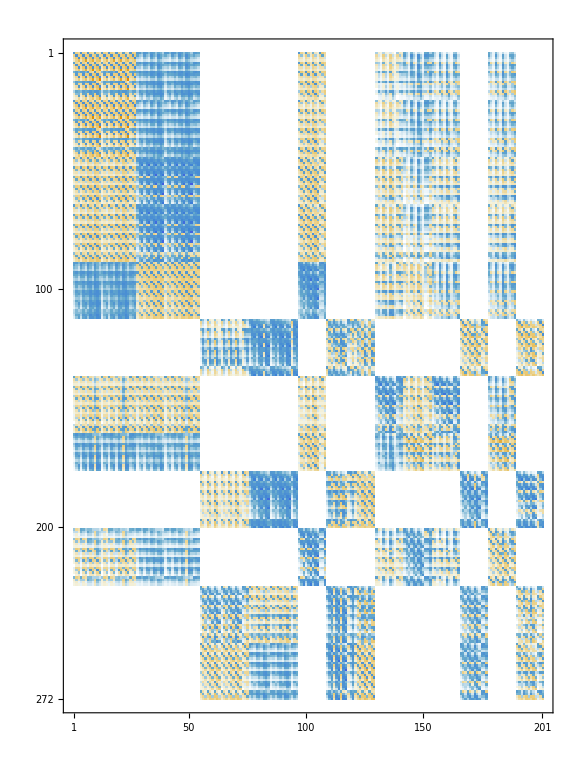
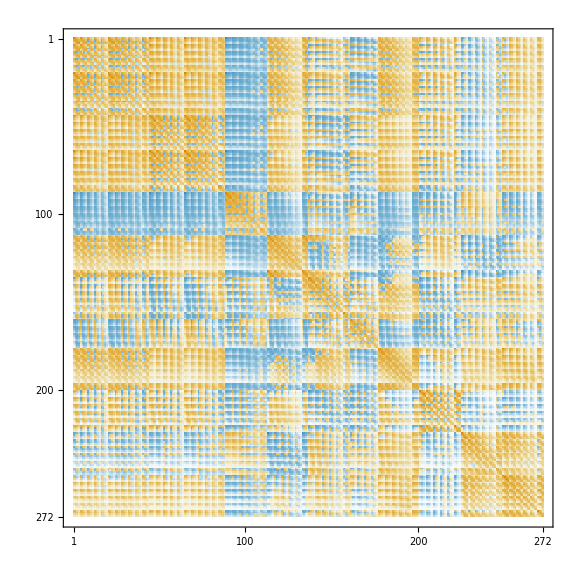
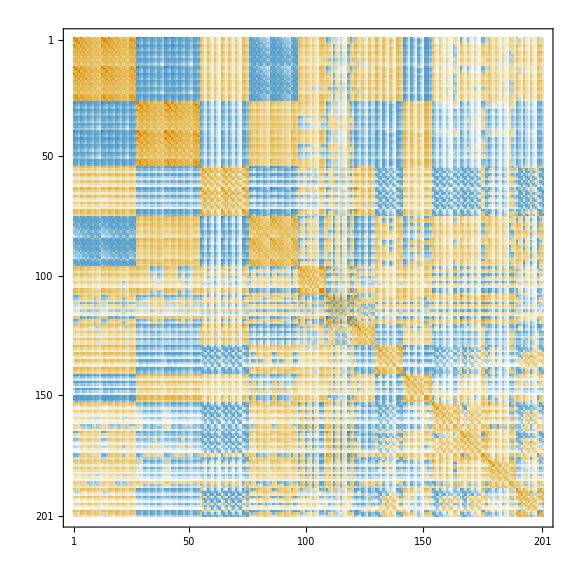
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
nb=1;nj=1;
Grid[{{
MatrixPlot[Chop[CouplingBlockjAs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Optimal Coupling}",Magnification->2],ImageSize->Large]
},{
MatrixPlot[Chop[FSHam[[nj]][[nb]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Final-state Hamiltonian}",Magnification->2],ImageSize->Large]
,
MatrixPlot[Chop[DHam],FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{D Hamiltonian}",Magnification->2],ImageSize->Large]
}}]
```

#### Analysis of RHS

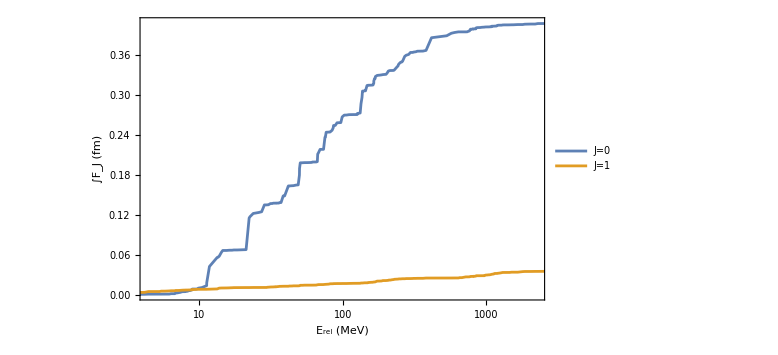

```mathematica
inhomoEBp=Table[{},{nj,Length[Subscript[I, n]]}];
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]}];
Do[(* final-state-J loop *)
Do[(* basis-scenario loop *)
Do[(* Subscript[m, L] loop *)
tmpt=Transpose[fulltrafosαβ[[nj]][[nb]]].CouplingBlockjAs[[nj]][[nb]][[mm]][[2]].fulltrafonm;
tmpf=Table[{
esysFS[[nj]][[nb]][[nfs]][[1]],
αfine/4.5 (esysFS[[nj]][[nb]][[nfs]][[2]].tmpt.evecGS)^2
},{nfs,1,FSDim}];

AppendTo[inhomoEB[[nj]],tmpf];

tmp=CouplingBlockjAs[[nj]][[nb]][[mm]][[2]];
tmpg=Table[{
esysFSp[[nj]][[nb]][[nfs]][[1]],
αfine/4.5 (esysFS[[nj]][[nb]][[nfs]][[2]].tmp.evecGS)^2
},{nfs,1,FSDimp}];

AppendTo[inhomoEBp[[nj]],tmpg];
,{mm,Range[1,Length[mIns[[nj]]]]}
];
,{nb,Range[anzBas]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
];
fns=Table[Transpose[{inhomoEB[[Inn]][[1]][[All,1]],Accumulate[inhomoEB[[Inn]][[1]][[All,2]]]}],{Inn,Range[1,Length[Subscript[I, n]]]}];
fnsp=Table[Transpose[{inhomoEBp[[Inn]][[1]][[All,1]],Accumulate[inhomoEBp[[Inn]][[1]][[All,2]]]}],{Inn,Range[1,Length[Subscript[I, n]]]}];
ListLogLinearPlot[Join[fns,fnsp],PlotRange->{{0,2250},All},ImageSize->Large,Frame->True,PlotRangePadding->0,FrameLabel->{"E_rel (MeV)","∫F_J (fm)"},LabelStyle->Large,Joined->True,PlotLegends->{"J=0","J=1","J=2","J=0 (OverBar[ONB])","J=1 (OverBar[ONB])","J=2 (OverBar[ONB])"}]
```